\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## BI-BEZ – Bezpečnost – Cvičení 2 Tomáš Zahradnický, Jiří Buček Katedra informační bezpečnosti, FIT ČVUT v Praze

Úvod do software Mathematica (opakování)

Substituční šifra

Afinní šifry

Transpoziční šifra

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Velejemný úvod do software Mathematica

Ve cvičeních bude využíván software Mathematica pro demonstraci šifer, jejich kryptoanalýzy, atd., a proto je důležité se se softwarem Mathematica naučit pracovat alespoň na nějaké základní bázi.

Mathematica je rozdělena na Front End (toto) a Kernel (není vidět). Front End posílá příkazy označené In[cislo] do kernelu a výstup z kernelu je označen Out[cislo]. Příkaz In[cislo] spustíte (pošlete do kernelu k vyhodnocení) pomocí klávesové kombinace SHIFT+ENTER, anebo ENTER na numerické klávesnici.

Před tím, než začneme, Mathematica je case sensitive a velmi dbá na typ závorek a proto pozor. Kulaté závorky označují prioritu vyhodnocování, hranaté určují argumenty funkce a složené označují vektory, matice a seznamy. Více viz dále.

Nyní zkuste vyhodnotit nasledující výrazy:

```mathematica
Mod[283,17]
```

11

```mathematica
Sin[Pi/2]
```

1

```mathematica
Sum[1/i^2,{i,1,∞}]
```

π^2/6

```mathematica
Mod[102*BEZInverse[102,113],113]
```

Mod[102 BEZInverse[102,113],113]

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Inicializace worksheetu

Aby bylo možné použít programy v těchno slajdech, je nutné provést inicializaci. Klepněte kamkoliv do bloku s programem a nechte ho vyhodnotit.  Blok obsahuje definice funkcí, které budou použity pro šifrování, dešifrování a analýzu. Není nutné se těmito funkcemi zaobírat.

```mathematica
<<"BarCharts`";
NCharacters=26;
SYMBOLS=Table[FromCharacterCode[65+i],{i,0,57}];
ENGLISH={0.0805726131341181993`1.9999999999999998,0.0125943599170806117`1.9999999999999998,0.0362576759103531896`1.9999999999999976,0.0380959831032189932`1.9999999999999998,0.1146790784996284273`1.9999999999999998,0.0240935581022411703`1.9999999999999998,0.0157233934368521923`1.9999999999999998,0.031212109359721516`1.9999999999999998,0.0741972073375836039`1.9999999999999998,0.001290726326905777`1.9999999999999998,0.0015254038408886455`1.9999999999999998,0.0429459850588649431`1.9999999999999998,0.0222943638283725115`1.9999999999999998,0.0746274494465521962`1.9999999999999998,0.0873782610396213869`1.9999999999999998,0.0389955802401533226`1.9999999999999998,0.0010169358939257637`1.9999999999999976,0.0751750303125122228`1.9999999999999998,0.0571830875738256346`1.9999999999999998,0.0912504400203387179`1.9999999999999998,0.0322290452536472797`1.9999999999999998,0.0081746000704032542`1.9999999999999998,0.0116165369421519928`1.9999999999999976,0.0017991942738686588`1.9999999999999998,0.0243282356162240388`1.9999999999999998,0.0007431454609457504`1.9999999999999998};
VelikostAbecedy[n_Integer]:=Module[{},NCharacters=n;Take[SYMBOLS,n]]
BEZRotChar[x_,amount_]:=FromCharacterCode[Mod[(ToCharacterCode[x]-ToCharacterCode["A"])+amount,NCharacters]+ToCharacterCode["A"]]
AXPBChar[x_,a_,b_]:=FromCharacterCode[Mod[(ToCharacterCode[x]-ToCharacterCode["A"]) a+b,NCharacters]+ToCharacterCode["A"]]
AXPB::notcoprime="Multiplicativni koefficient je soudelny s modulem. Informace bude ztracena.";
AXPB[x_String,a_,b_]:=Block[{},If[GCD[a,NCharacters]≠1,Message[AXPB::notcoprime]];StringJoin[(AXPBChar[#1,a,b]&)/@Characters[BEZPrepText[x]]]];
AXPBDecrypt[x_String,a_,b_]:=StringJoin[(AXPBCharDecrypt[#1,a,b]&)/@Characters[x]]
BEZZnakPlusB[x_String,b_Integer]:=(BEZRotChar[#1,b]&)/@Characters[x]
AXPBCharDecrypt[x_,a_,b_]:=FromCharacterCode[Mod[((ToCharacterCode[x]-ToCharacterCode["A"])-b) BEZInverse[a,NCharacters],NCharacters]+ToCharacterCode["A"]]
BEZInverse[x_Integer,mod_]:=Inverse[{{x}},Modulus->mod]⟦1⟧⟦1⟧
Caesar[x_String,posun_]:=StringJoin[BEZZnakPlusB[x,posun]]
BEZPrepText[x_String]:=FromCharacterCode[Select[(#1⟦1⟧&)/@ToCharacterCode[Characters[ToUpperCase[x]]],0≤#1-ToCharacterCode["A"]⟦1⟧≤NCharacters&]]
BEZAbsCetnosti[x_String]:=Table[Length[Select[Characters[BEZPrepText[x]],#1===SYMBOLS⟦i⟧&]],{i,1,NCharacters}]
BEZRelCetnosti[x_String]:=N[BEZAbsCetnosti[x]/StringLength[BEZPrepText[x]],2]

RelCetnosti[x_String]:=TableForm[Module[{X},X=BEZRelCetnosti[x];Append[Table[Table[{SYMBOLS⟦7 i+j⟧,X⟦7 i+j⟧},{j,1,7}],{i,0,-1+Floor[NCharacters/7]}],Table[{SYMBOLS⟦7 Floor[NCharacters/7]+i⟧,X⟦7 Floor[NCharacters/7]+i⟧},{i,1,Mod[NCharacters,7]}]]]]
BEZGrafyRelCetnosti[x_String,y_String]:=Module[{RC1,RC2},RC1=BEZRelCetnosti[x];RC2=BEZRelCetnosti[y];BarChart[{RC1,RC2},BarLabels->SYMBOLS,BarEdges->False,BarStyle->{Directive[RGBColor[.1,.2,.7],Opacity[0.7]],Directive[RGBColor[0,.7,0],Opacity[0.7]]},BarSpacing->0.1,Background->GrayLevel[.9]]]
BEZGrafyRelCetnostiSAnglictinou[x_String]:=Module[{RC1,RC2},RC1=BEZRelCetnosti[x];RC2=ENGLISH;BarChart[{RC1,RC2},BarLabels->SYMBOLS,BarEdges->False,BarStyle->{Directive[RGBColor[.1,.2,.7],Opacity[0.7]],Directive[RGBColor[0,.7,0],Opacity[0.7]]},BarSpacing->0.1,Background->GrayLevel[.9]]]
RelCetnostiZBEZRelCetnosti[x_]:=TableForm[{Table[{FromCharacterCode[64+i],x⟦i⟧},{i,7}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,8,14}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,15,21}],Table[{FromCharacterCode[64+i],x⟦i⟧},{i,22,26}]}]
Pozice[x_String]:=StringPosition[StringJoin[SYMBOLS],x]⟦1⟧⟦1⟧-1
BEZPadString[x_String,n_Integer]:=If[StringLength[x]<n,BEZPadString[StringJoin[x,"X"],n], If[StringLength[x]==n, x, Abort[]]]
BEZNumToPad[x_String,cols_Integer]:=Floor[(StringLength[x]+cols-1)/cols]*cols
BEZGenerMatrix[x_String,cols_Integer]:=Partition[Characters[BEZPadString[BEZPrepText[x],BEZNumToPad[BEZPrepText[x],cols]]],cols]
Transpozice[x_String,cols_Integer]:=StringJoin[Flatten[Transpose[BEZGenerMatrix[BEZPrepText[x],cols]]]]

Print["Initialization done"]
```

General::obspkg: BarCharts` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Initialization done

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Jednoduché šifry (Caesarova šifra)

Caesarova šifra je známá jako jednoduchá substituční proudová (znaková) šifra, která provádí transformaci y = |x+3|_26. Mějme otevřený text (nechte vyhodnotit)

```mathematica
OT:="NEVERGONNAGIVEYOUUP"
```

Zašifrovaný text bude:

```mathematica
ST=Caesar[OT,3]
```

QHYHUJRQQDJLYHBRXXS

```mathematica
"XAEMIZMBWJMUIZZQMLWVAMXBMUJMZLZAMEIZLALQIZGICOCABBPMKIAMWNZMVNQMTLOZWEAMDMVUWZMQVBMZMABQVOPMPIAVWEAWNIZYCQMBMLBPIBBPMZMIZMAXMTTAWNKMAAIBQWVNZWUPQAXIAA"
```

XAEMIZMBWJMUIZZQMLWVAMXBMUJMZLZAMEIZLALQIZGICOCABBPMKIAMWNZMVNQMTLOZWEAMDMVUWZMQVBMZMABQVOPMPIAVWEAWNIZYCQMBMLBPIBBPMZMIZMAXMTTAWNKMAAIBQWVNZWUPQAXIAA

Text lze snadno dešifrovat provedením opačné operace (odečtením) posunu:

```mathematica
Caesar[ST,-3]
```

NEVERGONNAGIVEYOUUP

Kryptoanalýzu této šifry naleznete na další stránce.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalýza Caesarovy šifry

Relativní četnosti šifrového textu z minulého slajdu jsou:

```mathematica
RelCetnosti[ST]
```

A
0 | B
0.053 | C
0 | D
0.053 | E
0 | F
0 | G
0
H
0.16 | I
0 | J
0.11 | K
0 | L
0.053 | M
0 | N
0
O
0 | P
0 | Q
0.16 | R
0.11 | S
0.053 | T
0 | U
0.053
V
0 | W
0 | X
0.11 | Y
0.11 | Z
0 |  |

Relativní četnosti otevřeného textu z minulého slajdu jsou:

```mathematica
RelCetnosti[OT]
```

A
0.053 | B
0 | C
0 | D
0 | E
0.16 | F
0 | G
0.11
H
0 | I
0.053 | J
0 | K
0 | L
0 | M
0 | N
0.16
O
0.11 | P
0.053 | Q
0 | R
0.053 | S
0 | T
0 | U
0.11
V
0.11 | W
0 | X
0 | Y
0.053 | Z
0 |  |

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalýza Caesarovy šifry (2)

Srovnáním relativních četností (modrá pro šifrový text, zelená pro otevřený text) vidíme, že šifra způsobila posun relativních četností následujícím způsobem:

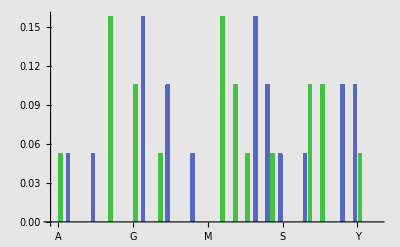

```mathematica
BEZGrafyRelCetnosti[ST,OT]
```

Z grafu vidíme, že pokud známe otevřený text, je velmi snadné uhodnout transformaci, která povede k dešifrování textu. Stačí jen posunout četnosti tak, aby grafy splynuly. Pokud otevřený text k dispozici nemáme, musíme si vystačit například se vzorkem relativních četností pro jazyk, kterým předpokládáme, že je šifrový text psán. Předpokládáme, že šifrový text je psán v angličtině, pro kterou máme relativní četnosti uložené v proměnné ENGLISH.

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalýza Caesarovy šifry (3)

Relativní četnosti pro angličtinu jsou (získáno jako relativní četnosti z cca 20 KB souboru):

```mathematica
RelCetnostiZBEZRelCetnosti[ENGLISH]
```

A
0.081 | B
0.013 | C
0.036 | D
0.038 | E
0.11 | F
0.024 | G
0.016
H
0.031 | I
0.074 | J
0.0013 | K
0.0015 | L
0.043 | M
0.022 | N
0.075
O
0.087 | P
0.039 | Q
0.001 | R
0.075 | S
0.057 | T
0.091 | U
0.032
V
0.0082 | W
0.012 | X
0.0018 | Y
0.024 | Z
0.00074 |  |

Nyní můžeme udělat stejný krok, jako v minulém případě a srovnat relativní četnosti šifrového textu s relativními četnostmi pro angličtinu:

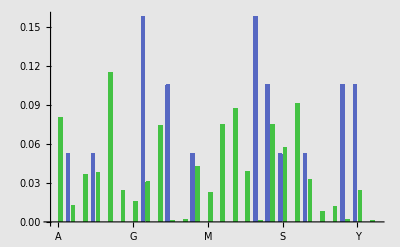

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 1: Zjistěte, co se skrývá pod následujícím šifrovým textem

Neznámý šifrový text ST je:

```mathematica
ST="UXBJFWJYTGJRFWWNJITSXJUYJRGJWIWXJBFWIXINFWDFZLZXYYMJHFXJTKWJSKNJQILWTBXJAJSRTWJNSYJWJXYNSLMJMFXSTBXTKFWVZNJYJIYMFYYMJWJFWJXUJQQXTKHJXXFYNTSKWTRMNXUFXX"
```

UXBJFWJYTGJRFWWNJITSXJUYJRGJWIWXJBFWIXINFWDFZLZXYYMJHFXJTKWJSKNJQILWTBXJAJSRTWJNSYJWJXYNSLMJMFXSTBXTKFWVZNJYJIYMFYYMJWJFWJXUJQQXTKHJXXFYNTSKWTRMNXUFXX

Proveďte analýzu relativních četností a nalezněte k němu otevřený text. Jde o šifru podobnou Caesarově šifře.

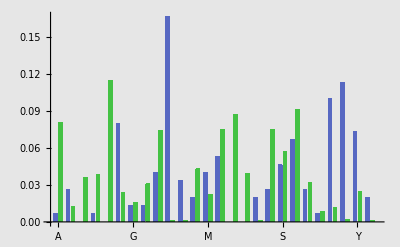

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
```

Návod: Srovnejte relativní četnost. Proměnná ST je globální, takže můžete použít pomůcky uvedené na předchozích slajdech.

```mathematica
mujPopularni="J";
ajPopularni="E";
vzdalenost = Pozice[mujPopularni]-Pozice[ajPopularni]
Caesar[ST,-vzdalenost]
```

5

PSWEARETOBEMARRIEDONSEPTEMBERDRSEWARDSDIARYAUGUSTTHECASEOFRENFIELDGROWSEVENMOREINTERESTINGHEHASNOWSOFARQUIETEDTHATTHEREARESPELLSOFCESSATIONFROMHISPASS

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Šifry typu |ap+b|_m

Caesarova šifra je speciálním případem afinní šifry |ap+b|_m a je definována jako |p+b|_m. Šifra též představuje substituci, avšak nyní již tato substituce neposunuje graf relativních četností, ale dochází k důkladnějšímu "promíchání" (viz graf relativních četností). Celou věc si ukažme na příkladu:

```mathematica
OT="THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER"
```

THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER

```mathematica
ST=AXPB[OT,5,19]
```

KCHFHFJNKTGLKCNADHQCNAKNEKKCTKZNZHWWNGDHQCNA

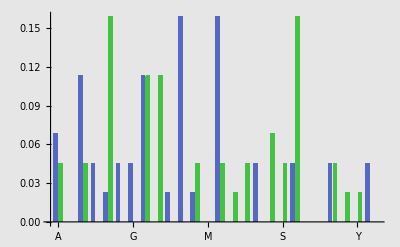

```mathematica
BEZGrafyRelCetnosti[ST,OT]
```

Šifrový text můžeme dešifrovat obrácením šifrovacího předpisu a to je-li y=|ap+b|_mbude p=|a^-1(y-b)|_m.

```mathematica
AXPBDecrypt[ST,5,19]
```

THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER

Můžeme ale využít i původní předpis (formu násobení, sčítání) p=|□ c + □|_m. Jak to dokážeme? Napište obecný výraz (pomocí dosazení). Konkrétně:

```mathematica
AXPB[ST,21,17]
aInverse = BEZInverse[5, 26]
bTransform = Mod[-1 *aInverse*19, 26]
AXPB[ST, aInverse, bTransform]
Print["Ejhle, shoda"]
```

THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER

21

17

THISISYETANOTHERCIPHERTEXTTHATWEWILLENCIPHER

Ejhle, shoda

Kolik existuje různých klíčů pro abecedu o m znacích?

```mathematica
Print["Posunů je vždy m, tudíž krát m"]
Print["Konstant a může být jako hodnota Eulerovy fce pro m (potřebujeme inverzi)"]
Print["Výsledek pronásobéme"]
m = 26;
EulerPhi[m]*m
```

Posunů je vždy m, tudíž krát m

Konstant a může být jako hodnota Eulerovy fce pro m (potřebujeme inverzi)

Výsledek pronásobéme

312

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 2: Kryptoanalýza šifry |ap+b|_m

1. Vyberte náhodné konstanty a a b a s nimi anglický text alespoň o 100 znacích. Takový text můžete nalézt například v libovolné dokumentaci k software. Až budete mít šifrový text, poskytněte ho sousedovi (např. e-mailem), ale nesdělujte mu hodnoty konstant!

```mathematica
OT="NEVERGONNAGIVEYOUUPNEVERGONNALETYOUDOWNNEVERGONNARUNAROUNDANDDESERTYOUNEVERGONNAMAKEYOUCRYNEVERGONNASAYGOODBYENEVERGONNATELLALIEANDHURTYOU";
a=19;
b=6;
```

```mathematica
ST=AXPB[OT,a,b]
```

TEPERQMTTGQCPEUMWWFTEPERQMTTGHEDUMWLMITTEPERQMTTGRWTGRMWTLGTLLEKERDUMWTEPERQMTTGAGOEUMWSRUTEPERQMTTGKGUQMMLZUETEPERQMTTGDEHHGHCEGTLJWRDUMW

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 2: Kryptoanalýza šifry |ap+b|_m (2)

2. Až obdržíte šifrový text od souseda, přiřaďte jeho hodnotu do proměnné ST:

```mathematica
ST="JPBNDGAONBNQTDGKQHYMHRGYBNQUMDCQQICPAJJGPCFQSKCPJGUBMHOUHRSMDSJMHOMHBNQRDUAONBPDGIBNQYMHRGYUHRBNQJMONBCTADHTJAQUHRRMIYNUBUIMBGRGOGRCNMQJRIQPDGINUDIBNMCHMONBMCNUJJNMRQBNMCFUFQDMHIWTDQUCBYNQDQBNQWCNUJJPMHRMBYNQHBNQWSGIQBGJUWIQGABIWRQUDIGBNQDOGHQMBMCBMIQBNUBMOGBGGOGGRTWQRQUDUDBNADMPMCNGAJRHGBCADZMZQBNMCHMONBOGRKQQFWGARQUDUHROGRNQJFIQSNUFBQDXMMRDCQYUDRCRMUDWCQFBQITQDMRDGZQUBGHSQBGNMJJMHONUIUHRUDDMZQRQUDJWKQQFMHOIWSUTUBBNQOUBQMYQHBAFBNQUZQHAQUJGHQMKHGSKQROQHBJWUHRDUHOUCEAMQBJWUCFGCCMTJQPGDMPQUDQRBGRMCBADTJASWGDNQDIGBNQDUHRNGFQRBGGHJWTDMHOUCQDZUHBBGBNQRGGDUPBQDUYNMJQPMHRMHOHGDQCFGHCQMKHGSKQRUHRDUHOUOUMHCBMJJHGUHCYQDMSADCQRBNQJUVMHQCCGPBNQCQDZUHBCBNUBBNQWCNGAJRJMQUTQRUBCASNUHNGADPGDMBYUCHGYBQHGSJGSKUHRCGDUHOUHRKHGSKQRUOUMHTABIGDQMIFUBMQHBJWTABCBMJJYMBNGABDQCFGHCQNMBNQDBGMNURTJUIQRGHJWBNQCQDZUHBCT";
```

Nyní proveďte analýzu četnosti:

```mathematica
RelCetnosti[ST]
```

A
0.028 | B
0.088 | C
0.053 | D
0.064 | E
0.0013 | F
0.018 | G
0.075
H
0.071 | I
0.026 | J
0.045 | K
0.014 | L
0 | M
0.075 | N
0.064
O
0.03 | P
0.018 | Q
0.11 | R
0.055 | S
0.019 | T
0.019 | U
0.08
V
0.0013 | W
0.021 | X
0.0013 | Y
0.018 | Z
0.01 |  |

A srovnejte ji s četnostmi pro angličti
nu:

```mathematica
RelCetnostiZBEZRelCetnosti[ENGLISH]
```

A
0.081 | B
0.013 | C
0.036 | D
0.038 | E
0.11 | F
0.024 | G
0.016
H
0.031 | I
0.074 | J
0.0013 | K
0.0015 | L
0.043 | M
0.022 | N
0.075
O
0.087 | P
0.039 | Q
0.001 | R
0.075 | S
0.057 | T
0.091 | U
0.032
V
0.0082 | W
0.012 | X
0.0018 | Y
0.024 | Z
0.00074 |  |

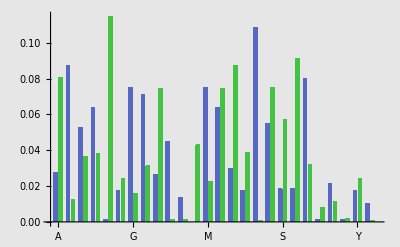

```mathematica
BEZGrafyRelCetnostiSAnglictinou[ST]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 2: KryptoanalÝza Šifry |ap+b|_m (3)

Z analýzy relativních četností můžeme zjistit, že nejčetnější písmena pro angličtinu jsou E a T. Toho můžeme využít pro zjištění dešifrovacího klíče. Vybereme tedy 2 nejčetnější písmena z analýzy šifrového textu a zkusíme je namapovat na E a T. Řešením soustavy 2 rovnic o 2 neznámých vypočteme neznámé koeficienty a a b.

Řekneme, že pro náš příklad vidíme, že nejčetnější jsou písmena H a M. Zkusme tedy předpokládat, že:
	H=|a E+b|_26
	M=|a T+b|_26
Tedy, z E neznámou transformací vznikne H a z T tou samou transformací vznikne M. Abychom určili a a b, musíme už jen vyřešit tyto dvě rovnice například dosazovací metodou:

b=|M-a T|_26
	H = |a E+|M-a T|_26|_26

Protože nezáleží, kdy redukci (mod 26) provedeme, můžeme vztah přepsat jako:
	H = |a ( E - T )+M|_26
	a =|(H-M)*(E-T)^-1|_26
	b = |H-a E|_26

Nyní můžeme předpis zkusit (pozn. pokud budete počítat na papíře, nezapomeňte, že A odpovídá 0, B 1, atd.):

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Úkol 2: Kryptoanalýza šifry |ap+b|_m (4)

Pro jednoduchost jsou zde rovnice implementovány do systému Mathematica a vypočtené konstanty se uloží do proměnných c a d.

Q B U -> E T A

```mathematica
letter1 ="Q"; 
letter2 = "B";
eng1="E";
eng2="T";
c=Mod[(Pozice[letter1]-Pozice[letter2])*BEZInverse[Pozice[eng1]-Pozice[eng2],NCharacters],NCharacters]
d=Mod[Pozice[letter1]-c*Pozice[eng1],NCharacters]
```

25

20

Nebo můžeme nechat všechnu těžkou práci na Mathematice:

```mathematica
s=Solve[{
Pozice[letter1]==cc*Pozice[eng1]+dd,
Pozice[letter2]==cc*Pozice[eng2]+dd
}, Modulus->NCharacters]
{c,d}={cc,dd}/.s[[1]]
```

{{dd→20,cc→25}}

{25,20}

Nyní se můžeme pokusit text dešifrovat:

```mathematica
AXPBDecrypt[ST,c,d]
```

LFTHROUGHTHEBROKENWINDOWTHEAIRSEEMSFULLOFSPECKSFLOATINGANDCIRCLINGINTHEDRAUGHTFROMTHEWINDOWANDTHELIGHTSBURNBLUEANDDIMWHATAMITODOGODSHIELDMEFROMHARMTHISNIGHTISHALLHIDETHISPAPERINMYBREASTWHERETHEYSHALLFINDITWHENTHEYCOMETOLAYMEOUTMYDEARMOTHERGONEITISTIMETHATIGOTOOGOODBYEDEARARTHURIFISHOULDNOTSURVIVETHISNIGHTGODKEEPYOUDEARANDGODHELPMECHAPTERXIIDRSEWARDSDIARYSEPTEMBERIDROVEATONCETOHILLINGHAMANDARRIVEDEARLYKEEPINGMYCABATTHEGATEIWENTUPTHEAVENUEALONEIKNOCKEDGENTLYANDRANGASQUIETLYASPOSSIBLEFORIFEAREDTODISTURBLUCYORHERMOTHERANDHOPEDTOONLYBRINGASERVANTTOTHEDOORAFTERAWHILEFINDINGNORESPONSEIKNOCKEDANDRANGAGAINSTILLNOANSWERICURSEDTHELAZINESSOFTHESERVANTSTHATTHEYSHOULDLIEABEDATSUCHANHOURFORITWASNOWTENOCLOCKANDSORANGANDKNOCKEDAGAINBUTMOREIMPATIENTLYBUTSTILLWITHOUTRESPONSEHITHERTOIHADBLAMEDONLYTHESERVANTSB

```mathematica
Print["Didn't help, to lazy to look for it"]
For[a =0, a < 26,a++,
For[b =0, b < 26,b++,
If[GCD[a,26]==1,Print[a," ",b,AXPBDecrypt[ST,a,b]]]
]
]
```

Didn't help, to lazy to look for it

1 0JPBNDGAONBNQTDGKQHYMHRGYBNQUMDCQQICPAJJGPCFQSKCPJGUBMHOUHRSMDSJMHOMHBNQRDUAONBPDGIBNQYMHRGYUHRBNQJMONBCTADHTJAQUHRRMIYNUBUIMBGRGOGRCNMQJRIQPDGINUDIBNMCHMONBMCNUJJNMRQBNMCFUFQDMHIWTDQUCBYNQDQBNQWCNUJJPMHRMBYNQHBNQWSGIQBGJUWIQGABIWRQUDIGBNQDOGHQMBMCBMIQBNUBMOGBGGOGGRTWQRQUDUDBNADMPMCNGAJRHGBCADZMZQBNMCHMONBOGRKQQFWGARQUDUHROGRNQJFIQSNUFBQDXMMRDCQYUDRCRMUDWCQFBQITQDMRDGZQUBGHSQBGNMJJMHONUIUHRUDDMZQRQUDJWKQQFMHOIWSUTUBBNQOUBQMYQHBAFBNQUZQHAQUJGHQMKHGSKQROQHBJWUHRDUHOUCEAMQBJWUCFGCCMTJQPGDMPQUDQRBGRMCBADTJASWGDNQDIGBNQDUHRNGFQRBGGHJWTDMHOUCQDZUHBBGBNQRGGDUPBQDUYNMJQPMHRMHOHGDQCFGHCQMKHGSKQRUHRDUHOUOUMHCBMJJHGUHCYQDMSADCQRBNQJUVMHQCCGPBNQCQDZUHBCBNUBBNQWCNGAJRJMQUTQRUBCASNUHNGADPGDMBYUCHGYBQHGSJGSKUHRCGDUHOUHRKHGSKQRUOUMHTABIGDQMIFUBMQHBJWTABCBMJJYMBNGABDQCFGHCQNMBNQDBGMNURTJUIQRGHJWBNQCQDZUHBCT

1 1IOAMCFZNMAMPSCFJPGXLGQFXAMPTLCBPPHBOZIIFOBEPRJBOIFTALGNTGQRLCRILGNLGAMPQCTZNMAOCFHAMPXLGQFXTGQAMPILNMABSZCGSIZPTGQQLHXMTATHLAFQFNFQBMLPIQHPOCFHMTCHAMLBGLNMALBMTIIMLQPAMLBETEPCLGHVSCPTBAXMPCPAMPVBMTIIOLGQLAXMPGAMPVRFHPAFITVHPFZAHVQPTCHFAMPCNFGPLALBALHPAMTALNFAFFNFFQSVPQPTCTCAMZCLOLBMFZIQGFABZCYLYPAMLBGLNMANFQJPPEVFZQPTCTGQNFQMPIEHPRMTEAPCWLLQCBPXTCQBQLTCVBPEAPHSPCLQCFYPTAFGRPAFMLIILGNMTHTGQTCCLYPQPTCIVJPPELGNHVRTSTAAMPNTAPLXPGAZEAMPTYPGZPTIFGPLJGFRJPQNPGAIVTGQCTGNTBDZLPAIVTBEFBBLSIPOFCLOPTCPQAFQLBAZCSIZRVFCMPCHFAMPCTGQMFEPQAFFGIVSCLGNTBPCYTGAAFAMPQFFCTOAPCTXMLIPOLGQLGNGFCPBEFGBPLJGFRJPQTGQCTGNTNTLGBALIIGFTGBXPCLRZCBPQAMPITULGPBBFOAMPBPCYTGABAMTAAMPVBMFZIQILPTSPQTABZRMTGMFZCOFCLAXTBGFXAPGFRIFRJTGQBFCTGNTGQJGFRJPQTNTLGSZAHFCPLHETALPGAIVSZABALIIXLAMFZACPBEFGBPMLAMPCAFLMTQSITHPQFGIVAMPBPCYTGABS

1 2HNZLBEYMLZLORBEIOFWKFPEWZLOSKBAOOGANYHHENADOQIANHESZKFMSFPQKBQHKFMKFZLOPBSYMLZNBEGZLOWKFPEWSFPZLOHKMLZARYBFRHYOSFPPKGWLSZSGKZEPEMEPALKOHPGONBEGLSBGZLKAFKMLZKALSHHLKPOZLKADSDOBKFGURBOSAZWLOBOZLOUALSHHNKFPKZWLOFZLOUQEGOZEHSUGOEYZGUPOSBGEZLOBMEFOKZKAZKGOZLSZKMEZEEMEEPRUOPOSBSBZLYBKNKALEYHPFEZAYBXKXOZLKAFKMLZMEPIOODUEYPOSBSFPMEPLOHDGOQLSDZOBVKKPBAOWSBPAPKSBUAODZOGROBKPBEXOSZEFQOZELKHHKFMLSGSFPSBBKXOPOSBHUIOODKFMGUQSRSZZLOMSZOKWOFZYDZLOSXOFYOSHEFOKIFEQIOPMOFZHUSFPBSFMSACYKOZHUSADEAAKRHONEBKNOSBOPZEPKAZYBRHYQUEBLOBGEZLOBSFPLEDOPZEEFHURBKFMSAOBXSFZZEZLOPEEBSNZOBSWLKHONKFPKFMFEBOADEFAOKIFEQIOPSFPBSFMSMSKFAZKHHFESFAWOBKQYBAOPZLOHSTKFOAAENZLOAOBXSFZAZLSZZLOUALEYHPHKOSROPSZAYQLSFLEYBNEBKZWSAFEWZOFEQHEQISFPAEBSFMSFPIFEQIOPSMSKFRYZGEBOKGDSZKOFZHURYZAZKHHWKZLEYZBOADEFAOLKZLOBZEKLSPRHSGOPEFHUZLOAOBXSFZAR

1 3GMYKADXLKYKNQADHNEVJEODVYKNRJAZNNFZMXGGDMZCNPHZMGDRYJELREOPJAPGJELJEYKNOARXLKYMADFYKNVJEODVREOYKNGJLKYZQXAEQGXNREOOJFVKRYRFJYDODLDOZKJNGOFNMADFKRAFYKJZEJLKYJZKRGGKJONYKJZCRCNAJEFTQANRZYVKNANYKNTZKRGGMJEOJYVKNEYKNTPDFNYDGRTFNDXYFTONRAFDYKNALDENJYJZYJFNYKRYJLDYDDLDDOQTNONRARAYKXAJMJZKDXGOEDYZXAWJWNYKJZEJLKYLDOHNNCTDXONRAREOLDOKNGCFNPKRCYNAUJJOAZNVRAOZOJRATZNCYNFQNAJOADWNRYDEPNYDKJGGJELKRFREORAAJWNONRAGTHNNCJELFTPRQRYYKNLRYNJVNEYXCYKNRWNEXNRGDENJHEDPHNOLNEYGTREOARELRZBXJNYGTRZCDZZJQGNMDAJMNRANOYDOJZYXAQGXPTDAKNAFDYKNAREOKDCNOYDDEGTQAJELRZNAWREYYDYKNODDARMYNARVKJGNMJEOJELEDANZCDEZNJHEDPHNOREOARELRLRJEZYJGGEDREZVNAJPXAZNOYKNGRSJENZZDMYKNZNAWREYZYKRYYKNTZKDXGOGJNRQNORYZXPKREKDXAMDAJYVRZEDVYNEDPGDPHREOZDARELREOHEDPHNORLRJEQXYFDANJFCRYJNEYGTQXYZYJGGVJYKDXYANZCDEZNKJYKNAYDJKROQGRFNODEGTYKNZNAWREYZQ

1 4FLXJZCWKJXJMPZCGMDUIDNCUXJMQIZYMMEYLWFFCLYBMOGYLFCQXIDKQDNOIZOFIDKIDXJMNZQWKJXLZCEXJMUIDNCUQDNXJMFIKJXYPWZDPFWMQDNNIEUJQXQEIXCNCKCNYJIMFNEMLZCEJQZEXJIYDIKJXIYJQFFJINMXJIYBQBMZIDESPZMQYXUJMZMXJMSYJQFFLIDNIXUJMDXJMSOCEMXCFQSEMCWXESNMQZECXJMZKCDMIXIYXIEMXJQXIKCXCCKCCNPSMNMQZQZXJWZILIYJCWFNDCXYWZVIVMXJIYDIKJXKCNGMMBSCWNMQZQDNKCNJMFBEMOJQBXMZTIINZYMUQZNYNIQZSYMBXMEPMZINZCVMQXCDOMXCJIFFIDKJQEQDNQZZIVMNMQZFSGMMBIDKESOQPQXXJMKQXMIUMDXWBXJMQVMDWMQFCDMIGDCOGMNKMDXFSQDNZQDKQYAWIMXFSQYBCYYIPFMLCZILMQZMNXCNIYXWZPFWOSCZJMZECXJMZQDNJCBMNXCCDFSPZIDKQYMZVQDXXCXJMNCCZQLXMZQUJIFMLIDNIDKDCZMYBCDYMIGDCOGMNQDNZQDKQKQIDYXIFFDCQDYUMZIOWZYMNXJMFQRIDMYYCLXJMYMZVQDXYXJQXXJMSYJCWFNFIMQPMNQXYWOJQDJCWZLCZIXUQYDCUXMDCOFCOGQDNYCZQDKQDNGDCOGMNQKQIDPWXECZMIEBQXIMDXFSPWXYXIFFUIXJCWXZMYBCDYMJIXJMZXCIJQNPFQEMNCDFSXJMYMZVQDXYP

1 5EKWIYBVJIWILOYBFLCTHCMBTWILPHYXLLDXKVEEBKXALNFXKEBPWHCJPCMNHYNEHCJHCWILMYPVJIWKYBDWILTHCMBTPCMWILEHJIWXOVYCOEVLPCMMHDTIPWPDHWBMBJBMXIHLEMDLKYBDIPYDWIHXCHJIWHXIPEEIHMLWIHXAPALYHCDROYLPXWTILYLWILRXIPEEKHCMHWTILCWILRNBDLWBEPRDLBVWDRMLPYDBWILYJBCLHWHXWHDLWIPWHJBWBBJBBMORLMLPYPYWIVYHKHXIBVEMCBWXVYUHULWIHXCHJIWJBMFLLARBVMLPYPCMJBMILEADLNIPAWLYSHHMYXLTPYMXMHPYRXLAWLDOLYHMYBULPWBCNLWBIHEEHCJIPDPCMPYYHULMLPYERFLLAHCJDRNPOPWWILJPWLHTLCWVAWILPULCVLPEBCLHFCBNFLMJLCWERPCMYPCJPXZVHLWERPXABXXHOELKBYHKLPYLMWBMHXWVYOEVNRBYILYDBWILYPCMIBALMWBBCEROYHCJPXLYUPCWWBWILMBBYPKWLYPTIHELKHCMHCJCBYLXABCXLHFCBNFLMPCMYPCJPJPHCXWHEECBPCXTLYHNVYXLMWILEPQHCLXXBKWILXLYUPCWXWIPWWILRXIBVEMEHLPOLMPWXVNIPCIBVYKBYHWTPXCBTWLCBNEBNFPCMXBYPCJPCMFCBNFLMPJPHCOVWDBYLHDAPWHLCWEROVWXWHEETHWIBVWYLXABCXLIHWILYWBHIPMOEPDLMBCERWILXLYUPCWXO

1 6DJVHXAUIHVHKNXAEKBSGBLASVHKOGXWKKCWJUDDAJWZKMEWJDAOVGBIOBLMGXMDGBIGBVHKLXOUIHVJXACVHKSGBLASOBLVHKDGIHVWNUXBNDUKOBLLGCSHOVOCGVALAIALWHGKDLCKJXACHOXCVHGWBGIHVGWHODDHGLKVHGWZOZKXGBCQNXKOWVSHKXKVHKQWHODDJGBLGVSHKBVHKQMACKVADOQCKAUVCQLKOXCAVHKXIABKGVGWVGCKVHOVGIAVAAIAALNQKLKOXOXVHUXGJGWHAUDLBAVWUXTGTKVHGWBGIHVIALEKKZQAULKOXOBLIALHKDZCKMHOZVKXRGGLXWKSOXLWLGOXQWKZVKCNKXGLXATKOVABMKVAHGDDGBIHOCOBLOXXGTKLKOXDQEKKZGBICQMONOVVHKIOVKGSKBVUZVHKOTKBUKODABKGEBAMEKLIKBVDQOBLXOBIOWYUGKVDQOWZAWWGNDKJAXGJKOXKLVALGWVUXNDUMQAXHKXCAVHKXOBLHAZKLVAABDQNXGBIOWKXTOBVVAVHKLAAXOJVKXOSHGDKJGBLGBIBAXKWZABWKGEBAMEKLOBLXOBIOIOGBWVGDDBAOBWSKXGMUXWKLVHKDOPGBKWWAJVHKWKXTOBVWVHOVVHKQWHAUDLDGKONKLOVWUMHOBHAUXJAXGVSOWBASVKBAMDAMEOBLWAXOBIOBLEBAMEKLOIOGBNUVCAXKGCZOVGKBVDQNUVWVGDDSGVHAUVXKWZABWKHGVHKXVAGHOLNDOCKLABDQVHKWKXTOBVWN

1 7CIUGWZTHGUGJMWZDJARFAKZRUGJNFWVJJBVITCCZIVYJLDVICZNUFAHNAKLFWLCFAHFAUGJKWNTHGUIWZBUGJRFAKZRNAKUGJCFHGUVMTWAMCTJNAKKFBRGNUNBFUZKZHZKVGFJCKBJIWZBGNWBUGFVAFHGUFVGNCCGFKJUGFVYNYJWFABPMWJNVURGJWJUGJPVGNCCIFAKFURGJAUGJPLZBJUZCNPBJZTUBPKJNWBZUGJWHZAJFUFVUFBJUGNUFHZUZZHZZKMPJKJNWNWUGTWFIFVGZTCKAZUVTWSFSJUGFVAFHGUHZKDJJYPZTKJNWNAKHZKGJCYBJLGNYUJWQFFKWVJRNWKVKFNWPVJYUJBMJWFKWZSJNUZALJUZGFCCFAHGNBNAKNWWFSJKJNWCPDJJYFAHBPLNMNUUGJHNUJFRJAUTYUGJNSJATJNCZAJFDAZLDJKHJAUCPNAKWNAHNVXTFJUCPNVYZVVFMCJIZWFIJNWJKUZKFVUTWMCTLPZWGJWBZUGJWNAKGZYJKUZZACPMWFAHNVJWSNAUUZUGJKZZWNIUJWNRGFCJIFAKFAHAZWJVYZAVJFDAZLDJKNAKWNAHNHNFAVUFCCAZNAVRJWFLTWVJKUGJCNOFAJVVZIUGJVJWSNAUVUGNUUGJPVGZTCKCFJNMJKNUVTLGNAGZTWIZWFURNVAZRUJAZLCZLDNAKVZWNAHNAKDAZLDJKNHNFAMTUBZWJFBYNUFJAUCPMTUVUFCCRFUGZTUWJVYZAVJGFUGJWUZFGNKMCNBJKZACPUGJVJWSNAUVM

1 8BHTFVYSGFTFILVYCIZQEZJYQTFIMEVUIIAUHSBBYHUXIKCUHBYMTEZGMZJKEVKBEZGEZTFIJVMSGFTHVYATFIQEZJYQMZJTFIBEGFTULSVZLBSIMZJJEAQFMTMAETYJYGYJUFEIBJAIHVYAFMVATFEUZEGFTEUFMBBFEJITFEUXMXIVEZAOLVIMUTQFIVITFIOUFMBBHEZJETQFIZTFIOKYAITYBMOAIYSTAOJIMVAYTFIVGYZIETEUTEAITFMTEGYTYYGYYJLOIJIMVMVTFSVEHEUFYSBJZYTUSVRERITFEUZEGFTGYJCIIXOYSJIMVMZJGYJFIBXAIKFMXTIVPEEJVUIQMVJUJEMVOUIXTIALIVEJVYRIMTYZKITYFEBBEZGFMAMZJMVVERIJIMVBOCIIXEZGAOKMLMTTFIGMTIEQIZTSXTFIMRIZSIMBYZIECZYKCIJGIZTBOMZJVMZGMUWSEITBOMUXYUUELBIHYVEHIMVIJTYJEUTSVLBSKOYVFIVAYTFIVMZJFYXIJTYYZBOLVEZGMUIVRMZTTYTFIJYYVMHTIVMQFEBIHEZJEZGZYVIUXYZUIECZYKCIJMZJVMZGMGMEZUTEBBZYMZUQIVEKSVUIJTFIBMNEZIUUYHTFIUIVRMZTUTFMTTFIOUFYSBJBEIMLIJMTUSKFMZFYSVHYVETQMUZYQTIZYKBYKCMZJUYVMZGMZJCZYKCIJMGMEZLSTAYVIEAXMTEIZTBOLSTUTEBBQETFYSTVIUXYZUIFETFIVTYEFMJLBMAIJYZBOTFIUIVRMZTUL

1 9AGSEUXRFESEHKUXBHYPDYIXPSEHLDUTHHZTGRAAXGTWHJBTGAXLSDYFLYIJDUJADYFDYSEHIULRFESGUXZSEHPDYIXPLYISEHADFESTKRUYKARHLYIIDZPELSLZDSXIXFXITEDHAIZHGUXZELUZSEDTYDFESDTELAAEDIHSEDTWLWHUDYZNKUHLTSPEHUHSEHNTELAAGDYIDSPEHYSEHNJXZHSXALNZHXRSZNIHLUZXSEHUFXYHDSDTSDZHSELSDFXSXXFXXIKNHIHLULUSERUDGDTEXRAIYXSTRUQDQHSEDTYDFESFXIBHHWNXRIHLULYIFXIEHAWZHJELWSHUODDIUTHPLUITIDLUNTHWSHZKHUDIUXQHLSXYJHSXEDAADYFELZLYILUUDQHIHLUANBHHWDYFZNJLKLSSEHFLSHDPHYSRWSEHLQHYRHLAXYHDBYXJBHIFHYSANLYIULYFLTVRDHSANLTWXTTDKAHGXUDGHLUHISXIDTSRUKARJNXUEHUZXSEHULYIEXWHISXXYANKUDYFLTHUQLYSSXSEHIXXULGSHULPEDAHGDYIDYFYXUHTWXYTHDBYXJBHILYIULYFLFLDYTSDAAYXLYTPHUDJRUTHISEHALMDYHTTXGSEHTHUQLYSTSELSSEHNTEXRAIADHLKHILSTRJELYEXRUGXUDSPLTYXPSHYXJAXJBLYITXULYFLYIBYXJBHILFLDYKRSZXUHDZWLSDHYSANKRSTSDAAPDSEXRSUHTWXYTHEDSEHUSXDELIKALZHIXYANSEHTHUQLYSTK

1 10ZFRDTWQEDRDGJTWAGXOCXHWORDGKCTSGGYSFQZZWFSVGIASFZWKRCXEKXHICTIZCXECXRDGHTKQEDRFTWYRDGOCXHWOKXHRDGZCEDRSJQTXJZQGKXHHCYODKRKYCRWHWEWHSDCGZHYGFTWYDKTYRDCSXCEDRCSDKZZDCHGRDCSVKVGTCXYMJTGKSRODGTGRDGMSDKZZFCXHCRODGXRDGMIWYGRWZKMYGWQRYMHGKTYWRDGTEWXGCRCSRCYGRDKRCEWRWWEWWHJMGHGKTKTRDQTCFCSDWQZHXWRSQTPCPGRDCSXCEDREWHAGGVMWQHGKTKXHEWHDGZVYGIDKVRGTNCCHTSGOKTHSHCKTMSGVRGYJGTCHTWPGKRWXIGRWDCZZCXEDKYKXHKTTCPGHGKTZMAGGVCXEYMIKJKRRDGEKRGCOGXRQVRDGKPGXQGKZWXGCAXWIAGHEGXRZMKXHTKXEKSUQCGRZMKSVWSSCJZGFWTCFGKTGHRWHCSRQTJZQIMWTDGTYWRDGTKXHDWVGHRWWXZMJTCXEKSGTPKXRRWRDGHWWTKFRGTKODCZGFCXHCXEXWTGSVWXSGCAXWIAGHKXHTKXEKEKCXSRCZZXWKXSOGTCIQTSGHRDGZKLCXGSSWFRDGSGTPKXRSRDKRRDGMSDWQZHZCGKJGHKRSQIDKXDWQTFWTCROKSXWORGXWIZWIAKXHSWTKXEKXHAXWIAGHKEKCXJQRYWTGCYVKRCGXRZMJQRSRCZZOCRDWQRTGSVWXSGDCRDGTRWCDKHJZKYGHWXZMRDGSGTPKXRSJ

1 11YEQCSVPDCQCFISVZFWNBWGVNQCFJBSRFFXREPYYVERUFHZREYVJQBWDJWGHBSHYBWDBWQCFGSJPDCQESVXQCFNBWGVNJWGQCFYBDCQRIPSWIYPFJWGGBXNCJQJXBQVGVDVGRCBFYGXFESVXCJSXQCBRWBDCQBRCJYYCBGFQCBRUJUFSBWXLISFJRQNCFSFQCFLRCJYYEBWGBQNCFWQCFLHVXFQVYJLXFVPQXLGFJSXVQCFSDVWFBQBRQBXFQCJQBDVQVVDVVGILFGFJSJSQCPSBEBRCVPYGWVQRPSOBOFQCBRWBDCQDVGZFFULVPGFJSJWGDVGCFYUXFHCJUQFSMBBGSRFNJSGRGBJSLRFUQFXIFSBGSVOFJQVWHFQVCBYYBWDCJXJWGJSSBOFGFJSYLZFFUBWDXLHJIJQQCFDJQFBNFWQPUQCFJOFWPFJYVWFBZWVHZFGDFWQYLJWGSJWDJRTPBFQYLJRUVRRBIYFEVSBEFJSFGQVGBRQPSIYPHLVSCFSXVQCFSJWGCVUFGQVVWYLISBWDJRFSOJWQQVQCFGVVSJEQFSJNCBYFEBWGBWDWVSFRUVWRFBZWVHZFGJWGSJWDJDJBWRQBYYWVJWRNFSBHPSRFGQCFYJKBWFRRVEQCFRFSOJWQRQCJQQCFLRCVPYGYBFJIFGJQRPHCJWCVPSEVSBQNJRWVNQFWVHYVHZJWGRVSJWDJWGZWVHZFGJDJBWIPQXVSFBXUJQBFWQYLIPQRQBYYNBQCVPQSFRUVWRFCBQCFSQVBCJGIYJXFGVWYLQCFRFSOJWQRI

1 12XDPBRUOCBPBEHRUYEVMAVFUMPBEIARQEEWQDOXXUDQTEGYQDXUIPAVCIVFGARGXAVCAVPBEFRIOCBPDRUWPBEMAVFUMIVFPBEXACBPQHORVHXOEIVFFAWMBIPIWAPUFUCUFQBAEXFWEDRUWBIRWPBAQVACBPAQBIXXBAFEPBAQTITERAVWKHREIQPMBEREPBEKQBIXXDAVFAPMBEVPBEKGUWEPUXIKWEUOPWKFEIRWUPBERCUVEAPAQPAWEPBIPACUPUUCUUFHKEFEIRIRPBORADAQBUOXFVUPQORNANEPBAQVACBPCUFYEETKUOFEIRIVFCUFBEXTWEGBITPERLAAFRQEMIRFQFAIRKQETPEWHERAFRUNEIPUVGEPUBAXXAVCBIWIVFIRRANEFEIRXKYEETAVCWKGIHIPPBECIPEAMEVPOTPBEINEVOEIXUVEAYVUGYEFCEVPXKIVFRIVCIQSOAEPXKIQTUQQAHXEDURADEIREFPUFAQPORHXOGKURBERWUPBERIVFBUTEFPUUVXKHRAVCIQERNIVPPUPBEFUURIDPERIMBAXEDAVFAVCVUREQTUVQEAYVUGYEFIVFRIVCICIAVQPAXXVUIVQMERAGORQEFPBEXIJAVEQQUDPBEQERNIVPQPBIPPBEKQBUOXFXAEIHEFIPQOGBIVBUORDURAPMIQVUMPEVUGXUGYIVFQURIVCIVFYVUGYEFICIAVHOPWUREAWTIPAEVPXKHOPQPAXXMAPBUOPREQTUVQEBAPBERPUABIFHXIWEFUVXKPBEQERNIVPQH

1 13WCOAQTNBAOADGQTXDULZUETLOADHZQPDDVPCNWWTCPSDFXPCWTHOZUBHUEFZQFWZUBZUOADEQHNBAOCQTVOADLZUETLHUEOADWZBAOPGNQUGWNDHUEEZVLAHOHVZOTETBTEPAZDWEVDCQTVAHQVOAZPUZBAOZPAHWWAZEDOAZPSHSDQZUVJGQDHPOLADQDOADJPAHWWCZUEZOLADUOADJFTVDOTWHJVDTNOVJEDHQVTOADQBTUDZOZPOZVDOAHOZBTOTTBTTEGJDEDHQHQOANQZCZPATNWEUTOPNQMZMDOAZPUZBAOBTEXDDSJTNEDHQHUEBTEADWSVDFAHSODQKZZEQPDLHQEPEZHQJPDSODVGDQZEQTMDHOTUFDOTAZWWZUBAHVHUEHQQZMDEDHQWJXDDSZUBVJFHGHOOADBHODZLDUONSOADHMDUNDHWTUDZXUTFXDEBDUOWJHUEQHUBHPRNZDOWJHPSTPPZGWDCTQZCDHQDEOTEZPONQGWNFJTQADQVTOADQHUEATSDEOTTUWJGQZUBHPDQMHUOOTOADETTQHCODQHLAZWDCZUEZUBUTQDPSTUPDZXUTFXDEHUEQHUBHBHZUPOZWWUTHUPLDQZFNQPDEOADWHIZUDPPTCOADPDQMHUOPOAHOOADJPATNWEWZDHGDEHOPNFAHUATNQCTQZOLHPUTLODUTFWTFXHUEPTQHUBHUEXUTFXDEHBHZUGNOVTQDZVSHOZDUOWJGNOPOZWWLZOATNOQDPSTUPDAZOADQOTZAHEGWHVDETUWJOADPDQMHUOPG

1 14VBNZPSMAZNZCFPSWCTKYTDSKNZCGYPOCCUOBMVVSBORCEWOBVSGNYTAGTDEYPEVYTAYTNZCDPGMAZNBPSUNZCKYTDSKGTDNZCVYAZNOFMPTFVMCGTDDYUKZGNGUYNSDSASDOZYCVDUCBPSUZGPUNZYOTYAZNYOZGVVZYDCNZYORGRCPYTUIFPCGONKZCPCNZCIOZGVVBYTDYNKZCTNZCIESUCNSVGIUCSMNUIDCGPUSNZCPASTCYNYONYUCNZGNYASNSSASSDFICDCGPGPNZMPYBYOZSMVDTSNOMPLYLCNZYOTYAZNASDWCCRISMDCGPGTDASDZCVRUCEZGRNCPJYYDPOCKGPDODYGPIOCRNCUFCPYDPSLCGNSTECNSZYVVYTAZGUGTDGPPYLCDCGPVIWCCRYTAUIEGFGNNZCAGNCYKCTNMRNZCGLCTMCGVSTCYWTSEWCDACTNVIGTDPGTAGOQMYCNVIGORSOOYFVCBSPYBCGPCDNSDYONMPFVMEISPZCPUSNZCPGTDZSRCDNSSTVIFPYTAGOCPLGTNNSNZCDSSPGBNCPGKZYVCBYTDYTATSPCORSTOCYWTSEWCDGTDPGTAGAGYTONYVVTSGTOKCPYEMPOCDNZCVGHYTCOOSBNZCOCPLGTNONZGNNZCIOZSMVDVYCGFCDGNOMEZGTZSMPBSPYNKGOTSKNCTSEVSEWGTDOSPGTAGTDWTSEWCDGAGYTFMNUSPCYURGNYCTNVIFMNONYVVKYNZSMNPCORSTOCZYNZCPNSYZGDFVGUCDSTVINZCOCPLGTNOF

1 15UAMYORLZYMYBEORVBSJXSCRJMYBFXONBBTNALUURANQBDVNAURFMXSZFSCDXODUXSZXSMYBCOFLZYMAORTMYBJXSCRJFSCMYBUXZYMNELOSEULBFSCCXTJYFMFTXMRCRZRCNYXBUCTBAORTYFOTMYXNSXZYMXNYFUUYXCBMYXNQFQBOXSTHEOBFNMJYBOBMYBHNYFUUAXSCXMJYBSMYBHDRTBMRUFHTBRLMTHCBFOTRMYBOZRSBXMXNMXTBMYFMXZRMRRZRRCEHBCBFOFOMYLOXAXNYRLUCSRMNLOKXKBMYXNSXZYMZRCVBBQHRLCBFOFSCZRCYBUQTBDYFQMBOIXXCONBJFOCNCXFOHNBQMBTEBOXCORKBFMRSDBMRYXUUXSZYFTFSCFOOXKBCBFOUHVBBQXSZTHDFEFMMYBZFMBXJBSMLQMYBFKBSLBFURSBXVSRDVBCZBSMUHFSCOFSZFNPLXBMUHFNQRNNXEUBAROXABFOBCMRCXNMLOEULDHROYBOTRMYBOFSCYRQBCMRRSUHEOXSZFNBOKFSMMRMYBCRROFAMBOFJYXUBAXSCXSZSROBNQRSNBXVSRDVBCFSCOFSZFZFXSNMXUUSRFSNJBOXDLONBCMYBUFGXSBNNRAMYBNBOKFSMNMYFMMYBHNYRLUCUXBFEBCFMNLDYFSYRLOAROXMJFNSRJMBSRDURDVFSCNROFSZFSCVSRDVBCFZFXSELMTROBXTQFMXBSMUHELMNMXUUJXMYRLMOBNQRSNBYXMYBOMRXYFCEUFTBCRSUHMYBNBOKFSMNE

1 16TZLXNQKYXLXADNQUARIWRBQILXAEWNMAASMZKTTQZMPACUMZTQELWRYERBCWNCTWRYWRLXABNEKYXLZNQSLXAIWRBQIERBLXATWYXLMDKNRDTKAERBBWSIXELESWLQBQYQBMXWATBSAZNQSXENSLXWMRWYXLWMXETTXWBALXWMPEPANWRSGDNAEMLIXANALXAGMXETTZWRBWLIXARLXAGCQSALQTEGSAQKLSGBAENSQLXANYQRAWLWMLWSALXELWYQLQQYQQBDGABAENENLXKNWZWMXQKTBRQLMKNJWJALXWMRWYXLYQBUAAPGQKBAENERBYQBXATPSACXEPLANHWWBNMAIENBMBWENGMAPLASDANWBNQJAELQRCALQXWTTWRYXESERBENNWJABAENTGUAAPWRYSGCEDELLXAYELAWIARLKPLXAEJARKAETQRAWURQCUABYARLTGERBNERYEMOKWALTGEMPQMMWDTAZQNWZAENABLQBWMLKNDTKCGQNXANSQLXANERBXQPABLQQRTGDNWRYEMANJERLLQLXABQQNEZLANEIXWTAZWRBWRYRQNAMPQRMAWURQCUABERBNERYEYEWRMLWTTRQERMIANWCKNMABLXATEFWRAMMQZLXAMANJERLMLXELLXAGMXQKTBTWAEDABELMKCXERXQKNZQNWLIEMRQILARQCTQCUERBMQNERYERBURQCUABEYEWRDKLSQNAWSPELWARLTGDKLMLWTTIWLXQKLNAMPQRMAXWLXANLQWXEBDTESABQRTGLXAMANJERLMD

1 17SYKWMPJXWKWZCMPTZQHVQAPHKWZDVMLZZRLYJSSPYLOZBTLYSPDKVQXDQABVMBSVQXVQKWZAMDJXWKYMPRKWZHVQAPHDQAKWZSVXWKLCJMQCSJZDQAAVRHWDKDRVKPAPXPALWVZSARZYMPRWDMRKWVLQVXWKVLWDSSWVAZKWVLODOZMVQRFCMZDLKHWZMZKWZFLWDSSYVQAVKHWZQKWZFBPRZKPSDFRZPJKRFAZDMRPKWZMXPQZVKVLKVRZKWDKVXPKPPXPPACFZAZDMDMKWJMVYVLWPJSAQPKLJMIVIZKWVLQVXWKXPATZZOFPJAZDMDQAXPAWZSORZBWDOKZMGVVAMLZHDMALAVDMFLZOKZRCZMVAMPIZDKPQBZKPWVSSVQXWDRDQADMMVIZAZDMSFTZZOVQXRFBDCDKKWZXDKZVHZQKJOKWZDIZQJZDSPQZVTQPBTZAXZQKSFDQAMDQXDLNJVZKSFDLOPLLVCSZYPMVYZDMZAKPAVLKJMCSJBFPMWZMRPKWZMDQAWPOZAKPPQSFCMVQXDLZMIDQKKPKWZAPPMDYKZMDHWVSZYVQAVQXQPMZLOPQLZVTQPBTZADQAMDQXDXDVQLKVSSQPDQLHZMVBJMLZAKWZSDEVQZLLPYKWZLZMIDQKLKWDKKWZFLWPJSASVZDCZADKLJBWDQWPJMYPMVKHDLQPHKZQPBSPBTDQALPMDQXDQATQPBTZADXDVQCJKRPMZVRODKVZQKSFCJKLKVSSHVKWPJKMZLOPQLZWVKWZMKPVWDACSDRZAPQSFKWZLZMIDQKLC

1 18RXJVLOIWVJVYBLOSYPGUPZOGJVYCULKYYQKXIRROXKNYASKXROCJUPWCPZAULARUPWUPJVYZLCIWVJXLOQJVYGUPZOGCPZJVYRUWVJKBILPBRIYCPZZUQGVCJCQUJOZOWOZKVUYRZQYXLOQVCLQJVUKPUWVJUKVCRRVUZYJVUKNCNYLUPQEBLYCKJGVYLYJVYEKVCRRXUPZUJGVYPJVYEAOQYJORCEQYOIJQEZYCLQOJVYLWOPYUJUKJUQYJVCJUWOJOOWOOZBEYZYCLCLJVILUXUKVOIRZPOJKILHUHYJVUKPUWVJWOZSYYNEOIZYCLCPZWOZVYRNQYAVCNJYLFUUZLKYGCLZKZUCLEKYNJYQBYLUZLOHYCJOPAYJOVURRUPWVCQCPZCLLUHYZYCLRESYYNUPWQEACBCJJVYWCJYUGYPJINJVYCHYPIYCROPYUSPOASYZWYPJRECPZLCPWCKMIUYJRECKNOKKUBRYXOLUXYCLYZJOZUKJILBRIAEOLVYLQOJVYLCPZVONYZJOOPREBLUPWCKYLHCPJJOJVYZOOLCXJYLCGVURYXUPZUPWPOLYKNOPKYUSPOASYZCPZLCPWCWCUPKJURRPOCPKGYLUAILKYZJVYRCDUPYKKOXJVYKYLHCPJKJVCJJVYEKVOIRZRUYCBYZCJKIAVCPVOILXOLUJGCKPOGJYPOAROASCPZKOLCPWCPZSPOASYZCWCUPBIJQOLYUQNCJUYPJREBIJKJURRGUJVOIJLYKNOPKYVUJVYLJOUVCZBRCQYZOPREJVYKYLHCPJKB

1 19QWIUKNHVUIUXAKNRXOFTOYNFIUXBTKJXXPJWHQQNWJMXZRJWQNBITOVBOYZTKZQTOVTOIUXYKBHVUIWKNPIUXFTOYNFBOYIUXQTVUIJAHKOAQHXBOYYTPFUBIBPTINYNVNYJUTXQYPXWKNPUBKPIUTJOTVUITJUBQQUTYXIUTJMBMXKTOPDAKXBJIFUXKXIUXDJUBQQWTOYTIFUXOIUXDZNPXINQBDPXNHIPDYXBKPNIUXKVNOXTITJITPXIUBITVNINNVNNYADXYXBKBKIUHKTWTJUNHQYONIJHKGTGXIUTJOTVUIVNYRXXMDNHYXBKBOYVNYUXQMPXZUBMIXKETTYKJXFBKYJYTBKDJXMIXPAXKTYKNGXBINOZXINUTQQTOVUBPBOYBKKTGXYXBKQDRXXMTOVPDZBABIIUXVBIXTFXOIHMIUXBGXOHXBQNOXTRONZRXYVXOIQDBOYKBOVBJLHTXIQDBJMNJJTAQXWNKTWXBKXYINYTJIHKAQHZDNKUXKPNIUXKBOYUNMXYINNOQDAKTOVBJXKGBOIINIUXYNNKBWIXKBFUTQXWTOYTOVONKXJMNOJXTRONZRXYBOYKBOVBVBTOJITQQONBOJFXKTZHKJXYIUXQBCTOXJJNWIUXJXKGBOIJIUBIIUXDJUNHQYQTXBAXYBIJHZUBOUNHKWNKTIFBJONFIXONZQNZRBOYJNKBOVBOYRONZRXYBVBTOAHIPNKXTPMBITXOIQDAHIJITQQFTIUNHIKXJMNOJXUTIUXKINTUBYAQBPXYNOQDIUXJXKGBOIJA

1 20PVHTJMGUTHTWZJMQWNESNXMEHTWASJIWWOIVGPPMVILWYQIVPMAHSNUANXYSJYPSNUSNHTWXJAGUTHVJMOHTWESNXMEANXHTWPSUTHIZGJNZPGWANXXSOETAHAOSHMXMUMXITSWPXOWVJMOTAJOHTSINSUTHSITAPPTSXWHTSILALWJSNOCZJWAIHETWJWHTWCITAPPVSNXSHETWNHTWCYMOWHMPACOWMGHOCXWAJOMHTWJUMNWSHSIHSOWHTAHSUMHMMUMMXZCWXWAJAJHTGJSVSITMGPXNMHIGJFSFWHTSINSUTHUMXQWWLCMGXWAJANXUMXTWPLOWYTALHWJDSSXJIWEAJXIXSAJCIWLHWOZWJSXJMFWAHMNYWHMTSPPSNUTAOANXAJJSFWXWAJPCQWWLSNUOCYAZAHHTWUAHWSEWNHGLHTWAFWNGWAPMNWSQNMYQWXUWNHPCANXJANUAIKGSWHPCAILMIISZPWVMJSVWAJWXHMXSIHGJZPGYCMJTWJOMHTWJANXTMLWXHMMNPCZJSNUAIWJFANHHMHTWXMMJAVHWJAETSPWVSNXSNUNMJWILMNIWSQNMYQWXANXJANUAUASNIHSPPNMANIEWJSYGJIWXHTWPABSNWIIMVHTWIWJFANHIHTAHHTWCITMGPXPSWAZWXAHIGYTANTMGJVMJSHEAINMEHWNMYPMYQANXIMJANUANXQNMYQWXAUASNZGHOMJWSOLAHSWNHPCZGHIHSPPESHTMGHJWILMNIWTSHTWJHMSTAXZPAOWXMNPCHTWIWJFANHIZ

1 21OUGSILFTSGSVYILPVMDRMWLDGSVZRIHVVNHUFOOLUHKVXPHUOLZGRMTZMWXRIXORMTRMGSVWIZFTSGUILNGSVDRMWLDZMWGSVORTSGHYFIMYOFVZMWWRNDSZGZNRGLWLTLWHSRVOWNVUILNSZINGSRHMRTSGRHSZOOSRWVGSRHKZKVIRMNBYIVZHGDSVIVGSVBHSZOOURMWRGDSVMGSVBXLNVGLOZBNVLFGNBWVZINLGSVITLMVRGRHGRNVGSZGRTLGLLTLLWYBVWVZIZIGSFIRURHSLFOWMLGHFIEREVGSRHMRTSGTLWPVVKBLFWVZIZMWTLWSVOKNVXSZKGVICRRWIHVDZIWHWRZIBHVKGVNYVIRWILEVZGLMXVGLSROORMTSZNZMWZIIREVWVZIOBPVVKRMTNBXZYZGGSVTZGVRDVMGFKGSVZEVMFVZOLMVRPMLXPVWTVMGOBZMWIZMTZHJFRVGOBZHKLHHRYOVULIRUVZIVWGLWRHGFIYOFXBLISVINLGSVIZMWSLKVWGLLMOBYIRMTZHVIEZMGGLGSVWLLIZUGVIZDSROVURMWRMTMLIVHKLMHVRPMLXPVWZMWIZMTZTZRMHGROOMLZMHDVIRXFIHVWGSVOZARMVHHLUGSVHVIEZMGHGSZGGSVBHSLFOWORVZYVWZGHFXSZMSLFIULIRGDZHMLDGVMLXOLXPZMWHLIZMTZMWPMLXPVWZTZRMYFGNLIVRNKZGRVMGOBYFGHGROODRGSLFGIVHKLMHVSRGSVIGLRSZWYOZNVWLMOBGSVHVIEZMGHY

1 22NTFRHKESRFRUXHKOULCQLVKCFRUYQHGUUMGTENNKTGJUWOGTNKYFQLSYLVWQHWNQLSQLFRUVHYESRFTHKMFRUCQLVKCYLVFRUNQSRFGXEHLXNEUYLVVQMCRYFYMQFKVKSKVGRQUNVMUTHKMRYHMFRQGLQSRFQGRYNNRQVUFRQGJYJUHQLMAXHUYGFCRUHUFRUAGRYNNTQLVQFCRULFRUAWKMUFKNYAMUKEFMAVUYHMKFRUHSKLUQFQGFQMUFRYFQSKFKKSKKVXAUVUYHYHFREHQTQGRKENVLKFGEHDQDUFRQGLQSRFSKVOUUJAKEVUYHYLVSKVRUNJMUWRYJFUHBQQVHGUCYHVGVQYHAGUJFUMXUHQVHKDUYFKLWUFKRQNNQLSRYMYLVYHHQDUVUYHNAOUUJQLSMAWYXYFFRUSYFUQCULFEJFRUYDULEUYNKLUQOLKWOUVSULFNAYLVHYLSYGIEQUFNAYGJKGGQXNUTKHQTUYHUVFKVQGFEHXNEWAKHRUHMKFRUHYLVRKJUVFKKLNAXHQLSYGUHDYLFFKFRUVKKHYTFUHYCRQNUTQLVQLSLKHUGJKLGUQOLKWOUVYLVHYLSYSYQLGFQNNLKYLGCUHQWEHGUVFRUNYZQLUGGKTFRUGUHDYLFGFRYFFRUAGRKENVNQUYXUVYFGEWRYLRKEHTKHQFCYGLKCFULKWNKWOYLVGKHYLSYLVOLKWOUVYSYQLXEFMKHUQMJYFQULFNAXEFGFQNNCQFRKEFHUGJKLGURQFRUHFKQRYVXNYMUVKLNAFRUGUHDYLFGX

1 23MSEQGJDRQEQTWGJNTKBPKUJBEQTXPGFTTLFSDMMJSFITVNFSMJXEPKRXKUVPGVMPKRPKEQTUGXDRQESGJLEQTBPKUJBXKUEQTMPRQEFWDGKWMDTXKUUPLBQXEXLPEJUJRJUFQPTMULTSGJLQXGLEQPFKPRQEPFQXMMQPUTEQPFIXITGPKLZWGTXFEBQTGTEQTZFQXMMSPKUPEBQTKEQTZVJLTEJMXZLTJDELZUTXGLJEQTGRJKTPEPFEPLTEQXEPRJEJJRJJUWZTUTXGXGEQDGPSPFQJDMUKJEFDGCPCTEQPFKPRQERJUNTTIZJDUTXGXKURJUQTMILTVQXIETGAPPUGFTBXGUFUPXGZFTIETLWTGPUGJCTXEJKVTEJQPMMPKRQXLXKUXGGPCTUTXGMZNTTIPKRLZVXWXEEQTRXETPBTKEDIEQTXCTKDTXMJKTPNKJVNTURTKEMZXKUGXKRXFHDPTEMZXFIJFFPWMTSJGPSTXGTUEJUPFEDGWMDVZJGQTGLJEQTGXKUQJITUEJJKMZWGPKRXFTGCXKEEJEQTUJJGXSETGXBQPMTSPKUPKRKJGTFIJKFTPNKJVNTUXKUGXKRXRXPKFEPMMKJXKFBTGPVDGFTUEQTMXYPKTFFJSEQTFTGCXKEFEQXEEQTZFQJDMUMPTXWTUXEFDVQXKQJDGSJGPEBXFKJBETKJVMJVNXKUFJGXKRXKUNKJVNTUXRXPKWDELJGTPLIXEPTKEMZWDEFEPMMBPEQJDEGTFIJKFTQPEQTGEJPQXUWMXLTUJKMZEQTFTGCXKEFW

1 24LRDPFICQPDPSVFIMSJAOJTIADPSWOFESSKERCLLIREHSUMERLIWDOJQWJTUOFULOJQOJDPSTFWCQPDRFIKDPSAOJTIAWJTDPSLOQPDEVCFJVLCSWJTTOKAPWDWKODITIQITEPOSLTKSRFIKPWFKDPOEJOQPDOEPWLLPOTSDPOEHWHSFOJKYVFSWEDAPSFSDPSYEPWLLROJTODAPSJDPSYUIKSDILWYKSICDKYTSWFKIDPSFQIJSODOEDOKSDPWDOQIDIIQIITVYSTSWFWFDPCFOROEPICLTJIDECFBOBSDPOEJOQPDQITMSSHYICTSWFWJTQITPSLHKSUPWHDSFZOOTFESAWFTETOWFYESHDSKVSFOTFIBSWDIJUSDIPOLLOJQPWKWJTWFFOBSTSWFLYMSSHOJQKYUWVWDDPSQWDSOASJDCHDPSWBSJCSWLIJSOMJIUMSTQSJDLYWJTFWJQWEGCOSDLYWEHIEEOVLSRIFORSWFSTDITOEDCFVLCUYIFPSFKIDPSFWJTPIHSTDIIJLYVFOJQWESFBWJDDIDPSTIIFWRDSFWAPOLSROJTOJQJIFSEHIJESOMJIUMSTWJTFWJQWQWOJEDOLLJIWJEASFOUCFESTDPSLWXOJSEEIRDPSESFBWJDEDPWDDPSYEPICLTLOSWVSTWDECUPWJPICFRIFODAWEJIADSJIULIUMWJTEIFWJQWJTMJIUMSTWQWOJVCDKIFSOKHWDOSJDLYVCDEDOLLAODPICDFSEHIJESPODPSFDIOPWTVLWKSTIJLYDPSESFBWJDEV

1 25KQCOEHBPOCORUEHLRIZNISHZCORVNEDRRJDQBKKHQDGRTLDQKHVCNIPVISTNETKNIPNICORSEVBPOCQEHJCORZNISHZVISCORKNPOCDUBEIUKBRVISSNJZOVCVJNCHSHPHSDONRKSJRQEHJOVEJCONDINPOCNDOVKKONSRCONDGVGRENIJXUERVDCZORERCORXDOVKKQNISNCZORICORXTHJRCHKVXJRHBCJXSRVEJHCOREPHIRNCNDCNJRCOVCNPHCHHPHHSUXRSRVEVECOBENQNDOHBKSIHCDBEANARCONDINPOCPHSLRRGXHBSRVEVISPHSORKGJRTOVGCREYNNSEDRZVESDSNVEXDRGCRJURENSEHARVCHITRCHONKKNIPOVJVISVEENARSRVEKXLRRGNIPJXTVUVCCORPVCRNZRICBGCORVARIBRVKHIRNLIHTLRSPRICKXVISEVIPVDFBNRCKXVDGHDDNUKRQHENQRVERSCHSNDCBEUKBTXHEOREJHCOREVISOHGRSCHHIKXUENIPVDREAVICCHCORSHHEVQCREVZONKRQNISNIPIHERDGHIDRNLIHTLRSVISEVIPVPVNIDCNKKIHVIDZRENTBEDRSCORKVWNIRDDHQCORDREAVICDCOVCCORXDOHBKSKNRVURSVCDBTOVIOHBEQHENCZVDIHZCRIHTKHTLVISDHEVIPVISLIHTLRSVPVNIUBCJHERNJGVCNRICKXUBCDCNKKZNCOHBCERDGHIDRONCORECHNOVSUKVJRSHIKXCORDREAVICDU

3 0DFJNBCAWNJNOPBCMOLIELXCIJNOYEBSOOUSFADDCFSTOGMSFDCYJELWYLXGEBGDELWELJNOXBYAWNJFBCUJNOIELXCIYLXJNODEWNJSPABLPDAOYLXXEUINYJYUEJCXCWCXSNEODXUOFBCUNYBUJNESLEWNJESNYDDNEXOJNESTYTOBELUQPBOYSJINOBOJNOQSNYDDFELXEJINOLJNOQGCUOJCDYQUOCAJUQXOYBUCJNOBWCLOEJESJEUOJNYJEWCJCCWCCXPQOXOYBYBJNABEFESNCADXLCJSABREROJNESLEWNJWCXMOOTQCAXOYBYLXWCXNODTUOGNYTJOBZEEXBSOIYBXSXEYBQSOTJOUPOBEXBCROYJCLGOJCNEDDELWNYUYLXYBBEROXOYBDQMOOTELWUQGYPYJJNOWYJOEIOLJATJNOYROLAOYDCLOEMLCGMOXWOLJDQYLXBYLWYSKAEOJDQYSTCSSEPDOFCBEFOYBOXJCXESJABPDAGQCBNOBUCJNOBYLXNCTOXJCCLDQPBELWYSOBRYLJJCJNOXCCBYFJOBYINEDOFELXELWLCBOSTCLSOEMLCGMOXYLXBYLWYWYELSJEDDLCYLSIOBEGABSOXJNODYHELOSSCFJNOSOBRYLJSJNYJJNOQSNCADXDEOYPOXYJSAGNYLNCABFCBEJIYSLCIJOLCGDCGMYLXSCBYLWYLXMLCGMOXYWYELPAJUCBOEUTYJEOLJDQPAJSJEDDIEJNCAJBOSTCLSONEJNOBJCENYXPDYUOXCLDQJNOSOBRYLJSP

3 1UWAESTRNEAEFGSTDFCZVCOTZAEFPVSJFFLJWRUUTWJKFXDJWUTPAVCNPCOXVSXUVCNVCAEFOSPRNEAWSTLAEFZVCOTZPCOAEFUVNEAJGRSCGURFPCOOVLZEPAPLVATOTNTOJEVFUOLFWSTLEPSLAEVJCVNEAVJEPUUEVOFAEVJKPKFSVCLHGSFPJAZEFSFAEFHJEPUUWVCOVAZEFCAEFHXTLFATUPHLFTRALHOFPSLTAEFSNTCFVAVJAVLFAEPAVNTATTNTTOGHFOFPSPSAERSVWVJETRUOCTAJRSIVIFAEVJCVNEANTODFFKHTROFPSPCONTOEFUKLFXEPKAFSQVVOSJFZPSOJOVPSHJFKAFLGFSVOSTIFPATCXFATEVUUVCNEPLPCOPSSVIFOFPSUHDFFKVCNLHXPGPAAEFNPAFVZFCARKAEFPIFCRFPUTCFVDCTXDFONFCAUHPCOSPCNPJBRVFAUHPJKTJJVGUFWTSVWFPSFOATOVJARSGURXHTSEFSLTAEFSPCOETKFOATTCUHGSVCNPJFSIPCAATAEFOTTSPWAFSPZEVUFWVCOVCNCTSFJKTCJFVDCTXDFOPCOSPCNPNPVCJAVUUCTPCJZFSVXRSJFOAEFUPYVCFJJTWAEFJFSIPCAJAEPAAEFHJETRUOUVFPGFOPAJRXEPCETRSWTSVAZPJCTZAFCTXUTXDPCOJTSPCNPCODCTXDFOPNPVCGRALTSFVLKPAVFCAUHGRAJAVUUZVAETRASFJKTCJFEVAEFSATVEPOGUPLFOTCUHAEFJFSIPCAJG

3 2LNRVJKIEVRVWXJKUWTQMTFKQRVWGMJAWWCANILLKNABWOUANLKGRMTEGTFOMJOLMTEMTRVWFJGIEVRNJKCRVWQMTFKQGTFRVWLMEVRAXIJTXLIWGTFFMCQVGRGCMRKFKEKFAVMWLFCWNJKCVGJCRVMATMEVRMAVGLLVMFWRVMABGBWJMTCYXJWGARQVWJWRVWYAVGLLNMTFMRQVWTRVWYOKCWRKLGYCWKIRCYFWGJCKRVWJEKTWMRMARMCWRVGRMEKRKKEKKFXYWFWGJGJRVIJMNMAVKILFTKRAIJZMZWRVMATMEVREKFUWWBYKIFWGJGTFEKFVWLBCWOVGBRWJHMMFJAWQGJFAFMGJYAWBRWCXWJMFJKZWGRKTOWRKVMLLMTEVGCGTFGJJMZWFWGJLYUWWBMTECYOGXGRRVWEGRWMQWTRIBRVWGZWTIWGLKTWMUTKOUWFEWTRLYGTFJGTEGASIMWRLYGABKAAMXLWNKJMNWGJWFRKFMARIJXLIOYKJVWJCKRVWJGTFVKBWFRKKTLYXJMTEGAWJZGTRRKRVWFKKJGNRWJGQVMLWNMTFMTETKJWABKTAWMUTKOUWFGTFJGTEGEGMTARMLLTKGTAQWJMOIJAWFRVWLGPMTWAAKNRVWAWJZGTRARVGRRVWYAVKILFLMWGXWFGRAIOVGTVKIJNKJMRQGATKQRWTKOLKOUGTFAKJGTEGTFUTKOUWFGEGMTXIRCKJWMCBGRMWTRLYXIRARMLLQMRVKIRJWABKTAWVMRVWJRKMVGFXLGCWFKTLYRVWAWJZGTRAX

3 3CEIMABZVMIMNOABLNKHDKWBHIMNXDARNNTREZCCBERSNFLRECBXIDKVXKWFDAFCDKVDKIMNWAXZVMIEABTIMNHDKWBHXKWIMNCDVMIROZAKOCZNXKWWDTHMXIXTDIBWBVBWRMDNCWTNEABTMXATIMDRKDVMIDRMXCCMDWNIMDRSXSNADKTPOANXRIHMNANIMNPRMXCCEDKWDIHMNKIMNPFBTNIBCXPTNBZITPWNXATBIMNAVBKNDIDRIDTNIMXIDVBIBBVBBWOPNWNXAXAIMZADEDRMBZCWKBIRZAQDQNIMDRKDVMIVBWLNNSPBZWNXAXKWVBWMNCSTNFMXSINAYDDWARNHXAWRWDXAPRNSINTONADWABQNXIBKFNIBMDCCDKVMXTXKWXAADQNWNXACPLNNSDKVTPFXOXIIMNVXINDHNKIZSIMNXQNKZNXCBKNDLKBFLNWVNKICPXKWAXKVXRJZDNICPXRSBRRDOCNEBADENXANWIBWDRIZAOCZFPBAMNATBIMNAXKWMBSNWIBBKCPOADKVXRNAQXKIIBIMNWBBAXEINAXHMDCNEDKWDKVKBANRSBKRNDLKBFLNWXKWAXKVXVXDKRIDCCKBXKRHNADFZARNWIMNCXGDKNRRBEIMNRNAQXKIRIMXIIMNPRMBZCWCDNXONWXIRZFMXKMBZAEBADIHXRKBHINKBFCBFLXKWRBAXKVXKWLKBFLNWXVXDKOZITBANDTSXIDNKICPOZIRIDCCHDIMBZIANRSBKRNMDIMNAIBDMXWOCXTNWBKCPIMNRNAQXKIRO

3 4TVZDRSQMDZDEFRSCEBYUBNSYZDEOURIEEKIVQTTSVIJEWCIVTSOZUBMOBNWURWTUBMUBZDENROQMDZVRSKZDEYUBNSYOBNZDETUMDZIFQRBFTQEOBNNUKYDOZOKUZSNSMSNIDUETNKEVRSKDORKZDUIBUMDZUIDOTTDUNEZDUIJOJERUBKGFREOIZYDEREZDEGIDOTTVUBNUZYDEBZDEGWSKEZSTOGKESQZKGNEORKSZDERMSBEUZUIZUKEZDOZUMSZSSMSSNFGENEORORZDQRUVUIDSQTNBSZIQRHUHEZDUIBUMDZMSNCEEJGSQNEOROBNMSNDETJKEWDOJZERPUUNRIEYORNINUORGIEJZEKFERUNRSHEOZSBWEZSDUTTUBMDOKOBNORRUHENEORTGCEEJUBMKGWOFOZZDEMOZEUYEBZQJZDEOHEBQEOTSBEUCBSWCENMEBZTGOBNROBMOIAQUEZTGOIJSIIUFTEVSRUVEORENZSNUIZQRFTQWGSRDERKSZDEROBNDSJENZSSBTGFRUBMOIERHOBZZSZDENSSROVZEROYDUTEVUBNUBMBSREIJSBIEUCBSWCENOBNROBMOMOUBIZUTTBSOBIYERUWQRIENZDETOXUBEIISVZDEIERHOBZIZDOZZDEGIDSQTNTUEOFENOZIQWDOBDSQRVSRUZYOIBSYZEBSWTSWCOBNISROBMOBNCBSWCENOMOUBFQZKSREUKJOZUEBZTGFQZIZUTTYUZDSQZREIJSBIEDUZDERZSUDONFTOKENSBTGZDEIERHOBZIF

3 5KMQUIJHDUQUVWIJTVSPLSEJPQUVFLIZVVBZMHKKJMZAVNTZMKJFQLSDFSENLINKLSDLSQUVEIFHDUQMIJBQUVPLSEJPFSEQUVKLDUQZWHISWKHVFSEELBPUFQFBLQJEJDJEZULVKEBVMIJBUFIBQULZSLDUQLZUFKKULEVQULZAFAVILSBXWIVFZQPUVIVQUVXZUFKKMLSELQPUVSQUVXNJBVQJKFXBVJHQBXEVFIBJQUVIDJSVLQLZQLBVQUFQLDJQJJDJJEWXVEVFIFIQUHILMLZUJHKESJQZHIYLYVQULZSLDUQDJETVVAXJHEVFIFSEDJEUVKABVNUFAQVIGLLEIZVPFIEZELFIXZVAQVBWVILEIJYVFQJSNVQJULKKLSDUFBFSEFIILYVEVFIKXTVVALSDBXNFWFQQUVDFQVLPVSQHAQUVFYVSHVFKJSVLTSJNTVEDVSQKXFSEIFSDFZRHLVQKXFZAJZZLWKVMJILMVFIVEQJELZQHIWKHNXJIUVIBJQUVIFSEUJAVEQJJSKXWILSDFZVIYFSQQJQUVEJJIFMQVIFPULKVMLSELSDSJIVZAJSZVLTSJNTVEFSEIFSDFDFLSZQLKKSJFSZPVILNHIZVEQUVKFOLSVZZJMQUVZVIYFSQZQUFQQUVXZUJHKEKLVFWVEFQZHNUFSUJHIMJILQPFZSJPQVSJNKJNTFSEZJIFSDFSETSJNTVEFDFLSWHQBJIVLBAFQLVSQKXWHQZQLKKPLQUJHQIVZAJSZVULQUVIQJLUFEWKFBVEJSKXQUVZVIYFSQZW

3 6BDHLZAYULHLMNZAKMJGCJVAGHLMWCZQMMSQDYBBADQRMEKQDBAWHCJUWJVECZEBCJUCJHLMVZWYULHDZASHLMGCJVAGWJVHLMBCULHQNYZJNBYMWJVVCSGLWHWSCHAVAUAVQLCMBVSMDZASLWZSHLCQJCULHCQLWBBLCVMHLCQRWRMZCJSONZMWQHGLMZMHLMOQLWBBDCJVCHGLMJHLMOEASMHABWOSMAYHSOVMWZSAHLMZUAJMCHCQHCSMHLWHCUAHAAUAAVNOMVMWZWZHLYZCDCQLAYBVJAHQYZPCPMHLCQJCULHUAVKMMROAYVMWZWJVUAVLMBRSMELWRHMZXCCVZQMGWZVQVCWZOQMRHMSNMZCVZAPMWHAJEMHALCBBCJULWSWJVWZZCPMVMWZBOKMMRCJUSOEWNWHHLMUWHMCGMJHYRHLMWPMJYMWBAJMCKJAEKMVUMJHBOWJVZWJUWQIYCMHBOWQRAQQCNBMDAZCDMWZMVHAVCQHYZNBYEOAZLMZSAHLMZWJVLARMVHAAJBONZCJUWQMZPWJHHAHLMVAAZWDHMZWGLCBMDCJVCJUJAZMQRAJQMCKJAEKMVWJVZWJUWUWCJQHCBBJAWJQGMZCEYZQMVHLMBWFCJMQQADHLMQMZPWJHQHLWHHLMOQLAYBVBCMWNMVWHQYELWJLAYZDAZCHGWQJAGHMJAEBAEKWJVQAZWJUWJVKJAEKMVWUWCJNYHSAZMCSRWHCMJHBONYHQHCBBGCHLAYHZMQRAJQMLCHLMZHACLWVNBWSMVAJBOHLMQMZPWJHQN

3 7SUYCQRPLCYCDEQRBDAXTAMRXYCDNTQHDDJHUPSSRUHIDVBHUSRNYTALNAMVTQVSTALTAYCDMQNPLCYUQRJYCDXTAMRXNAMYCDSTLCYHEPQAESPDNAMMTJXCNYNJTYRMRLRMHCTDSMJDUQRJCNQJYCTHATLCYTHCNSSCTMDYCTHINIDQTAJFEQDNHYXCDQDYCDFHCNSSUTAMTYXCDAYCDFVRJDYRSNFJDRPYJFMDNQJRYCDQLRADTYTHYTJDYCNYTLRYRRLRRMEFDMDNQNQYCPQTUTHCRPSMARYHPQGTGDYCTHATLCYLRMBDDIFRPMDNQNAMLRMCDSIJDVCNIYDQOTTMQHDXNQMHMTNQFHDIYDJEDQTMQRGDNYRAVDYRCTSSTALCNJNAMNQQTGDMDNQSFBDDITALJFVNENYYCDLNYDTXDAYPIYCDNGDAPDNSRADTBARVBDMLDAYSFNAMQNALNHZPTDYSFNHIRHHTESDURQTUDNQDMYRMTHYPQESPVFRQCDQJRYCDQNAMCRIDMYRRASFEQTALNHDQGNAYYRYCDMRRQNUYDQNXCTSDUTAMTALARQDHIRAHDTBARVBDMNAMQNALNLNTAHYTSSARNAHXDQTVPQHDMYCDSNWTADHHRUYCDHDQGNAYHYCNYYCDFHCRPSMSTDNEDMNYHPVCNACRPQURQTYXNHARXYDARVSRVBNAMHRQNALNAMBARVBDMNLNTAEPYJRQDTJINYTDAYSFEPYHYTSSXTYCRPYQDHIRAHDCTYCDQYRTCNMESNJDMRASFYCDHDQGNAYHE

3 8JLPTHIGCTPTUVHISUROKRDIOPTUEKHYUUAYLGJJILYZUMSYLJIEPKRCERDMKHMJKRCKRPTUDHEGCTPLHIAPTUOKRDIOERDPTUJKCTPYVGHRVJGUERDDKAOTEPEAKPIDICIDYTKUJDAULHIATEHAPTKYRKCTPKYTEJJTKDUPTKYZEZUHKRAWVHUEYPOTUHUPTUWYTEJJLKRDKPOTURPTUWMIAUPIJEWAUIGPAWDUEHAIPTUHCIRUKPKYPKAUPTEPKCIPIICIIDVWUDUEHEHPTGHKLKYTIGJDRIPYGHXKXUPTKYRKCTPCIDSUUZWIGDUEHERDCIDTUJZAUMTEZPUHFKKDHYUOEHDYDKEHWYUZPUAVUHKDHIXUEPIRMUPITKJJKRCTEAERDEHHKXUDUEHJWSUUZKRCAWMEVEPPTUCEPUKOURPGZPTUEXURGUEJIRUKSRIMSUDCURPJWERDHERCEYQGKUPJWEYZIYYKVJULIHKLUEHUDPIDKYPGHVJGMWIHTUHAIPTUHERDTIZUDPIIRJWVHKRCEYUHXERPPIPTUDIIHELPUHEOTKJULKRDKRCRIHUYZIRYUKSRIMSUDERDHERCECEKRYPKJJRIERYOUHKMGHYUDPTUJENKRUYYILPTUYUHXERPYPTEPPTUWYTIGJDJKUEVUDEPYGMTERTIGHLIHKPOEYRIOPURIMJIMSERDYIHERCERDSRIMSUDECEKRVGPAIHUKAZEPKURPJWVGPYPKJJOKPTIGPHUYZIRYUTKPTUHPIKTEDVJEAUDIRJWPTUYUHXERPYV

3 9ACGKYZXTKGKLMYZJLIFBIUZFGKLVBYPLLRPCXAAZCPQLDJPCAZVGBITVIUDBYDABITBIGKLUYVXTKGCYZRGKLFBIUZFVIUGKLABTKGPMXYIMAXLVIUUBRFKVGVRBGZUZTZUPKBLAURLCYZRKVYRGKBPIBTKGBPKVAAKBULGKBPQVQLYBIRNMYLVPGFKLYLGKLNPKVAACBIUBGFKLIGKLNDZRLGZAVNRLZXGRNULVYRZGKLYTZILBGBPGBRLGKVGBTZGZZTZZUMNLULVYVYGKXYBCBPKZXAUIZGPXYOBOLGKBPIBTKGTZUJLLQNZXULVYVIUTZUKLAQRLDKVQGLYWBBUYPLFVYUPUBVYNPLQGLRMLYBUYZOLVGZIDLGZKBAABITKVRVIUVYYBOLULVYANJLLQBITRNDVMVGGKLTVGLBFLIGXQGKLVOLIXLVAZILBJIZDJLUTLIGANVIUYVITVPHXBLGANVPQZPPBMALCZYBCLVYLUGZUBPGXYMAXDNZYKLYRZGKLYVIUKZQLUGZZIANMYBITVPLYOVIGGZGKLUZZYVCGLYVFKBALCBIUBITIZYLPQZIPLBJIZDJLUVIUYVITVTVBIPGBAAIZVIPFLYBDXYPLUGKLAVEBILPPZCGKLPLYOVIGPGKVGGKLNPKZXAUABLVMLUVGPXDKVIKZXYCZYBGFVPIZFGLIZDAZDJVIUPZYVITVIUJIZDJLUVTVBIMXGRZYLBRQVGBLIGANMXGPGBAAFBGKZXGYLPQZIPLKBGKLYGZBKVUMAVRLUZIANGKLPLYOVIGPM

3 10RTXBPQOKBXBCDPQACZWSZLQWXBCMSPGCCIGTORRQTGHCUAGTRQMXSZKMZLUSPURSZKSZXBCLPMOKBXTPQIXBCWSZLQWMZLXBCRSKBXGDOPZDROCMZLLSIWBMXMISXQLQKQLGBSCRLICTPQIBMPIXBSGZSKBXSGBMRRBSLCXBSGHMHCPSZIEDPCMGXWBCPCXBCEGBMRRTSZLSXWBCZXBCEUQICXQRMEICQOXIELCMPIQXBCPKQZCSXSGXSICXBMXSKQXQQKQQLDECLCMPMPXBOPSTSGBQORLZQXGOPFSFCXBSGZSKBXKQLACCHEQOLCMPMZLKQLBCRHICUBMHXCPNSSLPGCWMPLGLSMPEGCHXCIDCPSLPQFCMXQZUCXQBSRRSZKBMIMZLMPPSFCLCMPREACCHSZKIEUMDMXXBCKMXCSWCZXOHXBCMFCZOCMRQZCSAZQUACLKCZXREMZLPMZKMGYOSCXREMGHQGGSDRCTQPSTCMPCLXQLSGXOPDROUEQPBCPIQXBCPMZLBQHCLXQQZREDPSZKMGCPFMZXXQXBCLQQPMTXCPMWBSRCTSZLSZKZQPCGHQZGCSAZQUACLMZLPMZKMKMSZGXSRRZQMZGWCPSUOPGCLXBCRMVSZCGGQTXBCGCPFMZXGXBMXXBCEGBQORLRSCMDCLMXGOUBMZBQOPTQPSXWMGZQWXCZQURQUAMZLGQPMZKMZLAZQUACLMKMSZDOXIQPCSIHMXSCZXREDOXGXSRRWSXBQOXPCGHQZGCBSXBCPXQSBMLDRMICLQZREXBCGCPFMZXGD

3 11IKOSGHFBSOSTUGHRTQNJQCHNOSTDJGXTTZXKFIIHKXYTLRXKIHDOJQBDQCLJGLIJQBJQOSTCGDFBSOKGHZOSTNJQCHNDQCOSTIJBSOXUFGQUIFTDQCCJZNSDODZJOHCHBHCXSJTICZTKGHZSDGZOSJXQJBSOJXSDIISJCTOSJXYDYTGJQZVUGTDXONSTGTOSTVXSDIIKJQCJONSTQOSTVLHZTOHIDVZTHFOZVCTDGZHOSTGBHQTJOJXOJZTOSDOJBHOHHBHHCUVTCTDGDGOSFGJKJXSHFICQHOXFGWJWTOSJXQJBSOBHCRTTYVHFCTDGDQCBHCSTIYZTLSDYOTGEJJCGXTNDGCXCJDGVXTYOTZUTGJCGHWTDOHQLTOHSJIIJQBSDZDQCDGGJWTCTDGIVRTTYJQBZVLDUDOOSTBDOTJNTQOFYOSTDWTQFTDIHQTJRQHLRTCBTQOIVDQCGDQBDXPFJTOIVDXYHXXJUITKHGJKTDGTCOHCJXOFGUIFLVHGSTGZHOSTGDQCSHYTCOHHQIVUGJQBDXTGWDQOOHOSTCHHGDKOTGDNSJITKJQCJQBQHGTXYHQXTJRQHLRTCDQCGDQBDBDJQXOJIIQHDQXNTGJLFGXTCOSTIDMJQTXXHKOSTXTGWDQOXOSDOOSTVXSHFICIJTDUTCDOXFLSDQSHFGKHGJONDXQHNOTQHLIHLRDQCXHGDQBDQCRQHLRTCDBDJQUFOZHGTJZYDOJTQOIVUFOXOJIINJOSHFOGTXYHQXTSJOSTGOHJSDCUIDZTCHQIVOSTXTGWDQOXU

3 12ZBFJXYWSJFJKLXYIKHEAHTYEFJKUAXOKKQOBWZZYBOPKCIOBZYUFAHSUHTCAXCZAHSAHFJKTXUWSJFBXYQFJKEAHTYEUHTFJKZASJFOLWXHLZWKUHTTAQEJUFUQAFYTYSYTOJAKZTQKBXYQJUXQFJAOHASJFAOJUZZJATKFJAOPUPKXAHQMLXKUOFEJKXKFJKMOJUZZBAHTAFEJKHFJKMCYQKFYZUMQKYWFQMTKUXQYFJKXSYHKAFAOFAQKFJUFASYFYYSYYTLMKTKUXUXFJWXABAOJYWZTHYFOWXNANKFJAOHASJFSYTIKKPMYWTKUXUHTSYTJKZPQKCJUPFKXVAATXOKEUXTOTAUXMOKPFKQLKXATXYNKUFYHCKFYJAZZAHSJUQUHTUXXANKTKUXZMIKKPAHSQMCULUFFJKSUFKAEKHFWPFJKUNKHWKUZYHKAIHYCIKTSKHFZMUHTXUHSUOGWAKFZMUOPYOOALZKBYXABKUXKTFYTAOFWXLZWCMYXJKXQYFJKXUHTJYPKTFYYHZMLXAHSUOKXNUHFFYFJKTYYXUBFKXUEJAZKBAHTAHSHYXKOPYHOKAIHYCIKTUHTXUHSUSUAHOFAZZHYUHOEKXACWXOKTFJKZUDAHKOOYBFJKOKXNUHFOFJUFFJKMOJYWZTZAKULKTUFOWCJUHJYWXBYXAFEUOHYEFKHYCZYCIUHTOYXUHSUHTIHYCIKTUSUAHLWFQYXKAQPUFAKHFZMLWFOFAZZEAFJYWFXKOPYHOKJAFJKXFYAJUTLZUQKTYHZMFJKOKXNUHFOL

3 13QSWAOPNJAWABCOPZBYVRYKPVWABLROFBBHFSNQQPSFGBTZFSQPLWRYJLYKTROTQRYJRYWABKOLNJAWSOPHWABVRYKPVLYKWABQRJAWFCNOYCQNBLYKKRHVALWLHRWPKPJPKFARBQKHBSOPHALOHWARFYRJAWRFALQQARKBWARFGLGBORYHDCOBLFWVABOBWABDFALQQSRYKRWVABYWABDTPHBWPQLDHBPNWHDKBLOHPWABOJPYBRWRFWRHBWALWRJPWPPJPPKCDBKBLOLOWANORSRFAPNQKYPWFNOEREBWARFYRJAWJPKZBBGDPNKBLOLYKJPKABQGHBTALGWBOMRRKOFBVLOKFKRLODFBGWBHCBORKOPEBLWPYTBWPARQQRYJALHLYKLOOREBKBLOQDZBBGRYJHDTLCLWWABJLWBRVBYWNGWABLEBYNBLQPYBRZYPTZBKJBYWQDLYKOLYJLFXNRBWQDLFGPFFRCQBSPORSBLOBKWPKRFWNOCQNTDPOABOHPWABOLYKAPGBKWPPYQDCORYJLFBOELYWWPWABKPPOLSWBOLVARQBSRYKRYJYPOBFGPYFBRZYPTZBKLYKOLYJLJLRYFWRQQYPLYFVBORTNOFBKWABQLURYBFFPSWABFBOELYWFWALWWABDFAPNQKQRBLCBKLWFNTALYAPNOSPORWVLFYPVWBYPTQPTZLYKFPOLYJLYKZYPTZBKLJLRYCNWHPOBRHGLWRBYWQDCNWFWRQQVRWAPNWOBFGPYFBARWABOWPRALKCQLHBKPYQDWABFBOELYWFC

3 14HJNRFGEARNRSTFGQSPMIPBGMNRSCIFWSSYWJEHHGJWXSKQWJHGCNIPACPBKIFKHIPAIPNRSBFCEARNJFGYNRSMIPBGMCPBNRSHIARNWTEFPTHESCPBBIYMRCNCYINGBGAGBWRISHBYSJFGYRCFYNRIWPIARNIWRCHHRIBSNRIWXCXSFIPYUTFSCWNMRSFSNRSUWRCHHJIPBINMRSPNRSUKGYSNGHCUYSGENYUBSCFYGNRSFAGPSINIWNIYSNRCNIAGNGGAGGBTUSBSCFCFNREFIJIWRGEHBPGNWEFVIVSNRIWPIARNAGBQSSXUGEBSCFCPBAGBRSHXYSKRCXNSFDIIBFWSMCFBWBICFUWSXNSYTSFIBFGVSCNGPKSNGRIHHIPARCYCPBCFFIVSBSCFHUQSSXIPAYUKCTCNNRSACNSIMSPNEXNRSCVSPESCHGPSIQPGKQSBASPNHUCPBFCPACWOEISNHUCWXGWWITHSJGFIJSCFSBNGBIWNEFTHEKUGFRSFYGNRSFCPBRGXSBNGGPHUTFIPACWSFVCPNNGNRSBGGFCJNSFCMRIHSJIPBIPAPGFSWXGPWSIQPGKQSBCPBFCPACACIPWNIHHPGCPWMSFIKEFWSBNRSHCLIPSWWGJNRSWSFVCPNWNRCNNRSUWRGEHBHISCTSBCNWEKRCPRGEFJGFINMCWPGMNSPGKHGKQCPBWGFCPACPBQPGKQSBCACIPTENYGFSIYXCNISPNHUTENWNIHHMINRGENFSWXGPWSRINRSFNGIRCBTHCYSBGPHUNRSWSFVCPNWT

3 15YAEIWXVRIEIJKWXHJGDZGSXDEIJTZWNJJPNAVYYXANOJBHNAYXTEZGRTGSBZWBYZGRZGEIJSWTVRIEAWXPEIJDZGSXDTGSEIJYZRIENKVWGKYVJTGSSZPDITETPZEXSXRXSNIZJYSPJAWXPITWPEIZNGZRIEZNITYYIZSJEIZNOTOJWZGPLKWJTNEDIJWJEIJLNITYYAZGSZEDIJGEIJLBXPJEXYTLPJXVEPLSJTWPXEIJWRXGJZEZNEZPJEITEZRXEXXRXXSKLJSJTWTWEIVWZAZNIXVYSGXENVWMZMJEIZNGZRIERXSHJJOLXVSJTWTGSRXSIJYOPJBITOEJWUZZSWNJDTWSNSZTWLNJOEJPKJWZSWXMJTEXGBJEXIZYYZGRITPTGSTWWZMJSJTWYLHJJOZGRPLBTKTEEIJRTEJZDJGEVOEIJTMJGVJTYXGJZHGXBHJSRJGEYLTGSWTGRTNFVZJEYLTNOXNNZKYJAXWZAJTWJSEXSZNEVWKYVBLXWIJWPXEIJWTGSIXOJSEXXGYLKWZGRTNJWMTGEEXEIJSXXWTAEJWTDIZYJAZGSZGRGXWJNOXGNJZHGXBHJSTGSWTGRTRTZGNEZYYGXTGNDJWZBVWNJSEIJYTCZGJNNXAEIJNJWMTGENEITEEIJLNIXVYSYZJTKJSTENVBITGIXVWAXWZEDTNGXDEJGXBYXBHTGSNXWTGRTGSHGXBHJSTRTZGKVEPXWJZPOTEZJGEYLKVENEZYYDZEIXVEWJNOXGNJIZEIJWEXZITSKYTPJSXGYLEIJNJWMTGENK

3 16PRVZNOMIZVZABNOYAXUQXJOUVZAKQNEAAGERMPPOREFASYERPOKVQXIKXJSQNSPQXIQXVZAJNKMIZVRNOGVZAUQXJOUKXJVZAPQIZVEBMNXBPMAKXJJQGUZKVKGQVOJOIOJEZQAPJGARNOGZKNGVZQEXQIZVQEZKPPZQJAVZQEFKFANQXGCBNAKEVUZANAVZACEZKPPRQXJQVUZAXVZACSOGAVOPKCGAOMVGCJAKNGOVZANIOXAQVQEVQGAVZKVQIOVOOIOOJBCAJAKNKNVZMNQRQEZOMPJXOVEMNDQDAVZQEXQIZVIOJYAAFCOMJAKNKXJIOJZAPFGASZKFVANLQQJNEAUKNJEJQKNCEAFVAGBANQJNODAKVOXSAVOZQPPQXIZKGKXJKNNQDAJAKNPCYAAFQXIGCSKBKVVZAIKVAQUAXVMFVZAKDAXMAKPOXAQYXOSYAJIAXVPCKXJNKXIKEWMQAVPCKEFOEEQBPARONQRAKNAJVOJQEVMNBPMSCONZANGOVZANKXJZOFAJVOOXPCBNQXIKEANDKXVVOVZAJOONKRVANKUZQPARQXJQXIXONAEFOXEAQYXOSYAJKXJNKXIKIKQXEVQPPXOKXEUANQSMNEAJVZAPKTQXAEEORVZAEANDKXVEVZKVVZACEZOMPJPQAKBAJKVEMSZKXZOMNRONQVUKEXOUVAXOSPOSYKXJEONKXIKXJYXOSYAJKIKQXBMVGONAQGFKVQAXVPCBMVEVQPPUQVZOMVNAEFOXEAZQVZANVOQZKJBPKGAJOXPCVZAEANDKXVEB

3 17GIMQEFDZQMQRSEFPROLHOAFLMQRBHEVRRXVIDGGFIVWRJPVIGFBMHOZBOAJHEJGHOZHOMQRAEBDZQMIEFXMQRLHOAFLBOAMQRGHZQMVSDEOSGDRBOAAHXLQBMBXHMFAFZFAVQHRGAXRIEFXQBEXMQHVOHZQMHVQBGGQHARMQHVWBWREHOXTSERBVMLQRERMQRTVQBGGIHOAHMLQROMQRTJFXRMFGBTXRFDMXTARBEXFMQREZFORHMHVMHXRMQBMHZFMFFZFFASTRARBEBEMQDEHIHVQFDGAOFMVDEUHURMQHVOHZQMZFAPRRWTFDARBEBOAZFAQRGWXRJQBWMRECHHAEVRLBEAVAHBETVRWMRXSREHAEFURBMFOJRMFQHGGHOZQBXBOABEEHURARBEGTPRRWHOZXTJBSBMMQRZBMRHLROMDWMQRBURODRBGFORHPOFJPRAZROMGTBOAEBOZBVNDHRMGTBVWFVVHSGRIFEHIRBERAMFAHVMDESGDJTFEQREXFMQREBOAQFWRAMFFOGTSEHOZBVREUBOMMFMQRAFFEBIMREBLQHGRIHOAHOZOFERVWFOVRHPOFJPRABOAEBOZBZBHOVMHGGOFBOVLREHJDEVRAMQRGBKHORVVFIMQRVREUBOMVMQBMMQRTVQFDGAGHRBSRABMVDJQBOQFDEIFEHMLBVOFLMROFJGFJPBOAVFEBOZBOAPOFJPRABZBHOSDMXFERHXWBMHROMGTSDMVMHGGLHMQFDMERVWFOVRQHMQREMFHQBASGBXRAFOGTMQRVREUBOMVS

3 18XZDHVWUQHDHIJVWGIFCYFRWCDHISYVMIIOMZUXXWZMNIAGMZXWSDYFQSFRAYVAXYFQYFDHIRVSUQHDZVWODHICYFRWCSFRDHIXYQHDMJUVFJXUISFRRYOCHSDSOYDWRWQWRMHYIXROIZVWOHSVODHYMFYQHDYMHSXXHYRIDHYMNSNIVYFOKJVISMDCHIVIDHIKMHSXXZYFRYDCHIFDHIKAWOIDWXSKOIWUDOKRISVOWDHIVQWFIYDYMDYOIDHSDYQWDWWQWWRJKIRISVSVDHUVYZYMHWUXRFWDMUVLYLIDHYMFYQHDQWRGIINKWURISVSFRQWRHIXNOIAHSNDIVTYYRVMICSVRMRYSVKMINDIOJIVYRVWLISDWFAIDWHYXXYFQHSOSFRSVVYLIRISVXKGIINYFQOKASJSDDHIQSDIYCIFDUNDHISLIFUISXWFIYGFWAGIRQIFDXKSFRVSFQSMEUYIDXKSMNWMMYJXIZWVYZISVIRDWRYMDUVJXUAKWVHIVOWDHIVSFRHWNIRDWWFXKJVYFQSMIVLSFDDWDHIRWWVSZDIVSCHYXIZYFRYFQFWVIMNWFMIYGFWAGIRSFRVSFQSQSYFMDYXXFWSFMCIVYAUVMIRDHIXSBYFIMMWZDHIMIVLSFDMDHSDDHIKMHWUXRXYISJIRSDMUAHSFHWUVZWVYDCSMFWCDIFWAXWAGSFRMWVSFQSFRGFWAGIRSQSYFJUDOWVIYONSDYIFDXKJUDMDYXXCYDHWUDVIMNWFMIHYDHIVDWYHSRJXSOIRWFXKDHIMIVLSFDMJ

3 19OQUYMNLHYUYZAMNXZWTPWINTUYZJPMDZZFDQLOONQDEZRXDQONJUPWHJWIRPMROPWHPWUYZIMJLHYUQMNFUYZTPWINTJWIUYZOPHYUDALMWAOLZJWIIPFTYJUJFPUNINHNIDYPZOIFZQMNFYJMFUYPDWPHYUPDYJOOYPIZUYPDEJEZMPWFBAMZJDUTYZMZUYZBDYJOOQPWIPUTYZWUYZBRNFZUNOJBFZNLUFBIZJMFNUYZMHNWZPUPDUPFZUYJUPHNUNNHNNIABZIZJMJMUYLMPQPDYNLOIWNUDLMCPCZUYPDWPHYUHNIXZZEBNLIZJMJWIHNIYZOEFZRYJEUZMKPPIMDZTJMIDIPJMBDZEUZFAZMPIMNCZJUNWRZUNYPOOPWHYJFJWIJMMPCZIZJMOBXZZEPWHFBRJAJUUYZHJUZPTZWULEUYZJCZWLZJONWZPXWNRXZIHZWUOBJWIMJWHJDVLPZUOBJDENDDPAOZQNMPQZJMZIUNIPDULMAOLRBNMYZMFNUYZMJWIYNEZIUNNWOBAMPWHJDZMCJWUUNUYZINNMJQUZMJTYPOZQPWIPWHWNMZDENWDZPXWNRXZIJWIMJWHJHJPWDUPOOWNJWDTZMPRLMDZIUYZOJSPWZDDNQUYZDZMCJWUDUYJUUYZBDYNLOIOPZJAZIJUDLRYJWYNLMQNMPUTJDWNTUZWNRONRXJWIDNMJWHJWIXWNRXZIJHJPWALUFNMZPFEJUPZWUOBALUDUPOOTPUYNLUMZDENWDZYPUYZMUNPYJIAOJFZINWOBUYZDZMCJWUDA

3 20FHLPDECYPLPQRDEOQNKGNZEKLPQAGDUQQWUHCFFEHUVQIOUHFEALGNYANZIGDIFGNYGNLPQZDACYPLHDEWLPQKGNZEKANZLPQFGYPLURCDNRFCQANZZGWKPALAWGLEZEYEZUPGQFZWQHDEWPADWLPGUNGYPLGUPAFFPGZQLPGUVAVQDGNWSRDQAULKPQDQLPQSUPAFFHGNZGLKPQNLPQSIEWQLEFASWQECLWSZQADWELPQDYENQGLGULGWQLPALGYELEEYEEZRSQZQADADLPCDGHGUPECFZNELUCDTGTQLPGUNGYPLYEZOQQVSECZQADANZYEZPQFVWQIPAVLQDBGGZDUQKADZUZGADSUQVLQWRQDGZDETQALENIQLEPGFFGNYPAWANZADDGTQZQADFSOQQVGNYWSIARALLPQYALQGKQNLCVLPQATQNCQAFENQGONEIOQZYQNLFSANZDANYAUMCGQLFSAUVEUUGRFQHEDGHQADQZLEZGULCDRFCISEDPQDWELPQDANZPEVQZLEENFSRDGNYAUQDTANLLELPQZEEDAHLQDAKPGFQHGNZGNYNEDQUVENUQGONEIOQZANZDANYAYAGNULGFFNEANUKQDGICDUQZLPQFAJGNQUUEHLPQUQDTANLULPALLPQSUPECFZFGQARQZALUCIPANPECDHEDGLKAUNEKLQNEIFEIOANZUEDANYANZONEIOQZAYAGNRCLWEDQGWVALGQNLFSRCLULGFFKGLPECLDQUVENUQPGLPQDLEGPAZRFAWQZENFSLPQUQDTANLUR

3 21WYCGUVTPGCGHIUVFHEBXEQVBCGHRXULHHNLYTWWVYLMHZFLYWVRCXEPREQZXUZWXEPXECGHQURTPGCYUVNCGHBXEQVBREQCGHWXPGCLITUEIWTHREQQXNBGRCRNXCVQVPVQLGXHWQNHYUVNGRUNCGXLEXPGCXLGRWWGXQHCGXLMRMHUXENJIUHRLCBGHUHCGHJLGRWWYXEQXCBGHECGHJZVNHCVWRJNHVTCNJQHRUNVCGHUPVEHXCXLCXNHCGRCXPVCVVPVVQIJHQHRURUCGTUXYXLGVTWQEVCLTUKXKHCGXLEXPGCPVQFHHMJVTQHRUREQPVQGHWMNHZGRMCHUSXXQULHBRUQLQXRUJLHMCHNIHUXQUVKHRCVEZHCVGXWWXEPGRNREQRUUXKHQHRUWJFHHMXEPNJZRIRCCGHPRCHXBHECTMCGHRKHETHRWVEHXFEVZFHQPHECWJREQUREPRLDTXHCWJRLMVLLXIWHYVUXYHRUHQCVQXLCTUIWTZJVUGHUNVCGHUREQGVMHQCVVEWJIUXEPRLHUKRECCVCGHQVVURYCHURBGXWHYXEQXEPEVUHLMVELHXFEVZFHQREQUREPRPRXELCXWWEVRELBHUXZTULHQCGHWRAXEHLLVYCGHLHUKRECLCGRCCGHJLGVTWQWXHRIHQRCLTZGREGVTUYVUXCBRLEVBCHEVZWVZFREQLVUREPREQFEVZFHQRPRXEITCNVUHXNMRCXHECWJITCLCXWWBXCGVTCUHLMVELHGXCGHUCVXGRQIWRNHQVEWJCGHLHUKRECLI

3 22NPTXLMKGXTXYZLMWYVSOVHMSTXYIOLCYYECPKNNMPCDYQWCPNMITOVGIVHQOLQNOVGOVTXYHLIKGXTPLMETXYSOVHMSIVHTXYNOGXTCZKLVZNKYIVHHOESXITIEOTMHMGMHCXOYNHEYPLMEXILETXOCVOGXTOCXINNXOHYTXOCDIDYLOVEAZLYICTSXYLYTXYACXINNPOVHOTSXYVTXYAQMEYTMNIAEYMKTEAHYILEMTXYLGMVYOTOCTOEYTXITOGMTMMGMMHZAYHYILILTXKLOPOCXMKNHVMTCKLBOBYTXOCVOGXTGMHWYYDAMKHYILIVHGMHXYNDEYQXIDTYLJOOHLCYSILHCHOILACYDTYEZYLOHLMBYITMVQYTMXONNOVGXIEIVHILLOBYHYILNAWYYDOVGEAQIZITTXYGITYOSYVTKDTXYIBYVKYINMVYOWVMQWYHGYVTNAIVHLIVGICUKOYTNAICDMCCOZNYPMLOPYILYHTMHOCTKLZNKQAMLXYLEMTXYLIVHXMDYHTMMVNAZLOVGICYLBIVTTMTXYHMMLIPTYLISXONYPOVHOVGVMLYCDMVCYOWVMQWYHIVHLIVGIGIOVCTONNVMIVCSYLOQKLCYHTXYNIROVYCCMPTXYCYLBIVTCTXITTXYACXMKNHNOYIZYHITCKQXIVXMKLPMLOTSICVMSTYVMQNMQWIVHCMLIVGIVHWVMQWYHIGIOVZKTEMLYOEDITOYVTNAZKTCTONNSOTXMKTLYCDMVCYXOTXYLTMOXIHZNIEYHMVNATXYCYLBIVTCZ

3 23EGKOCDBXOKOPQCDNPMJFMYDJKOPZFCTPPVTGBEEDGTUPHNTGEDZKFMXZMYHFCHEFMXFMKOPYCZBXOKGCDVKOPJFMYDJZMYKOPEFXOKTQBCMQEBPZMYYFVJOZKZVFKDYDXDYTOFPEYVPGCDVOZCVKOFTMFXOKFTOZEEOFYPKOFTUZUPCFMVRQCPZTKJOPCPKOPRTOZEEGFMYFKJOPMKOPRHDVPKDEZRVPDBKVRYPZCVDKOPCXDMPFKFTKFVPKOZKFXDKDDXDDYQRPYPZCZCKOBCFGFTODBEYMDKTBCSFSPKOFTMFXOKXDYNPPURDBYPZCZMYXDYOPEUVPHOZUKPCAFFYCTPJZCYTYFZCRTPUKPVQPCFYCDSPZKDMHPKDOFEEFMXOZVZMYZCCFSPYPZCERNPPUFMXVRHZQZKKOPXZKPFJPMKBUKOPZSPMBPZEDMPFNMDHNPYXPMKERZMYCZMXZTLBFPKERZTUDTTFQEPGDCFGPZCPYKDYFTKBCQEBHRDCOPCVDKOPCZMYODUPYKDDMERQCFMXZTPCSZMKKDKOPYDDCZGKPCZJOFEPGFMYFMXMDCPTUDMTPFNMDHNPYZMYCZMXZXZFMTKFEEMDZMTJPCFHBCTPYKOPEZIFMPTTDGKOPTPCSZMKTKOZKKOPRTODBEYEFPZQPYZKTBHOZMODBCGDCFKJZTMDJKPMDHEDHNZMYTDCZMXZMYNMDHNPYZXZFMQBKVDCPFVUZKFPMKERQBKTKFEEJFKODBKCPTUDMTPOFKOPCKDFOZYQEZVPYDMERKOPTPCSZMKTQ

3 24VXBFTUSOFBFGHTUEGDAWDPUABFGQWTKGGMKXSVVUXKLGYEKXVUQBWDOQDPYWTYVWDOWDBFGPTQSOFBXTUMBFGAWDPUAQDPBFGVWOFBKHSTDHVSGQDPPWMAFQBQMWBUPUOUPKFWGVPMGXTUMFQTMBFWKDWOFBWKFQVVFWPGBFWKLQLGTWDMIHTGQKBAFGTGBFGIKFQVVXWDPWBAFGDBFGIYUMGBUVQIMGUSBMIPGQTMUBFGTOUDGWBWKBWMGBFQBWOUBUUOUUPHIGPGQTQTBFSTWXWKFUSVPDUBKSTJWJGBFWKDWOFBOUPEGGLIUSPGQTQDPOUPFGVLMGYFQLBGTRWWPTKGAQTPKPWQTIKGLBGMHGTWPTUJGQBUDYGBUFWVVWDOFQMQDPQTTWJGPGQTVIEGGLWDOMIYQHQBBFGOQBGWAGDBSLBFGQJGDSGQVUDGWEDUYEGPOGDBVIQDPTQDOQKCSWGBVIQKLUKKWHVGXUTWXGQTGPBUPWKBSTHVSYIUTFGTMUBFGTQDPFULGPBUUDVIHTWDOQKGTJQDBBUBFGPUUTQXBGTQAFWVGXWDPWDODUTGKLUDKGWEDUYEGPQDPTQDOQOQWDKBWVVDUQDKAGTWYSTKGPBFGVQZWDGKKUXBFGKGTJQDBKBFQBBFGIKFUSVPVWGQHGPQBKSYFQDFUSTXUTWBAQKDUABGDUYVUYEQDPKUTQDOQDPEDUYEGPQOQWDHSBMUTGWMLQBWGDBVIHSBKBWVVAWBFUSBTGKLUDKGFWBFGTBUWFQPHVQMGPUDVIBFGKGTJQDBKH

3 25MOSWKLJFWSWXYKLVXURNUGLRSWXHNKBXXDBOJMMLOBCXPVBOMLHSNUFHUGPNKPMNUFNUSWXGKHJFWSOKLDSWXRNUGLRHUGSWXMNFWSBYJKUYMJXHUGGNDRWHSHDNSLGLFLGBWNXMGDXOKLDWHKDSWNBUNFWSNBWHMMWNGXSWNBCHCXKNUDZYKXHBSRWXKXSWXZBWHMMONUGNSRWXUSWXZPLDXSLMHZDXLJSDZGXHKDLSWXKFLUXNSNBSNDXSWHSNFLSLLFLLGYZXGXHKHKSWJKNONBWLJMGULSBJKANAXSWNBUNFWSFLGVXXCZLJGXHKHUGFLGWXMCDXPWHCSXKINNGKBXRHKGBGNHKZBXCSXDYXKNGKLAXHSLUPXSLWNMMNUFWHDHUGHKKNAXGXHKMZVXXCNUFDZPHYHSSWXFHSXNRXUSJCSWXHAXUJXHMLUXNVULPVXGFXUSMZHUGKHUFHBTJNXSMZHBCLBBNYMXOLKNOXHKXGSLGNBSJKYMJPZLKWXKDLSWXKHUGWLCXGSLLUMZYKNUFHBXKAHUSSLSWXGLLKHOSXKHRWNMXONUGNUFULKXBCLUBXNVULPVXGHUGKHUFHFHNUBSNMMULHUBRXKNPJKBXGSWXMHQNUXBBLOSWXBXKAHUSBSWHSSWXZBWLJMGMNXHYXGHSBJPWHUWLJKOLKNSRHBULRSXULPMLPVHUGBLKHUFHUGVULPVXGHFHNUYJSDLKXNDCHSNXUSMZYJSBSNMMRNSWLJSKXBCLUBXWNSWXKSLNWHGYMHDXGLUMZSWXBXKAHUSBY

5 0HDVNLWAINVNYJLWCYRKSRTWKVNYESLQYYMQDAHHWDQBYOCQDHWEVSRIERTOSLOHSRISRVNYTLEAINVDLWMVNYKSRTWKERTVNYHSINVQJALRJHAYERTTSMKNEVEMSVWTWIWTQNSYHTMYDLWMNELMVNSQRSINVSQNEHHNSTYVNSQBEBYLSRMUJLYEQVKNYLYVNYUQNEHHDSRTSVKNYRVNYUOWMYVWHEUMYWAVMUTYELMWVNYLIWRYSVSQVSMYVNEVSIWVWWIWWTJUYTYELELVNALSDSQNWAHTRWVQALFSFYVNSQRSINVIWTCYYBUWATYELERTIWTNYHBMYONEBVYLPSSTLQYKELTQTSELUQYBVYMJYLSTLWFYEVWROYVWNSHHSRINEMERTELLSFYTYELHUCYYBSRIMUOEJEVVNYIEVYSKYRVABVNYEFYRAYEHWRYSCRWOCYTIYRVHUERTLERIEQGASYVHUEQBWQQSJHYDWLSDYELYTVWTSQVALJHAOUWLNYLMWVNYLERTNWBYTVWWRHUJLSRIEQYLFERVVWVNYTWWLEDVYLEKNSHYDSRTSRIRWLYQBWRQYSCRWOCYTERTLERIEIESRQVSHHRWERQKYLSOALQYTVNYHEZSRYQQWDVNYQYLFERVQVNEVVNYUQNWAHTHSYEJYTEVQAONERNWALDWLSVKEQRWKVYRWOHWOCERTQWLERIERTCRWOCYTEIESRJAVMWLYSMBEVSYRVHUJAVQVSHHKSVNWAVLYQBWRQYNSVNYLVWSNETJHEMYTWRHUVNYQYLFERVQJ

5 1MIASQBFNSASDOQBHDWPXWYBPASDJXQVDDRVIFMMBIVGDTHVIMBJAXWNJWYTXQTMXWNXWASDYQJFNSAIQBRASDPXWYBPJWYASDMXNSAVOFQWOMFDJWYYXRPSJAJRXABYBNBYVSXDMYRDIQBRSJQRASXVWXNSAXVSJMMSXYDASXVGJGDQXWRZOQDJVAPSDQDASDZVSJMMIXWYXAPSDWASDZTBRDABMJZRDBFARZYDJQRBASDQNBWDXAXVAXRDASJAXNBABBNBBYOZDYDJQJQASFQXIXVSBFMYWBAVFQKXKDASXVWXNSANBYHDDGZBFYDJQJWYNBYSDMGRDTSJGADQUXXYQVDPJQYVYXJQZVDGADRODQXYQBKDJABWTDABSXMMXWNSJRJWYJQQXKDYDJQMZHDDGXWNRZTJOJAASDNJADXPDWAFGASDJKDWFDJMBWDXHWBTHDYNDWAMZJWYQJWNJVLFXDAMZJVGBVVXOMDIBQXIDJQDYABYXVAFQOMFTZBQSDQRBASDQJWYSBGDYABBWMZOQXWNJVDQKJWAABASDYBBQJIADQJPSXMDIXWYXWNWBQDVGBWVDXHWBTHDYJWYQJWNJNJXWVAXMMWBJWVPDQXTFQVDYASDMJEXWDVVBIASDVDQKJWAVASJAASDZVSBFMYMXDJODYJAVFTSJWSBFQIBQXAPJVWBPADWBTMBTHJWYVBQJWNJWYHWBTHDYJNJXWOFARBQDXRGJAXDWAMZOFAVAXMMPXASBFAQDVGBWVDSXASDQABXSJYOMJRDYBWMZASDVDQKJWAVO

5 2RNFXVGKSXFXITVGMIBUCBDGUFXIOCVAIIWANKRRGNALIYMANRGOFCBSOBDYCVYRCBSCBFXIDVOKSXFNVGWFXIUCBDGUOBDFXIRCSXFATKVBTRKIOBDDCWUXOFOWCFGDGSGDAXCIRDWINVGWXOVWFXCABCSXFCAXORRXCDIFXCALOLIVCBWETVIOAFUXIVIFXIEAXORRNCBDCFUXIBFXIEYGWIFGROEWIGKFWEDIOVWGFXIVSGBICFCAFCWIFXOFCSGFGGSGGDTEIDIOVOVFXKVCNCAXGKRDBGFAKVPCPIFXCABCSXFSGDMIILEGKDIOVOBDSGDXIRLWIYXOLFIVZCCDVAIUOVDADCOVEAILFIWTIVCDVGPIOFGBYIFGXCRRCBSXOWOBDOVVCPIDIOVREMIILCBSWEYOTOFFXISOFICUIBFKLFXIOPIBKIORGBICMBGYMIDSIBFREOBDVOBSOAQKCIFREOALGAACTRINGVCNIOVIDFGDCAFKVTRKYEGVXIVWGFXIVOBDXGLIDFGGBRETVCBSOAIVPOBFFGFXIDGGVONFIVOUXCRINCBDCBSBGVIALGBAICMBGYMIDOBDVOBSOSOCBAFCRRBGOBAUIVCYKVAIDFXIROJCBIAAGNFXIAIVPOBFAFXOFFXIEAXGKRDRCIOTIDOFAKYXOBXGKVNGVCFUOABGUFIBGYRGYMOBDAGVOBSOBDMBGYMIDOSOCBTKFWGVICWLOFCIBFRETKFAFCRRUCFXGKFVIALGBAIXCFXIVFGCXODTROWIDGBREFXIAIVPOBFAT

5 3WSKCALPXCKCNYALRNGZHGILZKCNTHAFNNBFSPWWLSFQNDRFSWLTKHGXTGIDHADWHGXHGKCNIATPXCKSALBKCNZHGILZTGIKCNWHXCKFYPAGYWPNTGIIHBZCTKTBHKLILXLIFCHNWIBNSALBCTABKCHFGHXCKHFCTWWCHINKCHFQTQNAHGBJYANTFKZCNANKCNJFCTWWSHGIHKZCNGKCNJDLBNKLWTJBNLPKBJINTABLKCNAXLGNHKHFKHBNKCTKHXLKLLXLLIYJNINTATAKCPAHSHFCLPWIGLKFPAUHUNKCHFGHXCKXLIRNNQJLPINTATGIXLICNWQBNDCTQKNAEHHIAFNZTAIFIHTAJFNQKNBYNAHIALUNTKLGDNKLCHWWHGXCTBTGITAAHUNINTAWJRNNQHGXBJDTYTKKCNXTKNHZNGKPQKCNTUNGPNTWLGNHRGLDRNIXNGKWJTGIATGXTFVPHNKWJTFQLFFHYWNSLAHSNTANIKLIHFKPAYWPDJLACNABLKCNATGICLQNIKLLGWJYAHGXTFNAUTGKKLKCNILLATSKNATZCHWNSHGIHGXGLANFQLGFNHRGLDRNITGIATGXTXTHGFKHWWGLTGFZNAHDPAFNIKCNWTOHGNFFLSKCNFNAUTGKFKCTKKCNJFCLPWIWHNTYNITKFPDCTGCLPASLAHKZTFGLZKNGLDWLDRTGIFLATGXTGIRGLDRNITXTHGYPKBLANHBQTKHNGKWJYPKFKHWWZHKCLPKANFQLGFNCHKCNAKLHCTIYWTBNILGWJKCNFNAUTGKFY

5 4BXPHFQUCHPHSDFQWSLEMLNQEPHSYMFKSSGKXUBBQXKVSIWKXBQYPMLCYLNIMFIBMLCMLPHSNFYUCHPXFQGPHSEMLNQEYLNPHSBMCHPKDUFLDBUSYLNNMGEHYPYGMPQNQCQNKHMSBNGSXFQGHYFGPHMKLMCHPMKHYBBHMNSPHMKVYVSFMLGODFSYKPEHSFSPHSOKHYBBXMLNMPEHSLPHSOIQGSPQBYOGSQUPGONSYFGQPHSFCQLSMPMKPMGSPHYPMCQPQQCQQNDOSNSYFYFPHUFMXMKHQUBNLQPKUFZMZSPHMKLMCHPCQNWSSVOQUNSYFYLNCQNHSBVGSIHYVPSFJMMNFKSEYFNKNMYFOKSVPSGDSFMNFQZSYPQLISPQHMBBMLCHYGYLNYFFMZSNSYFBOWSSVMLCGOIYDYPPHSCYPSMESLPUVPHSYZSLUSYBQLSMWLQIWSNCSLPBOYLNFYLCYKAUMSPBOYKVQKKMDBSXQFMXSYFSNPQNMKPUFDBUIOQFHSFGQPHSFYLNHQVSNPQQLBODFMLCYKSFZYLPPQPHSNQQFYXPSFYEHMBSXMLNMLCLQFSKVQLKSMWLQIWSNYLNFYLCYCYMLKPMBBLQYLKESFMIUFKSNPHSBYTMLSKKQXPHSKSFZYLPKPHYPPHSOKHQUBNBMSYDSNYPKUIHYLHQUFXQFMPEYKLQEPSLQIBQIWYLNKQFYLCYLNWLQIWSNYCYMLDUPGQFSMGVYPMSLPBODUPKPMBBEMPHQUPFSKVQLKSHMPHSFPQMHYNDBYGSNQLBOPHSKSFZYLPKD

5 5GCUMKVZHMUMXIKVBXQJRQSVJUMXDRKPXXLPCZGGVCPAXNBPCGVDURQHDQSNRKNGRQHRQUMXSKDZHMUCKVLUMXJRQSVJDQSUMXGRHMUPIZKQIGZXDQSSRLJMDUDLRUVSVHVSPMRXGSLXCKVLMDKLUMRPQRHMURPMDGGMRSXUMRPADAXKRQLTIKXDPUJMXKXUMXTPMDGGCRQSRUJMXQUMXTNVLXUVGDTLXVZULTSXDKLVUMXKHVQXRURPURLXUMDURHVUVVHVVSITXSXDKDKUMZKRCRPMVZGSQVUPZKEREXUMRPQRHMUHVSBXXATVZSXDKDQSHVSMXGALXNMDAUXKORRSKPXJDKSPSRDKTPXAUXLIXKRSKVEXDUVQNXUVMRGGRQHMDLDQSDKKREXSXDKGTBXXARQHLTNDIDUUMXHDUXRJXQUZAUMXDEXQZXDGVQXRBQVNBXSHXQUGTDQSKDQHDPFZRXUGTDPAVPPRIGXCVKRCXDKXSUVSRPUZKIGZNTVKMXKLVUMXKDQSMVAXSUVVQGTIKRQHDPXKEDQUUVUMXSVVKDCUXKDJMRGXCRQSRQHQVKXPAVQPXRBQVNBXSDQSKDQHDHDRQPURGGQVDQPJXKRNZKPXSUMXGDYRQXPPVCUMXPXKEDQUPUMDUUMXTPMVZGSGRXDIXSDUPZNMDQMVZKCVKRUJDPQVJUXQVNGVNBDQSPVKDQHDQSBQVNBXSDHDRQIZULVKXRLADURXQUGTIZUPURGGJRUMVZUKXPAVQPXMRUMXKUVRMDSIGDLXSVQGTUMXPXKEDQUPI

5 6LHZRPAEMRZRCNPAGCVOWVXAOZRCIWPUCCQUHELLAHUFCSGUHLAIZWVMIVXSWPSLWVMWVZRCXPIEMRZHPAQZRCOWVXAOIVXZRCLWMRZUNEPVNLECIVXXWQORIZIQWZAXAMAXURWCLXQCHPAQRIPQZRWUVWMRZWURILLRWXCZRWUFIFCPWVQYNPCIUZORCPCZRCYURILLHWVXWZORCVZRCYSAQCZALIYQCAEZQYXCIPQAZRCPMAVCWZWUZWQCZRIZWMAZAAMAAXNYCXCIPIPZREPWHWURAELXVAZUEPJWJCZRWUVWMRZMAXGCCFYAEXCIPIVXMAXRCLFQCSRIFZCPTWWXPUCOIPXUXWIPYUCFZCQNCPWXPAJCIZAVSCZARWLLWVMRIQIVXIPPWJCXCIPLYGCCFWVMQYSINIZZRCMIZCWOCVZEFZRCIJCVECILAVCWGVASGCXMCVZLYIVXPIVMIUKEWCZLYIUFAUUWNLCHAPWHCIPCXZAXWUZEPNLESYAPRCPQAZRCPIVXRAFCXZAAVLYNPWVMIUCPJIVZZAZRCXAAPIHZCPIORWLCHWVXWVMVAPCUFAVUCWGVASGCXIVXPIVMIMIWVUZWLLVAIVUOCPWSEPUCXZRCLIDWVCUUAHZRCUCPJIVZUZRIZZRCYURAELXLWCINCXIZUESRIVRAEPHAPWZOIUVAOZCVASLASGIVXUAPIVMIVXGVASGCXIMIWVNEZQAPCWQFIZWCVZLYNEZUZWLLOWZRAEZPCUFAVUCRWZRCPZAWRIXNLIQCXAVLYZRCUCPJIVZUN

5 7QMEWUFJRWEWHSUFLHATBACFTEWHNBUZHHVZMJQQFMZKHXLZMQFNEBARNACXBUXQBARBAEWHCUNJRWEMUFVEWHTBACFTNACEWHQBRWEZSJUASQJHNACCBVTWNENVBEFCFRFCZWBHQCVHMUFVWNUVEWBZABRWEBZWNQQWBCHEWBZKNKHUBAVDSUHNZETWHUHEWHDZWNQQMBACBETWHAEWHDXFVHEFQNDVHFJEVDCHNUVFEWHURFAHBEBZEBVHEWNEBRFEFFRFFCSDHCHNUNUEWJUBMBZWFJQCAFEZJUOBOHEWBZABRWERFCLHHKDFJCHNUNACRFCWHQKVHXWNKEHUYBBCUZHTNUCZCBNUDZHKEHVSHUBCUFOHNEFAXHEFWBQQBARWNVNACNUUBOHCHNUQDLHHKBARVDXNSNEEWHRNEHBTHAEJKEWHNOHAJHNQFAHBLAFXLHCRHAEQDNACUNARNZPJBHEQDNZKFZZBSQHMFUBMHNUHCEFCBZEJUSQJXDFUWHUVFEWHUNACWFKHCEFFAQDSUBARNZHUONAEEFEWHCFFUNMEHUNTWBQHMBACBARAFUHZKFAZHBLAFXLHCNACUNARNRNBAZEBQQAFNAZTHUBXJUZHCEWHQNIBAHZZFMEWHZHUONAEZEWNEEWHDZWFJQCQBHNSHCNEZJXWNAWFJUMFUBETNZAFTEHAFXQFXLNACZFUNARNACLAFXLHCNRNBASJEVFUHBVKNEBHAEQDSJEZEBQQTBEWFJEUHZKFAZHWBEWHUEFBWNCSQNVHCFAQDEWHZHUONAEZS

5 8VRJBZKOWBJBMXZKQMFYGFHKYJBMSGZEMMAEROVVKREPMCQERVKSJGFWSFHCGZCVGFWGFJBMHZSOWBJRZKAJBMYGFHKYSFHJBMVGWBJEXOZFXVOMSFHHGAYBSJSAGJKHKWKHEBGMVHAMRZKABSZAJBGEFGWBJGEBSVVBGHMJBGEPSPMZGFAIXZMSEJYBMZMJBMIEBSVVRGFHGJYBMFJBMICKAMJKVSIAMKOJAIHMSZAKJBMZWKFMGJGEJGAMJBSJGWKJKKWKKHXIMHMSZSZJBOZGRGEBKOVHFKJEOZTGTMJBGEFGWBJWKHQMMPIKOHMSZSFHWKHBMVPAMCBSPJMZDGGHZEMYSZHEHGSZIEMPJMAXMZGHZKTMSJKFCMJKBGVVGFWBSASFHSZZGTMHMSZVIQMMPGFWAICSXSJJBMWSJMGYMFJOPJBMSTMFOMSVKFMGQFKCQMHWMFJVISFHZSFWSEUOGMJVISEPKEEGXVMRKZGRMSZMHJKHGEJOZXVOCIKZBMZAKJBMZSFHBKPMHJKKFVIXZGFWSEMZTSFJJKJBMHKKZSRJMZSYBGVMRGFHGFWFKZMEPKFEMGQFKCQMHSFHZSFWSWSGFEJGVVFKSFEYMZGCOZEMHJBMVSNGFMEEKRJBMEMZTSFJEJBSJJBMIEBKOVHVGMSXMHSJEOCBSFBKOZRKZGJYSEFKYJMFKCVKCQSFHEKZSFWSFHQFKCQMHSWSGFXOJAKZMGAPSJGMFJVIXOJEJGVVYGJBKOJZMEPKFEMBGJBMZJKGBSHXVSAMHKFVIJBMEMZTSFJEX

5 9AWOGEPTBGOGRCEPVRKDLKMPDOGRXLEJRRFJWTAAPWJURHVJWAPXOLKBXKMHLEHALKBLKOGRMEXTBGOWEPFOGRDLKMPDXKMOGRALBGOJCTEKCATRXKMMLFDGXOXFLOPMPBPMJGLRAMFRWEPFGXEFOGLJKLBGOLJGXAAGLMROGLJUXURELKFNCERXJODGREROGRNJGXAAWLKMLODGRKOGRNHPFROPAXNFRPTOFNMRXEFPOGREBPKRLOLJOLFROGXOLBPOPPBPPMCNRMRXEXEOGTELWLJGPTAMKPOJTEYLYROGLJKLBGOBPMVRRUNPTMRXEXKMBPMGRAUFRHGXUOREILLMEJRDXEMJMLXENJRUORFCRELMEPYRXOPKHROPGLAALKBGXFXKMXEELYRMRXEANVRRULKBFNHXCXOOGRBXORLDRKOTUOGRXYRKTRXAPKRLVKPHVRMBRKOANXKMEXKBXJZTLROANXJUPJJLCARWPELWRXERMOPMLJOTECATHNPEGREFPOGREXKMGPURMOPPKANCELKBXJREYXKOOPOGRMPPEXWOREXDGLARWLKMLKBKPERJUPKJRLVKPHVRMXKMEXKBXBXLKJOLAAKPXKJDRELHTEJRMOGRAXSLKRJJPWOGRJREYXKOJOGXOOGRNJGPTAMALRXCRMXOJTHGXKGPTEWPELODXJKPDORKPHAPHVXKMJPEXKBXKMVKPHVRMXBXLKCTOFPERLFUXOLRKOANCTOJOLAADLOGPTOERJUPKJRGLOGREOPLGXMCAXFRMPKANOGRJREYXKOJC

5 10FBTLJUYGLTLWHJUAWPIQPRUITLWCQJOWWKOBYFFUBOZWMAOBFUCTQPGCPRMQJMFQPGQPTLWRJCYGLTBJUKTLWIQPRUICPRTLWFQGLTOHYJPHFYWCPRRQKILCTCKQTURUGUROLQWFRKWBJUKLCJKTLQOPQGLTQOLCFFLQRWTLQOZCZWJQPKSHJWCOTILWJWTLWSOLCFFBQPRQTILWPTLWSMUKWTUFCSKWUYTKSRWCJKUTLWJGUPWQTQOTQKWTLCTQGUTUUGUURHSWRWCJCJTLYJQBQOLUYFRPUTOYJDQDWTLQOPQGLTGURAWWZSUYRWCJCPRGURLWFZKWMLCZTWJNQQRJOWICJRORQCJSOWZTWKHWJQRJUDWCTUPMWTULQFFQPGLCKCPRCJJQDWRWCJFSAWWZQPGKSMCHCTTLWGCTWQIWPTYZTLWCDWPYWCFUPWQAPUMAWRGWPTFSCPRJCPGCOEYQWTFSCOZUOOQHFWBUJQBWCJWRTURQOTYJHFYMSUJLWJKUTLWJCPRLUZWRTUUPFSHJQPGCOWJDCPTTUTLWRUUJCBTWJCILQFWBQPRQPGPUJWOZUPOWQAPUMAWRCPRJCPGCGCQPOTQFFPUCPOIWJQMYJOWRTLWFCXQPWOOUBTLWOWJDCPTOTLCTTLWSOLUYFRFQWCHWRCTOYMLCPLUYJBUJQTICOPUITWPUMFUMACPROUJCPGCPRAPUMAWRCGCQPHYTKUJWQKZCTQWPTFSHYTOTQFFIQTLUYTJWOZUPOWLQTLWJTUQLCRHFCKWRUPFSTLWOWJDCPTOH

5 11KGYQOZDLQYQBMOZFBUNVUWZNYQBHVOTBBPTGDKKZGTEBRFTGKZHYVULHUWRVORKVULVUYQBWOHDLQYGOZPYQBNVUWZNHUWYQBKVLQYTMDOUMKDBHUWWVPNQHYHPVYZWZLZWTQVBKWPBGOZPQHOPYQVTUVLQYVTQHKKQVWBYQVTEHEBOVUPXMOBHTYNQBOBYQBXTQHKKGVUWVYNQBUYQBXRZPBYZKHXPBZDYPXWBHOPZYQBOLZUBVYVTYVPBYQHYVLZYZZLZZWMXBWBHOHOYQDOVGVTQZDKWUZYTDOIVIBYQVTUVLQYLZWFBBEXZDWBHOHUWLZWQBKEPBRQHEYBOSVVWOTBNHOWTWVHOXTBEYBPMBOVWOZIBHYZURBYZQVKKVULQHPHUWHOOVIBWBHOKXFBBEVULPXRHMHYYQBLHYBVNBUYDEYQBHIBUDBHKZUBVFUZRFBWLBUYKXHUWOHULHTJDVBYKXHTEZTTVMKBGZOVGBHOBWYZWVTYDOMKDRXZOQBOPZYQBOHUWQZEBWYZZUKXMOVULHTBOIHUYYZYQBWZZOHGYBOHNQVKBGVUWVULUZOBTEZUTBVFUZRFBWHUWOHULHLHVUTYVKKUZHUTNBOVRDOTBWYQBKHCVUBTTZGYQBTBOIHUYTYQHYYQBXTQZDKWKVBHMBWHYTDRQHUQZDOGZOVYNHTUZNYBUZRKZRFHUWTZOHULHUWFUZRFBWHLHVUMDYPZOBVPEHYVBUYKXMDYTYVKKNVYQZDYOBTEZUTBQVYQBOYZVQHWMKHPBWZUKXYQBTBOIHUYTM

5 12PLDVTEIQVDVGRTEKGZSAZBESDVGMATYGGUYLIPPELYJGWKYLPEMDAZQMZBWATWPAZQAZDVGBTMIQVDLTEUDVGSAZBESMZBDVGPAQVDYRITZRPIGMZBBAUSVMDMUADEBEQEBYVAGPBUGLTEUVMTUDVAYZAQVDAYVMPPVABGDVAYJMJGTAZUCRTGMYDSVGTGDVGCYVMPPLAZBADSVGZDVGCWEUGDEPMCUGEIDUCBGMTUEDVGTQEZGADAYDAUGDVMDAQEDEEQEEBRCGBGMTMTDVITALAYVEIPBZEDYITNANGDVAYZAQVDQEBKGGJCEIBGMTMZBQEBVGPJUGWVMJDGTXAABTYGSMTBYBAMTCYGJDGURGTABTENGMDEZWGDEVAPPAZQVMUMZBMTTANGBGMTPCKGGJAZQUCWMRMDDVGQMDGASGZDIJDVGMNGZIGMPEZGAKZEWKGBQGZDPCMZBTMZQMYOIAGDPCMYJEYYARPGLETALGMTGBDEBAYDITRPIWCETVGTUEDVGTMZBVEJGBDEEZPCRTAZQMYGTNMZDDEDVGBEETMLDGTMSVAPGLAZBAZQZETGYJEZYGAKZEWKGBMZBTMZQMQMAZYDAPPZEMZYSGTAWITYGBDVGPMHAZGYYELDVGYGTNMZDYDVMDDVGCYVEIPBPAGMRGBMDYIWVMZVEITLETADSMYZESDGZEWPEWKMZBYETMZQMZBKZEWKGBMQMAZRIDUETGAUJMDAGZDPCRIDYDAPPSADVEIDTGYJEZYGVADVGTDEAVMBRPMUGBEZPCDVGYGTNMZDYR

5 13UQIAYJNVAIALWYJPLEXFEGJXIALRFYDLLZDQNUUJQDOLBPDQUJRIFEVREGBFYBUFEVFEIALGYRNVAIQYJZIALXFEGJXREGIALUFVAIDWNYEWUNLREGGFZXARIRZFIJGJVJGDAFLUGZLQYJZARYZIAFDEFVAIFDARUUAFGLIAFDOROLYFEZHWYLRDIXALYLIALHDARUUQFEGFIXALEIALHBJZLIJURHZLJNIZHGLRYZJIALYVJELFIFDIFZLIARIFVJIJJVJJGWHLGLRYRYIANYFQFDAJNUGEJIDNYSFSLIAFDEFVAIVJGPLLOHJNGLRYREGVJGALUOZLBAROILYCFFGYDLXRYGDGFRYHDLOILZWLYFGYJSLRIJEBLIJAFUUFEVARZREGRYYFSLGLRYUHPLLOFEVZHBRWRIIALVRILFXLEINOIALRSLENLRUJELFPEJBPLGVLEIUHREGYREVRDTNFLIUHRDOJDDFWULQJYFQLRYLGIJGFDINYWUNBHJYALYZJIALYREGAJOLGIJJEUHWYFEVRDLYSREIIJIALGJJYRQILYRXAFULQFEGFEVEJYLDOJEDLFPEJBPLGREGYREVRVRFEDIFUUEJREDXLYFBNYDLGIALURMFELDDJQIALDLYSREIDIARIIALHDAJNUGUFLRWLGRIDNBAREAJNYQJYFIXRDEJXILEJBUJBPREGDJYREVREGPEJBPLGRVRFEWNIZJYLFZORIFLEIUHWNIDIFUUXFIAJNIYLDOJEDLAFIALYIJFARGWURZLGJEUHIALDLYSREIDW

5 14ZVNFDOSAFNFQBDOUQJCKJLOCNFQWKDIQQEIVSZZOVITQGUIVZOWNKJAWJLGKDGZKJAKJNFQLDWSAFNVDOENFQCKJLOCWJLNFQZKAFNIBSDJBZSQWJLLKECFWNWEKNOLOAOLIFKQZLEQVDOEFWDENFKIJKAFNKIFWZZFKLQNFKITWTQDKJEMBDQWINCFQDQNFQMIFWZZVKJLKNCFQJNFQMGOEQNOZWMEQOSNEMLQWDEONFQDAOJQKNKINKEQNFWNKAONOOAOOLBMQLQWDWDNFSDKVKIFOSZLJONISDXKXQNFKIJKAFNAOLUQQTMOSLQWDWJLAOLFQZTEQGFWTNQDHKKLDIQCWDLILKWDMIQTNQEBQDKLDOXQWNOJGQNOFKZZKJAFWEWJLWDDKXQLQWDZMUQQTKJAEMGWBWNNFQAWNQKCQJNSTNFQWXQJSQWZOJQKUJOGUQLAQJNZMWJLDWJAWIYSKQNZMWITOIIKBZQVODKVQWDQLNOLKINSDBZSGMODFQDEONFQDWJLFOTQLNOOJZMBDKJAWIQDXWJNNONFQLOODWVNQDWCFKZQVKJLKJAJODQITOJIQKUJOGUQLWJLDWJAWAWKJINKZZJOWJICQDKGSDIQLNFQZWRKJQIIOVNFQIQDXWJNINFWNNFQMIFOSZLZKQWBQLWNISGFWJFOSDVODKNCWIJOCNQJOGZOGUWJLIODWJAWJLUJOGUQLWAWKJBSNEODQKETWNKQJNZMBSNINKZZCKNFOSNDQITOJIQFKNFQDNOKFWLBZWEQLOJZMNFQIQDXWJNIB

5 15EASKITXFKSKVGITZVOHPOQTHSKVBPINVVJNAXEETANYVLZNAETBSPOFBOQLPILEPOFPOSKVQIBXFKSAITJSKVHPOQTHBOQSKVEPFKSNGXIOGEXVBOQQPJHKBSBJPSTQTFTQNKPVEQJVAITJKBIJSKPNOPFKSPNKBEEKPQVSKPNYBYVIPOJRGIVBNSHKVIVSKVRNKBEEAPOQPSHKVOSKVRLTJVSTEBRJVTXSJRQVBIJTSKVIFTOVPSPNSPJVSKBSPFTSTTFTTQGRVQVBIBISKXIPAPNKTXEQOTSNXICPCVSKPNOPFKSFTQZVVYRTXQVBIBOQFTQKVEYJVLKBYSVIMPPQINVHBIQNQPBIRNVYSVJGVIPQITCVBSTOLVSTKPEEPOFKBJBOQBIIPCVQVBIERZVVYPOFJRLBGBSSKVFBSVPHVOSXYSKVBCVOXVBETOVPZOTLZVQFVOSERBOQIBOFBNDXPVSERBNYTNNPGEVATIPAVBIVQSTQPNSXIGEXLRTIKVIJTSKVIBOQKTYVQSTTOERGIPOFBNVICBOSSTSKVQTTIBASVIBHKPEVAPOQPOFOTIVNYTONVPZOTLZVQBOQIBOFBFBPONSPEEOTBONHVIPLXINVQSKVEBWPOVNNTASKVNVICBOSNSKBSSKVRNKTXEQEPVBGVQBSNXLKBOKTXIATIPSHBNOTHSVOTLETLZBOQNTIBOFBOQZOTLZVQBFBPOGXSJTIVPJYBSPVOSERGXSNSPEEHPSKTXSIVNYTONVKPSKVISTPKBQGEBJVQTOERSKVNVICBOSNG

5 16JFXPNYCKPXPALNYEATMUTVYMXPAGUNSAAOSFCJJYFSDAQESFJYGXUTKGTVQUNQJUTKUTXPAVNGCKPXFNYOXPAMUTVYMGTVXPAJUKPXSLCNTLJCAGTVVUOMPGXGOUXYVYKYVSPUAJVOAFNYOPGNOXPUSTUKPXUSPGJJPUVAXPUSDGDANUTOWLNAGSXMPANAXPAWSPGJJFUTVUXMPATXPAWQYOAXYJGWOAYCXOWVAGNOYXPANKYTAUXUSXUOAXPGXUKYXYYKYYVLWAVAGNGNXPCNUFUSPYCJVTYXSCNHUHAXPUSTUKPXKYVEAADWYCVAGNGTVKYVPAJDOAQPGDXANRUUVNSAMGNVSVUGNWSADXAOLANUVNYHAGXYTQAXYPUJJUTKPGOGTVGNNUHAVAGNJWEAADUTKOWQGLGXXPAKGXAUMATXCDXPAGHATCAGJYTAUETYQEAVKATXJWGTVNGTKGSICUAXJWGSDYSSULJAFYNUFAGNAVXYVUSXCNLJCQWYNPANOYXPANGTVPYDAVXYYTJWLNUTKGSANHGTXXYXPAVYYNGFXANGMPUJAFUTVUTKTYNASDYTSAUETYQEAVGTVNGTKGKGUTSXUJJTYGTSMANUQCNSAVXPAJGBUTASSYFXPASANHGTXSXPGXXPAWSPYCJVJUAGLAVGXSCQPGTPYCNFYNUXMGSTYMXATYQJYQEGTVSYNGTKGTVETYQEAVGKGUTLCXOYNAUODGXUATXJWLCXSXUJJMUXPYCXNASDYTSAPUXPANXYUPGVLJGOAVYTJWXPASANHGTXSL

5 17OKCUSDHPUCUFQSDJFYRZYADRCUFLZSXFFTXKHOODKXIFVJXKODLCZYPLYAVZSVOZYPZYCUFASLHPUCKSDTCUFRZYADRLYACUFOZPUCXQHSYQOHFLYAAZTRULCLTZCDADPDAXUZFOATFKSDTULSTCUZXYZPUCZXULOOUZAFCUZXILIFSZYTBQSFLXCRUFSFCUFBXULOOKZYAZCRUFYCUFBVDTFCDOLBTFDHCTBAFLSTDCUFSPDYFZCZXCZTFCULCZPDCDDPDDAQBFAFLSLSCUHSZKZXUDHOAYDCXHSMZMFCUZXYZPUCPDAJFFIBDHAFLSLYAPDAUFOITFVULICFSWZZASXFRLSAXAZLSBXFICFTQFSZASDMFLCDYVFCDUZOOZYPULTLYALSSZMFAFLSOBJFFIZYPTBVLQLCCUFPLCFZRFYCHICUFLMFYHFLODYFZJYDVJFAPFYCOBLYASLYPLXNHZFCOBLXIDXXZQOFKDSZKFLSFACDAZXCHSQOHVBDSUFSTDCUFSLYAUDIFACDDYOBQSZYPLXFSMLYCCDCUFADDSLKCFSLRUZOFKZYAZYPYDSFXIDYXFZJYDVJFALYASLYPLPLZYXCZOOYDLYXRFSZVHSXFACUFOLGZYFXXDKCUFXFSMLYCXCULCCUFBXUDHOAOZFLQFALCXHVULYUDHSKDSZCRLXYDRCFYDVODVJLYAXDSLYPLYAJYDVJFALPLZYQHCTDSFZTILCZFYCOBQHCXCZOORZCUDHCSFXIDYXFUZCUFSCDZULAQOLTFADYOBCUFXFSMLYCXQ

5 18TPHZXIMUZHZKVXIOKDWEDFIWHZKQEXCKKYCPMTTIPCNKAOCPTIQHEDUQDFAEXATEDUEDHZKFXQMUZHPXIYHZKWEDFIWQDFHZKTEUZHCVMXDVTMKQDFFEYWZQHQYEHIFIUIFCZEKTFYKPXIYZQXYHZECDEUZHECZQTTZEFKHZECNQNKXEDYGVXKQCHWZKXKHZKGCZQTTPEDFEHWZKDHZKGAIYKHITQGYKIMHYGFKQXYIHZKXUIDKEHECHEYKHZQHEUIHIIUIIFVGKFKQXQXHZMXEPECZIMTFDIHCMXRERKHZECDEUZHUIFOKKNGIMFKQXQDFUIFZKTNYKAZQNHKXBEEFXCKWQXFCFEQXGCKNHKYVKXEFXIRKQHIDAKHIZETTEDUZQYQDFQXXERKFKQXTGOKKNEDUYGAQVQHHZKUQHKEWKDHMNHZKQRKDMKQTIDKEODIAOKFUKDHTGQDFXQDUQCSMEKHTGQCNICCEVTKPIXEPKQXKFHIFECHMXVTMAGIXZKXYIHZKXQDFZINKFHIIDTGVXEDUQCKXRQDHHIHZKFIIXQPHKXQWZETKPEDFEDUDIXKCNIDCKEODIAOKFQDFXQDUQUQEDCHETTDIQDCWKXEAMXCKFHZKTQLEDKCCIPHZKCKXRQDHCHZQHHZKGCZIMTFTEKQVKFQHCMAZQDZIMXPIXEHWQCDIWHKDIATIAOQDFCIXQDUQDFODIAOKFQUQEDVMHYIXKEYNQHEKDHTGVMHCHETTWEHZIMHXKCNIDCKZEHZKXHIEZQFVTQYKFIDTGHZKCKXRQDHCV

5 19YUMECNRZEMEPACNTPIBJIKNBMEPVJCHPPDHURYYNUHSPFTHUYNVMJIZVIKFJCFYJIZJIMEPKCVRZEMUCNDMEPBJIKNBVIKMEPYJZEMHARCIAYRPVIKKJDBEVMVDJMNKNZNKHEJPYKDPUCNDEVCDMEJHIJZEMJHEVYYEJKPMEJHSVSPCJIDLACPVHMBEPCPMEPLHEVYYUJIKJMBEPIMEPLFNDPMNYVLDPNRMDLKPVCDNMEPCZNIPJMJHMJDPMEVMJZNMNNZNNKALPKPVCVCMERCJUJHENRYKINMHRCWJWPMEJHIJZEMZNKTPPSLNRKPVCVIKZNKEPYSDPFEVSMPCGJJKCHPBVCKHKJVCLHPSMPDAPCJKCNWPVMNIFPMNEJYYJIZEVDVIKVCCJWPKPVCYLTPPSJIZDLFVAVMMEPZVMPJBPIMRSMEPVWPIRPVYNIPJTINFTPKZPIMYLVIKCVIZVHXRJPMYLVHSNHHJAYPUNCJUPVCPKMNKJHMRCAYRFLNCEPCDNMEPCVIKENSPKMNNIYLACJIZVHPCWVIMMNMEPKNNCVUMPCVBEJYPUJIKJIZINCPHSNIHPJTINFTPKVIKCVIZVZVJIHMJYYINVIHBPCJFRCHPKMEPYVQJIPHHNUMEPHPCWVIMHMEVMMEPLHENRYKYJPVAPKVMHRFEVIENRCUNCJMBVHINBMPINFYNFTVIKHNCVIZVIKTINFTPKVZVJIARMDNCPJDSVMJPIMYLARMHMJYYBJMENRMCPHSNIHPEJMEPCMNJEVKAYVDPKNIYLMEPHPCWVIMHA

5 20DZRJHSWEJRJUFHSYUNGONPSGRJUAOHMUUIMZWDDSZMXUKYMZDSARONEANPKOHKDONEONRJUPHAWEJRZHSIRJUGONPSGANPRJUDOEJRMFWHNFDWUANPPOIGJARAIORSPSESPMJOUDPIUZHSIJAHIRJOMNOEJROMJADDJOPURJOMXAXUHONIQFHUAMRGJUHURJUQMJADDZONPORGJUNRJUQKSIURSDAQIUSWRIQPUAHISRJUHESNUOROMROIURJAROESRSSESSPFQUPUAHAHRJWHOZOMJSWDPNSRMWHBOBURJOMNOEJRESPYUUXQSWPUAHANPESPJUDXIUKJAXRUHLOOPHMUGAHPMPOAHQMUXRUIFUHOPHSBUARSNKURSJODDONEJAIANPAHHOBUPUAHDQYUUXONEIQKAFARRJUEARUOGUNRWXRJUABUNWUADSNUOYNSKYUPEUNRDQANPHANEAMCWOURDQAMXSMMOFDUZSHOZUAHUPRSPOMRWHFDWKQSHJUHISRJUHANPJSXUPRSSNDQFHONEAMUHBANRRSRJUPSSHAZRUHAGJODUZONPONENSHUMXSNMUOYNSKYUPANPHANEAEAONMRODDNSANMGUHOKWHMUPRJUDAVONUMMSZRJUMUHBANRMRJARRJUQMJSWDPDOUAFUPARMWKJANJSWHZSHORGAMNSGRUNSKDSKYANPMSHANEANPYNSKYUPAEAONFWRISHUOIXAROUNRDQFWRMRODDGORJSWRHUMXSNMUJORJUHRSOJAPFDAIUPSNDQRJUMUHBANRMF

5 21IEWOMXBJOWOZKMXDZSLTSUXLWOZFTMRZZNREBIIXERCZPDREIXFWTSJFSUPTMPITSJTSWOZUMFBJOWEMXNWOZLTSUXLFSUWOZITJOWRKBMSKIBZFSUUTNLOFWFNTWXUXJXUROTZIUNZEMXNOFMNWOTRSTJOWTROFIIOTUZWOTRCFCZMTSNVKMZFRWLOZMZWOZVROFIIETSUTWLOZSWOZVPXNZWXIFVNZXBWNVUZFMNXWOZMJXSZTWTRWTNZWOFWTJXWXXJXXUKVZUZFMFMWOBMTETROXBIUSXWRBMGTGZWOTRSTJOWJXUDZZCVXBUZFMFSUJXUOZICNZPOFCWZMQTTUMRZLFMURUTFMVRZCWZNKZMTUMXGZFWXSPZWXOTIITSJOFNFSUFMMTGZUZFMIVDZZCTSJNVPFKFWWOZJFWZTLZSWBCWOZFGZSBZFIXSZTDSXPDZUJZSWIVFSUMFSJFRHBTZWIVFRCXRRTKIZEXMTEZFMZUWXUTRWBMKIBPVXMOZMNXWOZMFSUOXCZUWXXSIVKMTSJFRZMGFSWWXWOZUXXMFEWZMFLOTIZETSUTSJSXMZRCXSRZTDSXPDZUFSUMFSJFJFTSRWTIISXFSRLZMTPBMRZUWOZIFATSZRRXEWOZRZMGFSWRWOFWWOZVROXBIUITZFKZUFWRBPOFSOXBMEXMTWLFRSXLWZSXPIXPDFSURXMFSJFSUDSXPDZUFJFTSKBWNXMZTNCFWTZSWIVKBWRWTIILTWOXBWMZRCXSRZOTWOZMWXTOFUKIFNZUXSIVWOZRZMGFSWRK

5 22NJBTRCGOTBTEPRCIEXQYXZCQBTEKYRWEESWJGNNCJWHEUIWJNCKBYXOKXZUYRUNYXOYXBTEZRKGOTBJRCSBTEQYXZCQKXZBTENYOTBWPGRXPNGEKXZZYSQTKBKSYBCZCOCZWTYENZSEJRCSTKRSBTYWXYOTBYWTKNNTYZEBTYWHKHERYXSAPREKWBQTEREBTEAWTKNNJYXZYBQTEXBTEAUCSEBCNKASECGBSAZEKRSCBTEROCXEYBYWBYSEBTKBYOCBCCOCCZPAEZEKRKRBTGRYJYWTCGNZXCBWGRLYLEBTYWXYOTBOCZIEEHACGZEKRKXZOCZTENHSEUTKHBERVYYZRWEQKRZWZYKRAWEHBESPERYZRCLEKBCXUEBCTYNNYXOTKSKXZKRRYLEZEKRNAIEEHYXOSAUKPKBBTEOKBEYQEXBGHBTEKLEXGEKNCXEYIXCUIEZOEXBNAKXZRKXOKWMGYEBNAKWHCWWYPNEJCRYJEKREZBCZYWBGRPNGUACRTERSCBTERKXZTCHEZBCCXNAPRYXOKWERLKXBBCBTEZCCRKJBERKQTYNEJYXZYXOXCREWHCXWEYIXCUIEZKXZRKXOKOKYXWBYNNXCKXWQERYUGRWEZBTENKFYXEWWCJBTEWERLKXBWBTKBBTEAWTCGNZNYEKPEZKBWGUTKXTCGRJCRYBQKWXCQBEXCUNCUIKXZWCRKXOKXZIXCUIEZKOKYXPGBSCREYSHKBYEXBNAPGBWBYNNQYBTCGBREWHCXWETYBTERBCYTKZPNKSEZCXNABTEWERLKXBWP

5 23SOGYWHLTYGYJUWHNJCVDCEHVGYJPDWBJJXBOLSSHOBMJZNBOSHPGDCTPCEZDWZSDCTDCGYJEWPLTYGOWHXGYJVDCEHVPCEGYJSDTYGBULWCUSLJPCEEDXVYPGPXDGHEHTHEBYDJSEXJOWHXYPWXGYDBCDTYGDBYPSSYDEJGYDBMPMJWDCXFUWJPBGVYJWJGYJFBYPSSODCEDGVYJCGYJFZHXJGHSPFXJHLGXFEJPWXHGYJWTHCJDGDBGDXJGYPGDTHGHHTHHEUFJEJPWPWGYLWDODBYHLSECHGBLWQDQJGYDBCDTYGTHENJJMFHLEJPWPCETHEYJSMXJZYPMGJWADDEWBJVPWEBEDPWFBJMGJXUJWDEWHQJPGHCZJGHYDSSDCTYPXPCEPWWDQJEJPWSFNJJMDCTXFZPUPGGYJTPGJDVJCGLMGYJPQJCLJPSHCJDNCHZNJETJCGSFPCEWPCTPBRLDJGSFPBMHBBDUSJOHWDOJPWJEGHEDBGLWUSLZFHWYJWXHGYJWPCEYHMJEGHHCSFUWDCTPBJWQPCGGHGYJEHHWPOGJWPVYDSJODCEDCTCHWJBMHCBJDNCHZNJEPCEWPCTPTPDCBGDSSCHPCBVJWDZLWBJEGYJSPKDCJBBHOGYJBJWQPCGBGYPGGYJFBYHLSESDJPUJEPGBLZYPCYHLWOHWDGVPBCHVGJCHZSHZNPCEBHWPCTPCENCHZNJEPTPDCULGXHWJDXMPGDJCGSFULGBGDSSVDGYHLGWJBMHCBJYDGYJWGHDYPEUSPXJEHCSFGYJBJWQPCGBU

5 24XTLDBMQYDLDOZBMSOHAIHJMALDOUIBGOOCGTQXXMTGROESGTXMULIHYUHJEIBEXIHYIHLDOJBUQYDLTBMCLDOAIHJMAUHJLDOXIYDLGZQBHZXQOUHJJICADULUCILMJMYMJGDIOXJCOTBMCDUBCLDIGHIYDLIGDUXXDIJOLDIGRUROBIHCKZBOUGLADOBOLDOKGDUXXTIHJILADOHLDOKEMCOLMXUKCOMQLCKJOUBCMLDOBYMHOILIGLICOLDULIYMLMMYMMJZKOJOUBUBLDQBITIGDMQXJHMLGQBVIVOLDIGHIYDLYMJSOORKMQJOUBUHJYMJDOXRCOEDURLOBFIIJBGOAUBJGJIUBKGORLOCZOBIJBMVOULMHEOLMDIXXIHYDUCUHJUBBIVOJOUBXKSOORIHYCKEUZULLDOYULOIAOHLQRLDOUVOHQOUXMHOISHMESOJYOHLXKUHJBUHYUGWQIOLXKUGRMGGIZXOTMBITOUBOJLMJIGLQBZXQEKMBDOBCMLDOBUHJDMROJLMMHXKZBIHYUGOBVUHLLMLDOJMMBUTLOBUADIXOTIHJIHYHMBOGRMHGOISHMESOJUHJBUHYUYUIHGLIXXHMUHGAOBIEQBGOJLDOXUPIHOGGMTLDOGOBVUHLGLDULLDOKGDMQXJXIOUZOJULGQEDUHDMQBTMBILAUGHMALOHMEXMESUHJGMBUHYUHJSHMESOJUYUIHZQLCMBOICRULIOHLXKZQLGLIXXAILDMQLBOGRMHGODILDOBLMIDUJZXUCOJMHXKLDOGOBVUHLGZ

5 25CYQIGRVDIQITEGRXTMFNMORFQITZNGLTTHLYVCCRYLWTJXLYCRZQNMDZMOJNGJCNMDNMQITOGZVDIQYGRHQITFNMORFZMOQITCNDIQLEVGMECVTZMOONHFIZQZHNQRORDROLINTCOHTYGRHIZGHQINLMNDIQNLIZCCINOTQINLWZWTGNMHPEGTZLQFITGTQITPLIZCCYNMONQFITMQITPJRHTQRCZPHTRVQHPOTZGHRQITGDRMTNQNLQNHTQIZQNDRQRRDRROEPTOTZGZGQIVGNYNLIRVCOMRQLVGANATQINLMNDIQDROXTTWPRVOTZGZMODROITCWHTJIZWQTGKNNOGLTFZGOLONZGPLTWQTHETGNOGRATZQRMJTQRINCCNMDIZHZMOZGGNATOTZGCPXTTWNMDHPJZEZQQITDZQTNFTMQVWQITZATMVTZCRMTNXMRJXTODTMQCPZMOGZMDZLBVNTQCPZLWRLLNECTYRGNYTZGTOQRONLQVGECVJPRGITGHRQITGZMOIRWTOQRRMCPEGNMDZLTGAZMQQRQITORRGZYQTGZFINCTYNMONMDMRGTLWRMLTNXMRJXTOZMOGZMDZDZNMLQNCCMRZMLFTGNJVGLTOQITCZUNMTLLRYQITLTGAZMQLQIZQQITPLIRVCOCNTZETOZQLVJIZMIRVGYRGNQFZLMRFQTMRJCRJXZMOLRGZMDZMOXMRJXTOZDZNMEVQHRGTNHWZQNTMQCPEVQLQNCCFNQIRVQGTLWRMLTINQITGQRNIZOECZHTORMCPQITLTGAZMQLE

7 0FRPNTMACNPNGZTMUGBWYBVMWPNGOYTEGGQERAFFMREXGKUERFMOPYBCOBVKYTKFYBCYBPNGVTOACNPRTMQPNGWYBVMWOBVPNGFYCNPEZATBZFAGOBVVYQWNOPOQYPMVMCMVENYGFVQGRTMQNOTQPNYEBYCNPYENOFFNYVGPNYEXOXGTYBQSZTGOEPWNGTGPNGSENOFFRYBVYPWNGBPNGSKMQGPMFOSQGMAPQSVGOTQMPNGTCMBGYPYEPYQGPNOPYCMPMMCMMVZSGVGOTOTPNATYRYENMAFVBMPEATLYLGPNYEBYCNPCMVUGGXSMAVGOTOBVCMVNGFXQGKNOXPGTHYYVTEGWOTVEVYOTSEGXPGQZGTYVTMLGOPMBKGPMNYFFYBCNOQOBVOTTYLGVGOTFSUGGXYBCQSKOZOPPNGCOPGYWGBPAXPNGOLGBAGOFMBGYUBMKUGVCGBPFSOBVTOBCOEIAYGPFSOEXMEEYZFGRMTYRGOTGVPMVYEPATZFAKSMTNGTQMPNGTOBVNMXGVPMMBFSZTYBCOEGTLOBPPMPNGVMMTORPGTOWNYFGRYBVYBCBMTGEXMBEGYUBMKUGVOBVTOBCOCOYBEPYFFBMOBEWGTYKATEGVPNGFODYBGEEMRPNGEGTLOBPEPNOPPNGSENMAFVFYGOZGVOPEAKNOBNMATRMTYPWOEBMWPGBMKFMKUOBVEMTOBCOBVUBMKUGVOCOYBZAPQMTGYQXOPYGBPFSZAPEPYFFWYPNMAPTGEXMBEGNYPNGTPMYNOVZFOQGVMBFSPNGEGTLOBPEZ

7 1QCAYEXLNYAYRKEXFRMHJMGXHAYRZJEPRRBPCLQQXCPIRVFPCQXZAJMNZMGVJEVQJMNJMAYRGEZLNYACEXBAYRHJMGXHZMGAYRQJNYAPKLEMKQLRZMGGJBHYZAZBJAXGXNXGPYJRQGBRCEXBYZEBAYJPMJNYAJPYZQQYJGRAYJPIZIREJMBDKERZPAHYRERAYRDPYZQQCJMGJAHYRMAYRDVXBRAXQZDBRXLABDGRZEBXAYRENXMRJAJPAJBRAYZAJNXAXXNXXGKDRGRZEZEAYLEJCJPYXLQGMXAPLEWJWRAYJPMJNYANXGFRRIDXLGRZEZMGNXGYRQIBRVYZIARESJJGEPRHZEGPGJZEDPRIARBKREJGEXWRZAXMVRAXYJQQJMNYZBZMGZEEJWRGRZEQDFRRIJMNBDVZKZAAYRNZARJHRMALIAYRZWRMLRZQXMRJFMXVFRGNRMAQDZMGEZMNZPTLJRAQDZPIXPPJKQRCXEJCRZERGAXGJPALEKQLVDXEYREBXAYREZMGYXIRGAXXMQDKEJMNZPREWZMAAXAYRGXXEZCAREZHYJQRCJMGJMNMXERPIXMPRJFMXVFRGZMGEZMNZNZJMPAJQQMXZMPHREJVLEPRGAYRQZOJMRPPXCAYRPREWZMAPAYZAAYRDPYXLQGQJRZKRGZAPLVYZMYXLECXEJAHZPMXHARMXVQXVFZMGPXEZMNZMGFMXVFRGZNZJMKLABXERJBIZAJRMAQDKLAPAJQQHJAYXLAERPIXMPRYJAYREAXJYZGKQZBRGXMQDAYRPREWZMAPK

7 2BNLJPIWYJLJCVPIQCXSUXRISLJCKUPACCMANWBBINATCGQANBIKLUXYKXRGUPGBUXYUXLJCRPKWYJLNPIMLJCSUXRISKXRLJCBUYJLAVWPXVBWCKXRRUMSJKLKMULIRIYIRAJUCBRMCNPIMJKPMLJUAXUYJLUAJKBBJURCLJUATKTCPUXMOVPCKALSJCPCLJCOAJKBBNUXRULSJCXLJCOGIMCLIBKOMCIWLMORCKPMILJCPYIXCULUALUMCLJKLUYILIIYIIRVOCRCKPKPLJWPUNUAJIWBRXILAWPHUHCLJUAXUYJLYIRQCCTOIWRCKPKXRYIRJCBTMCGJKTLCPDUURPACSKPRARUKPOACTLCMVCPURPIHCKLIXGCLIJUBBUXYJKMKXRKPPUHCRCKPBOQCCTUXYMOGKVKLLJCYKLCUSCXLWTLJCKHCXWCKBIXCUQXIGQCRYCXLBOKXRPKXYKAEWUCLBOKATIAAUVBCNIPUNCKPCRLIRUALWPVBWGOIPJCPMILJCPKXRJITCRLIIXBOVPUXYKACPHKXLLILJCRIIPKNLCPKSJUBCNUXRUXYXIPCATIXACUQXIGQCRKXRPKXYKYKUXALUBBXIKXASCPUGWPACRLJCBKZUXCAAINLJCACPHKXLALJKLLJCOAJIWBRBUCKVCRKLAWGJKXJIWPNIPULSKAXISLCXIGBIGQKXRAIPKXYKXRQXIGQCRKYKUXVWLMIPCUMTKLUCXLBOVWLALUBBSULJIWLPCATIXACJULJCPLIUJKRVBKMCRIXBOLJCACPHKXLAV

7 3MYWUATHJUWUNGATBNIDFICTDWUNVFALNNXLYHMMTYLENRBLYMTVWFIJVICRFARMFIJFIWUNCAVHJUWYATXWUNDFICTDVICWUNMFJUWLGHAIGMHNVICCFXDUVWVXFWTCTJTCLUFNMCXNYATXUVAXWUFLIFJUWFLUVMMUFCNWUFLEVENAFIXZGANVLWDUNANWUNZLUVMMYFICFWDUNIWUNZRTXNWTMVZXNTHWXZCNVAXTWUNAJTINFWFLWFXNWUVWFJTWTTJTTCGZNCNVAVAWUHAFYFLUTHMCITWLHASFSNWUFLIFJUWJTCBNNEZTHCNVAVICJTCUNMEXNRUVEWNAOFFCALNDVACLCFVAZLNEWNXGNAFCATSNVWTIRNWTUFMMFIJUVXVICVAAFSNCNVAMZBNNEFIJXZRVGVWWUNJVWNFDNIWHEWUNVSNIHNVMTINFBITRBNCJNIWMZVICAVIJVLPHFNWMZVLETLLFGMNYTAFYNVANCWTCFLWHAGMHRZTAUNAXTWUNAVICUTENCWTTIMZGAFIJVLNASVIWWTWUNCTTAVYWNAVDUFMNYFICFIJITANLETILNFBITRBNCVICAVIJVJVFILWFMMITVILDNAFRHALNCWUNMVKFINLLTYWUNLNASVIWLWUVWWUNZLUTHMCMFNVGNCVWLHRUVIUTHAYTAFWDVLITDWNITRMTRBVICLTAVIJVICBITRBNCVJVFIGHWXTANFXEVWFNIWMZGHWLWFMMDFWUTHWANLETILNUFWUNAWTFUVCGMVXNCTIMZWUNLNASVIWLG

7 4XJHFLESUFHFYRLEMYTOQTNEOHFYGQLWYYIWJSXXEJWPYCMWJXEGHQTUGTNCQLCXQTUQTHFYNLGSUFHJLEIHFYOQTNEOGTNHFYXQUFHWRSLTRXSYGTNNQIOFGHGIQHENEUENWFQYXNIYJLEIFGLIHFQWTQUFHQWFGXXFQNYHFQWPGPYLQTIKRLYGWHOFYLYHFYKWFGXXJQTNQHOFYTHFYKCEIYHEXGKIYESHIKNYGLIEHFYLUETYQHQWHQIYHFGHQUEHEEUEENRKYNYGLGLHFSLQJQWFESXNTEHWSLDQDYHFQWTQUFHUENMYYPKESNYGLGTNUENFYXPIYCFGPHYLZQQNLWYOGLNWNQGLKWYPHYIRYLQNLEDYGHETCYHEFQXXQTUFGIGTNGLLQDYNYGLXKMYYPQTUIKCGRGHHFYUGHYQOYTHSPHFYGDYTSYGXETYQMTECMYNUYTHXKGTNLGTUGWASQYHXKGWPEWWQRXYJELQJYGLYNHENQWHSLRXSCKELFYLIEHFYLGTNFEPYNHEETXKRLQTUGWYLDGTHHEHFYNEELGJHYLGOFQXYJQTNQTUTELYWPETWYQMTECMYNGTNLGTUGUGQTWHQXXTEGTWOYLQCSLWYNHFYXGVQTYWWEJHFYWYLDGTHWHFGHHFYKWFESXNXQYGRYNGHWSCFGTFESLJELQHOGWTEOHYTECXECMGTNWELGTUGTNMTECMYNGUGQTRSHIELYQIPGHQYTHXKRSHWHQXXOQHFESHLYWPETWYFQHFYLHEQFGNRXGIYNETXKHFYWYLDGTHWR

7 5IUSQWPDFQSQJCWPXJEZBEYPZSQJRBWHJJTHUDIIPUHAJNXHUIPRSBEFREYNBWNIBEFBESQJYWRDFQSUWPTSQJZBEYPZREYSQJIBFQSHCDWECIDJREYYBTZQRSRTBSPYPFPYHQBJIYTJUWPTQRWTSQBHEBFQSBHQRIIQBYJSQBHARAJWBETVCWJRHSZQJWJSQJVHQRIIUBEYBSZQJESQJVNPTJSPIRVTJPDSTVYJRWTPSQJWFPEJBSBHSBTJSQRSBFPSPPFPPYCVJYJRWRWSQDWBUBHQPDIYEPSHDWOBOJSQBHEBFQSFPYXJJAVPDYJRWREYFPYQJIATJNQRASJWKBBYWHJZRWYHYBRWVHJASJTCJWBYWPOJRSPENJSPQBIIBEFQRTREYRWWBOJYJRWIVXJJABEFTVNRCRSSQJFRSJBZJESDASQJROJEDJRIPEJBXEPNXJYFJESIVREYWREFRHLDBJSIVRHAPHHBCIJUPWBUJRWJYSPYBHSDWCIDNVPWQJWTPSQJWREYQPAJYSPPEIVCWBEFRHJWORESSPSQJYPPWRUSJWRZQBIJUBEYBEFEPWJHAPEHJBXEPNXJYREYWREFRFRBEHSBIIEPREHZJWBNDWHJYSQJIRGBEJHHPUSQJHJWORESHSQRSSQJVHQPDIYIBJRCJYRSHDNQREQPDWUPWBSZRHEPZSJEPNIPNXREYHPWREFREYXEPNXJYRFRBECDSTPWJBTARSBJESIVCDSHSBIIZBSQPDSWJHAPEHJQBSQJWSPBQRYCIRTJYPEIVSQJHJWORESHC

7 6TFDBHAOQBDBUNHAIUPKMPJAKDBUCMHSUUESFOTTAFSLUYISFTACDMPQCPJYMHYTMPQMPDBUJHCOQBDFHAEDBUKMPJAKCPJDBUTMQBDSNOHPNTOUCPJJMEKBCDCEMDAJAQAJSBMUTJEUFHAEBCHEDBMSPMQBDMSBCTTBMJUDBMSLCLUHMPEGNHUCSDKBUHUDBUGSBCTTFMPJMDKBUPDBUGYAEUDATCGEUAODEGJUCHEADBUHQAPUMDMSDMEUDBCDMQADAAQAAJNGUJUCHCHDBOHMFMSBAOTJPADSOHZMZUDBMSPMQBDQAJIUULGAOJUCHCPJQAJBUTLEUYBCLDUHVMMJHSUKCHJSJMCHGSULDUENUHMJHAZUCDAPYUDABMTTMPQBCECPJCHHMZUJUCHTGIUULMPQEGYCNCDDBUQCDUMKUPDOLDBUCZUPOUCTAPUMIPAYIUJQUPDTGCPJHCPQCSWOMUDTGCSLASSMNTUFAHMFUCHUJDAJMSDOHNTOYGAHBUHEADBUHCPJBALUJDAAPTGNHMPQCSUHZCPDDADBUJAAHCFDUHCKBMTUFMPJMPQPAHUSLAPSUMIPAYIUJCPJHCPQCQCMPSDMTTPACPSKUHMYOHSUJDBUTCRMPUSSAFDBUSUHZCPDSDBCDDBUGSBAOTJTMUCNUJCDSOYBCPBAOHFAHMDKCSPAKDUPAYTAYICPJSAHCPQCPJIPAYIUJCQCMPNODEAHUMELCDMUPDTGNODSDMTTKMDBAODHUSLAPSUBMDBUHDAMBCJNTCEUJAPTGDBUSUHZCPDSN

7 7EQOMSLZBMOMFYSLTFAVXAULVOMFNXSDFFPDQZEELQDWFJTDQELNOXABNAUJXSJEXABXAOMFUSNZBMOQSLPOMFVXAULVNAUOMFEXBMODYZSAYEZFNAUUXPVMNONPXOLULBLUDMXFEUPFQSLPMNSPOMXDAXBMOXDMNEEMXUFOMXDWNWFSXAPRYSFNDOVMFSFOMFRDMNEEQXAUXOVMFAOMFRJLPFOLENRPFLZOPRUFNSPLOMFSBLAFXOXDOXPFOMNOXBLOLLBLLUYRFUFNSNSOMZSXQXDMLZEUALODZSKXKFOMXDAXBMOBLUTFFWRLZUFNSNAUBLUMFEWPFJMNWOFSGXXUSDFVNSUDUXNSRDFWOFPYFSXUSLKFNOLAJFOLMXEEXABMNPNAUNSSXKFUFNSERTFFWXABPRJNYNOOMFBNOFXVFAOZWOMFNKFAZFNELAFXTALJTFUBFAOERNAUSNABNDHZXFOERNDWLDDXYEFQLSXQFNSFUOLUXDOZSYEZJRLSMFSPLOMFSNAUMLWFUOLLAERYSXABNDFSKNAOOLOMFULLSNQOFSNVMXEFQXAUXABALSFDWLADFXTALJTFUNAUSNABNBNXADOXEEALNADVFSXJZSDFUOMFENCXAFDDLQOMFDFSKNAODOMNOOMFRDMLZEUEXFNYFUNODZJMNAMLZSQLSXOVNDALVOFALJELJTNAUDLSNABNAUTALJTFUNBNXAYZOPLSFXPWNOXFAOERYZODOXEEVXOMLZOSFDWLADFMXOMFSOLXMNUYENPFULAEROMFDFSKNAODY

7 8PBZXDWKMXZXQJDWEQLGILFWGZXQYIDOQQAOBKPPWBOHQUEOBPWYZILMYLFUIDUPILMILZXQFDYKMXZBDWAZXQGILFWGYLFZXQPIMXZOJKDLJPKQYLFFIAGXYZYAIZWFWMWFOXIQPFAQBDWAXYDAZXIOLIMXZIOXYPPXIFQZXIOHYHQDILACJDQYOZGXQDQZXQCOXYPPBILFIZGXQLZXQCUWAQZWPYCAQWKZACFQYDAWZXQDMWLQIZIOZIAQZXYZIMWZWWMWWFJCQFQYDYDZXKDIBIOXWKPFLWZOKDVIVQZXIOLIMXZMWFEQQHCWKFQYDYLFMWFXQPHAQUXYHZQDRIIFDOQGYDFOFIYDCOQHZQAJQDIFDWVQYZWLUQZWXIPPILMXYAYLFYDDIVQFQYDPCEQQHILMACUYJYZZXQMYZQIGQLZKHZXQYVQLKQYPWLQIELWUEQFMQLZPCYLFDYLMYOSKIQZPCYOHWOOIJPQBWDIBQYDQFZWFIOZKDJPKUCWDXQDAWZXQDYLFXWHQFZWWLPCJDILMYOQDVYLZZWZXQFWWDYBZQDYGXIPQBILFILMLWDQOHWLOQIELWUEQFYLFDYLMYMYILOZIPPLWYLOGQDIUKDOQFZXQPYNILQOOWBZXQOQDVYLZOZXYZZXQCOXWKPFPIQYJQFYZOKUXYLXWKDBWDIZGYOLWGZQLWUPWUEYLFOWDYLMYLFELWUEQFYMYILJKZAWDQIAHYZIQLZPCJKZOZIPPGIZXWKZDQOHWLOQXIZXQDZWIXYFJPYAQFWLPCZXQOQDVYLZOJ

7 9AMKIOHVXIKIBUOHPBWRTWQHRKIBJTOZBBLZMVAAHMZSBFPZMAHJKTWXJWQFTOFATWXTWKIBQOJVXIKMOHLKIBRTWQHRJWQKIBATXIKZUVOWUAVBJWQQTLRIJKJLTKHQHXHQZITBAQLBMOHLIJOLKITZWTXIKTZIJAAITQBKITZSJSBOTWLNUOBJZKRIBOBKIBNZIJAAMTWQTKRIBWKIBNFHLBKHAJNLBHVKLNQBJOLHKIBOXHWBTKTZKTLBKIJKTXHKHHXHHQUNBQBJOJOKIVOTMTZIHVAQWHKZVOGTGBKITZWTXIKXHQPBBSNHVQBJOJWQXHQIBASLBFIJSKBOCTTQOZBRJOQZQTJONZBSKBLUBOTQOHGBJKHWFBKHITAATWXIJLJWQJOOTGBQBJOANPBBSTWXLNFJUJKKIBXJKBTRBWKVSKIBJGBWVBJAHWBTPWHFPBQXBWKANJWQOJWXJZDVTBKANJZSHZZTUABMHOTMBJOBQKHQTZKVOUAVFNHOIBOLHKIBOJWQIHSBQKHHWANUOTWXJZBOGJWKKHKIBQHHOJMKBOJRITABMTWQTWXWHOBZSHWZBTPWHFPBQJWQOJWXJXJTWZKTAAWHJWZRBOTFVOZBQKIBAJYTWBZZHMKIBZBOGJWKZKIJKKIBNZIHVAQATBJUBQJKZVFIJWIHVOMHOTKRJZWHRKBWHFAHFPJWQZHOJWXJWQPWHFPBQJXJTWUVKLHOBTLSJKTBWKANUVKZKTAARTKIHVKOBZSHWZBITKIBOKHTIJQUAJLBQHWANKIBZBOGJWKZU

7 10LXVTZSGITVTMFZSAMHCEHBSCVTMUEZKMMWKXGLLSXKDMQAKXLSUVEHIUHBQEZQLEHIEHVTMBZUGITVXZSWVTMCEHBSCUHBVTMLEITVKFGZHFLGMUHBBEWCTUVUWEVSBSISBKTEMLBWMXZSWTUZWVTEKHEITVEKTULLTEBMVTEKDUDMZEHWYFZMUKVCTMZMVTMYKTULLXEHBEVCTMHVTMYQSWMVSLUYWMSGVWYBMUZWSVTMZISHMEVEKVEWMVTUVEISVSSISSBFYMBMUZUZVTGZEXEKTSGLBHSVKGZRERMVTEKHEITVISBAMMDYSGBMUZUHBISBTMLDWMQTUDVMZNEEBZKMCUZBKBEUZYKMDVMWFMZEBZSRMUVSHQMVSTELLEHITUWUHBUZZERMBMUZLYAMMDEHIWYQUFUVVTMIUVMECMHVGDVTMURMHGMULSHMEAHSQAMBIMHVLYUHBZUHIUKOGEMVLYUKDSKKEFLMXSZEXMUZMBVSBEKVGZFLGQYSZTMZWSVTMZUHBTSDMBVSSHLYFZEHIUKMZRUHVVSVTMBSSZUXVMZUCTELMXEHBEHIHSZMKDSHKMEAHSQAMBUHBZUHIUIUEHKVELLHSUHKCMZEQGZKMBVTMLUJEHMKKSXVTMKMZRUHVKVTUVVTMYKTSGLBLEMUFMBUVKGQTUHTSGZXSZEVCUKHSCVMHSQLSQAUHBKSZUHIUHBAHSQAMBUIUEHFGVWSZMEWDUVEMHVLYFGVKVELLCEVTSGVZMKDSHKMTEVTMZVSETUBFLUWMBSHLYVTMKMZRUHVKF

7 11WIGEKDRTEGEXQKDLXSNPSMDNGEXFPKVXXHVIRWWDIVOXBLVIWDFGPSTFSMBPKBWPSTPSGEXMKFRTEGIKDHGEXNPSMDNFSMGEXWPTEGVQRKSQWRXFSMMPHNEFGFHPGDMDTDMVEPXWMHXIKDHEFKHGEPVSPTEGPVEFWWEPMXGEPVOFOXKPSHJQKXFVGNEXKXGEXJVEFWWIPSMPGNEXSGEXJBDHXGDWFJHXDRGHJMXFKHDGEXKTDSXPGPVGPHXGEFGPTDGDDTDDMQJXMXFKFKGERKPIPVEDRWMSDGVRKCPCXGEPVSPTEGTDMLXXOJDRMXFKFSMTDMEXWOHXBEFOGXKYPPMKVXNFKMVMPFKJVXOGXHQXKPMKDCXFGDSBXGDEPWWPSTEFHFSMFKKPCXMXFKWJLXXOPSTHJBFQFGGEXTFGXPNXSGROGEXFCXSRXFWDSXPLSDBLXMTXSGWJFSMKFSTFVZRPXGWJFVODVVPQWXIDKPIXFKXMGDMPVGRKQWRBJDKEXKHDGEXKFSMEDOXMGDDSWJQKPSTFVXKCFSGGDGEXMDDKFIGXKFNEPWXIPSMPSTSDKXVODSVXPLSDBLXMFSMKFSTFTFPSVGPWWSDFSVNXKPBRKVXMGEXWFUPSXVVDIGEXVXKCFSGVGEFGGEXJVEDRWMWPXFQXMFGVRBEFSEDRKIDKPGNFVSDNGXSDBWDBLFSMVDKFSTFSMLSDBLXMFTFPSQRGHDKXPHOFGPXSGWJQRGVGPWWNPGEDRGKXVODSVXEPGEXKGDPEFMQWFHXMDSWJGEXVXKCFSGVQ

7 12HTRPVOCEPRPIBVOWIDYADXOYRPIQAVGIISGTCHHOTGZIMWGTHOQRADEQDXMAVMHADEADRPIXVQCEPRTVOSRPIYADXOYQDXRPIHAEPRGBCVDBHCIQDXXASYPQRQSAROXOEOXGPAIHXSITVOSPQVSRPAGDAEPRAGPQHHPAXIRPAGZQZIVADSUBVIQGRYPIVIRPIUGPQHHTADXARYPIDRPIUMOSIROHQUSIOCRSUXIQVSORPIVEODIARAGRASIRPQRAEOROOEOOXBUIXIQVQVRPCVATAGPOCHXDORGCVNANIRPAGDAEPREOXWIIZUOCXIQVQDXEOXPIHZSIMPQZRIVJAAXVGIYQVXGXAQVUGIZRISBIVAXVONIQRODMIROPAHHADEPQSQDXQVVANIXIQVHUWIIZADESUMQBQRRPIEQRIAYIDRCZRPIQNIDCIQHODIAWDOMWIXEIDRHUQDXVQDEQGKCAIRHUQGZOGGABHITOVATIQVIXROXAGRCVBHCMUOVPIVSORPIVQDXPOZIXROODHUBVADEQGIVNQDRRORPIXOOVQTRIVQYPAHITADXADEDOVIGZODGIAWDOMWIXQDXVQDEQEQADGRAHHDOQDGYIVAMCVGIXRPIHQFADIGGOTRPIGIVNQDRGRPQRRPIUGPOCHXHAIQBIXQRGCMPQDPOCVTOVARYQGDOYRIDOMHOMWQDXGOVQDEQDXWDOMWIXQEQADBCRSOVIASZQRAIDRHUBCRGRAHHYARPOCRVIGZODGIPARPIVROAPQXBHQSIXODHURPIGIVNQDRGB

7 13SECAGZNPACATMGZHTOJLOIZJCATBLGRTTDRENSSZERKTXHRESZBCLOPBOIXLGXSLOPLOCATIGBNPACEGZDCATJLOIZJBOICATSLPACRMNGOMSNTBOIILDJABCBDLCZIZPZIRALTSIDTEGZDABGDCALROLPACLRABSSALITCALRKBKTGLODFMGTBRCJATGTCATFRABSSELOILCJATOCATFXZDTCZSBFDTZNCDFITBGDZCATGPZOTLCLRCLDTCABCLPZCZZPZZIMFTITBGBGCANGLELRAZNSIOZCRNGYLYTCALROLPACPZIHTTKFZNITBGBOIPZIATSKDTXABKCTGULLIGRTJBGIRILBGFRTKCTDMTGLIGZYTBCZOXTCZALSSLOPABDBOIBGGLYTITBGSFHTTKLOPDFXBMBCCATPBCTLJTOCNKCATBYTONTBSZOTLHOZXHTIPTOCSFBOIGBOPBRVNLTCSFBRKZRRLMSTEZGLETBGTICZILRCNGMSNXFZGATGDZCATGBOIAZKTICZZOSFMGLOPBRTGYBOCCZCATIZZGBECTGBJALSTELOILOPOZGTRKZORTLHOZXHTIBOIGBOPBPBLORCLSSOZBORJTGLXNGRTICATSBQLOTRRZECATRTGYBOCRCABCCATFRAZNSISLTBMTIBCRNXABOAZNGEZGLCJBROZJCTOZXSZXHBOIRZGBOPBOIHOZXHTIBPBLOMNCDZGTLDKBCLTOCSFMNCRCLSSJLCAZNCGTRKZORTALCATGCZLABIMSBDTIZOSFCATRTGYBOCRM

7 14DPNLRKYALNLEXRKSEZUWZTKUNLEMWRCEEOCPYDDKPCVEISCPDKMNWZAMZTIWRIDWZAWZNLETRMYALNPRKONLEUWZTKUMZTNLEDWALNCXYRZXDYEMZTTWOULMNMOWNKTKAKTCLWEDTOEPRKOLMRONLWCZWALNWCLMDDLWTENLWCVMVERWZOQXREMCNULERENLEQCLMDDPWZTWNULEZNLEQIKOENKDMQOEKYNOQTEMROKNLERAKZEWNWCNWOENLMNWAKNKKAKKTXQETEMRMRNLYRWPWCLKYDTZKNCYRJWJENLWCZWALNAKTSEEVQKYTEMRMZTAKTLEDVOEILMVNERFWWTRCEUMRTCTWMRQCEVNEOXERWTRKJEMNKZIENKLWDDWZALMOMZTMRRWJETEMRDQSEEVWZAOQIMXMNNLEAMNEWUEZNYVNLEMJEZYEMDKZEWSZKISETAEZNDQMZTRMZAMCGYWENDQMCVKCCWXDEPKRWPEMRETNKTWCNYRXDYIQKRLEROKNLERMZTLKVETNKKZDQXRWZAMCERJMZNNKNLETKKRMPNERMULWDEPWZTWZAZKRECVKZCEWSZKISETMZTRMZAMAMWZCNWDDZKMZCUERWIYRCETNLEDMBWZECCKPNLECERJMZNCNLMNNLEQCLKYDTDWEMXETMNCYILMZLKYRPKRWNUMCZKUNEZKIDKISMZTCKRMZAMZTSZKISETMAMWZXYNOKREWOVMNWEZNDQXYNCNWDDUWNLKYNRECVKZCELWNLERNKWLMTXDMOETKZDQNLECERJMZNCX

7 15OAYWCVJLWYWPICVDPKFHKEVFYWPXHCNPPZNAJOOVANGPTDNAOVXYHKLXKETHCTOHKLHKYWPECXJLWYACVZYWPFHKEVFXKEYWPOHLWYNIJCKIOJPXKEEHZFWXYXZHYVEVLVENWHPOEZPACVZWXCZYWHNKHLWYHNWXOOWHEPYWHNGXGPCHKZBICPXNYFWPCPYWPBNWXOOAHKEHYFWPKYWPBTVZPYVOXBZPVJYZBEPXCZVYWPCLVKPHYHNYHZPYWXYHLVYVVLVVEIBPEPXCXCYWJCHAHNWVJOEKVYNJCUHUPYWHNKHLWYLVEDPPGBVJEPXCXKELVEWPOGZPTWXGYPCQHHECNPFXCENEHXCBNPGYPZIPCHECVUPXYVKTPYVWHOOHKLWXZXKEXCCHUPEPXCOBDPPGHKLZBTXIXYYWPLXYPHFPKYJGYWPXUPKJPXOVKPHDKVTDPELPKYOBXKECXKLXNRJHPYOBXNGVNNHIOPAVCHAPXCPEYVEHNYJCIOJTBVCWPCZVYWPCXKEWVGPEYVVKOBICHKLXNPCUXKYYVYWPEVVCXAYPCXFWHOPAHKEHKLKVCPNGVKNPHDKVTDPEXKECXKLXLXHKNYHOOKVXKNFPCHTJCNPEYWPOXMHKPNNVAYWPNPCUXKYNYWXYYWPBNWVJOEOHPXIPEXYNJTWXKWVJCAVCHYFXNKVFYPKVTOVTDXKENVCXKLXKEDKVTDPEXLXHKIJYZVCPHZGXYHPKYOBIJYNYHOOFHYWVJYCPNGVKNPWHYWPCYVHWXEIOXZPEVKOBYWPNPCUXKYNI

7 16ZLJHNGUWHJHATNGOAVQSVPGQJHAISNYAAKYLUZZGLYRAEOYLZGIJSVWIVPESNEZSVWSVJHAPNIUWHJLNGKJHAQSVPGQIVPJHAZSWHJYTUNVTZUAIVPPSKQHIJIKSJGPGWGPYHSAZPKALNGKHINKJHSYVSWHJSYHIZZHSPAJHSYRIRANSVKMTNAIYJQHANAJHAMYHIZZLSVPSJQHAVJHAMEGKAJGZIMKAGUJKMPAINKGJHANWGVASJSYJSKAJHIJSWGJGGWGGPTMAPAININJHUNSLSYHGUZPVGJYUNFSFAJHSYVSWHJWGPOAARMGUPAINIVPWGPHAZRKAEHIRJANBSSPNYAQINPYPSINMYARJAKTANSPNGFAIJGVEAJGHSZZSVWHIKIVPINNSFAPAINZMOAARSVWKMEITIJJHAWIJASQAVJURJHAIFAVUAIZGVASOVGEOAPWAVJZMIVPNIVWIYCUSAJZMIYRGYYSTZALGNSLAINAPJGPSYJUNTZUEMGNHANKGJHANIVPHGRAPJGGVZMTNSVWIYANFIVJJGJHAPGGNILJANIQHSZALSVPSVWVGNAYRGVYASOVGEOAPIVPNIVWIWISVYJSZZVGIVYQANSEUNYAPJHAZIXSVAYYGLJHAYANFIVJYJHIJJHAMYHGUZPZSAITAPIJYUEHIVHGUNLGNSJQIYVGQJAVGEZGEOIVPYGNIVWIVPOVGEOAPIWISVTUJKGNASKRIJSAVJZMTUJYJSZZQSJHGUJNAYRGVYAHSJHANJGSHIPTZIKAPGVZMJHAYANFIVJYT

7 17KWUSYRFHSUSLEYRZLGBDGARBUSLTDYJLLVJWFKKRWJCLPZJWKRTUDGHTGAPDYPKDGHDGUSLAYTFHSUWYRVUSLBDGARBTGAUSLKDHSUJEFYGEKFLTGAADVBSTUTVDURARHRAJSDLKAVLWYRVSTYVUSDJGDHSUDJSTKKSDALUSDJCTCLYDGVXEYLTJUBSLYLUSLXJSTKKWDGADUBSLGUSLXPRVLURKTXVLRFUVXALTYVRUSLYHRGLDUDJUDVLUSTUDHRURRHRRAEXLALTYTYUSFYDWDJSRFKAGRUJFYQDQLUSDJGDHSUHRAZLLCXRFALTYTGAHRASLKCVLPSTCULYMDDAYJLBTYAJADTYXJLCULVELYDAYRQLTURGPLURSDKKDGHSTVTGATYYDQLALTYKXZLLCDGHVXPTETUUSLHTULDBLGUFCUSLTQLGFLTKRGLDZGRPZLAHLGUKXTGAYTGHTJNFDLUKXTJCRJJDEKLWRYDWLTYLAURADJUFYEKFPXRYSLYVRUSLYTGASRCLAURRGKXEYDGHTJLYQTGUURUSLARRYTWULYTBSDKLWDGADGHGRYLJCRGJLDZGRPZLATGAYTGHTHTDGJUDKKGRTGJBLYDPFYJLAUSLKTIDGLJJRWUSLJLYQTGUJUSTUUSLXJSRFKAKDLTELATUJFPSTGSRFYWRYDUBTJGRBULGRPKRPZTGAJRYTGHTGAZGRPZLATHTDGEFUVRYLDVCTUDLGUKXEFUJUDKKBDUSRFUYLJCRGJLSDUSLYURDSTAEKTVLARGKXUSLJLYQTGUJE

7 18VHFDJCQSDFDWPJCKWRMORLCMFDWEOJUWWGUHQVVCHUNWAKUHVCEFORSERLAOJAVORSORFDWLJEQSDFHJCGFDWMORLCMERLFDWVOSDFUPQJRPVQWERLLOGMDEFEGOFCLCSCLUDOWVLGWHJCGDEJGFDOUROSDFOUDEVVDOLWFDOUNENWJORGIPJWEUFMDWJWFDWIUDEVVHORLOFMDWRFDWIACGWFCVEIGWCQFGILWEJGCFDWJSCRWOFOUFOGWFDEFOSCFCCSCCLPIWLWEJEJFDQJOHOUDCQVLRCFUQJBOBWFDOUROSDFSCLKWWNICQLWEJERLSCLDWVNGWADENFWJXOOLJUWMEJLULOEJIUWNFWGPWJOLJCBWEFCRAWFCDOVVORSDEGERLEJJOBWLWEJVIKWWNORSGIAEPEFFDWSEFWOMWRFQNFDWEBWRQWEVCRWOKRCAKWLSWRFVIERLJERSEUYQOWFVIEUNCUUOPVWHCJOHWEJWLFCLOUFQJPVQAICJDWJGCFDWJERLDCNWLFCCRVIPJORSEUWJBERFFCFDWLCCJEHFWJEMDOVWHORLORSRCJWUNCRUWOKRCAKWLERLJERSESEORUFOVVRCERUMWJOAQJUWLFDWVETORWUUCHFDWUWJBERFUFDEFFDWIUDCQVLVOWEPWLEFUQADERDCQJHCJOFMEURCMFWRCAVCAKERLUCJERSERLKRCAKWLESEORPQFGCJWOGNEFOWRFVIPQFUFOVVMOFDCQFJWUNCRUWDOFDWJFCODELPVEGWLCRVIFDWUWJBERFUP

7 19GSQOUNBDOQOHAUNVHCXZCWNXQOHPZUFHHRFSBGGNSFYHLVFSGNPQZCDPCWLZULGZCDZCQOHWUPBDOQSUNRQOHXZCWNXPCWQOHGZDOQFABUCAGBHPCWWZRXOPQPRZQNWNDNWFOZHGWRHSUNROPURQOZFCZDOQZFOPGGOZWHQOZFYPYHUZCRTAUHPFQXOHUHQOHTFOPGGSZCWZQXOHCQOHTLNRHQNGPTRHNBQRTWHPURNQOHUDNCHZQZFQZRHQOPQZDNQNNDNNWATHWHPUPUQOBUZSZFONBGWCNQFBUMZMHQOZFCZDOQDNWVHHYTNBWHPUPCWDNWOHGYRHLOPYQHUIZZWUFHXPUWFWZPUTFHYQHRAHUZWUNMHPQNCLHQNOZGGZCDOPRPCWPUUZMHWHPUGTVHHYZCDRTLPAPQQOHDPQHZXHCQBYQOHPMHCBHPGNCHZVCNLVHWDHCQGTPCWUPCDPFJBZHQGTPFYNFFZAGHSNUZSHPUHWQNWZFQBUAGBLTNUOHURNQOHUPCWONYHWQNNCGTAUZCDPFHUMPCQQNQOHWNNUPSQHUPXOZGHSZCWZCDCNUHFYNCFHZVCNLVHWPCWUPCDPDPZCFQZGGCNPCFXHUZLBUFHWQOHGPEZCHFFNSQOHFHUMPCQFQOPQQOHTFONBGWGZHPAHWPQFBLOPCONBUSNUZQXPFCNXQHCNLGNLVPCWFNUPCDPCWVCNLVHWPDPZCABQRNUHZRYPQZHCQGTABQFQZGGXZQONBQUHFYNCFHOZQOHUQNZOPWAGPRHWNCGTQOHFHUMPCQFA

7 20RDBZFYMOZBZSLFYGSNIKNHYIBZSAKFQSSCQDMRRYDQJSWGQDRYABKNOANHWKFWRKNOKNBZSHFAMOZBDFYCBZSIKNHYIANHBZSRKOZBQLMFNLRMSANHHKCIZABACKBYHYOYHQZKSRHCSDFYCZAFCBZKQNKOZBKQZARRZKHSBZKQJAJSFKNCELFSAQBIZSFSBZSEQZARRDKNHKBIZSNBZSEWYCSBYRAECSYMBCEHSAFCYBZSFOYNSKBKQBKCSBZABKOYBYYOYYHLESHSAFAFBZMFKDKQZYMRHNYBQMFXKXSBZKQNKOZBOYHGSSJEYMHSAFANHOYHZSRJCSWZAJBSFTKKHFQSIAFHQHKAFEQSJBSCLSFKHFYXSABYNWSBYZKRRKNOZACANHAFFKXSHSAFREGSSJKNOCEWALABBZSOABSKISNBMJBZSAXSNMSARYNSKGNYWGSHOSNBREANHFANOAQUMKSBREAQJYQQKLRSDYFKDSAFSHBYHKQBMFLRMWEYFZSFCYBZSFANHZYJSHBYYNRELFKNOAQSFXANBBYBZSHYYFADBSFAIZKRSDKNHKNONYFSQJYNQSKGNYWGSHANHFANOAOAKNQBKRRNYANQISFKWMFQSHBZSRAPKNSQQYDBZSQSFXANBQBZABBZSEQZYMRHRKSALSHABQMWZANZYMFDYFKBIAQNYIBSNYWRYWGANHQYFANOANHGNYWGSHAOAKNLMBCYFSKCJABKSNBRELMBQBKRRIKBZYMBFSQJYNQSZKBZSFBYKZAHLRACSHYNREBZSQSFXANBQL

7 21COMKQJXZKMKDWQJRDYTVYSJTMKDLVQBDDNBOXCCJOBUDHRBOCJLMVYZLYSHVQHCVYZVYMKDSQLXZKMOQJNMKDTVYSJTLYSMKDCVZKMBWXQYWCXDLYSSVNTKLMLNVMJSJZJSBKVDCSNDOQJNKLQNMKVBYVZKMVBKLCCKVSDMKVBULUDQVYNPWQDLBMTKDQDMKDPBKLCCOVYSVMTKDYMKDPHJNDMJCLPNDJXMNPSDLQNJMKDQZJYDVMVBMVNDMKLMVZJMJJZJJSWPDSDLQLQMKXQVOVBKJXCSYJMBXQIVIDMKVBYVZKMZJSRDDUPJXSDLQLYSZJSKDCUNDHKLUMDQEVVSQBDTLQSBSVLQPBDUMDNWDQVSQJIDLMJYHDMJKVCCVYZKLNLYSLQQVIDSDLQCPRDDUVYZNPHLWLMMKDZLMDVTDYMXUMKDLIDYXDLCJYDVRYJHRDSZDYMCPLYSQLYZLBFXVDMCPLBUJBBVWCDOJQVODLQDSMJSVBMXQWCXHPJQKDQNJMKDQLYSKJUDSMJJYCPWQVYZLBDQILYMMJMKDSJJQLOMDQLTKVCDOVYSVYZYJQDBUJYBDVRYJHRDSLYSQLYZLZLVYBMVCCYJLYBTDQVHXQBDSMKDCLAVYDBBJOMKDBDQILYMBMKLMMKDPBKJXCSCVDLWDSLMBXHKLYKJXQOJQVMTLBYJTMDYJHCJHRLYSBJQLYZLYSRYJHRDSLZLVYWXMNJQDVNULMVDYMCPWXMBMVCCTVMKJXMQDBUJYBDKVMKDQMJVKLSWCLNDSJYCPMKDBDQILYMBW

7 22NZXVBUIKVXVOHBUCOJEGJDUEXVOWGBMOOYMZINNUZMFOSCMZNUWXGJKWJDSGBSNGJKGJXVODBWIKVXZBUYXVOEGJDUEWJDXVONGKVXMHIBJHNIOWJDDGYEVWXWYGXUDUKUDMVGONDYOZBUYVWBYXVGMJGKVXGMVWNNVGDOXVGMFWFOBGJYAHBOWMXEVOBOXVOAMVWNNZGJDGXEVOJXVOASUYOXUNWAYOUIXYADOWBYUXVOBKUJOGXGMXGYOXVWXGKUXUUKUUDHAODOWBWBXVIBGZGMVUINDJUXMIBTGTOXVGMJGKVXKUDCOOFAUIDOWBWJDKUDVONFYOSVWFXOBPGGDBMOEWBDMDGWBAMOFXOYHOBGDBUTOWXUJSOXUVGNNGJKVWYWJDWBBGTODOWBNACOOFGJKYASWHWXXVOKWXOGEOJXIFXVOWTOJIOWNUJOGCJUSCODKOJXNAWJDBWJKWMQIGOXNAWMFUMMGHNOZUBGZOWBODXUDGMXIBHNISAUBVOBYUXVOBWJDVUFODXUUJNAHBGJKWMOBTWJXXUXVODUUBWZXOBWEVGNOZGJDGJKJUBOMFUJMOGCJUSCODWJDBWJKWKWGJMXGNNJUWJMEOBGSIBMODXVONWLGJOMMUZXVOMOBTWJXMXVWXXVOAMVUINDNGOWHODWXMISVWJVUIBZUBGXEWMJUEXOJUSNUSCWJDMUBWJKWJDCJUSCODWKWGJHIXYUBOGYFWXGOJXNAHIXMXGNNEGXVUIXBOMFUJMOVGXVOBXUGVWDHNWYODUJNAXVOMOBTWJXMH

7 23YKIGMFTVGIGZSMFNZUPRUOFPIGZHRMXZZJXKTYYFKXQZDNXKYFHIRUVHUODRMDYRUVRUIGZOMHTVGIKMFJIGZPRUOFPHUOIGZYRVGIXSTMUSYTZHUOORJPGHIHJRIFOFVFOXGRZYOJZKMFJGHMJIGRXURVGIRXGHYYGROZIGRXQHQZMRUJLSMZHXIPGZMZIGZLXGHYYKRUORIPGZUIGZLDFJZIFYHLJZFTIJLOZHMJFIGZMVFUZRIRXIRJZIGHIRVFIFFVFFOSLZOZHMHMIGTMRKRXGFTYOUFIXTMEREZIGRXURVGIVFONZZQLFTOZHMHUOVFOGZYQJZDGHQIZMARROMXZPHMOXORHMLXZQIZJSZMROMFEZHIFUDZIFGRYYRUVGHJHUOHMMREZOZHMYLNZZQRUVJLDHSHIIGZVHIZRPZUITQIGZHEZUTZHYFUZRNUFDNZOVZUIYLHUOMHUVHXBTRZIYLHXQFXXRSYZKFMRKZHMZOIFORXITMSYTDLFMGZMJFIGZMHUOGFQZOIFFUYLSMRUVHXZMEHUIIFIGZOFFMHKIZMHPGRYZKRUORUVUFMZXQFUXZRNUFDNZOHUOMHUVHVHRUXIRYYUFHUXPZMRDTMXZOIGZYHWRUZXXFKIGZXZMEHUIXIGHIIGZLXGFTYOYRZHSZOHIXTDGHUGFTMKFMRIPHXUFPIZUFDYFDNHUOXFMHUVHUONUFDNZOHVHRUSTIJFMZRJQHIRZUIYLSTIXIRYYPRIGFTIMZXQFUXZGRIGZMIFRGHOSYHJZOFUYLIGZXZMEHUIXS

7 24JVTRXQEGRTRKDXQYKFACFZQATRKSCXIKKUIVEJJQVIBKOYIVJQSTCFGSFZOCXOJCFGCFTRKZXSEGRTVXQUTRKACFZQASFZTRKJCGRTIDEXFDJEKSFZZCUARSTSUCTQZQGQZIRCKJZUKVXQURSXUTRCIFCGRTCIRSJJRCZKTRCIBSBKXCFUWDXKSITARKXKTRKWIRSJJVCFZCTARKFTRKWOQUKTQJSWUKQETUWZKSXUQTRKXGQFKCTCITCUKTRSTCGQTQQGQQZDWKZKSXSXTREXCVCIRQEJZFQTIEXPCPKTRCIFCGRTGQZYKKBWQEZKSXSFZGQZRKJBUKORSBTKXLCCZXIKASXZIZCSXWIKBTKUDKXCZXQPKSTQFOKTQRCJJCFGRSUSFZSXXCPKZKSXJWYKKBCFGUWOSDSTTRKGSTKCAKFTEBTRKSPKFEKSJQFKCYFQOYKZGKFTJWSFZXSFGSIMECKTJWSIBQIICDJKVQXCVKSXKZTQZCITEXDJEOWQXRKXUQTRKXSFZRQBKZTQQFJWDXCFGSIKXPSFTTQTRKZQQXSVTKXSARCJKVCFZCFGFQXKIBQFIKCYFQOYKZSFZXSFGSGSCFITCJJFQSFIAKXCOEXIKZTRKJSHCFKIIQVTRKIKXPSFTITRSTTRKWIRQEJZJCKSDKZSTIEORSFRQEXVQXCTASIFQATKFQOJQOYSFZIQXSFGSFZYFQOYKZSGSCFDETUQXKCUBSTCKFTJWDETITCJJACTRQETXKIBQFIKRCTRKXTQCRSZDJSUKZQFJWTRKIKXPSFTID

7 25UGECIBPRCECVOIBJVQLNQKBLECVDNITVVFTGPUUBGTMVZJTGUBDENQRDQKZNIZUNQRNQECVKIDPRCEGIBFECVLNQKBLDQKECVUNRCETOPIQOUPVDQKKNFLCDEDFNEBKBRBKTCNVUKFVGIBFCDIFECNTQNRCENTCDUUCNKVECNTMDMVINQFHOIVDTELCVIVECVHTCDUUGNQKNELCVQECVHZBFVEBUDHFVBPEFHKVDIFBECVIRBQVNENTENFVECDENRBEBBRBBKOHVKVDIDIECPINGNTCBPUKQBETPIANAVECNTQNRCERBKJVVMHBPKVDIDQKRBKCVUMFVZCDMEVIWNNKITVLDIKTKNDIHTVMEVFOVINKIBAVDEBQZVEBCNUUNQRCDFDQKDIINAVKVDIUHJVVMNQRFHZDODEECVRDEVNLVQEPMECVDAVQPVDUBQVNJQBZJVKRVQEUHDQKIDQRDTXPNVEUHDTMBTTNOUVGBINGVDIVKEBKNTEPIOUPZHBICVIFBECVIDQKCBMVKEBBQUHOINQRDTVIADQEEBECVKBBIDGEVIDLCNUVGNQKNQRQBIVTMBQTVNJQBZJVKDQKIDQRDRDNQTENUUQBDQTLVINZPITVKECVUDSNQVTTBGECVTVIADQETECDEECVHTCBPUKUNVDOVKDETPZCDQCBPIGBINELDTQBLEVQBZUBZJDQKTBIDQRDQKJQBZJVKDRDNQOPEFBIVNFMDENVQEUHOPETENUULNECBPEIVTMBQTVCNECVIEBNCDKOUDFVKBQUHECVTVIADQETO

9 0BTDNJSAQNDNWFJSEWVUKVZSUDNWIKJGWWYGTABBSTGPWCEGTBSIDKVQIVZCKJCBKVQKVDNWZJIAQNDTJSYDNWUKVZSUIVZDNWBKQNDGFAJVFBAWIVZZKYUNIDIYKDSZSQSZGNKWBZYWTJSYNIJYDNKGVKQNDKGNIBBNKZWDNKGPIPWJKVYOFJWIGDUNWJWDNWOGNIBBTKVZKDUNWVDNWOCSYWDSBIOYWSADYOZWIJYSDNWJQSVWKDKGDKYWDNIDKQSDSSQSSZFOWZWIJIJDNAJKTKGNSABZVSDGAJXKXWDNKGVKQNDQSZEWWPOSAZWIJIVZQSZNWBPYWCNIPDWJRKKZJGWUIJZGZKIJOGWPDWYFWJKZJSXWIDSVCWDSNKBBKVQNIYIVZIJJKXWZWIJBOEWWPKVQYOCIFIDDNWQIDWKUWVDAPDNWIXWVAWIBSVWKEVSCEWZQWVDBOIVZJIVQIGMAKWDBOIGPSGGKFBWTSJKTWIJWZDSZKGDAJFBACOSJNWJYSDNWJIVZNSPWZDSSVBOFJKVQIGWJXIVDDSDNWZSSJITDWJIUNKBWTKVZKVQVSJWGPSVGWKEVSCEWZIVZJIVQIQIKVGDKBBVSIVGUWJKCAJGWZDNWBILKVWGGSTDNWGWJXIVDGDNIDDNWOGNSABZBKWIFWZIDGACNIVNSAJTSJKDUIGVSUDWVSCBSCEIVZGSJIVQIVZEVSCEWZIQIKVFADYSJWKYPIDKWVDBOFADGDKBBUKDNSADJWGPSVGWNKDNWJDSKNIZFBIYWZSVBODNWGWJXIVDGF

9 1YQAKGPXNKAKTCGPBTSRHSWPRAKTFHGDTTVDQXYYPQDMTZBDQYPFAHSNFSWZHGZYHSNHSAKTWGFXNKAQGPVAKTRHSWPRFSWAKTYHNKADCXGSCYXTFSWWHVRKFAFVHAPWPNPWDKHTYWVTQGPVKFGVAKHDSHNKAHDKFYYKHWTAKHDMFMTGHSVLCGTFDARKTGTAKTLDKFYYQHSWHARKTSAKTLZPVTAPYFLVTPXAVLWTFGVPAKTGNPSTHAHDAHVTAKFAHNPAPPNPPWCLTWTFGFGAKXGHQHDKPXYWSPADXGUHUTAKHDSHNKANPWBTTMLPXWTFGFSWNPWKTYMVTZKFMATGOHHWGDTRFGWDWHFGLDTMATVCTGHWGPUTFAPSZTAPKHYYHSNKFVFSWFGGHUTWTFGYLBTTMHSNVLZFCFAAKTNFATHRTSAXMAKTFUTSXTFYPSTHBSPZBTWNTSAYLFSWGFSNFDJXHTAYLFDMPDDHCYTQPGHQTFGTWAPWHDAXGCYXZLPGKTGVPAKTGFSWKPMTWAPPSYLCGHSNFDTGUFSAAPAKTWPPGFQATGFRKHYTQHSWHSNSPGTDMPSDTHBSPZBTWFSWGFSNFNFHSDAHYYSPFSDRTGHZXGDTWAKTYFIHSTDDPQAKTDTGUFSADAKFAAKTLDKPXYWYHTFCTWFADXZKFSKPXGQPGHARFDSPRATSPZYPZBFSWDPGFSNFSWBSPZBTWFNFHSCXAVPGTHVMFAHTSAYLCXADAHYYRHAKPXAGTDMPSDTKHAKTGAPHKFWCYFVTWPSYLAKTDTGUFSADC

9 2VNXHDMUKHXHQZDMYQPOEPTMOXHQCEDAQQSANUVVMNAJQWYANVMCXEPKCPTWEDWVEPKEPXHQTDCUKHXNDMSXHQOEPTMOCPTXHQVEKHXAZUDPZVUQCPTTESOHCXCSEXMTMKMTAHEQVTSQNDMSHCDSXHEAPEKHXEAHCVVHETQXHEAJCJQDEPSIZDQCAXOHQDQXHQIAHCVVNEPTEXOHQPXHQIWMSQXMVCISQMUXSITQCDSMXHQDKMPQEXEAXESQXHCXEKMXMMKMMTZIQTQCDCDXHUDENEAHMUVTPMXAUDRERQXHEAPEKHXKMTYQQJIMUTQCDCPTKMTHQVJSQWHCJXQDLEETDAQOCDTATECDIAQJXQSZQDETDMRQCXMPWQXMHEVVEPKHCSCPTCDDERQTQCDVIYQQJEPKSIWCZCXXHQKCXQEOQPXUJXHQCRQPUQCVMPQEYPMWYQTKQPXVICPTDCPKCAGUEQXVICAJMAAEZVQNMDENQCDQTXMTEAXUDZVUWIMDHQDSMXHQDCPTHMJQTXMMPVIZDEPKCAQDRCPXXMXHQTMMDCNXQDCOHEVQNEPTEPKPMDQAJMPAQEYPMWYQTCPTDCPKCKCEPAXEVVPMCPAOQDEWUDAQTXHQVCFEPQAAMNXHQAQDRCPXAXHCXXHQIAHMUVTVEQCZQTCXAUWHCPHMUDNMDEXOCAPMOXQPMWVMWYCPTAMDCPKCPTYPMWYQTCKCEPZUXSMDQESJCXEQPXVIZUXAXEVVOEXHMUXDQAJMPAQHEXHQDXMEHCTZVCSQTMPVIXHQAQDRCPXAZ

9 3SKUEAJRHEUENWAJVNMLBMQJLUENZBAXNNPXKRSSJKXGNTVXKSJZUBMHZMQTBATSBMHBMUENQAZRHEUKAJPUENLBMQJLZMQUENSBHEUXWRAMWSRNZMQQBPLEZUZPBUJQJHJQXEBNSQPNKAJPEZAPUEBXMBHEUBXEZSSEBQNUEBXGZGNABMPFWANZXULENANUENFXEZSSKBMQBULENMUENFTJPNUJSZFPNJRUPFQNZAPJUENAHJMNBUBXUBPNUEZUBHJUJJHJJQWFNQNZAZAUERABKBXEJRSQMJUXRAOBONUEBXMBHEUHJQVNNGFJRQNZAZMQHJQENSGPNTEZGUNAIBBQAXNLZAQXQBZAFXNGUNPWNABQAJONZUJMTNUJEBSSBMHEZPZMQZAABONQNZASFVNNGBMHPFTZWZUUENHZUNBLNMURGUENZONMRNZSJMNBVMJTVNQHNMUSFZMQAZMHZXDRBNUSFZXGJXXBWSNKJABKNZANQUJQBXURAWSRTFJAENAPJUENAZMQEJGNQUJJMSFWABMHZXNAOZMUUJUENQJJAZKUNAZLEBSNKBMQBMHMJANXGJMXNBVMJTVNQZMQAZMHZHZBMXUBSSMJZMXLNABTRAXNQUENSZCBMNXXJKUENXNAOZMUXUEZUUENFXEJRSQSBNZWNQZUXRTEZMEJRAKJABULZXMJLUNMJTSJTVZMQXJAZMHZMQVMJTVNQZHZBMWRUPJANBPGZUBNMUSFWRUXUBSSLBUEJRUANXGJMXNEBUENAUJBEZQWSZPNQJMSFUENXNAOZMUXW

9 4PHRBXGOEBRBKTXGSKJIYJNGIRBKWYXUKKMUHOPPGHUDKQSUHPGWRYJEWJNQYXQPYJEYJRBKNXWOEBRHXGMRBKIYJNGIWJNRBKPYEBRUTOXJTPOKWJNNYMIBWRWMYRGNGEGNUBYKPNMKHXGMBWXMRBYUJYEBRYUBWPPBYNKRBYUDWDKXYJMCTXKWURIBKXKRBKCUBWPPHYJNYRIBKJRBKCQGMKRGPWCMKGORMCNKWXMGRBKXEGJKYRYURYMKRBWRYEGRGGEGGNTCKNKWXWXRBOXYHYUBGOPNJGRUOXLYLKRBYUJYEBREGNSKKDCGONKWXWJNEGNBKPDMKQBWDRKXFYYNXUKIWXNUNYWXCUKDRKMTKXYNXGLKWRGJQKRGBYPPYJEBWMWJNWXXYLKNKWXPCSKKDYJEMCQWTWRRBKEWRKYIKJRODRBKWLKJOKWPGJKYSJGQSKNEKJRPCWJNXWJEWUAOYKRPCWUDGUUYTPKHGXYHKWXKNRGNYUROXTPOQCGXBKXMGRBKXWJNBGDKNRGGJPCTXYJEWUKXLWJRRGRBKNGGXWHRKXWIBYPKHYJNYJEJGXKUDGJUKYSJGQSKNWJNXWJEWEWYJURYPPJGWJUIKXYQOXUKNRBKPWZYJKUUGHRBKUKXLWJRURBWRRBKCUBGOPNPYKWTKNWRUOQBWJBGOXHGXYRIWUJGIRKJGQPGQSWJNUGXWJEWJNSJGQSKNWEWYJTORMGXKYMDWRYKJRPCTORURYPPIYRBGORXKUDGJUKBYRBKXRGYBWNTPWMKNGJPCRBKUKXLWJRUT

9 5MEOYUDLBYOYHQUDPHGFVGKDFOYHTVURHHJRELMMDERAHNPREMDTOVGBTGKNVUNMVGBVGOYHKUTLBYOEUDJOYHFVGKDFTGKOYHMVBYORQLUGQMLHTGKKVJFYTOTJVODKDBDKRYVHMKJHEUDJYTUJOYVRGVBYOVRYTMMYVKHOYVRATAHUVGJZQUHTROFYHUHOYHZRYTMMEVGKVOFYHGOYHZNDJHODMTZJHDLOJZKHTUJDOYHUBDGHVOVROVJHOYTOVBDODDBDDKQZHKHTUTUOYLUVEVRYDLMKGDORLUIVIHOYVRGVBYOBDKPHHAZDLKHTUTGKBDKYHMAJHNYTAOHUCVVKURHFTUKRKVTUZRHAOHJQHUVKUDIHTODGNHODYVMMVGBYTJTGKTUUVIHKHTUMZPHHAVGBJZNTQTOOYHBTOHVFHGOLAOYHTIHGLHTMDGHVPGDNPHKBHGOMZTGKUTGBTRXLVHOMZTRADRRVQMHEDUVEHTUHKODKVROLUQMLNZDUYHUJDOYHUTGKYDAHKODDGMZQUVGBTRHUITGOODOYHKDDUTEOHUTFYVMHEVGKVGBGDUHRADGRHVPGDNPHKTGKUTGBTBTVGROVMMGDTGRFHUVNLURHKOYHMTWVGHRRDEOYHRHUITGOROYTOOYHZRYDLMKMVHTQHKTORLNYTGYDLUEDUVOFTRGDFOHGDNMDNPTGKRDUTGBTGKPGDNPHKTBTVGQLOJDUHVJATOVHGOMZQLOROVMMFVOYDLOUHRADGRHYVOYHUODVYTKQMTJHKDGMZOYHRHUITGORQ

9 6JBLVRAIYVLVENRAMEDCSDHACLVEQSROEEGOBIJJABOXEKMOBJAQLSDYQDHKSRKJSDYSDLVEHRQIYVLBRAGLVECSDHACQDHLVEJSYVLONIRDNJIEQDHHSGCVQLQGSLAHAYAHOVSEJHGEBRAGVQRGLVSODSYVLSOVQJJVSHELVSOXQXERSDGWNREQOLCVERELVEWOVQJJBSDHSLCVEDLVEWKAGELAJQWGEAILGWHEQRGALVERYADESLSOLSGELVQLSYALAAYAAHNWEHEQRQRLVIRSBSOVAIJHDALOIRFSFELVSODSYVLYAHMEEXWAIHEQRQDHYAHVEJXGEKVQXLERZSSHROECQRHOHSQRWOEXLEGNERSHRAFEQLADKELAVSJJSDYVQGQDHQRRSFEHEQRJWMEEXSDYGWKQNQLLVEYQLESCEDLIXLVEQFEDIEQJADESMDAKMEHYEDLJWQDHRQDYQOUISELJWQOXAOOSNJEBARSBEQREHLAHSOLIRNJIKWARVERGALVERQDHVAXEHLAADJWNRSDYQOERFQDLLALVEHAARQBLERQCVSJEBSDHSDYDAREOXADOESMDAKMEHQDHRQDYQYQSDOLSJJDAQDOCERSKIROEHLVEJQTSDEOOABLVEOERFQDLOLVQLLVEWOVAIJHJSEQNEHQLOIKVQDVAIRBARSLCQODACLEDAKJAKMQDHOARQDYQDHMDAKMEHQYQSDNILGARESGXQLSEDLJWNILOLSJJCSLVAILREOXADOEVSLVERLASVQHNJQGEHADJWLVEOERFQDLON

9 7GYISOXFVSISBKOXJBAZPAEXZISBNPOLBBDLYFGGXYLUBHJLYGXNIPAVNAEHPOHGPAVPAISBEONFVSIYOXDISBZPAEXZNAEISBGPVSILKFOAKGFBNAEEPDZSNINDPIXEXVXELSPBGEDBYOXDSNODISPLAPVSIPLSNGGSPEBISPLUNUBOPADTKOBNLIZSBOBISBTLSNGGYPAEPIZSBAISBTHXDBIXGNTDBXFIDTEBNODXISBOVXABPIPLIPDBISNIPVXIXXVXXEKTBEBNONOISFOPYPLSXFGEAXILFOCPCBISPLAPVSIVXEJBBUTXFEBNONAEVXESBGUDBHSNUIBOWPPEOLBZNOELEPNOTLBUIBDKBOPEOXCBNIXAHBIXSPGGPAVSNDNAENOOPCBEBNOGTJBBUPAVDTHNKNIISBVNIBPZBAIFUISBNCBAFBNGXABPJAXHJBEVBAIGTNAEONAVNLRFPBIGTNLUXLLPKGBYXOPYBNOBEIXEPLIFOKGFHTXOSBODXISBONAESXUBEIXXAGTKOPAVNLBOCNAIIXISBEXXONYIBONZSPGBYPAEPAVAXOBLUXALBPJAXHJBENAEONAVNVNPALIPGGAXNALZBOPHFOLBEISBGNQPABLLXYISBLBOCNAILISNIISBTLSXFGEGPBNKBENILFHSNASXFOYXOPIZNLAXZIBAXHGXHJNAELXONAVNAEJAXHJBENVNPAKFIDXOBPDUNIPBAIGTKFILIPGGZPISXFIOBLUXALBSPISBOIXPSNEKGNDBEXAGTISBLBOCNAILK

9 8DVFPLUCSPFPYHLUGYXWMXBUWFPYKMLIYYAIVCDDUVIRYEGIVDUKFMXSKXBEMLEDMXSMXFPYBLKCSPFVLUAFPYWMXBUWKXBFPYDMSPFIHCLXHDCYKXBBMAWPKFKAMFUBUSUBIPMYDBAYVLUAPKLAFPMIXMSPFMIPKDDPMBYFPMIRKRYLMXAQHLYKIFWPYLYFPYQIPKDDVMXBMFWPYXFPYQEUAYFUDKQAYUCFAQBYKLAUFPYLSUXYMFMIFMAYFPKFMSUFUUSUUBHQYBYKLKLFPCLMVMIPUCDBXUFICLZMZYFPMIXMSPFSUBGYYRQUCBYKLKXBSUBPYDRAYEPKRFYLTMMBLIYWKLBIBMKLQIYRFYAHYLMBLUZYKFUXEYFUPMDDMXSPKAKXBKLLMZYBYKLDQGYYRMXSAQEKHKFFPYSKFYMWYXFCRFPYKZYXCYKDUXYMGXUEGYBSYXFDQKXBLKXSKIOCMYFDQKIRUIIMHDYVULMVYKLYBFUBMIFCLHDCEQULPYLAUFPYLKXBPURYBFUUXDQHLMXSKIYLZKXFFUFPYBUULKVFYLKWPMDYVMXBMXSXULYIRUXIYMGXUEGYBKXBLKXSKSKMXIFMDDXUKXIWYLMECLIYBFPYDKNMXYIIUVFPYIYLZKXFIFPKFFPYQIPUCDBDMYKHYBKFICEPKXPUCLVULMFWKIXUWFYXUEDUEGKXBIULKXSKXBGXUEGYBKSKMXHCFAULYMARKFMYXFDQHCFIFMDDWMFPUCFLYIRUXIYPMFPYLFUMPKBHDKAYBUXDQFPYIYLZKXFIH

9 9ASCMIRZPMCMVEIRDVUTJUYRTCMVHJIFVVXFSZAARSFOVBDFSARHCJUPHUYBJIBAJUPJUCMVYIHZPMCSIRXCMVTJUYRTHUYCMVAJPMCFEZIUEAZVHUYYJXTMHCHXJCRYRPRYFMJVAYXVSIRXMHIXCMJFUJPMCJFMHAAMJYVCMJFOHOVIJUXNEIVHFCTMVIVCMVNFMHAASJUYJCTMVUCMVNBRXVCRAHNXVRZCXNYVHIXRCMVIPRUVJCJFCJXVCMHCJPRCRRPRRYENVYVHIHICMZIJSJFMRZAYURCFZIWJWVCMJFUJPMCPRYDVVONRZYVHIHUYPRYMVAOXVBMHOCVIQJJYIFVTHIYFYJHINFVOCVXEVIJYIRWVHCRUBVCRMJAAJUPMHXHUYHIIJWVYVHIANDVVOJUPXNBHEHCCMVPHCVJTVUCZOCMVHWVUZVHARUVJDURBDVYPVUCANHUYIHUPHFLZJVCANHFORFFJEAVSRIJSVHIVYCRYJFCZIEAZBNRIMVIXRCMVIHUYMROVYCRRUANEIJUPHFVIWHUCCRCMVYRRIHSCVIHTMJAVSJUYJUPURIVFORUFVJDURBDVYHUYIHUPHPHJUFCJAAURHUFTVIJBZIFVYCMVAHKJUVFFRSCMVFVIWHUCFCMHCCMVNFMRZAYAJVHEVYHCFZBMHUMRZISRIJCTHFURTCVURBARBDHUYFRIHUPHUYDURBDVYHPHJUEZCXRIVJXOHCJVUCANEZCFCJAATJCMRZCIVFORUFVMJCMVICRJMHYEAHXVYRUANCMVFVIWHUCFE

9 10XPZJFOWMJZJSBFOASRQGRVOQZJSEGFCSSUCPWXXOPCLSYACPXOEZGRMERVYGFYXGRMGRZJSVFEWMJZPFOUZJSQGRVOQERVZJSXGMJZCBWFRBXWSERVVGUQJEZEUGZOVOMOVCJGSXVUSPFOUJEFUZJGCRGMJZGCJEXXJGVSZJGCLELSFGRUKBFSECZQJSFSZJSKCJEXXPGRVGZQJSRZJSKYOUSZOXEKUSOWZUKVSEFUOZJSFMORSGZGCZGUSZJEZGMOZOOMOOVBKSVSEFEFZJWFGPGCJOWXVROZCWFTGTSZJGCRGMJZMOVASSLKOWVSEFERVMOVJSXLUSYJELZSFNGGVFCSQEFVCVGEFKCSLZSUBSFGVFOTSEZORYSZOJGXXGRMJEUERVEFFGTSVSEFXKASSLGRMUKYEBEZZJSMEZSGQSRZWLZJSETSRWSEXORSGAROYASVMSRZXKERVFERMECIWGSZXKECLOCCGBXSPOFGPSEFSVZOVGCZWFBXWYKOFJSFUOZJSFERVJOLSVZOORXKBFGRMECSFTERZZOZJSVOOFEPZSFEQJGXSPGRVGRMROFSCLORCSGAROYASVERVFERMEMEGRCZGXXROERCQSFGYWFCSVZJSXEHGRSCCOPZJSCSFTERZCZJEZZJSKCJOWXVXGSEBSVEZCWYJERJOWFPOFGZQECROQZSROYXOYAERVCOFERMERVAROYASVEMEGRBWZUOFSGULEZGSRZXKBWZCZGXXQGZJOWZFSCLORCSJGZJSFZOGJEVBXEUSVORXKZJSCSFTERZCB

9 11UMWGCLTJGWGPYCLXPONDOSLNWGPBDCZPPRZMTUULMZIPVXZMULBWDOJBOSVDCVUDOJDOWGPSCBTJGWMCLRWGPNDOSLNBOSWGPUDJGWZYTCOYUTPBOSSDRNGBWBRDWLSLJLSZGDPUSRPMCLRGBCRWGDZODJGWDZGBUUGDSPWGDZIBIPCDORHYCPBZWNGPCPWGPHZGBUUMDOSDWNGPOWGPHVLRPWLUBHRPLTWRHSPBCRLWGPCJLOPDWDZWDRPWGBWDJLWLLJLLSYHPSPBCBCWGTCDMDZGLTUSOLWZTCQDQPWGDZODJGWJLSXPPIHLTSPBCBOSJLSGPUIRPVGBIWPCKDDSCZPNBCSZSDBCHZPIWPRYPCDSCLQPBWLOVPWLGDUUDOJGBRBOSBCCDQPSPBCUHXPPIDOJRHVBYBWWGPJBWPDNPOWTIWGPBQPOTPBULOPDXOLVXPSJPOWUHBOSCBOJBZFTDPWUHBZILZZDYUPMLCDMPBCPSWLSDZWTCYUTVHLCGPCRLWGPCBOSGLIPSWLLOUHYCDOJBZPCQBOWWLWGPSLLCBMWPCBNGDUPMDOSDOJOLCPZILOZPDXOLVXPSBOSCBOJBJBDOZWDUUOLBOZNPCDVTCZPSWGPUBEDOPZZLMWGPZPCQBOWZWGBWWGPHZGLTUSUDPBYPSBWZTVGBOGLTCMLCDWNBZOLNWPOLVULVXBOSZLCBOJBOSXOLVXPSBJBDOYTWRLCPDRIBWDPOWUHYTWZWDUUNDWGLTWCPZILOZPGDWGPCWLDGBSYUBRPSLOUHWGPZPCQBOWZY

9 12RJTDZIQGDTDMVZIUMLKALPIKTDMYAZWMMOWJQRRIJWFMSUWJRIYTALGYLPSAZSRALGALTDMPZYQGDTJZIOTDMKALPIKYLPTDMRAGDTWVQZLVRQMYLPPAOKDYTYOATIPIGIPWDAMRPOMJZIODYZOTDAWLAGDTAWDYRRDAPMTDAWFYFMZALOEVZMYWTKDMZMTDMEWDYRRJALPATKDMLTDMESIOMTIRYEOMIQTOEPMYZOITDMZGILMATAWTAOMTDYTAGITIIGIIPVEMPMYZYZTDQZAJAWDIQRPLITWQZNANMTDAWLAGDTGIPUMMFEIQPMYZYLPGIPDMRFOMSDYFTMZHAAPZWMKYZPWPAYZEWMFTMOVMZAPZINMYTILSMTIDARRALGDYOYLPYZZANMPMYZREUMMFALGOESYVYTTDMGYTMAKMLTQFTDMYNMLQMYRILMAULISUMPGMLTREYLPZYLGYWCQAMTREYWFIWWAVRMJIZAJMYZMPTIPAWTQZVRQSEIZDMZOITDMZYLPDIFMPTIILREVZALGYWMZNYLTTITDMPIIZYJTMZYKDARMJALPALGLIZMWFILWMAULISUMPYLPZYLGYGYALWTARRLIYLWKMZASQZWMPTDMRYBALMWWIJTDMWMZNYLTWTDYTTDMEWDIQRPRAMYVMPYTWQSDYLDIQZJIZATKYWLIKTMLISRISUYLPWIZYLGYLPULISUMPYGYALVQTOIZMAOFYTAMLTREVQTWTARRKATDIQTZMWFILWMDATDMZTIADYPVRYOMPILRETDMWMZNYLTWV

9 13OGQAWFNDAQAJSWFRJIHXIMFHQAJVXWTJJLTGNOOFGTCJPRTGOFVQXIDVIMPXWPOXIDXIQAJMWVNDAQGWFLQAJHXIMFHVIMQAJOXDAQTSNWISONJVIMMXLHAVQVLXQFMFDFMTAXJOMLJGWFLAVWLQAXTIXDAQXTAVOOAXMJQAXTCVCJWXILBSWJVTQHAJWJQAJBTAVOOGXIMXQHAJIQAJBPFLJQFOVBLJFNQLBMJVWLFQAJWDFIJXQXTQXLJQAVQXDFQFFDFFMSBJMJVWVWQANWXGXTAFNOMIFQTNWKXKJQAXTIXDAQDFMRJJCBFNMJVWVIMDFMAJOCLJPAVCQJWEXXMWTJHVWMTMXVWBTJCQJLSJWXMWFKJVQFIPJQFAXOOXIDAVLVIMVWWXKJMJVWOBRJJCXIDLBPVSVQQAJDVQJXHJIQNCQAJVKJINJVOFIJXRIFPRJMDJIQOBVIMWVIDVTZNXJQOBVTCFTTXSOJGFWXGJVWJMQFMXTQNWSONPBFWAJWLFQAJWVIMAFCJMQFFIOBSWXIDVTJWKVIQQFQAJMFFWVGQJWVHAXOJGXIMXIDIFWJTCFITJXRIFPRJMVIMWVIDVDVXITQXOOIFVITHJWXPNWTJMQAJOVYXIJTTFGQAJTJWKVIQTQAVQQAJBTAFNOMOXJVSJMVQTNPAVIAFNWGFWXQHVTIFHQJIFPOFPRVIMTFWVIDVIMRIFPRJMVDVXISNQLFWJXLCVQXJIQOBSNQTQXOOHXQAFNQWJTCFITJAXQAJWQFXAVMSOVLJMFIOBQAJTJWKVIQTS

9 14LDNXTCKAXNXGPTCOGFEUFJCENXGSUTQGGIQDKLLCDQZGMOQDLCSNUFASFJMUTMLUFAUFNXGJTSKAXNDTCINXGEUFJCESFJNXGLUAXNQPKTFPLKGSFJJUIEXSNSIUNCJCACJQXUGLJIGDTCIXSTINXUQFUAXNUQXSLLXUJGNXUQZSZGTUFIYPTGSQNEXGTGNXGYQXSLLDUFJUNEXGFNXGYMCIGNCLSYIGCKNIYJGSTICNXGTACFGUNUQNUIGNXSNUACNCCACCJPYGJGSTSTNXKTUDUQXCKLJFCNQKTHUHGNXUQFUAXNACJOGGZYCKJGSTSFJACJXGLZIGMXSZNGTBUUJTQGESTJQJUSTYQGZNGIPGTUJTCHGSNCFMGNCXULLUFAXSISFJSTTUHGJGSTLYOGGZUFAIYMSPSNNXGASNGUEGFNKZNXGSHGFKGSLCFGUOFCMOGJAGFNLYSFJTSFASQWKUGNLYSQZCQQUPLGDCTUDGSTGJNCJUQNKTPLKMYCTXGTICNXGTSFJXCZGJNCCFLYPTUFASQGTHSFNNCNXGJCCTSDNGTSEXULGDUFJUFAFCTGQZCFQGUOFCMOGJSFJTSFASASUFQNULLFCSFQEGTUMKTQGJNXGLSVUFGQQCDNXGQGTHSFNQNXSNNXGYQXCKLJLUGSPGJSNQKMXSFXCKTDCTUNESQFCENGFCMLCMOSFJQCTSFASFJOFCMOGJSASUFPKNICTGUIZSNUGFNLYPKNQNULLEUNXCKNTGQZCFQGXUNXGTNCUXSJPLSIGJCFLYNXGQGTHSFNQP

9 15IAKUQZHXUKUDMQZLDCBRCGZBKUDPRQNDDFNAHIIZANWDJLNAIZPKRCXPCGJRQJIRCXRCKUDGQPHXUKAQZFKUDBRCGZBPCGKUDIRXUKNMHQCMIHDPCGGRFBUPKPFRKZGZXZGNURDIGFDAQZFUPQFKURNCRXUKRNUPIIURGDKURNWPWDQRCFVMQDPNKBUDQDKUDVNUPIIARCGRKBUDCKUDVJZFDKZIPVFDZHKFVGDPQFZKUDQXZCDRKRNKRFDKUPKRXZKZZXZZGMVDGDPQPQKUHQRARNUZHIGCZKNHQEREDKURNCRXUKXZGLDDWVZHGDPQPCGXZGUDIWFDJUPWKDQYRRGQNDBPQGNGRPQVNDWKDFMDQRGQZEDPKZCJDKZURIIRCXUPFPCGPQQREDGDPQIVLDDWRCXFVJPMPKKUDXPKDRBDCKHWKUDPEDCHDPIZCDRLCZJLDGXDCKIVPCGQPCXPNTHRDKIVPNWZNNRMIDAZQRADPQDGKZGRNKHQMIHJVZQUDQFZKUDQPCGUZWDGKZZCIVMQRCXPNDQEPCKKZKUDGZZQPAKDQPBURIDARCGRCXCZQDNWZCNDRLCZJLDGPCGQPCXPXPRCNKRIICZPCNBDQRJHQNDGKUDIPSRCDNNZAKUDNDQEPCKNKUPKKUDVNUZHIGIRDPMDGPKNHJUPCUZHQAZQRKBPNCZBKDCZJIZJLPCGNZQPCXPCGLCZJLDGPXPRCMHKFZQDRFWPKRDCKIVMHKNKRIIBRKUZHKQDNWZCNDURKUDQKZRUPGMIPFDGZCIVKUDNDQEPCKNM

9 16FXHRNWEURHRAJNWIAZYOZDWYHRAMONKAACKXEFFWXKTAGIKXFWMHOZUMZDGONGFOZUOZHRADNMEURHXNWCHRAYOZDWYMZDHRAFOURHKJENZJFEAMZDDOCYRMHMCOHWDWUWDKROAFDCAXNWCRMNCHROKZOURHOKRMFFRODAHROKTMTANOZCSJNAMKHYRANAHRASKRMFFXOZDOHYRAZHRASGWCAHWFMSCAWEHCSDAMNCWHRANUWZAOHOKHOCAHRMHOUWHWWUWWDJSADAMNMNHRENOXOKRWEFDZWHKENBOBAHROKZOURHUWDIAATSWEDAMNMZDUWDRAFTCAGRMTHANVOODNKAYMNDKDOMNSKATHACJANODNWBAMHWZGAHWROFFOZURMCMZDMNNOBADAMNFSIAATOZUCSGMJMHHRAUMHAOYAZHETHRAMBAZEAMFWZAOIZWGIADUAZHFSMZDNMZUMKQEOAHFSMKTWKKOJFAXWNOXAMNADHWDOKHENJFEGSWNRANCWHRANMZDRWTADHWWZFSJNOZUMKANBMZHHWHRADWWNMXHANMYROFAXOZDOZUZWNAKTWZKAOIZWGIADMZDNMZUMUMOZKHOFFZWMZKYANOGENKADHRAFMPOZAKKWXHRAKANBMZHKHRMHHRASKRWEFDFOAMJADMHKEGRMZRWENXWNOHYMKZWYHAZWGFWGIMZDKWNMZUMZDIZWGIADMUMOZJEHCWNAOCTMHOAZHFSJEHKHOFFYOHRWEHNAKTWZKAROHRANHWORMDJFMCADWZFSHRAKANBMZHKJ

9 17CUEOKTBROEOXGKTFXWVLWATVEOXJLKHXXZHUBCCTUHQXDFHUCTJELWRJWADLKDCLWRLWEOXAKJBROEUKTZEOXVLWATVJWAEOXCLROEHGBKWGCBXJWAALZVOJEJZLETATRTAHOLXCAZXUKTZOJKZEOLHWLROELHOJCCOLAXEOLHQJQXKLWZPGKXJHEVOXKXEOXPHOJCCULWALEVOXWEOXPDTZXETCJPZXTBEZPAXJKZTEOXKRTWXLELHELZXEOJELRTETTRTTAGPXAXJKJKEOBKLULHOTBCAWTEHBKYLYXEOLHWLROERTAFXXQPTBAXJKJWARTAOXCQZXDOJQEXKSLLAKHXVJKAHALJKPHXQEXZGXKLAKTYXJETWDXETOLCCLWROJZJWAJKKLYXAXJKCPFXXQLWRZPDJGJEEOXRJEXLVXWEBQEOXJYXWBXJCTWXLFWTDFXARXWECPJWAKJWRJHNBLXECPJHQTHHLGCXUTKLUXJKXAETALHEBKGCBDPTKOXKZTEOXKJWAOTQXAETTWCPGKLWRJHXKYJWEETEOXATTKJUEXKJVOLCXULWALWRWTKXHQTWHXLFWTDFXAJWAKJWRJRJLWHELCCWTJWHVXKLDBKHXAEOXCJMLWXHHTUEOXHXKYJWEHEOJEEOXPHOTBCACLXJGXAJEHBDOJWOTBKUTKLEVJHWTVEXWTDCTDFJWAHTKJWRJWAFWTDFXAJRJLWGBEZTKXLZQJELXWECPGBEHELCCVLEOTBEKXHQTWHXOLEOXKETLOJAGCJZXATWCPEOXHXKYJWEHG

9 18ZRBLHQYOLBLUDHQCUTSITXQSBLUGIHEUUWERYZZQRENUACERZQGBITOGTXAIHAZITOITBLUXHGYOLBRHQWBLUSITXQSGTXBLUZIOLBEDYHTDZYUGTXXIWSLGBGWIBQXQOQXELIUZXWURHQWLGHWBLIETIOLBIELGZZLIXUBLIENGNUHITWMDHUGEBSLUHUBLUMELGZZRITXIBSLUTBLUMAQWUBQZGMWUQYBWMXUGHWQBLUHOQTUIBIEBIWUBLGBIOQBQQOQQXDMUXUGHGHBLYHIRIELQYZXTQBEYHVIVUBLIETIOLBOQXCUUNMQYXUGHGTXOQXLUZNWUALGNBUHPIIXHEUSGHXEXIGHMEUNBUWDUHIXHQVUGBQTAUBQLIZZITOLGWGTXGHHIVUXUGHZMCUUNITOWMAGDGBBLUOGBUISUTBYNBLUGVUTYUGZQTUICTQACUXOUTBZMGTXHGTOGEKYIUBZMGENQEEIDZURQHIRUGHUXBQXIEBYHDZYAMQHLUHWQBLUHGTXLQNUXBQQTZMDHITOGEUHVGTBBQBLUXQQHGRBUHGSLIZURITXITOTQHUENQTEUICTQACUXGTXHGTOGOGITEBIZZTQGTESUHIAYHEUXBLUZGJITUEEQRBLUEUHVGTBEBLGBBLUMELQYZXZIUGDUXGBEYALGTLQYHRQHIBSGETQSBUTQAZQACGTXEQHGTOGTXCTQACUXGOGITDYBWQHUIWNGBIUTBZMDYBEBIZZSIBLQYBHUENQTEULIBLUHBQILGXDZGWUXQTZMBLUEUHVGTBED

9 19WOYIENVLIYIRAENZRQPFQUNPYIRDFEBRRTBOVWWNOBKRXZBOWNDYFQLDQUXFEXWFQLFQYIRUEDVLIYOENTYIRPFQUNPDQUYIRWFLIYBAVEQAWVRDQUUFTPIDYDTFYNUNLNUBIFRWUTROENTIDETYIFBQFLIYFBIDWWIFURYIFBKDKREFQTJAERDBYPIRERYIRJBIDWWOFQUFYPIRQYIRJXNTRYNWDJTRNVYTJURDETNYIRELNQRFYFBYFTRYIDYFLNYNNLNNUAJRURDEDEYIVEFOFBINVWUQNYBVESFSRYIFBQFLIYLNUZRRKJNVURDEDQULNUIRWKTRXIDKYREMFFUEBRPDEUBUFDEJBRKYRTAREFUENSRDYNQXRYNIFWWFQLIDTDQUDEEFSRURDEWJZRRKFQLTJXDADYYIRLDYRFPRQYVKYIRDSRQVRDWNQRFZQNXZRULRQYWJDQUEDQLDBHVFRYWJDBKNBBFAWRONEFORDERUYNUFBYVEAWVXJNEIRETNYIREDQUINKRUYNNQWJAEFQLDBRESDQYYNYIRUNNEDOYREDPIFWROFQUFQLQNERBKNQBRFZQNXZRUDQUEDQLDLDFQBYFWWQNDQBPREFXVEBRUYIRWDGFQRBBNOYIRBRESDQYBYIDYYIRJBINVWUWFRDARUDYBVXIDQINVEONEFYPDBQNPYRQNXWNXZDQUBNEDQLDQUZQNXZRUDLDFQAVYTNERFTKDYFRQYWJAVYBYFWWPFYINVYERBKNQBRIFYIREYNFIDUAWDTRUNQWJYIRBRESDQYBA

9 20TLVFBKSIFVFOXBKWONMCNRKMVFOACBYOOQYLSTTKLYHOUWYLTKAVCNIANRUCBUTCNICNVFORBASIFVLBKQVFOMCNRKMANRVFOTCIFVYXSBNXTSOANRRCQMFAVAQCVKRKIKRYFCOTRQOLBKQFABQVFCYNCIFVCYFATTFCROVFCYHAHOBCNQGXBOAYVMFOBOVFOGYFATTLCNRCVMFONVFOGUKQOVKTAGQOKSVQGROABQKVFOBIKNOCVCYVCQOVFAVCIKVKKIKKRXGOROABABVFSBCLCYFKSTRNKVYSBPCPOVFCYNCIFVIKRWOOHGKSROABANRIKRFOTHQOUFAHVOBJCCRBYOMABRYRCABGYOHVOQXOBCRBKPOAVKNUOVKFCTTCNIFAQANRABBCPOROABTGWOOHCNIQGUAXAVVFOIAVOCMONVSHVFOAPONSOATKNOCWNKUWORIONVTGANRBANIAYESCOVTGAYHKYYCXTOLKBCLOABORVKRCYVSBXTSUGKBFOBQKVFOBANRFKHORVKKNTGXBCNIAYOBPANVVKVFORKKBALVOBAMFCTOLCNRCNINKBOYHKNYOCWNKUWORANRBANIAIACNYVCTTNKANYMOBCUSBYORVFOTADCNOYYKLVFOYOBPANVYVFAVVFOGYFKSTRTCOAXORAVYSUFANFKSBLKBCVMAYNKMVONKUTKUWANRYKBANIANRWNKUWORAIACNXSVQKBOCQHAVCONVTGXSVYVCTTMCVFKSVBOYHKNYOFCVFOBVKCFARXTAQORKNTGVFOYOBPANVYX

9 21QISCYHPFCSCLUYHTLKJZKOHJSCLXZYVLLNVIPQQHIVELRTVIQHXSZKFXKORZYRQZKFZKSCLOYXPFCSIYHNSCLJZKOHJXKOSCLQZFCSVUPYKUQPLXKOOZNJCXSXNZSHOHFHOVCZLQONLIYHNCXYNSCZVKZFCSZVCXQQCZOLSCZVEXELYZKNDUYLXVSJCLYLSCLDVCXQQIZKOZSJCLKSCLDRHNLSHQXDNLHPSNDOLXYNHSCLYFHKLZSZVSZNLSCXSZFHSHHFHHOUDLOLXYXYSCPYZIZVCHPQOKHSVPYMZMLSCZVKZFCSFHOTLLEDHPOLXYXKOFHOCLQENLRCXESLYGZZOYVLJXYOVOZXYDVLESLNULYZOYHMLXSHKRLSHCZQQZKFCXNXKOXYYZMLOLXYQDTLLEZKFNDRXUXSSCLFXSLZJLKSPESCLXMLKPLXQHKLZTKHRTLOFLKSQDXKOYXKFXVBPZLSQDXVEHVVZUQLIHYZILXYLOSHOZVSPYUQPRDHYCLYNHSCLYXKOCHELOSHHKQDUYZKFXVLYMXKSSHSCLOHHYXISLYXJCZQLIZKOZKFKHYLVEHKVLZTKHRTLOXKOYXKFXFXZKVSZQQKHXKVJLYZRPYVLOSCLQXAZKLVVHISCLVLYMXKSVSCXSSCLDVCHPQOQZLXULOXSVPRCXKCHPYIHYZSJXVKHJSLKHRQHRTXKOVHYXKFXKOTKHRTLOXFXZKUPSNHYLZNEXSZLKSQDUPSVSZQQJZSCHPSYLVEHKVLCZSCLYSHZCXOUQXNLOHKQDSCLVLYMXKSVU

9 22NFPZVEMCZPZIRVEQIHGWHLEGPZIUWVSIIKSFMNNEFSBIOQSFNEUPWHCUHLOWVONWHCWHPZILVUMCZPFVEKPZIGWHLEGUHLPZINWCZPSRMVHRNMIUHLLWKGZUPUKWPELECELSZWINLKIFVEKZUVKPZWSHWCZPWSZUNNZWLIPZWSBUBIVWHKARVIUSPGZIVIPZIASZUNNFWHLWPGZIHPZIAOEKIPENUAKIEMPKALIUVKEPZIVCEHIWPWSPWKIPZUPWCEPEECEELRAILIUVUVPZMVWFWSZEMNLHEPSMVJWJIPZWSHWCZPCELQIIBAEMLIUVUHLCELZINBKIOZUBPIVDWWLVSIGUVLSLWUVASIBPIKRIVWLVEJIUPEHOIPEZWNNWHCZUKUHLUVVWJILIUVNAQIIBWHCKAOURUPPZICUPIWGIHPMBPZIUJIHMIUNEHIWQHEOQILCIHPNAUHLVUHCUSYMWIPNAUSBESSWRNIFEVWFIUVILPELWSPMVRNMOAEVZIVKEPZIVUHLZEBILPEEHNARVWHCUSIVJUHPPEPZILEEVUFPIVUGZWNIFWHLWHCHEVISBEHSIWQHEOQILUHLVUHCUCUWHSPWNNHEUHSGIVWOMVSILPZINUXWHISSEFPZISIVJUHPSPZUPPZIASZEMNLNWIURILUPSMOZUHZEMVFEVWPGUSHEGPIHEONEOQUHLSEVUHCUHLQHEOQILUCUWHRMPKEVIWKBUPWIHPNARMPSPWNNGWPZEMPVISBEHSIZWPZIVPEWZULRNUKILEHNAPZISIVJUHPSR

9 23KCMWSBJZWMWFOSBNFEDTEIBDMWFRTSPFFHPCJKKBCPYFLNPCKBRMTEZREILTSLKTEZTEMWFISRJZWMCSBHMWFDTEIBDREIMWFKTZWMPOJSEOKJFREIITHDWRMRHTMBIBZBIPWTFKIHFCSBHWRSHMWTPETZWMTPWRKKWTIFMWTPYRYFSTEHXOSFRPMDWFSFMWFXPWRKKCTEITMDWFEMWFXLBHFMBKRXHFBJMHXIFRSHBMWFSZBEFTMTPMTHFMWRMTZBMBBZBBIOXFIFRSRSMWJSTCTPWBJKIEBMPJSGTGFMWTPETZWMZBINFFYXBJIFRSREIZBIWFKYHFLWRYMFSATTISPFDRSIPITRSXPFYMFHOFSTISBGFRMBELFMBWTKKTEZWRHREIRSSTGFIFRSKXNFFYTEZHXLRORMMWFZRMFTDFEMJYMWFRGFEJFRKBEFTNEBLNFIZFEMKXREISREZRPVJTFMKXRPYBPPTOKFCBSTCFRSFIMBITPMJSOKJLXBSWFSHBMWFSREIWBYFIMBBEKXOSTEZRPFSGREMMBMWFIBBSRCMFSRDWTKFCTEITEZEBSFPYBEPFTNEBLNFIREISREZRZRTEPMTKKEBREPDFSTLJSPFIMWFKRUTEFPPBCMWFPFSGREMPMWRMMWFXPWBJKIKTFROFIRMPJLWREWBJSCBSTMDRPEBDMFEBLKBLNREIPBSREZREINEBLNFIRZRTEOJMHBSFTHYRMTFEMKXOJMPMTKKDTMWBJMSFPYBEPFWTMWFSMBTWRIOKRHFIBEKXMWFPFSGREMPO

9 24HZJTPYGWTJTCLPYKCBAQBFYAJTCOQPMCCEMZGHHYZMVCIKMZHYOJQBWOBFIQPIHQBWQBJTCFPOGWTJZPYEJTCAQBFYAOBFJTCHQWTJMLGPBLHGCOBFFQEATOJOEQJYFYWYFMTQCHFECZPYETOPEJTQMBQWTJQMTOHHTQFCJTQMVOVCPQBEULPCOMJATCPCJTCUMTOHHZQBFQJATCBJTCUIYECJYHOUECYGJEUFCOPEYJTCPWYBCQJQMJQECJTOJQWYJYYWYYFLUCFCOPOPJTGPQZQMTYGHFBYJMGPDQDCJTQMBQWTJWYFKCCVUYGFCOPOBFWYFTCHVECITOVJCPXQQFPMCAOPFMFQOPUMCVJCELCPQFPYDCOJYBICJYTQHHQBWTOEOBFOPPQDCFCOPHUKCCVQBWEUIOLOJJTCWOJCQACBJGVJTCODCBGCOHYBCQKBYIKCFWCBJHUOBFPOBWOMSGQCJHUOMVYMMQLHCZYPQZCOPCFJYFQMJGPLHGIUYPTCPEYJTCPOBFTYVCFJYYBHULPQBWOMCPDOBJJYJTCFYYPOZJCPOATQHCZQBFQBWBYPCMVYBMCQKBYIKCFOBFPOBWOWOQBMJQHHBYOBMACPQIGPMCFJTCHORQBCMMYZJTCMCPDOBJMJTOJJTCUMTYGHFHQCOLCFOJMGITOBTYGPZYPQJAOMBYAJCBYIHYIKOBFMYPOBWOBFKBYIKCFOWOQBLGJEYPCQEVOJQCBJHULGJMJQHHAQJTYGJPCMVYBMCTQJTCPJYQTOFLHOECFYBHUJTCMCPDOBJML

9 25EWGQMVDTQGQZIMVHZYXNYCVXGQZLNMJZZBJWDEEVWJSZFHJWEVLGNYTLYCFNMFENYTNYGQZCMLDTQGWMVBGQZXNYCVXLYCGQZENTQGJIDMYIEDZLYCCNBXQLGLBNGVCVTVCJQNZECBZWMVBQLMBGQNJYNTQGNJQLEEQNCZGQNJSLSZMNYBRIMZLJGXQZMZGQZRJQLEEWNYCNGXQZYGQZRFVBZGVELRBZVDGBRCZLMBVGQZMTVYZNGNJGNBZGQLGNTVGVVTVVCIRZCZLMLMGQDMNWNJQVDECYVGJDMANAZGQNJYNTQGTVCHZZSRVDCZLMLYCTVCQZESBZFQLSGZMUNNCMJZXLMCJCNLMRJZSGZBIZMNCMVAZLGVYFZGVQNEENYTQLBLYCLMMNAZCZLMERHZZSNYTBRFLILGGQZTLGZNXZYGDSGQZLAZYDZLEVYZNHYVFHZCTZYGERLYCMLYTLJPDNZGERLJSVJJNIEZWVMNWZLMZCGVCNJGDMIEDFRVMQZMBVGQZMLYCQVSZCGVVYERIMNYTLJZMALYGGVGQZCVVMLWGZMLXQNEZWNYCNYTYVMZJSVYJZNHYVFHZCLYCMLYTLTLNYJGNEEYVLYJXZMNFDMJZCGQZELONYZJJVWGQZJZMALYGJGQLGGQZRJQVDECENZLIZCLGJDFQLYQVDMWVMNGXLJYVXGZYVFEVFHLYCJVMLYTLYCHYVFHZCLTLNYIDGBVMZNBSLGNZYGERIDGJGNEEXNGQVDGMZJSVYJZQNGQZMGVNQLCIELBZCVYERGQZJZMALYGJI

11 0PZTNFKAGNTNSXFKISDOUDLKOTNSQUFMSSWMZAPPKZMRSEIMZPKQTUDGQDLEUFEPUDGUDTNSLFQAGNTZFKWTNSOUDLKOQDLTNSPUGNTMXAFDXPASQDLLUWONQTQWUTKLKGKLMNUSPLWSZFKWNQFWTNUMDUGNTUMNQPPNULSTNUMRQRSFUDWCXFSQMTONSFSTNSCMNQPPZUDLUTONSDTNSCEKWSTKPQCWSKATWCLSQFWKTNSFGKDSUTUMTUWSTNQTUGKTKKGKKLXCSLSQFQFTNAFUZUMNKAPLDKTMAFHUHSTNUMDUGNTGKLISSRCKALSQFQDLGKLNSPRWSENQRTSFVUULFMSOQFLMLUQFCMSRTSWXSFULFKHSQTKDESTKNUPPUDGNQWQDLQFFUHSLSQFPCISSRUDGWCEQXQTTNSGQTSUOSDTARTNSQHSDASQPKDSUIDKEISLGSDTPCQDLFQDGQMYAUSTPCQMRKMMUXPSZKFUZSQFSLTKLUMTAFXPAECKFNSFWKTNSFQDLNKRSLTKKDPCXFUDGQMSFHQDTTKTNSLKKFQZTSFQONUPSZUDLUDGDKFSMRKDMSUIDKEISLQDLFQDGQGQUDMTUPPDKQDMOSFUEAFMSLTNSPQJUDSMMKZTNSMSFHQDTMTNQTTNSCMNKAPLPUSQXSLQTMAENQDNKAFZKFUTOQMDKOTSDKEPKEIQDLMKFQDGQDLIDKEISLQGQUDXATWKFSUWRQTUSDTPCXATMTUPPOUTNKATFSMRKDMSNUTNSFTKUNQLXPQWSLKDPCTNSMSFHQDTMX

11 1WGAUMRHNUAUZEMRPZKVBKSRVAUZXBMTZZDTGHWWRGTYZLPTGWRXABKNXKSLBMLWBKNBKAUZSMXHNUAGMRDAUZVBKSRVXKSAUZWBNUATEHMKEWHZXKSSBDVUXAXDBARSRNRSTUBZWSDZGMRDUXMDAUBTKBNUABTUXWWUBSZAUBTYXYZMBKDJEMZXTAVUZMZAUZJTUXWWGBKSBAVUZKAUZJLRDZARWXJDZRHADJSZXMDRAUZMNRKZBABTABDZAUXABNRARRNRRSEJZSZXMXMAUHMBGBTURHWSKRATHMOBOZAUBTKBNUANRSPZZYJRHSZXMXKSNRSUZWYDZLUXYAZMCBBSMTZVXMSTSBXMJTZYAZDEZMBSMROZXARKLZARUBWWBKNUXDXKSXMMBOZSZXMWJPZZYBKNDJLXEXAAUZNXAZBVZKAHYAUZXOZKHZXWRKZBPKRLPZSNZKAWJXKSMXKNXTFHBZAWJXTYRTTBEWZGRMBGZXMZSARSBTAHMEWHLJRMUZMDRAUZMXKSURYZSARRKWJEMBKNXTZMOXKAARAUZSRRMXGAZMXVUBWZGBKSBKNKRMZTYRKTZBPKRLPZSXKSMXKNXNXBKTABWWKRXKTVZMBLHMTZSAUZWXQBKZTTRGAUZTZMOXKATAUXAAUZJTURHWSWBZXEZSXATHLUXKURHMGRMBAVXTKRVAZKRLWRLPXKSTRMXKNXKSPKRLPZSXNXBKEHADRMZBDYXABZKAWJEHATABWWVBAURHAMZTYRKTZUBAUZMARBUXSEWXDZSRKWJAUZTZMOXKATE

11 2DNHBTYOUBHBGLTYWGRCIRZYCHBGEITAGGKANODDYNAFGSWANDYEHIRUERZSITSDIRUIRHBGZTEOUBHNTYKHBGCIRZYCERZHBGDIUBHALOTRLDOGERZZIKCBEHEKIHYZYUYZABIGDZKGNTYKBETKHBIARIUBHIABEDDBIZGHBIAFEFGTIRKQLTGEAHCBGTGHBGQABEDDNIRZIHCBGRHBGQSYKGHYDEQKGYOHKQZGETKYHBGTUYRGIHIAHIKGHBEHIUYHYYUYYZLQGZGETETHBOTINIABYODZRYHAOTVIVGHBIARIUBHUYZWGGFQYOZGETERZUYZBGDFKGSBEFHGTJIIZTAGCETZAZIETQAGFHGKLGTIZTYVGEHYRSGHYBIDDIRUBEKERZETTIVGZGETDQWGGFIRUKQSELEHHBGUEHGICGRHOFHBGEVGROGEDYRGIWRYSWGZUGRHDQERZTERUEAMOIGHDQEAFYAAILDGNYTINGETGZHYZIAHOTLDOSQYTBGTKYHBGTERZBYFGZHYYRDQLTIRUEAGTVERHHYHBGZYYTENHGTECBIDGNIRZIRURYTGAFYRAGIWRYSWGZERZTERUEUEIRAHIDDRYERACGTISOTAGZHBGDEXIRGAAYNHBGAGTVERHAHBEHHBGQABYODZDIGELGZEHAOSBERBYOTNYTIHCEARYCHGRYSDYSWERZAYTERUERZWRYSWGZEUEIRLOHKYTGIKFEHIGRHDQLOHAHIDDCIHBYOHTGAFYRAGBIHBGTHYIBEZLDEKGZYRDQHBGAGTVERHAL

11 3KUOIAFVBIOINSAFDNYJPYGFJOINLPAHNNRHUVKKFUHMNZDHUKFLOPYBLYGZPAZKPYBPYOINGALVBIOUAFROINJPYGFJLYGOINKPBIOHSVAYSKVNLYGGPRJILOLRPOFGFBFGHIPNKGRNUAFRILAROIPHYPBIOPHILKKIPGNOIPHMLMNAPYRXSANLHOJINANOINXHILKKUPYGPOJINYOINXZFRNOFKLXRNFVORXGNLARFOINABFYNPOPHOPRNOILOPBFOFFBFFGSXNGNLALAOIVAPUPHIFVKGYFOHVACPCNOIPHYPBIOBFGDNNMXFVGNLALYGBFGINKMRNZILMONAQPPGAHNJLAGHGPLAXHNMONRSNAPGAFCNLOFYZNOFIPKKPYBILRLYGLAAPCNGNLAKXDNNMPYBRXZLSLOOINBLONPJNYOVMOINLCNYVNLKFYNPDYFZDNGBNYOKXLYGALYBLHTVPNOKXLHMFHHPSKNUFAPUNLANGOFGPHOVASKVZXFAINARFOINALYGIFMNGOFFYKXSAPYBLHNACLYOOFOINGFFALUONALJIPKNUPYGPYBYFANHMFYHNPDYFZDNGLYGALYBLBLPYHOPKKYFLYHJNAPZVAHNGOINKLEPYNHHFUOINHNACLYOHOILOOINXHIFVKGKPNLSNGLOHVZILYIFVAUFAPOJLHYFJONYFZKFZDLYGHFALYBLYGDYFZDNGLBLPYSVORFANPRMLOPNYOKXSVOHOPKKJPOIFVOANHMFYHNIPOINAOFPILGSKLRNGFYKXOINHNACLYOHS

11 4RBVPHMCIPVPUZHMKUFQWFNMQVPUSWHOUUYOBCRRMBOTUGKOBRMSVWFISFNGWHGRWFIWFVPUNHSCIPVBHMYVPUQWFNMQSFNVPURWIPVOZCHFZRCUSFNNWYQPSVSYWVMNMIMNOPWURNYUBHMYPSHYVPWOFWIPVWOPSRRPWNUVPWOTSTUHWFYEZHUSOVQPUHUVPUEOPSRRBWFNWVQPUFVPUEGMYUVMRSEYUMCVYENUSHYMVPUHIMFUWVWOVWYUVPSVWIMVMMIMMNZEUNUSHSHVPCHWBWOPMCRNFMVOCHJWJUVPWOFWIPVIMNKUUTEMCNUSHSFNIMNPURTYUGPSTVUHXWWNHOUQSHNONWSHEOUTVUYZUHWNHMJUSVMFGUVMPWRRWFIPSYSFNSHHWJUNUSHREKUUTWFIYEGSZSVVPUISVUWQUFVCTVPUSJUFCUSRMFUWKFMGKUNIUFVRESFNHSFISOACWUVRESOTMOOWZRUBMHWBUSHUNVMNWOVCHZRCGEMHPUHYMVPUHSFNPMTUNVMMFREZHWFISOUHJSFVVMVPUNMMHSBVUHSQPWRUBWFNWFIFMHUOTMFOUWKFMGKUNSFNHSFISISWFOVWRRFMSFOQUHWGCHOUNVPURSLWFUOOMBVPUOUHJSFVOVPSVVPUEOPMCRNRWUSZUNSVOCGPSFPMCHBMHWVQSOFMQVUFMGRMGKSFNOMHSFISFNKFMGKUNSISWFZCVYMHUWYTSVWUFVREZCVOVWRRQWVPMCVHUOTMFOUPWVPUHVMWPSNZRSYUNMFREVPUOUHJSFVOZ

11 5YICWOTJPWCWBGOTRBMXDMUTXCWBZDOVBBFVIJYYTIVABNRVIYTZCDMPZMUNDONYDMPDMCWBUOZJPWCIOTFCWBXDMUTXZMUCWBYDPWCVGJOMGYJBZMUUDFXWZCZFDCTUTPTUVWDBYUFBIOTFWZOFCWDVMDPWCDVWZYYWDUBCWDVAZABODMFLGOBZVCXWBOBCWBLVWZYYIDMUDCXWBMCWBLNTFBCTYZLFBTJCFLUBZOFTCWBOPTMBDCDVCDFBCWZCDPTCTTPTTUGLBUBZOZOCWJODIDVWTJYUMTCVJOQDQBCWDVMDPWCPTURBBALTJUBZOZMUPTUWBYAFBNWZACBOEDDUOVBXZOUVUDZOLVBACBFGBODUOTQBZCTMNBCTWDYYDMPWZFZMUZOODQBUBZOYLRBBADMPFLNZGZCCWBPZCBDXBMCJACWBZQBMJBZYTMBDRMTNRBUPBMCYLZMUOZMPZVHJDBCYLZVATVVDGYBITODIBZOBUCTUDVCJOGYJNLTOWBOFTCWBOZMUWTABUCTTMYLGODMPZVBOQZMCCTCWBUTTOZICBOZXWDYBIDMUDMPMTOBVATMVBDRMTNRBUZMUOZMPZPZDMVCDYYMTZMVXBODNJOVBUCWBYZSDMBVVTICWBVBOQZMCVCWZCCWBLVWTJYUYDBZGBUZCVJNWZMWTJOITODCXZVMTXCBMTNYTNRZMUVTOZMPZMURMTNRBUZPZDMGJCFTOBDFAZCDBMCYLGJCVCDYYXDCWTJCOBVATMVBWDCWBOCTDWZUGYZFBUTMYLCWBVBOQZMCVG

11 6FPJDVAQWDJDINVAYITEKTBAEJDIGKVCIIMCPQFFAPCHIUYCPFAGJKTWGTBUKVUFKTWKTJDIBVGQWDJPVAMJDIEKTBAEGTBJDIFKWDJCNQVTNFQIGTBBKMEDGJGMKJABAWABCDKIFBMIPVAMDGVMJDKCTKWDJKCDGFFDKBIJDKCHGHIVKTMSNVIGCJEDIVIJDISCDGFFPKTBKJEDITJDISUAMIJAFGSMIAQJMSBIGVMAJDIVWATIKJKCJKMIJDGJKWAJAAWAABNSIBIGVGVJDQVKPKCDAQFBTAJCQVXKXIJDKCTKWDJWABYIIHSAQBIGVGTBWABDIFHMIUDGHJIVLKKBVCIEGVBCBKGVSCIHJIMNIVKBVAXIGJATUIJADKFFKTWDGMGTBGVVKXIBIGVFSYIIHKTWMSUGNGJJDIWGJIKEITJQHJDIGXITQIGFATIKYTAUYIBWITJFSGTBVGTWGCOQKIJFSGCHACCKNFIPAVKPIGVIBJABKCJQVNFQUSAVDIVMAJDIVGTBDAHIBJAATFSNVKTWGCIVXGTJJAJDIBAAVGPJIVGEDKFIPKTBKTWTAVICHATCIKYTAUYIBGTBVGTWGWGKTCJKFFTAGTCEIVKUQVCIBJDIFGZKTICCAPJDICIVXGTJCJDGJJDISCDAQFBFKIGNIBGJCQUDGTDAQVPAVKJEGCTAEJITAUFAUYGTBCAVGTWGTBYTAUYIBGWGKTNQJMAVIKMHGJKITJFSNQJCJKFFEKJDAQJVICHATCIDKJDIVJAKDGBNFGMIBATFSJDICIVXGTJCN

11 7MWQKCHXDKQKPUCHFPALRAIHLQKPNRCJPPTJWXMMHWJOPBFJWMHNQRADNAIBRCBMRADRAQKPICNXDKQWCHTQKPLRAIHLNAIQKPMRDKQJUXCAUMXPNAIIRTLKNQNTRQHIHDHIJKRPMITPWCHTKNCTQKRJARDKQRJKNMMKRIPQKRJONOPCRATZUCPNJQLKPCPQKPZJKNMMWRAIRQLKPAQKPZBHTPQHMNZTPHXQTZIPNCTHQKPCDHAPRQRJQRTPQKNQRDHQHHDHHIUZPIPNCNCQKXCRWRJKHXMIAHQJXCEREPQKRJARDKQDHIFPPOZHXIPNCNAIDHIKPMOTPBKNOQPCSRRICJPLNCIJIRNCZJPOQPTUPCRICHEPNQHABPQHKRMMRADKNTNAINCCREPIPNCMZFPPORADTZBNUNQQKPDNQPRLPAQXOQKPNEPAXPNMHAPRFAHBFPIDPAQMZNAICNADNJVXRPQMZNJOHJJRUMPWHCRWPNCPIQHIRJQXCUMXBZHCKPCTHQKPCNAIKHOPIQHHAMZUCRADNJPCENAQQHQKPIHHCNWQPCNLKRMPWRAIRADAHCPJOHAJPRFAHBFPINAICNADNDNRAJQRMMAHNAJLPCRBXCJPIQKPMNGRAPJJHWQKPJPCENAQJQKNQQKPZJKHXMIMRPNUPINQJXBKNAKHXCWHCRQLNJAHLQPAHBMHBFNAIJHCNADNAIFAHBFPINDNRAUXQTHCPRTONQRPAQMZUXQJQRMMLRQKHXQCPJOHAJPKRQKPCQHRKNIUMNTPIHAMZQKPJPCENAQJU

11 8TDXRJOEKRXRWBJOMWHSYHPOSXRWUYJQWWAQDETTODQVWIMQDTOUXYHKUHPIYJITYHKYHXRWPJUEKRXDJOAXRWSYHPOSUHPXRWTYKRXQBEJHBTEWUHPPYASRUXUAYXOPOKOPQRYWTPAWDJOARUJAXRYQHYKRXYQRUTTRYPWXRYQVUVWJYHAGBJWUQXSRWJWXRWGQRUTTDYHPYXSRWHXRWGIOAWXOTUGAWOEXAGPWUJAOXRWJKOHWYXYQXYAWXRUXYKOXOOKOOPBGWPWUJUJXREJYDYQROETPHOXQEJLYLWXRYQHYKRXKOPMWWVGOEPWUJUHPKOPRWTVAWIRUVXWJZYYPJQWSUJPQPYUJGQWVXWABWJYPJOLWUXOHIWXORYTTYHKRUAUHPUJJYLWPWUJTGMWWVYHKAGIUBUXXRWKUXWYSWHXEVXRWULWHEWUTOHWYMHOIMWPKWHXTGUHPJUHKUQCEYWXTGUQVOQQYBTWDOJYDWUJWPXOPYQXEJBTEIGOJRWJAOXRWJUHPROVWPXOOHTGBJYHKUQWJLUHXXOXRWPOOJUDXWJUSRYTWDYHPYHKHOJWQVOHQWYMHOIMWPUHPJUHKUKUYHQXYTTHOUHQSWJYIEJQWPXRWTUNYHWQQODXRWQWJLUHXQXRUXXRWGQROETPTYWUBWPUXQEIRUHROEJDOJYXSUQHOSXWHOITOIMUHPQOJUHKUHPMHOIMWPUKUYHBEXAOJWYAVUXYWHXTGBEXQXYTTSYXROEXJWQVOHQWRYXRWJXOYRUPBTUAWPOHTGXRWQWJLUHXQB

11 9AKEYQVLRYEYDIQVTDOZFOWVZEYDBFQXDDHXKLAAVKXCDPTXKAVBEFORBOWPFQPAFORFOEYDWQBLRYEKQVHEYDZFOWVZBOWEYDAFRYEXILQOIALDBOWWFHZYBEBHFEVWVRVWXYFDAWHDKQVHYBQHEYFXOFRYEFXYBAAYFWDEYFXCBCDQFOHNIQDBXEZYDQDEYDNXYBAAKFOWFEZYDOEYDNPVHDEVABNHDVLEHNWDBQHVEYDQRVODFEFXEFHDEYBEFRVEVVRVVWINDWDBQBQEYLQFKFXYVLAWOVEXLQSFSDEYFXOFRYERVWTDDCNVLWDBQBOWRVWYDACHDPYBCEDQGFFWQXDZBQWXWFBQNXDCEDHIDQFWQVSDBEVOPDEVYFAAFORYBHBOWBQQFSDWDBQANTDDCFORHNPBIBEEYDRBEDFZDOELCEYDBSDOLDBAVODFTOVPTDWRDOEANBOWQBORBXJLFDEANBXCVXXFIADKVQFKDBQDWEVWFXELQIALPNVQYDQHVEYDQBOWYVCDWEVVOANIQFORBXDQSBOEEVEYDWVVQBKEDQBZYFADKFOWFOROVQDXCVOXDFTOVPTDWBOWQBORBRBFOXEFAAOVBOXZDQFPLQXDWEYDABUFODXXVKEYDXDQSBOEXEYBEEYDNXYVLAWAFDBIDWBEXLPYBOYVLQKVQFEZBXOVZEDOVPAVPTBOWXVQBORBOWTOVPTDWBRBFOILEHVQDFHCBEFDOEANILEXEFAAZFEYVLEQDXCVOXDYFEYDQEVFYBWIABHDWVOANEYDXDQSBOEXI

11 10HRLFXCSYFLFKPXCAKVGMVDCGLFKIMXEKKOERSHHCREJKWAERHCILMVYIVDWMXWHMVYMVLFKDXISYFLRXCOLFKGMVDCGIVDLFKHMYFLEPSXVPHSKIVDDMOGFILIOMLCDCYCDEFMKHDOKRXCOFIXOLFMEVMYFLMEFIHHFMDKLFMEJIJKXMVOUPXKIELGFKXKLFKUEFIHHRMVDMLGFKVLFKUWCOKLCHIUOKCSLOUDKIXOCLFKXYCVKMLMELMOKLFILMYCLCCYCCDPUKDKIXIXLFSXMRMEFCSHDVCLESXZMZKLFMEVMYFLYCDAKKJUCSDKIXIVDYCDFKHJOKWFIJLKXNMMDXEKGIXDEDMIXUEKJLKOPKXMDXCZKILCVWKLCFMHHMVYFIOIVDIXXMZKDKIXHUAKKJMVYOUWIPILLFKYILKMGKVLSJLFKIZKVSKIHCVKMAVCWAKDYKVLHUIVDXIVYIEQSMKLHUIEJCEEMPHKRCXMRKIXKDLCDMELSXPHSWUCXFKXOCLFKXIVDFCJKDLCCVHUPXMVYIEKXZIVLLCLFKDCCXIRLKXIGFMHKRMVDMVYVCXKEJCVEKMAVCWAKDIVDXIVYIYIMVELMHHVCIVEGKXMWSXEKDLFKHIBMVKEECRLFKEKXZIVLELFILLFKUEFCSHDHMKIPKDILESWFIVFCSXRCXMLGIEVCGLKVCWHCWAIVDECXIVYIVDAVCWAKDIYIMVPSLOCXKMOJILMKVLHUPSLELMHHGMLFCSLXKEJCVEKFMLFKXLCMFIDPHIOKDCVHULFKEKXZIVLEP

11 11OYSMEJZFMSMRWEJHRCNTCKJNSMRPTELRRVLYZOOJYLQRDHLYOJPSTCFPCKDTEDOTCFTCSMRKEPZFMSYEJVSMRNTCKJNPCKSMROTFMSLWZECWOZRPCKKTVNMPSPVTSJKJFJKLMTROKVRYEJVMPEVSMTLCTFMSTLMPOOMTKRSMTLQPQRETCVBWERPLSNMRERSMRBLMPOOYTCKTSNMRCSMRBDJVRSJOPBVRJZSVBKRPEVJSMREFJCRTSTLSTVRSMPSTFJSJJFJJKWBRKRPEPESMZETYTLMJZOKCJSLZEGTGRSMTLCTFMSFJKHRRQBJZKRPEPCKFJKMROQVRDMPQSREUTTKELRNPEKLKTPEBLRQSRVWRETKEJGRPSJCDRSJMTOOTCFMPVPCKPEETGRKRPEOBHRRQTCFVBDPWPSSMRFPSRTNRCSZQSMRPGRCZRPOJCRTHCJDHRKFRCSOBPCKEPCFPLXZTRSOBPLQJLLTWORYJETYRPERKSJKTLSZEWOZDBJEMREVJSMREPCKMJQRKSJJCOBWETCFPLREGPCSSJSMRKJJEPYSREPNMTORYTCKTCFCJERLQJCLRTHCJDHRKPCKEPCFPFPTCLSTOOCJPCLNRETDZELRKSMROPITCRLLJYSMRLREGPCSLSMPSSMRBLMJZOKOTRPWRKPSLZDMPCMJZEYJETSNPLCJNSRCJDOJDHPCKLJEPCFPCKHCJDHRKPFPTCWZSVJERTVQPSTRCSOBWZSLSTOONTSMJZSERLQJCLRMTSMRESJTMPKWOPVRKJCOBSMRLREGPCSLW

11 12VFZTLQGMTZTYDLQOYJUAJRQUZTYWALSYYCSFGVVQFSXYKOSFVQWZAJMWJRKALKVAJMAJZTYRLWGMTZFLQCZTYUAJRQUWJRZTYVAMTZSDGLJDVGYWJRRACUTWZWCAZQRQMQRSTAYVRCYFLQCTWLCZTASJAMTZASTWVVTARYZTASXWXYLAJCIDLYWSZUTYLYZTYISTWVVFAJRAZUTYJZTYIKQCYZQVWICYQGZCIRYWLCQZTYLMQJYAZASZACYZTWZAMQZQQMQQRDIYRYWLWLZTGLAFASTQGVRJQZSGLNANYZTASJAMTZMQROYYXIQGRYWLWJRMQRTYVXCYKTWXZYLBAARLSYUWLRSRAWLISYXZYCDYLARLQNYWZQJKYZQTAVVAJMTWCWJRWLLANYRYWLVIOYYXAJMCIKWDWZZTYMWZYAUYJZGXZTYWNYJGYWVQJYAOJQKOYRMYJZVIWJRLWJMWSEGAYZVIWSXQSSADVYFQLAFYWLYRZQRASZGLDVGKIQLTYLCQZTYLWJRTQXYRZQQJVIDLAJMWSYLNWJZZQZTYRQQLWFZYLWUTAVYFAJRAJMJQLYSXQJSYAOJQKOYRWJRLWJMWMWAJSZAVVJQWJSUYLAKGLSYRZTYVWPAJYSSQFZTYSYLNWJZSZTWZZTYISTQGVRVAYWDYRWZSGKTWJTQGLFQLAZUWSJQUZYJQKVQKOWJRSQLWJMWJROJQKOYRWMWAJDGZCQLYACXWZAYJZVIDGZSZAVVUAZTQGZLYSXQJSYTAZTYLZQATWRDVWCYRQJVIZTYSYLNWJZSD

11 13CMGASXNTAGAFKSXVFQBHQYXBGAFDHSZFFJZMNCCXMZEFRVZMCXDGHQTDQYRHSRCHQTHQGAFYSDNTAGMSXJGAFBHQYXBDQYGAFCHTAGZKNSQKCNFDQYYHJBADGDJHGXYXTXYZAHFCYJFMSXJADSJGAHZQHTAGHZADCCAHYFGAHZEDEFSHQJPKSFDZGBAFSFGAFPZADCCMHQYHGBAFQGAFPRXJFGXCDPJFXNGJPYFDSJXGAFSTXQFHGHZGHJFGADGHTXGXXTXXYKPFYFDSDSGANSHMHZAXNCYQXGZNSUHUFGAHZQHTAGTXYVFFEPXNYFDSDQYTXYAFCEJFRADEGFSIHHYSZFBDSYZYHDSPZFEGFJKFSHYSXUFDGXQRFGXAHCCHQTADJDQYDSSHUFYFDSCPVFFEHQTJPRDKDGGAFTDGFHBFQGNEGAFDUFQNFDCXQFHVQXRVFYTFQGCPDQYSDQTDZLNHFGCPDZEXZZHKCFMXSHMFDSFYGXYHZGNSKCNRPXSAFSJXGAFSDQYAXEFYGXXQCPKSHQTDZFSUDQGGXGAFYXXSDMGFSDBAHCFMHQYHQTQXSFZEXQZFHVQXRVFYDQYSDQTDTDHQZGHCCQXDQZBFSHRNSZFYGAFCDWHQFZZXMGAFZFSUDQGZGADGGAFPZAXNCYCHFDKFYDGZNRADQAXNSMXSHGBDZQXBGFQXRCXRVDQYZXSDQTDQYVQXRVFYDTDHQKNGJXSFHJEDGHFQGCPKNGZGHCCBHGAXNGSFZEXQZFAHGAFSGXHADYKCDJFYXQCPGAFZFSUDQGZK

11 14JTNHZEUAHNHMRZECMXIOXFEINHMKOZGMMQGTUJJETGLMYCGTJEKNOXAKXFYOZYJOXAOXNHMFZKUAHNTZEQNHMIOXFEIKXFNHMJOAHNGRUZXRJUMKXFFOQIHKNKQONEFEAEFGHOMJFQMTZEQHKZQNHOGXOAHNOGHKJJHOFMNHOGLKLMZOXQWRZMKGNIHMZMNHMWGHKJJTOXFONIHMXNHMWYEQMNEJKWQMEUNQWFMKZQENHMZAEXMONOGNOQMNHKNOAENEEAEEFRWMFMKZKZNHUZOTOGHEUJFXENGUZBOBMNHOGXOAHNAEFCMMLWEUFMKZKXFAEFHMJLQMYHKLNMZPOOFZGMIKZFGFOKZWGMLNMQRMZOFZEBMKNEXYMNEHOJJOXAHKQKXFKZZOBMFMKZJWCMMLOXAQWYKRKNNHMAKNMOIMXNULNHMKBMXUMKJEXMOCXEYCMFAMXNJWKXFZKXAKGSUOMNJWKGLEGGORJMTEZOTMKZMFNEFOGNUZRJUYWEZHMZQENHMZKXFHELMFNEEXJWRZOXAKGMZBKXNNENHMFEEZKTNMZKIHOJMTOXFOXAXEZMGLEXGMOCXEYCMFKXFZKXAKAKOXGNOJJXEKXGIMZOYUZGMFNHMJKDOXMGGETNHMGMZBKXNGNHKNNHMWGHEUJFJOMKRMFKNGUYHKXHEUZTEZONIKGXEINMXEYJEYCKXFGEZKXAKXFCXEYCMFKAKOXRUNQEZMOQLKNOMXNJWRUNGNOJJIONHEUNZMGLEXGMHONHMZNEOHKFRJKQMFEXJWNHMGMZBKXNGR

11 15QAUOGLBHOUOTYGLJTEPVEMLPUOTRVGNTTXNABQQLANSTFJNAQLRUVEHREMFVGFQVEHVEUOTMGRBHOUAGLXUOTPVEMLPREMUOTQVHOUNYBGEYQBTREMMVXPORURXVULMLHLMNOVTQMXTAGLXORGXUOVNEVHOUVNORQQOVMTUOVNSRSTGVEXDYGTRNUPOTGTUOTDNORQQAVEMVUPOTEUOTDFLXTULQRDXTLBUXDMTRGXLUOTGHLETVUVNUVXTUORUVHLULLHLLMYDTMTRGRGUOBGVAVNOLBQMELUNBGIVITUOVNEVHOUHLMJTTSDLBMTRGREMHLMOTQSXTFORSUTGWVVMGNTPRGMNMVRGDNTSUTXYTGVMGLITRULEFTULOVQQVEHORXREMRGGVITMTRGQDJTTSVEHXDFRYRUUOTHRUTVPTEUBSUOTRITEBTRQLETVJELFJTMHTEUQDREMGREHRNZBVTUQDRNSLNNVYQTALGVATRGTMULMVNUBGYQBFDLGOTGXLUOTGREMOLSTMULLEQDYGVEHRNTGIREUULUOTMLLGRAUTGRPOVQTAVEMVEHELGTNSLENTVJELFJTMREMGREHRHRVENUVQQELRENPTGVFBGNTMUOTQRKVETNNLAUOTNTGIREUNUORUUOTDNOLBQMQVTRYTMRUNBFOREOLBGALGVUPRNELPUTELFQLFJREMNLGREHREMJELFJTMRHRVEYBUXLGTVXSRUVTEUQDYBUNUVQQPVUOLBUGTNSLENTOVUOTGULVORMYQRXTMLEQDUOTNTGIREUNY

11 16XHBVNSIOVBVAFNSQALWCLTSWBVAYCNUAAEUHIXXSHUZAMQUHXSYBCLOYLTMCNMXCLOCLBVATNYIOVBHNSEBVAWCLTSWYLTBVAXCOVBUFINLFXIAYLTTCEWVYBYECBSTSOSTUVCAXTEAHNSEVYNEBVCULCOVBCUVYXXVCTABVCUZYZANCLEKFNAYUBWVANABVAKUVYXXHCLTCBWVALBVAKMSEABSXYKEASIBEKTAYNESBVANOSLACBCUBCEABVYBCOSBSSOSSTFKATAYNYNBVINCHCUVSIXTLSBUINPCPABVCULCOVBOSTQAAZKSITAYNYLTOSTVAXZEAMVYZBANDCCTNUAWYNTUTCYNKUAZBAEFANCTNSPAYBSLMABSVCXXCLOVYEYLTYNNCPATAYNXKQAAZCLOEKMYFYBBVAOYBACWALBIZBVAYPALIAYXSLACQLSMQATOALBXKYLTNYLOYUGICABXKYUZSUUCFXAHSNCHAYNATBSTCUBINFXIMKSNVANESBVANYLTVSZATBSSLXKFNCLOYUANPYLBBSBVATSSNYHBANYWVCXAHCLTCLOLSNAUZSLUACQLSMQATYLTNYLOYOYCLUBCXXLSYLUWANCMINUATBVAXYRCLAUUSHBVAUANPYLBUBVYBBVAKUVSIXTXCAYFATYBUIMVYLVSINHSNCBWYULSWBALSMXSMQYLTUSNYLOYLTQLSMQATYOYCLFIBESNACEZYBCALBXKFIBUBCXXWCBVSIBNAUZSLUAVCBVANBSCVYTFXYEATSLXKBVAUANPYLBUF

11 17EOICUZPVCICHMUZXHSDJSAZDICHFJUBHHLBOPEEZOBGHTXBOEZFIJSVFSATJUTEJSVJSICHAUFPVCIOUZLICHDJSAZDFSAICHEJVCIBMPUSMEPHFSAAJLDCFIFLJIZAZVZABCJHEALHOUZLCFULICJBSJVCIJBCFEECJAHICJBGFGHUJSLRMUHFBIDCHUHICHRBCFEEOJSAJIDCHSICHRTZLHIZEFRLHZPILRAHFULZICHUVZSHJIJBIJLHICFIJVZIZZVZZAMRHAHFUFUICPUJOJBCZPEASZIBPUWJWHICJBSJVCIVZAXHHGRZPAHFUFSAVZACHEGLHTCFGIHUKJJAUBHDFUABAJFURBHGIHLMHUJAUZWHFIZSTHIZCJEEJSVCFLFSAFUUJWHAHFUERXHHGJSVLRTFMFIICHVFIHJDHSIPGICHFWHSPHFEZSHJXSZTXHAVHSIERFSAUFSVFBNPJHIERFBGZBBJMEHOZUJOHFUHAIZAJBIPUMEPTRZUCHULZICHUFSACZGHAIZZSERMUJSVFBHUWFSIIZICHAZZUFOIHUFDCJEHOJSAJSVSZUHBGZSBHJXSZTXHAFSAUFSVFVFJSBIJEESZFSBDHUJTPUBHAICHEFYJSHBBZOICHBHUWFSIBICFIICHRBCZPEAEJHFMHAFIBPTCFSCZPUOZUJIDFBSZDIHSZTEZTXFSABZUFSVFSAXSZTXHAFVFJSMPILZUHJLGFIJHSIERMPIBIJEEDJICZPIUHBGZSBHCJICHUIZJCFAMEFLHAZSERICHBHUWFSIBM

11 18LVPJBGWCJPJOTBGEOZKQZHGKPJOMQBIOOSIVWLLGVINOAEIVLGMPQZCMZHAQBALQZCQZPJOHBMWCJPVBGSPJOKQZHGKMZHPJOLQCJPITWBZTLWOMZHHQSKJMPMSQPGHGCGHIJQOLHSOVBGSJMBSPJQIZQCJPQIJMLLJQHOPJQINMNOBQZSYTBOMIPKJOBOPJOYIJMLLVQZHQPKJOZPJOYAGSOPGLMYSOGWPSYHOMBSGPJOBCGZOQPQIPQSOPJMPQCGPGGCGGHTYOHOMBMBPJWBQVQIJGWLHZGPIWBDQDOPJQIZQCJPCGHEOONYGWHOMBMZHCGHJOLNSOAJMNPOBRQQHBIOKMBHIHQMBYIONPOSTOBQHBGDOMPGZAOPGJQLLQZCJMSMZHMBBQDOHOMBLYEOONQZCSYAMTMPPJOCMPOQKOZPWNPJOMDOZWOMLGZOQEZGAEOHCOZPLYMZHBMZCMIUWQOPLYMINGIIQTLOVGBQVOMBOHPGHQIPWBTLWAYGBJOBSGPJOBMZHJGNOHPGGZLYTBQZCMIOBDMZPPGPJOHGGBMVPOBMKJQLOVQZHQZCZGBOINGZIOQEZGAEOHMZHBMZCMCMQZIPQLLZGMZIKOBQAWBIOHPJOLMFQZOIIGVPJOIOBDMZPIPJMPPJOYIJGWLHLQOMTOHMPIWAJMZJGWBVGBQPKMIZGKPOZGALGAEMZHIGBMZCMZHEZGAEOHMCMQZTWPSGBOQSNMPQOZPLYTWPIPQLLKQPJGWPBOINGZIOJQPJOBPGQJMHTLMSOHGZLYPJOIOBDMZPIT

11 19SCWQINDJQWQVAINLVGRXGONRWQVTXIPVVZPCDSSNCPUVHLPCSNTWXGJTGOHXIHSXGJXGWQVOITDJQWCINZWQVRXGONRTGOWQVSXJQWPADIGASDVTGOOXZRQTWTZXWNONJNOPQXVSOZVCINZQTIZWQXPGXJQWXPQTSSQXOVWQXPUTUVIXGZFAIVTPWRQVIVWQVFPQTSSCXGOXWRQVGWQVFHNZVWNSTFZVNDWZFOVTIZNWQVIJNGVXWXPWXZVWQTWXJNWNNJNNOAFVOVTITIWQDIXCXPQNDSOGNWPDIKXKVWQXPGXJQWJNOLVVUFNDOVTITGOJNOQVSUZVHQTUWVIYXXOIPVRTIOPOXTIFPVUWVZAVIXOINKVTWNGHVWNQXSSXGJQTZTGOTIIXKVOVTISFLVVUXGJZFHTATWWQVJTWVXRVGWDUWQVTKVGDVTSNGVXLGNHLVOJVGWSFTGOITGJTPBDXVWSFTPUNPPXASVCNIXCVTIVOWNOXPWDIASDHFNIQVIZNWQVITGOQNUVOWNNGSFAIXGJTPVIKTGWWNWQVONNITCWVITRQXSVCXGOXGJGNIVPUNGPVXLGNHLVOTGOITGJTJTXGPWXSSGNTGPRVIXHDIPVOWQVSTMXGVPPNCWQVPVIKTGWPWQTWWQVFPQNDSOSXVTAVOTWPDHQTGQNDICNIXWRTPGNRWVGNHSNHLTGOPNITGJTGOLGNHLVOTJTXGADWZNIVXZUTWXVGWSFADWPWXSSRXWQNDWIVPUNGPVQXWQVIWNXQTOASTZVONGSFWQVPVIKTGWPA

11 20ZJDXPUKQXDXCHPUSCNYENVUYDXCAEPWCCGWJKZZUJWBCOSWJZUADENQANVOEPOZENQENDXCVPAKQXDJPUGDXCYENVUYANVDXCZEQXDWHKPNHZKCANVVEGYXADAGEDUVUQUVWXECZVGCJPUGXAPGDXEWNEQXDEWXAZZXEVCDXEWBABCPENGMHPCAWDYXCPCDXCMWXAZZJENVEDYXCNDXCMOUGCDUZAMGCUKDGMVCAPGUDXCPQUNCEDEWDEGCDXADEQUDUUQUUVHMCVCAPAPDXKPEJEWXUKZVNUDWKPRERCDXEWNEQXDQUVSCCBMUKVCAPANVQUVXCZBGCOXABDCPFEEVPWCYAPVWVEAPMWCBDCGHCPEVPURCADUNOCDUXEZZENQXAGANVAPPERCVCAPZMSCCBENQGMOAHADDXCQADCEYCNDKBDXCARCNKCAZUNCESNUOSCVQCNDZMANVPANQAWIKECDZMAWBUWWEHZCJUPEJCAPCVDUVEWDKPHZKOMUPXCPGUDXCPANVXUBCVDUUNZMHPENQAWCPRANDDUDXCVUUPAJDCPAYXEZCJENVENQNUPCWBUNWCESNUOSCVANVPANQAQAENWDEZZNUANWYCPEOKPWCVDXCZATENCWWUJDXCWCPRANDWDXADDXCMWXUKZVZECAHCVADWKOXANXUKPJUPEDYAWNUYDCNUOZUOSANVWUPANQANVSNUOSCVAQAENHKDGUPCEGBADECNDZMHKDWDEZZYEDXUKDPCWBUNWCXEDXCPDUEXAVHZAGCVUNZMDXCWCPRANDWH

11 21GQKEWBRXEKEJOWBZJUFLUCBFKEJHLWDJJNDQRGGBQDIJVZDQGBHKLUXHUCVLWVGLUXLUKEJCWHRXEKQWBNKEJFLUCBFHUCKEJGLXEKDORWUOGRJHUCCLNFEHKHNLKBCBXBCDELJGCNJQWBNEHWNKELDULXEKLDEHGGELCJKELDIHIJWLUNTOWJHDKFEJWJKEJTDEHGGQLUCLKFEJUKEJTVBNJKBGHTNJBRKNTCJHWNBKEJWXBUJLKLDKLNJKEHKLXBKBBXBBCOTJCJHWHWKERWLQLDEBRGCUBKDRWYLYJKELDULXEKXBCZJJITBRCJHWHUCXBCEJGINJVEHIKJWMLLCWDJFHWCDCLHWTDJIKJNOJWLCWBYJHKBUVJKBELGGLUXEHNHUCHWWLYJCJHWGTZJJILUXNTVHOHKKEJXHKJLFJUKRIKEJHYJURJHGBUJLZUBVZJCXJUKGTHUCWHUXHDPRLJKGTHDIBDDLOGJQBWLQJHWJCKBCLDKRWOGRVTBWEJWNBKEJWHUCEBIJCKBBUGTOWLUXHDJWYHUKKBKEJCBBWHQKJWHFELGJQLUCLUXUBWJDIBUDJLZUBVZJCHUCWHUXHXHLUDKLGGUBHUDFJWLVRWDJCKEJGHALUJDDBQKEJDJWYHUKDKEHKKEJTDEBRGCGLJHOJCHKDRVEHUEBRWQBWLKFHDUBFKJUBVGBVZHUCDBWHUXHUCZUBVZJCHXHLUORKNBWJLNIHKLJUKGTORKDKLGGFLKEBRKWJDIBUDJELKEJWKBLEHCOGHNJCBUGTKEJDJWYHUKDO

11 22NXRLDIYELRLQVDIGQBMSBJIMRLQOSDKQQUKXYNNIXKPQCGKXNIORSBEOBJCSDCNSBESBRLQJDOYELRXDIURLQMSBJIMOBJRLQNSELRKVYDBVNYQOBJJSUMLOROUSRIJIEIJKLSQNJUQXDIULODURLSKBSELRSKLONNLSJQRLSKPOPQDSBUAVDQOKRMLQDQRLQAKLONNXSBJSRMLQBRLQACIUQRINOAUQIYRUAJQODUIRLQDEIBQSRSKRSUQRLORSEIRIIEIIJVAQJQODODRLYDSXSKLIYNJBIRKYDFSFQRLSKBSELREIJGQQPAIYJQODOBJEIJLQNPUQCLOPRQDTSSJDKQMODJKJSODAKQPRQUVQDSJDIFQORIBCQRILSNNSBELOUOBJODDSFQJQODNAGQQPSBEUACOVORRLQEORQSMQBRYPRLQOFQBYQONIBQSGBICGQJEQBRNAOBJDOBEOKWYSQRNAOKPIKKSVNQXIDSXQODQJRIJSKRYDVNYCAIDLQDUIRLQDOBJLIPQJRIIBNAVDSBEOKQDFOBRRIRLQJIIDOXRQDOMLSNQXSBJSBEBIDQKPIBKQSGBICGQJOBJDOBEOEOSBKRSNNBIOBKMQDSCYDKQJRLQNOHSBQKKIXRLQKQDFOBRKRLORRLQAKLIYNJNSQOVQJORKYCLOBLIYDXIDSRMOKBIMRQBICNICGOBJKIDOBEOBJGBICGQJOEOSBVYRUIDQSUPORSQBRNAVYRKRSNNMSRLIYRDQKPIBKQLSRLQDRISLOJVNOUQJIBNARLQKQDFOBRKV

11 23UEYSKPFLSYSXCKPNXITZIQPTYSXVZKRXXBREFUUPERWXJNREUPVYZILVIQJZKJUZILZIYSXQKVFLSYEKPBYSXTZIQPTVIQYSXUZLSYRCFKICUFXVIQQZBTSVYVBZYPQPLPQRSZXUQBXEKPBSVKBYSZRIZLSYZRSVUUSZQXYSZRWVWXKZIBHCKXVRYTSXKXYSXHRSVUUEZIQZYTSXIYSXHJPBXYPUVHBXPFYBHQXVKBPYSXKLPIXZYZRYZBXYSVYZLPYPPLPPQCHXQXVKVKYSFKZEZRSPFUQIPYRFKMZMXYSZRIZLSYLPQNXXWHPFQXVKVIQLPQSXUWBXJSVWYXKAZZQKRXTVKQRQZVKHRXWYXBCXKZQKPMXVYPIJXYPSZUUZILSVBVIQVKKZMXQXVKUHNXXWZILBHJVCVYYSXLVYXZTXIYFWYSXVMXIFXVUPIXZNIPJNXQLXIYUHVIQKVILVRDFZXYUHVRWPRRZCUXEPKZEXVKXQYPQZRYFKCUFJHPKSXKBPYSXKVIQSPWXQYPPIUHCKZILVRXKMVIYYPYSXQPPKVEYXKVTSZUXEZIQZILIPKXRWPIRXZNIPJNXQVIQKVILVLVZIRYZUUIPVIRTXKZJFKRXQYSXUVOZIXRRPEYSXRXKMVIYRYSVYYSXHRSPFUQUZXVCXQVYRFJSVISPFKEPKZYTVRIPTYXIPJUPJNVIQRPKVILVIQNIPJNXQVLVZICFYBPKXZBWVYZXIYUHCFYRYZUUTZYSPFYKXRWPIRXSZYSXKYPZSVQCUVBXQPIUHYSXRXKMVIYRC

11 24BLFZRWMSZFZEJRWUEPAGPXWAFZECGRYEEIYLMBBWLYDEQUYLBWCFGPSCPXQGRQBGPSGPFZEXRCMSZFLRWIFZEAGPXWACPXFZEBGSZFYJMRPJBMECPXXGIAZCFCIGFWXWSWXYZGEBXIELRWIZCRIFZGYPGSZFGYZCBBZGXEFZGYDCDERGPIOJRECYFAZEREFZEOYZCBBLGPXGFAZEPFZEOQWIEFWBCOIEWMFIOXECRIWFZERSWPEGFGYFGIEFZCFGSWFWWSWWXJOEXECRCRFZMRGLGYZWMBXPWFYMRTGTEFZGYPGSZFSWXUEEDOWMXECRCPXSWXZEBDIEQZCDFERHGGXRYEACRXYXGCROYEDFEIJERGXRWTECFWPQEFWZGBBGPSZCICPXCRRGTEXECRBOUEEDGPSIOQCJCFFZESCFEGAEPFMDFZECTEPMECBWPEGUPWQUEXSEPFBOCPXRCPSCYKMGEFBOCYDWYYGJBELWRGLECREXFWXGYFMRJBMQOWRZERIWFZERCPXZWDEXFWWPBOJRGPSCYERTCPFFWFZEXWWRCLFERCAZGBELGPXGPSPWREYDWPYEGUPWQUEXCPXRCPSCSCGPYFGBBPWCPYAERGQMRYEXFZEBCVGPEYYWLFZEYERTCPFYFZCFFZEOYZWMBXBGECJEXCFYMQZCPZWMRLWRGFACYPWAFEPWQBWQUCPXYWRCPSCPXUPWQUEXCSCGPJMFIWREGIDCFGEPFBOJMFYFGBBAGFZWMFREYDWPYEZGFZERFWGZCXJBCIEXWPBOFZEYERTCPFYJ

11 25ISMGYDTZGMGLQYDBLWHNWEDHMGLJNYFLLPFSTIIDSFKLXBFSIDJMNWZJWEXNYXINWZNWMGLEYJTZGMSYDPMGLHNWEDHJWEMGLINZGMFQTYWQITLJWEENPHGJMJPNMDEDZDEFGNLIEPLSYDPGJYPMGNFWNZGMNFGJIIGNELMGNFKJKLYNWPVQYLJFMHGLYLMGLVFGJIISNWENMHGLWMGLVXDPLMDIJVPLDTMPVELJYPDMGLYZDWLNMNFMNPLMGJMNZDMDDZDDEQVLELJYJYMGTYNSNFGDTIEWDMFTYANALMGNFWNZGMZDEBLLKVDTELJYJWEZDEGLIKPLXGJKMLYONNEYFLHJYEFENJYVFLKMLPQLYNEYDALJMDWXLMDGNIINWZGJPJWEJYYNALELJYIVBLLKNWZPVXJQJMMGLZJMLNHLWMTKMGLJALWTLJIDWLNBWDXBLEZLWMIVJWEYJWZJFRTNLMIVJFKDFFNQILSDYNSLJYLEMDENFMTYQITXVDYGLYPDMGLYJWEGDKLEMDDWIVQYNWZJFLYAJWMMDMGLEDDYJSMLYJHGNILSNWENWZWDYLFKDWFLNBWDXBLEJWEYJWZJZJNWFMNIIWDJWFHLYNXTYFLEMGLIJCNWLFFDSMGLFLYAJWMFMGJMMGLVFGDTIEINLJQLEJMFTXGJWGDTYSDYNMHJFWDHMLWDXIDXBJWEFDYJWZJWEBWDXBLEJZJNWQTMPDYLNPKJMNLWMIVQTMFMNIIHNMGDTMYLFKDWFLGNMGLYMDNGJEQIJPLEDWIVMGLFLYAJWMFQ

15 0LBHNVQAUNHNIDVQSIXMGXPQMHNIKGVOIIEOBALLQBOJIWSOBLQKHGXUKXPWGVWLGXUGXHNIPVKAUNHBVQEHNIMGXPQMKXPHNILGUNHODAVXDLAIKXPPGEMNKHKEGHQPQUQPONGILPEIBVQENKVEHNGOXGUNHGONKLLNGPIHNGOJKJIVGXEYDVIKOHMNIVIHNIYONKLLBGXPGHMNIXHNIYWQEIHQLKYEIQAHEYPIKVEQHNIVUQXIGHGOHGEIHNKHGUQHQQUQQPDYIPIKVKVHNAVGBGONQALPXQHOAVTGTIHNGOXGUNHUQPSIIJYQAPIKVKXPUQPNILJEIWNKJHIVFGGPVOIMKVPOPGKVYOIJHIEDIVGPVQTIKHQXWIHQNGLLGXUNKEKXPKVVGTIPIKVLYSIIJGXUEYWKDKHHNIUKHIGMIXHAJHNIKTIXAIKLQXIGSXQWSIPUIXHLYKXPVKXUKOCAGIHLYKOJQOOGDLIBQVGBIKVIPHQPGOHAVDLAWYQVNIVEQHNIVKXPNQJIPHQQXLYDVGXUKOIVTKXHHQHNIPQQVKBHIVKMNGLIBGXPGXUXQVIOJQXOIGSXQWSIPKXPVKXUKUKGXOHGLLXQKXOMIVGWAVOIPHNILKRGXIOOQBHNIOIVTKXHOHNKHHNIYONQALPLGIKDIPKHOAWNKXNQAVBQVGHMKOXQMHIXQWLQWSKXPOQVKXUKXPSXQWSIPKUKGXDAHEQVIGEJKHGIXHLYDAHOHGLLMGHNQAHVIOJQXOINGHNIVHQGNKPDLKEIPQXLYHNIOIVTKXHOD

15 1EUAGOJTNGAGBWOJLBQFZQIJFAGBDZOHBBXHUTEEJUHCBPLHUEJDAZQNDQIPZOPEZQNZQAGBIODTNGAUOJXAGBFZQIJFDQIAGBEZNGAHWTOQWETBDQIIZXFGDADXZAJIJNJIHGZBEIXBUOJXGDOXAGZHQZNGAZHGDEEGZIBAGZHCDCBOZQXRWOBDHAFGBOBAGBRHGDEEUZQIZAFGBQAGBRPJXBAJEDRXBJTAXRIBDOXJAGBONJQBZAZHAZXBAGDAZNJAJJNJJIWRBIBDODOAGTOZUZHGJTEIQJAHTOMZMBAGZHQZNGANJILBBCRJTIBDODQINJIGBECXBPGDCABOYZZIOHBFDOIHIZDORHBCABXWBOZIOJMBDAJQPBAJGZEEZQNGDXDQIDOOZMBIBDOERLBBCZQNXRPDWDAAGBNDABZFBQATCAGBDMBQTBDEJQBZLQJPLBINBQAERDQIODQNDHVTZBAERDHCJHHZWEBUJOZUBDOBIAJIZHATOWETPRJOGBOXJAGBODQIGJCBIAJJQERWOZQNDHBOMDQAAJAGBIJJODUABODFGZEBUZQIZQNQJOBHCJQHBZLQJPLBIDQIODQNDNDZQHAZEEQJDQHFBOZPTOHBIAGBEDKZQBHHJUAGBHBOMDQAHAGDAAGBRHGJTEIEZBDWBIDAHTPGDQGJTOUJOZAFDHQJFABQJPEJPLDQIHJODQNDQILQJPLBIDNDZQWTAXJOBZXCDAZBQAERWTAHAZEEFZAGJTAOBHCJQHBGZAGBOAJZGDIWEDXBIJQERAGBHBOMDQAHW

15 2XNTZHCMGZTZUPHCEUJYSJBCYTZUWSHAUUQANMXXCNAVUIEANXCWTSJGWJBISHIXSJGSJTZUBHWMGZTNHCQTZUYSJBCYWJBTZUXSGZTAPMHJPXMUWJBBSQYZWTWQSTCBCGCBAZSUXBQUNHCQZWHQTZSAJSGZTSAZWXXZSBUTZSAVWVUHSJQKPHUWATYZUHUTZUKAZWXXNSJBSTYZUJTZUKICQUTCXWKQUCMTQKBUWHQCTZUHGCJUSTSATSQUTZWTSGCTCCGCCBPKUBUWHWHTZMHSNSAZCMXBJCTAMHFSFUTZSAJSGZTGCBEUUVKCMBUWHWJBGCBZUXVQUIZWVTUHRSSBHAUYWHBABSWHKAUVTUQPUHSBHCFUWTCJIUTCZSXXSJGZWQWJBWHHSFUBUWHXKEUUVSJGQKIWPWTTZUGWTUSYUJTMVTZUWFUJMUWXCJUSEJCIEUBGUJTXKWJBHWJGWAOMSUTXKWAVCAASPXUNCHSNUWHUBTCBSATMHPXMIKCHZUHQCTZUHWJBZCVUBTCCJXKPHSJGWAUHFWJTTCTZUBCCHWNTUHWYZSXUNSJBSJGJCHUAVCJAUSEJCIEUBWJBHWJGWGWSJATSXXJCWJAYUHSIMHAUBTZUXWDSJUAACNTZUAUHFWJTATZWTTZUKAZCMXBXSUWPUBWTAMIZWJZCMHNCHSTYWAJCYTUJCIXCIEWJBACHWJGWJBEJCIEUBWGWSJPMTQCHUSQVWTSUJTXKPMTATSXXYSTZCMTHUAVCJAUZSTZUHTCSZWBPXWQUBCJXKTZUAUHFWJTAP

15 3QGMSAVFZSMSNIAVXNCRLCUVRMSNPLATNNJTGFQQVGTONBXTGQVPMLCZPCUBLABQLCZLCMSNUAPFZSMGAVJMSNRLCUVRPCUMSNQLZSMTIFACIQFNPCUULJRSPMPJLMVUVZVUTSLNQUJNGAVJSPAJMSLTCLZSMLTSPQQSLUNMSLTOPONALCJDIANPTMRSNANMSNDTSPQQGLCULMRSNCMSNDBVJNMVQPDJNVFMJDUNPAJVMSNAZVCNLMLTMLJNMSPMLZVMVVZVVUIDNUNPAPAMSFALGLTSVFQUCVMTFAYLYNMSLTCLZSMZVUXNNODVFUNPAPCUZVUSNQOJNBSPOMNAKLLUATNRPAUTULPADTNOMNJINALUAVYNPMVCBNMVSLQQLCZSPJPCUPAALYNUNPAQDXNNOLCZJDBPIPMMSNZPMNLRNCMFOMSNPYNCFNPQVCNLXCVBXNUZNCMQDPCUAPCZPTHFLNMQDPTOVTTLIQNGVALGNPANUMVULTMFAIQFBDVASNAJVMSNAPCUSVONUMVVCQDIALCZPTNAYPCMMVMSNUVVAPGMNAPRSLQNGLCULCZCVANTOVCTNLXCVBXNUPCUAPCZPZPLCTMLQQCVPCTRNALBFATNUMSNQPWLCNTTVGMSNTNAYPCMTMSPMMSNDTSVFQUQLNPINUPMTFBSPCSVFAGVALMRPTCVRMNCVBQVBXPCUTVAPCZPCUXCVBXNUPZPLCIFMJVANLJOPMLNCMQDIFMTMLQQRLMSVFMANTOVCTNSLMSNAMVLSPUIQPJNUVCQDMSNTNAYPCMTI

15 4JZFLTOYSLFLGBTOQGVKEVNOKFLGIETMGGCMZYJJOZMHGUQMZJOIFEVSIVNUETUJEVSEVFLGNTIYSLFZTOCFLGKEVNOKIVNFLGJESLFMBYTVBJYGIVNNECKLIFICEFONOSONMLEGJNCGZTOCLITCFLEMVESLFEMLIJJLENGFLEMHIHGTEVCWBTGIMFKLGTGFLGWMLIJJZEVNEFKLGVFLGWUOCGFOJIWCGOYFCWNGITCOFLGTSOVGEFEMFECGFLIFESOFOOSOONBWGNGITITFLYTEZEMLOYJNVOFMYTRERGFLEMVESLFSONQGGHWOYNGITIVNSONLGJHCGULIHFGTDEENTMGKITNMNEITWMGHFGCBGTENTORGIFOVUGFOLEJJEVSLICIVNITTERGNGITJWQGGHEVSCWUIBIFFLGSIFGEKGVFYHFLGIRGVYGIJOVGEQVOUQGNSGVFJWIVNTIVSIMAYEGFJWIMHOMMEBJGZOTEZGITGNFONEMFYTBJYUWOTLGTCOFLGTIVNLOHGNFOOVJWBTEVSIMGTRIVFFOFLGNOOTIZFGTIKLEJGZEVNEVSVOTGMHOVMGEQVOUQGNIVNTIVSISIEVMFEJJVOIVMKGTEUYTMGNFLGJIPEVGMMOZFLGMGTRIVFMFLIFFLGWMLOYJNJEGIBGNIFMYULIVLOYTZOTEFKIMVOKFGVOUJOUQIVNMOTIVSIVNQVOUQGNISIEVBYFCOTGECHIFEGVFJWBYFMFEJJKEFLOYFTGMHOVMGLEFLGTFOELINBJICGNOVJWFLGMGTRIVFMB

15 5CSYEMHRLEYEZUMHJZODXOGHDYEZBXMFZZVFSRCCHSFAZNJFSCHBYXOLBOGNXMNCXOLXOYEZGMBRLEYSMHVYEZDXOGHDBOGYEZCXLEYFURMOUCRZBOGGXVDEBYBVXYHGHLHGFEXZCGVZSMHVEBMVYEXFOXLEYXFEBCCEXGZYEXFABAZMXOVPUMZBFYDEZMZYEZPFEBCCSXOGXYDEZOYEZPNHVZYHCBPVZHRYVPGZBMVHYEZMLHOZXYXFYXVZYEBYXLHYHHLHHGUPZGZBMBMYERMXSXFEHRCGOHYFRMKXKZYEXFOXLEYLHGJZZAPHRGZBMBOGLHGEZCAVZNEBAYZMWXXGMFZDBMGFGXBMPFZAYZVUZMXGMHKZBYHONZYHEXCCXOLEBVBOGBMMXKZGZBMCPJZZAXOLVPNBUBYYEZLBYZXDZOYRAYEZBKZORZBCHOZXJOHNJZGLZOYCPBOGMBOLBFTRXZYCPBFAHFFXUCZSHMXSZBMZGYHGXFYRMUCRNPHMEZMVHYEZMBOGEHAZGYHHOCPUMXOLBFZMKBOYYHYEZGHHMBSYZMBDEXCZSXOGXOLOHMZFAHOFZXJOHNJZGBOGMBOLBLBXOFYXCCOHBOFDZMXNRMFZGYEZCBIXOZFFHSYEZFZMKBOYFYEBYYEZPFEHRCGCXZBUZGBYFRNEBOEHRMSHMXYDBFOHDYZOHNCHNJBOGFHMBOLBOGJOHNJZGBLBXOURYVHMZXVABYXZOYCPURYFYXCCDXYEHRYMZFAHOFZEXYEZMYHXEBGUCBVZGHOCPYEZFZMKBOYFU

15 6VLRXFAKEXRXSNFACSHWQHZAWRXSUQFYSSOYLKVVALYTSGCYLVAURQHEUHZGQFGVQHEQHRXSZFUKEXRLFAORXSWQHZAWUHZRXSVQEXRYNKFHNVKSUHZZQOWXURUOQRAZAEAZYXQSVZOSLFAOXUFORXQYHQEXRQYXUVVXQZSRXQYTUTSFQHOINFSUYRWXSFSRXSIYXUVVLQHZQRWXSHRXSIGAOSRAVUIOSAKROIZSUFOARXSFEAHSQRQYRQOSRXURQEARAAEAAZNISZSUFUFRXKFQLQYXAKVZHARYKFDQDSRXQYHQEXREAZCSSTIAKZSUFUHZEAZXSVTOSGXUTRSFPQQZFYSWUFZYZQUFIYSTRSONSFQZFADSURAHGSRAXQVVQHEXUOUHZUFFQDSZSUFVICSSTQHEOIGUNURRXSEURSQWSHRKTRXSUDSHKSUVAHSQCHAGCSZESHRVIUHZFUHEUYMKQSRVIUYTAYYQNVSLAFQLSUFSZRAZQYRKFNVKGIAFXSFOARXSFUHZXATSZRAAHVINFQHEUYSFDUHRRARXSZAAFULRSFUWXQVSLQHZQHEHAFSYTAHYSQCHAGCSZUHZFUHEUEUQHYRQVVHAUHYWSFQGKFYSZRXSVUBQHSYYALRXSYSFDUHRYRXURRXSIYXAKVZVQSUNSZURYKGXUHXAKFLAFQRWUYHAWRSHAGVAGCUHZYAFUHEUHZCHAGCSZUEUQHNKROAFSQOTURQSHRVINKRYRQVVWQRXAKRFSYTAHYSXQRXSFRAQXUZNVUOSZAHVIRXSYSFDUHRYN

15 7OEKQYTDXQKQLGYTVLAPJASTPKQLNJYRLLHREDOOTERMLZVREOTNKJAXNASZJYZOJAXJAKQLSYNDXQKEYTHKQLPJASTPNASKQLOJXQKRGDYAGODLNASSJHPQNKNHJKTSTXTSRQJLOSHLEYTHQNYHKQJRAJXQKJRQNOOQJSLKQJRMNMLYJAHBGYLNRKPQLYLKQLBRQNOOEJASJKPQLAKQLBZTHLKTONBHLTDKHBSLNYHTKQLYXTALJKJRKJHLKQNKJXTKTTXTTSGBLSLNYNYKQDYJEJRQTDOSATKRDYWJWLKQJRAJXQKXTSVLLMBTDSLNYNASXTSQLOMHLZQNMKLYIJJSYRLPNYSRSJNYBRLMKLHGLYJSYTWLNKTAZLKTQJOOJAXQNHNASNYYJWLSLNYOBVLLMJAXHBZNGNKKQLXNKLJPLAKDMKQLNWLADLNOTALJVATZVLSXLAKOBNASYNAXNRFDJLKOBNRMTRRJGOLETYJELNYLSKTSJRKDYGODZBTYQLYHTKQLYNASQTMLSKTTAOBGYJAXNRLYWNAKKTKQLSTTYNEKLYNPQJOLEJASJAXATYLRMTARLJVATZVLSNASYNAXNXNJARKJOOATNARPLYJZDYRLSKQLONUJALRRTEKQLRLYWNAKRKQNKKQLBRQTDOSOJLNGLSNKRDZQNAQTDYETYJKPNRATPKLATZOTZVNASRTYNAXNASVATZVLSNXNJAGDKHTYLJHMNKJLAKOBGDKRKJOOPJKQTDKYLRMTARLQJKQLYKTJQNSGONHLSTAOBKQLRLYWNAKRG

15 8HXDJRMWQJDJEZRMOETICTLMIDJEGCRKEEAKXWHHMXKFESOKXHMGDCTQGTLSCRSHCTQCTDJELRGWQJDXRMADJEICTLMIGTLDJEHCQJDKZWRTZHWEGTLLCAIJGDGACDMLMQMLKJCEHLAEXRMAJGRADJCKTCQJDCKJGHHJCLEDJCKFGFERCTAUZREGKDIJEREDJEUKJGHHXCTLCDIJETDJEUSMAEDMHGUAEMWDAULEGRAMDJERQMTECDCKDCAEDJGDCQMDMMQMMLZUELEGRGRDJWRCXCKJMWHLTMDKWRPCPEDJCKTCQJDQMLOEEFUMWLEGRGTLQMLJEHFAESJGFDERBCCLRKEIGRLKLCGRUKEFDEAZERCLRMPEGDMTSEDMJCHHCTQJGAGTLGRRCPELEGRHUOEEFCTQAUSGZGDDJEQGDECIETDWFDJEGPETWEGHMTECOTMSOELQETDHUGTLRGTQGKYWCEDHUGKFMKKCZHEXMRCXEGRELDMLCKDWRZHWSUMRJERAMDJERGTLJMFELDMMTHUZRCTQGKERPGTDDMDJELMMRGXDERGIJCHEXCTLCTQTMREKFMTKECOTMSOELGTLRGTQGQGCTKDCHHTMGTKIERCSWRKELDJEHGNCTEKKMXDJEKERPGTDKDJGDDJEUKJMWHLHCEGZELGDKWSJGTJMWRXMRCDIGKTMIDETMSHMSOGTLKMRGTQGTLOTMSOELGQGCTZWDAMRECAFGDCETDHUZWDKDCHHICDJMWDREKFMTKEJCDJERDMCJGLZHGAELMTHUDJEKERPGTDKZ

15 9AQWCKFPJCWCXSKFHXMBVMEFBWCXZVKDXXTDQPAAFQDYXLHDQAFZWVMJZMELVKLAVMJVMWCXEKZPJCWQKFTWCXBVMEFBZMEWCXAVJCWDSPKMSAPXZMEEVTBCZWZTVWFEFJFEDCVXAETXQKFTCZKTWCVDMVJCWVDCZAACVEXWCVDYZYXKVMTNSKXZDWBCXKXWCXNDCZAAQVMEVWBCXMWCXNLFTXWFAZNTXFPWTNEXZKTFWCXKJFMXVWVDWVTXWCZWVJFWFFJFFESNXEXZKZKWCPKVQVDCFPAEMFWDPKIVIXWCVDMVJCWJFEHXXYNFPEXZKZMEJFECXAYTXLCZYWXKUVVEKDXBZKEDEVZKNDXYWXTSXKVEKFIXZWFMLXWFCVAAVMJCZTZMEZKKVIXEXZKANHXXYVMJTNLZSZWWCXJZWXVBXMWPYWCXZIXMPXZAFMXVHMFLHXEJXMWANZMEKZMJZDRPVXWANZDYFDDVSAXQFKVQXZKXEWFEVDWPKSAPLNFKCXKTFWCXKZMECFYXEWFFMANSKVMJZDXKIZMWWFWCXEFFKZQWXKZBCVAXQVMEVMJMFKXDYFMDXVHMFLHXEZMEKZMJZJZVMDWVAAMFZMDBXKVLPKDXEWCXAZGVMXDDFQWCXDXKIZMWDWCZWWCXNDCFPAEAVXZSXEZWDPLCZMCFPKQFKVWBZDMFBWXMFLAFLHZMEDFKZMJZMEHMFLHXEZJZVMSPWTFKXVTYZWVXMWANSPWDWVAABVWCFPWKXDYFMDXCVWCXKWFVCZESAZTXEFMANWCXDXKIZMWDS

15 10TJPVDYICVPVQLDYAQFUOFXYUPVQSODWQQMWJITTYJWRQEAWJTYSPOFCSFXEODETOFCOFPVQXDSICVPJDYMPVQUOFXYUSFXPVQTOCVPWLIDFLTIQSFXXOMUVSPSMOPYXYCYXWVOQTXMQJDYMVSDMPVOWFOCVPOWVSTTVOXQPVOWRSRQDOFMGLDQSWPUVQDQPVQGWVSTTJOFXOPUVQFPVQGEYMQPYTSGMQYIPMGXQSDMYPVQDCYFQOPOWPOMQPVSPOCYPYYCYYXLGQXQSDSDPVIDOJOWVYITXFYPWIDBOBQPVOWFOCVPCYXAQQRGYIXQSDSFXCYXVQTRMQEVSRPQDNOOXDWQUSDXWXOSDGWQRPQMLQDOXDYBQSPYFEQPYVOTTOFCVSMSFXSDDOBQXQSDTGAQQROFCMGESLSPPVQCSPQOUQFPIRPVQSBQFIQSTYFQOAFYEAQXCQFPTGSFXDSFCSWKIOQPTGSWRYWWOLTQJYDOJQSDQXPYXOWPIDLTIEGYDVQDMYPVQDSFXVYRQXPYYFTGLDOFCSWQDBSFPPYPVQXYYDSJPQDSUVOTQJOFXOFCFYDQWRYFWQOAFYEAQXSFXDSFCSCSOFWPOTTFYSFWUQDOEIDWQXPVQTSZOFQWWYJPVQWQDBSFPWPVSPPVQGWVYITXTOQSLQXSPWIEVSFVYIDJYDOPUSWFYUPQFYETYEASFXWYDSFCSFXAFYEAQXSCSOFLIPMYDQOMRSPOQFPTGLIPWPOTTUOPVYIPDQWRYFWQVOPVQDPYOVSXLTSMQXYFTGPVQWQDBSFPWL

15 11MCIOWRBVOIOJEWRTJYNHYQRNIOJLHWPJJFPCBMMRCPKJXTPCMRLIHYVLYQXHWXMHYVHYIOJQWLBVOICWRFIOJNHYQRNLYQIOJMHVOIPEBWYEMBJLYQQHFNOLILFHIRQRVRQPOHJMQFJCWRFOLWFIOHPYHVOIHPOLMMOHQJIOHPKLKJWHYFZEWJLPINOJWJIOJZPOLMMCHYQHINOJYIOJZXRFJIRMLZFJRBIFZQJLWFRIOJWVRYJHIHPIHFJIOLIHVRIRRVRRQEZJQJLWLWIOBWHCHPORBMQYRIPBWUHUJIOHPYHVOIVRQTJJKZRBQJLWLYQVRQOJMKFJXOLKIJWGHHQWPJNLWQPQHLWZPJKIJFEJWHQWRUJLIRYXJIROHMMHYVOLFLYQLWWHUJQJLWMZTJJKHYVFZXLELIIOJVLIJHNJYIBKIOJLUJYBJLMRYJHTYRXTJQVJYIMZLYQWLYVLPDBHJIMZLPKRPPHEMJCRWHCJLWJQIRQHPIBWEMBXZRWOJWFRIOJWLYQORKJQIRRYMZEWHYVLPJWULYIIRIOJQRRWLCIJWLNOHMJCHYQHYVYRWJPKRYPJHTYRXTJQLYQWLYVLVLHYPIHMMYRLYPNJWHXBWPJQIOJMLSHYJPPRCIOJPJWULYIPIOLIIOJZPORBMQMHJLEJQLIPBXOLYORBWCRWHINLPYRNIJYRXMRXTLYQPRWLYVLYQTYRXTJQLVLHYEBIFRWJHFKLIHJYIMZEBIPIHMMNHIORBIWJPKRYPJOHIOJWIRHOLQEMLFJQRYMZIOJPJWULYIPE

15 12FVBHPKUOHBHCXPKMCRGARJKGBHCEAPICCYIVUFFKVIDCQMIVFKEBAROERJQAPQFAROARBHCJPEUOHBVPKYBHCGARJKGERJBHCFAOHBIXUPRXFUCERJJAYGHEBEYABKJKOKJIHACFJYCVPKYHEPYBHAIRAOHBAIHEFFHAJCBHAIDEDCPARYSXPCEIBGHCPCBHCSIHEFFVARJABGHCRBHCSQKYCBKFESYCKUBYSJCEPYKBHCPOKRCABAIBAYCBHEBAOKBKKOKKJXSCJCEPEPBHUPAVAIHKUFJRKBIUPNANCBHAIRAOHBOKJMCCDSKUJCEPERJOKJHCFDYCQHEDBCPZAAJPICGEPJIJAEPSICDBCYXCPAJPKNCEBKRQCBKHAFFAROHEYERJEPPANCJCEPFSMCCDAROYSQEXEBBHCOEBCAGCRBUDBHCENCRUCEFKRCAMRKQMCJOCRBFSERJPEROEIWUACBFSEIDKIIAXFCVKPAVCEPCJBKJAIBUPXFUQSKPHCPYKBHCPERJHKDCJBKKRFSXPAROEICPNERBBKBHCJKKPEVBCPEGHAFCVARJARORKPCIDKRICAMRKQMCJERJPEROEOEARIBAFFRKERIGCPAQUPICJBHCFELARCIIKVBHCICPNERBIBHEBBHCSIHKUFJFACEXCJEBIUQHERHKUPVKPABGEIRKGBCRKQFKQMERJIKPEROERJMRKQMCJEOEARXUBYKPCAYDEBACRBFSXUBIBAFFGABHKUBPCIDKRICHABHCPBKAHEJXFEYCJKRFSBHCICPNERBIX

15 13YOUAIDNHAUAVQIDFVKZTKCDZUAVXTIBVVRBONYYDOBWVJFBOYDXUTKHXKCJTIJYTKHTKUAVCIXNHAUOIDRUAVZTKCDZXKCUAVYTHAUBQNIKQYNVXKCCTRZAXUXRTUDCDHDCBATVYCRVOIDRAXIRUATBKTHAUTBAXYYATCVUATBWXWVITKRLQIVXBUZAVIVUAVLBAXYYOTKCTUZAVKUAVLJDRVUDYXLRVDNURLCVXIRDUAVIHDKVTUTBUTRVUAXUTHDUDDHDDCQLVCVXIXIUANITOTBADNYCKDUBNIGTGVUATBKTHAUHDCFVVWLDNCVXIXKCHDCAVYWRVJAXWUVISTTCIBVZXICBCTXILBVWUVRQVITCIDGVXUDKJVUDATYYTKHAXRXKCXIITGVCVXIYLFVVWTKHRLJXQXUUAVHXUVTZVKUNWUAVXGVKNVXYDKVTFKDJFVCHVKUYLXKCIXKHXBPNTVUYLXBWDBBTQYVODITOVXIVCUDCTBUNIQYNJLDIAVIRDUAVIXKCADWVCUDDKYLQITKHXBVIGXKUUDUAVCDDIXOUVIXZATYVOTKCTKHKDIVBWDKBVTFKDJFVCXKCIXKHXHXTKBUTYYKDXKBZVITJNIBVCUAVYXETKVBBDOUAVBVIGXKUBUAXUUAVLBADNYCYTVXQVCXUBNJAXKADNIODITUZXBKDZUVKDJYDJFXKCBDIXKHXKCFKDJFVCXHXTKQNURDIVTRWXUTVKUYLQNUBUTYYZTUADNUIVBWDKBVATUAVIUDTAXCQYXRVCDKYLUAVBVIGXKUBQ

15 14RHNTBWGATNTOJBWYODSMDVWSNTOQMBUOOKUHGRRWHUPOCYUHRWQNMDAQDVCMBCRMDAMDNTOVBQGATNHBWKNTOSMDVWSQDVNTORMATNUJGBDJRGOQDVVMKSTQNQKMNWVWAWVUTMORVKOHBWKTQBKNTMUDMATNMUTQRRTMVONTMUPQPOBMDKEJBOQUNSTOBONTOEUTQRRHMDVMNSTODNTOECWKONWRQEKOWGNKEVOQBKWNTOBAWDOMNMUNMKONTQNMAWNWWAWWVJEOVOQBQBNTGBMHMUTWGRVDWNUGBZMZONTMUDMATNAWVYOOPEWGVOQBQDVAWVTORPKOCTQPNOBLMMVBUOSQBVUVMQBEUOPNOKJOBMVBWZOQNWDCONWTMRRMDATQKQDVQBBMZOVOQBREYOOPMDAKECQJQNNTOAQNOMSODNGPNTOQZODGOQRWDOMYDWCYOVAODNREQDVBQDAQUIGMONREQUPWUUMJROHWBMHOQBOVNWVMUNGBJRGCEWBTOBKWNTOBQDVTWPOVNWWDREJBMDAQUOBZQDNNWNTOVWWBQHNOBQSTMROHMDVMDADWBOUPWDUOMYDWCYOVQDVBQDAQAQMDUNMRRDWQDUSOBMCGBUOVNTORQXMDOUUWHNTOUOBZQDNUNTQNNTOEUTWGRVRMOQJOVQNUGCTQDTWGBHWBMNSQUDWSNODWCRWCYQDVUWBQDAQDVYDWCYOVQAQMDJGNKWBOMKPQNMODNREJGNUNMRRSMNTWGNBOUPWDUOTMNTOBNWMTQVJRQKOVWDRENTOUOBZQDNUJ

15 15KAGMUPZTMGMHCUPRHWLFWOPLGMHJFUNHHDNAZKKPANIHVRNAKPJGFWTJWOVFUVKFWTFWGMHOUJZTMGAUPDGMHLFWOPLJWOGMHKFTMGNCZUWCKZHJWOOFDLMJGJDFGPOPTPONMFHKODHAUPDMJUDGMFNWFTMGFNMJKKMFOHGMFNIJIHUFWDXCUHJNGLMHUHGMHXNMJKKAFWOFGLMHWGMHXVPDHGPKJXDHPZGDXOHJUDPGMHUTPWHFGFNGFDHGMJGFTPGPPTPPOCXHOHJUJUGMZUFAFNMPZKOWPGNZUSFSHGMFNWFTMGTPORHHIXPZOHJUJWOTPOMHKIDHVMJIGHUEFFOUNHLJUONOFJUXNHIGHDCHUFOUPSHJGPWVHGPMFKKFWTMJDJWOJUUFSHOHJUKXRHHIFWTDXVJCJGGMHTJGHFLHWGZIGMHJSHWZHJKPWHFRWPVRHOTHWGKXJWOUJWTJNBZFHGKXJNIPNNFCKHAPUFAHJUHOGPOFNGZUCKZVXPUMHUDPGMHUJWOMPIHOGPPWKXCUFWTJNHUSJWGGPGMHOPPUJAGHUJLMFKHAFWOFWTWPUHNIPWNHFRWPVRHOJWOUJWTJTJFWNGFKKWPJWNLHUFVZUNHOGMHKJQFWHNNPAGMHNHUSJWGNGMJGGMHXNMPZKOKFHJCHOJGNZVMJWMPZUAPUFGLJNWPLGHWPVKPVRJWONPUJWTJWORWPVRHOJTJFWCZGDPUHFDIJGFHWGKXCZGNGFKKLFGMPZGUHNIPWNHMFGMHUGPFMJOCKJDHOPWKXGMHNHUSJWGNC

15 16DTZFNISMFZFAVNIKAPEYPHIEZFACYNGAAWGTSDDITGBAOKGTDICZYPMCPHOYNODYPMYPZFAHNCSMFZTNIWZFAEYPHIECPHZFADYMFZGVSNPVDSACPHHYWEFCZCWYZIHIMIHGFYADHWATNIWFCNWZFYGPYMFZYGFCDDFYHAZFYGBCBANYPWQVNACGZEFANAZFAQGFCDDTYPHYZEFAPZFAQOIWAZIDCQWAISZWQHACNWIZFANMIPAYZYGZYWAZFCZYMIZIIMIIHVQAHACNCNZFSNYTYGFISDHPIZGSNLYLAZFYGPYMFZMIHKAABQISHACNCPHMIHFADBWAOFCBZANXYYHNGAECNHGHYCNQGABZAWVANYHNILACZIPOAZIFYDDYPMFCWCPHCNNYLAHACNDQKAABYPMWQOCVCZZFAMCZAYEAPZSBZFACLAPSACDIPAYKPIOKAHMAPZDQCPHNCPMCGUSYAZDQCGBIGGYVDATINYTACNAHZIHYGZSNVDSOQINFANWIZFANCPHFIBAHZIIPDQVNYPMCGANLCPZZIZFAHIINCTZANCEFYDATYPHYPMPINAGBIPGAYKPIOKAHCPHNCPMCMCYPGZYDDPICPGEANYOSNGAHZFADCJYPAGGITZFAGANLCPZGZFCZZFAQGFISDHDYACVAHCZGSOFCPFISNTINYZECGPIEZAPIODIOKCPHGINCPMCPHKPIOKAHCMCYPVSZWINAYWBCZYAPZDQVSZGZYDDEYZFISZNAGBIPGAFYZFANZIYFCHVDCWAHIPDQZFAGANLCPZGV

15 17WMSYGBLFYSYTOGBDTIXRIABXSYTVRGZTTPZMLWWBMZUTHDZMWBVSRIFVIAHRGHWRIFRISYTAGVLFYSMGBPSYTXRIABXVIASYTWRFYSZOLGIOWLTVIAARPXYVSVPRSBABFBAZYRTWAPTMGBPYVGPSYRZIRFYSRZYVWWYRATSYRZUVUTGRIPJOGTVZSXYTGTSYTJZYVWWMRIARSXYTISYTJHBPTSBWVJPTBLSPJATVGPBSYTGFBITRSRZSRPTSYVSRFBSBBFBBAOJTATVGVGSYLGRMRZYBLWAIBSZLGERETSYRZIRFYSFBADTTUJBLATVGVIAFBAYTWUPTHYVUSTGQRRAGZTXVGAZARVGJZTUSTPOTGRAGBETVSBIHTSBYRWWRIFYVPVIAVGGRETATVGWJDTTURIFPJHVOVSSYTFVSTRXTISLUSYTVETILTVWBITRDIBHDTAFTISWJVIAGVIFVZNLRTSWJVZUBZZROWTMBGRMTVGTASBARZSLGOWLHJBGYTGPBSYTGVIAYBUTASBBIWJOGRIFVZTGEVISSBSYTABBGVMSTGVXYRWTMRIARIFIBGTZUBIZTRDIBHDTAVIAGVIFVFVRIZSRWWIBVIZXTGRHLGZTASYTWVCRITZZBMSYTZTGEVISZSYVSSYTJZYBLWAWRTVOTAVSZLHYVIYBLGMBGRSXVZIBXSTIBHWBHDVIAZBGVIFVIADIBHDTAVFVRIOLSPBGTRPUVSRTISWJOLSZSRWWXRSYBLSGTZUBIZTYRSYTGSBRYVAOWVPTABIWJSYTZTGEVISZO

15 18PFLRZUEYRLRMHZUWMBQKBTUQLRMOKZSMMISFEPPUFSNMAWSFPUOLKBYOBTAKZAPKBYKBLRMTZOEYRLFZUILRMQKBTUQOBTLRMPKYRLSHEZBHPEMOBTTKIQROLOIKLUTUYUTSRKMPTIMFZUIROZILRKSBKYRLKSROPPRKTMLRKSNONMZKBICHZMOSLQRMZMLRMCSROPPFKBTKLQRMBLRMCAUIMLUPOCIMUELICTMOZIULRMZYUBMKLKSLKIMLROLKYULUUYUUTHCMTMOZOZLREZKFKSRUEPTBULSEZXKXMLRKSBKYRLYUTWMMNCUETMOZOBTYUTRMPNIMARONLMZJKKTZSMQOZTSTKOZCSMNLMIHMZKTZUXMOLUBAMLURKPPKBYROIOBTOZZKXMTMOZPCWMMNKBYICAOHOLLRMYOLMKQMBLENLRMOXMBEMOPUBMKWBUAWMTYMBLPCOBTZOBYOSGEKMLPCOSNUSSKHPMFUZKFMOZMTLUTKSLEZHPEACUZRMZIULRMZOBTRUNMTLUUBPCHZKBYOSMZXOBLLULRMTUUZOFLMZOQRKPMFKBTKBYBUZMSNUBSMKWBUAWMTOBTZOBYOYOKBSLKPPBUOBSQMZKAEZSMTLRMPOVKBMSSUFLRMSMZXOBLSLROLLRMCSRUEPTPKMOHMTOLSEAROBRUEZFUZKLQOSBUQLMBUAPUAWOBTSUZOBYOBTWBUAWMTOYOKBHELIUZMKINOLKMBLPCHELSLKPPQKLRUELZMSNUBSMRKLRMZLUKROTHPOIMTUBPCLRMSMZXOBLSH

15 19IYEKSNXRKEKFASNPFUJDUMNJEKFHDSLFFBLYXIINYLGFTPLYINHEDURHUMTDSTIDURDUEKFMSHXRKEYSNBEKFJDUMNJHUMEKFIDRKELAXSUAIXFHUMMDBJKHEHBDENMNRNMLKDFIMBFYSNBKHSBEKDLUDRKEDLKHIIKDMFEKDLGHGFSDUBVASFHLEJKFSFEKFVLKHIIYDUMDEJKFUEKFVTNBFENIHVBFNXEBVMFHSBNEKFSRNUFDEDLEDBFEKHEDRNENNRNNMAVFMFHSHSEKXSDYDLKNXIMUNELXSQDQFEKDLUDRKERNMPFFGVNXMFHSHUMRNMKFIGBFTKHGEFSCDDMSLFJHSMLMDHSVLFGEFBAFSDMSNQFHENUTFENKDIIDURKHBHUMHSSDQFMFHSIVPFFGDURBVTHAHEEKFRHEFDJFUEXGEKFHQFUXFHINUFDPUNTPFMRFUEIVHUMSHURHLZXDFEIVHLGNLLDAIFYNSDYFHSFMENMDLEXSAIXTVNSKFSBNEKFSHUMKNGFMENNUIVASDURHLFSQHUEENEKFMNNSHYEFSHJKDIFYDUMDURUNSFLGNULFDPUNTPFMHUMSHURHRHDULEDIIUNHULJFSDTXSLFMEKFIHODUFLLNYEKFLFSQHUELEKHEEKFVLKNXIMIDFHAFMHELXTKHUKNXSYNSDEJHLUNJEFUNTINTPHUMLNSHURHUMPUNTPFMHRHDUAXEBNSFDBGHEDFUEIVAXELEDIIJDEKNXESFLGNULFKDEKFSENDKHMAIHBFMNUIVEKFLFSQHUELA

15 20BRXDLGQKDXDYTLGIYNCWNFGCXDYAWLEYYUERQBBGREZYMIERBGAXWNKANFMWLMBWNKWNXDYFLAQKDXRLGUXDYCWNFGCANFXDYBWKDXETQLNTBQYANFFWUCDAXAUWXGFGKGFEDWYBFUYRLGUDALUXDWENWKDXWEDABBDWFYXDWEZAZYLWNUOTLYAEXCDYLYXDYOEDABBRWNFWXCDYNXDYOMGUYXGBAOUYGQXUOFYALUGXDYLKGNYWXWEXWUYXDAXWKGXGGKGGFTOYFYALALXDQLWRWEDGQBFNGXEQLJWJYXDWENWKDXKGFIYYZOGQFYALANFKGFDYBZUYMDAZXYLVWWFLEYCALFEFWALOEYZXYUTYLWFLGJYAXGNMYXGDWBBWNKDAUANFALLWJYFYALBOIYYZWNKUOMATAXXDYKAXYWCYNXQZXDYAJYNQYABGNYWINGMIYFKYNXBOANFLANKAESQWYXBOAEZGEEWTBYRGLWRYALYFXGFWEXQLTBQMOGLDYLUGXDYLANFDGZYFXGGNBOTLWNKAEYLJANXXGXDYFGGLARXYLACDWBYRWNFWNKNGLYEZGNEYWINGMIYFANFLANKAKAWNEXWBBNGANECYLWMQLEYFXDYBAHWNYEEGRXDYEYLJANXEXDAXXDYOEDGQBFBWYATYFAXEQMDANDGQLRGLWXCAENGCXYNGMBGMIANFEGLANKANFINGMIYFAKAWNTQXUGLYWUZAXWYNXBOTQXEXWBBCWXDGQXLYEZGNEYDWXDYLXGWDAFTBAUYFGNBOXDYEYLJANXET

15 21UKQWEZJDWQWRMEZBRGVPGYZVQWRTPEXRRNXKJUUZKXSRFBXKUZTQPGDTGYFPEFUPGDPGQWRYETJDWQKEZNQWRVPGYZVTGYQWRUPDWQXMJEGMUJRTGYYPNVWTQTNPQZYZDZYXWPRUYNRKEZNWTENQWPXGPDWQPXWTUUWPYRQWPXSTSREPGNHMERTXQVWRERQWRHXWTUUKPGYPQVWRGQWRHFZNRQZUTHNRZJQNHYRTENZQWREDZGRPQPXQPNRQWTQPDZQZZDZZYMHRYRTETEQWJEPKPXWZJUYGZQXJECPCRQWPXGPDWQDZYBRRSHZJYRTETGYDZYWRUSNRFWTSQREOPPYEXRVTEYXYPTEHXRSQRNMREPYEZCRTQZGFRQZWPUUPGDWTNTGYTEEPCRYRTEUHBRRSPGDNHFTMTQQWRDTQRPVRGQJSQWRTCRGJRTUZGRPBGZFBRYDRGQUHTGYETGDTXLJPRQUHTXSZXXPMURKZEPKRTERYQZYPXQJEMUJFHZEWRENZQWRETGYWZSRYQZZGUHMEPGDTXRECTGQQZQWRYZZETKQRETVWPURKPGYPGDGZERXSZGXRPBGZFBRYTGYETGDTDTPGXQPUUGZTGXVREPFJEXRYQWRUTAPGRXXZKQWRXRECTGQXQWTQQWRHXWZJUYUPRTMRYTQXJFWTGWZJEKZEPQVTXGZVQRGZFUZFBTGYXZETGDTGYBGZFBRYTDTPGMJQNZERPNSTQPRGQUHMJQXQPUUVPQWZJQERXSZGXRWPQWREQZPWTYMUTNRYZGUHQWRXRECTGQXM

15 22NDJPXSCWPJPKFXSUKZOIZRSOJPKMIXQKKGQDCNNSDQLKYUQDNSMJIZWMZRYIXYNIZWIZJPKRXMCWPJDXSGJPKOIZRSOMZRJPKNIWPJQFCXZFNCKMZRRIGOPMJMGIJSRSWSRQPIKNRGKDXSGPMXGJPIQZIWPJIQPMNNPIRKJPIQLMLKXIZGAFXKMQJOPKXKJPKAQPMNNDIZRIJOPKZJPKAYSGKJSNMAGKSCJGARKMXGSJPKXWSZKIJIQJIGKJPMJIWSJSSWSSRFAKRKMXMXJPCXIDIQPSCNRZSJQCXVIVKJPIQZIWPJWSRUKKLASCRKMXMZRWSRPKNLGKYPMLJKXHIIRXQKOMXRQRIMXAQKLJKGFKXIRXSVKMJSZYKJSPINNIZWPMGMZRMXXIVKRKMXNAUKKLIZWGAYMFMJJPKWMJKIOKZJCLJPKMVKZCKMNSZKIUZSYUKRWKZJNAMZRXMZWMQECIKJNAMQLSQQIFNKDSXIDKMXKRJSRIQJCXFNCYASXPKXGSJPKXMZRPSLKRJSSZNAFXIZWMQKXVMZJJSJPKRSSXMDJKXMOPINKDIZRIZWZSXKQLSZQKIUZSYUKRMZRXMZWMWMIZQJINNZSMZQOKXIYCXQKRJPKNMTIZKQQSDJPKQKXVMZJQJPMJJPKAQPSCNRNIKMFKRMJQCYPMZPSCXDSXIJOMQZSOJKZSYNSYUMZRQSXMZWMZRUZSYUKRMWMIZFCJGSXKIGLMJIKZJNAFCJQJINNOIJPSCJXKQLSZQKPIJPKXJSIPMRFNMGKRSZNAJPKQKXVMZJQF

15 23GWCIQLVPICIDYQLNDSHBSKLHCIDFBQJDDZJWVGGLWJEDRNJWGLFCBSPFSKRBQRGBSPBSCIDKQFVPICWQLZCIDHBSKLHFSKCIDGBPICJYVQSYGVDFSKKBZHIFCFZBCLKLPLKJIBDGKZDWQLZIFQZCIBJSBPICBJIFGGIBKDCIBJEFEDQBSZTYQDFJCHIDQDCIDTJIFGGWBSKBCHIDSCIDTRLZDCLGFTZDLVCZTKDFQZLCIDQPLSDBCBJCBZDCIFCBPLCLLPLLKYTDKDFQFQCIVQBWBJILVGKSLCJVQOBODCIBJSBPICPLKNDDETLVKDFQFSKPLKIDGEZDRIFECDQABBKQJDHFQKJKBFQTJDECDZYDQBKQLODFCLSRDCLIBGGBSPIFZFSKFQQBODKDFQGTNDDEBSPZTRFYFCCIDPFCDBHDSCVECIDFODSVDFGLSDBNSLRNDKPDSCGTFSKQFSPFJXVBDCGTFJELJJBYGDWLQBWDFQDKCLKBJCVQYGVRTLQIDQZLCIDQFSKILEDKCLLSGTYQBSPFJDQOFSCCLCIDKLLQFWCDQFHIBGDWBSKBSPSLQDJELSJDBNSLRNDKFSKQFSPFPFBSJCBGGSLFSJHDQBRVQJDKCIDGFMBSDJJLWCIDJDQOFSCJCIFCCIDTJILVGKGBDFYDKFCJVRIFSILVQWLQBCHFJSLHCDSLRGLRNFSKJLQFSPFSKNSLRNDKFPFBSYVCZLQDBZEFCBDSCGTYVCJCBGGHBCILVCQDJELSJDIBCIDQCLBIFKYGFZDKLSGTCIDJDQOFSCJY

15 24ZPVBJEOIBVBWRJEGWLAULDEAVBWYUJCWWSCPOZZEPCXWKGCPZEYVULIYLDKUJKZULIULVBWDJYOIBVPJESVBWAULDEAYLDVBWZUIBVCROJLRZOWYLDDUSABYVYSUVEDEIEDCBUWZDSWPJESBYJSVBUCLUIBVUCBYZZBUDWVBUCXYXWJULSMRJWYCVABWJWVBWMCBYZZPULDUVABWLVBWMKESWVEZYMSWEOVSMDWYJSEVBWJIELWUVUCVUSWVBYVUIEVEEIEEDRMWDWYJYJVBOJUPUCBEOZDLEVCOJHUHWVBUCLUIBVIEDGWWXMEODWYJYLDIEDBWZXSWKBYXVWJTUUDJCWAYJDCDUYJMCWXVWSRWJUDJEHWYVELKWVEBUZZULIBYSYLDYJJUHWDWYJZMGWWXULISMKYRYVVBWIYVWUAWLVOXVBWYHWLOWYZELWUGLEKGWDIWLVZMYLDJYLIYCQOUWVZMYCXECCURZWPEJUPWYJWDVEDUCVOJRZOKMEJBWJSEVBWJYLDBEXWDVEELZMRJULIYCWJHYLVVEVBWDEEJYPVWJYABUZWPULDULILEJWCXELCWUGLEKGWDYLDJYLIYIYULCVUZZLEYLCAWJUKOJCWDVBWZYFULWCCEPVBWCWJHYLVCVBYVVBWMCBEOZDZUWYRWDYVCOKBYLBEOJPEJUVAYCLEAVWLEKZEKGYLDCEJYLIYLDGLEKGWDYIYULROVSEJWUSXYVUWLVZMROVCVUZZAUVBEOVJWCXELCWBUVBWJVEUBYDRZYSWDELZMVBWCWJHYLVCR

15 25SIOUCXHBUOUPKCXZPETNEWXTOUPRNCVPPLVIHSSXIVQPDZVISXRONEBREWDNCDSNEBNEOUPWCRHBUOICXLOUPTNEWXTREWOUPSNBUOVKHCEKSHPREWWNLTURORLNOXWXBXWVUNPSWLPICXLURCLOUNVENBUONVURSSUNWPOUNVQRQPCNELFKCPRVOTUPCPOUPFVURSSINEWNOTUPEOUPFDXLPOXSRFLPXHOLFWPRCLXOUPCBXEPNONVONLPOURONBXOXXBXXWKFPWPRCRCOUHCNINVUXHSWEXOVHCANAPOUNVENBUOBXWZPPQFXHWPRCREWBXWUPSQLPDURQOPCMNNWCVPTRCWVWNRCFVPQOPLKPCNWCXAPROXEDPOXUNSSNEBURLREWRCCNAPWPRCSFZPPQNEBLFDRKROOUPBROPNTPEOHQOUPRAPEHPRSXEPNZEXDZPWBPEOSFREWCREBRVJHNPOSFRVQXVVNKSPIXCNIPRCPWOXWNVOHCKSHDFXCUPCLXOUPCREWUXQPWOXXESFKCNEBRVPCAREOOXOUPWXXCRIOPCRTUNSPINEWNEBEXCPVQXEVPNZEXDZPWREWCREBRBRNEVONSSEXREVTPCNDHCVPWOUPSRYNEPVVXIOUPVPCAREOVOUROOUPFVUXHSWSNPRKPWROVHDUREUXHCIXCNOTRVEXTOPEXDSXDZREWVXCREBREWZEXDZPWRBRNEKHOLXCPNLQRONPEOSFKHOVONSSTNOUXHOCPVQXEVPUNOUPCOXNURWKSRLPWXESFOUPVPCAREOVK

17 0ZHXNRIAKNXNEVRIWEFGQFBIGXNESQRUEECUHAZZIHULEYWUHZISXQFKSFBYQRYZQFKQFXNEBRSAKNXHRICXNEGQFBIGSFBXNEZQKNXUVARFVZAESFBBQCGNSXSCQXIBIKIBUNQEZBCEHRICNSRCXNQUFQKNXQUNSZZNQBEXNQULSLERQFCMVRESUXGNEREXNEMUNSZZHQFBQXGNEFXNEMYICEXIZSMCEIAXCMBESRCIXNERKIFEQXQUXQCEXNSXQKIXIIKIIBVMEBESRSRXNARQHQUNIAZBFIXUARDQDEXNQUFQKNXKIBWEELMIABESRSFBKIBNEZLCEYNSLXERJQQBRUEGSRBUBQSRMUELXECVERQBRIDESXIFYEXINQZZQFKNSCSFBSRRQDEBESRZMWEELQFKCMYSVSXXNEKSXEQGEFXALXNESDEFAESZIFEQWFIYWEBKEFXZMSFBRSFKSUOAQEXZMSULIUUQVZEHIRQHESREBXIBQUXARVZAYMIRNERCIXNERSFBNILEBXIIFZMVRQFKSUERDSFXXIXNEBIIRSHXERSGNQZEHQFBQFKFIREULIFUEQWFIYWEBSFBRSFKSKSQFUXQZZFISFUGERQYARUEBXNEZSPQFEUUIHXNEUERDSFXUXNSXXNEMUNIAZBZQESVEBSXUAYNSFNIARHIRQXGSUFIGXEFIYZIYWSFBUIRSFKSFBWFIYWEBSKSQFVAXCIREQCLSXQEFXZMVAXUXQZZGQXNIAXREULIFUENQXNERXIQNSBVZSCEBIFZMXNEUERDSFXUV

17 1CKAQULDNQAQHYULZHIJTIELJAQHVTUXHHFXKDCCLKXOHBZXKCLVATINVIEBTUBCTINTIAQHEUVDNQAKULFAQHJTIELJVIEAQHCTNQAXYDUIYCDHVIEETFJQVAVFTALELNLEXQTHCEFHKULFQVUFAQTXITNQATXQVCCQTEHAQTXOVOHUTIFPYUHVXAJQHUHAQHPXQVCCKTIETAJQHIAQHPBLFHALCVPFHLDAFPEHVUFLAQHUNLIHTATXATFHAQVATNLALLNLLEYPHEHVUVUAQDUTKTXQLDCEILAXDUGTGHAQTXITNQANLEZHHOPLDEHVUVIENLEQHCOFHBQVOAHUMTTEUXHJVUEXETVUPXHOAHFYHUTEULGHVALIBHALQTCCTINQVFVIEVUUTGHEHVUCPZHHOTINFPBVYVAAQHNVAHTJHIADOAQHVGHIDHVCLIHTZILBZHENHIACPVIEUVINVXRDTHACPVXOLXXTYCHKLUTKHVUHEALETXADUYCDBPLUQHUFLAQHUVIEQLOHEALLICPYUTINVXHUGVIAALAQHELLUVKAHUVJQTCHKTIETINILUHXOLIXHTZILBZHEVIEUVINVNVTIXATCCILVIXJHUTBDUXHEAQHCVSTIHXXLKAQHXHUGVIAXAQVAAQHPXQLDCECTHVYHEVAXDBQVIQLDUKLUTAJVXILJAHILBCLBZVIEXLUVINVIEZILBZHEVNVTIYDAFLUHTFOVATHIACPYDAXATCCJTAQLDAUHXOLIXHQTAQHUALTQVEYCVFHELICPAQHXHUGVIAXY

17 2FNDTXOGQTDTKBXOCKLMWLHOMDTKYWXAKKIANGFFONARKECANFOYDWLQYLHEWXEFWLQWLDTKHXYGQTDNXOIDTKMWLHOMYLHDTKFWQTDABGXLBFGKYLHHWIMTYDYIWDOHOQOHATWKFHIKNXOITYXIDTWALWQTDWATYFFTWHKDTWARYRKXWLISBXKYADMTKXKDTKSATYFFNWLHWDMTKLDTKSEOIKDOFYSIKOGDISHKYXIODTKXQOLKWDWADWIKDTYDWQODOOQOOHBSKHKYXYXDTGXWNWATOGFHLODAGXJWJKDTWALWQTDQOHCKKRSOGHKYXYLHQOHTKFRIKETYRDKXPWWHXAKMYXHAHWYXSAKRDKIBKXWHXOJKYDOLEKDOTWFFWLQTYIYLHYXXWJKHKYXFSCKKRWLQISEYBYDDTKQYDKWMKLDGRDTKYJKLGKYFOLKWCLOECKHQKLDFSYLHXYLQYAUGWKDFSYAROAAWBFKNOXWNKYXKHDOHWADGXBFGESOXTKXIODTKXYLHTORKHDOOLFSBXWLQYAKXJYLDDODTKHOOXYNDKXYMTWFKNWLHWLQLOXKAROLAKWCLOECKHYLHXYLQYQYWLADWFFLOYLAMKXWEGXAKHDTKFYVWLKAAONDTKAKXJYLDADTYDDTKSATOGFHFWKYBKHYDAGETYLTOGXNOXWDMYALOMDKLOEFOECYLHAOXYLQYLHCLOECKHYQYWLBGDIOXKWIRYDWKLDFSBGDADWFFMWDTOGDXKAROLAKTWDTKXDOWTYHBFYIKHOLFSDTKAKXJYLDAB

17 3IQGWARJTWGWNEARFNOPZOKRPGWNBZADNNLDQJIIRQDUNHFDQIRBGZOTBOKHZAHIZOTZOGWNKABJTWGQARLGWNPZOKRPBOKGWNIZTWGDEJAOEIJNBOKKZLPWBGBLZGRKRTRKDWZNIKLNQARLWBALGWZDOZTWGZDWBIIWZKNGWZDUBUNAZOLVEANBDGPWNANGWNVDWBIIQZOKZGPWNOGWNVHRLNGRIBVLNRJGLVKNBALRGWNATRONZGZDGZLNGWBGZTRGRRTRRKEVNKNBABAGWJAZQZDWRJIKORGDJAMZMNGWZDOZTWGTRKFNNUVRJKNBABOKTRKWNIULNHWBUGNASZZKADNPBAKDKZBAVDNUGNLENAZKARMNBGROHNGRWZIIZOTWBLBOKBAAZMNKNBAIVFNNUZOTLVHBEBGGWNTBGNZPNOGJUGWNBMNOJNBIRONZFORHFNKTNOGIVBOKABOTBDXJZNGIVBDURDDZEINQRAZQNBANKGRKZDGJAEIJHVRAWNALRGWNABOKWRUNKGRROIVEAZOTBDNAMBOGGRGWNKRRABQGNABPWZINQZOKZOTORANDURODNZFORHFNKBOKABOTBTBZODGZIIORBODPNAZHJADNKGWNIBYZONDDRQGWNDNAMBOGDGWBGGWNVDWRJIKIZNBENKBGDJHWBOWRJAQRAZGPBDORPGNORHIRHFBOKDRABOTBOKFORHFNKBTBZOEJGLRANZLUBGZNOGIVEJGDGZIIPZGWRJGANDURODNWZGWNAGRZWBKEIBLNKROIVGWNDNAMBOGDE

17 4LTJZDUMWZJZQHDUIQRSCRNUSJZQECDGQQOGTMLLUTGXQKIGTLUEJCRWERNKCDKLCRWCRJZQNDEMWZJTDUOJZQSCRNUSERNJZQLCWZJGHMDRHLMQERNNCOSZEJEOCJUNUWUNGZCQLNOQTDUOZEDOJZCGRCWZJCGZELLZCNQJZCGXEXQDCROYHDQEGJSZQDQJZQYGZELLTCRNCJSZQRJZQYKUOQJULEYOQUMJOYNQEDOUJZQDWURQCJCGJCOQJZEJCWUJUUWUUNHYQNQEDEDJZMDCTCGZUMLNRUJGMDPCPQJZCGRCWZJWUNIQQXYUMNQEDERNWUNZQLXOQKZEXJQDVCCNDGQSEDNGNCEDYGQXJQOHQDCNDUPQEJURKQJUZCLLCRWZEOERNEDDCPQNQEDLYIQQXCRWOYKEHEJJZQWEJQCSQRJMXJZQEPQRMQELURQCIRUKIQNWQRJLYERNDERWEGAMCQJLYEGXUGGCHLQTUDCTQEDQNJUNCGJMDHLMKYUDZQDOUJZQDERNZUXQNJUURLYHDCRWEGQDPERJJUJZQNUUDETJQDESZCLQTCRNCRWRUDQGXURGQCIRUKIQNERNDERWEWECRGJCLLRUERGSQDCKMDGQNJZQLEBCRQGGUTJZQGQDPERJGJZEJJZQYGZUMLNLCQEHQNEJGMKZERZUMDTUDCJSEGRUSJQRUKLUKIERNGUDERWERNIRUKIQNEWECRHMJOUDQCOXEJCQRJLYHMJGJCLLSCJZUMJDQGXURGQZCJZQDJUCZENHLEOQNURLYJZQGQDPERJGH

17 5OWMCGXPZCMCTKGXLTUVFUQXVMCTHFGJTTRJWPOOXWJATNLJWOXHMFUZHUQNFGNOFUZFUMCTQGHPZCMWGXRMCTVFUQXVHUQMCTOFZCMJKPGUKOPTHUQQFRVCHMHRFMXQXZXQJCFTOQRTWGXRCHGRMCFJUFZCMFJCHOOCFQTMCFJAHATGFURBKGTHJMVCTGTMCTBJCHOOWFUQFMVCTUMCTBNXRTMXOHBRTXPMRBQTHGRXMCTGZXUTFMFJMFRTMCHMFZXMXXZXXQKBTQTHGHGMCPGFWFJCXPOQUXMJPGSFSTMCFJUFZCMZXQLTTABXPQTHGHUQZXQCTOARTNCHAMTGYFFQGJTVHGQJQFHGBJTAMTRKTGFQGXSTHMXUNTMXCFOOFUZCHRHUQHGGFSTQTHGOBLTTAFUZRBNHKHMMCTZHMTFVTUMPAMCTHSTUPTHOXUTFLUXNLTQZTUMOBHUQGHUZHJDPFTMOBHJAXJJFKOTWXGFWTHGTQMXQFJMPGKOPNBXGCTGRXMCTGHUQCXATQMXXUOBKGFUZHJTGSHUMMXMCTQXXGHWMTGHVCFOTWFUQFUZUXGTJAXUJTFLUXNLTQHUQGHUZHZHFUJMFOOUXHUJVTGFNPGJTQMCTOHEFUTJJXWMCTJTGSHUMJMCHMMCTBJCXPOQOFTHKTQHMJPNCHUCXPGWXGFMVHJUXVMTUXNOXNLHUQJXGHUZHUQLUXNLTQHZHFUKPMRXGTFRAHMFTUMOBKPMJMFOOVFMCXPMGTJAXUJTCFMCTGMXFCHQKOHRTQXUOBMCTJTGSHUMJK

17 6RZPFJASCFPFWNJAOWXYIXTAYPFWKIJMWWUMZSRRAZMDWQOMZRAKPIXCKXTQIJQRIXCIXPFWTJKSCFPZJAUPFWYIXTAYKXTPFWRICFPMNSJXNRSWKXTTIUYFKPKUIPATACATMFIWRTUWZJAUFKJUPFIMXICFPIMFKRRFITWPFIMDKDWJIXUENJWKMPYFWJWPFWEMFKRRZIXTIPYFWXPFWEQAUWPARKEUWASPUETWKJUAPFWJCAXWIPIMPIUWPFKPICAPAACAATNEWTWKJKJPFSJIZIMFASRTXAPMSJVIVWPFIMXICFPCATOWWDEASTWKJKXTCATFWRDUWQFKDPWJBIITJMWYKJTMTIKJEMWDPWUNWJITJAVWKPAXQWPAFIRRIXCFKUKXTKJJIVWTWKJREOWWDIXCUEQKNKPPFWCKPWIYWXPSDPFWKVWXSWKRAXWIOXAQOWTCWXPREKXTJKXCKMGSIWPREKMDAMMINRWZAJIZWKJWTPATIMPSJNRSQEAJFWJUAPFWJKXTFADWTPAAXRENJIXCKMWJVKXPPAPFWTAAJKZPWJKYFIRWZIXTIXCXAJWMDAXMWIOXAQOWTKXTJKXCKCKIXMPIRRXAKXMYWJIQSJMWTPFWRKHIXWMMAZPFWMWJVKXPMPFKPPFWEMFASRTRIWKNWTKPMSQFKXFASJZAJIPYKMXAYPWXAQRAQOKXTMAJKXCKXTOXAQOWTKCKIXNSPUAJWIUDKPIWXPRENSPMPIRRYIPFASPJWMDAXMWFIPFWJPAIFKTNRKUWTAXREPFWMWJVKXPMN

17 7UCSIMDVFISIZQMDRZABLAWDBSIZNLMPZZXPCVUUDCPGZTRPCUDNSLAFNAWTLMTULAFLASIZWMNVFISCMDXSIZBLAWDBNAWSIZULFISPQVMAQUVZNAWWLXBINSNXLSDWDFDWPILZUWXZCMDXINMXSILPALFISLPINUUILWZSILPGNGZMLAXHQMZNPSBIZMZSIZHPINUUCLAWLSBIZASIZHTDXZSDUNHXZDVSXHWZNMXDSIZMFDAZLSLPSLXZSINSLFDSDDFDDWQHZWZNMNMSIVMLCLPIDVUWADSPVMYLYZSILPALFISFDWRZZGHDVWZNMNAWFDWIZUGXZTINGSZMELLWMPZBNMWPWLNMHPZGSZXQZMLWMDYZNSDATZSDILUULAFINXNAWNMMLYZWZNMUHRZZGLAFXHTNQNSSIZFNSZLBZASVGSIZNYZAVZNUDAZLRADTRZWFZASUHNAWMNAFNPJVLZSUHNPGDPPLQUZCDMLCZNMZWSDWLPSVMQUVTHDMIZMXDSIZMNAWIDGZWSDDAUHQMLAFNPZMYNASSDSIZWDDMNCSZMNBILUZCLAWLAFADMZPGDAPZLRADTRZWNAWMNAFNFNLAPSLUUADNAPBZMLTVMPZWSIZUNKLAZPPDCSIZPZMYNASPSINSSIZHPIDVUWULZNQZWNSPVTINAIDVMCDMLSBNPADBSZADTUDTRNAWPDMNAFNAWRADTRZWNFNLAQVSXDMZLXGNSLZASUHQVSPSLUUBLSIDVSMZPGDAPZILSIZMSDLINWQUNXZWDAUHSIZPZMYNASPQ

17 8XFVLPGYILVLCTPGUCDEODZGEVLCQOPSCCASFYXXGFSJCWUSFXGQVODIQDZWOPWXODIODVLCZPQYILVFPGAVLCEODZGEQDZVLCXOILVSTYPDTXYCQDZZOAELQVQAOVGZGIGZSLOCXZACFPGALQPAVLOSDOILVOSLQXXLOZCVLOSJQJCPODAKTPCQSVELCPCVLCKSLQXXFODZOVELCDVLCKWGACVGXQKACGYVAKZCQPAGVLCPIGDCOVOSVOACVLQVOIGVGGIGGZTKCZCQPQPVLYPOFOSLGYXZDGVSYPBOBCVLOSDOILVIGZUCCJKGYZCQPQDZIGZLCXJACWLQJVCPHOOZPSCEQPZSZOQPKSCJVCATCPOZPGBCQVGDWCVGLOXXODILQAQDZQPPOBCZCQPXKUCCJODIAKWQTQVVLCIQVCOECDVYJVLCQBCDYCQXGDCOUDGWUCZICDVXKQDZPQDIQSMYOCVXKQSJGSSOTXCFGPOFCQPCZVGZOSVYPTXYWKGPLCPAGVLCPQDZLGJCZVGGDXKTPODIQSCPBQDVVGVLCZGGPQFVCPQELOXCFODZODIDGPCSJGDSCOUDGWUCZQDZPQDIQIQODSVOXXDGQDSECPOWYPSCZVLCXQNODCSSGFVLCSCPBQDVSVLQVVLCKSLGYXZXOCQTCZQVSYWLQDLGYPFGPOVEQSDGEVCDGWXGWUQDZSGPQDIQDZUDGWUCZQIQODTYVAGPCOAJQVOCDVXKTYVSVOXXEOVLGYVPCSJGDSCLOVLCPVGOLQZTXQACZGDXKVLCSCPBQDVST

17 9AIYOSJBLOYOFWSJXFGHRGCJHYOFTRSVFFDVIBAAJIVMFZXVIAJTYRGLTGCZRSZARGLRGYOFCSTBLOYISJDYOFHRGCJHTGCYOFARLOYVWBSGWABFTGCCRDHOTYTDRYJCJLJCVORFACDFISJDOTSDYORVGRLOYRVOTAAORCFYORVMTMFSRGDNWSFTVYHOFSFYOFNVOTAAIRGCRYHOFGYOFNZJDFYJATNDFJBYDNCFTSDJYOFSLJGFRYRVYRDFYOTYRLJYJJLJJCWNFCFTSTSYOBSRIRVOJBACGJYVBSEREFYORVGRLOYLJCXFFMNJBCFTSTGCLJCOFAMDFZOTMYFSKRRCSVFHTSCVCRTSNVFMYFDWFSRCSJEFTYJGZFYJORAARGLOTDTGCTSSREFCFTSANXFFMRGLDNZTWTYYOFLTYFRHFGYBMYOFTEFGBFTAJGFRXGJZXFCLFGYANTGCSTGLTVPBRFYANTVMJVVRWAFIJSRIFTSFCYJCRVYBSWABZNJSOFSDJYOFSTGCOJMFCYJJGANWSRGLTVFSETGYYJYOFCJJSTIYFSTHORAFIRGCRGLGJSFVMJGVFRXGJZXFCTGCSTGLTLTRGVYRAAGJTGVHFSRZBSVFCYOFATQRGFVVJIYOFVFSETGYVYOTYYOFNVOJBACARFTWFCTYVBZOTGOJBSIJSRYHTVGJHYFGJZAJZXTGCVJSTGLTGCXGJZXFCTLTRGWBYDJSFRDMTYRFGYANWBYVYRAAHRYOJBYSFVMJGVFORYOFSYJROTCWATDFCJGANYOFVFSETGYVW

17 10DLBRVMEORBRIZVMAIJKUJFMKBRIWUVYIIGYLEDDMLYPICAYLDMWBUJOWJFCUVCDUJOUJBRIFVWEORBLVMGBRIKUJFMKWJFBRIDUORBYZEVJZDEIWJFFUGKRWBWGUBMFMOMFYRUIDFGILVMGRWVGBRUYJUORBUYRWDDRUFIBRUYPWPIVUJGQZVIWYBKRIVIBRIQYRWDDLUJFUBKRIJBRIQCMGIBMDWQGIMEBGQFIWVGMBRIVOMJIUBUYBUGIBRWBUOMBMMOMMFZQIFIWVWVBREVULUYRMEDFJMBYEVHUHIBRUYJUORBOMFAIIPQMEFIWVWJFOMFRIDPGICRWPBIVNUUFVYIKWVFYFUWVQYIPBIGZIVUFVMHIWBMJCIBMRUDDUJORWGWJFWVVUHIFIWVDQAIIPUJOGQCWZWBBRIOWBIUKIJBEPBRIWHIJEIWDMJIUAJMCAIFOIJBDQWJFVWJOWYSEUIBDQWYPMYYUZDILMVULIWVIFBMFUYBEVZDECQMVRIVGMBRIVWJFRMPIFBMMJDQZVUJOWYIVHWJBBMBRIFMMVWLBIVWKRUDILUJFUJOJMVIYPMJYIUAJMCAIFWJFVWJOWOWUJYBUDDJMWJYKIVUCEVYIFBRIDWTUJIYYMLBRIYIVHWJBYBRWBBRIQYRMEDFDUIWZIFWBYECRWJRMEVLMVUBKWYJMKBIJMCDMCAWJFYMVWJOWJFAJMCAIFWOWUJZEBGMVIUGPWBUIJBDQZEBYBUDDKUBRMEBVIYPMJYIRUBRIVBMURWFZDWGIFMJDQBRIYIVHWJBYZ

17 11GOEUYPHRUEULCYPDLMNXMIPNEULZXYBLLJBOHGGPOBSLFDBOGPZEXMRZMIFXYFGXMRXMEULIYZHRUEOYPJEULNXMIPNZMIEULGXRUEBCHYMCGHLZMIIXJNUZEZJXEPIPRPIBUXLGIJLOYPJUZYJEUXBMXRUEXBUZGGUXILEUXBSZSLYXMJTCYLZBENULYLEULTBUZGGOXMIXENULMEULTFPJLEPGZTJLPHEJTILZYJPEULYRPMLXEXBEXJLEUZEXRPEPPRPPICTLILZYZYEUHYXOXBUPHGIMPEBHYKXKLEUXBMXRUERPIDLLSTPHILZYZMIRPIULGSJLFUZSELYQXXIYBLNZYIBIXZYTBLSELJCLYXIYPKLZEPMFLEPUXGGXMRUZJZMIZYYXKLILZYGTDLLSXMRJTFZCZEEULRZELXNLMEHSEULZKLMHLZGPMLXDMPFDLIRLMEGTZMIYZMRZBVHXLEGTZBSPBBXCGLOPYXOLZYLIEPIXBEHYCGHFTPYULYJPEULYZMIUPSLIEPPMGTCYXMRZBLYKZMEEPEULIPPYZOELYZNUXGLOXMIXMRMPYLBSPMBLXDMPFDLIZMIYZMRZRZXMBEXGGMPZMBNLYXFHYBLIEULGZWXMLBBPOEULBLYKZMEBEUZEEULTBUPHGIGXLZCLIZEBHFUZMUPHYOPYXENZBMPNELMPFGPFDZMIBPYZMRZMIDMPFDLIZRZXMCHEJPYLXJSZEXLMEGTCHEBEXGGNXEUPHEYLBSPMBLUXEULYEPXUZICGZJLIPMGTEULBLYKZMEBC

17 12JRHXBSKUXHXOFBSGOPQAPLSQHXOCABEOOMERKJJSREVOIGERJSCHAPUCPLIABIJAPUAPHXOLBCKUXHRBSMHXOQAPLSQCPLHXOJAUXHEFKBPFJKOCPLLAMQXCHCMAHSLSUSLEXAOJLMORBSMXCBMHXAEPAUXHAEXCJJXALOHXAEVCVOBAPMWFBOCEHQXOBOHXOWEXCJJRAPLAHQXOPHXOWISMOHSJCWMOSKHMWLOCBMSHXOBUSPOAHAEHAMOHXCHAUSHSSUSSLFWOLOCBCBHXKBARAEXSKJLPSHEKBNANOHXAEPAUXHUSLGOOVWSKLOCBCPLUSLXOJVMOIXCVHOBTAALBEOQCBLELACBWEOVHOMFOBALBSNOCHSPIOHSXAJJAPUXCMCPLCBBANOLOCBJWGOOVAPUMWICFCHHXOUCHOAQOPHKVHXOCNOPKOCJSPOAGPSIGOLUOPHJWCPLBCPUCEYKAOHJWCEVSEEAFJORSBAROCBOLHSLAEHKBFJKIWSBXOBMSHXOBCPLXSVOLHSSPJWFBAPUCEOBNCPHHSHXOLSSBCRHOBCQXAJORAPLAPUPSBOEVSPEOAGPSIGOLCPLBCPUCUCAPEHAJJPSCPEQOBAIKBEOLHXOJCZAPOEESRHXOEOBNCPHEHXCHHXOWEXSKJLJAOCFOLCHEKIXCPXSKBRSBAHQCEPSQHOPSIJSIGCPLESBCPUCPLGPSIGOLCUCAPFKHMSBOAMVCHAOPHJWFKHEHAJJQAHXSKHBOEVSPEOXAHXOBHSAXCLFJCMOLSPJWHXOEOBNCPHEF

17 13MUKAEVNXAKARIEVJRSTDSOVTKARFDEHRRPHUNMMVUHYRLJHUMVFKDSXFSOLDELMDSXDSKAROEFNXAKUEVPKARTDSOVTFSOKARMDXAKHINESIMNRFSOODPTAFKFPDKVOVXVOHADRMOPRUEVPAFEPKADHSDXAKDHAFMMADORKADHYFYREDSPZIERFHKTARERKARZHAFMMUDSODKTARSKARZLVPRKVMFZPRVNKPZORFEPVKAREXVSRDKDHKDPRKAFKDXVKVVXVVOIZRORFEFEKANEDUDHAVNMOSVKHNEQDQRKADHSDXAKXVOJRRYZVNORFEFSOXVOARMYPRLAFYKREWDDOEHRTFEOHODFEZHRYKRPIREDOEVQRFKVSLRKVADMMDSXAFPFSOFEEDQRORFEMZJRRYDSXPZLFIFKKARXFKRDTRSKNYKARFQRSNRFMVSRDJSVLJROXRSKMZFSOEFSXFHBNDRKMZFHYVHHDIMRUVEDURFEROKVODHKNEIMNLZVEAREPVKAREFSOAVYROKVVSMZIEDSXFHREQFSKKVKAROVVEFUKREFTADMRUDSODSXSVERHYVSHRDJSVLJROFSOEFSXFXFDSHKDMMSVFSHTREDLNEHROKARMFCDSRHHVUKARHREQFSKHKAFKKARZHAVNMOMDRFIROFKHNLAFSAVNEUVEDKTFHSVTKRSVLMVLJFSOHVEFSXFSOJSVLJROFXFDSINKPVERDPYFKDRSKMZINKHKDMMTDKAVNKERHYVSHRADKAREKVDAFOIMFPROVSMZKARHREQFSKHI

17 14PXNDHYQADNDULHYMUVWGVRYWNDUIGHKUUSKXQPPYXKBUOMKXPYINGVAIVROGHOPGVAGVNDURHIQADNXHYSNDUWGVRYWIVRNDUPGADNKLQHVLPQUIVRRGSWDINISGNYRYAYRKDGUPRSUXHYSDIHSNDGKVGADNGKDIPPDGRUNDGKBIBUHGVSCLHUIKNWDUHUNDUCKDIPPXGVRGNWDUVNDUCOYSUNYPICSUYQNSCRUIHSYNDUHAYVUGNGKNGSUNDINGAYNYYAYYRLCURUIHIHNDQHGXGKDYQPRVYNKQHTGTUNDGKVGADNAYRMUUBCYQRUIHIVRAYRDUPBSUODIBNUHZGGRHKUWIHRKRGIHCKUBNUSLUHGRHYTUINYVOUNYDGPPGVADISIVRIHHGTURUIHPCMUUBGVASCOILINNDUAINUGWUVNQBNDUITUVQUIPYVUGMVYOMURAUVNPCIVRHIVAIKEQGUNPCIKBYKKGLPUXYHGXUIHURNYRGKNQHLPQOCYHDUHSYNDUHIVRDYBURNYYVPCLHGVAIKUHTIVNNYNDURYYHIXNUHIWDGPUXGVRGVAVYHUKBYVKUGMVYOMURIVRHIVAIAIGVKNGPPVYIVKWUHGOQHKURNDUPIFGVUKKYXNDUKUHTIVNKNDINNDUCKDYQPRPGUILURINKQODIVDYQHXYHGNWIKVYWNUVYOPYOMIVRKYHIVAIVRMVYOMURIAIGVLQNSYHUGSBINGUVNPCLQNKNGPPWGNDYQNHUKBYVKUDGNDUHNYGDIRLPISURYVPCNDUKUHTIVNKL

17 15SAQGKBTDGQGXOKBPXYZJYUBZQGXLJKNXXVNATSSBANEXRPNASBLQJYDLYURJKRSJYDJYQGXUKLTDGQAKBVQGXZJYUBZLYUQGXSJDGQNOTKYOSTXLYUUJVZGLQLVJQBUBDBUNGJXSUVXAKBVGLKVQGJNYJDGQJNGLSSGJUXQGJNELEXKJYVFOKXLNQZGXKXQGXFNGLSSAJYUJQZGXYQGXFRBVXQBSLFVXBTQVFUXLKVBQGXKDBYXJQJNQJVXQGLQJDBQBBDBBUOFXUXLKLKQGTKJAJNGBTSUYBQNTKWJWXQGJNYJDGQDBUPXXEFBTUXLKLYUDBUGXSEVXRGLEQXKCJJUKNXZLKUNUJLKFNXEQXVOXKJUKBWXLQBYRXQBGJSSJYDGLVLYULKKJWXUXLKSFPXXEJYDVFRLOLQQGXDLQXJZXYQTEQGXLWXYTXLSBYXJPYBRPXUDXYQSFLYUKLYDLNHTJXQSFLNEBNNJOSXABKJAXLKXUQBUJNQTKOSTRFBKGXKVBQGXKLYUGBEXUQBBYSFOKJYDLNXKWLYQQBQGXUBBKLAQXKLZGJSXAJYUJYDYBKXNEBYNXJPYBRPXULYUKLYDLDLJYNQJSSYBLYNZXKJRTKNXUQGXSLIJYXNNBAQGXNXKWLYQNQGLQQGXFNGBTSUSJXLOXULQNTRGLYGBTKABKJQZLNYBZQXYBRSBRPLYUNBKLYDLYUPYBRPXULDLJYOTQVBKXJVELQJXYQSFOTQNQJSSZJQGBTQKXNEBYNXGJQGXKQBJGLUOSLVXUBYSFQGXNXKWLYQNO

17 16VDTJNEWGJTJARNESABCMBXECTJAOMNQAAYQDWVVEDQHAUSQDVEOTMBGOBXUMNUVMBGMBTJAXNOWGJTDNEYTJACMBXECOBXTJAVMGJTQRWNBRVWAOBXXMYCJOTOYMTEXEGEXQJMAVXYADNEYJONYTJMQBMGJTMQJOVVJMXATJMQHOHANMBYIRNAOQTCJANATJAIQJOVVDMBXMTCJABTJAIUEYATEVOIYAEWTYIXAONYETJANGEBAMTMQTMYATJOTMGETEEGEEXRIAXAONONTJWNMDMQJEWVXBETQWNZMZATJMQBMGJTGEXSAAHIEWXAONOBXGEXJAVHYAUJOHTANFMMXNQACONXQXMONIQAHTAYRANMXNEZAOTEBUATEJMVVMBGJOYOBXONNMZAXAONVISAAHMBGYIUOROTTJAGOTAMCABTWHTJAOZABWAOVEBAMSBEUSAXGABTVIOBXNOBGOQKWMATVIOQHEQQMRVADENMDAONAXTEXMQTWNRVWUIENJANYETJANOBXJEHAXTEEBVIRNMBGOQANZOBTTETJAXEENODTANOCJMVADMBXMBGBENAQHEBQAMSBEUSAXOBXNOBGOGOMBQTMVVBEOBQCANMUWNQAXTJAVOLMBAQQEDTJAQANZOBTQTJOTTJAIQJEWVXVMAORAXOTQWUJOBJEWNDENMTCOQBECTABEUVEUSOBXQENOBGOBXSBEUSAXOGOMBRWTYENAMYHOTMABTVIRWTQTMVVCMTJEWTNAQHEBQAJMTJANTEMJOXRVOYAXEBVITJAQANZOBTQR

17 17YGWMQHZJMWMDUQHVDEFPEAHFWMDRPQTDDBTGZYYHGTKDXVTGYHRWPEJREAXPQXYPEJPEWMDAQRZJMWGQHBWMDFPEAHFREAWMDYPJMWTUZQEUYZDREAAPBFMRWRBPWHAHJHATMPDYABDGQHBMRQBWMPTEPJMWPTMRYYMPADWMPTKRKDQPEBLUQDRTWFMDQDWMDLTMRYYGPEAPWFMDEWMDLXHBDWHYRLBDHZWBLADRQBHWMDQJHEDPWPTWPBDWMRWPJHWHHJHHAULDADRQRQWMZQPGPTMHZYAEHWTZQCPCDWMPTEPJMWJHAVDDKLHZADRQREAJHAMDYKBDXMRKWDQIPPAQTDFRQATAPRQLTDKWDBUDQPAQHCDRWHEXDWHMPYYPEJMRBREARQQPCDADRQYLVDDKPEJBLXRURWWMDJRWDPFDEWZKWMDRCDEZDRYHEDPVEHXVDAJDEWYLREAQREJRTNZPDWYLRTKHTTPUYDGHQPGDRQDAWHAPTWZQUYZXLHQMDQBHWMDQREAMHKDAWHHEYLUQPEJRTDQCREWWHWMDAHHQRGWDQRFMPYDGPEAPEJEHQDTKHETDPVEHXVDAREAQREJRJRPETWPYYEHRETFDQPXZQTDAWMDYROPEDTTHGWMDTDQCREWTWMRWWMDLTMHZYAYPDRUDARWTZXMREMHZQGHQPWFRTEHFWDEHXYHXVREATHQREJREAVEHXVDARJRPEUZWBHQDPBKRWPDEWYLUZWTWPYYFPWMHZWQDTKHETDMPWMDQWHPMRAUYRBDAHEYLWMDTDQCREWTU

17 18BJZPTKCMPZPGXTKYGHISHDKIZPGUSTWGGEWJCBBKJWNGAYWJBKUZSHMUHDASTABSHMSHZPGDTUCMPZJTKEZPGISHDKIUHDZPGBSMPZWXCTHXBCGUHDDSEIPUZUESZKDKMKDWPSGBDEGJTKEPUTEZPSWHSMPZSWPUBBPSDGZPSWNUNGTSHEOXTGUWZIPGTGZPGOWPUBBJSHDSZIPGHZPGOAKEGZKBUOEGKCZEODGUTEKZPGTMKHGSZSWZSEGZPUZSMKZKKMKKDXOGDGUTUTZPCTSJSWPKCBDHKZWCTFSFGZPSWHSMPZMKDYGGNOKCDGUTUHDMKDPGBNEGAPUNZGTLSSDTWGIUTDWDSUTOWGNZGEXGTSDTKFGUZKHAGZKPSBBSHMPUEUHDUTTSFGDGUTBOYGGNSHMEOAUXUZZPGMUZGSIGHZCNZPGUFGHCGUBKHGSYHKAYGDMGHZBOUHDTUHMUWQCSGZBOUWNKWWSXBGJKTSJGUTGDZKDSWZCTXBCAOKTPGTEKZPGTUHDPKNGDZKKHBOXTSHMUWGTFUHZZKZPGDKKTUJZGTUIPSBGJSHDSHMHKTGWNKHWGSYHKAYGDUHDTUHMUMUSHWZSBBHKUHWIGTSACTWGDZPGBURSHGWWKJZPGWGTFUHZWZPUZZPGOWPKCBDBSGUXGDUZWCAPUHPKCTJKTSZIUWHKIZGHKABKAYUHDWKTUHMUHDYHKAYGDUMUSHXCZEKTGSENUZSGHZBOXCZWZSBBISZPKCZTGWNKHWGPSZPGTZKSPUDXBUEGDKHBOZPGWGTFUHZWX

17 19EMCSWNFPSCSJAWNBJKLVKGNLCSJXVWZJJHZMFEENMZQJDBZMENXCVKPXKGDVWDEVKPVKCSJGWXFPSCMWNHCSJLVKGNLXKGCSJEVPSCZAFWKAEFJXKGGVHLSXCXHVCNGNPNGZSVJEGHJMWNHSXWHCSVZKVPSCVZSXEESVGJCSVZQXQJWVKHRAWJXZCLSJWJCSJRZSXEEMVKGVCLSJKCSJRDNHJCNEXRHJNFCHRGJXWHNCSJWPNKJVCVZCVHJCSXCVPNCNNPNNGARJGJXWXWCSFWVMVZSNFEGKNCZFWIVIJCSVZKVPSCPNGBJJQRNFGJXWXKGPNGSJEQHJDSXQCJWOVVGWZJLXWGZGVXWRZJQCJHAJWVGWNIJXCNKDJCNSVEEVKPSXHXKGXWWVIJGJXWERBJJQVKPHRDXAXCCSJPXCJVLJKCFQCSJXIJKFJXENKJVBKNDBJGPJKCERXKGWXKPXZTFVJCERXZQNZZVAEJMNWVMJXWJGCNGVZCFWAEFDRNWSJWHNCSJWXKGSNQJGCNNKERAWVKPXZJWIXKCCNCSJGNNWXMCJWXLSVEJMVKGVKPKNWJZQNKZJVBKNDBJGXKGWXKPXPXVKZCVEEKNXKZLJWVDFWZJGCSJEXUVKJZZNMCSJZJWIXKCZCSXCCSJRZSNFEGEVJXAJGXCZFDSXKSNFWMNWVCLXZKNLCJKNDENDBXKGZNWXKPXKGBKNDBJGXPXVKAFCHNWJVHQXCVJKCERAFCZCVEELVCSNFCWJZQNKZJSVCSJWCNVSXGAEXHJGNKERCSJZJWIXKCZA

17 20HPFVZQISVFVMDZQEMNOYNJQOFVMAYZCMMKCPIHHQPCTMGECPHQAFYNSANJGYZGHYNSYNFVMJZAISVFPZQKFVMOYNJQOANJFVMHYSVFCDIZNDHIMANJJYKOVAFAKYFQJQSQJCVYMHJKMPZQKVAZKFVYCNYSVFYCVAHHVYJMFVYCTATMZYNKUDZMACFOVMZMFVMUCVAHHPYNJYFOVMNFVMUGQKMFQHAUKMQIFKUJMAZKQFVMZSQNMYFYCFYKMFVAFYSQFQQSQQJDUMJMAZAZFVIZYPYCVQIHJNQFCIZLYLMFVYCNYSVFSQJEMMTUQIJMAZANJSQJVMHTKMGVATFMZRYYJZCMOAZJCJYAZUCMTFMKDMZYJZQLMAFQNGMFQVYHHYNSVAKANJAZZYLMJMAZHUEMMTYNSKUGADAFFVMSAFMYOMNFITFVMALMNIMAHQNMYENQGEMJSMNFHUANJZANSACWIYMFHUACTQCCYDHMPQZYPMAZMJFQJYCFIZDHIGUQZVMZKQFVMZANJVQTMJFQQNHUDZYNSACMZLANFFQFVMJQQZAPFMZAOVYHMPYNJYNSNQZMCTQNCMYENQGEMJANJZANSASAYNCFYHHNQANCOMZYGIZCMJFVMHAXYNMCCQPFVMCMZLANFCFVAFFVMUCVQIHJHYMADMJAFCIGVANVQIZPQZYFOACNQOFMNQGHQGEANJCQZANSANJENQGEMJASAYNDIFKQZMYKTAFYMNFHUDIFCFYHHOYFVQIFZMCTQNCMVYFVMZFQYVAJDHAKMJQNHUFVMCMZLANFCD

17 21KSIYCTLVYIYPGCTHPQRBQMTRIYPDBCFPPNFSLKKTSFWPJHFSKTDIBQVDQMJBCJKBQVBQIYPMCDLVYISCTNIYPRBQMTRDQMIYPKBVYIFGLCQGKLPDQMMBNRYDIDNBITMTVTMFYBPKMNPSCTNYDCNIYBFQBVYIBFYDKKYBMPIYBFWDWPCBQNXGCPDFIRYPCPIYPXFYDKKSBQMBIRYPQIYPXJTNPITKDXNPTLINXMPDCNTIYPCVTQPBIBFIBNPIYDIBVTITTVTTMGXPMPDCDCIYLCBSBFYTLKMQTIFLCOBOPIYBFQBVYIVTMHPPWXTLMPDCDQMVTMYPKWNPJYDWIPCUBBMCFPRDCMFMBDCXFPWIPNGPCBMCTOPDITQJPITYBKKBQVYDNDQMDCCBOPMPDCKXHPPWBQVNXJDGDIIYPVDIPBRPQILWIYPDOPQLPDKTQPBHQTJHPMVPQIKXDQMCDQVDFZLBPIKXDFWTFFBGKPSTCBSPDCPMITMBFILCGKLJXTCYPCNTIYPCDQMYTWPMITTQKXGCBQVDFPCODQIITIYPMTTCDSIPCDRYBKPSBQMBQVQTCPFWTQFPBHQTJHPMDQMCDQVDVDBQFIBKKQTDQFRPCBJLCFPMIYPKDABQPFFTSIYPFPCODQIFIYDIIYPXFYTLKMKBPDGPMDIFLJYDQYTLCSTCBIRDFQTRIPQTJKTJHDQMFTCDQVDQMHQTJHPMDVDBQGLINTCPBNWDIBPQIKXGLIFIBKKRBIYTLICPFWTQFPYBIYPCITBYDMGKDNPMTQKXIYPFPCODQIFG

17 22NVLBFWOYBLBSJFWKSTUETPWULBSGEFISSQIVONNWVIZSMKIVNWGLETYGTPMEFMNETYETLBSPFGOYBLVFWQLBSUETPWUGTPLBSNEYBLIJOFTJNOSGTPPEQUBGLGQELWPWYWPIBESNPQSVFWQBGFQLBEITEYBLEIBGNNBEPSLBEIZGZSFETQAJFSGILUBSFSLBSAIBGNNVETPELUBSTLBSAMWQSLWNGAQSWOLQAPSGFQWLBSFYWTSELEILEQSLBGLEYWLWWYWWPJASPSGFGFLBOFEVEIBWONPTWLIOFRERSLBEITEYBLYWPKSSZAWOPSGFGTPYWPBSNZQSMBGZLSFXEEPFISUGFPIPEGFAISZLSQJSFEPFWRSGLWTMSLWBENNETYBGQGTPGFFERSPSGFNAKSSZETYQAMGJGLLBSYGLSEUSTLOZLBSGRSTOSGNWTSEKTWMKSPYSTLNAGTPFGTYGICOESLNAGIZWIIEJNSVWFEVSGFSPLWPEILOFJNOMAWFBSFQWLBSFGTPBWZSPLWWTNAJFETYGISFRGTLLWLBSPWWFGVLSFGUBENSVETPETYTWFSIZWTISEKTWMKSPGTPFGTYGYGETILENNTWGTIUSFEMOFISPLBSNGDETSIIWVLBSISFRGTLILBGLLBSAIBWONPNESGJSPGLIOMBGTBWOFVWFELUGITWULSTWMNWMKGTPIWFGTYGTPKTWMKSPGYGETJOLQWFSEQZGLESTLNAJOLILENNUELBWOLFSIZWTISBELBSFLWEBGPJNGQSPWTNALBSISFRGTLIJ

17 23QYOEIZRBEOEVMIZNVWXHWSZXOEVJHILVVTLYRQQZYLCVPNLYQZJOHWBJWSPHIPQHWBHWOEVSIJRBEOYIZTOEVXHWSZXJWSOEVQHBEOLMRIWMQRVJWSSHTXEJOJTHOZSZBZSLEHVQSTVYIZTEJITOEHLWHBEOHLEJQQEHSVOEHLCJCVIHWTDMIVJLOXEVIVOEVDLEJQQYHWSHOXEVWOEVDPZTVOZQJDTVZROTDSVJITZOEVIBZWVHOHLOHTVOEJOHBZOZZBZZSMDVSVJIJIOERIHYHLEZRQSWZOLRIUHUVOEHLWHBEOBZSNVVCDZRSVJIJWSBZSEVQCTVPEJCOVIAHHSILVXJISLSHJIDLVCOVTMVIHSIZUVJOZWPVOZEHQQHWBEJTJWSJIIHUVSVJIQDNVVCHWBTDPJMJOOEVBJOVHXVWORCOEVJUVWRVJQZWVHNWZPNVSBVWOQDJWSIJWBJLFRHVOQDJLCZLLHMQVYZIHYVJIVSOZSHLORIMQRPDZIEVITZOEVIJWSEZCVSOZZWQDMIHWBJLVIUJWOOZOEVSZZIJYOVIJXEHQVYHWSHWBWZIVLCZWLVHNWZPNVSJWSIJWBJBJHWLOHQQWZJWLXVIHPRILVSOEVQJGHWVLLZYOEVLVIUJWOLOEJOOEVDLEZRQSQHVJMVSJOLRPEJWEZRIYZIHOXJLWZXOVWZPQZPNJWSLZIJWBJWSNWZPNVSJBJHWMROTZIVHTCJOHVWOQDMROLOHQQXHOEZROIVLCZWLVEHOEVIOZHEJSMQJTVSZWQDOEVLVIUJWOLM

17 24TBRHLCUEHRHYPLCQYZAKZVCARHYMKLOYYWOBUTTCBOFYSQOBTCMRKZEMZVSKLSTKZEKZRHYVLMUEHRBLCWRHYAKZVCAMZVRHYTKEHROPULZPTUYMZVVKWAHMRMWKRCVCECVOHKYTVWYBLCWHMLWRHKOZKEHRKOHMTTHKVYRHKOFMFYLKZWGPLYMORAHYLYRHYGOHMTTBKZVKRAHYZRHYGSCWYRCTMGWYCURWGVYMLWCRHYLECZYKRKORKWYRHMRKECRCCECCVPGYVYMLMLRHULKBKOHCUTVZCROULXKXYRHKOZKEHRECVQYYFGCUVYMLMZVECVHYTFWYSHMFRYLDKKVLOYAMLVOVKMLGOYFRYWPYLKVLCXYMRCZSYRCHKTTKZEHMWMZVMLLKXYVYMLTGQYYFKZEWGSMPMRRHYEMRYKAYZRUFRHYMXYZUYMTCZYKQZCSQYVEYZRTGMZVLMZEMOIUKYRTGMOFCOOKPTYBCLKBYMLYVRCVKORULPTUSGCLHYLWCRHYLMZVHCFYVRCCZTGPLKZEMOYLXMZRRCRHYVCCLMBRYLMAHKTYBKZVKZEZCLYOFCZOYKQZCSQYVMZVLMZEMEMKZORKTTZCMZOAYLKSULOYVRHYTMJKZYOOCBRHYOYLXMZRORHMRRHYGOHCUTVTKYMPYVMROUSHMZHCULBCLKRAMOZCARYZCSTCSQMZVOCLMZEMZVQZCSQYVMEMKZPURWCLYKWFMRKYZRTGPURORKTTAKRHCURLYOFCZOYHKRHYLRCKHMVPTMWYVCZTGRHYOYLXMZROP

17 25WEUKOFXHKUKBSOFTBCDNCYFDUKBPNORBBZREXWWFERIBVTREWFPUNCHPCYVNOVWNCHNCUKBYOPXHKUEOFZUKBDNCYFDPCYUKBWNHKURSXOCSWXBPCYYNZDKPUPZNUFYFHFYRKNBWYZBEOFZKPOZUKNRCNHKUNRKPWWKNYBUKNRIPIBONCZJSOBPRUDKBOBUKBJRKPWWENCYNUDKBCUKBJVFZBUFWPJZBFXUZJYBPOZFUKBOHFCBNUNRUNZBUKPUNHFUFFHFFYSJBYBPOPOUKXONENRKFXWYCFURXOANABUKNRCNHKUHFYTBBIJFXYBPOPCYHFYKBWIZBVKPIUBOGNNYORBDPOYRYNPOJRBIUBZSBONYOFABPUFCVBUFKNWWNCHKPZPCYPOONABYBPOWJTBBINCHZJVPSPUUKBHPUBNDBCUXIUKBPABCXBPWFCBNTCFVTBYHBCUWJPCYOPCHPRLXNBUWJPRIFRRNSWBEFONEBPOBYUFYNRUXOSWXVJFOKBOZFUKBOPCYKFIBYUFFCWJSONCHPRBOAPCUUFUKBYFFOPEUBOPDKNWBENCYNCHCFOBRIFCRBNTCFVTBYPCYOPCHPHPNCRUNWWCFPCRDBONVXORBYUKBWPMNCBRRFEUKBRBOAPCURUKPUUKBJRKFXWYWNBPSBYPURXVKPCKFXOEFONUDPRCFDUBCFVWFVTPCYRFOPCHPCYTCFVTBYPHPNCSXUZFOBNZIPUNBCUWJSXURUNWWDNUKFXUOBRIFCRBKNUKBOUFNKPYSWPZBYFCWJUKBRBOAPCURS

19 0VJLNHOAYNLNUBHOGUZECZFOELNUMCHWUUKWJAVVOJWDUQGWJVOMLCZYMZFQCHQVCZYCZLNUFHMAYNLJHOKLNUECZFOEMZFLNUVCYNLWBAHZBVAUMZFFCKENMLMKCLOFOYOFWNCUVFKUJHOKNMHKLNCWZCYNLCWNMVVNCFULNCWDMDUHCZKIBHUMWLENUHULNUIWNMVVJCZFCLENUZLNUIQOKULOVMIKUOALKIFUMHKOLNUHYOZUCLCWLCKULNMLCYOLOOYOOFBIUFUMHMHLNAHCJCWNOAVFZOLWAHPCPULNCWZCYNLYOFGUUDIOAFUMHMZFYOFNUVDKUQNMDLUHTCCFHWUEMHFWFCMHIWUDLUKBUHCFHOPUMLOZQULONCVVCZYNMKMZFMHHCPUFUMHVIGUUDCZYKIQMBMLLNUYMLUCEUZLADLNUMPUZAUMVOZUCGZOQGUFYUZLVIMZFHMZYMWSACULVIMWDOWWCBVUJOHCJUMHUFLOFCWLAHBVAQIOHNUHKOLNUHMZFNODUFLOOZVIBHCZYMWUHPMZLLOLNUFOOHMJLUHMENCVUJCZFCZYZOHUWDOZWUCGZOQGUFMZFHMZYMYMCZWLCVVZOMZWEUHCQAHWUFLNUVMXCZUWWOJLNUWUHPMZLWLNMLLNUIWNOAVFVCUMBUFMLWAQNMZNOAHJOHCLEMWZOELUZOQVOQGMZFWOHMZYMZFGZOQGUFMYMCZBALKOHUCKDMLCUZLVIBALWLCVVECLNOALHUWDOZWUNCLNUHLOCNMFBVMKUFOZVILNUWUHPMZLWB

19 1KYACWDPNCACJQWDVJOTROUDTACJBRWLJJZLYPKKDYLSJFVLYKDBARONBOUFRWFKRONROACJUWBPNCAYWDZACJTROUDTBOUACJKRNCALQPWOQKPJBOUURZTCBABZRADUDNDULCRJKUZJYWDZCBWZACRLORNCARLCBKKCRUJACRLSBSJWROZXQWJBLATCJWJACJXLCBKKYROURATCJOACJXFDZJADKBXZJDPAZXUJBWZDACJWNDOJRARLARZJACBARNDADDNDDUQXJUJBWBWACPWRYRLCDPKUODALPWEREJACRLORNCANDUVJJSXDPUJBWBOUNDUCJKSZJFCBSAJWIRRUWLJTBWULURBWXLJSAJZQJWRUWDEJBADOFJADCRKKRONCBZBOUBWWREJUJBWKXVJJSRONZXFBQBAACJNBAJRTJOAPSACJBEJOPJBKDOJRVODFVJUNJOAKXBOUWBONBLHPRJAKXBLSDLLRQKJYDWRYJBWJUADURLAPWQKPFXDWCJWZDACJWBOUCDSJUADDOKXQWRONBLJWEBOAADACJUDDWBYAJWBTCRKJYROURONODWJLSDOLJRVODFVJUBOUWBONBNBROLARKKODBOLTJWRFPWLJUACJKBMROJLLDYACJLJWEBOALACBAACJXLCDPKUKRJBQJUBALPFCBOCDPWYDWRATBLODTAJODFKDFVBOULDWBONBOUVODFVJUBNBROQPAZDWJRZSBARJOAKXQPALARKKTRACDPAWJLSDOLJCRACJWADRCBUQKBZJUDOKXACJLJWEBOALQ

19 2ZNPRLSECRPRYFLSKYDIGDJSIPRYQGLAYYOANEZZSNAHYUKANZSQPGDCQDJUGLUZGDCGDPRYJLQECRPNLSOPRYIGDJSIQDJPRYZGCRPAFELDFZEYQDJJGOIRQPQOGPSJSCSJARGYZJOYNLSORQLOPRGADGCRPGARQZZRGJYPRGAHQHYLGDOMFLYQAPIRYLYPRYMARQZZNGDJGPIRYDPRYMUSOYPSZQMOYSEPOMJYQLOSPRYLCSDYGPGAPGOYPRQPGCSPSSCSSJFMYJYQLQLPRELGNGARSEZJDSPAELTGTYPRGADGCRPCSJKYYHMSEJYQLQDJCSJRYZHOYURQHPYLXGGJLAYIQLJAJGQLMAYHPYOFYLGJLSTYQPSDUYPSRGZZGDCRQOQDJQLLGTYJYQLZMKYYHGDCOMUQFQPPRYCQPYGIYDPEHPRYQTYDEYQZSDYGKDSUKYJCYDPZMQDJLQDCQAWEGYPZMQAHSAAGFZYNSLGNYQLYJPSJGAPELFZEUMSLRYLOSPRYLQDJRSHYJPSSDZMFLGDCQAYLTQDPPSPRYJSSLQNPYLQIRGZYNGDJGDCDSLYAHSDAYGKDSUKYJQDJLQDCQCQGDAPGZZDSQDAIYLGUELAYJPRYZQBGDYAASNPRYAYLTQDPAPRQPPRYMARSEZJZGYQFYJQPAEURQDRSELNSLGPIQADSIPYDSUZSUKQDJASLQDCQDJKDSUKYJQCQGDFEPOSLYGOHQPGYDPZMFEPAPGZZIGPRSEPLYAHSDAYRGPRYLPSGRQJFZQOYJSDZMPRYAYLTQDPAF

19 3OCEGAHTRGEGNUAHZNSXVSYHXEGNFVAPNNDPCTOOHCPWNJZPCOHFEVSRFSYJVAJOVSRVSEGNYAFTRGECAHDEGNXVSYHXFSYEGNOVRGEPUTASUOTNFSYYVDXGFEFDVEHYHRHYPGVNOYDNCAHDGFADEGVPSVRGEVPGFOOGVYNEGVPWFWNAVSDBUANFPEXGNANEGNBPGFOOCVSYVEXGNSEGNBJHDNEHOFBDNHTEDBYNFADHEGNARHSNVEVPEVDNEGFEVRHEHHRHHYUBNYNFAFAEGTAVCVPGHTOYSHEPTAIVINEGVPSVRGERHYZNNWBHTYNFAFSYRHYGNOWDNJGFWENAMVVYAPNXFAYPYVFABPNWENDUNAVYAHINFEHSJNEHGVOOVSRGFDFSYFAAVINYNFAOBZNNWVSRDBJFUFEEGNRFENVXNSETWEGNFINSTNFOHSNVZSHJZNYRNSEOBFSYAFSRFPLTVNEOBFPWHPPVUONCHAVCNFANYEHYVPETAUOTJBHAGNADHEGNAFSYGHWNYEHHSOBUAVSRFPNAIFSEEHEGNYHHAFCENAFXGVONCVSYVSRSHANPWHSPNVZSHJZNYFSYAFSRFRFVSPEVOOSHFSPXNAVJTAPNYEGNOFQVSNPPHCEGNPNAIFSEPEGFEEGNBPGHTOYOVNFUNYFEPTJGFSGHTACHAVEXFPSHXENSHJOHJZFSYPHAFSRFSYZSHJZNYFRFVSUTEDHANVDWFEVNSEOBUTEPEVOOXVEGHTEANPWHSPNGVEGNAEHVGFYUOFDNYHSOBEGNPNAIFSEPU

19 4DRTVPWIGVTVCJPWOCHMKHNWMTVCUKPECCSERIDDWRELCYOERDWUTKHGUHNYKPYDKHGKHTVCNPUIGVTRPWSTVCMKHNWMUHNTVCDKGVTEJIPHJDICUHNNKSMVUTUSKTWNWGWNEVKCDNSCRPWSVUPSTVKEHKGVTKEVUDDVKNCTVKELULCPKHSQJPCUETMVCPCTVCQEVUDDRKHNKTMVCHTVCQYWSCTWDUQSCWITSQNCUPSWTVCPGWHCKTKETKSCTVUTKGWTWWGWWNJQCNCUPUPTVIPKRKEVWIDNHWTEIPXKXCTVKEHKGVTGWNOCCLQWINCUPUHNGWNVCDLSCYVULTCPBKKNPECMUPNENKUPQECLTCSJCPKNPWXCUTWHYCTWVKDDKHGVUSUHNUPPKXCNCUPDQOCCLKHGSQYUJUTTVCGUTCKMCHTILTVCUXCHICUDWHCKOHWYOCNGCHTDQUHNPUHGUEAIKCTDQUELWEEKJDCRWPKRCUPCNTWNKETIPJDIYQWPVCPSWTVCPUHNVWLCNTWWHDQJPKHGUECPXUHTTWTVCNWWPURTCPUMVKDCRKHNKHGHWPCELWHECKOHWYOCNUHNPUHGUGUKHETKDDHWUHEMCPKYIPECNTVCDUFKHCEEWRTVCECPXUHTETVUTTVCQEVWIDNDKCUJCNUTEIYVUHVWIPRWPKTMUEHWMTCHWYDWYOUHNEWPUHGUHNOHWYOCNUGUKHJITSWPCKSLUTKCHTDQJITETKDDMKTVWITPCELWHECVKTVCPTWKVUNJDUSCNWHDQTVCECPXUHTEJ

19 5SGIKELXVKIKRYELDRWBZWCLBIKRJZETRRHTGXSSLGTARNDTGSLJIZWVJWCNZENSZWVZWIKRCEJXVKIGELHIKRBZWCLBJWCIKRSZVKITYXEWYSXRJWCCZHBKJIJHZILCLVLCTKZRSCHRGELHKJEHIKZTWZVKIZTKJSSKZCRIKZTAJAREZWHFYERJTIBKRERIKRFTKJSSGZWCZIBKRWIKRFNLHRILSJFHRLXIHFCRJEHLIKREVLWRZIZTIZHRIKJIZVLILLVLLCYFRCRJEJEIKXEZGZTKLXSCWLITXEMZMRIKZTWZVKIVLCDRRAFLXCRJEJWCVLCKRSAHRNKJAIREQZZCETRBJECTCZJEFTRAIRHYREZCELMRJILWNRILKZSSZWVKJHJWCJEEZMRCRJESFDRRAZWVHFNJYJIIKRVJIRZBRWIXAIKRJMRWXRJSLWRZDWLNDRCVRWISFJWCEJWVJTPXZRISFJTALTTZYSRGLEZGRJERCILCZTIXEYSXNFLEKREHLIKREJWCKLARCILLWSFYEZWVJTREMJWIILIKRCLLEJGIREJBKZSRGZWCZWVWLERTALWTRZDWLNDRCJWCEJWVJVJZWTIZSSWLJWTBREZNXETRCIKRSJUZWRTTLGIKRTREMJWITIKJIIKRFTKLXSCSZRJYRCJITXNKJWKLXEGLEZIBJTWLBIRWLNSLNDJWCTLEJWVJWCDWLNDRCJVJZWYXIHLERZHAJIZRWISFYXITIZSSBZIKLXIERTALWTRKZIKREILZKJCYSJHRCLWSFIKRTREMJWITY

19 6HVXZTAMKZXZGNTASGLQOLRAQXZGYOTIGGWIVMHHAVIPGCSIVHAYXOLKYLRCOTCHOLKOLXZGRTYMKZXVTAWXZGQOLRAQYLRXZGHOKZXINMTLNHMGYLRROWQZYXYWOXARAKARIZOGHRWGVTAWZYTWXZOILOKZXOIZYHHZORGXZOIPYPGTOLWUNTGYIXQZGTGXZGUIZYHHVOLROXQZGLXZGUCAWGXAHYUWGAMXWURGYTWAXZGTKALGOXOIXOWGXZYXOKAXAAKAARNUGRGYTYTXZMTOVOIZAMHRLAXIMTBOBGXZOILOKZXKARSGGPUAMRGYTYLRKARZGHPWGCZYPXGTFOORTIGQYTRIROYTUIGPXGWNGTORTABGYXALCGXAZOHHOLKZYWYLRYTTOBGRGYTHUSGGPOLKWUCYNYXXZGKYXGOQGLXMPXZGYBGLMGYHALGOSLACSGRKGLXHUYLRTYLKYIEMOGXHUYIPAIIONHGVATOVGYTGRXAROIXMTNHMCUATZGTWAXZGTYLRZAPGRXAALHUNTOLKYIGTBYLXXAXZGRAATYVXGTYQZOHGVOLROLKLATGIPALIGOSLACSGRYLRTYLKYKYOLIXOHHLAYLIQGTOCMTIGRXZGHYJOLGIIAVXZGIGTBYLXIXZYXXZGUIZAMHRHOGYNGRYXIMCZYLZAMTVATOXQYILAQXGLACHACSYLRIATYLKYLRSLACSGRYKYOLNMXWATGOWPYXOGLXHUNMXIXOHHQOXZAMXTGIPALIGZOXZGTXAOZYRNHYWGRALHUXZGIGTBYLXIN

19 7WKMOIPBZOMOVCIPHVAFDAGPFMOVNDIXVVLXKBWWPKXEVRHXKWPNMDAZNAGRDIRWDAZDAMOVGINBZOMKIPLMOVFDAGPFNAGMOVWDZOMXCBIACWBVNAGGDLFONMNLDMPGPZPGXODVWGLVKIPLONILMODXADZOMDXONWWODGVMODXENEVIDALJCIVNXMFOVIVMOVJXONWWKDAGDMFOVAMOVJRPLVMPWNJLVPBMLJGVNILPMOVIZPAVDMDXMDLVMONMDZPMPPZPPGCJVGVNINIMOBIDKDXOPBWGAPMXBIQDQVMODXADZOMZPGHVVEJPBGVNINAGZPGOVWELVRONEMVIUDDGIXVFNIGXGDNIJXVEMVLCVIDGIPQVNMPARVMPODWWDAZONLNAGNIIDQVGVNIWJHVVEDAZLJRNCNMMOVZNMVDFVAMBEMOVNQVABVNWPAVDHAPRHVGZVAMWJNAGINAZNXTBDVMWJNXEPXXDCWVKPIDKVNIVGMPGDXMBICWBRJPIOVILPMOVINAGOPEVGMPPAWJCIDAZNXVIQNAMMPMOVGPPINKMVINFODWVKDAGDAZAPIVXEPAXVDHAPRHVGNAGINAZNZNDAXMDWWAPNAXFVIDRBIXVGMOVWNYDAVXXPKMOVXVIQNAMXMONMMOVJXOPBWGWDVNCVGNMXBRONAOPBIKPIDMFNXAPFMVAPRWPRHNAGXPINAZNAGHAPRHVGNZNDACBMLPIVDLENMDVAMWJCBMXMDWWFDMOPBMIVXEPAXVODMOVIMPDONGCWNLVGPAWJMOVXVIQNAMXC

19 8LZBDXEQODBDKRXEWKPUSPVEUBDKCSXMKKAMZQLLEZMTKGWMZLECBSPOCPVGSXGLSPOSPBDKVXCQODBZXEABDKUSPVEUCPVBDKLSODBMRQXPRLQKCPVVSAUDCBCASBEVEOEVMDSKLVAKZXEADCXABDSMPSODBSMDCLLDSVKBDSMTCTKXSPAYRXKCMBUDKXKBDKYMDCLLZSPVSBUDKPBDKYGEAKBELCYAKEQBAYVKCXAEBDKXOEPKSBSMBSAKBDCBSOEBEEOEEVRYKVKCXCXBDQXSZSMDEQLVPEBMQXFSFKBDSMPSODBOEVWKKTYEQVKCXCPVOEVDKLTAKGDCTBKXJSSVXMKUCXVMVSCXYMKTBKARKXSVXEFKCBEPGKBEDSLLSPODCACPVCXXSFKVKCXLYWKKTSPOAYGCRCBBDKOCBKSUKPBQTBDKCFKPQKCLEPKSWPEGWKVOKPBLYCPVXCPOCMIQSKBLYCMTEMMSRLKZEXSZKCXKVBEVSMBQXRLQGYEXDKXAEBDKXCPVDETKVBEEPLYRXSPOCMKXFCPBBEBDKVEEXCZBKXCUDSLKZSPVSPOPEXKMTEPMKSWPEGWKVCPVXCPOCOCSPMBSLLPECPMUKXSGQXMKVBDKLCNSPKMMEZBDKMKXFCPBMBDCBBDKYMDEQLVLSKCRKVCBMQGDCPDEQXZEXSBUCMPEUBKPEGLEGWCPVMEXCPOCPVWPEGWKVCOCSPRQBAEXKSATCBSKPBLYRQBMBSLLUSBDEQBXKMTEPMKDSBDKXBESDCVRLCAKVEPLYBDKMKXFCPBMR

19 9AOQSMTFDSQSZGMTLZEJHEKTJQSZRHMBZZPBOFAATOBIZVLBOATRQHEDREKVHMVAHEDHEQSZKMRFDSQOMTPQSZJHEKTJREKQSZAHDSQBGFMEGAFZREKKHPJSRQRPHQTKTDTKBSHZAKPZOMTPSRMPQSHBEHDSQHBSRAASHKZQSHBIRIZMHEPNGMZRBQJSZMZQSZNBSRAAOHEKHQJSZEQSZNVTPZQTARNPZTFQPNKZRMPTQSZMDTEZHQHBQHPZQSRQHDTQTTDTTKGNZKZRMRMQSFMHOHBSTFAKETQBFMUHUZQSHBEHDSQDTKLZZINTFKZRMREKDTKSZAIPZVSRIQZMYHHKMBZJRMKBKHRMNBZIQZPGZMHKMTUZRQTEVZQTSHAAHEDSRPREKRMMHUZKZRMANLZZIHEDPNVRGRQQSZDRQZHJZEQFIQSZRUZEFZRATEZHLETVLZKDZEQANREKMREDRBXFHZQANRBITBBHGAZOTMHOZRMZKQTKHBQFMGAFVNTMSZMPTQSZMREKSTIZKQTTEANGMHEDRBZMUREQQTQSZKTTMROQZMRJSHAZOHEKHEDETMZBITEBZHLETVLZKREKMREDRDRHEBQHAAETREBJZMHVFMBZKQSZARCHEZBBTOQSZBZMUREQBQSRQQSZNBSTFAKAHZRGZKRQBFVSRESTFMOTMHQJRBETJQZETVATVLREKBTMREDREKLETVLZKRDRHEGFQPTMZHPIRQHZEQANGFQBQHAAJHQSTFQMZBITEBZSHQSZMQTHSRKGARPZKTEANQSZBZMUREQBG

19 10PDFHBIUSHFHOVBIAOTYWTZIYFHOGWBQOOEQDUPPIDQXOKAQDPIGFWTSGTZKWBKPWTSWTFHOZBGUSHFDBIEFHOYWTZIYGTZFHOPWSHFQVUBTVPUOGTZZWEYHGFGEWFIZISIZQHWOPZEODBIEHGBEFHWQTWSHFWQHGPPHWZOFHWQXGXOBWTECVBOGQFYHOBOFHOCQHGPPDWTZWFYHOTFHOCKIEOFIPGCEOIUFECZOGBEIFHOBSITOWFWQFWEOFHGFWSIFIISIIZVCOZOGBGBFHUBWDWQHIUPZTIFQUBJWJOFHWQTWSHFSIZAOOXCIUZOGBGTZSIZHOPXEOKHGXFOBNWWZBQOYGBZQZWGBCQOXFOEVOBWZBIJOGFITKOFIHWPPWTSHGEGTZGBBWJOZOGBPCAOOXWTSECKGVGFFHOSGFOWYOTFUXFHOGJOTUOGPITOWATIKAOZSOTFPCGTZBGTSGQMUWOFPCGQXIQQWVPODIBWDOGBOZFIZWQFUBVPUKCIBHOBEIFHOBGTZHIXOZFIITPCVBWTSGQOBJGTFFIFHOZIIBGDFOBGYHWPODWTZWTSTIBOQXITQOWATIKAOZGTZBGTSGSGWTQFWPPTIGTQYOBWKUBQOZFHOPGRWTOQQIDFHOQOBJGTFQFHGFFHOCQHIUPZPWOGVOZGFQUKHGTHIUBDIBWFYGQTIYFOTIKPIKAGTZQIBGTSGTZATIKAOZGSGWTVUFEIBOWEXGFWOTFPCVUFQFWPPYWFHIUFBOQXITQOHWFHOBFIWHGZVPGEOZITPCFHOQOBJGTFQV

19 11ESUWQXJHWUWDKQXPDINLIOXNUWDVLQFDDTFSJEEXSFMDZPFSEXVULIHVIOZLQZELIHLIUWDOQVJHWUSQXTUWDNLIOXNVIOUWDELHWUFKJQIKEJDVIOOLTNWVUVTLUXOXHXOFWLDEOTDSQXTWVQTUWLFILHWULFWVEEWLODUWLFMVMDQLITRKQDVFUNWDQDUWDRFWVEESLIOLUNWDIUWDRZXTDUXEVRTDXJUTRODVQTXUWDQHXIDLULFULTDUWVULHXUXXHXXOKRDODVQVQUWJQLSLFWXJEOIXUFJQYLYDUWLFILHWUHXOPDDMRXJODVQVIOHXOWDEMTDZWVMUDQCLLOQFDNVQOFOLVQRFDMUDTKDQLOQXYDVUXIZDUXWLEELIHWVTVIOVQQLYDODVQERPDDMLIHTRZVKVUUWDHVUDLNDIUJMUWDVYDIJDVEXIDLPIXZPDOHDIUERVIOQVIHVFBJLDUERVFMXFFLKEDSXQLSDVQDOUXOLFUJQKEJZRXQWDQTXUWDQVIOWXMDOUXXIERKQLIHVFDQYVIUUXUWDOXXQVSUDQVNWLEDSLIOLIHIXQDFMXIFDLPIXZPDOVIOQVIHVHVLIFULEEIXVIFNDQLZJQFDOUWDEVGLIDFFXSUWDFDQYVIUFUWVUUWDRFWXJEOELDVKDOVUFJZWVIWXJQSXQLUNVFIXNUDIXZEXZPVIOFXQVIHVIOPIXZPDOVHVLIKJUTXQDLTMVULDIUERKJUFULEENLUWXJUQDFMXIFDWLUWDQUXLWVOKEVTDOXIERUWDFDQYVIUFK

19 12THJLFMYWLJLSZFMESXCAXDMCJLSKAFUSSIUHYTTMHUBSOEUHTMKJAXWKXDOAFOTAXWAXJLSDFKYWLJHFMIJLSCAXDMCKXDJLSTAWLJUZYFXZTYSKXDDAICLKJKIAJMDMWMDULASTDISHFMILKFIJLAUXAWLJAULKTTLADSJLAUBKBSFAXIGZFSKUJCLSFSJLSGULKTTHAXDAJCLSXJLSGOMISJMTKGISMYJIGDSKFIMJLSFWMXSAJAUJAISJLKJAWMJMMWMMDZGSDSKFKFJLYFAHAULMYTDXMJUYFNANSJLAUXAWLJWMDESSBGMYDSKFKXDWMDLSTBISOLKBJSFRAADFUSCKFDUDAKFGUSBJSIZSFADFMNSKJMXOSJMLATTAXWLKIKXDKFFANSDSKFTGESSBAXWIGOKZKJJLSWKJSACSXJYBJLSKNSXYSKTMXSAEXMOESDWSXJTGKXDFKXWKUQYASJTGKUBMUUAZTSHMFAHSKFSDJMDAUJYFZTYOGMFLSFIMJLSFKXDLMBSDJMMXTGZFAXWKUSFNKXJJMJLSDMMFKHJSFKCLATSHAXDAXWXMFSUBMXUSAEXMOESDKXDFKXWKWKAXUJATTXMKXUCSFAOYFUSDJLSTKVAXSUUMHJLSUSFNKXJUJLKJJLSGULMYTDTASKZSDKJUYOLKXLMYFHMFAJCKUXMCJSXMOTMOEKXDUMFKXWKXDEXMOESDKWKAXZYJIMFSAIBKJASXJTGZYJUJATTCAJLMYJFSUBMXUSLAJLSFJMALKDZTKISDMXTGJLSUSFNKXJUZ

19 13IWYAUBNLAYAHOUBTHMRPMSBRYAHZPUJHHXJWNIIBWJQHDTJWIBZYPMLZMSDPUDIPMLPMYAHSUZNLAYWUBXYAHRPMSBRZMSYAHIPLAYJONUMOINHZMSSPXRAZYZXPYBSBLBSJAPHISXHWUBXAZUXYAPJMPLAYPJAZIIAPSHYAPJQZQHUPMXVOUHZJYRAHUHYAHVJAZIIWPMSPYRAHMYAHVDBXHYBIZVXHBNYXVSHZUXBYAHULBMHPYPJYPXHYAZYPLBYBBLBBSOVHSHZUZUYANUPWPJABNISMBYJNUCPCHYAPJMPLAYLBSTHHQVBNSHZUZMSLBSAHIQXHDAZQYHUGPPSUJHRZUSJSPZUVJHQYHXOHUPSUBCHZYBMDHYBAPIIPMLAZXZMSZUUPCHSHZUIVTHHQPMLXVDZOZYYAHLZYHPRHMYNQYAHZCHMNHZIBMHPTMBDTHSLHMYIVZMSUZMLZJFNPHYIVZJQBJJPOIHWBUPWHZUHSYBSPJYNUOINDVBUAHUXBYAHUZMSABQHSYBBMIVOUPMLZJHUCZMYYBYAHSBBUZWYHUZRAPIHWPMSPMLMBUHJQBMJHPTMBDTHSZMSUZMLZLZPMJYPIIMBZMJRHUPDNUJHSYAHIZKPMHJJBWYAHJHUCZMYJYAZYYAHVJABNISIPHZOHSZYJNDAZMABNUWBUPYRZJMBRYHMBDIBDTZMSJBUZMLZMSTMBDTHSZLZPMONYXBUHPXQZYPHMYIVONYJYPIIRPYABNYUHJQBMJHAPYAHUYBPAZSOIZXHSBMIVYAHJHUCZMYJO

19 14XLNPJQCAPNPWDJQIWBGEBHQGNPWOEJYWWMYLCXXQLYFWSIYLXQONEBAOBHSEJSXEBAEBNPWHJOCAPNLJQMNPWGEBHQGOBHNPWXEAPNYDCJBDXCWOBHHEMGPONOMENQHQAQHYPEWXHMWLJQMPOJMNPEYBEAPNEYPOXXPEHWNPEYFOFWJEBMKDJWOYNGPWJWNPWKYPOXXLEBHENGPWBNPWKSQMWNQXOKMWQCNMKHWOJMQNPWJAQBWENEYNEMWNPONEAQNQQAQQHDKWHWOJOJNPCJELEYPQCXHBQNYCJRERWNPEYBEAPNAQHIWWFKQCHWOJOBHAQHPWXFMWSPOFNWJVEEHJYWGOJHYHEOJKYWFNWMDWJEHJQRWONQBSWNQPEXXEBAPOMOBHOJJERWHWOJXKIWWFEBAMKSODONNPWAONWEGWBNCFNPWORWBCWOXQBWEIBQSIWHAWBNXKOBHJOBAOYUCEWNXKOYFQYYEDXWLQJELWOJWHNQHEYNCJDXCSKQJPWJMQNPWJOBHPQFWHNQQBXKDJEBAOYWJROBNNQNPWHQQJOLNWJOGPEXWLEBHEBABQJWYFQBYWEIBQSIWHOBHJOBAOAOEBYNEXXBQOBYGWJESCJYWHNPWXOZEBWYYQLNPWYWJROBNYNPONNPWKYPQCXHXEWODWHONYCSPOBPQCJLQJENGOYBQGNWBQSXQSIOBHYQJOBAOBHIBQSIWHOAOEBDCNMQJWEMFONEWBNXKDCNYNEXXGENPQCNJWYFQBYWPENPWJNQEPOHDXOMWHQBXKNPWYWJROBNYD

19 15MACEYFRPECELSYFXLQVTQWFVCELDTYNLLBNARMMFANULHXNAMFDCTQPDQWHTYHMTQPTQCELWYDRPECAYFBCELVTQWFVDQWCELMTPECNSRYQSMRLDQWWTBVEDCDBTCFWFPFWNETLMWBLAYFBEDYBCETNQTPECTNEDMMETWLCETNUDULYTQBZSYLDNCVELYLCELZNEDMMATQWTCVELQCELZHFBLCFMDZBLFRCBZWLDYBFCELYPFQLTCTNCTBLCEDCTPFCFFPFFWSZLWLDYDYCERYTATNEFRMWQFCNRYGTGLCETNQTPECPFWXLLUZFRWLDYDQWPFWELMUBLHEDUCLYKTTWYNLVDYWNWTDYZNLUCLBSLYTWYFGLDCFQHLCFETMMTQPEDBDQWDYYTGLWLDYMZXLLUTQPBZHDSDCCELPDCLTVLQCRUCELDGLQRLDMFQLTXQFHXLWPLQCMZDQWYDQPDNJRTLCMZDNUFNNTSMLAFYTALDYLWCFWTNCRYSMRHZFYELYBFCELYDQWEFULWCFFQMZSYTQPDNLYGDQCCFCELWFFYDACLYDVETMLATQWTQPQFYLNUFQNLTXQFHXLWDQWYDQPDPDTQNCTMMQFDQNVLYTHRYNLWCELMDOTQLNNFACELNLYGDQCNCEDCCELZNEFRMWMTLDSLWDCNRHEDQEFRYAFYTCVDNQFVCLQFHMFHXDQWNFYDQPDQWXQFHXLWDPDTQSRCBFYLTBUDCTLQCMZSRCNCTMMVTCEFRCYLNUFQNLETCELYCFTEDWSMDBLWFQMZCELNLYGDQCNS

19 16BPRTNUGETRTAHNUMAFKIFLUKRTASINCAAQCPGBBUPCJAWMCPBUSRIFESFLWINWBIFEIFRTALNSGETRPNUQRTAKIFLUKSFLRTABIETRCHGNFHBGASFLLIQKTSRSQIRULUEULCTIABLQAPNUQTSNQRTICFIETRICTSBBTILARTICJSJANIFQOHNASCRKTANARTAOCTSBBPIFLIRKTAFRTAOWUQARUBSOQAUGRQOLASNQURTANEUFAIRICRIQARTSRIEURUUEUULHOALASNSNRTGNIPICTUGBLFURCGNVIVARTICFIETREULMAAJOUGLASNSFLEULTABJQAWTSJRANZIILNCAKSNLCLISNOCAJRAQHANILNUVASRUFWARUTIBBIFETSQSFLSNNIVALASNBOMAAJIFEQOWSHSRRTAESRAIKAFRGJRTASVAFGASBUFAIMFUWMALEAFRBOSFLNSFESCYGIARBOSCJUCCIHBAPUNIPASNALRULICRGNHBGWOUNTANQURTANSFLTUJALRUUFBOHNIFESCANVSFRRURTALUUNSPRANSKTIBAPIFLIFEFUNACJUFCAIMFUWMALSFLNSFESESIFCRIBBFUSFCKANIWGNCALRTABSDIFACCUPRTACANVSFRCRTSRRTAOCTUGBLBIASHALSRCGWTSFTUGNPUNIRKSCFUKRAFUWBUWMSFLCUNSFESFLMFUWMALSESIFHGRQUNAIQJSRIAFRBOHGRCRIBBKIRTUGRNACJUFCATIRTANRUITSLHBSQALUFBORTACANVSFRCH

19 17QEGICJVTIGIPWCJBPUZXUAJZGIPHXCRPPFREVQQJERYPLBREQJHGXUTHUALXCLQXUTXUGIPACHVTIGECJFGIPZXUAJZHUAGIPQXTIGRWVCUWQVPHUAAXFZIHGHFXGJAJTJARIXPQAFPECJFIHCFGIXRUXTIGXRIHQQIXAPGIXRYHYPCXUFDWCPHRGZIPCPGIPDRIHQQEXUAXGZIPUGIPDLJFPGJQHDFPJVGFDAPHCFJGIPCTJUPXGXRGXFPGIHGXTJGJJTJJAWDPAPHCHCGIVCXEXRIJVQAUJGRVCKXKPGIXRUXTIGTJABPPYDJVAPHCHUATJAIPQYFPLIHYGPCOXXACRPZHCARAXHCDRPYGPFWPCXACJKPHGJULPGJIXQQXUTIHFHUAHCCXKPAPHCQDBPPYXUTFDLHWHGGIPTHGPXZPUGVYGIPHKPUVPHQJUPXBUJLBPATPUGQDHUACHUTHRNVXPGQDHRYJRRXWQPEJCXEPHCPAGJAXRGVCWQVLDJCIPCFJGIPCHUAIJYPAGJJUQDWCXUTHRPCKHUGGJGIPAJJCHEGPCHZIXQPEXUAXUTUJCPRYJURPXBUJLBPAHUACHUTHTHXURGXQQUJHURZPCXLVCRPAGIPQHSXUPRRJEGIPRPCKHUGRGIHGGIPDRIJVQAQXPHWPAHGRVLIHUIJVCEJCXGZHRUJZGPUJLQJLBHUARJCHUTHUABUJLBPAHTHXUWVGFJCPXFYHGXPUGQDWVGRGXQQZXGIJVGCPRYJURPIXGIPCGJXIHAWQHFPAJUQDGIPRPCKHUGRW

19 18FTVXRYKIXVXELRYQEJOMJPYOVXEWMRGEEUGTKFFYTGNEAQGTFYWVMJIWJPAMRAFMJIMJVXEPRWKIXVTRYUVXEOMJPYOWJPVXEFMIXVGLKRJLFKEWJPPMUOXWVWUMVYPYIYPGXMEFPUETRYUXWRUVXMGJMIXVMGXWFFXMPEVXMGNWNERMJUSLREWGVOXEREVXESGXWFFTMJPMVOXEJVXESAYUEVYFWSUEYKVUSPEWRUYVXERIYJEMVMGVMUEVXWVMIYVYYIYYPLSEPEWRWRVXKRMTMGXYKFPJYVGKRZMZEVXMGJMIXVIYPQEENSYKPEWRWJPIYPXEFNUEAXWNVERDMMPRGEOWRPGPMWRSGENVEULERMPRYZEWVYJAEVYXMFFMJIXWUWJPWRRMZEPEWRFSQEENMJIUSAWLWVVXEIWVEMOEJVKNVXEWZEJKEWFYJEMQJYAQEPIEJVFSWJPRWJIWGCKMEVFSWGNYGGMLFETYRMTEWREPVYPMGVKRLFKASYRXERUYVXERWJPXYNEPVYYJFSLRMJIWGERZWJVVYVXEPYYRWTVERWOXMFETMJPMJIJYREGNYJGEMQJYAQEPWJPRWJIWIWMJGVMFFJYWJGOERMAKRGEPVXEFWHMJEGGYTVXEGERZWJVGVXWVVXESGXYKFPFMEWLEPWVGKAXWJXYKRTYRMVOWGJYOVEJYAFYAQWJPGYRWJIWJPQJYAQEPWIWMJLKVUYREMUNWVMEJVFSLKVGVMFFOMVXYKVREGNYJGEXMVXERVYMXWPLFWUEPYJFSVXEGERZWJVGL

19 19UIKMGNZXMKMTAGNFTYDBYENDKMTLBGVTTJVIZUUNIVCTPFVIUNLKBYXLYEPBGPUBYXBYKMTEGLZXMKIGNJKMTDBYENDLYEKMTUBXMKVAZGYAUZTLYEEBJDMLKLJBKNENXNEVMBTUEJTIGNJMLGJKMBVYBXMKBVMLUUMBETKMBVCLCTGBYJHAGTLVKDMTGTKMTHVMLUUIBYEBKDMTYKMTHPNJTKNULHJTNZKJHETLGJNKMTGXNYTBKBVKBJTKMLKBXNKNNXNNEAHTETLGLGKMZGBIBVMNZUEYNKVZGOBOTKMBVYBXMKXNEFTTCHNZETLGLYEXNEMTUCJTPMLCKTGSBBEGVTDLGEVEBLGHVTCKTJATGBEGNOTLKNYPTKNMBUUBYXMLJLYELGGBOTETLGUHFTTCBYXJHPLALKKMTXLKTBDTYKZCKMTLOTYZTLUNYTBFYNPFTEXTYKUHLYEGLYXLVRZBTKUHLVCNVVBAUTINGBITLGTEKNEBVKZGAUZPHNGMTGJNKMTGLYEMNCTEKNNYUHAGBYXLVTGOLYKKNKMTENNGLIKTGLDMBUTIBYEBYXYNGTVCNYVTBFYNPFTELYEGLYXLXLBYVKBUUYNLYVDTGBPZGVTEKMTULWBYTVVNIKMTVTGOLYKVKMLKKMTHVMNZUEUBTLATELKVZPMLYMNZGINGBKDLVYNDKTYNPUNPFLYEVNGLYXLYEFYNPFTELXLBYAZKJNGTBJCLKBTYKUHAZKVKBUUDBKMNZKGTVCNYVTMBKMTGKNBMLEAULJTENYUHKMTVTGOLYKVA

19 20JXZBVCOMBZBIPVCUINSQNTCSZBIAQVKIIYKXOJJCXKRIEUKXJCAZQNMANTEQVEJQNMQNZBITVAOMBZXVCYZBISQNTCSANTZBIJQMBZKPOVNPJOIANTTQYSBAZAYQZCTCMCTKBQIJTYIXVCYBAVYZBQKNQMBZQKBAJJBQTIZBQKRARIVQNYWPVIAKZSBIVIZBIWKBAJJXQNTQZSBINZBIWECYIZCJAWYICOZYWTIAVYCZBIVMCNIQZQKZQYIZBAZQMCZCCMCCTPWITIAVAVZBOVQXQKBCOJTNCZKOVDQDIZBQKNQMBZMCTUIIRWCOTIAVANTMCTBIJRYIEBARZIVHQQTVKISAVTKTQAVWKIRZIYPIVQTVCDIAZCNEIZCBQJJQNMBAYANTAVVQDITIAVJWUIIRQNMYWEAPAZZBIMAZIQSINZORZBIADINOIAJCNIQUNCEUITMINZJWANTVANMAKGOQIZJWAKRCKKQPJIXCVQXIAVITZCTQKZOVPJOEWCVBIVYCZBIVANTBCRITZCCNJWPVQNMAKIVDANZZCZBITCCVAXZIVASBQJIXQNTQNMNCVIKRCNKIQUNCEUITANTVANMAMAQNKZQJJNCANKSIVQEOVKITZBIJALQNIKKCXZBIKIVDANZKZBAZZBIWKBCOJTJQIAPITAZKOEBANBCOVXCVQZSAKNCSZINCEJCEUANTKCVANMANTUNCEUITAMAQNPOZYCVIQYRAZQINZJWPOZKZQJJSQZBCOZVIKRCNKIBQZBIVZCQBATPJAYITCNJWZBIKIVDANZKP

19 21YMOQKRDBQOQXEKRJXCHFCIRHOQXPFKZXXNZMDYYRMZGXTJZMYRPOFCBPCITFKTYFCBFCOQXIKPDBQOMKRNOQXHFCIRHPCIOQXYFBQOZEDKCEYDXPCIIFNHQPOPNFORIRBRIZQFXYINXMKRNQPKNOQFZCFBQOFZQPYYQFIXOQFZGPGXKFCNLEKXPZOHQXKXOQXLZQPYYMFCIFOHQXCOQXLTRNXORYPLNXRDONLIXPKNROQXKBRCXFOFZOFNXOQPOFBRORRBRRIELXIXPKPKOQDKFMFZQRDYICROZDKSFSXOQFZCFBQOBRIJXXGLRDIXPKPCIBRIQXYGNXTQPGOXKWFFIKZXHPKIZIFPKLZXGOXNEXKFIKRSXPORCTXORQFYYFCBQPNPCIPKKFSXIXPKYLJXXGFCBNLTPEPOOQXBPOXFHXCODGOQXPSXCDXPYRCXFJCRTJXIBXCOYLPCIKPCBPZVDFXOYLPZGRZZFEYXMRKFMXPKXIORIFZODKEYDTLRKQXKNROQXKPCIQRGXIORRCYLEKFCBPZXKSPCOOROQXIRRKPMOXKPHQFYXMFCIFCBCRKXZGRCZXFJCRTJXIPCIKPCBPBPFCZOFYYCRPCZHXKFTDKZXIOQXYPAFCXZZRMOQXZXKSPCOZOQPOOQXLZQRDYIYFXPEXIPOZDTQPCQRDKMRKFOHPZCRHOXCRTYRTJPCIZRKPCBPCIJCRTJXIPBPFCEDONRKXFNGPOFXCOYLEDOZOFYYHFOQRDOKXZGRCZXQFOQXKORFQPIEYPNXIRCYLOQXZXKSPCOZE

19 22NBDFZGSQFDFMTZGYMRWURXGWDFMEUZOMMCOBSNNGBOVMIYOBNGEDURQERXIUZINURQURDFMXZESQFDBZGCDFMWURXGWERXDFMNUQFDOTSZRTNSMERXXUCWFEDECUDGXGQGXOFUMNXCMBZGCFEZCDFUORUQFDUOFENNFUXMDFUOVEVMZURCATZMEODWFMZMDFMAOFENNBURXUDWFMRDFMAIGCMDGNEACMGSDCAXMEZCGDFMZQGRMUDUODUCMDFEDUQGDGGQGGXTAMXMEZEZDFSZUBUOFGSNXRGDOSZHUHMDFUORUQFDQGXYMMVAGSXMEZERXQGXFMNVCMIFEVDMZLUUXZOMWEZXOXUEZAOMVDMCTMZUXZGHMEDGRIMDGFUNNURQFECERXEZZUHMXMEZNAYMMVURQCAIETEDDFMQEDMUWMRDSVDFMEHMRSMENGRMUYRGIYMXQMRDNAERXZERQEOKSUMDNAEOVGOOUTNMBGZUBMEZMXDGXUODSZTNSIAGZFMZCGDFMZERXFGVMXDGGRNATZURQEOMZHERDDGDFMXGGZEBDMZEWFUNMBURXURQRGZMOVGROMUYRGIYMXERXZERQEQEURODUNNRGEROWMZUISZOMXDFMNEPURMOOGBDFMOMZHERDODFEDDFMAOFGSNXNUMETMXEDOSIFERFGSZBGZUDWEORGWDMRGINGIYERXOGZERQERXYRGIYMXEQEURTSDCGZMUCVEDUMRDNATSDODUNNWUDFGSDZMOVGROMFUDFMZDGUFEXTNECMXGRNADFMOMZHERDOT

19 23CQSUOVHFUSUBIOVNBGLJGMVLSUBTJODBBRDQHCCVQDKBXNDQCVTSJGFTGMXJOXCJGFJGSUBMOTHFUSQOVRSUBLJGMVLTGMSUBCJFUSDIHOGICHBTGMMJRLUTSTRJSVMVFVMDUJBCMRBQOVRUTORSUJDGJFUSJDUTCCUJMBSUJDKTKBOJGRPIOBTDSLUBOBSUBPDUTCCQJGMJSLUBGSUBPXVRBSVCTPRBVHSRPMBTORVSUBOFVGBJSJDSJRBSUTSJFVSVVFVVMIPBMBTOTOSUHOJQJDUVHCMGVSDHOWJWBSUJDGJFUSFVMNBBKPVHMBTOTGMFVMUBCKRBXUTKSBOAJJMODBLTOMDMJTOPDBKSBRIBOJMOVWBTSVGXBSVUJCCJGFUTRTGMTOOJWBMBTOCPNBBKJGFRPXTITSSUBFTSBJLBGSHKSUBTWBGHBTCVGBJNGVXNBMFBGSCPTGMOTGFTDZHJBSCPTDKVDDJICBQVOJQBTOBMSVMJDSHOICHXPVOUBORVSUBOTGMUVKBMSVVGCPIOJGFTDBOWTGSSVSUBMVVOTQSBOTLUJCBQJGMJGFGVOBDKVGDBJNGVXNBMTGMOTGFTFTJGDSJCCGVTGDLBOJXHODBMSUBCTEJGBDDVQSUBDBOWTGSDSUTSSUBPDUVHCMCJBTIBMTSDHXUTGUVHOQVOJSLTDGVLSBGVXCVXNTGMDVOTGFTGMNGVXNBMTFTJGIHSRVOBJRKTSJBGSCPIHSDSJCCLJSUVHSOBDKVGDBUJSUBOSVJUTMICTRBMVGCPSUBDBOWTGSDI

19 24RFHJDKWUJHJQXDKCQVAYVBKAHJQIYDSQQGSFWRRKFSZQMCSFRKIHYVUIVBMYDMRYVUYVHJQBDIWUJHFDKGHJQAYVBKAIVBHJQRYUJHSXWDVXRWQIVBBYGAJIHIGYHKBKUKBSJYQRBGQFDKGJIDGHJYSVYUJHYSJIRRJYBQHJYSZIZQDYVGEXDQISHAJQDQHJQESJIRRFYVBYHAJQVHJQEMKGQHKRIEGQKWHGEBQIDGKHJQDUKVQYHYSHYGQHJIHYUKHKKUKKBXEQBQIDIDHJWDYFYSJKWRBVKHSWDLYLQHJYSVYUJHUKBCQQZEKWBQIDIVBUKBJQRZGQMJIZHQDPYYBDSQAIDBSBYIDESQZHQGXQDYBDKLQIHKVMQHKJYRRYVUJIGIVBIDDYLQBQIDRECQQZYVUGEMIXIHHJQUIHQYAQVHWZHJQILQVWQIRKVQYCVKMCQBUQVHREIVBDIVUISOWYQHREISZKSSYXRQFKDYFQIDQBHKBYSHWDXRWMEKDJQDGKHJQDIVBJKZQBHKKVREXDYVUISQDLIVHHKHJQBKKDIFHQDIAJYRQFYVBYVUVKDQSZKVSQYCVKMCQBIVBDIVUIUIYVSHYRRVKIVSAQDYMWDSQBHJQRITYVQSSKFHJQSQDLIVHSHJIHHJQESJKWRBRYQIXQBIHSWMJIVJKWDFKDYHAISVKAHQVKMRKMCIVBSKDIVUIVBCVKMCQBIUIYVXWHGKDQYGZIHYQVHREXWHSHYRRAYHJKWHDQSZKVSQJYHJQDHKYJIBXRIGQBKVREHJQSQDLIVHSX

19 25GUWYSZLJYWYFMSZRFKPNKQZPWYFXNSHFFVHULGGZUHOFBRHUGZXWNKJXKQBNSBGNKJNKWYFQSXLJYWUSZVWYFPNKQZPXKQWYFGNJYWHMLSKMGLFXKQQNVPYXWXVNWZQZJZQHYNFGQVFUSZVYXSVWYNHKNJYWNHYXGGYNQFWYNHOXOFSNKVTMSFXHWPYFSFWYFTHYXGGUNKQNWPYFKWYFTBZVFWZGXTVFZLWVTQFXSVZWYFSJZKFNWNHWNVFWYXWNJZWZZJZZQMTFQFXSXSWYLSNUNHYZLGQKZWHLSANAFWYNHKNJYWJZQRFFOTZLQFXSXKQJZQYFGOVFBYXOWFSENNQSHFPXSQHQNXSTHFOWFVMFSNQSZAFXWZKBFWZYNGGNKJYXVXKQXSSNAFQFXSGTRFFONKJVTBXMXWWYFJXWFNPFKWLOWYFXAFKLFXGZKFNRKZBRFQJFKWGTXKQSXKJXHDLNFWGTXHOZHHNMGFUZSNUFXSFQWZQNHWLSMGLBTZSYFSVZWYFSXKQYZOFQWZZKGTMSNKJXHFSAXKWWZWYFQZZSXUWFSXPYNGFUNKQNKJKZSFHOZKHFNRKZBRFQXKQSXKJXJXNKHWNGGKZXKHPFSNBLSHFQWYFGXINKFHHZUWYFHFSAXKWHWYXWWYFTHYZLGQGNFXMFQXWHLBYXKYZLSUZSNWPXHKZPWFKZBGZBRXKQHZSXKJXKQRKZBRFQXJXNKMLWVZSFNVOXWNFKWGTMLWHWNGGPNWYZLWSFHOZKHFYNWYFSWZNYXQMGXVFQZKGTWYFHFSAXKWHM

21 0TXFNPEASNFNCRPEYCJQIJHEQFNCWIPKCCOKXATTEXKZCMYKXTEWFIJSWJHMIPMTIJSIJFNCHPWASNFXPEOFNCQIJHEQWJHFNCTISNFKRAPJRTACWJHHIOQNWFWOIFEHESEHKNICTHOCXPEONWPOFNIKJISNFIKNWTTNIHCFNIKZWZCPIJOGRPCWKFQNCPCFNCGKNWTTXIJHIFQNCJFNCGMEOCFETWGOCEAFOGHCWPOEFNCPSEJCIFIKFIOCFNWFISEFEESEEHRGCHCWPWPFNAPIXIKNEATHJEFKAPVIVCFNIKJISNFSEHYCCZGEAHCWPWJHSEHNCTZOCMNWZFCPLIIHPKCQWPHKHIWPGKCZFCORCPIHPEVCWFEJMCFENITTIJSNWOWJHWPPIVCHCWPTGYCCZIJSOGMWRWFFNCSWFCIQCJFAZFNCWVCJACWTEJCIYJEMYCHSCJFTGWJHPWJSWKUAICFTGWKZEKKIRTCXEPIXCWPCHFEHIKFAPRTAMGEPNCPOEFNCPWJHNEZCHFEEJTGRPIJSWKCPVWJFFEFNCHEEPWXFCPWQNITCXIJHIJSJEPCKZEJKCIYJEMYCHWJHPWJSWSWIJKFITTJEWJKQCPIMAPKCHFNCTWBIJCKKEXFNCKCPVWJFKFNWFFNCGKNEATHTICWRCHWFKAMNWJNEAPXEPIFQWKJEQFCJEMTEMYWJHKEPWJSWJHYJEMYCHWSWIJRAFOEPCIOZWFICJFTGRAFKFITTQIFNEAFPCKZEJKCNIFNCPFEINWHRTWOCHEJTGFNCKCPVWJFKR

21 1OSAIKZVNIAIXMKZTXELDECZLAIXRDKFXXJFSVOOZSFUXHTFSOZRADENRECHDKHODENDEAIXCKRVNIASKZJAIXLDECZLRECAIXODNIAFMVKEMOVXRECCDJLIRARJDAZCZNZCFIDXOCJXSKZJIRKJAIDFEDNIADFIROOIDCXAIDFURUXKDEJBMKXRFALIXKXAIXBFIROOSDECDALIXEAIXBHZJXAZORBJXZVAJBCXRKJZAIXKNZEXDADFADJXAIRADNZAZZNZZCMBXCXRKRKAIVKDSDFIZVOCEZAFVKQDQXAIDFEDNIANZCTXXUBZVCXRKRECNZCIXOUJXHIRUAXKGDDCKFXLRKCFCDRKBFXUAXJMXKDCKZQXRAZEHXAZIDOODENIRJRECRKKDQXCXRKOBTXXUDENJBHRMRAAIXNRAXDLXEAVUAIXRQXEVXROZEXDTEZHTXCNXEAOBRECKRENRFPVDXAOBRFUZFFDMOXSZKDSXRKXCAZCDFAVKMOVHBZKIXKJZAIXKRECIZUXCAZZEOBMKDENRFXKQREAAZAIXCZZKRSAXKRLIDOXSDECDENEZKXFUZEFXDTEZHTXCRECKRENRNRDEFADOOEZREFLXKDHVKFXCAIXORWDEXFFZSAIXFXKQREAFAIRAAIXBFIZVOCODXRMXCRAFVHIREIZVKSZKDALRFEZLAXEZHOZHTRECFZKRENRECTEZHTXCRNRDEMVAJZKXDJURADXEAOBMVAFADOOLDAIZVAKXFUZEFXIDAIXKAZDIRCMORJXCZEOBAIXFXKQREAFM

21 2JNVDFUQIDVDSHFUOSZGYZXUGVDSMYFASSEANQJJUNAPSCOANJUMVYZIMZXCYFCJYZIYZVDSXFMQIDVNFUEVDSGYZXUGMZXVDSJYIDVAHQFZHJQSMZXXYEGDMVMEYVUXUIUXADYSJXESNFUEDMFEVDYAZYIDVYADMJJDYXSVDYAPMPSFYZEWHFSMAVGDSFSVDSWADMJJNYZXYVGDSZVDSWCUESVUJMWESUQVEWXSMFEUVDSFIUZSYVYAVYESVDMVYIUVUUIUUXHWSXSMFMFVDQFYNYADUQJXZUVAQFLYLSVDYAZYIDVIUXOSSPWUQXSMFMZXIUXDSJPESCDMPVSFBYYXFASGMFXAXYMFWASPVSEHSFYXFULSMVUZCSVUDYJJYZIDMEMZXMFFYLSXSMFJWOSSPYZIEWCMHMVVDSIMVSYGSZVQPVDSMLSZQSMJUZSYOZUCOSXISZVJWMZXFMZIMAKQYSVJWMAPUAAYHJSNUFYNSMFSXVUXYAVQFHJQCWUFDSFEUVDSFMZXDUPSXVUUZJWHFYZIMASFLMZVVUVDSXUUFMNVSFMGDYJSNYZXYZIZUFSAPUZASYOZUCOSXMZXFMZIMIMYZAVYJJZUMZAGSFYCQFASXVDSJMRYZSAAUNVDSASFLMZVAVDMVVDSWADUQJXJYSMHSXMVAQCDMZDUQFNUFYVGMAZUGVSZUCJUCOMZXAUFMZIMZXOZUCOSXMIMYZHQVEUFSYEPMVYSZVJWHQVAVYJJGYVDUQVFSAPUZASDYVDSFVUYDMXHJMESXUZJWVDSASFLMZVAH

21 3EIQYAPLDYQYNCAPJNUBTUSPBQYNHTAVNNZVILEEPIVKNXJVIEPHQTUDHUSXTAXETUDTUQYNSAHLDYQIAPZQYNBTUSPBHUSQYNETDYQVCLAUCELNHUSSTZBYHQHZTQPSPDPSVYTNESZNIAPZYHAZQYTVUTDYQTVYHEEYTSNQYTVKHKNATUZRCANHVQBYNANQYNRVYHEEITUSTQBYNUQYNRXPZNQPEHRZNPLQZRSNHAZPQYNADPUNTQTVQTZNQYHQTDPQPPDPPSCRNSNHAHAQYLATITVYPLESUPQVLAGTGNQYTVUTDYQDPSJNNKRPLSNHAHUSDPSYNEKZNXYHKQNAWTTSAVNBHASVSTHARVNKQNZCNATSAPGNHQPUXNQPYTEETUDYHZHUSHAATGNSNHAERJNNKTUDZRXHCHQQYNDHQNTBNUQLKQYNHGNULNHEPUNTJUPXJNSDNUQERHUSAHUDHVFLTNQERHVKPVVTCENIPATINHANSQPSTVQLACELXRPAYNAZPQYNAHUSYPKNSQPPUERCATUDHVNAGHUQQPQYNSPPAHIQNAHBYTENITUSTUDUPANVKPUVNTJUPXJNSHUSAHUDHDHTUVQTEEUPHUVBNATXLAVNSQYNEHMTUNVVPIQYNVNAGHUQVQYHQQYNRVYPLESETNHCNSHQVLXYHUYPLAIPATQBHVUPBQNUPXEPXJHUSVPAHUDHUSJUPXJNSHDHTUCLQZPANTZKHQTNUQERCLQVQTEEBTQYPLQANVKPUVNYTQYNAQPTYHSCEHZNSPUERQYNVNAGHUQVC

21 4ZDLTVKGYTLTIXVKEIPWOPNKWLTICOVQIIUQDGZZKDQFISEQDZKCLOPYCPNSOVSZOPYOPLTINVCGYTLDVKULTIWOPNKWCPNLTIZOYTLQXGVPXZGICPNNOUWTCLCUOLKNKYKNQTOIZNUIDVKUTCVULTOQPOYTLOQTCZZTONILTOQFCFIVOPUMXVICQLWTIVILTIMQTCZZDOPNOLWTIPLTIMSKUILKZCMUIKGLUMNICVUKLTIVYKPIOLOQLOUILTCLOYKLKKYKKNXMINICVCVLTGVODOQTKGZNPKLQGVBOBILTOQPOYTLYKNEIIFMKGNICVCPNYKNTIZFUISTCFLIVROONVQIWCVNQNOCVMQIFLIUXIVONVKBICLKPSILKTOZZOPYTCUCPNCVVOBINICVZMEIIFOPYUMSCXCLLTIYCLIOWIPLGFLTICBIPGICZKPIOEPKSEINYIPLZMCPNVCPYCQAGOILZMCQFKQQOXZIDKVODICVINLKNOQLGVXZGSMKVTIVUKLTIVCPNTKFINLKKPZMXVOPYCQIVBCPLLKLTINKKVCDLIVCWTOZIDOPNOPYPKVIQFKPQIOEPKSEINCPNVCPYCYCOPQLOZZPKCPQWIVOSGVQINLTIZCHOPIQQKDLTIQIVBCPLQLTCLLTIMQTKGZNZOICXINCLQGSTCPTKGVDKVOLWCQPKWLIPKSZKSECPNQKVCPYCPNEPKSEINCYCOPXGLUKVIOUFCLOIPLZMXGLQLOZZWOLTKGLVIQFKPQITOLTIVLKOTCNXZCUINKPZMLTIQIVBCPLQX

21 5UYGOQFBTOGODSQFZDKRJKIFRGODXJQLDDPLYBUUFYLADNZLYUFXGJKTXKINJQNUJKTJKGODIQXBTOGYQFPGODRJKIFRXKIGODUJTOGLSBQKSUBDXKIIJPROXGXPJGFIFTFILOJDUIPDYQFPOXQPGOJLKJTOGJLOXUUOJIDGOJLAXADQJKPHSQDXLGRODQDGODHLOXUUYJKIJGRODKGODHNFPDGFUXHPDFBGPHIDXQPFGODQTFKDJGJLGJPDGOXGJTFGFFTFFISHDIDXQXQGOBQJYJLOFBUIKFGLBQWJWDGOJLKJTOGTFIZDDAHFBIDXQXKITFIODUAPDNOXAGDQMJJIQLDRXQILIJXQHLDAGDPSDQJIQFWDXGFKNDGFOJUUJKTOXPXKIXQQJWDIDXQUHZDDAJKTPHNXSXGGODTXGDJRDKGBAGODXWDKBDXUFKDJZKFNZDITDKGUHXKIQXKTXLVBJDGUHXLAFLLJSUDYFQJYDXQDIGFIJLGBQSUBNHFQODQPFGODQXKIOFADIGFFKUHSQJKTXLDQWXKGGFGODIFFQXYGDQXROJUDYJKIJKTKFQDLAFKLDJZKFNZDIXKIQXKTXTXJKLGJUUKFXKLRDQJNBQLDIGODUXCJKDLLFYGODLDQWXKGLGOXGGODHLOFBUIUJDXSDIXGLBNOXKOFBQYFQJGRXLKFRGDKFNUFNZXKILFQXKTXKIZKFNZDIXTXJKSBGPFQDJPAXGJDKGUHSBGLGJUURJGOFBGQDLAFKLDOJGODQGFJOXISUXPDIFKUHGODLDQWXKGLS

21 6PTBJLAWOJBJYNLAUYFMEFDAMBJYSELGYYKGTWPPATGVYIUGTPASBEFOSFDIELIPEFOEFBJYDLSWOJBTLAKBJYMEFDAMSFDBJYPEOJBGNWLFNPWYSFDDEKMJSBSKEBADAOADGJEYPDKYTLAKJSLKBJEGFEOJBEGJSPPJEDYBJEGVSVYLEFKCNLYSGBMJYLYBJYCGJSPPTEFDEBMJYFBJYCIAKYBAPSCKYAWBKCDYSLKABJYLOAFYEBEGBEKYBJSBEOABAAOAADNCYDYSLSLBJWLETEGJAWPDFABGWLRERYBJEGFEOJBOADUYYVCAWDYSLSFDOADJYPVKYIJSVBYLHEEDLGYMSLDGDESLCGYVBYKNYLEDLARYSBAFIYBAJEPPEFOJSKSFDSLLERYDYSLPCUYYVEFOKCISNSBBJYOSBYEMYFBWVBJYSRYFWYSPAFYEUFAIUYDOYFBPCSFDLSFOSGQWEYBPCSGVAGGENPYTALETYSLYDBADEGBWLNPWICALJYLKABJYLSFDJAVYDBAAFPCNLEFOSGYLRSFBBABJYDAALSTBYLSMJEPYTEFDEFOFALYGVAFGYEUFAIUYDSFDLSFOSOSEFGBEPPFASFGMYLEIWLGYDBJYPSXEFYGGATBJYGYLRSFBGBJSBBJYCGJAWPDPEYSNYDSBGWIJSFJAWLTALEBMSGFAMBYFAIPAIUSFDGALSFOSFDUFAIUYDSOSEFNWBKALYEKVSBEYFBPCNWBGBEPPMEBJAWBLYGVAFGYJEBJYLBAEJSDNPSKYDAFPCBJYGYLRSFBGN

21 7KOWEGVRJEWETIGVPTAHZAYVHWETNZGBTTFBORKKVOBQTDPBOKVNWZAJNAYDZGDKZAJZAWETYGNRJEWOGVFWETHZAYVHNAYWETKZJEWBIRGAIKRTNAYYZFHENWNFZWVYVJVYBEZTKYFTOGVFENGFWEZBAZJEWZBENKKEZYTWEZBQNQTGZAFXIGTNBWHETGTWETXBENKKOZAYZWHETAWETXDVFTWVKNXFTVRWFXYTNGFVWETGJVATZWZBWZFTWENWZJVWVVJVVYIXTYTNGNGWERGZOZBEVRKYAVWBRGMZMTWEZBAZJEWJVYPTTQXVRYTNGNAYJVYETKQFTDENQWTGCZZYGBTHNGYBYZNGXBTQWTFITGZYGVMTNWVADTWVEZKKZAJENFNAYNGGZMTYTNGKXPTTQZAJFXDNINWWETJNWTZHTAWRQWETNMTARTNKVATZPAVDPTYJTAWKXNAYGNAJNBLRZTWKXNBQVBBZIKTOVGZOTNGTYWVYZBWRGIKRDXVGETGFVWETGNAYEVQTYWVVAKXIGZAJNBTGMNAWWVWETYVVGNOWTGNHEZKTOZAYZAJAVGTBQVABTZPAVDPTYNAYGNAJNJNZABWZKKAVNABHTGZDRGBTYWETKNSZATBBVOWETBTGMNAWBWENWWETXBEVRKYKZTNITYNWBRDENAEVRGOVGZWHNBAVHWTAVDKVDPNAYBVGNAJNAYPAVDPTYNJNZAIRWFVGTZFQNWZTAWKXIRWBWZKKHZWEVRWGTBQVABTEZWETGWVZENYIKNFTYVAKXWETBTGMNAWBI

21 8FJRZBQMEZRZODBQKOVCUVTQCRZOIUBWOOAWJMFFQJWLOYKWJFQIRUVEIVTYUBYFUVEUVRZOTBIMEZRJBQARZOCUVTQCIVTRZOFUEZRWDMBVDFMOIVTTUACZIRIAURQTQEQTWZUOFTAOJBQAZIBARZUWVUEZRUWZIFFZUTORZUWLILOBUVASDBOIWRCZOBORZOSWZIFFJUVTURCZOVRZOSYQAORQFISAOQMRASTOIBAQRZOBEQVOURUWRUAORZIRUEQRQQEQQTDSOTOIBIBRZMBUJUWZQMFTVQRWMBHUHORZUWVUEZREQTKOOLSQMTOIBIVTEQTZOFLAOYZILROBXUUTBWOCIBTWTUIBSWOLROADOBUTBQHOIRQVYORQZUFFUVEZIAIVTIBBUHOTOIBFSKOOLUVEASYIDIRRZOEIROUCOVRMLRZOIHOVMOIFQVOUKVQYKOTEOVRFSIVTBIVEIWGMUORFSIWLQWWUDFOJQBUJOIBOTRQTUWRMBDFMYSQBZOBAQRZOBIVTZQLOTRQQVFSDBUVEIWOBHIVRRQRZOTQQBIJROBICZUFOJUVTUVEVQBOWLQVWOUKVQYKOTIVTBIVEIEIUVWRUFFVQIVWCOBUYMBWOTRZOFINUVOWWQJRZOWOBHIVRWRZIRRZOSWZQMFTFUOIDOTIRWMYZIVZQMBJQBURCIWVQCROVQYFQYKIVTWQBIVEIVTKVQYKOTIEIUVDMRAQBOUALIRUOVRFSDMRWRUFFCURZQMRBOWLQVWOZURZOBRQUZITDFIAOTQVFSRZOWOBHIVRWD

21 9AEMUWLHZUMUJYWLFJQXPQOLXMUJDPWRJJVREHAALERGJTFREALDMPQZDQOTPWTAPQZPQMUJOWDHZUMEWLVMUJXPQOLXDQOMUJAPZUMRYHWQYAHJDQOOPVXUDMDVPMLOLZLORUPJAOVJEWLVUDWVMUPRQPZUMPRUDAAUPOJMUPRGDGJWPQVNYWJDRMXUJWJMUJNRUDAAEPQOPMXUJQMUJNTLVJMLADNVJLHMVNOJDWVLMUJWZLQJPMPRMPVJMUDMPZLMLLZLLOYNJOJDWDWMUHWPEPRULHAOQLMRHWCPCJMUPRQPZUMZLOFJJGNLHOJDWDQOZLOUJAGVJTUDGMJWSPPOWRJXDWOROPDWNRJGMJVYJWPOWLCJDMLQTJMLUPAAPQZUDVDQODWWPCJOJDWANFJJGPQZVNTDYDMMUJZDMJPXJQMHGMUJDCJQHJDALQJPFQLTFJOZJQMANDQOWDQZDRBHPJMANDRGLRRPYAJELWPEJDWJOMLOPRMHWYAHTNLWUJWVLMUJWDQOULGJOMLLQANYWPQZDRJWCDQMMLMUJOLLWDEMJWDXUPAJEPQOPQZQLWJRGLQRJPFQLTFJODQOWDQZDZDPQRMPAAQLDQRXJWPTHWRJOMUJADIPQJRRLEMUJRJWCDQMRMUDMMUJNRULHAOAPJDYJODMRHTUDQULHWELWPMXDRQLXMJQLTALTFDQORLWDQZDQOFQLTFJODZDPQYHMVLWJPVGDMPJQMANYHMRMPAAXPMULHMWJRGLQRJUPMUJWMLPUDOYADVJOLQANMUJRJWCDQMRY

21 10VZHPRGCUPHPETRGAELSKLJGSHPEYKRMEEQMZCVVGZMBEOAMZVGYHKLUYLJOKROVKLUKLHPEJRYCUPHZRGQHPESKLJGSYLJHPEVKUPHMTCRLTVCEYLJJKQSPYHYQKHGJGUGJMPKEVJQEZRGQPYRQHPKMLKUPHKMPYVVPKJEHPKMBYBERKLQITREYMHSPEREHPEIMPYVVZKLJKHSPELHPEIOGQEHGVYIQEGCHQIJEYRQGHPERUGLEKHKMHKQEHPYHKUGHGGUGGJTIEJEYRYRHPCRKZKMPGCVJLGHMCRXKXEHPKMLKUPHUGJAEEBIGCJEYRYLJUGJPEVBQEOPYBHERNKKJRMESYRJMJKYRIMEBHEQTERKJRGXEYHGLOEHGPKVVKLUPYQYLJYRRKXEJEYRVIAEEBKLUQIOYTYHHPEUYHEKSELHCBHPEYXELCEYVGLEKALGOAEJUELHVIYLJRYLUYMWCKEHVIYMBGMMKTVEZGRKZEYREJHGJKMHCRTVCOIGRPERQGHPERYLJPGBEJHGGLVITRKLUYMERXYLHHGHPEJGGRYZHERYSPKVEZKLJKLULGREMBGLMEKALGOAEJYLJRYLUYUYKLMHKVVLGYLMSERKOCRMEJHPEVYDKLEMMGZHPEMERXYLHMHPYHHPEIMPGCVJVKEYTEJYHMCOPYLPGCRZGRKHSYMLGSHELGOVGOAYLJMGRYLUYLJALGOAEJYUYKLTCHQGREKQBYHKELHVITCHMHKVVSKHPGCHREMBGLMEPKHPERHGKPYJTVYQEJGLVIHPEMERXYLHMT

21 11QUCKMBXPKCKZOMBVZGNFGEBNCKZTFMHZZLHUXQQBUHWZJVHUQBTCFGPTGEJFMJQFGPFGCKZEMTXPKCUMBLCKZNFGEBNTGECKZQFPKCHOXMGOQXZTGEEFLNKTCTLFCBEBPBEHKFZQELZUMBLKTMLCKFHGFPKCFHKTQQKFEZCKFHWTWZMFGLDOMZTHCNKZMZCKZDHKTQQUFGEFCNKZGCKZDJBLZCBQTDLZBXCLDEZTMLBCKZMPBGZFCFHCFLZCKTCFPBCBBPBBEODZEZTMTMCKXMFUFHKBXQEGBCHXMSFSZCKFHGFPKCPBEVZZWDBXEZTMTGEPBEKZQWLZJKTWCZMIFFEMHZNTMEHEFTMDHZWCZLOZMFEMBSZTCBGJZCBKFQQFGPKTLTGETMMFSZEZTMQDVZZWFGPLDJTOTCCKZPTCZFNZGCXWCKZTSZGXZTQBGZFVGBJVZEPZGCQDTGEMTGPTHRXFZCQDTHWBHHFOQZUBMFUZTMZECBEFHCXMOQXJDBMKZMLBCKZMTGEKBWZECBBGQDOMFGPTHZMSTGCCBCKZEBBMTUCZMTNKFQZUFGEFGPGBMZHWBGHZFVGBJVZETGEMTGPTPTFGHCFQQGBTGHNZMFJXMHZECKZQTYFGZHHBUCKZHZMSTGCHCKTCCKZDHKBXQEQFZTOZETCHXJKTGKBXMUBMFCNTHGBNCZGBJQBJVTGEHBMTGPTGEVGBJVZETPTFGOXCLBMZFLWTCFZGCQDOXCHCFQQNFCKBXCMZHWBGHZKFCKZMCBFKTEOQTLZEBGQDCKZHZMSTGCHO

21 12LPXFHWSKFXFUJHWQUBIABZWIXFUOAHCUUGCPSLLWPCRUEQCPLWOXABKOBZEAHELABKABXFUZHOSKFXPHWGXFUIABZWIOBZXFULAKFXCJSHBJLSUOBZZAGIFOXOGAXWZWKWZCFAULZGUPHWGFOHGXFACBAKFXACFOLLFAZUXFACRORUHABGYJHUOCXIFUHUXFUYCFOLLPABZAXIFUBXFUYEWGUXWLOYGUWSXGYZUOHGWXFUHKWBUAXACXAGUXFOXAKWXWWKWWZJYUZUOHOHXFSHAPACFWSLZBWXCSHNANUXFACBAKFXKWZQUURYWSZUOHOBZKWZFULRGUEFORXUHDAAZHCUIOHZCZAOHYCURXUGJUHAZHWNUOXWBEUXWFALLABKFOGOBZOHHANUZUOHLYQUURABKGYEOJOXXFUKOXUAIUBXSRXFUONUBSUOLWBUAQBWEQUZKUBXLYOBZHOBKOCMSAUXLYOCRWCCAJLUPWHAPUOHUZXWZACXSHJLSEYWHFUHGWXFUHOBZFWRUZXWWBLYJHABKOCUHNOBXXWXFUZWWHOPXUHOIFALUPABZABKBWHUCRWBCUAQBWEQUZOBZHOBKOKOABCXALLBWOBCIUHAESHCUZXFULOTABUCCWPXFUCUHNOBXCXFOXXFUYCFWSLZLAUOJUZOXCSEFOBFWSHPWHAXIOCBWIXUBWELWEQOBZCWHOBKOBZQBWEQUZOKOABJSXGWHUAGROXAUBXLYJSXCXALLIAXFWSXHUCRWBCUFAXFUHXWAFOZJLOGUZWBLYXFUCUHNOBXCJ

21 13GKSACRNFASAPECRLPWDVWURDSAPJVCXPPBXKNGGRKXMPZLXKGRJSVWFJWUZVCZGVWFVWSAPUCJNFASKCRBSAPDVWURDJWUSAPGVFASXENCWEGNPJWUUVBDAJSJBVSRURFRUXAVPGUBPKCRBAJCBSAVXWVFASVXAJGGAVUPSAVXMJMPCVWBTECPJXSDAPCPSAPTXAJGGKVWUVSDAPWSAPTZRBPSRGJTBPRNSBTUPJCBRSAPCFRWPVSVXSVBPSAJSVFRSRRFRRUETPUPJCJCSANCVKVXARNGUWRSXNCIVIPSAVXWVFASFRULPPMTRNUPJCJWUFRUAPGMBPZAJMSPCYVVUCXPDJCUXUVJCTXPMSPBEPCVUCRIPJSRWZPSRAVGGVWFAJBJWUJCCVIPUPJCGTLPPMVWFBTZJEJSSAPFJSPVDPWSNMSAPJIPWNPJGRWPVLWRZLPUFPWSGTJWUCJWFJXHNVPSGTJXMRXXVEGPKRCVKPJCPUSRUVXSNCEGNZTRCAPCBRSAPCJWUARMPUSRRWGTECVWFJXPCIJWSSRSAPURRCJKSPCJDAVGPKVWUVWFWRCPXMRWXPVLWRZLPUJWUCJWFJFJVWXSVGGWRJWXDPCVZNCXPUSAPGJOVWPXXRKSAPXPCIJWSXSAJSSAPTXARNGUGVPJEPUJSXNZAJWARNCKRCVSDJXWRDSPWRZGRZLJWUXRCJWFJWULWRZLPUJFJVWENSBRCPVBMJSVPWSGTENSXSVGGDVSARNSCPXMRWXPAVSAPCSRVAJUEGJBPURWGTSAPXPCIJWSXE

21 14BFNVXMIAVNVKZXMGKRYQRPMYNVKEQXSKKWSFIBBMFSHKUGSFBMENQRAERPUQXUBQRAQRNVKPXEIAVNFXMWNVKYQRPMYERPNVKBQAVNSZIXRZBIKERPPQWYVENEWQNMPMAMPSVQKBPWKFXMWVEXWNVQSRQAVNQSVEBBVQPKNVQSHEHKXQRWOZXKESNYVKXKNVKOSVEBBFQRPQNYVKRNVKOUMWKNMBEOWKMINWOPKEXWMNVKXAMRKQNQSNQWKNVENQAMNMMAMMPZOKPKEXEXNVIXQFQSVMIBPRMNSIXDQDKNVQSRQAVNAMPGKKHOMIPKEXERPAMPVKBHWKUVEHNKXTQQPXSKYEXPSPQEXOSKHNKWZKXQPXMDKENMRUKNMVQBBQRAVEWERPEXXQDKPKEXBOGKKHQRAWOUEZENNVKAENKQYKRNIHNVKEDKRIKEBMRKQGRMUGKPAKRNBOERPXERAESCIQKNBOESHMSSQZBKFMXQFKEXKPNMPQSNIXZBIUOMXVKXWMNVKXERPVMHKPNMMRBOZXQRAESKXDERNNMNVKPMMXEFNKXEYVQBKFQRPQRARMXKSHMRSKQGRMUGKPERPXERAEAEQRSNQBBRMERSYKXQUIXSKPNVKBEJQRKSSMFNVKSKXDERNSNVENNVKOSVMIBPBQKEZKPENSIUVERVMIXFMXQNYESRMYNKRMUBMUGERPSMXERAERPGRMUGKPEAEQRZINWMXKQWHENQKRNBOZINSNQBBYQNVMINXKSHMRSKVQNVKXNMQVEPZBEWKPMRBONVKSKXDERNSZ

21 15WAIQSHDVQIQFUSHBFMTLMKHTIQFZLSNFFRNADWWHANCFPBNAWHZILMVZMKPLSPWLMVLMIQFKSZDVQIASHRIQFTLMKHTZMKIQFWLVQINUDSMUWDFZMKKLRTQZIZRLIHKHVHKNQLFWKRFASHRQZSRIQLNMLVQILNQZWWQLKFIQLNCZCFSLMRJUSFZNITQFSFIQFJNQZWWALMKLITQFMIQFJPHRFIHWZJRFHDIRJKFZSRHIQFSVHMFLILNILRFIQZILVHIHHVHHKUJFKFZSZSIQDSLALNQHDWKMHINDSYLYFIQLNMLVQIVHKBFFCJHDKFZSZMKVHKQFWCRFPQZCIFSOLLKSNFTZSKNKLZSJNFCIFRUFSLKSHYFZIHMPFIHQLWWLMVQZRZMKZSSLYFKFZSWJBFFCLMVRJPZUZIIQFVZIFLTFMIDCIQFZYFMDFZWHMFLBMHPBFKVFMIWJZMKSZMVZNXDLFIWJZNCHNNLUWFAHSLAFZSFKIHKLNIDSUWDPJHSQFSRHIQFSZMKQHCFKIHHMWJUSLMVZNFSYZMIIHIQFKHHSZAIFSZTQLWFALMKLMVMHSFNCHMNFLBMHPBFKZMKSZMVZVZLMNILWWMHZMNTFSLPDSNFKIQFWZELMFNNHAIQFNFSYZMINIQZIIQFJNQHDWKWLFZUFKZINDPQZMQHDSAHSLITZNMHTIFMHPWHPBZMKNHSZMVZMKBMHPBFKZVZLMUDIRHSFLRCZILFMIWJUDINILWWTLIQHDISFNCHMNFQLIQFSIHLQZKUWZRFKHMWJIQFNFSYZMINU

21 16RVDLNCYQLDLAPNCWAHOGHFCODLAUGNIAAMIVYRRCVIXAKWIVRCUDGHQUHFKGNKRGHQGHDLAFNUYQLDVNCMDLAOGHFCOUHFDLARGQLDIPYNHPRYAUHFFGMOLUDUMGDCFCQCFILGARFMAVNCMLUNMDLGIHGQLDGILURRLGFADLGIXUXANGHMEPNAUIDOLANADLAEILURRVGHFGDOLAHDLAEKCMADCRUEMACYDMEFAUNMCDLANQCHAGDGIDGMADLUDGQCDCCQCCFPEAFAUNUNDLYNGVGILCYRFHCDIYNTGTADLGIHGQLDQCFWAAXECYFAUNUHFQCFLARXMAKLUXDANJGGFNIAOUNFIFGUNEIAXDAMPANGFNCTAUDCHKADCLGRRGHQLUMUHFUNNGTAFAUNREWAAXGHQMEKUPUDDLAQUDAGOAHDYXDLAUTAHYAURCHAGWHCKWAFQAHDREUHFNUHQUISYGADREUIXCIIGPRAVCNGVAUNAFDCFGIDYNPRYKECNLANMCDLANUHFLCXAFDCCHREPNGHQUIANTUHDDCDLAFCCNUVDANUOLGRAVGHFGHQHCNAIXCHIAGWHCKWAFUHFNUHQUQUGHIDGRRHCUHIOANGKYNIAFDLARUZGHAIICVDLAIANTUHDIDLUDDLAEILCYRFRGAUPAFUDIYKLUHLCYNVCNGDOUIHCODAHCKRCKWUHFICNUHQUHFWHCKWAFUQUGHPYDMCNAGMXUDGAHDREPYDIDGRROGDLCYDNAIXCHIALGDLANDCGLUFPRUMAFCHREDLAIANTUHDIP

21 17MQYGIXTLGYGVKIXRVCJBCAXJYGVPBIDVVHDQTMMXQDSVFRDQMXPYBCLPCAFBIFMBCLBCYGVAIPTLGYQIXHYGVJBCAXJPCAYGVMBLGYDKTICKMTVPCAABHJGPYPHBYXAXLXADGBVMAHVQIXHGPIHYGBDCBLGYBDGPMMGBAVYGBDSPSVIBCHZKIVPDYJGVIVYGVZDGPMMQBCABYJGVCYGVZFXHVYXMPZHVXTYHZAVPIHXYGVILXCVBYBDYBHVYGPYBLXYXXLXXAKZVAVPIPIYGTIBQBDGXTMACXYDTIOBOVYGBDCBLGYLXARVVSZXTAVPIPCALXAGVMSHVFGPSYVIEBBAIDVJPIADABPIZDVSYVHKVIBAIXOVPYXCFVYXGBMMBCLGPHPCAPIIBOVAVPIMZRVVSBCLHZFPKPYYGVLPYVBJVCYTSYGVPOVCTVPMXCVBRCXFRVALVCYMZPCAIPCLPDNTBVYMZPDSXDDBKMVQXIBQVPIVAYXABDYTIKMTFZXIGVIHXYGVIPCAGXSVAYXXCMZKIBCLPDVIOPCYYXYGVAXXIPQYVIPJGBMVQBCABCLCXIVDSXCDVBRCXFRVAPCAIPCLPLPBCDYBMMCXPCDJVIBFTIDVAYGVMPUBCVDDXQYGVDVIOPCYDYGPYYGVZDGXTMAMBVPKVAPYDTFGPCGXTIQXIBYJPDCXJYVCXFMXFRPCADXIPCLPCARCXFRVAPLPBCKTYHXIVBHSPYBVCYMZKTYDYBMMJBYGXTYIVDSXCDVGBYGVIYXBGPAKMPHVAXCMZYGVDVIOPCYDK

21 18HLTBDSOGBTBQFDSMQXEWXVSETBQKWDYQQCYLOHHSLYNQAMYLHSKTWXGKXVAWDAHWXGWXTBQVDKOGBTLDSCTBQEWXVSEKXVTBQHWGBTYFODXFHOQKXVVWCEBKTKCWTSVSGSVYBWQHVCQLDSCBKDCTBWYXWGBTWYBKHHBWVQTBWYNKNQDWXCUFDQKYTEBQDQTBQUYBKHHLWXVWTEBQXTBQUASCQTSHKUCQSOTCUVQKDCSTBQDGSXQWTWYTWCQTBKTWGSTSSGSSVFUQVQKDKDTBODWLWYBSOHVXSTYODJWJQTBWYXWGBTGSVMQQNUSOVQKDKXVGSVBQHNCQABKNTQDZWWVDYQEKDVYVWKDUYQNTQCFQDWVDSJQKTSXAQTSBWHHWXGBKCKXVKDDWJQVQKDHUMQQNWXGCUAKFKTTBQGKTQWEQXTONTBQKJQXOQKHSXQWMXSAMQVGQXTHUKXVDKXGKYIOWQTHUKYNSYYWFHQLSDWLQKDQVTSVWYTODFHOAUSDBQDCSTBQDKXVBSNQVTSSXHUFDWXGKYQDJKXTTSTBQVSSDKLTQDKEBWHQLWXVWXGXSDQYNSXYQWMXSAMQVKXVDKXGKGKWXYTWHHXSKXYEQDWAODYQVTBQHKPWXQYYSLTBQYQDJKXTYTBKTTBQUYBSOHVHWQKFQVKTYOABKXBSODLSDWTEKYXSETQXSAHSAMKXVYSDKXGKXVMXSAMQVKGKWXFOTCSDQWCNKTWQXTHUFOTYTWHHEWTBSOTDQYNSXYQBWTBQDTSWBKVFHKCQVSXHUTBQYQDJKXTYF

21 19CGOWYNJBWOWLAYNHLSZRSQNZOWLFRYTLLXTGJCCNGTILVHTGCNFORSBFSQVRYVCRSBRSOWLQYFJBWOGYNXOWLZRSQNZFSQOWLCRBWOTAJYSACJLFSQQRXZWFOFXRONQNBNQTWRLCQXLGYNXWFYXOWRTSRBWORTWFCCWRQLOWRTIFILYRSXPAYLFTOZWLYLOWLPTWFCCGRSQROZWLSOWLPVNXLONCFPXLNJOXPQLFYXNOWLYBNSLRORTORXLOWFORBNONNBNNQAPLQLFYFYOWJYRGRTWNJCQSNOTJYERELOWRTSRBWOBNQHLLIPNJQLFYFSQBNQWLCIXLVWFIOLYURRQYTLZFYQTQRFYPTLIOLXALYRQYNELFONSVLONWRCCRSBWFXFSQFYYRELQLFYCPHLLIRSBXPVFAFOOWLBFOLRZLSOJIOWLFELSJLFCNSLRHSNVHLQBLSOCPFSQYFSBFTDJRLOCPFTINTTRACLGNYRGLFYLQONQRTOJYACJVPNYWLYXNOWLYFSQWNILQONNSCPAYRSBFTLYEFSOONOWLQNNYFGOLYFZWRCLGRSQRSBSNYLTINSTLRHSNVHLQFSQYFSBFBFRSTORCCSNFSTZLYRVJYTLQOWLCFKRSLTTNGOWLTLYEFSOTOWFOOWLPTWNJCQCRLFALQFOTJVWFSWNJYGNYROZFTSNZOLSNVCNVHFSQTNYFSBFSQHSNVHLQFBFRSAJOXNYLRXIFORLSOCPAJOTORCCZROWNJOYLTINSTLWROWLYONRWFQACFXLQNSCPOWLTLYEFSOTA

21 20XBJRTIEWRJRGVTICGNUMNLIUJRGAMTOGGSOBEXXIBODGQCOBXIAJMNWANLQMTQXMNWMNJRGLTAEWRJBTISJRGUMNLIUANLJRGXMWRJOVETNVXEGANLLMSURAJASMJILIWILORMGXLSGBTISRATSJRMONMWRJMORAXXRMLGJRMODADGTMNSKVTGAOJURGTGJRGKORAXXBMNLMJURGNJRGKQISGJIXAKSGIEJSKLGATSIJRGTWINGMJMOJMSGJRAJMWIJIIWIILVKGLGATATJRETMBMORIEXLNIJOETZMZGJRMONMWRJWILCGGDKIELGATANLWILRGXDSGQRADJGTPMMLTOGUATLOLMATKOGDJGSVGTMLTIZGAJINQGJIRMXXMNWRASANLATTMZGLGATXKCGGDMNWSKQAVAJJRGWAJGMUGNJEDJRGAZGNEGAXINGMCNIQCGLWGNJXKANLTANWAOYEMGJXKAODIOOMVXGBITMBGATGLJILMOJETVXEQKITRGTSIJRGTANLRIDGLJIINXKVTMNWAOGTZANJJIJRGLIITABJGTAURMXGBMNLMNWNITGODINOGMCNIQCGLANLTANWAWAMNOJMXXNIANOUGTMQETOGLJRGXAFMNGOOIBJRGOGTZANJOJRAJJRGKORIEXLXMGAVGLAJOEQRANRIETBITMJUAONIUJGNIQXIQCANLOITANWANLCNIQCGLAWAMNVEJSITGMSDAJMGNJXKVEJOJMXXUMJRIEJTGODINOGRMJRGTJIMRALVXASGLINXKJRGOGTZANJOV

21 21SWEMODZRMEMBQODXBIPHIGDPEMBVHOJBBNJWZSSDWJYBLXJWSDVEHIRVIGLHOLSHIRHIEMBGOVZRMEWODNEMBPHIGDPVIGEMBSHRMEJQZOIQSZBVIGGHNPMVEVNHEDGDRDGJMHBSGNBWODNMVONEMHJIHRMEHJMVSSMHGBEMHJYVYBOHINFQOBVJEPMBOBEMBFJMVSSWHIGHEPMBIEMBFLDNBEDSVFNBDZENFGBVONDEMBORDIBHEHJEHNBEMVEHRDEDDRDDGQFBGBVOVOEMZOHWHJMDZSGIDEJZOUHUBEMHJIHRMERDGXBBYFDZGBVOVIGRDGMBSYNBLMVYEBOKHHGOJBPVOGJGHVOFJBYEBNQBOHGODUBVEDILBEDMHSSHIRMVNVIGVOOHUBGBVOSFXBBYHIRNFLVQVEEMBRVEBHPBIEZYEMBVUBIZBVSDIBHXIDLXBGRBIESFVIGOVIRVJTZHBESFVJYDJJHQSBWDOHWBVOBGEDGHJEZOQSZLFDOMBONDEMBOVIGMDYBGEDDISFQOHIRVJBOUVIEEDEMBGDDOVWEBOVPMHSBWHIGHIRIDOBJYDIJBHXIDLXBGVIGOVIRVRVHIJEHSSIDVIJPBOHLZOJBGEMBSVAHIBJJDWEMBJBOUVIEJEMVEEMBFJMDZSGSHBVQBGVEJZLMVIMDZOWDOHEPVJIDPEBIDLSDLXVIGJDOVIRVIGXIDLXBGVRVHIQZENDOBHNYVEHBIESFQZEJEHSSPHEMDZEOBJYDIJBMHEMBOEDHMVGQSVNBGDISFEMBJBOUVIEJQ

21 22NRZHJYUMHZHWLJYSWDKCDBYKZHWQCJEWWIERUNNYRETWGSERNYQZCDMQDBGCJGNCDMCDZHWBJQUMHZRJYIZHWKCDBYKQDBZHWNCMHZELUJDLNUWQDBBCIKHQZQICZYBYMYBEHCWNBIWRJYIHQJIZHCEDCMHZCEHQNNHCBWZHCETQTWJCDIALJWQEZKHWJWZHWAEHQNNRCDBCZKHWDZHWAGYIWZYNQAIWYUZIABWQJIYZHWJMYDWCZCEZCIWZHQZCMYZYYMYYBLAWBWQJQJZHUJCRCEHYUNBDYZEUJPCPWZHCEDCMHZMYBSWWTAYUBWQJQDBMYBHWNTIWGHQTZWJFCCBJEWKQJBEBCQJAEWTZWILWJCBJYPWQZYDGWZYHCNNCDMHQIQDBQJJCPWBWQJNASWWTCDMIAGQLQZZHWMQZWCKWDZUTZHWQPWDUWQNYDWCSDYGSWBMWDZNAQDBJQDMQEOUCWZNAQETYEECLNWRYJCRWQJWBZYBCEZUJLNUGAYJHWJIYZHWJQDBHYTWBZYYDNALJCDMQEWJPQDZZYZHWBYYJQRZWJQKHCNWRCDBCDMDYJWETYDEWCSDYGSWBQDBJQDMQMQCDEZCNNDYQDEKWJCGUJEWBZHWNQVCDWEEYRZHWEWJPQDZEZHQZZHWAEHYUNBNCWQLWBQZEUGHQDHYUJRYJCZKQEDYKZWDYGNYGSQDBEYJQDMQDBSDYGSWBQMQCDLUZIYJWCITQZCWDZNALUZEZCNNKCZHYUZJWETYDEWHCZHWJZYCHQBLNQIWBYDNAZHWEWJPQDZEL

21 23IMUCETPHCUCRGETNRYFXYWTFUCRLXEZRRDZMPIITMZORBNZMITLUXYHLYWBXEBIXYHXYUCRWELPHCUMETDUCRFXYWTFLYWUCRIXHCUZGPEYGIPRLYWWXDFCLULDXUTWTHTWZCXRIWDRMETDCLEDUCXZYXHCUXZCLIICXWRUCXZOLOREXYDVGERLZUFCRERUCRVZCLIIMXYWXUFCRYUCRVBTDRUTILVDRTPUDVWRLEDTUCREHTYRXUXZUXDRUCLUXHTUTTHTTWGVRWRLELEUCPEXMXZCTPIWYTUZPEKXKRUCXZYXHCUHTWNRROVTPWRLELYWHTWCRIODRBCLOUREAXXWEZRFLEWZWXLEVZROURDGREXWETKRLUTYBRUTCXIIXYHCLDLYWLEEXKRWRLEIVNRROXYHDVBLGLUUCRHLURXFRYUPOUCRLKRYPRLITYRXNYTBNRWHRYUIVLYWELYHLZJPXRUIVLZOTZZXGIRMTEXMRLERWUTWXZUPEGIPBVTECREDTUCRELYWCTORWUTTYIVGEXYHLZREKLYUUTUCRWTTELMURELFCXIRMXYWXYHYTERZOTYZRXNYTBNRWLYWELYHLHLXYZUXIIYTLYZFREXBPEZRWUCRILQXYRZZTMUCRZREKLYUZUCLUUCRVZCTPIWIXRLGRWLUZPBCLYCTPEMTEXUFLZYTFURYTBITBNLYWZTELYHLYWNYTBNRWLHLXYGPUDTERXDOLUXRYUIVGPUZUXIIFXUCTPUERZOTYZRCXUCREUTXCLWGILDRWTYIVUCRZREKLYUZG

21 24DHPXZOKCXPXMBZOIMTASTROAPXMGSZUMMYUHKDDOHUJMWIUHDOGPSTCGTRWSZWDSTCSTPXMRZGKCXPHZOYPXMASTROAGTRPXMDSCXPUBKZTBDKMGTRRSYAXGPGYSPOROCORUXSMDRYMHZOYXGZYPXSUTSCXPSUXGDDXSRMPXSUJGJMZSTYQBZMGUPAXMZMPXMQUXGDDHSTRSPAXMTPXMQWOYMPODGQYMOKPYQRMGZYOPXMZCOTMSPSUPSYMPXGPSCOPOOCOORBQMRMGZGZPXKZSHSUXOKDRTOPUKZFSFMPXSUTSCXPCORIMMJQOKRMGZGTRCORXMDJYMWXGJPMZVSSRZUMAGZRURSGZQUMJPMYBMZSRZOFMGPOTWMPOXSDDSTCXGYGTRGZZSFMRMGZDQIMMJSTCYQWGBGPPXMCGPMSAMTPKJPXMGFMTKMGDOTMSITOWIMRCMTPDQGTRZGTCGUEKSMPDQGUJOUUSBDMHOZSHMGZMRPORSUPKZBDKWQOZXMZYOPXMZGTRXOJMRPOOTDQBZSTCGUMZFGTPPOPXMROOZGHPMZGAXSDMHSTRSTCTOZMUJOTUMSITOWIMRGTRZGTCGCGSTUPSDDTOGTUAMZSWKZUMRPXMDGLSTMUUOHPXMUMZFGTPUPXGPPXMQUXOKDRDSMGBMRGPUKWXGTXOKZHOZSPAGUTOAPMTOWDOWIGTRUOZGTCGTRITOWIMRGCGSTBKPYOZMSYJGPSMTPDQBKPUPSDDASPXOKPZMUJOTUMXSPXMZPOSXGRBDGYMROTDQPXMUMZFGTPUB

21 25YCKSUJFXSKSHWUJDHOVNOMJVKSHBNUPHHTPCFYYJCPEHRDPCYJBKNOXBOMRNURYNOXNOKSHMUBFXSKCUJTKSHVNOMJVBOMKSHYNXSKPWFUOWYFHBOMMNTVSBKBTNKJMJXJMPSNHYMTHCUJTSBUTKSNPONXSKNPSBYYSNMHKSNPEBEHUNOTLWUHBPKVSHUHKSHLPSBYYCNOMNKVSHOKSHLRJTHKJYBLTHJFKTLMHBUTJKSHUXJOHNKNPKNTHKSBKNXJKJJXJJMWLHMHBUBUKSFUNCNPSJFYMOJKPFUANAHKSNPONXSKXJMDHHELJFMHBUBOMXJMSHYETHRSBEKHUQNNMUPHVBUMPMNBULPHEKHTWHUNMUJAHBKJORHKJSNYYNOXSBTBOMBUUNAHMHBUYLDHHENOXTLRBWBKKSHXBKHNVHOKFEKSHBAHOFHBYJOHNDOJRDHMXHOKYLBOMUBOXBPZFNHKYLBPEJPPNWYHCJUNCHBUHMKJMNPKFUWYFRLJUSHUTJKSHUBOMSJEHMKJJOYLWUNOXBPHUABOKKJKSHMJJUBCKHUBVSNYHCNOMNOXOJUHPEJOPHNDOJRDHMBOMUBOXBXBNOPKNYYOJBOPVHUNRFUPHMKSHYBGNOHPPJCKSHPHUABOKPKSBKKSHLPSJFYMYNHBWHMBKPFRSBOSJFUCJUNKVBPOJVKHOJRYJRDBOMPJUBOXBOMDOJRDHMBXBNOWFKTJUHNTEBKNHOKYLWFKPKNYYVNKSJFKUHPEJOPHSNKSHUKJNSBMWYBTHMJOYLKSHPHUABOKPW

23 0XVRNZYAENRNMLZYOMPSWPDYSRNMCWZIMMGIVAXXYVIHMUOIVXYCRWPECPDUWZUXWPEWPRNMDZCAENRVZYGRNMSWPDYSCPDRNMXWENRILAZPLXAMCPDDWGSNCRCGWRYDYEYDINWMXDGMVZYGNCZGRNWIPWENRWINCXXNWDMRNWIHCHMZWPGKLZMCIRSNMZMRNMKINCXXVWPDWRSNMPRNMKUYGMRYXCKGMYARGKDMCZGYRNMZEYPMWRWIRWGMRNCRWEYRYYEYYDLKMDMCZCZRNAZWVWINYAXDPYRIAZJWJMRNWIPWENREYDOMMHKYADMCZCPDEYDNMXHGMUNCHRMZBWWDZIMSCZDIDWCZKIMHRMGLMZWDZYJMCRYPUMRYNWXXWPENCGCPDCZZWJMDMCZXKOMMHWPEGKUCLCRRNMECRMWSMPRAHRNMCJMPAMCXYPMWOPYUOMDEMPRXKCPDZCPECIQAWMRXKCIHYIIWLXMVYZWVMCZMDRYDWIRAZLXAUKYZNMZGYRNMZCPDNYHMDRYYPXKLZWPECIMZJCPRRYRNMDYYZCVRMZCSNWXMVWPDWPEPYZMIHYPIMWOPYUOMDCPDZCPECECWPIRWXXPYCPISMZWUAZIMDRNMXCTWPMIIYVRNMIMZJCPRIRNCRRNMKINYAXDXWMCLMDCRIAUNCPNYAZVYZWRSCIPYSRMPYUXYUOCPDIYZCPECPDOPYUOMDCECWPLARGYZMWGHCRWMPRXKLARIRWXXSWRNYARZMIHYPIMNWRNMZRYWNCDLXCGMDYPXKRNMIMZJCPRIL

23 1GEAWIHJNWAWVUIHXVYBFYMHBAWVLFIRVVPREJGGHERQVDXREGHLAFYNLYMDFIDGFYNFYAWVMILJNWAEIHPAWVBFYMHBLYMAWVGFNWARUJIYUGJVLYMMFPBWLALPFAHMHNHMRWFVGMPVEIHPWLIPAWFRYFNWAFRWLGGWFMVAWFRQLQVIFYPTUIVLRABWVIVAWVTRWLGGEFYMFABWVYAWVTDHPVAHGLTPVHJAPTMVLIPHAWVINHYVFAFRAFPVAWLAFNHAHHNHHMUTVMVLILIAWJIFEFRWHJGMYHARJISFSVAWFRYFNWANHMXVVQTHJMVLILYMNHMWVGQPVDWLQAVIKFFMIRVBLIMRMFLITRVQAVPUVIFMIHSVLAHYDVAHWFGGFYNWLPLYMLIIFSVMVLIGTXVVQFYNPTDLULAAWVNLAVFBVYAJQAWVLSVYJVLGHYVFXYHDXVMNVYAGTLYMILYNLRZJFVAGTLRQHRRFUGVEHIFEVLIVMAHMFRAJIUGJDTHIWVIPHAWVILYMWHQVMAHHYGTUIFYNLRVISLYAAHAWVMHHILEAVILBWFGVEFYMFYNYHIVRQHYRVFXYHDXVMLYMILYNLNLFYRAFGGYHLYRBVIFDJIRVMAWVGLCFYVRRHEAWVRVISLYARAWLAAWVTRWHJGMGFVLUVMLARJDWLYWHJIEHIFABLRYHBAVYHDGHDXLYMRHILYNLYMXYHDXVMLNLFYUJAPHIVFPQLAFVYAGTUJARAFGGBFAWHJAIVRQHYRVWFAWVIAHFWLMUGLPVMHYGTAWVRVISLYARU

23 2PNJFRQSWFJFEDRQGEHKOHVQKJFEUORAEEYANSPPQNAZEMGANPQUJOHWUHVMORMPOHWOHJFEVRUSWFJNRQYJFEKOHVQKUHVJFEPOWFJADSRHDPSEUHVVOYKFUJUYOJQVQWQVAFOEPVYENRQYFURYJFOAHOWFJOAFUPPFOVEJFOAZUZEROHYCDREUAJKFEREJFECAFUPPNOHVOJKFEHJFECMQYEJQPUCYEQSJYCVEURYQJFERWQHEOJOAJOYEJFUJOWQJQQWQQVDCEVEURURJFSRONOAFQSPVHQJASRBOBEJFOAHOWFJWQVGEEZCQSVEURUHVWQVFEPZYEMFUZJERTOOVRAEKURVAVOURCAEZJEYDEROVRQBEUJQHMEJQFOPPOHWFUYUHVURROBEVEURPCGEEZOHWYCMUDUJJFEWUJEOKEHJSZJFEUBEHSEUPQHEOGHQMGEVWEHJPCUHVRUHWUAISOEJPCUAZQAAODPENQRONEUREVJQVOAJSRDPSMCQRFERYQJFERUHVFQZEVJQQHPCDROHWUAERBUHJJQJFEVQQRUNJERUKFOPENOHVOHWHQREAZQHAEOGHQMGEVUHVRUHWUWUOHAJOPPHQUHAKEROMSRAEVJFEPULOHEAAQNJFEAERBUHJAJFUJJFECAFQSPVPOEUDEVUJASMFUHFQSRNQROJKUAHQKJEHQMPQMGUHVAQRUHWUHVGHQMGEVUWUOHDSJYQREOYZUJOEHJPCDSJAJOPPKOJFQSJREAZQHAEFOJFERJQOFUVDPUYEVQHPCJFEAERBUHJAD

23 3YWSOAZBFOSONMAZPNQTXQEZTSONDXAJNNHJWBYYZWJINVPJWYZDSXQFDQEVXAVYXQFXQSONEADBFOSWAZHSONTXQEZTDQESONYXFOSJMBAQMYBNDQEEXHTODSDHXSZEZFZEJOXNYEHNWAZHODAHSOXJQXFOSXJODYYOXENSOXJIDINAXQHLMANDJSTONANSONLJODYYWXQEXSTONQSONLVZHNSZYDLHNZBSHLENDAHZSONAFZQNXSXJSXHNSODSXFZSZZFZZEMLNENDADASOBAXWXJOZBYEQZSJBAKXKNSOXJQXFOSFZEPNNILZBENDADQEFZEONYIHNVODISNACXXEAJNTDAEJEXDALJNISNHMNAXEAZKNDSZQVNSZOXYYXQFODHDQEDAAXKNENDAYLPNNIXQFHLVDMDSSONFDSNXTNQSBISONDKNQBNDYZQNXPQZVPNEFNQSYLDQEADQFDJRBXNSYLDJIZJJXMYNWZAXWNDANESZEXJSBAMYBVLZAONAHZSONADQEOZINESZZQYLMAXQFDJNAKDQSSZSONEZZADWSNADTOXYNWXQEXQFQZANJIZQJNXPQZVPNEDQEADQFDFDXQJSXYYQZDQJTNAXVBAJNESONYDUXQNJJZWSONJNAKDQSJSODSSONLJOZBYEYXNDMNEDSJBVODQOZBAWZAXSTDJQZTSNQZVYZVPDQEJZADQFDQEPQZVPNEDFDXQMBSHZANXHIDSXNQSYLMBSJSXYYTXSOZBSANJIZQJNOXSONASZXODEMYDHNEZQYLSONJNAKDQSJM

23 4HFBXJIKOXBXWVJIYWZCGZNICBXWMGJSWWQSFKHHIFSRWEYSFHIMBGZOMZNEGJEHGZOGZBXWNJMKOXBFJIQBXWCGZNICMZNBXWHGOXBSVKJZVHKWMZNNGQCXMBMQGBINIOINSXGWHNQWFJIQXMJQBXGSZGOXBGSXMHHXGNWBXGSRMRWJGZQUVJWMSBCXWJWBXWUSXMHHFGZNGBCXWZBXWUEIQWBIHMUQWIKBQUNWMJQIBXWJOIZWGBGSBGQWBXMBGOIBIIOIINVUWNWMJMJBXKJGFGSXIKHNZIBSKJTGTWBXGSZGOXBOINYWWRUIKNWMJMZNOINXWHRQWEXMRBWJLGGNJSWCMJNSNGMJUSWRBWQVWJGNJITWMBIZEWBIXGHHGZOXMQMZNMJJGTWNWMJHUYWWRGZOQUEMVMBBXWOMBWGCWZBKRBXWMTWZKWMHIZWGYZIEYWNOWZBHUMZNJMZOMSAKGWBHUMSRISSGVHWFIJGFWMJWNBINGSBKJVHKEUIJXWJQIBXWJMZNXIRWNBIIZHUVJGZOMSWJTMZBBIBXWNIIJMFBWJMCXGHWFGZNGZOZIJWSRIZSWGYZIEYWNMZNJMZOMOMGZSBGHHZIMZSCWJGEKJSWNBXWHMDGZWSSIFBXWSWJTMZBSBXMBBXWUSXIKHNHGWMVWNMBSKEXMZXIKJFIJGBCMSZICBWZIEHIEYMZNSIJMZOMZNYZIEYWNMOMGZVKBQIJWGQRMBGWZBHUVKBSBGHHCGBXIKBJWSRIZSWXGBXWJBIGXMNVHMQWNIZHUBXWSWJTMZBSV

23 5QOKGSRTXGKGFESRHFILPIWRLKGFVPSBFFZBOTQQROBAFNHBOQRVKPIXVIWNPSNQPIXPIKGFWSVTXGKOSRZKGFLPIWRLVIWKGFQPXGKBETSIEQTFVIWWPZLGVKVZPKRWRXRWBGPFQWZFOSRZGVSZKGPBIPXGKPBGVQQGPWFKGPBAVAFSPIZDESFVBKLGFSFKGFDBGVQQOPIWPKLGFIKGFDNRZFKRQVDZFRTKZDWFVSZRKGFSXRIFPKPBKPZFKGVKPXRKRRXRRWEDFWFVSVSKGTSPOPBGRTQWIRKBTSCPCFKGPBIPXGKXRWHFFADRTWFVSVIWXRWGFQAZFNGVAKFSUPPWSBFLVSWBWPVSDBFAKFZEFSPWSRCFVKRINFKRGPQQPIXGVZVIWVSSPCFWFVSQDHFFAPIXZDNVEVKKGFXVKFPLFIKTAKGFVCFITFVQRIFPHIRNHFWXFIKQDVIWSVIXVBJTPFKQDVBARBBPEQFORSPOFVSFWKRWPBKTSEQTNDRSGFSZRKGFSVIWGRAFWKRRIQDESPIXVBFSCVIKKRKGFWRRSVOKFSVLGPQFOPIWPIXIRSFBARIBFPHIRNHFWVIWSVIXVXVPIBKPQQIRVIBLFSPNTSBFWKGFQVMPIFBBROKGFBFSCVIKBKGVKKGFDBGRTQWQPFVEFWVKBTNGVIGRTSORSPKLVBIRLKFIRNQRNHVIWBRSVIXVIWHIRNHFWVXVPIETKZRSFPZAVKPFIKQDETKBKPQQLPKGRTKSFBARIBFGPKGFSKRPGVWEQVZFWRIQDKGFBFSCVIKBE

23 6ZXTPBACGPTPONBAQORUYRFAUTPOEYBKOOIKXCZZAXKJOWQKXZAETYRGERFWYBWZYRGYRTPOFBECGPTXBAITPOUYRFAUERFTPOZYGPTKNCBRNZCOERFFYIUPETEIYTAFAGAFKPYOZFIOXBAIPEBITPYKRYGPTYKPEZZPYFOTPYKJEJOBYRIMNBOEKTUPOBOTPOMKPEZZXYRFYTUPORTPOMWAIOTAZEMIOACTIMFOEBIATPOBGAROYTYKTYIOTPETYGATAAGAAFNMOFOEBEBTPCBYXYKPACZFRATKCBLYLOTPYKRYGPTGAFQOOJMACFOEBERFGAFPOZJIOWPEJTOBDYYFBKOUEBFKFYEBMKOJTOINOBYFBALOETARWOTAPYZZYRGPEIERFEBBYLOFOEBZMQOOJYRGIMWENETTPOGETOYUORTCJTPOELORCOEZAROYQRAWQOFGORTZMERFBERGEKSCYOTZMEKJAKKYNZOXABYXOEBOFTAFYKTCBNZCWMABPOBIATPOBERFPAJOFTAARZMNBYRGEKOBLERTTATPOFAABEXTOBEUPYZOXYRFYRGRABOKJARKOYQRAWQOFERFBERGEGEYRKTYZZRAERKUOBYWCBKOFTPOZEVYROKKAXTPOKOBLERTKTPETTPOMKPACZFZYOENOFETKCWPERPACBXABYTUEKRAUTORAWZAWQERFKABERGERFQRAWQOFEGEYRNCTIABOYIJETYORTZMNCTKTYZZUYTPACTBOKJARKOPYTPOBTAYPEFNZEIOFARZMTPOKOBLERTKN

23 7IGCYKJLPYCYXWKJZXADHAOJDCYXNHKTXXRTGLIIJGTSXFZTGIJNCHAPNAOFHKFIHAPHACYXOKNLPYCGKJRCYXDHAOJDNAOCYXIHPYCTWLKAWILXNAOOHRDYNCNRHCJOJPJOTYHXIORXGKJRYNKRCYHTAHPYCHTYNIIYHOXCYHTSNSXKHARVWKXNTCDYXKXCYXVTYNIIGHAOHCDYXACYXVFJRXCJINVRXJLCRVOXNKRJCYXKPJAXHCHTCHRXCYNCHPJCJJPJJOWVXOXNKNKCYLKHGHTYJLIOAJCTLKUHUXCYHTAHPYCPJOZXXSVJLOXNKNAOPJOYXISRXFYNSCXKMHHOKTXDNKOTOHNKVTXSCXRWXKHOKJUXNCJAFXCJYHIIHAPYNRNAONKKHUXOXNKIVZXXSHAPRVFNWNCCYXPNCXHDXACLSCYXNUXALXNIJAXHZAJFZXOPXACIVNAOKNAPNTBLHXCIVNTSJTTHWIXGJKHGXNKXOCJOHTCLKWILFVJKYXKRJCYXKNAOYJSXOCJJAIVWKHAPNTXKUNACCJCYXOJJKNGCXKNDYHIXGHAOHAPAJKXTSJATXHZAJFZXONAOKNAPNPNHATCHIIAJNATDXKHFLKTXOCYXINEHAXTTJGCYXTXKUNACTCYNCCYXVTYJLIOIHXNWXONCTLFYNAYJLKGJKHCDNTAJDCXAJFIJFZNAOTJKNAPNAOZAJFZXONPNHAWLCRJKXHRSNCHXACIVWLCTCHIIDHCYJLCKXTSJATXYHCYXKCJHYNOWINRXOJAIVCYXTXKUNACTW

23 8RPLHTSUYHLHGFTSIGJMQJXSMLHGWQTCGGACPURRSPCBGOICPRSWLQJYWJXOQTORQJYQJLHGXTWUYHLPTSALHGMQJXSMWJXLHGRQYHLCFUTJFRUGWJXXQAMHWLWAQLSXSYSXCHQGRXAGPTSAHWTALHQCJQYHLQCHWRRHQXGLHQCBWBGTQJAEFTGWCLMHGTGLHGECHWRRPQJXQLMHGJLHGEOSAGLSRWEAGSULAEXGWTASLHGTYSJGQLQCLQAGLHWLQYSLSSYSSXFEGXGWTWTLHUTQPQCHSURXJSLCUTDQDGLHQCJQYHLYSXIGGBESUXGWTWJXYSXHGRBAGOHWBLGTVQQXTCGMWTXCXQWTECGBLGAFGTQXTSDGWLSJOGLSHQRRQJYHWAWJXWTTQDGXGWTREIGGBQJYAEOWFWLLHGYWLGQMGJLUBLHGWDGJUGWRSJGQIJSOIGXYGJLREWJXTWJYWCKUQGLREWCBSCCQFRGPSTQPGWTGXLSXQCLUTFRUOESTHGTASLHGTWJXHSBGXLSSJREFTQJYWCGTDWJLLSLHGXSSTWPLGTWMHQRGPQJXQJYJSTGCBSJCGQIJSOIGXWJXTWJYWYWQJCLQRRJSWJCMGTQOUTCGXLHGRWNQJGCCSPLHGCGTDWJLCLHWLLHGECHSURXRQGWFGXWLCUOHWJHSUTPSTQLMWCJSMLGJSORSOIWJXCSTWJYWJXIJSOIGXWYWQJFULASTGQABWLQGJLREFULCLQRRMQLHSULTGCBSJCGHQLHGTLSQHWXFRWAGXSJRELHGCGTDWJLCF

23 9AYUQCBDHQUQPOCBRPSVZSGBVUQPFZCLPPJLYDAABYLKPXRLYABFUZSHFSGXZCXAZSHZSUQPGCFDHQUYCBJUQPVZSGBVFSGUQPAZHQULODCSOADPFSGGZJVQFUFJZUBGBHBGLQZPAGJPYCBJQFCJUQZLSZHQUZLQFAAQZGPUQZLKFKPCZSJNOCPFLUVQPCPUQPNLQFAAYZSGZUVQPSUQPNXBJPUBAFNJPBDUJNGPFCJBUQPCHBSPZUZLUZJPUQFUZHBUBBHBBGONPGPFCFCUQDCZYZLQBDAGSBULDCMZMPUQZLSZHQUHBGRPPKNBDGPFCFSGHBGQPAKJPXQFKUPCEZZGCLPVFCGLGZFCNLPKUPJOPCZGCBMPFUBSXPUBQZAAZSHQFJFSGFCCZMPGPFCANRPPKZSHJNXFOFUUQPHFUPZVPSUDKUQPFMPSDPFABSPZRSBXRPGHPSUANFSGCFSHFLTDZPUANFLKBLLZOAPYBCZYPFCPGUBGZLUDCOADXNBCQPCJBUQPCFSGQBKPGUBBSANOCZSHFLPCMFSUUBUQPGBBCFYUPCFVQZAPYZSGZSHSBCPLKBSLPZRSBXRPGFSGCFSHFHFZSLUZAASBFSLVPCZXDCLPGUQPAFWZSPLLBYUQPLPCMFSULUQFUUQPNLQBDAGAZPFOPGFULDXQFSQBDCYBCZUVFLSBVUPSBXABXRFSGLBCFSHFSGRSBXRPGFHFZSODUJBCPZJKFUZPSUANODULUZAAVZUQBDUCPLKBSLPQZUQPCUBZQFGOAFJPGBSANUQPLPCMFSULO

23 10JHDZLKMQZDZYXLKAYBEIBPKEDZYOILUYYSUHMJJKHUTYGAUHJKODIBQOBPGILGJIBQIBDZYPLOMQZDHLKSDZYEIBPKEOBPDZYJIQZDUXMLBXJMYOBPPISEZODOSIDKPKQKPUZIYJPSYHLKSZOLSDZIUBIQZDIUZOJJZIPYDZIUTOTYLIBSWXLYOUDEZYLYDZYWUZOJJHIBPIDEZYBDZYWGKSYDKJOWSYKMDSWPYOLSKDZYLQKBYIDIUDISYDZODIQKDKKQKKPXWYPYOLOLDZMLIHIUZKMJPBKDUMLVIVYDZIUBIQZDQKPAYYTWKMPYOLOBPQKPZYJTSYGZOTDYLNIIPLUYEOLPUPIOLWUYTDYSXYLIPLKVYODKBGYDKZIJJIBQZOSOBPOLLIVYPYOLJWAYYTIBQSWGOXODDZYQODYIEYBDMTDZYOVYBMYOJKBYIABKGAYPQYBDJWOBPLOBQOUCMIYDJWOUTKUUIXJYHKLIHYOLYPDKPIUDMLXJMGWKLZYLSKDZYLOBPZKTYPDKKBJWXLIBQOUYLVOBDDKDZYPKKLOHDYLOEZIJYHIBPIBQBKLYUTKBUYIABKGAYPOBPLOBQOQOIBUDIJJBKOBUEYLIGMLUYPDZYJOFIBYUUKHDZYUYLVOBDUDZODDZYWUZKMJPJIYOXYPODUMGZOBZKMLHKLIDEOUBKEDYBKGJKGAOBPUKLOBQOBPABKGAYPOQOIBXMDSKLYISTODIYBDJWXMDUDIJJEIDZKMDLYUTKBUYZIDZYLDKIZOPXJOSYPKBJWDZYUYLVOBDUX

23 11SQMIUTVZIMIHGUTJHKNRKYTNMIHXRUDHHBDQVSSTQDCHPJDQSTXMRKZXKYPRUPSRKZRKMIHYUXVZIMQUTBMIHNRKYTNXKYMIHSRZIMDGVUKGSVHXKYYRBNIXMXBRMTYTZTYDIRHSYBHQUTBIXUBMIRDKRZIMRDIXSSIRYHMIRDCXCHURKBFGUHXDMNIHUHMIHFDIXSSQRKYRMNIHKMIHFPTBHMTSXFBHTVMBFYHXUBTMIHUZTKHRMRDMRBHMIXMRZTMTTZTTYGFHYHXUXUMIVURQRDITVSYKTMDVUEREHMIRDKRZIMZTYJHHCFTVYHXUXKYZTYIHSCBHPIXCMHUWRRYUDHNXUYDYRXUFDHCMHBGHURYUTEHXMTKPHMTIRSSRKZIXBXKYXUUREHYHXUSFJHHCRKZBFPXGXMMIHZXMHRNHKMVCMIHXEHKVHXSTKHRJKTPJHYZHKMSFXKYUXKZXDLVRHMSFXDCTDDRGSHQTURQHXUHYMTYRDMVUGSVPFTUIHUBTMIHUXKYITCHYMTTKSFGURKZXDHUEXKMMTMIHYTTUXQMHUXNIRSHQRKYRKZKTUHDCTKDHRJKTPJHYXKYUXKZXZXRKDMRSSKTXKDNHURPVUDHYMIHSXORKHDDTQMIHDHUEXKMDMIXMMIHFDITVSYSRHXGHYXMDVPIXKITVUQTURMNXDKTNMHKTPSTPJXKYDTUXKZXKYJKTPJHYXZXRKGVMBTUHRBCXMRHKMSFGVMDMRSSNRMITVMUHDCTKDHIRMIHUMTRIXYGSXBHYTKSFMIHDHUEXKMDG

23 12BZVRDCEIRVRQPDCSQTWATHCWVRQGADMQQKMZEBBCZMLQYSMZBCGVATIGTHYADYBATIATVRQHDGEIRVZDCKVRQWATHCWGTHVRQBAIRVMPEDTPBEQGTHHAKWRGVGKAVCHCICHMRAQBHKQZDCKRGDKVRAMTAIRVAMRGBBRAHQVRAMLGLQDATKOPDQGMVWRQDQVRQOMRGBBZATHAVWRQTVRQOYCKQVCBGOKQCEVKOHQGDKCVRQDICTQAVAMVAKQVRGVAICVCCICCHPOQHQGDGDVREDAZAMRCEBHTCVMEDNANQVRAMTAIRVICHSQQLOCEHQGDGTHICHRQBLKQYRGLVQDFAAHDMQWGDHMHAGDOMQLVQKPQDAHDCNQGVCTYQVCRABBATIRGKGTHGDDANQHQGDBOSQQLATIKOYGPGVVRQIGVQAWQTVELVRQGNQTEQGBCTQASTCYSQHIQTVBOGTHDGTIGMUEAQVBOGMLCMMAPBQZCDAZQGDQHVCHAMVEDPBEYOCDRQDKCVRQDGTHRCLQHVCCTBOPDATIGMQDNGTVVCVRQHCCDGZVQDGWRABQZATHATITCDQMLCTMQASTCYSQHGTHDGTIGIGATMVABBTCGTMWQDAYEDMQHVRQBGXATQMMCZVRQMQDNGTVMVRGVVRQOMRCEBHBAQGPQHGVMEYRGTRCEDZCDAVWGMTCWVQTCYBCYSGTHMCDGTIGTHSTCYSQHGIGATPEVKCDQAKLGVAQTVBOPEVMVABBWAVRCEVDQMLCTMQRAVRQDVCARGHPBGKQHCTBOVRQMQDNGTVMP

23 13KIEAMLNRAEAZYMLBZCFJCQLFEAZPJMVZZTVINKKLIVUZHBVIKLPEJCRPCQHJMHKJCRJCEAZQMPNRAEIMLTEAZFJCQLFPCQEAZKJRAEVYNMCYKNZPCQQJTFAPEPTJELQLRLQVAJZKQTZIMLTAPMTEAJVCJRAEJVAPKKAJQZEAJVUPUZMJCTXYMZPVEFAZMZEAZXVAPKKIJCQJEFAZCEAZXHLTZELKPXTZLNETXQZPMTLEAZMRLCZJEJVEJTZEAPEJRLELLRLLQYXZQZPMPMEANMJIJVALNKQCLEVNMWJWZEAJVCJRAERLQBZZUXLNQZPMPCQRLQAZKUTZHAPUEZMOJJQMVZFPMQVQJPMXVZUEZTYZMJQMLWZPELCHZELAJKKJCRAPTPCQPMMJWZQZPMKXBZZUJCRTXHPYPEEAZRPEZJFZCENUEAZPWZCNZPKLCZJBCLHBZQRZCEKXPCQMPCRPVDNJZEKXPVULVVJYKZILMJIZPMZQELQJVENMYKNHXLMAZMTLEAZMPCQALUZQELLCKXYMJCRPVZMWPCEELEAZQLLMPIEZMPFAJKZIJCQJCRCLMZVULCVZJBCLHBZQPCQMPCRPRPJCVEJKKCLPCVFZMJHNMVZQEAZKPGJCZVVLIEAZVZMWPCEVEAPEEAZXVALNKQKJZPYZQPEVNHAPCALNMILMJEFPVCLFEZCLHKLHBPCQVLMPCRPCQBCLHBZQPRPJCYNETLMZJTUPEJZCEKXYNEVEJKKFJEALNEMZVULCVZAJEAZMELJAPQYKPTZQLCKXEAZVZMWPCEVY

23 14TRNJVUWAJNJIHVUKILOSLZUONJIYSVEIICERWTTUREDIQKERTUYNSLAYLZQSVQTSLASLNJIZVYWAJNRVUCNJIOSLZUOYLZNJITSAJNEHWVLHTWIYLZZSCOJYNYCSNUZUAUZEJSITZCIRVUCJYVCNJSELSAJNSEJYTTJSZINJSEDYDIVSLCGHVIYENOJIVINJIGEJYTTRSLZSNOJILNJIGQUCINUTYGCIUWNCGZIYVCUNJIVAULISNSENSCINJYNSAUNUUAUUZHGIZIYVYVNJWVSRSEJUWTZLUNEWVFSFINJSELSAJNAUZKIIDGUWZIYVYLZAUZJITDCIQJYDNIVXSSZVEIOYVZEZSYVGEIDNICHIVSZVUFIYNULQINUJSTTSLAJYCYLZYVVSFIZIYVTGKIIDSLACGQYHYNNJIAYNISOILNWDNJIYFILWIYTULISKLUQKIZAILNTGYLZVYLAYEMWSINTGYEDUEESHTIRUVSRIYVIZNUZSENWVHTWQGUVJIVCUNJIVYLZJUDIZNUULTGHVSLAYEIVFYLNNUNJIZUUVYRNIVYOJSTIRSLZSLALUVIEDULEISKLUQKIZYLZVYLAYAYSLENSTTLUYLEOIVSQWVEIZNJITYPSLIEEURNJIEIVFYLNENJYNNJIGEJUWTZTSIYHIZYNEWQJYLJUWVRUVSNOYELUONILUQTUQKYLZEUVYLAYLZKLUQKIZYAYSLHWNCUVISCDYNSILNTGHWNENSTTOSNJUWNVIEDULEIJSNJIVNUSJYZHTYCIZULTGNJIEIVFYLNEH

23 15CAWSEDFJSWSRQEDTRUXBUIDXWSRHBENRRLNAFCCDANMRZTNACDHWBUJHUIZBEZCBUJBUWSRIEHFJSWAEDLWSRXBUIDXHUIWSRCBJSWNQFEUQCFRHUIIBLXSHWHLBWDIDJDINSBRCILRAEDLSHELWSBNUBJSWBNSHCCSBIRWSBNMHMREBULPQERHNWXSRERWSRPNSHCCABUIBWXSRUWSRPZDLRWDCHPLRDFWLPIRHELDWSREJDURBWBNWBLRWSHWBJDWDDJDDIQPRIRHEHEWSFEBABNSDFCIUDWNFEOBORWSBNUBJSWJDITRRMPDFIRHEHUIJDISRCMLRZSHMWREGBBIENRXHEINIBHEPNRMWRLQREBIEDORHWDUZRWDSBCCBUJSHLHUIHEEBORIRHECPTRRMBUJLPZHQHWWSRJHWRBXRUWFMWSRHORUFRHCDURBTUDZTRIJRUWCPHUIEHUJHNVFBRWCPHNMDNNBQCRADEBARHERIWDIBNWFEQCFZPDESRELDWSREHUISDMRIWDDUCPQEBUJHNREOHUWWDWSRIDDEHAWREHXSBCRABUIBUJUDERNMDUNRBTUDZTRIHUIEHUJHJHBUNWBCCUDHUNXREBZFENRIWSRCHYBURNNDAWSRNREOHUWNWSHWWSRPNSDFCICBRHQRIHWNFZSHUSDFEADEBWXHNUDXWRUDZCDZTHUINDEHUJHUITUDZTRIHJHBUQFWLDERBLMHWBRUWCPQFWNWBCCXBWSDFWERNMDUNRSBWSREWDBSHIQCHLRIDUCPWSRNREOHUWNQ

23 16LJFBNMOSBFBAZNMCADGKDRMGFBAQKNWAAUWJOLLMJWVAICWJLMQFKDSQDRIKNILKDSKDFBARNQOSBFJNMUFBAGKDRMGQDRFBALKSBFWZONDZLOAQDRRKUGBQFQUKFMRMSMRWBKALRUAJNMUBQNUFBKWDKSBFKWBQLLBKRAFBKWVQVANKDUYZNAQWFGBANAFBAYWBQLLJKDRKFGBADFBAYIMUAFMLQYUAMOFUYRAQNUMFBANSMDAKFKWFKUAFBQFKSMFMMSMMRZYARAQNQNFBONKJKWBMOLRDMFWONXKXAFBKWDKSBFSMRCAAVYMORAQNQDRSMRBALVUAIBQVFANPKKRNWAGQNRWRKQNYWAVFAUZANKRNMXAQFMDIAFMBKLLKDSBQUQDRQNNKXARAQNLYCAAVKDSUYIQZQFFBASQFAKGADFOVFBAQXADOAQLMDAKCDMICARSADFLYQDRNQDSQWEOKAFLYQWVMWWKZLAJMNKJAQNARFMRKWFONZLOIYMNBANUMFBANQDRBMVARFMMDLYZNKDSQWANXQDFFMFBARMMNQJFANQGBKLAJKDRKDSDMNAWVMDWAKCDMICARQDRNQDSQSQKDWFKLLDMQDWGANKIONWARFBALQHKDAWWMJFBAWANXQDFWFBQFFBAYWBMOLRLKAQZARQFWOIBQDBMONJMNKFGQWDMGFADMILMICQDRWMNQDSQDRCDMICARQSQKDZOFUMNAKUVQFKADFLYZOFWFKLLGKFBMOFNAWVMDWABKFBANFMKBQRZLQUARMDLYFBAWANXQDFWZ

23 17USOKWVXBKOKJIWVLJMPTMAVPOKJZTWFJJDFSXUUVSFEJRLFSUVZOTMBZMARTWRUTMBTMOKJAWZXBKOSWVDOKJPTMAVPZMAOKJUTBKOFIXWMIUXJZMAATDPKZOZDTOVAVBVAFKTJUADJSWVDKZWDOKTFMTBKOTFKZUUKTAJOKTFEZEJWTMDHIWJZFOPKJWJOKJHFKZUUSTMATOPKJMOKJHRVDJOVUZHDJVXODHAJZWDVOKJWBVMJTOTFOTDJOKZOTBVOVVBVVAIHJAJZWZWOKXWTSTFKVXUAMVOFXWGTGJOKTFMTBKOBVALJJEHVXAJZWZMABVAKJUEDJRKZEOJWYTTAWFJPZWAFATZWHFJEOJDIJWTAWVGJZOVMRJOVKTUUTMBKZDZMAZWWTGJAJZWUHLJJETMBDHRZIZOOKJBZOJTPJMOXEOKJZGJMXJZUVMJTLMVRLJABJMOUHZMAWZMBZFNXTJOUHZFEVFFTIUJSVWTSJZWJAOVATFOXWIUXRHVWKJWDVOKJWZMAKVEJAOVVMUHIWTMBZFJWGZMOOVOKJAVVWZSOJWZPKTUJSTMATMBMVWJFEVMFJTLMVRLJAZMAWZMBZBZTMFOTUUMVZMFPJWTRXWFJAOKJUZQTMJFFVSOKJFJWGZMOFOKZOOKJHFKVXUAUTJZIJAZOFXRKZMKVXWSVWTOPZFMVPOJMVRUVRLZMAFVWZMBZMALMVRLJAZBZTMIXODVWJTDEZOTJMOUHIXOFOTUUPTOKVXOWJFEVMFJKTOKJWOVTKZAIUZDJAVMUHOKJFJWGZMOFI

23 18DBXTFEGKTXTSRFEUSVYCVJEYXTSICFOSSMOBGDDEBONSAUOBDEIXCVKIVJACFADCVKCVXTSJFIGKTXBFEMXTSYCVJEYIVJXTSDCKTXORGFVRDGSIVJJCMYTIXIMCXEJEKEJOTCSDJMSBFEMTIFMXTCOVCKTXCOTIDDTCJSXTCONINSFCVMQRFSIOXYTSFSXTSQOTIDDBCVJCXYTSVXTSQAEMSXEDIQMSEGXMQJSIFMEXTSFKEVSCXCOXCMSXTIXCKEXEEKEEJRQSJSIFIFXTGFCBCOTEGDJVEXOGFPCPSXTCOVCKTXKEJUSSNQEGJSIFIVJKEJTSDNMSATINXSFHCCJFOSYIFJOJCIFQOSNXSMRSFCJFEPSIXEVASXETCDDCVKTIMIVJIFFCPSJSIFDQUSSNCVKMQAIRIXXTSKIXSCYSVXGNXTSIPSVGSIDEVSCUVEAUSJKSVXDQIVJFIVKIOWGCSXDQIONEOOCRDSBEFCBSIFSJXEJCOXGFRDGAQEFTSFMEXTSFIVJTENSJXEEVDQRFCVKIOSFPIVXXEXTSJEEFIBXSFIYTCDSBCVJCVKVEFSONEVOSCUVEAUSJIVJFIVKIKICVOXCDDVEIVOYSFCAGFOSJXTSDIZCVSOOEBXTSOSFPIVXOXTIXXTSQOTEGDJDCSIRSJIXOGATIVTEGFBEFCXYIOVEYXSVEADEAUIVJOEFIVKIVJUVEAUSJIKICVRGXMEFSCMNIXCSVXDQRGXOXCDDYCXTEGXFSONEVOSTCXTSFXECTIJRDIMSJEVDQXTSOSFPIVXOR

23 19MKGCONPTCGCBAONDBEHLESNHGCBRLOXBBVXKPMMNKXWBJDXKMNRGLETRESJLOJMLETLEGCBSORPTCGKONVGCBHLESNHRESGCBMLTCGXAPOEAMPBRESSLVHCRGRVLGNSNTNSXCLBMSVBKONVCROVGCLXELTCGLXCRMMCLSBGCLXWRWBOLEVZAOBRXGHCBOBGCBZXCRMMKLESLGHCBEGCBZJNVBGNMRZVBNPGVZSBROVNGCBOTNEBLGLXGLVBGCRGLTNGNNTNNSAZBSBROROGCPOLKLXCNPMSENGXPOYLYBGCLXELTCGTNSDBBWZNPSBRORESTNSCBMWVBJCRWGBOQLLSOXBHROSXSLROZXBWGBVABOLSONYBRGNEJBGNCLMMLETCRVRESROOLYBSBROMZDBBWLETVZJRARGGCBTRGBLHBEGPWGCBRYBEPBRMNEBLDENJDBSTBEGMZRESORETRXFPLBGMZRXWNXXLAMBKNOLKBROBSGNSLXGPOAMPJZNOCBOVNGCBORESCNWBSGNNEMZAOLETRXBOYREGGNGCBSNNORKGBORHCLMBKLESLETENOBXWNEXBLDENJDBSRESORETRTRLEXGLMMENREXHBOLJPOXBSGCBMRILEBXXNKGCBXBOYREGXGCRGGCBZXCNPMSMLBRABSRGXPJCRECNPOKNOLGHRXENHGBENJMNJDRESXNORETRESDENJDBSRTRLEAPGVNOBLVWRGLBEGMZAPGXGLMMHLGCNPGOBXWNEXBCLGCBOGNLCRSAMRVBSNEMZGCBXBOYREGXA

23 20VTPLXWYCLPLKJXWMKNQUNBWQPLKAUXGKKEGTYVVWTGFKSMGTVWAPUNCANBSUXSVUNCUNPLKBXAYCLPTXWEPLKQUNBWQANBPLKVUCLPGJYXNJVYKANBBUEQLAPAEUPWBWCWBGLUKVBEKTXWELAXEPLUGNUCLPUGLAVVLUBKPLUGFAFKXUNEIJXKAGPQLKXKPLKIGLAVVTUNBUPQLKNPLKISWEKPWVAIEKWYPEIBKAXEWPLKXCWNKUPUGPUEKPLAPUCWPWWCWWBJIKBKAXAXPLYXUTUGLWYVBNWPGYXHUHKPLUGNUCLPCWBMKKFIWYBKAXANBCWBLKVFEKSLAFPKXZUUBXGKQAXBGBUAXIGKFPKEJKXUBXWHKAPWNSKPWLUVVUNCLAEANBAXXUHKBKAXVIMKKFUNCEISAJAPPLKCAPKUQKNPYFPLKAHKNYKAVWNKUMNWSMKBCKNPVIANBXANCAGOYUKPVIAGFWGGUJVKTWXUTKAXKBPWBUGPYXJVYSIWXLKXEWPLKXANBLWFKBPWWNVIJXUNCAGKXHANPPWPLKBWWXATPKXAQLUVKTUNBUNCNWXKGFWNGKUMNWSMKBANBXANCACAUNGPUVVNWANGQKXUSYXGKBPLKVARUNKGGWTPLKGKXHANPGPLAPPLKIGLWYVBVUKAJKBAPGYSLANLWYXTWXUPQAGNWQPKNWSVWSMANBGWXANCANBMNWSMKBACAUNJYPEWXKUEFAPUKNPVIJYPGPUVVQUPLWYPXKGFWNGKLUPLKXPWULABJVAEKBWNVIPLKGKXHANPGJ

23 21ECYUGFHLUYUTSGFVTWZDWKFZYUTJDGPTTNPCHEEFCPOTBVPCEFJYDWLJWKBDGBEDWLDWYUTKGJHLUYCGFNYUTZDWKFZJWKYUTEDLUYPSHGWSEHTJWKKDNZUJYJNDYFKFLFKPUDTEKNTCGFNUJGNYUDPWDLUYDPUJEEUDKTYUDPOJOTGDWNRSGTJPYZUTGTYUTRPUJEECDWKDYZUTWYUTRBFNTYFEJRNTFHYNRKTJGNFYUTGLFWTDYDPYDNTYUJYDLFYFFLFFKSRTKTJGJGYUHGDCDPUFHEKWFYPHGQDQTYUDPWDLUYLFKVTTORFHKTJGJWKLFKUTEONTBUJOYTGIDDKGPTZJGKPKDJGRPTOYTNSTGDKGFQTJYFWBTYFUDEEDWLUJNJWKJGGDQTKTJGERVTTODWLNRBJSJYYUTLJYTDZTWYHOYUTJQTWHTJEFWTDVWFBVTKLTWYERJWKGJWLJPXHDTYERJPOFPPDSETCFGDCTJGTKYFKDPYHGSEHBRFGUTGNFYUTGJWKUFOTKYFFWERSGDWLJPTGQJWYYFYUTKFFGJCYTGJZUDETCDWKDWLWFGTPOFWPTDVWFBVTKJWKGJWLJLJDWPYDEEWFJWPZTGDBHGPTKYUTEJADWTPPFCYUTPTGQJWYPYUJYYUTRPUFHEKEDTJSTKJYPHBUJWUFHGCFGDYZJPWFZYTWFBEFBVJWKPFGJWLJWKVWFBVTKJLJDWSHYNFGTDNOJYDTWYERSHYPYDEEZDYUFHYGTPOFWPTUDYUTGYFDUJKSEJNTKFWERYUTPTGQJWYPS

23 22NLHDPOQUDHDCBPOECFIMFTOIHDCSMPYCCWYLQNNOLYXCKEYLNOSHMFUSFTKMPKNMFUMFHDCTPSQUDHLPOWHDCIMFTOISFTHDCNMUDHYBQPFBNQCSFTTMWIDSHSWMHOTOUOTYDMCNTWCLPOWDSPWHDMYFMUDHMYDSNNDMTCHDMYXSXCPMFWABPCSYHIDCPCHDCAYDSNNLMFTMHIDCFHDCAKOWCHONSAWCOQHWATCSPWOHDCPUOFCMHMYHMWCHDSHMUOHOOUOOTBACTCSPSPHDQPMLMYDOQNTFOHYQPZMZCHDMYFMUDHUOTECCXAOQTCSPSFTUOTDCNXWCKDSXHCPRMMTPYCISPTYTMSPAYCXHCWBCPMTPOZCSHOFKCHODMNNMFUDSWSFTSPPMZCTCSPNAECCXMFUWAKSBSHHDCUSHCMICFHQXHDCSZCFQCSNOFCMEFOKECTUCFHNASFTPSFUSYGQMCHNASYXOYYMBNCLOPMLCSPCTHOTMYHQPBNQKAOPDCPWOHDCPSFTDOXCTHOOFNABPMFUSYCPZSFHHOHDCTOOPSLHCPSIDMNCLMFTMFUFOPCYXOFYCMEFOKECTSFTPSFUSUSMFYHMNNFOSFYICPMKQPYCTHDCNSJMFCYYOLHDCYCPZSFHYHDSHHDCAYDOQNTNMCSBCTSHYQKDSFDOQPLOPMHISYFOIHCFOKNOKESFTYOPSFUSFTEFOKECTSUSMFBQHWOPCMWXSHMCFHNABQHYHMNNIMHDOQHPCYXOFYCDMHDCPHOMDSTBNSWCTOFNAHDCYCPZSFHYB

23 23WUQMYXZDMQMLKYXNLORVOCXRQMLBVYHLLFHUZWWXUHGLTNHUWXBQVODBOCTVYTWVODVOQMLCYBZDMQUYXFQMLRVOCXRBOCQMLWVDMQHKZYOKWZLBOCCVFRMBQBFVQXCXDXCHMVLWCFLUYXFMBYFQMVHOVDMQVHMBWWMVCLQMVHGBGLYVOFJKYLBHQRMLYLQMLJHMBWWUVOCVQRMLOQMLJTXFLQXWBJFLXZQFJCLBYFXQMLYDXOLVQVHQVFLQMBQVDXQXXDXXCKJLCLBYBYQMZYVUVHMXZWCOXQHZYIVILQMVHOVDMQDXCNLLGJXZCLBYBOCDXCMLWGFLTMBGQLYAVVCYHLRBYCHCVBYJHLGQLFKLYVCYXILBQXOTLQXMVWWVODMBFBOCBYYVILCLBYWJNLLGVODFJTBKBQQMLDBQLVRLOQZGQMLBILOZLBWXOLVNOXTNLCDLOQWJBOCYBODBHPZVLQWJBHGXHHVKWLUXYVULBYLCQXCVHQZYKWZTJXYMLYFXQMLYBOCMXGLCQXXOWJKYVODBHLYIBOQQXQMLCXXYBUQLYBRMVWLUVOCVODOXYLHGXOHLVNOXTNLCBOCYBODBDBVOHQVWWOXBOHRLYVTZYHLCQMLWBSVOLHHXUQMLHLYIBOQHQMBQQMLJHMXZWCWVLBKLCBQHZTMBOMXZYUXYVQRBHOXRQLOXTWXTNBOCHXYBODBOCNOXTNLCBDBVOKZQFXYLVFGBQVLOQWJKZQHQVWWRVQMXZQYLHGXOHLMVQMLYQXVMBCKWBFLCXOWJQMLHLYIBOQHK

23 24FDZVHGIMVZVUTHGWUXAEXLGAZVUKEHQUUOQDIFFGDQPUCWQDFGKZEXMKXLCEHCFEXMEXZVULHKIMVZDHGOZVUAEXLGAKXLZVUFEMVZQTIHXTFIUKXLLEOAVKZKOEZGLGMGLQVEUFLOUDHGOVKHOZVEQXEMVZEQVKFFVELUZVEQPKPUHEXOSTHUKQZAVUHUZVUSQVKFFDEXLEZAVUXZVUSCGOUZGFKSOUGIZOSLUKHOGZVUHMGXUEZEQZEOUZVKZEMGZGGMGGLTSULUKHKHZVIHEDEQVGIFLXGZQIHRERUZVEQXEMVZMGLWUUPSGILUKHKXLMGLVUFPOUCVKPZUHJEELHQUAKHLQLEKHSQUPZUOTUHELHGRUKZGXCUZGVEFFEXMVKOKXLKHHERULUKHFSWUUPEXMOSCKTKZZVUMKZUEAUXZIPZVUKRUXIUKFGXUEWXGCWULMUXZFSKXLHKXMKQYIEUZFSKQPGQQETFUDGHEDUKHULZGLEQZIHTFICSGHVUHOGZVUHKXLVGPULZGGXFSTHEXMKQUHRKXZZGZVULGGHKDZUHKAVEFUDEXLEXMXGHUQPGXQUEWXGCWULKXLHKXMKMKEXQZEFFXGKXQAUHECIHQULZVUFKBEXUQQGDZVUQUHRKXZQZVKZZVUSQVGIFLFEUKTULKZQICVKXVGIHDGHEZAKQXGAZUXGCFGCWKXLQGHKXMKXLWXGCWULKMKEXTIZOGHUEOPKZEUXZFSTIZQZEFFAEZVGIZHUQPGXQUVEZVUHZGEVKLTFKOULGXFSZVUQUHRKXZQT

23 25OMIEQPRVEIEDCQPFDGJNGUPJIEDTNQZDDXZMROOPMZYDLFZMOPTINGVTGULNQLONGVNGIEDUQTRVEIMQPXIEDJNGUPJTGUIEDONVEIZCRQGCORDTGUUNXJETITXNIPUPVPUZENDOUXDMQPXETQXIENZGNVEINZETOOENUDIENZYTYDQNGXBCQDTZIJEDQDIEDBZETOOMNGUNIJEDGIEDBLPXDIPOTBXDPRIXBUDTQXPIEDQVPGDNINZINXDIETINVPIPPVPPUCBDUDTQTQIERQNMNZEPROUGPIZRQANADIENZGNVEIVPUFDDYBPRUDTQTGUVPUEDOYXDLETYIDQSNNUQZDJTQUZUNTQBZDYIDXCDQNUQPADTIPGLDIPENOONGVETXTGUTQQNADUDTQOBFDDYNGVXBLTCTIIEDVTIDNJDGIRYIEDTADGRDTOPGDNFGPLFDUVDGIOBTGUQTGVTZHRNDIOBTZYPZZNCODMPQNMDTQDUIPUNZIRQCORLBPQEDQXPIEDQTGUEPYDUIPPGOBCQNGVTZDQATGIIPIEDUPPQTMIDQTJENODMNGUNGVGPQDZYPGZDNFGPLFDUTGUQTGVTVTNGZINOOGPTGZJDQNLRQZDUIEDOTKNGDZZPMIEDZDQATGIZIETIIEDBZEPROUONDTCDUTIZRLETGEPRQMPQNIJTZGPJIDGPLOPLFTGUZPQTGVTGUFGPLFDUTVTNGCRIXPQDNXYTINDGIOBCRIZINOOJNIEPRIQDZYPGZDENIEDQIPNETUCOTXDUPGOBIEDZDQATGIZC

25 0RLZNXUAMNZNKHXUQKTCOTJUCZNKGOXYKKSYLARRULYVKIQYLRUGZOTMGTJIOXIROTMOTZNKJXGAMNZLXUSZNKCOTJUCGTJZNKROMNZYHAXTHRAKGTJJOSCNGZGSOZUJUMUJYNOKRJSKLXUSNGXSZNOYTOMNZOYNGRRNOJKZNOYVGVKXOTSEHXKGYZCNKXKZNKEYNGRRLOTJOZCNKTZNKEIUSKZURGESKUAZSEJKGXSUZNKXMUTKOZOYZOSKZNGZOMUZUUMUUJHEKJKGXGXZNAXOLOYNUARJTUZYAXBOBKZNOYTOMNZMUJQKKVEUAJKGXGTJMUJNKRVSKINGVZKXDOOJXYKCGXJYJOGXEYKVZKSHKXOJXUBKGZUTIKZUNORROTMNGSGTJGXXOBKJKGXREQKKVOTMSEIGHGZZNKMGZKOCKTZAVZNKGBKTAKGRUTKOQTUIQKJMKTZREGTJXGTMGYWAOKZREGYVUYYOHRKLUXOLKGXKJZUJOYZAXHRAIEUXNKXSUZNKXGTJNUVKJZUUTREHXOTMGYKXBGTZZUZNKJUUXGLZKXGCNORKLOTJOTMTUXKYVUTYKOQTUIQKJGTJXGTMGMGOTYZORRTUGTYCKXOIAXYKJZNKRGFOTKYYULZNKYKXBGTZYZNGZZNKEYNUARJROKGHKJGZYAINGTNUAXLUXOZCGYTUCZKTUIRUIQGTJYUXGTMGTJQTUIQKJGMGOTHAZSUXKOSVGZOKTZREHAZYZORRCOZNUAZXKYVUTYKNOZNKXZUONGJHRGSKJUTREZNKYKXBGTZYH

25 1SMAOYVBNOAOLIYVRLUDPUKVDAOLHPYZLLTZMBSSVMZWLJRZMSVHAPUNHUKJPYJSPUNPUAOLKYHBNOAMYVTAOLDPUKVDHUKAOLSPNOAZIBYUISBLHUKKPTDOHAHTPAVKVNVKZOPLSKTLMYVTOHYTAOPZUPNOAPZOHSSOPKLAOPZWHWLYPUTFIYLHZADOLYLAOLFZOHSSMPUKPADOLUAOLFJVTLAVSHFTLVBATFKLHYTVAOLYNVULPAPZAPTLAOHAPNVAVVNVVKIFLKLHYHYAOBYPMPZOVBSKUVAZBYCPCLAOPZUPNOANVKRLLWFVBKLHYHUKNVKOLSWTLJOHWALYEPPKYZLDHYKZKPHYFZLWALTILYPKYVCLHAVUJLAVOPSSPUNOHTHUKHYYPCLKLHYSFRLLWPUNTFJHIHAAOLNHALPDLUABWAOLHCLUBLHSVULPRUVJRLKNLUASFHUKYHUNHZXBPLASFHZWVZZPISLMVYPMLHYLKAVKPZABYISBJFVYOLYTVAOLYHUKOVWLKAVVUSFIYPUNHZLYCHUAAVAOLKVVYHMALYHDOPSLMPUKPUNUVYLZWVUZLPRUVJRLKHUKYHUNHNHPUZAPSSUVHUZDLYPJBYZLKAOLSHGPULZZVMAOLZLYCHUAZAOHAAOLFZOVBSKSPLHILKHAZBJOHUOVBYMVYPADHZUVDALUVJSVJRHUKZVYHUNHUKRUVJRLKHNHPUIBATVYLPTWHAPLUASFIBAZAPSSDPAOVBAYLZWVUZLOPAOLYAVPOHKISHTLKVUSFAOLZLYCHUAZI

25 2TNBPZWCOPBPMJZWSMVEQVLWEBPMIQZAMMUANCTTWNAXMKSANTWIBQVOIVLKQZKTQVOQVBPMLZICOPBNZWUBPMEQVLWEIVLBPMTQOPBAJCZVJTCMIVLLQUEPIBIUQBWLWOWLAPQMTLUMNZWUPIZUBPQAVQOPBQAPITTPQLMBPQAXIXMZQVUGJZMIABEPMZMBPMGAPITTNQVLQBEPMVBPMGKWUMBWTIGUMWCBUGLMIZUWBPMZOWVMQBQABQUMBPIBQOWBWWOWWLJGMLMIZIZBPCZQNQAPWCTLVWBACZDQDMBPQAVQOPBOWLSMMXGWCLMIZIVLOWLPMTXUMKPIXBMZFQQLZAMEIZLALQIZGAMXBMUJMZQLZWDMIBWVKMBWPQTTQVOPIUIVLIZZQDMLMIZTGSMMXQVOUGKIJIBBPMOIBMQEMVBCXBPMIDMVCMITWVMQSVWKSMLOMVBTGIVLZIVOIAYCQMBTGIAXWAAQJTMNWZQNMIZMLBWLQABCZJTCKGWZPMZUWBPMZIVLPWXMLBWWVTGJZQVOIAMZDIVBBWBPMLWWZINBMZIEPQTMNQVLQVOVWZMAXWVAMQSVWKSMLIVLZIVOIOIQVABQTTVWIVAEMZQKCZAMLBPMTIHQVMAAWNBPMAMZDIVBABPIBBPMGAPWCTLTQMIJMLIBACKPIVPWCZNWZQBEIAVWEBMVWKTWKSIVLAWZIVOIVLSVWKSMLIOIQVJCBUWZMQUXIBQMVBTGJCBABQTTEQBPWCBZMAXWVAMPQBPMZBWQPILJTIUMLWVTGBPMAMZDIVBAJ

25 3UOCQAXDPQCQNKAXTNWFRWMXFCQNJRABNNVBODUUXOBYNLTBOUXJCRWPJWMLRALURWPRWCQNMAJDPQCOAXVCQNFRWMXFJWMCQNURPQCBKDAWKUDNJWMMRVFQJCJVRCXMXPXMBQRNUMVNOAXVQJAVCQRBWRPQCRBQJUUQRMNCQRBYJYNARWVHKANJBCFQNANCQNHBQJUUORWMRCFQNWCQNHLXVNCXUJHVNXDCVHMNJAVXCQNAPXWNRCRBCRVNCQJCRPXCXXPXXMKHNMNJAJACQDARORBQXDUMWXCBDAERENCQRBWRPQCPXMTNNYHXDMNJAJWMPXMQNUYVNLQJYCNAGRRMABNFJAMBMRJAHBNYCNVKNARMAXENJCXWLNCXQRUURWPQJVJWMJAARENMNJAUHTNNYRWPVHLJKJCCQNPJCNRFNWCDYCQNJENWDNJUXWNRTWXLTNMPNWCUHJWMAJWPJBZDRNCUHJBYXBBRKUNOXARONJANMCXMRBCDAKUDLHXAQNAVXCQNAJWMQXYNMCXXWUHKARWPJBNAEJWCCXCQNMXXAJOCNAJFQRUNORWMRWPWXANBYXWBNRTWXLTNMJWMAJWPJPJRWBCRUUWXJWBFNARLDABNMCQNUJIRWNBBXOCQNBNAEJWCBCQJCCQNHBQXDUMURNJKNMJCBDLQJWQXDAOXARCFJBWXFCNWXLUXLTJWMBXAJWPJWMTWXLTNMJPJRWKDCVXANRVYJCRNWCUHKDCBCRUUFRCQXDCANBYXWBNQRCQNACXRQJMKUJVNMXWUHCQNBNAEJWCBK

25 4VPDRBYEQRDROLBYUOXGSXNYGDROKSBCOOWCPEVVYPCZOMUCPVYKDSXQKXNMSBMVSXQSXDRONBKEQRDPBYWDROGSXNYGKXNDROVSQRDCLEBXLVEOKXNNSWGRKDKWSDYNYQYNCRSOVNWOPBYWRKBWDRSCXSQRDSCRKVVRSNODRSCZKZOBSXWILBOKCDGROBODROICRKVVPSXNSDGROXDROIMYWODYVKIWOYEDWINOKBWYDROBQYXOSDSCDSWODRKDSQYDYYQYYNLIONOKBKBDREBSPSCRYEVNXYDCEBFSFODRSCXSQRDQYNUOOZIYENOKBKXNQYNROVZWOMRKZDOBHSSNBCOGKBNCNSKBICOZDOWLOBSNBYFOKDYXMODYRSVVSXQRKWKXNKBBSFONOKBVIUOOZSXQWIMKLKDDROQKDOSGOXDEZDROKFOXEOKVYXOSUXYMUONQOXDVIKXNBKXQKCAESODVIKCZYCCSLVOPYBSPOKBONDYNSCDEBLVEMIYBROBWYDROBKXNRYZONDYYXVILBSXQKCOBFKXDDYDRONYYBKPDOBKGRSVOPSXNSXQXYBOCZYXCOSUXYMUONKXNBKXQKQKSXCDSVVXYKXCGOBSMEBCONDROVKJSXOCCYPDROCOBFKXDCDRKDDROICRYEVNVSOKLONKDCEMRKXRYEBPYBSDGKCXYGDOXYMVYMUKXNCYBKXQKXNUXYMUONKQKSXLEDWYBOSWZKDSOXDVILEDCDSVVGSDRYEDBOCZYXCORSDROBDYSRKNLVKWONYXVIDROCOBFKXDCL

25 5WQESCZFRSESPMCZVPYHTYOZHESPLTCDPPXDQFWWZQDAPNVDQWZLETYRLYONTCNWTYRTYESPOCLFRSEQCZXESPHTYOZHLYOESPWTRSEDMFCYMWFPLYOOTXHSLELXTEZOZRZODSTPWOXPQCZXSLCXESTDYTRSETDSLWWSTOPESTDALAPCTYXJMCPLDEHSPCPESPJDSLWWQTYOTEHSPYESPJNZXPEZWLJXPZFEXJOPLCXZESPCRZYPTETDETXPESLETRZEZZRZZOMJPOPLCLCESFCTQTDSZFWOYZEDFCGTGPESTDYTRSERZOVPPAJZFOPLCLYORZOSPWAXPNSLAEPCITTOCDPHLCODOTLCJDPAEPXMPCTOCZGPLEZYNPEZSTWWTYRSLXLYOLCCTGPOPLCWJVPPATYRXJNLMLEESPRLEPTHPYEFAESPLGPYFPLWZYPTVYZNVPORPYEWJLYOCLYRLDBFTPEWJLDAZDDTMWPQZCTQPLCPOEZOTDEFCMWFNJZCSPCXZESPCLYOSZAPOEZZYWJMCTYRLDPCGLYEEZESPOZZCLQEPCLHSTWPQTYOTYRYZCPDAZYDPTVYZNVPOLYOCLYRLRLTYDETWWYZLYDHPCTNFCDPOESPWLKTYPDDZQESPDPCGLYEDESLEESPJDSZFWOWTPLMPOLEDFNSLYSZFCQZCTEHLDYZHEPYZNWZNVLYODZCLYRLYOVYZNVPOLRLTYMFEXZCPTXALETPYEWJMFEDETWWHTESZFECPDAZYDPSTESPCEZTSLOMWLXPOZYWJESPDPCGLYEDM

25 6XRFTDAGSTFTQNDAWQZIUZPAIFTQMUDEQQYERGXXAREBQOWERXAMFUZSMZPOUDOXUZSUZFTQPDMGSTFRDAYFTQIUZPAIMZPFTQXUSTFENGDZNXGQMZPPUYITMFMYUFAPASAPETUQXPYQRDAYTMDYFTUEZUSTFUETMXXTUPQFTUEBMBQDUZYKNDQMEFITQDQFTQKETMXXRUZPUFITQZFTQKOAYQFAXMKYQAGFYKPQMDYAFTQDSAZQUFUEFUYQFTMFUSAFAASAAPNKQPQMDMDFTGDURUETAGXPZAFEGDHUHQFTUEZUSTFSAPWQQBKAGPQMDMZPSAPTQXBYQOTMBFQDJUUPDEQIMDPEPUMDKEQBFQYNQDUPDAHQMFAZOQFATUXXUZSTMYMZPMDDUHQPQMDXKWQQBUZSYKOMNMFFTQSMFQUIQZFGBFTQMHQZGQMXAZQUWZAOWQPSQZFXKMZPDMZSMECGUQFXKMEBAEEUNXQRADURQMDQPFAPUEFGDNXGOKADTQDYAFTQDMZPTABQPFAAZXKNDUZSMEQDHMZFFAFTQPAADMRFQDMITUXQRUZPUZSZADQEBAZEQUWZAOWQPMZPDMZSMSMUZEFUXXZAMZEIQDUOGDEQPFTQXMLUZQEEARFTQEQDHMZFEFTMFFTQKETAGXPXUQMNQPMFEGOTMZTAGDRADUFIMEZAIFQZAOXAOWMZPEADMZSMZPWZAOWQPMSMUZNGFYADQUYBMFUQZFXKNGFEFUXXIUFTAGFDQEBAZEQTUFTQDFAUTMPNXMYQPAZXKFTQEQDHMZFEN

25 7YSGUEBHTUGUROEBXRAJVAQBJGURNVEFRRZFSHYYBSFCRPXFSYBNGVATNAQPVEPYVATVAGURQENHTUGSEBZGURJVAQBJNAQGURYVTUGFOHEAOYHRNAQQVZJUNGNZVGBQBTBQFUVRYQZRSEBZUNEZGUVFAVTUGVFUNYYUVQRGUVFCNCREVAZLOERNFGJURERGURLFUNYYSVAQVGJURAGURLPBZRGBYNLZRBHGZLQRNEZBGURETBARVGVFGVZRGUNGVTBGBBTBBQOLRQRNENEGUHEVSVFUBHYQABGFHEIVIRGUVFAVTUGTBQXRRCLBHQRNENAQTBQURYCZRPUNCGREKVVQEFRJNEQFQVNELFRCGRZOREVQEBIRNGBAPRGBUVYYVATUNZNAQNEEVIRQRNEYLXRRCVATZLPNONGGURTNGRVJRAGHCGURNIRAHRNYBARVXABPXRQTRAGYLNAQENATNFDHVRGYLNFCBFFVOYRSBEVSRNERQGBQVFGHEOYHPLBEUREZBGURENAQUBCRQGBBAYLOEVATNFREINAGGBGURQBBENSGRENJUVYRSVAQVATABERFCBAFRVXABPXRQNAQENATNTNVAFGVYYABNAFJREVPHEFRQGURYNMVARFFBSGURFREINAGFGUNGGURLFUBHYQYVRNORQNGFHPUNAUBHESBEVGJNFABJGRABPYBPXNAQFBENATNAQXABPXRQNTNVAOHGZBERVZCNGVRAGYLOHGFGVYYJVGUBHGERFCBAFRUVGUREGBVUNQOYNZRQBAYLGURFREINAGFO

25 8ZTHVFCIUVHVSPFCYSBKWBRCKHVSOWFGSSAGTIZZCTGDSQYGTZCOHWBUOBRQWFQZWBUWBHVSRFOIUVHTFCAHVSKWBRCKOBRHVSZWUVHGPIFBPZISOBRRWAKVOHOAWHCRCUCRGVWSZRASTFCAVOFAHVWGBWUVHWGVOZZVWRSHVWGDODSFWBAMPFSOGHKVSFSHVSMGVOZZTWBRWHKVSBHVSMQCASHCZOMASCIHAMRSOFACHVSFUCBSWHWGHWASHVOHWUCHCCUCCRPMSRSOFOFHVIFWTWGVCIZRBCHGIFJWJSHVWGBWUVHUCRYSSDMCIRSOFOBRUCRVSZDASQVODHSFLWWRFGSKOFRGRWOFMGSDHSAPSFWRFCJSOHCBQSHCVWZZWBUVOAOBROFFWJSRSOFZMYSSDWBUAMQOPOHHVSUOHSWKSBHIDHVSOJSBISOZCBSWYBCQYSRUSBHZMOBRFOBUOGEIWSHZMOGDCGGWPZSTCFWTSOFSRHCRWGHIFPZIQMCFVSFACHVSFOBRVCDSRHCCBZMPFWBUOGSFJOBHHCHVSRCCFOTHSFOKVWZSTWBRWBUBCFSGDCBGSWYBCQYSROBRFOBUOUOWBGHWZZBCOBGKSFWQIFGSRHVSZONWBSGGCTHVSGSFJOBHGHVOHHVSMGVCIZRZWSOPSROHGIQVOBVCIFTCFWHKOGBCKHSBCQZCQYOBRGCFOBUOBRYBCQYSROUOWBPIHACFSWADOHWSBHZMPIHGHWZZKWHVCIHFSGDCBGSVWHVSFHCWVORPZOASRCBZMHVSGSFJOBHGP

25 9AUIWGDJVWIWTQGDZTCLXCSDLIWTPXGHTTBHUJAADUHETRZHUADPIXCVPCSRXGRAXCVXCIWTSGPJVWIUGDBIWTLXCSDLPCSIWTAXVWIHQJGCQAJTPCSSXBLWPIPBXIDSDVDSHWXTASBTUGDBWPGBIWXHCXVWIXHWPAAWXSTIWXHEPETGXCBNQGTPHILWTGTIWTNHWPAAUXCSXILWTCIWTNRDBTIDAPNBTDJIBNSTPGBDIWTGVDCTXIXHIXBTIWPIXVDIDDVDDSQNTSTPGPGIWJGXUXHWDJASCDIHJGKXKTIWXHCXVWIVDSZTTENDJSTPGPCSVDSWTAEBTRWPEITGMXXSGHTLPGSHSXPGNHTEITBQTGXSGDKTPIDCRTIDWXAAXCVWPBPCSPGGXKTSTPGANZTTEXCVBNRPQPIIWTVPITXLTCIJEIWTPKTCJTPADCTXZCDRZTSVTCIANPCSGPCVPHFJXTIANPHEDHHXQATUDGXUTPGTSIDSXHIJGQAJRNDGWTGBDIWTGPCSWDETSIDDCANQGXCVPHTGKPCIIDIWTSDDGPUITGPLWXATUXCSXCVCDGTHEDCHTXZCDRZTSPCSGPCVPVPXCHIXAACDPCHLTGXRJGHTSIWTAPOXCTHHDUIWTHTGKPCIHIWPIIWTNHWDJASAXTPQTSPIHJRWPCWDJGUDGXILPHCDLITCDRADRZPCSHDGPCVPCSZCDRZTSPVPXCQJIBDGTXBEPIXTCIANQJIHIXAALXIWDJIGTHEDCHTWXIWTGIDXWPSQAPBTSDCANIWTHTGKPCIHQ

25 10BVJXHEKWXJXURHEAUDMYDTEMJXUQYHIUUCIVKBBEVIFUSAIVBEQJYDWQDTSYHSBYDWYDJXUTHQKWXJVHECJXUMYDTEMQDTJXUBYWXJIRKHDRBKUQDTTYCMXQJQCYJETEWETIXYUBTCUVHECXQHCJXYIDYWXJYIXQBBXYTUJXYIFQFUHYDCORHUQIJMXUHUJXUOIXQBBVYDTYJMXUDJXUOSECUJEBQOCUEKJCOTUQHCEJXUHWEDUYJYIJYCUJXQJYWEJEEWEETROUTUQHQHJXKHYVYIXEKBTDEJIKHLYLUJXYIDYWXJWETAUUFOEKTUQHQDTWETXUBFCUSXQFJUHNYYTHIUMQHTITYQHOIUFJUCRUHYTHELUQJEDSUJEXYBBYDWXQCQDTQHHYLUTUQHBOAUUFYDWCOSQRQJJXUWQJUYMUDJKFJXUQLUDKUQBEDUYADESAUTWUDJBOQDTHQDWQIGKYUJBOQIFEIIYRBUVEHYVUQHUTJETYIJKHRBKSOEHXUHCEJXUHQDTXEFUTJEEDBORHYDWQIUHLQDJJEJXUTEEHQVJUHQMXYBUVYDTYDWDEHUIFEDIUYADESAUTQDTHQDWQWQYDIJYBBDEQDIMUHYSKHIUTJXUBQPYDUIIEVJXUIUHLQDJIJXQJJXUOIXEKBTBYUQRUTQJIKSXQDXEKHVEHYJMQIDEMJUDESBESAQDTIEHQDWQDTADESAUTQWQYDRKJCEHUYCFQJYUDJBORKJIJYBBMYJXEKJHUIFEDIUXYJXUHJEYXQTRBQCUTEDBOJXUIUHLQDJIR

25 11CWKYIFLXYKYVSIFBVENZEUFNKYVRZIJVVDJWLCCFWJGVTBJWCFRKZEXREUTZITCZEXZEKYVUIRLXYKWIFDKYVNZEUFNREUKYVCZXYKJSLIESCLVREUUZDNYRKRDZKFUFXFUJYZVCUDVWIFDYRIDKYZJEZXYKZJYRCCYZUVKYZJGRGVIZEDPSIVRJKNYVIVKYVPJYRCCWZEUZKNYVEKYVPTFDVKFCRPDVFLKDPUVRIDFKYVIXFEVZKZJKZDVKYRKZXFKFFXFFUSPVUVRIRIKYLIZWZJYFLCUEFKJLIMZMVKYZJEZXYKXFUBVVGPFLUVRIREUXFUYVCGDVTYRGKVIOZZUIJVNRIUJUZRIPJVGKVDSVIZUIFMVRKFETVKFYZCCZEXYRDREURIIZMVUVRICPBVVGZEXDPTRSRKKYVXRKVZNVEKLGKYVRMVELVRCFEVZBEFTBVUXVEKCPREUIREXRJHLZVKCPRJGFJJZSCVWFIZWVRIVUKFUZJKLISCLTPFIYVIDFKYVIREUYFGVUKFFECPSIZEXRJVIMREKKFKYVUFFIRWKVIRNYZCVWZEUZEXEFIVJGFEJVZBEFTBVUREUIREXRXRZEJKZCCEFREJNVIZTLIJVUKYVCRQZEVJJFWKYVJVIMREKJKYRKKYVPJYFLCUCZVRSVURKJLTYREYFLIWFIZKNRJEFNKVEFTCFTBREUJFIREXREUBEFTBVURXRZESLKDFIVZDGRKZVEKCPSLKJKZCCNZKYFLKIVJGFEJVYZKYVIKFZYRUSCRDVUFECPKYVJVIMREKJS

25 12DXLZJGMYZLZWTJGCWFOAFVGOLZWSAJKWWEKXMDDGXKHWUCKXDGSLAFYSFVUAJUDAFYAFLZWVJSMYZLXJGELZWOAFVGOSFVLZWDAYZLKTMJFTDMWSFVVAEOZSLSEALGVGYGVKZAWDVEWXJGEZSJELZAKFAYZLAKZSDDZAVWLZAKHSHWJAFEQTJWSKLOZWJWLZWQKZSDDXAFVALOZWFLZWQUGEWLGDSQEWGMLEQVWSJEGLZWJYGFWALAKLAEWLZSLAYGLGGYGGVTQWVWSJSJLZMJAXAKZGMDVFGLKMJNANWLZAKFAYZLYGVCWWHQGMVWSJSFVYGVZWDHEWUZSHLWJPAAVJKWOSJVKVASJQKWHLWETWJAVJGNWSLGFUWLGZADDAFYZSESFVSJJANWVWSJDQCWWHAFYEQUSTSLLZWYSLWAOWFLMHLZWSNWFMWSDGFWACFGUCWVYWFLDQSFVJSFYSKIMAWLDQSKHGKKATDWXGJAXWSJWVLGVAKLMJTDMUQGJZWJEGLZWJSFVZGHWVLGGFDQTJAFYSKWJNSFLLGLZWVGGJSXLWJSOZADWXAFVAFYFGJWKHGFKWACFGUCWVSFVJSFYSYSAFKLADDFGSFKOWJAUMJKWVLZWDSRAFWKKGXLZWKWJNSFLKLZSLLZWQKZGMDVDAWSTWVSLKMUZSFZGMJXGJALOSKFGOLWFGUDGUCSFVKGJSFYSFVCFGUCWVSYSAFTMLEGJWAEHSLAWFLDQTMLKLADDOALZGMLJWKHGFKWZALZWJLGAZSVTDSEWVGFDQLZWKWJNSFLKT

25 13EYMAKHNZAMAXUKHDXGPBGWHPMAXTBKLXXFLYNEEHYLIXVDLYEHTMBGZTGWVBKVEBGZBGMAXWKTNZAMYKHFMAXPBGWHPTGWMAXEBZAMLUNKGUENXTGWWBFPATMTFBMHWHZHWLABXEWFXYKHFATKFMABLGBZAMBLATEEABWXMABLITIXKBGFRUKXTLMPAXKXMAXRLATEEYBGWBMPAXGMAXRVHFXMHETRFXHNMFRWXTKFHMAXKZHGXBMBLMBFXMATMBZHMHHZHHWURXWXTKTKMANKBYBLAHNEWGHMLNKOBOXMABLGBZAMZHWDXXIRHNWXTKTGWZHWAXEIFXVATIMXKQBBWKLXPTKWLWBTKRLXIMXFUXKBWKHOXTMHGVXMHABEEBGZATFTGWTKKBOXWXTKERDXXIBGZFRVTUTMMAXZTMXBPXGMNIMAXTOXGNXTEHGXBDGHVDXWZXGMERTGWKTGZTLJNBXMERTLIHLLBUEXYHKBYXTKXWMHWBLMNKUENVRHKAXKFHMAXKTGWAHIXWMHHGERUKBGZTLXKOTGMMHMAXWHHKTYMXKTPABEXYBGWBGZGHKXLIHGLXBDGHVDXWTGWKTGZTZTBGLMBEEGHTGLPXKBVNKLXWMAXETSBGXLLHYMAXLXKOTGMLMATMMAXRLAHNEWEBXTUXWTMLNVATGAHNKYHKBMPTLGHPMXGHVEHVDTGWLHKTGZTGWDGHVDXWTZTBGUNMFHKXBFITMBXGMERUNMLMBEEPBMAHNMKXLIHGLXABMAXKMHBATWUETFXWHGERMAXLXKOTGMLU

25 14FZNBLIOABNBYVLIEYHQCHXIQNBYUCLMYYGMZOFFIZMJYWEMZFIUNCHAUHXWCLWFCHACHNBYXLUOABNZLIGNBYQCHXIQUHXNBYFCABNMVOLHVFOYUHXXCGQBUNUGCNIXIAIXMBCYFXGYZLIGBULGNBCMHCABNCMBUFFBCXYNBCMJUJYLCHGSVLYUMNQBYLYNBYSMBUFFZCHXCNQBYHNBYSWIGYNIFUSGYIONGSXYULGINBYLAIHYCNCMNCGYNBUNCAINIIAIIXVSYXYULULNBOLCZCMBIOFXHINMOLPCPYNBCMHCABNAIXEYYJSIOXYULUHXAIXBYFJGYWBUJNYLRCCXLMYQULXMXCULSMYJNYGVYLCXLIPYUNIHWYNIBCFFCHABUGUHXULLCPYXYULFSEYYJCHAGSWUVUNNBYAUNYCQYHNOJNBYUPYHOYUFIHYCEHIWEYXAYHNFSUHXLUHAUMKOCYNFSUMJIMMCVFYZILCZYULYXNIXCMNOLVFOWSILBYLGINBYLUHXBIJYXNIIHFSVLCHAUMYLPUHNNINBYXIILUZNYLUQBCFYZCHXCHAHILYMJIHMYCEHIWEYXUHXLUHAUAUCHMNCFFHIUHMQYLCWOLMYXNBYFUTCHYMMIZNBYMYLPUHNMNBUNNBYSMBIOFXFCYUVYXUNMOWBUHBIOLZILCNQUMHIQNYHIWFIWEUHXMILUHAUHXEHIWEYXUAUCHVONGILYCGJUNCYHNFSVONMNCFFQCNBIONLYMJIHMYBCNBYLNICBUXVFUGYXIHFSNBYMYLPUHNMV

25 15GAOCMJPBCOCZWMJFZIRDIYJROCZVDMNZZHNAPGGJANKZXFNAGJVODIBVIYXDMXGDIBDIOCZYMVPBCOAMJHOCZRDIYJRVIYOCZGDBCONWPMIWGPZVIYYDHRCVOVHDOJYJBJYNCDZGYHZAMJHCVMHOCDNIDBCODNCVGGCDYZOCDNKVKZMDIHTWMZVNORCZMZOCZTNCVGGADIYDORCZIOCZTXJHZOJGVTHZJPOHTYZVMHJOCZMBJIZDODNODHZOCVODBJOJJBJJYWTZYZVMVMOCPMDADNCJPGYIJONPMQDQZOCDNIDBCOBJYFZZKTJPYZVMVIYBJYCZGKHZXCVKOZMSDDYMNZRVMYNYDVMTNZKOZHWZMDYMJQZVOJIXZOJCDGGDIBCVHVIYVMMDQZYZVMGTFZZKDIBHTXVWVOOCZBVOZDRZIOPKOCZVQZIPZVGJIZDFIJXFZYBZIOGTVIYMVIBVNLPDZOGTVNKJNNDWGZAJMDAZVMZYOJYDNOPMWGPXTJMCZMHJOCZMVIYCJKZYOJJIGTWMDIBVNZMQVIOOJOCZYJJMVAOZMVRCDGZADIYDIBIJMZNKJINZDFIJXFZYVIYMVIBVBVDINODGGIJVINRZMDXPMNZYOCZGVUDIZNNJAOCZNZMQVIONOCVOOCZTNCJPGYGDZVWZYVONPXCVICJPMAJMDORVNIJROZIJXGJXFVIYNJMVIBVIYFIJXFZYVBVDIWPOHJMZDHKVODZIOGTWPONODGGRDOCJPOMZNKJINZCDOCZMOJDCVYWGVHZYJIGTOCZNZMQVIONW

25 16HBPDNKQCDPDAXNKGAJSEJZKSPDAWENOAAIOBQHHKBOLAYGOBHKWPEJCWJZYENYHEJCEJPDAZNWQCDPBNKIPDASEJZKSWJZPDAHECDPOXQNJXHQAWJZZEISDWPWIEPKZKCKZODEAHZIABNKIDWNIPDEOJECDPEODWHHDEZAPDEOLWLANEJIUXNAWOPSDANAPDAUODWHHBEJZEPSDAJPDAUYKIAPKHWUIAKQPIUZAWNIKPDANCKJAEPEOPEIAPDWPECKPKKCKKZXUAZAWNWNPDQNEBEODKQHZJKPOQNRERAPDEOJECDPCKZGAALUKQZAWNWJZCKZDAHLIAYDWLPANTEEZNOASWNZOZEWNUOALPAIXANEZNKRAWPKJYAPKDEHHEJCDWIWJZWNNERAZAWNHUGAALEJCIUYWXWPPDACWPAESAJPQLPDAWRAJQAWHKJAEGJKYGAZCAJPHUWJZNWJCWOMQEAPHUWOLKOOEXHABKNEBAWNAZPKZEOPQNXHQYUKNDANIKPDANWJZDKLAZPKKJHUXNEJCWOANRWJPPKPDAZKKNWBPANWSDEHABEJZEJCJKNAOLKJOAEGJKYGAZWJZNWJCWCWEJOPEHHJKWJOSANEYQNOAZPDAHWVEJAOOKBPDAOANRWJPOPDWPPDAUODKQHZHEAWXAZWPOQYDWJDKQNBKNEPSWOJKSPAJKYHKYGWJZOKNWJCWJZGJKYGAZWCWEJXQPIKNAEILWPEAJPHUXQPOPEHHSEPDKQPNAOLKJOADEPDANPKEDWZXHWIAZKJHUPDAOANRWJPOX

25 17ICQEOLRDEQEBYOLHBKTFKALTQEBXFOPBBJPCRIILCPMBZHPCILXQFKDXKAZFOZIFKDFKQEBAOXRDEQCOLJQEBTFKALTXKAQEBIFDEQPYROKYIRBXKAAFJTEXQXJFQLALDLAPEFBIAJBCOLJEXOJQEFPKFDEQFPEXIIEFABQEFPMXMBOFKJVYOBXPQTEBOBQEBVPEXIICFKAFQTEBKQEBVZLJBQLIXVJBLRQJVABXOJLQEBODLKBFQFPQFJBQEXQFDLQLLDLLAYVBABXOXOQEROFCFPELRIAKLQPROSFSBQEFPKFDEQDLAHBBMVLRABXOXKADLAEBIMJBZEXMQBOUFFAOPBTXOAPAFXOVPBMQBJYBOFAOLSBXQLKZBQLEFIIFKDEXJXKAXOOFSBABXOIVHBBMFKDJVZXYXQQEBDXQBFTBKQRMQEBXSBKRBXILKBFHKLZHBADBKQIVXKAOXKDXPNRFBQIVXPMLPPFYIBCLOFCBXOBAQLAFPQROYIRZVLOEBOJLQEBOXKAELMBAQLLKIVYOFKDXPBOSXKQQLQEBALLOXCQBOXTEFIBCFKAFKDKLOBPMLKPBFHKLZHBAXKAOXKDXDXFKPQFIIKLXKPTBOFZROPBAQEBIXWFKBPPLCQEBPBOSXKQPQEXQQEBVPELRIAIFBXYBAXQPRZEXKELROCLOFQTXPKLTQBKLZILZHXKAPLOXKDXKAHKLZHBAXDXFKYRQJLOBFJMXQFBKQIVYRQPQFIITFQELRQOBPMLKPBEFQEBOQLFEXAYIXJBALKIVQEBPBOSXKQPY

25 18JDRFPMSEFRFCZPMICLUGLBMURFCYGPQCCKQDSJJMDQNCAIQDJMYRGLEYLBAGPAJGLEGLRFCBPYSEFRDPMKRFCUGLBMUYLBRFCJGEFRQZSPLZJSCYLBBGKUFYRYKGRMBMEMBQFGCJBKCDPMKFYPKRFGQLGEFRGQFYJJFGBCRFGQNYNCPGLKWZPCYQRUFCPCRFCWQFYJJDGLBGRUFCLRFCWAMKCRMJYWKCMSRKWBCYPKMRFCPEMLCGRGQRGKCRFYRGEMRMMEMMBZWCBCYPYPRFSPGDGQFMSJBLMRQSPTGTCRFGQLGEFREMBICCNWMSBCYPYLBEMBFCJNKCAFYNRCPVGGBPQCUYPBQBGYPWQCNRCKZCPGBPMTCYRMLACRMFGJJGLEFYKYLBYPPGTCBCYPJWICCNGLEKWAYZYRRFCEYRCGUCLRSNRFCYTCLSCYJMLCGILMAICBECLRJWYLBPYLEYQOSGCRJWYQNMQQGZJCDMPGDCYPCBRMBGQRSPZJSAWMPFCPKMRFCPYLBFMNCBRMMLJWZPGLEYQCPTYLRRMRFCBMMPYDRCPYUFGJCDGLBGLELMPCQNMLQCGILMAICBYLBPYLEYEYGLQRGJJLMYLQUCPGASPQCBRFCJYXGLCQQMDRFCQCPTYLRQRFYRRFCWQFMSJBJGCYZCBYRQSAFYLFMSPDMPGRUYQLMURCLMAJMAIYLBQMPYLEYLBILMAICBYEYGLZSRKMPCGKNYRGCLRJWZSRQRGJJUGRFMSRPCQNMLQCFGRFCPRMGFYBZJYKCBMLJWRFCQCPTYLRQZ

25 19KESGQNTFGSGDAQNJDMVHMCNVSGDZHQRDDLRETKKNERODBJREKNZSHMFZMCBHQBKHMFHMSGDCQZTFGSEQNLSGDVHMCNVZMCSGDKHFGSRATQMAKTDZMCCHLVGZSZLHSNCNFNCRGHDKCLDEQNLGZQLSGHRMHFGSHRGZKKGHCDSGHROZODQHMLXAQDZRSVGDQDSGDXRGZKKEHMCHSVGDMSGDXBNLDSNKZXLDNTSLXCDZQLNSGDQFNMDHSHRSHLDSGZSHFNSNNFNNCAXDCDZQZQSGTQHEHRGNTKCMNSRTQUHUDSGHRMHFGSFNCJDDOXNTCDZQZMCFNCGDKOLDBGZOSDQWHHCQRDVZQCRCHZQXRDOSDLADQHCQNUDZSNMBDSNGHKKHMFGZLZMCZQQHUDCDZQKXJDDOHMFLXBZAZSSGDFZSDHVDMSTOSGDZUDMTDZKNMDHJMNBJDCFDMSKXZMCQZMFZRPTHDSKXZRONRRHAKDENQHEDZQDCSNCHRSTQAKTBXNQGDQLNSGDQZMCGNODCSNNMKXAQHMFZRDQUZMSSNSGDCNNQZESDQZVGHKDEHMCHMFMNQDRONMRDHJMNBJDCZMCQZMFZFZHMRSHKKMNZMRVDQHBTQRDCSGDKZYHMDRRNESGDRDQUZMSRSGZSSGDXRGNTKCKHDZADCZSRTBGZMGNTQENQHSVZRMNVSDMNBKNBJZMCRNQZMFZMCJMNBJDCZFZHMATSLNQDHLOZSHDMSKXATSRSHKKVHSGNTSQDRONMRDGHSGDQSNHGZCAKZLDCNMKXSGDRDQUZMSRA

25 20LFTHROUGHTHEBROKENWINDOWTHEAIRSEEMSFULLOFSPECKSFLOATINGANDCIRCLINGINTHEDRAUGHTFROMTHEWINDOWANDTHELIGHTSBURNBLUEANDDIMWHATAMITODOGODSHIELDMEFROMHARMTHISNIGHTISHALLHIDETHISPAPERINMYBREASTWHERETHEYSHALLFINDITWHENTHEYCOMETOLAYMEOUTMYDEARMOTHERGONEITISTIMETHATIGOTOOGOODBYEDEARARTHURIFISHOULDNOTSURVIVETHISNIGHTGODKEEPYOUDEARANDGODHELPMECHAPTERXIIDRSEWARDSDIARYSEPTEMBERIDROVEATONCETOHILLINGHAMANDARRIVEDEARLYKEEPINGMYCABATTHEGATEIWENTUPTHEAVENUEALONEIKNOCKEDGENTLYANDRANGASQUIETLYASPOSSIBLEFORIFEAREDTODISTURBLUCYORHERMOTHERANDHOPEDTOONLYBRINGASERVANTTOTHEDOORAFTERAWHILEFINDINGNORESPONSEIKNOCKEDANDRANGAGAINSTILLNOANSWERICURSEDTHELAZINESSOFTHESERVANTSTHATTHEYSHOULDLIEABEDATSUCHANHOURFORITWASNOWTENOCLOCKANDSORANGANDKNOCKEDAGAINBUTMOREIMPATIENTLYBUTSTILLWITHOUTRESPONSEHITHERTOIHADBLAMEDONLYTHESERVANTSB

25 21MGUISPVHIUIFCSPLFOXJOEPXUIFBJSTFFNTGVMMPGTQFDLTGMPBUJOHBOEDJSDMJOHJOUIFESBVHIUGSPNUIFXJOEPXBOEUIFMJHIUTCVSOCMVFBOEEJNXIBUBNJUPEPHPETIJFMENFGSPNIBSNUIJTOJHIUJTIBMMIJEFUIJTQBQFSJONZCSFBTUXIFSFUIFZTIBMMGJOEJUXIFOUIFZDPNFUPMBZNFPVUNZEFBSNPUIFSHPOFJUJTUJNFUIBUJHPUPPHPPECZFEFBSBSUIVSJGJTIPVMEOPUTVSWJWFUIJTOJHIUHPELFFQZPVEFBSBOEHPEIFMQNFDIBQUFSYJJESTFXBSETEJBSZTFQUFNCFSJESPWFBUPODFUPIJMMJOHIBNBOEBSSJWFEFBSMZLFFQJOHNZDBCBUUIFHBUFJXFOUVQUIFBWFOVFBMPOFJLOPDLFEHFOUMZBOESBOHBTRVJFUMZBTQPTTJCMFGPSJGFBSFEUPEJTUVSCMVDZPSIFSNPUIFSBOEIPQFEUPPOMZCSJOHBTFSWBOUUPUIFEPPSBGUFSBXIJMFGJOEJOHOPSFTQPOTFJLOPDLFEBOESBOHBHBJOTUJMMOPBOTXFSJDVSTFEUIFMBAJOFTTPGUIFTFSWBOUTUIBUUIFZTIPVMEMJFBCFEBUTVDIBOIPVSGPSJUXBTOPXUFOPDMPDLBOETPSBOHBOELOPDLFEBHBJOCVUNPSFJNQBUJFOUMZCVUTUJMMXJUIPVUSFTQPOTFIJUIFSUPJIBECMBNFEPOMZUIFTFSWBOUTC

25 22NHVJTQWIJVJGDTQMGPYKPFQYVJGCKTUGGOUHWNNQHURGEMUHNQCVKPICPFEKTENKPIKPVJGFTCWIJVHTQOVJGYKPFQYCPFVJGNKIJVUDWTPDNWGCPFFKOYJCVCOKVQFQIQFUJKGNFOGHTQOJCTOVJKUPKIJVKUJCNNJKFGVJKURCRGTKPOADTGCUVYJGTGVJGAUJCNNHKPFKVYJGPVJGAEQOGVQNCAOGQWVOAFGCTOQVJGTIQPGKVKUVKOGVJCVKIQVQQIQQFDAGFGCTCTVJWTKHKUJQWNFPQVUWTXKXGVJKUPKIJVIQFMGGRAQWFGCTCPFIQFJGNROGEJCRVGTZKKFTUGYCTFUFKCTAUGRVGODGTKFTQXGCVQPEGVQJKNNKPIJCOCPFCTTKXGFGCTNAMGGRKPIOAECDCVVJGICVGKYGPVWRVJGCXGPWGCNQPGKMPQEMGFIGPVNACPFTCPICUSWKGVNACURQUUKDNGHQTKHGCTGFVQFKUVWTDNWEAQTJGTOQVJGTCPFJQRGFVQQPNADTKPICUGTXCPVVQVJGFQQTCHVGTCYJKNGHKPFKPIPQTGURQPUGKMPQEMGFCPFTCPICICKPUVKNNPQCPUYGTKEWTUGFVJGNCBKPGUUQHVJGUGTXCPVUVJCVVJGAUJQWNFNKGCDGFCVUWEJCPJQWTHQTKVYCUPQYVGPQENQEMCPFUQTCPICPFMPQEMGFCICKPDWVOQTGKORCVKGPVNADWVUVKNNYKVJQWVTGURQPUGJKVJGTVQKJCFDNCOGFQPNAVJGUGTXCPVUD

25 23OIWKURXJKWKHEURNHQZLQGRZWKHDLUVHHPVIXOORIVSHFNVIORDWLQJDQGFLUFOLQJLQWKHGUDXJKWIURPWKHZLQGRZDQGWKHOLJKWVEXUQEOXHDQGGLPZKDWDPLWRGRJRGVKLHOGPHIURPKDUPWKLVQLJKWLVKDOOKLGHWKLVSDSHULQPBEUHDVWZKHUHWKHBVKDOOILQGLWZKHQWKHBFRPHWRODBPHRXWPBGHDUPRWKHUJRQHLWLVWLPHWKDWLJRWRRJRRGEBHGHDUDUWKXULILVKRXOGQRWVXUYLYHWKLVQLJKWJRGNHHSBRXGHDUDQGJRGKHOSPHFKDSWHUALLGUVHZDUGVGLDUBVHSWHPEHULGURYHDWRQFHWRKLOOLQJKDPDQGDUULYHGHDUOBNHHSLQJPBFDEDWWKHJDWHLZHQWXSWKHDYHQXHDORQHLNQRFNHGJHQWOBDQGUDQJDVTXLHWOBDVSRVVLEOHIRULIHDUHGWRGLVWXUEOXFBRUKHUPRWKHUDQGKRSHGWRRQOBEULQJDVHUYDQWWRWKHGRRUDIWHUDZKLOHILQGLQJQRUHVSRQVHLNQRFNHGDQGUDQJDJDLQVWLOOQRDQVZHULFXUVHGWKHODCLQHVVRIWKHVHUYDQWVWKDWWKHBVKRXOGOLHDEHGDWVXFKDQKRXUIRULWZDVQRZWHQRFORFNDQGVRUDQJDQGNQRFNHGDJDLQEXWPRUHLPSDWLHQWOBEXWVWLOOZLWKRXWUHVSRQVHKLWKHUWRLKDGEODPHGRQOBWKHVHUYDQWVE

25 24PJXLVSYKLXLIFVSOIRAMRHSAXLIEMVWIIQWJYPPSJWTIGOWJPSEXMRKERHGMVGPMRKMRXLIHVEYKLXJVSQXLIAMRHSAERHXLIPMKLXWFYVRFPYIERHHMQALEXEQMXSHSKSHWLMIPHQIJVSQLEVQXLMWRMKLXMWLEPPLMHIXLMWTETIVMRQCFVIEWXALIVIXLICWLEPPJMRHMXALIRXLICGSQIXSPECQISYXQCHIEVQSXLIVKSRIMXMWXMQIXLEXMKSXSSKSSHFCIHIEVEVXLYVMJMWLSYPHRSXWYVZMZIXLMWRMKLXKSHOIITCSYHIEVERHKSHLIPTQIGLETXIVBMMHVWIAEVHWHMEVCWITXIQFIVMHVSZIEXSRGIXSLMPPMRKLEQERHEVVMZIHIEVPCOIITMRKQCGEFEXXLIKEXIMAIRXYTXLIEZIRYIEPSRIMORSGOIHKIRXPCERHVERKEWUYMIXPCEWTSWWMFPIJSVMJIEVIHXSHMWXYVFPYGCSVLIVQSXLIVERHLSTIHXSSRPCFVMRKEWIVZERXXSXLIHSSVEJXIVEALMPIJMRHMRKRSVIWTSRWIMORSGOIHERHVERKEKEMRWXMPPRSERWAIVMGYVWIHXLIPEDMRIWWSJXLIWIVZERXWXLEXXLICWLSYPHPMIEFIHEXWYGLERLSYVJSVMXAEWRSAXIRSGPSGOERHWSVERKERHORSGOIHEKEMRFYXQSVIMQTEXMIRXPCFYXWXMPPAMXLSYXVIWTSRWILMXLIVXSMLEHFPEQIHSRPCXLIWIVZERXWF

25 25QKYMWTZLMYMJGWTPJSBNSITBYMJFNWXJJRXKZQQTKXUJHPXKQTFYNSLFSIHNWHQNSLNSYMJIWFZLMYKWTRYMJBNSITBFSIYMJQNLMYXGZWSGQZJFSIINRBMFYFRNYTITLTIXMNJQIRJKWTRMFWRYMNXSNLMYNXMFQQMNIJYMNXUFUJWNSRDGWJFXYBMJWJYMJDXMFQQKNSINYBMJSYMJDHTRJYTQFDRJTZYRDIJFWRTYMJWLTSJNYNXYNRJYMFYNLTYTTLTTIGDJIJFWFWYMZWNKNXMTZQISTYXZWANAJYMNXSNLMYLTIPJJUDTZIJFWFSILTIMJQURJHMFUYJWCNNIWXJBFWIXINFWDXJUYJRGJWNIWTAJFYTSHJYTMNQQNSLMFRFSIFWWNAJIJFWQDPJJUNSLRDHFGFYYMJLFYJNBJSYZUYMJFAJSZJFQTSJNPSTHPJILJSYQDFSIWFSLFXVZNJYQDFXUTXXNGQJKTWNKJFWJIYTINXYZWGQZHDTWMJWRTYMJWFSIMTUJIYTTSQDGWNSLFXJWAFSYYTYMJITTWFKYJWFBMNQJKNSINSLSTWJXUTSXJNPSTHPJIFSIWFSLFLFNSXYNQQSTFSXBJWNHZWXJIYMJQFENSJXXTKYMJXJWAFSYXYMFYYMJDXMTZQIQNJFGJIFYXZHMFSMTZWKTWNYBFXSTBYJSTHQTHPFSIXTWFSLFSIPSTHPJIFLFNSGZYRTWJNRUFYNJSYQDGZYXYNQQBNYMTZYWJXUTSXJMNYMJWYTNMFIGQFRJITSQDYMJXJWAFSYXG

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Transpozice

Substituce způsobuje konfúzi náhradou jednoho znaku znakem jiným a šifry založené na ní jsou zranitelné frekvenční analýzou. Proto obvykle substituci kombinujeme s transpozicí, která přeskupuje pořadí pismen v textu (difúze). To se v praxi provádí zapsáním otevřeného textu do matice po řádcích a přečtení po sloupcích. Ukažme si to na příkladě textu "PLEASE SEND MONEY", který nejdříve doplníme výplní (X) na délku, která obsadí celou matici. Tak získáme matici:
("P" | "L" | "E" | "A" | "S" | "E"
"S" | "E" | "N" | "D" | "M" | "O"
"N" | "E" | "Y" | "X" | "X" | "X"), kterou transponujeme ("P" | "S" | "N"
"L" | "E" | "E"
"E" | "N" | "Y"
"A" | "D" | "X"
"S" | "M" | "X"
"E" | "O" | "X") a přečteme text po řádcích, čímž dostáváme:
PSNLEEENYADXSMXEOX. V kombinaci se substitucí například pomocí afinní šifry je výsledná šifra posílena. Transpozici si můžete vyzkoušet voláním funkce Transpozice[retezec, pocet sloupcu]:

```mathematica
ST=Transpozice["THE GOLD IS BURIED IN ORONO",6]
```

TDIRHIEOESDNGBIOOUNXLROX

Pokud bychom chtěli vidět matici, můžete použít funkci BEZGenerMatrix[retez, pocet sloupcu]. Tím zároveň uvidíme množství výplně, které se přidalo na zarovnání na potřebnou délku.

```mathematica
BEZGenerMatrix["THE GOLD IS BURIED IN ORONO",6]//MatrixForm
```

(T | H | E | G | O | L
D | I | S | B | U | R
I | E | D | I | N | O
R | O | N | O | X | X)

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Transpozice (2)

Detranspozice se provádí obracením předpisu, tedy zadáním počtu řádků výsledné matice:

```mathematica
OT=Transpozice[ST,4]
```

THEGOLDISBURIEDINORONOXX

Je zřejmé, že transpozice NEMÁ vliv na frekvenční uspořádání a graf otevřeného i šifrového textu bude pro analýzu relativní četnosti naprosto identitický. To si můžeme ukázat v následujícím příkladu:

```mathematica
OT
ST
```

THEGOLDISBURIEDINORONOXX

TDIRHIEOESDNGBIOOUNXLROX

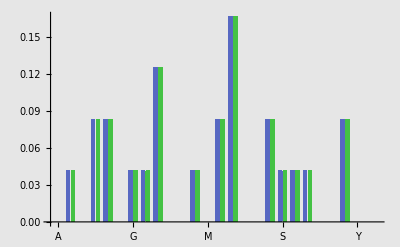

```mathematica
BEZGrafyRelCetnosti[OT,ST]
```

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Kryptoanalýza transpozice

Kryptoanalýzu transpoziční šifry provádíme na základě bigramové analýzy. V šifrovém textu hledáme bigramy, avšak mezi jednotlivými znaky bigramů bývá zpravidla několik (někdy mnoho) dalších znaků. Pro angličtinu je typické hledat bigramy s největší četností, což jsou: TH, HE, AN, RE, ER, IN, ON, AT, ND, ST, ES, EN, OF, TE a ze vzdáleností znaků bigramů se snažíme stanovit parametry transpozice, které byly použity. Pro šifrový text TDIRHIEOESDNGBIOOUNXLROX vidíme ihned bigramy TH a HE z čehož usoudíme, že měla matice 4 řádky:

```mathematica
Transpozice["TDIRHIEOESDNGBIOOUNXLROX",4]
```

THEGOLDISBURIEDINORONOXX

Další možností je faktorizovat délku textu a tím zjistit všechny dělitele délky textu a postupně je zkusit.

```mathematica
FactorInteger[StringLength["TDIRHIEOESDNGBIOOUNXLROX"]]/.{x_Integer,y_Integer}->HoldForm[x^y]
```

{2^3,3^1}

Zde tento případ vidíme, že délka textu je 24 znaků. Z toho můžeme usoudit, že pro transpozice mohla být: 2*12, 3*8, 4*6, 6*4, 8*3, 12*2. Jiné kombinace neexistují. Pro náš případ byla použita transpozice 6*4.

Pokud text nebyl tak dlouhý, jak byl zadán předpis, musel být doplněn výplní (padding). Ze znalosti funkce, která transpozici provádí, víme, že tato funkce doplňuje na konec textu písmena X, dokud nezarovná text na potřebnou délku a to je skutečnost, kterou můžeme využít k prolomení transpozice, protože vzdálenost této výplně (zvláště v případě, že bylo doplněno více znaků X) udává transpoziční konstantu, která byla použita při šifrování. Délka textu / tato konstanta udává detranspoziční konstantu.

Pro náš text vidíme, že vzdálenost paddingu X je 4 znaky, z čehož rovnou plyne konstanta pro detranspozici.

Upozornění: Pokud byla transpozice použita vícenásobně, je její kryptoanalýza značně obtížnější!!

```mathematica
Transpozice[Transpozice["THEGOLDISBURIEDINORONO",4],3]
```

TIHEEDGIONLODRIOSNBOUXRX

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Ukol 3: Kryptoanalýza transpozice

Napište kus anglického textu o délce 30-50 znaků a náhodně zvolte transpoziční konstantu. Proveďte nad tímto textem transpozici s vámi zvolenou konstantou a výsledný šifrový text pošlete sousedovi.

```mathematica
OT="DEFEATTHETRANSPOSITIONCHALLENGE"
```

DEFEATTHETRANSPOSITIONCHALLENGE

```mathematica
Transpozice[OT,9]
```

DTTEERINFAOGENNEASCXTPHXTOAXHSLXEILX

Až obdržíte text od souseda, přiřaďte ho do této proměnné:

```mathematica
ST="EIOOFTOSVPMIFIFANADFIDYDNNAUPETOCDASPNUIHUOIAYEOSOTIROOCIIGEEILENHUOISCTILNESHNIFNRIRISTFRCLHADWNERCENUTERICDDHEAGDRDHNMOTEFPALAIAPFXIECTLWV"
```

EIOOFTOSVPMIFIFANADFIDYDNNAUPETOCDASPNUIHUOIAYEOSOTIROOCIIGEEILENHUOISCTILNESHNIFNRIRISTFRCLHADWNERCENUTERICDDHEAGDRDHNMOTEFPALAIAPFXIECTLWV

Nyní se snažte zjistit, jakou transpozici váš soused použil. Využijte metod popsaných na minulém slajdu. Pro jednoduchost faktorizaci opakujeme nyní pro proměnnou šifrového textu:

```mathematica
FactorInteger[StringLength[ST]]/.{x_Integer,y_Integer}->HoldForm[x^y]
```

{2^2,5^1,7^1}

```mathematica
Transpozice[ST,35]
```

ESCRIPTIONICOULDFINDTHEHOUSESOHAVINGPAIDMYFRIENDFORHISINFORMATIONISTARTEDOFFFORPICCADILLYIHADGAINEDANEWPAINFULEXPERIENCETHECOUNTCOULDITWASEV

A nyní na bonusy
Úkol 1: Pro zadaný šifrový text délky n symbolů dokažte, kolik existuje různých klíčů pro transpoziční šifru. Počítejte i triviální klíče jako je 1 a n.

Víme, že abychom mohli transponovat, musíme najít číslo, které dělí délku řetězce. Tato čísla musí s délkou sdílet nějkterá prvočísla. Proveďme tedy faktorizaci délky ST. Nyní pro každé prvočíslo faktorizace, které se objevilo alpha-krát se můžeme rozhodnout, kolikrát ho přidáme - 0, ..., alpha, tedy alpha + 1 možností. Takto i pro ostatní prvočísla. Pokud tedy má délka faktorizaci p_1^a_1, p_2^a_2, ..., p_k^a_k, počet možných klíčů dostaneme jako (a_1 + 1)*(a_2+1)*...*(a_k+1).
Sporem: může existovat další klíč, který jsme nepokryli? Klíč musí dělit dělit délku, tudíž musí být složen z prvočísel délky, tudíž jsme ho ale pokryli, rádoby spor. (čtvereček)

Úkol 2: Dešifrujte šifrový text. Je šifrován dvakrát transpoziční šifrou (výstup prvního šifrování je nasměrován na vstup druhého). Na konec OT byl přidán padding “XYZ”. Symboly “X”, “Y” a “Z” se v OT bez paddingu vůbec nevyskytují (byly nahrazeny písmenem “A”). Pro danou délku ŠT (n=475200) existuje celkem 28224 různých klíčů. Z toho 12 klíčů dešifruje ŠT správně. GL.

```mathematica
ST="COEANTSERLHFDEENOLUTAEWPIINOTWIDDIGTOHNSFGGTIICSAALIGSRNTELGAROCAOAAHIINFRNSKELONOEOETKLMTHEOPTSTSAOODAPREEOWRERNETHGEDAWMEIWNMFASVILACTURSEPNERENBDDIMEOTELNPISANIMOTGADIAMHITACNEOUADUAUDIDEMGWTHACSEAAAEEHWIREONKNSIIOASTFOTAUATLHASEWTHEEAAETTDHNTBUVOAUIUEHHNAEEWHONILNURWDEPRETEMHASTHENDEDDNITLEERORAMAARENNSEETHGOTUMRTMHIMTFMASOEENWRIDIEGDLAETLAMSTBHGNAEEUESASSSTNCNHATTBAONTOBAKAARELEONTGTETONHEPDMRATNCWOHKMAINGTEFNIFUOTLLNOSTTAGGHTQRTPTANAIMDHNDTEIEMTFRCHUEHMAENERIAAONATADEWWSHLWAFETIUNITTRTTEHVONPSHERATOSDIHAIIATEEEAERUEKRUODCOIEAEOAUWBWCICEIRHUANLIAWBHWSGADPTRNSASSGTAFNHUTECONIEWALAMINEBELHTEOHMTLIREIVTHSNWNIAWTASWSFICRVEDCPARNTCPODDECWOEWASTNLSUTIDATEEEAORDNLHALLEEGDBRARCIEOBTADRATHWENMCAAANEHAEOTTEGSONNVBRATGTNOTWETEAADRINERNOHLNHHWNTVIRENWOISHTLHSAMRWHTMBSITHEELIOECELOSATAWLHTIARIKTHNRASESNOSTLANNRAOAETASENEPNGHLDLERDNIIOGTLHONUUTADEAIEEGENONTARHTONEAEALLLAEOOLONSTNWOFNISWCEIETDFETTANIWESNUIUHEADSSNETWIIHRLGSCRWTDINRKEAEISFHPAMVELOODUHOIOCAEERCDTIRBENTESINMMNARALIWSGWAIILATLADAEAITUEFALNISTONEOOOTHIEHSDTWBAHOWAMTCNEEAOFKSTSHRDUCEFWARHEHSISSCACDEAIJENENTHMNIRDTMSUCSEWLEIETESROHARTEAWUWPHIAFIHTENHLLSARIAWHLIRFDEPGNMEIEIASIETSTATREFEEELADEABLAATAEDTTAEOERHAWAFEEKHIATNAEHSIEWLSALNETDEAELMMEAAIAHAESRTILSFIAIRCENFAAEHEORBOLINHEHLUFAAAIIERHATLRNVEATSTMHSSALOAROCDDEUEWNSNVSBNEHADTGIREENTLNFAWRSFENEMUTOSWAFNEAESMOENMOOASSEUNHBELCRGENGREDHDEEBAANNATATHNEOBTSNSWRAESMIRNENURANEDTLNEASAVNDOOPCHHRUAIWNNNGACPUSEIITLRWSMTAMRHMITNDSEUADETSSDGLGONHHDHLNUDONATDAATLSEGAELMAHLTREAELEORSNWKOSWOIHPVRHNRHLLFECDGEHDANILOUEGEEOANIEBNTTWIHARIAEUUIHEEHRENCAHPMNRTHSWNHASIMEEHRAWVRHEOARSAIFEOEOHQOMDOTPREAGDDFTAGHNREEQODJLENUSNINHITRASOIWSTATNTBOTVNRRTUECPHHTDEERDHECAFENAEEFSUFEEEUHSSRFFAGLSDBLOERUAERNDASAWOIEIOAEDAOIRUEIRAENOEMNUIJTGIEBIBREUWODANEHCIDWNDOOATOAUODUTSVGTHGSRAOOTWATNBTIINLHEMNSUEHIIOIRTMSTISTAGUISPINUOROVGNOOUNFTURAAIRMUBEOATNRTLEABAIAESTADSTOCTNELIVRAFROORACFRTFEMETOUNSBTIRTEIEEATEOCDTEEHHECITMGETATEHKINODRTIIOAOEAOREAFRIPOTRUOOAKTDOCLATELLNPTAOHFTTEWTHUAAODCUDDAHOTIEDUDHOTMHLLCEETGHDWAETDEHOFIEEUTTAINETMFSATLHRFEPAIUBISBUOIHAAESKTNITECMEMAOONLHTUOFANHLTGUADCEVDUVEIIOATATBDTLCNHEGELTNNEIAEGIEEELTTWTVSESUALETNATRAETHNSAIARLTLENVOTLERTANRCNCELDTTETBHOSUEWUUSHMGITMTETHUHBGUVLTHELAMTFAIOCVVLUCIUUOBSASAOHISOKSNETBCVRORAOHWIDHODNIENETAEAERHLOIOFUEDAINUUTRESVHANNOIEDINHWEPRDENTHAHDAORETEESGDSTIEANEROSSHHFPHUWMIEGRBGALALAHDWHLEKMDDMTSKNNUDETNALNSIOIHAUSANTSLINSTEECAEUAATOWTIFSAUAIIHOROMRONEAEEAKAAEHNHHEMORESHASLIOGRHTIMENTNIWRAIOPHCDEGNFESUOWEGEDTTTEAGEAAENSURNNUTEAEOSNTENTTITFGSBEFRBVWLINPLHNEECALEFUBUMFMAIMONIDWHUOIBISSICEATEMHAEEFTAHILPALDAOAATMNURSAVWUTTHDDRUDNRAUIWEHDWNWNLSAAFNEDNDHFTORHRRIKDAEEIMEOROMNRUTBBGEIRESNIBSANSEHPSAEOACOFRAELTIHLSLSIUEOAELVAOSNFIDTAAAPEAWTONMLSMTTLRUTEOEAADASTOTFAELBEBWSETTAMINNSEESEEGDAEOHAUONDEEDAELSENRWANAVEENWNTNOETSAPHTWETHFALRTHNHSTQSALNWEOAWVAOECLNROTCMETNNODEMAUPTSIEFTANGNONOFOOUSRTTHOSENOOEUTTSODRTTWAKTEHORLDHENITMACINWTMAOMDEOEUOOESAKWNWDIHOLALSEHEMTAHGHASEOBANIHRTUORHEKOAIRAINFODITACHENPNUORKTADIEGAWOEADDTWCEEUCEETEKNOAERMIEENODETHOGODKNTHETAAOESOOPESATTNAEUFWHHRSELNLAGRTILNTNHROAHTADATAFWSIVSIIAHEIFINCALPTEKWTRDEODTAWINTHDTRERDEGTTWHUNECTMDEDIDNCASSHNEEDDEOOEDUHUNOTOOWEAESBHDSDILLUASVKEUENDAULRNHGOOEWADLLOEATTOEHHAFLOSCAALLTPRFEGUAETBKPSDDAOTEAOIHUOMAAHRHNSOISIRAIHVAEFRAHANAGAAVROITMTANAHOOIDIHMOLANKTOSUAEEAKOOGFIMSHEOODSCIESHLAHSEHKEMNAIIRIHETASDMKOSRDGEHUUWASTADOIERARNHEERLREESILDGNEEHEIRTMSUAOAISAORINLRTHHRMDOILHNTHEODEHUEUSTOSTSWETDUOWDIOASAORMTTNPNFDGHNANATRMEOSTVMIEEOAAMLWAILEKETEULTTUTTESURDSTSDHRIUGUSRADMRIHNCATFNIOONBETADLAEDATOKSERESWTIELANBWFOOTRHENUTETIEHTIHRANSTIRHNDHSEOTATRTIDNHSEHNTLIFOESOHTGNIOSHUWTATFFEIANIKTAOEENEOUDEHDAETENAOELOEHAOSEEDIIHDTTTPOORATLEOLEFSOREANDEEIHVEHCDONTPAURTRATOLFAEDCPLHHHSGDADSOTATOUAENATORHAFHEDIIWTIMHORDLELKALAOABHNGOHDBCNABURADALHARIOSHAESRANRBEEROSTMSRIBIRNOIMLAOWORTGHAOMHRESEAIRTOSUAMAIEHLERADIDATEOSOMLLLTOAROOEHAANSGATLSTTTWELENHTUGGSAESOINTSEHEOEASRHRDDOMSOIATHTFARRATSHIAAWOCHAAEDAPCEEEADOHEADJHEDIHOLONOABIHATOCNAKAEROTROEESRNEAACRLSISOHEWRLWOELHEOBVGCPODKKETIDHARUHETINASLDWDHHNWIEWULTSTUHHEWLKESHGOOUTRSLSAILAEKDWWENEBANEDHIAMMILTNRICSGUOAIKAOHOTHMAIOARTISLEADRRDEWTAPDVMUASESIMOENAAATISMEROEVGAATITIEEBARNENPAAILTRHEEOFAUSOSIMRDHOCIEAAGNOUIHTNOFSCIWMSEGEBARCHEUSBASSREAGTRTMWVOEALSSEIUOVSRMTUACNPANLHVITOONIKNEOGKEHEMDSEEHKIDURETRWNSEERAEORUEDTFPFONEUHDTSIDTLCMVHEOHCEAFKPHNEPNOSDNNESRNANEEIAUTLWAKPSHOOGHTHBEAOROWASSUNWMINNOOLETHSATHEWAEFDIAOOHIEATHRLEEGIEWSETEEDURNAAIHAGLHMHRDLLAWATITHIONDVHENTRSTSFIEEERPRNOITEEDILENAWOOININSOETUURFMHIMTUWMALEFHHHDOOTFEMRETWEOPCOHDUEIANTEIAFIADTILABMOGSACHRIETILOAOSDEOWOIOOLKSIRFFLDRREEDEQETDTETOLLNATIOAOHEOLEAHOWSHVIPAENEILOHRMAEMOSTOHSTSESEEDRIEATIEEOAWHFMCEDAOEHRHTJAAHHUPCETKSVEWTLLTDDIHSASIKLLOORAWEOAEERBTETTLPIHGILIHTEAOVTKHKATUMLTAIPUFANRHTMHHRVARRGATOIWWVUSAESEREETUIDTRLHLNCAROONAEHOHHEDHORIRRUAIOATEMAHAEPUTOCATISENPMDOINIATUMTLTERFSTKWETOUOHHAGMGAOAAEHNIPHLWMIWSOOHTCKIELARAOHOWSNOMFREDMSHASHADEHALOECMUEARTANEIDERTOSRHATAHWMUEHOHRWONBREALOWUOAIAEMODFEDWRAALMWSTEETEEHGAEOJSAENHORSEAGENIFRADTHJASNETEFDVLSHEESGDPNADCEOSIODFTIFICIOSTRARMOTAIRNAOONRWSGLSTIFRRUEEATSEUOEAEIAWUSEAHNLIUTSNWIFRHRAPPEPLROIOKLUHFEWTPSHEHTADSSETAIGTVNAENIAHEGHEEOOAHTEWVOEELNRBHMNCGWIUHATTRITAMNHOOWITELETCIAEOOSOOFHODBEEAAOHETTRRILRWATITMITFHAIMCDREITRACSOFSNFEFSTIATMSFEAAHHOUUAISNEAOEDTNOLNONAEAAMTNHIWRNCLIETAERAIERCGALNOAOSTHEEETAICUSOANERDAAHHAICDNOETAWRLSLHHRNHKTNENHHRAEHMWTISTAEDEDISAUOHTDHTWRAIFTEHIRTEVHEITAAHSSHSINIBAAJGTHIOENOLHWARNVHIBNDRVASLTPFUEAFSATNDAUAHOEIOOACSBERIOHDEERLADTTILACURTARAMTRICOUMASHOENTOFKRREHAMIDTPUHAUOETANEEAUWGATRNSODNTUWSHVURLNGADOSLTERSTSOTESDVFAIOEFFAITEALTNDHWBEAALNOTNIFEUHTISWTHFNTOWETVISEMASUTAEEITCTIPGAEEDIIEETNSOAAHRONMFUGDLCOTUAIOHAEEAADHGHSNAHAGOFRESSOANIIBUDDSHETTNBEVCTGHPDOFNAERFLLMCKTERUODENADSRNENWERARCDAEAOEDSSOOARINESSTSAHATUNIISODOANITTODLDLAHTNRITECHIKHOSOMPLDPSHONONHNMETNDSAHIEBNTCTOHIHTWGMNNNRTGBEGETRHJTEIWTSDERKVMRRAHLTAMNHDHOAAHTDNKWHAIGTCKNLHLMILSENFATMNTDEKDNCLCHRONSEPHREERETOTEOFHIHFHPLEHGIMISNATGIVOIHNSTEMTLINOUITFHSFPETPTUHOUSATTERVIREOODEMOFETHIRRNHHSSEERELTIMIRBCTWDTIONASAMWEUHFLEBCAONTWHSHSDIOONALSMTBETTAUDAVAIPNDRLWTRDTLEROUETCDDEAAEKPWRTMTSELIGACORSIHTNCSNDGEHWOUADAAISEURHGSIENOWGODRREOOTSROEHRAENHHETASINTHALFHHLLWALETTADVETTFOAIWIHNERDDUNPDHANWESHOAOEASRDNTOGDHHLSAATNHORUNGWOAFHICPEASOEUANKEPWRHARWHIHNNOTESOETFAHOAAUEESRTRRTHWTEOIINNOHSNGAIERHTLADLTAHPHADLATEERACREAMAAAESRUEGASMROAISBONHNEASHAIOHIOCNDICSLRLAIDTHLBLANERNEEGCWAFGWRTHDHNRNARERGMMRTLSUMOETRHVRTIIHNHMSATMEOAAUERRGCSLCOMNAHFJAVSHIUWSOIEOHSOOHALIBWKENNMRALAAOTLONLHEOARDEMAGNAHNHEHGOUSCARTODOOUSSTSIGONIWHIGRRAOIARPLINAGEAETHGAOBENOTATEEPOISNSKLEHVLIIESATFAHUKDAKOUAEFSRCEAECRGAALFNMNRARETEBUMVISTUFMIINEOTUAANWTCGEADDRAUETFESTFEGTSCREEEEONOLTBDANERMAIASWWEOAEFWTNQFINSTKHWRTIHIRHENNIUEETOITHTTNACIAEDDASOTOIANHTOATLCWIASEAAOCTHETSNAINLINEEFDUEIRCIHEEONAMHRFHHMSTEWOHFCTERATREASIIAEETTWHOTAAOOAGHEITTUUIAETTOOREAMIACHBVHROEIDDKLTEOSSETDSEWTEOSACSCEWHESEIETNFDMOLFHIBIEDEHNMANIORFFEWHIOGANWONNMIERHROINUGSIHOHAHAROOINUTGIILLODVIMWEAREEUFTTOAEEECIDCUNPELEEVUSMITNDSBLCHIODLIEINEVITNLAHGNESREEEEIMSIROMTANTETEMHODOOLAAUAGNSEAMTTDTITUAHOFLASNOHEAATWLOKDUEOIIWEOEEATDODNETNREGLESOHFAAENEATAAOHSTLNADRNATAHSRHRFNHSNAINLTNWANRANVSWHGASLOUITENEGTNEDCHLOSOIANUBNEANNMRWOUEEHTTTEEHHHORHEAIISOEEIANFGEMRBSHRTELTOUNLNUIEFBNOBRIUSNIREHWNWISNNTEKVCCOHWBHAFEHHDMEAWLHPSTEDEEAADNDNPEMTDPEWTDDOHNFIHOAEWEDHRSIDOHKTNATINTDVHPETIIUTHEIARUEBDUVREFHAGDDDAEACRSHISNEDFPNENTFEWHIAMNINDIBHLDROEKTABSNTEIDOSSLTMEOILIALSGGFCGOTUTNBNAEEEWSOWAASRENTTNAETEAENERTEMOANCMVEOEAIENINBHKDRATMIUTIVTRNIEDHASPFAETSEMOTDFTDOMAWAANTUADHCLLNNAUTMRENTCTTORHMOEFIRNARLTNRUNANTSACTCLOAWAMLMTOVCEPDLEPRUDOBIBSNSSADEESODONIIATAETATCHLTRTAAMHRMEOTEAEWEEROHAIACUSVUOOWIENTITCOIUOLIENEAFWNUAITHTENOLESEFDASWIISNOIIOEETTREHNASOKAEOTEMNRHLUWNTHMABTTTSAPHWPLTNROHESIRIVTEEAETLPTHDAAEAHPDANTBLFPREIETEOCNTIUNHITOAVRSEPMLSDHBECNOALWCTTMRNMDIRDDMINUGTENTLEWMAENOTGOMNFATEHGOAIHIURDUTORAHTARUKOOOTSCNTRIATEIDNDOCRHNSDBONMDGTPESSSEIHITCTHEEWNSCCSTHJNOPPWHOEBERATETKAOTREAMHMRTOGUNIEEAEOTTTATEREOAHNHMHIDETNOONHSESEWREESAAANOIONHSEIWSHETBHAIRHIDTAKACDITBSRUIEAPOELIAEAEAEIOADEHGHTFNIBSDWARDETMRIDITATWAEIDRSLCARNTTRSMWLEFLTDDOTRELSHVAATWGHMTTVFSSTFTERINALETHTEUEOAEWAANENNDOIDAIETIUNSTUQETUDTANINSNAAWAWNLIOMCIAHEHTGSNTISTUETWEHMHAEELKSEECSWTTFEMENEANHAREETOSOEDENLSFOEFIEIRNFTPFEMRNNDHATRNINIEAEITOAHPDACLSHHEOIRUPHNAOSOEHITHTMWEDOSADWSFOIFLNTARDIDEAPNEDTDIEATROEISARRGHOEGTCRDRLIHAOINSLNVEOTWTHOAWHSRNLMHMERLDIFRUFEIICAGEAFAUESGAIDIFCSIETEOOTEBHDILOTNIBSNHIOREGEMTAAWCEHDCDWNENSNHNERFOPSEEFENOGEWWOFTCELERAAFCIELNEIOERIEEATIHMOIHAOTUEANHUTSUINNDMIHSASIEETNMETTIOATTTGADOUNOSKANEATEEGRTEWLAOELRRCLHLSONFCOUOMOTHHOHINPNIESRMAILOHJEIGTTMEWABUCTNCGEMITNNPTISMPLKLNDEDNENHATEASTUMIMEGTSHDSHMVANNNEERUATLCNOUHBEDWKSMNTEEMLTBOMELANWHPWLOOOMEAOSNGTWEIUHHIECDMLRIOTLNAADHAAOLDEETNDTTTWELTEECHSONAOHNETEWCRETEUGBEMSFKNIISLHDROISRADPEWNHHEANGHATIBTAELOOUHAAOMEAEUSRHLCTMHERRFAUOIEESLWEEERKOETDHABATEUNUHOCTRCEEATBCTCCGFUATSRECCKATNGTEEEARAIAFTURBAFALASHAHIFATAETBRADHISSEEOAIAIEMIARMASWSOANCAENCPLRRNLCAKIUTOOTOMLMDCTMEHWIOESAENOENNEASCPLSWLNSHLGULAEBISTNHSTIHHHWHOERIDOHTFLMISIRFMEORHTEELAKOOGPTIWNWHNDLNWENIBNEEAHIHHRSUHRCEANTRHPONDTWANDOVIBHRLFNIFWSSVEONDDCEGAAAOUEHTGDFEAPHCHIHELTUELERTHSDETCITLHIDATHBORPDULBETETIBLSBPRUUTATNNIAPJELEVERIOVNLETAECDUNQTSEIGEMMLSNABEERATTOAREWINATNLTIEOTTLGNEAHOHBAIEOQAESTUNWIFDRNWETHOEUHLLCEDEEISEWUTIHTEDIEAREWTORNAAIAFAEHOETIHIOOECPRNNUSEACHIHEIHAFEAEWDLSHSISESOALAEUERSDUMCINQPOAFTITSIIINEREDITTTAREENARHLTEASEGEUEIIKALHGGTDRIHUSAIDDDCMAHATRARCASECGINENIRTKMNURDHSSACATRANWMHAUIAERSETRTSRANUDIONTFANAEEEIRAAVANMTOTEUMDVNNCEOEMOELDSHOEROLEKHBEANAECHHRBOLRMDKLTOEBAIRNFTEIAHOCOHOLKLHITHUOWEHHCPSTAHNGBEWSEOBMHLSIWLOEUHNOTEEMCLTREGHTOOEPRIEFEEEEDMIBAEEESHIAASONOOSUHHKGUETEFRITLELWIETURDCROTAAETRUTDROSFENAACODINILAUNILNATOIIENEDPAOOAENOOHHSOTLISTAHTOTECAECNDTSBEOOESODLASOTETAEUEALOEUHCSOIEUROBIEUDNEKEERABOAOMEREIENGREFITTEEWPOAHGRMITEFKGCATFNPNWOHRHEDRCRIUBBERENWIMDDADSNNDHAROGHETTAFEWNKNULAAOHACAAEMOONPIOBOUVMSLHTHSNSRALOLITEMEOBSRLOBAESITTVCRATIEHETCAEAEITAIGOOIFEBOCTIREGROAEOHOSWAKABBHWAARIRHNTINGQEADRDTISUKIHHESMTOEDOTMOTRAINEKCARHAEWAAESOTGEOLTSWHSCWITIBLHNOICBSEFSWUMOISLOEHMEMOAAOFLDUSOAHNGAWTNCTSTRSEDRSTEIOEKNIATENNSEDSEDPIRAONTOSRWRHERTTDWOEEFUOANAONMTHATWUADHWVONAELERWTIERUISEETKNHHTOPAWOVONNEFEATAGTDGAAHEOAEOTIDMTSNTTEDRHDHITERHSASDOSODERROERGATURLRTKRAHEANTAIAOHANNEACGSOTAEIAOGSELECANWEDPPNENAHOOTTTRTNHILUMPTSNFACREHSEOMBOAODNDTLBHDGEWUKUUIIEOHNLAATTHRFMWFECASERWDTMRTHLULOTHSAEHSEONOAOOCMOIAINFTTLWQTNEHDDSOTWOWLTRDANFIRLEDTFAANSEESSISEHEOPHAWOEETCBMWRSRMUDLNWDUBNEOLHINSCURPNNOPFSRRBHEDANEEADUENSTTOAANABCHTAHUETITLRWOTIODIPSTAHOFSTADTEPEELONIABCAPAAAWFWAWANHKBWOLWEEHRWGNLETWETRFATFANOOILHHFEONEOIHMNUAAOIHENAWNCURDDFTIKMNRHHEDOPWHNCODESMDASOEILAHDDEERRNNTAHTMLJUMCETNCHIEHETTUESEIERNQRNSDNHONEPAHSOCNEUSAIUFMRRPWOSOOSLAWWRHDTIHAEEEWAUSETRFTHDNATEAOTMEEOUTHLGNNETOFARSHRWOACLCIBSTFOLEEVHSLHEONOONNEAENEGLOHSGSGTRLBDFRRIEALHAATAISTPSEOUNISIOACSFDODFGIUAEDRDUEENDITLVPTNAAHNFBWSAINGIDMOOSTORCUGHHEGLAROAETNATTIAEHSUEIIUEEIEATLTDTSAEHADATOGIBPDSSHEMITAHEVEWSPLIAVEHOMTVDBAHHLSHRMEIAEONDNAFHTNIEESTNGPREEAHLITIIEDRISOIEISRNPELROTQNTEALEOEALUHOTEVAMIAUOREREHSVDEAGAOOTNINDEUEPOOIARASASMTNABHONEOTGSHSDVBAEDHHAONDHRTKORIHONANNLIEIDLEEIOTAISATDAUAIVDWMILOCTPFICIDTARWIKEOEDUHTTTRDWIANENWWPUNLAALJDLTIETACETDIAOTEAEEDAMAARCNFIEOHWTSALGMDUOWHAAEHOISTTDISOTVCNVESAAAHMHBVAAUDNIETJSNRATSRPHONHSESMCIOISANLPTEWOAIISUUCMPCHIHMWSNDWEHHEONLUTOROHTGIFIEDPOLOUTPINRTINSOIAWTSTUSMTEONOOGWHPSICTARFADIBAEIGSDNSOMNDHWOHLTATDNHARBEEFORSSEOSHGOVEHHOOTPEOAATCANAEESAOEIOTUCNDTVWNEMATEETKAARLPDTGAIDIRNHNIOWSIFABEORBLAEEVTENSSSWELBOANLOHTLINIUDSGWTKSFPIUESHNEIEAERUFSLIGDTAGTETALTNSTEAARIEWANERSEFSWPCAOEUWPONKINTEIOEERLEOLTADACSFDAROOATTERIAFEAOTSEAOUINAERHTUWROLAIONTBFBWECOUHSEIHAASEEHNKOHWOOAGRODADNSIETDLIIMACBOBLRNQGDTINBAHWTNRBOFSGOFIEATDAADAANDAMLDMEHAOADHENOSIESRIAIHAMTSEREANHESTREHOMEADSWSEEICOETELFOOOTNMEOSMHPASATDUHTSESASSSAIRADDELSCSSULSAVIUNHNNVEELSEDISATTNAVTORDACEOURITFEASTHHLNHRVLRGHETHOETROLMLSOADSAEOIGCHANTAFFETEPHGANAIVRAAREHOCBLTARCFAHDFOSETNRHEOTAHIKMSLAKRFNARHAHDTIRUUFATTTSRTEBTNRUFLTOTADAESWHENADHENWOGPGHSOAUINECAEOOHNOAECOSIODDTEABNOIMSASEAEVAMHTAFOSNESDSIRTSIBIALDOLITESIVPDQIIEATHOWIBDENRGESOHIOETNBDISTSOUDTUGNWTRIIOLDCSSEIHTTETTCONAAKDSTAOHEAUERNEEIHEWNWEORTEEANEGOIFHASTHRSTRELEFTRLESSOPIROENITLUPNNOTORCTSABMENWIMHSOIOWATCFNWNITLEOLTDNRNNANLOESTCMJERMDIEELHLHMPVAHODELOHOCEOAHANIFHHGDSEEIOHSTHNOTMSHHTHIAEFANOEAWTRAFAAILEUCHHTIHHMEDBNRHUBUTUFOAAMHOWHIFNOIGFBETRCEAISRAGHATEAAENEESNARRRUHNOOEPHIHNDEHONAEINTTENSSETRHOUDEAPOAOALLOTHALOCODDWOMTANOTARALELSMIRDHDEEKWEOCAOTPEITNGIROAVHLTGAAHDEVHSGROFHHNRSAAIEIRHREHLAWTHOAATLCWINPTFEOMHSDOFCONMSFNEWAMOTEETGCRAETUFBHUIRAFOHVTEOSEIMNITMOEEWAAOEWTRETBTRHTQNTHOAOARATEFUITARSHLKRNOOLHAPNLNSWMHTMEDATOAUDWTDEARAONWFIWOORATESAHSMNETOHELHINTNATADLSDAPIEIDITEVROOHRAGEUEAMSETOEETSAHHSHAVREARNESREINEAASNTISREOERATEKOUESONINSTIRTAGAOROLWCREHOOAEEOEDTJIHEEEEVCTRTWSIEERUSWHISAIWAEIOGCELEHEOUIWHEHHEAPVRAHDLIESAOSFHPKTIDEGHEORNDWHHTKOCTMEEHEATTAOHPTTAONERITIADIANTCNWNEEMAHSTODEIIERALBTIATCNTLECMDNGEITITILBQTNSEVSOTEATNAHGEOEEMDUHLNIOOHGGFWEEPSNOEASOADAEETRCTSGSAHAHAEONEAHGDOFDNUAHHHIUNUNNUISSEITOODNBDTARLCNUANEPMRTSAELWUINELEAOGETTHFTHARAREEELDTCESDAEHHLTTVIUESAOWSSTTEIVSHHEESFOASSADFFAEWRNATHWTHUERUKLOCOPAONSARHEATAOSAESENNAAEFHEFREEBAUMWUREAEHMNFTTODHCHAWETDORANFSOTTEREOSRHKNNWEICALAAECFHEIEEUAUIWMTIOCIOITPENADEEIDNOSETFWPLESHUATOVIRTMSSNEORDLFRAEHAKAACRIDDATPNDWUDHSHEOWSOSCODOEVSFEUGEANGIEHHAAILTFLEWEEETCCHIOOHHLTESBRUSERNOCESITSDARPNEIDHHCATEVUMBSMHDHSEIIBEDORENORIAORADACEEGCKTRSSDTAEAEAIMEOCRTRHVHNIDTTATOOTCOANUOIIBFOUDGNIHGEEEREDRTBHTATTLENSORDTHLONNTHAMETUEDEORSGIAFIRELVIEGELFSDECARIUIHORNARAOIOHATRADESEAOTSHELREEFRCIEHVTNATILEQEOELTDSITSKTWDHHPDNRVDLOGIKWECOBTWESTMEBNWSMDAOSHRSATDEHHTLTNOSAOSDAANFOTAHHCHTEAOWSAAFISKNHTDUUEDDBTESESSISDWEEITIDHTJSTLEICAIEUTANOEEETVBOLREOASEGEISPDNEGHLHTHAOMEDLEMEGLUINAMSRWHOHHHGEETOPNNRFNIRSDAINSREHUAROHFURWEEBTNABARSAWRSHESELTAELWICARTAKGMIACEIGTLLMPHEFOWDIJLTROAEGPGVANNURRIWTVREGGMOEEWIDHDIFEIOANTGEVIUORTAEEESEOUFTNRETSENEIOSLGCTECNERSOSEEOHRHINEPSNTDMAOGRAPUCGURNLRTRGGERIDSIIMCROSEIHHNTNETEBSTTSWWEOAERTONIEIVAIDDBNSHNTKKOWAHRSITLTGMOTADOESFRGNNNAALTFVTSRISAGOOSESOSETEWTUHIOKIEAEOEAHELEIWHATWMITEREENNKBNNSFLRANWESHOTISLTUIIADEOEIRRAALEHFBHGAASRTALTLHTGNSATAHRSOEHWLUOORDAUNETHOEENAECOBMFTWTHOWSTAIROENIOHTONGGSHPIFEMUADICVDTTITSPMUWOWAHRWTGSCBODSIRMAWUOEEHOAAAENHOMESCBVGNRAEGRMEDTICCENWMOHOEDESRWIEIKITETAOKNWHUABENTFSEAOEHLAMOHEWESFOWAWHHIHUINDANETTFIARULEAEGLISRTUAENSCBNANVDWEDMWGTWWTHAEESHWLFNOBAKEMOLTWRDNMAERNIETGSONEEESDDIIAMSAGCITRRNINTAETERDNTCDEDODIATNJHMOASTPTALMEIDORATSHDIEIVUDECADTHAPEERNESDBLSHEPAVSRAUEOOWKHDESNITIIIOVHSLLAGHKEPLFTIHFFNRTTSGTHADRATEPNSUWCMITWSAVIMOOTESUNHNDEARBOTWMOATTMTHATEIWEETVDSERSTDTKOLONLNHWNSIHHNUADTECTSDCFTARTRRDIOHOIHOSLETNFOIANTCMONWIMAAMHOEETEEBLMMLAUSTNTWEDSTKSHSLHMAHHONRHDRETIPNATEEHCKNVAENHIWAFBLRSILFAOHBAESLHOAMNWWHHSMHOASBSEIATTSSTEAATSEMOOUTNLASEARPGIEANOIGTRNLICTLEONWOUGBCEHOHTSANHHTUTHAUTHSTWAALCCHULWOSTFISAIHODSFLTETENHSAIEETHTRAILWICEOEAGKLRRLSHSDPSELSRDSTWUOHGNNNOOGEAOSIAFOIOHEDHDWESOIOBOANSDREFWEOTOEMOHNFMOSSOAOADOWNSDUTHESEAORSRNEAIRCEDHTAOOIWSRKOLTNEAFHTATRTHBAIHACTREREPUKAVIIIHALETISDOGILALSPOAIEGALARRMIRISARITHTSDABTEADOIEARGEWILTARCSETCERSEHENSSHVAEKEITOIOTMCEDTRTEATFINNEHIEWELDBELUASERTRAEEUIHTOSLTWABNNKECINIFIENTNQWEIFTOEISIIHUHFPAIORASNCAMCHAAAIVENTNAFEISTIEFDELTHTCOOWEOLSAOFGEAIRINIANMSSTLNRODRHENUISODSTDMESTDLOIULLMTCEAWTAILEKANUIROARUMCRFCRSANCODEATRPETDDOTESOEWWHIHTFAOWUDHTWHASBEBWHHEAEHARDCATMTHNEBOTVOGAIUEIELCLIHTVOBNLLNESKFFEHIWANONARNNDERHAIENEAITWENSGOSSTBAFEDSNGDREHTTPMTEETRSHWTENNRLHEELSDNHTDNIMEHIWILHAINSGOIDNESFMTIILRANALTHMFRERIEAHHHCIMERRFPRAFLHEHTBASESNEAKROECECMTOHRWMEEETEERSSPWTDEHTNWHWDSNMSRESREAIAESRTESCGEETOLHLTCETTGEMREHFEFTDOTAWOSFBHNTNNCWIMGCRMOSAAHERPATESTHEAALRTFHWNBHRVGSFVEBETONPFAAHPNMECRRNWTVNMPAOENIMTWMRSHERLOEODREOAEEEDENTOODHEHEISNOTNTANHUOUEBMIFEGTONTSMHNIOHALOSASDECAODGWEHHTEHIEOOOTKUELVSATSGNCARNELNAHAVSDAATHLANFTTTLAWIGIEECFEOEMAUELOWRAOAOIEWHDRKLSGEOTENAIAEEEIRGAESTDETTRKIUAARTIILVATAASMTTOTNWNORWTSDLHSENNSKOORETCWTNEHDTMEOKHEHFDSAWDALMOEHSICROMDHESCSAEUVEELLMMLRUENNHTTOISOEAEEDLUNMPBIETIPGACEWTHLEHWCRRANNHNUEREDOTIHSEHOMHODATSDEGTTOSHEHTELLWAAROUMDWAEEEENOFHAOESHOREEOTSNAOFTOFHHACHOOEHERABFHITIRRUBHEEWEFENATAEAIESDNASEMEQOHSRIICNESNTORAAIAWLAWLEATHORLBCELANHCDTMADLADENTLAANAPHSILUHAILDUHLCHLUATDTOGADSEASIRATSIATWSNKAADEHONALUOUISEFOLOPRWESODEDPLIEEEAHTTIPSLEANLRAKNALHWIDAICEHUTUIIWSGINUDWDNHPTNANANDITIHCOHBESADEIDHSTHINATTDLASNTTNOCALNCDDWTHDMTWALDROETEDLOUFIRSTNTEITEHATAUAAPCEDWSNNSLHNCUTAIDCHIIEFNRAOAARRISTGFSLAIAGDTQSFCRDFPGILSTONTOFEONHETERIBMAKNOTCNNONCBUANBAMGTLNRDNWKOVFTECTLELSSFSAAEHREIATHAEDOCAEAEOTORADBASRWHANHTHETRWITOEIMIHTETOSSRETKOHIEONAEOIULNBIODSINKTINETTODIOPRELLIBIUSTATMOATDMNENELATREKSLARSUAIIGLEHAHGMINOAAITENNOEURTADSNTLPSPTWORAHRNNOAMTHEJDHCRAAITAADIOIUIIOERLHORTHINEGRGGISHBHANIHMEHWEOETGENTIORFNRWOWDTKILRQNTDIAOAOTIEITAEHGDSEFTCDTAOITSSTEIIHOHTDIMAATENDTDRDMIEITEAKIROEREGREEARUTHDIDKAHCITSBRHSNTOWBLSIENWHGEEDTHEDIRTULEMTAHEETEENVETTSENOAHCSPHUESDEHSELOEACTSNLPAAEEEHSAEOEPAELIONPECRATSANSNAEKIORUNSITTINTEOAHCOCDITTTARSMASSAAAEUTOTRFIUHSRBAWOEOTNOAAHRRRUWLWUHNOLOQWOEFUALAOEWHDNHHOEEHSSEAABMOBAICRICRNHNCHHNMLNOTOEOCIMOPBDCRSNIAIDLMTSSNEMATMECARSBEOVREEHTIHUSRIERACRTOGPRTAATTLRBBOUASNWDIGFCIELFRAHTATINAEFHAMSEOLPORMHTCROAERUAUDNVSRIDSASRHVASNSUESHEFEOADDETSOHAWCHEOITHEAONARATEOAESNELDIEENIAATGSHARANELEIEDAESSAOAOEHHHLAILTEFHETECNETGTTOOWFMESWSARHAUINESEEHRFHLLANEENTOESDSIEAWAIEOTIOSWETWGUIUIHOALDTSALRNSUAAASTOAAHONTETHAHIROLDOUPTSTSSTULARAAIVEFDOLITEOALBAAOTEALIOLEORSSEKREETTDUIFOOSEONIMWSIHISCHNRNIENNEDISDTAHSGPRATGSAWTSRDLISITRASEHLSEESNACPNTRTTNUHCFLADLFOTTNIHRTAGLEMIECONLETTAWTUMBGTTNLTTHLGASOCEVEEODTIBDHOAHOIWHSISGRLGTFEDPHATSWUHSHSOGTTDMWGTEEWWRUUAOGSEINDASIAATHEEATALGNDEAERIEHHEEAEESIETSITVAAHNTSLMWDIMOTOARNHNFUHAARAFNROLEKOFONNEOESIALATBFTSIHGLATANDBINWEDHIHIEASENHACKADDEOTEGUOGNAOGMNNHHITSLDUHETEAIRINEDAMORERHSSFLONAOTDSWLAIRSGRDMVRHTFEMGRSOLNMTTAROTATIWHDENAANSEAROEDIILMTARGADCAAHAAAWANFEINWDSADSTNMTEIEGEEISNENTIHSLADISMONESEENSNBLIENWTAODOHWNIMNLENNDROIPDHIAOELELEVSRWKUERHNIKAAWIPNTIRNEARBNOANISEONLHHTURDPLGDDENINIRAELTAATAIFDOCILENEWAEOLUNUMAODLGAAIEAEEENDAASTIAFDPAHNOLWGHDRHEGADAAINEHAEDANMVAHTTRASOLERNDFHTIGSNESMNHSIILHINTFTLCSRITSIAOAGNTRIKOTHAMWDESSMIPPMIHLOLTNAIENONLNERINGKNGEAIDOENONDNLINODOWENTWLTTOPALTSSIESATGAOEETGNNETOEOHNDNOTTIFNHINDSWSBAOEMRDHHHRNLSOEHAGEAOHEIPNSDTRILASTWHAMSRMOAEDOEEEINHTRFUOEEWMOUIOSATLVDEREOTNASBTAAUCHFDNESOQNHTSOHGMEINIOUBAATWOTNEORHRMHGRFNOSMHTERANSHATHAEBAICUTEBCIEIWOETNSATIEAINNEEOTRMAKRLAACLONRMEORIRTEWGSRTNOMQEHUSRREUJPNHNVDBDTSWAHKUIMITINAAFOATSIFIRNEDFHEAWGHOSTOEDETIIBOTIWSENAIINTGTEADNEHHNHINEIAPOEDEHOAAUSASIIODHLIHNBPHTTOSATSLOEHRTIOEMNAODHHITBETSHECANEIAFINOEKMFACDSAIGDWTETACTGSAWFSEDSHONAOVSTTILKEINLDINGFHDTAMDOFASAHREANILSIPDUHCINRDEHATTIDAOKFIUETUITEATGMLCWVEMEMWNBEMOOHOERINETAETNEAOHNEAELOOHDMAMTIONHNORRFILROOINHHUBITHLHGRAEHSLTRERNLAHNITLIRJMQNKLCATDNANTANSRDMABLREHWPDLEAONHATAETLTRAODFTGATESAREUSSDDSGISONNRIAEOIGNAEWHSEEBTONAIREIUOBSTOFCILGSIETKERTTFATSETRSEWTADISPTRAWTFTOIAIHBADEVHIMPRIAEITERATRSIFOTOIOEHDENLLTNGANDENLATIEWKNNOUENRDIDHBLLECTISOIITIOAKODSGSETRDSNMRTTEIAMUDRISEISTTINSOHLTUESHTTOWRAFETOLLEBIEEETMAASOIODLTEWEOTSARADICLGTTELOOAARDETLEELPRLHSDWSCRDSIDEBAOAIUEGIAHTRDHCULUEWGDODSTHHHOHTOSEHAOBASMNIWETAETMOAARLAASENTNRTHMTCSETIHEAIAAEEDTDVEIIOOEHSSHTOIAEESAUDHESEANSATDTWNDTNREOPLOTTRPIGDRAMEESSTILHDOIHONNCOUTIESDSGEFRICSOMHTTARITNEDNAFTENNDDHDTALTGEEBAAPAASAHDEDMVINULEFNSSHTIESMASTVNSNTLRLOIWPIERRAOLEEAVSDRTAFTSTBTDSAOHNEHEAIKAHDLEMIIHAAHWOLWENEMEEAWESSAAINDCVANWOATLAIOUIHGANSALREHAOANADTMUWDHTDVRIOHRNDNOFBEEELANOHHSAEWNIALPBAEMODBFEGOATBNOONIEIOHISPASTATREENNADMWNSSNAAEFEFEVPBEAAPEHAFNENOILMAOECSOASEOWSTRNELAHTIUHTSTULIAEDIEOGTRRSTHAEISTNANTWEOTPONLKSNERWATIIEHTEMSHDTWEITEARLTOWIITNNANRWEODAUFEDICEHNRIALTMUISTSWMEWSNEIONTLNEOAWUTTERMTEBOVLATDNRLOTGLUTIACRASWNTWETEPVDWIPAEEAWTEAWNGEOAOISNNHQRSVADWFTOAOUVOAHAPNEOAARNEUDETDOWOEAHOSWAAUMSEETOWCRSIPDEOOTLIHNMAAEHNAOSOITASTORECARHAGFLRREASOVDDAAIUUASHAOTOOFFISOOCHAAOFFAATUATEDNTIEHWOAIAFDODODELARUFFSKAEHRREEOCISNARHANWAOLIOHINANTSISITCALCEAEATIOGWLLIHRTIISIDNOADEEEITHMCTSMTTSREHRDIIPCSQTGAAKHNEUDPHSHIRADIPETDFEWIDTTERLWWETILKDWNREOHIHTNOAUBDOVHUTNARPIIOHHFHEEHATMHNDMNAETLSATNOWNEAHIEEIIOINARIBETOHNTURERBDLUHVARFSPDOTHBSEIGEGODLWHLHAAHARHADESIDINRIEGDWRHEHHIHEKBLTTAAONSAIMHGECAALIINROHHEKPAAAIVHCLLGNDAHEEOIRASWAGONIBTINMTRDEERIIAOAUNRESEUHOEEFIWHWTEEEWEEONARRDLRSNMOUMNNGTOPATEWMHDICLRILELSASFHVOTEEVRMDOTAEWNESTTNTUULEHAGTRSNDEHKAWNUSPAIDDFKDEEERECADTOREARSFAAATANUOIBNWSDIOSPLNMIHEHNDULATSHRWOATOPETCIEEFROCATRIIAVHLEHAEETFNWNSEUSWARBSEAOAESERTOFROPOCRTADSOIDDNIFDLDSSFTEOANDIELTDMUTAAEOREARSTIERSGWERAMMIEOAEOHENTFEDATSEHWRILAIERTGDEOWEOGVTHOUDOLOPREELEBRNOUIFTNTTMDHMOUEOCAFINTTATLIOWENAWASFAELHPENUPROORSIBHARTONOGTAWOBADEMAOISTOWODHICLOCSELHNVOEMUIVSMENAKTAITITUHEOOOGTNADMNDWEETATCTAGELHITIEETMHCEADDRTNIVGTNHAIEBNDDFFOSASTDALHATTNIWAKAIOIIEUENPALGEOHQWCDTSOAORHEATEEDOLEEFAWGWDSEUEEIEAMARELLUARAEPAFEDHHEIHRBTRNSEERHLNLHOEWTLVNPVOATOHOAIAUTLAANEHAAESMKTHAEMAORLIAENIETAEINIOHTIBSTNHDTUGWEEHATDTAESOLRGCETTNAAELWREUVAMTOEDEEIHAAURACTSOHLARLHROIMDAAITMHNTTEATILAGTRAOARMHSHONDAMETOWLLHOEEANBAEIDNTDEDEHVCTPKTDHCEIHWNAIHAEATMRTROIUSAASNBEROENMRSGNSTBTLAKASHTIEIAWERESMMBOCUOTTEHVUSANOSRTSANEKLIDTAHAHEHUEWGNWLHOUKAABEINFIRNEOESIEEWUDETEIMKTNBHHTTNOESIHPMOWTFODESOTAMFSEVDIDNTEENWRDSKFDMAAWENIAPCROEEHRESIOFWLIITISIEMOEIUALEMCNAHFMENOAETOHNNTTIEIWUIANNLEIHTCVANDAISOOMCEWEAOWOOLITNDSSENLNDVOBFHVEDHTSDUKTAMNESOTWUOSUAPFAINHONQAAUDFGHJLESESEEANTHCSREOFNTTRHADONREHUDMHGOCUKIHAINNDSHNUISGHWDSGHOELHHEOTEHRIAMVLINTSETESOSANHCTSESPUWOIROASSHIOOABTWNDUSBCLOORHSISOTARCESTVELHITBLTOBEMOHFVSEIHALIAICODBNDETRHAEUHAAOOCNPSGHEIOCNOTUSNMNWVKBORTATCSLULRSEULILNUSSENATTCIEOINBHPTNHUNEADLODURANSATKIULIOCLEHTRTDAHBMGATADFAIWRRSAMSMTRFWHANAHWHAHIENRTMROANATHEWANOURHHWEOTABSIONOINSOEAOIWKERRCEASNMEDSNKNMFIIHUULEDNSDNIHVTMESODDITRTRMTSNOAAERCEIEHHUDMNIOONLFNFSUITIEAUEWRTNNRLAIEWHWTDBSAHTLSDASARAASUSOLDTDLUTFTERHNTSITEELDTETTRIEEKEDOHETFIWRTHHGLTEPCEEAFTFLEUTSETTSWNSEINODASRTEAOHTOHDFRSFOKTLSTEAKSAAISALEPHRSEOENHNITEEHSUKIINIEEETEWMLBOAAEMISPELNNOLBDWLTBRTGHLTIANHUEASWAHAESEOTTDRPABTIEAMEOHDAHAAWIPAMTLUSAAISITIBADHLAWTDTIOORTNINIDTTGIEHASBTFHOEFRDGGSNNONKTOTRVNESDTTGTEEOLDIERTAHUSCERGAITOCHTEERSEWISIRPSFKANOSOOSTSWEIWEELAAAAGAASEBTRAACSEPAMTEGEAATOPHHIESUAAUEMTHTLHATORSANAAIBPRECPINHSLTWEHSCEAHEFUIIVHHWFIFFWUEGFTWAOASAHNTEMAOAWTAILIGOAHNEOUEAUORLAIPNGITGWSSHFMHBEMWLAOOIWNATWMAIVIPHATNHTILTNNTOEKEHNHALFUUETGEOTNAADGLHIITTTOWEOLWSFEAENRTDOTRRRSOTAMFNNNEIEDPCFANTEELEOBAOIMRGTASALLILSUCHILEDRNLCRHIITHIEEOEIEDHHOPISRONIANNTUREOEGNAEOOPSDOCATIAMGTTODRSGTJISRRETOPPOELTEAEFRANLINABSNSWLWWUUCOAUHSETGRHRAHAHLAOTSREEUTDDEAORSINCAESERAEFTAESHLEEIITLTHTFOICGDOTHWNWRANTEGSHEDHRMMTLUEMGOFAEREBOEHINENFENAALEESMOWDEEEAIAAWAONODHWTPARIWDEEOHFABAESEEALDTOGELOHUEIROATLEKNTHDENMCTTFGSORIGSUSISADDWHRNAEMAERLAAEHHESOEEBTHROCMWIHSOFTFBTAAHEROIDREOITMFWNEDESDNEDNWINDEOIOCHHSODOONHOULKTEAEHRVEWAEHOLIFEDNIILFGPTOENRMEIRTOSOAOOSNNATRRESDOHGLDAEBMHEALIGENOGRWADNDTNEHIRFUECNRATTWTITNOWEETEEDESNEATTCWMFARIWCHLNHTTAORMVTHLWTKAOROIJHBESFTOREIALHMLEHASETITFEEMGTTANBCHDORSFAANODIDRSNCHHALAHHHORSRDSHSIIINROBSETAATHIFLARATHKOSPGWTFDOSSGWTIHWEEAECSNADPKREHMCHIHOEINNAIREWLABEODEEAAREAADTHSOTFESILHTHEHSERANSRPNEIPUEDADHIDMHISTIALADHTINRAUTGEOAEARARRTALTTASNEGMEEMSEOESTBTDLOAHTNDWAOALNSHEEOCEVNSDESETRECIEPTTNNVDEDAOAOCRLFTDSEATOUGHVHDNSEEFFEABIEWLEEASIAGFHNAHTSIINETPTKMIDTCTREEEIWGTMOHIIGEFOCUDNKCTLUNIIASEBTSLEHCBOATINFGEUNARUAETCHRTANATLAVLDIRTUTCLTEEEJWENTARFRMSNECLIAIRNONLNOTHUEWRDDOSDMJLEVBUNSOEHHNEWTROIESTIHDMACDIRSSSEOSMHSOHDHARDAIAEMOHAOHEMNEGAOALODHBCOHWHELHTOLEFTFAWIDEILUTRPEHETAECSEHTNTISSNHPESALEWIRIEUIGNEOAMGEEFIKATOOATOOBNHVTHHMLEISAOTIDACEOAWIDLGHTSTAUTANMWTIATAOANSMELUTEAEEARTHFETEEEMEHLNUNNSAOWTKTPRAOJDUTHHLOLETTGNAHTEAOVAUARUNNNTIAWIGCAOBEUWLSRNEHOTNISELEESOEOTUOESTIRUWOPECUASITETENEGHNDSIUDAOPSDDIASEMEVTHINSAIDNMNRDOELNBOEHNKAAANEANHRRMLAETOOHEEWILSWITEOENAEAEEEHERAHRTHEGNAELTMOIUHNREGOOKSIHEIDISTEDRUALHURNETEWTSUAASELLWMOREDHUOAEILMIEDRAEETLTILITASNWBIHITAINCRWESGEOBNTIASIOOAEAEGSEPIATOFAFURABTBLEAOCOADTNWSRURBCANNHIENTRMMSSWTICGDETIUUFMRSMDSRTEEEDONDAEIRTNWRNTTLAHRPNBEIASDSNUIODOLUGODTBEIPRRRSSEWITRMWANTSOLAABSFSETLPNGROLNRENCACSUHHTNTSTALAMHDRLVEIOEIDAAREEUAATEGOTOCOTTPUHLDRRAINLELSHANNGSNEMFTRATKRLIHFINLROATTELEWTAFIITAISDTNSWAENEFNHLHRITMHEEOTAIEATTOWEBEEHHERAHHAEMIADAATONNNRNOHSESSODRNNNNTEOOTTBMNNFETTONRNVTSETUTHFBSRAEEUOFESGNHMSMTOSRORRETFHESOSRLNHLEOTPRTROSOEASNOTTSBIAANSETWLAPEEOTRTTAGSAHEOOEEIEDTEHALHORACAKTOVHLESUHDIASAEOACOBTTINALSEEHIMNODBOEUUAEECDRRNCNCTNICDADETSALCHVLALAAGPOLNTHMTWOCHWNAAURNTFETEREANAIILAIEAEFWCMTNASDLSDARTTGTKKNSDIIDBVHEEVHDGTUGKTETSUTLGCTLOTEWLIOTPSHCHILTTRATBEPREAADGUWRLWHTDELELSNOLGWTGISOTHONDSSOTAOEMUAEHRHBAWNEDREEEDBISLDRAGDEUOETMEWLNNDMUNHETRNMBAREATDONSORMNNAAWTNCHPOAOAEOCTDIRHELHPWRAESCTGHHFAIHRHRDHATMHEHKHAUEKNNBNODIELEOOKAORTEANOPAOSHDOSLRDNNETITIOITHALKTRAIHALNHOUEIIEEDLOACTHNTTAAEIKCHNIRCIRANNSSSRHOONOILUNAANAENONUEOTHADTUOILARHTATDFEAOAIESDDLSEASTEAEMEADEAADOIHHEOILBSWAANKEAAWOEUNDAWTTWAMARWETDOPEOMORIDVUIERANASLEEGHWATMSAWRHESSOIEIHSHATEIGHNHDRWBSIELARTNAPOTPITAOISHAASNHSTRAOTEEHLIHMPENTRSFTARLTONNOTEEOIOAGLDODIHCAAASNETUNRUACOTOALDSEOIEIOHQDOHEAOAVOSVOALBROBHMONELEDSTAQTCBSAMATMITTESBRLKHVAAPPFWKEILGTHAMDSUEEVRATNETIRTRSSHUSNOMDHRNNFHNEIPRENETEEILADHETMONSTHLAMEERSGIOAEAAEEWMLCULNEEUIIRUSETTIEHLSEDOSAANRNIHOIUAOTUAKTDGNRHOURLHTMLHHNSTAALDTSHEARAUSHLHTWEHDIWFWODOOTFSRRDTKODROEKAFEAGTETADAESPAIRBMEDNAAEOSOUVONTTDIFTLRNILLLTEETONTLDOODTOSHKLCAVEDSITHAHSOAAAANRRAETNIAAATUWEUNHEWSEIORRLPEEEAPBTFESETOHTEBUHLLRFTTEATEGOEKHLTIVBMSTNREVPDTOOSOAOCENNENLETMARIFCRENSLPSNAWEOMLWALOTOGTUHTASHLOFAIEOOCTSEORCNRTEDDFMITWHATHSOTNOMFHAWSRAAHTEHTNIPIUIAEEIMDPLHLROENWIENIWAPIDASHAIIHTDBLCDREDOAAIDUEMIIMINAIKHAIEWERTTEOOTHDMLLRHNBOLNAEDDNTRILEAHIAEANFRHNGSDSRWIEHTKLIETPNRPUNETELEESSDOCOATIENOTEBSMFBOIAAESRFSAWAGSVPTUHTRNAOEETRNGAEOSETRHAOEALEOHRWOEITCMTORIOTTOAGOWTDRNEKLINHTTNOWAIBDWMASUOSTCDANHEANLSESRHTNKOHOLTMRNANSTLNEDHNTEMHNATONIRCANNSNTADENNDDCEASHLAIARGFMRETSHIOTALOODSFSWITUOBEADPHEAIUSTHOSTECROMCECHFPESILEKGDGUDIEIPTEOREHBMTNTETUDSUOLBVHRMTRILMNONOSDAHLNPTTOLEADSLAOIHUWLRENAOIDTAOWITCDWOTNMNOARRISOSHLTHOATMISDARSANEHHNAHAICREMOTSIIADROOFHOHFAWFTDTLOOSATLDIEISIIUBTCFFOTAEWAIUDDTFLHOMIADDONMRDOWSROEMMTELOLNREEIEFETDEOTOICTICEQGATIEWNEWUNHDDDTFTOELCUHPRLUWAHDIHEIENTTARAIARSTTIHIMLRHMHFDHDUANIIONNNTSDHEATFTEEAWSTODLEHINARIMRWWNJEREWHAANDTITIEOISREWTNOORSSLREOTEVHRENAHNTHNEAEDNFRLIKDFDSACNKNVHOIAFNGRVOVMDLRIITRMEFFTUSDJENDGESSUASURDROREARIIIRHDASATWANSTDENAGSHEERARTONSOEHAAFUNIDRMKTFNEELFEICRSHEODOOTUMEHEIIEEOSAHIATIOREAIOGREEDOEUTONNMTHGFTAQTHHEDEEMTOAENNOAHSNUOAFSCBMARDGLMALOEOAIAODWDIRSPTUNOHOTODTTALLHNPAEKBDHSTOLEPNAUDAUUISNHTOOWRDHBTEOOFMWAOOHNKTWSHSKOWANAAAISLRSORHOHFRHEMSEEDDHNECNGNRNAOIASGKROAEEICRHRCMUMAATDRSOAEHHINOSESHWOIAWNSTINBBEHHHSEEOAGEIWHIOENTUONDESHTAUSAANECMAIOIHDARAMHNINGNLHEWHINMSEEAARASDTHANROTELSLHDREWEHAOEIETTEKASESPUTHFLNTSEHENNLLDAUAHINTIHRTUNRFFAENTEEDTEAAWREDBEUORATONEMLAEFLNHBAAFIERFPEOTWHOUIEHTOKEECIFRSDDTTAORAOOWIEOWTFASNHUEENATTCLOHOTHDMEIIAOINVNLPBHSOUBAWTFTETENAVWMFSAESMDEEENOTALMDAEMLSTIUWTNEEBKETTCDSMSEARHWUNOITSAENIAEIEILNNLOOTASHEKDOLVEHHAPGNEANTOREIMMEDASAATWADPEETRFNWELNAASOTWNESUDSUBSAODOOLALMHBTONMOAIPITDUANDDTAWSIHREOUNGLBDAHAACEUANINEECOPATDIBHCESNDBAIUARDHERWSEGTEUHDRCAIHTAILHTRNMLHLWTERNACTLASRHEITTROSETORNHIUENSTOASIERTFTHANAORMEFSSDCSINITWHHOEHEUELELSONDMOHRTFSHEDEHNLIVSLSNNNEDLTADRDRIATAOSHEWIEETCNIABEODTORTCENLIWUUROWUTAECNDCOSSRWTDRMWOVRISGUEOMSAGNUAMCDUOUNWARTMODEUAHOSNTORSUGTTHHDFCDASHSHOFTRWIRHMTSATIESAEOETIRTAEIFEEHEASDINOHAWAINOOOSSELTTMENENEMOIUNIHITPCDSROLETESEMSSSAGSSTRHDTIHBLHNSSOHMNSAAOOAABCOIUNHAAEADTADTTAETKAUTKNTAAEHSBOGATNAMOOGETOHHEREHUNEITOGAOHSHUEHHTLSNMNTGHNILEAERSITHTAOMWAESWPFNGIBPVBSCNAEOATAIESUOIDENDIKSNHNLFHRTSTOEHTSHBDNEBHNUNNANRCADWUOSUMENOSOOOARLOESLDAGSWISRAHTRATNTSNCLGSDNEOONWADNSMAOTEMNPTTRLOLEMAITNVHAGHITPTNTNLEMFNENENREMHOKBLNTSHAAKOOREWIESIEAEIBORIEDEOEADSDAPABATUALNRWEESIATOTEEMEACANEULSRBETNNWOFLSEHTUHAOAEAUEEMNOTSTSEEFTEPITSRGUMEWTARESNTHRTESNTTANAANGSTLACHICITEGVAEDFEAOTIHERBTISELHGNIFSEFCRTWSAEENEWEENDFGDLKABFNNMENHOTSSABTHWHPOWTDNMIETANLOKOODUBSMIOOOMEEHIIITDIAAEDNRLWDGULAFOFHETOAMTANDALSNHWRMBENSLEARRDEBIHLCWNMAONAESNETANDTEOAWUMSETCTKROAAETSNHOFDSHACIOTIELTHDONBSRGOODWBLGEETTNDLWWPOCEMSDDEESESHDEOANRORUWRLEAROTRODRNTNSICCANEMEAKRHSHLIWIELGTUAEOITHATRCICSURTUDRITRANEDDARUHOETAAINFDATSLRIOESIIITHOAELDBATENMEAHHEHOSEDOOWODNTTDWBOATUCOBIAOWDTADHAEHCHIREOAUOMOSNADETVNEIEEMATITEMHEHEHEEDAGEAIVRVORDRLOEAANFLICNARNCOARTTIEUDONHTBDIRNEREOTONHOSHORRIRKNOHTDTGIAOOLOTRTOEDOCAHESNSTHSSOUIAEASNWLLEEOLASTREIWTIDEFSDAFCSWIDSNATHDANETAOPAEDNGNKEAEESKHRADOLHGEKACMTAHUUHRUUDUEGOHLAWEIRNOIHCIRHCIRECNRCUAARHARKOAOJPNULEERNMTOTAHTCTAOOAHTEMSODASWSOUCESDEIAAAEAONBHFSITISHLECAEHTAEGHARWHONDEORTWINNNEBHNIASTONIEEWOTRNNASDATNEGSADATEGOMEBGERRFHDNSOWOVHLHONTHCIRTEEHROTIGCAOCRTDISTSERSFAWDNRLLOEENSDORCGITRLTOEAIEIUAEANSSOTOAODLOBCPNFTUSVHRSVIDLIRBOFAHIESTTRRMSTEMIKMAWDOHETPIOARISEELITRNAAADAIASHRMBIDGUMNIERGWADEULECTTRNOLIAAUEREGFUDERUSAACRTOAEIHTEPKNKHLLOAAEKNCOIHDSEOCNIISPLTTAALIADTLNHRNEUNNFTIUHECOEREHEUAAROMGBLTATHAFFOAGAEATSOTETAEMTTOSAEBUPTEUHOKDHNAATTMMNODROTNLSLOFRORSETPRIIESSAIRHSDDBHGAAFTEEISERELIATIEBTSIHITAATATBFOHMWTICATTOAIIAEENIHLTCBAEDOEELHOTNRSTNWNIHRHEECIAENIMAEOTHIHRINESTATOUOAKOEHWEIOHEUHAKOENDNGVWFRHUBRHEHNOAWOEFNAWETHBRFTTFIUCTLONHEWTRRCFBIHESEAANLAOCELSCFAKEHKHLCDOTWHSELDHAERNURTORTIRASORECERNHORAOHPEAIHEOPTANTNMRSHFLETFEHTEIHIILRSHNOEFNOAEGDTSTVETNIHETDLSSIOSPTFTNDHMIRTOREGTATASLTAEITANDIOLDTTAMHNOODADEHEMISODEFELLIAOINEIDPIHAAKIHDULATOECVVNMSCAHUNWHSETLNROSSIIMRTSONUOETHONFCHEETDETAAODAGVQNWGIBGOAORWVASNDHIEDARULMUTNAWSOTPLFOTAMEOEGARWDEAHUEDNOTSBMMIAWIHLHNQAOTGTRAOAMASEAEKHIEDLASONNCHRIEOLRWTIDAOIUNITEUHOSSERAWTTEHUEIASIWGASRAPHRANEEGOHHTATSENRAOSMDATAEHSEHTUFLDNOEORDISPCTTOAOHALWTAEIETEPEAEREEHSLMHASOOWAHASHREGINLEUHNSISAUEKOASEDUETMMICOWEANFSDITNGVASEHBTUWUWNWHSNIUHEANGRRDOHDHAGNSHABEHEEMASTNUHHOGAOLPHSNTHRMDEOCICDAKIMAIDMTOLREUEELIENAERSETSAPWIOTHEDGWBFTALVSHRSTAEWIWHLBUHEEOFASEWIMIIELNIOTEDNOPTUEMRAONGALTONEIHIAIRLOTBHUOOOVIHROHEAEAEEHKDHARUNTDDAHHOLOOTLWDMLENTEIEHWSWEHENFHLIFEITUARLEHDTNWLEGTGTTOTNNTAMHETNOCGLTTAINRLTSTEHRSITNTMSRACEOENVTAEIITFDJOLEAOIHOSIINIIFSAUWRTIPSHLHNAFAGTLDETIIRHHHTUMALSKAGWNEAFITRERUESAPMTMWHTLTMFALHSIENAETAMNNAEAHNSTACUHMNTANODOESDEKNITDEOFRARDSHWBNRCNSROHRETTDSIITDTOMTRBWHADDOFTORATOARETOHTWUENEAEHESTANMUEMBEUTOSHNIORHESTROLOPTNNRETAOEESREDDPGRANREUNSSNTRKNIEIMNFTHDFNRCDTMTRTIAECANEIIIENHOESAAEATSSGUHODDHONMSASETLHSAHIUABTIAHDHSTTAMUONGOENIORGETODTAVRSHALKERNDSTRNOCSAITRIAAEFNHTHLNDEFEGPEDNUACEAADEEALAOEINOTOLNOISNVCROGIAHTPSOLATAUEOCEOACIFLAEDFRHGHNNODFHAEDEEALUTNILDTSEDSTSOMTNMWIARAAAHSDDOLNHIIRAIHNCAITIEEERLTWPEATSFTMTTNEENSEEIDSTDIAOAHLACWAHDTCUFDACSLIEREAUIIWNDWQISDIPNONOMESWLEALTAELTFLLBHCASEOTIAEFITDNOOINUANERESUKAEAOAHAALEOWJNOAHNOTTDUOFHEOAHTUITNSOEANADRLMAAANMOLEEOWSNFNDLLICGTTEASDIFBOHHLLORIOOHAHTUHOMPADAEAEUOOWPNLHTVDAHTMESTATNRSOSLEHEEGFWDGOITARAETTGEDHEUFOTEHQSIRIRWWSEVSDLAONHVUHTRWDGFAAITEETLKIHLBHSIEEEVHOADIWHTEAOITRPMHFLLHWONDNOSEWEIRNIONSMSMEIEATUTMETUKASSDLDWESLAAFSTEWFSTHHAIHLTEHWAEEEETMEIMTEDRBTCCNFUSDCSVRHAECNIOUNBDISHOHSSHOTAFHNHHABKRLRETEHFATAMWNEITAIHWNRIASFEIAEEEBNOSNSTHUTWAISOATIPTEISHHDEEKEBEHEHWOCDIERWLNHAWNAOHSAINBTOENWPOWTTOETGLRKHTTDTAUEOVEDSUHEJDDGONHKTNAKTETRAMHEFPOETWKAOLADATBNWWWLEATHAEIENTATEBLHEHHOMSBACUEGVTENRHNUAAQEEAEHAAIEOENROHEPUTAETOSNMAFSAROSENTLOINRAUNDELHNONARLIFRARMTINWHSIHOSAOTLROCNOEOHRHWBREEOHMKSDMSNISNVDGMEHAODAALLMEROISASSRRORRNOIIKSOAOODAORTNLHENEHSOIDUNNRPEECRFIWHOBHHNEOADWWTINSTLMRTAEFNTLTOACMUINFWTVADTAEWOREDLTENTVDEEEODTHLRINRTSNFIIRETFEESOTMOUTHTAVHLFESOHNULEGSCIEWAHIHHTANGMLLEARDILERDTATTRWKGIAOVMUAOELETAHAHESAUACNIPSPEOUHEGAIAENLIESCOANJBIAAORRTIELEDDMLUEPTTEIVKTEESDSSSOIWLDWHDIDTLETHBVTPUSTDEENHADERHTASUHOFEEWASIEEBWITAMKABEEKNTSNESCPMERARUSATHHTAKAOUADAWUKTIODMLECSTTOTTAEAAAMNASADILTEHHWLSEOIUUCOLUEWLICSIRTRHLCTNOHAEENBOHAAALAEDKNUFNHNCMRSTREPHUHTREEDOBSREHPIFWMOUODNTOKUWDWDTAAEURUELNTGDVGGIACOACWMHTHGUNETOCETLDUMAANVOIEDDOFCSRAAOIWNOWQOWEHPAEDTAETHCEDLIOIEATFSINREADRESAIUEPPDORNOAEPLTNEEHASEOOVINHLLTELHMNOUFENBELMIHRLHUARTHWLHEITFSLSIHTOGTITDDTOOERANOHTEDEAOSEADEIIDTLSFATAPRSIUFRDNRTOSEOCPADAADTHRCHANITHISNCGELEEOLDTRMARTDLNEHRISLCEOTUUAETFEOAAIHIDSDSGDUAMHLAUTBTHINWRONLHREOEAAEHSEFNVBOHAEMESOUHRTINEKFERCATBDECRETSNCETDINRSNNUTEHDOTHRSHNALRSUAHEAAGIREDTEWNHTGGOOSAETBIHDOTHHDTGEAMODRTUITHSPTTNWTNLARHDTELIGTLNTECSPHABSTIAOWOOAEIBWELWRLHELHEDROGCDENTOEUDERSAIHGONIOTHSTRAMIANAOTKEITDOSEOMRKGHNITTVPRONBUHUIRRHNTSWELMTAWNSUANEFUSOTTLHMMKIEAAMEUNLEGEMOLHELIPEREILMOWSAOIMMSNCILAMUHHTTDNGMRELEIWDRMNLSATAWSOGTARHDTOAEDNNHECURDSTNTEAUSSIEHFNEEHEDEDWAWDRONSRSCLUTDEOONECTCDLUDRMIOSEHEAFEHHPRICRHANOEHFAOMHTPEHTRDLSNEEHLNOLIHUTOSFOHGMAIHHAOOHISBASTEFDSCRANSREEMAGSNUETVGTUNTKRSOEHNHORSOOEREETNDEOABHBNPOENWITPAOATTSALAAOEEELHTOOEEHTONSRSBIATDTSWALHHFNUDTAIOGLNITRMIAPAMOSEAITNKDUAAVTDTNEEOAIAMTEMODTNHWEAEAHURLORMHAISETVDRETNDAAITDLUEGTKHEIVWGRINPDNOABJOSSTSATAOFOEIWLILRAUOAHMERSRDHASTSKHKOIUTENDESIRNERHEHDDSLTHMOHADDTBTSAGINHLNDLHOANIRIRVTTWTAFRINNESNHHKSNLERCIISATDUOOGPCNNEOAKHAOTGEEHSNOHARWEEWEOHHAURTELESELHTIKAORSGEWSTILANTRANAEGDLERNTSFIUGSTETMFJRDEVRVVTMNFEGDSTENANATRHOSRLWENNLORGCGEIVUNSSSHEUTAANOOSTITEWTFFOLILKORAAAASDOSEPMEEOIAIETDSOHCOTAELRRUTLEFOOUOTPEEAWITOKNTUEMEGKOEFSRVWTMDODESNFETOITMNREAWMAADIHRSOLGISTEESCIOHISAGEIGEEKLSSPAEUATTAUNSISHTNDIAVLFTNOTMOCOHMQMOONIGAETKIAEETTORVHLGHTPNAMTIIEENRILEHIIFIAUWTTOROAIAISHHOEMNREEHTMDONMNTRIEPTMCHAHAOTPTWLOOSUODHCDUNOORRCARMTBGMODEENAILTHFAGTGHHTFLRAEVMOEFSWWEVEHOTHOTATPIESAUESTSAFLTTEIILNSRFPTOLIFWDTRAHEEDNFUAROHINSLSNEWONSASNEOENUNDAQHTLANHCHLTURBRASHOMTDESOWDDESHHUNSOEAIBIDONFANHIRMHRAIPHAATDIOHTHRAWRADTALEHIETOAEEOEOSDTIORIEOINRNISOBAAIRNLAPKHHFETRTEOTOIFWDSOKAITAAALIFLAEILDWSOOOAEFONEAEBIPBNEWIBEDLHITRDTHPMESAUTERWSOKFTHNMAAMLSDHIHIAONLSOTSDINMNGALDHMDLBIOHSNHVOGENRBESINTEAOIWMNUROIIATTHETNCCAAOTTHAIHSHITIDKSEAHLDNMHAOMEHSECELNUEOHRHDEIDEOOMAORLTAHNNDUANAERGELITLEOOTEGPSNCEIBARMAGEEMLLIEREMNEILOOMERTADEHLIUTNNEDDIBNNTEAUHSOERBDASSDNUTAEFTEDNEIITAWHRICSSAIRIILSNACIIMWEAHNMEOLAEOTHSETKLEINGCCEAURAENIELNIRTLSISEHIDTDEGEVITORITDDITEOAAGERSURTIONMTSTEOUSRENTSAISIOAHENSSONAHSAKAADIEOOEJSTEVSDAPEOFDERTENETSSESRDRADSHWULDNECTIHMNUSKMETILCWEBRWNIIOOPEHTNIOSNATWIHKTOAEDTOHTLTCWUOIEAINHNWAHDAONETWNMTOATINILRERFEELEHEEOHESNSEOLPISEAATOMIHEHEECRSFNOEOMAEADLITKTRSBRTOOITESTSUGMLTAEDMHTGKTPMDONOEWCEIHOPATSLIAOTIRFSRECMNSBOHLLSNDIATORHRETOELHSOTUITSIAASSTSESOSNETCBPHTDASTEUEWFESELAWOHMIFLGIDRSFMRDLIDAADAREARIRDIMEUIHACATWLLAAOIILOASBIFOEFNHTALIHTAMDESOSECAAIDININBLOITDHETNTLOATERDEOAAARLLTINOTUTFWTHRNTWIMVEOHRNLWRLLECTHNHHLUNEHVAGELEEATPFRLTCDEOAOCAUAORPEGUEEWEOELHMTONALTDREFOHTOTEASHEHEHITWITEELIOIEMOHCALUHPETLFEELBTETSEORWOEVENEWNUDTSTSPETLSFBWBTCEMMDRDOELATETSSSSHHGTAWWEBRMTEGLOMOJIVIILHBWOAOLSRPSTEECAHAHEOARTAATEUEREIEHEIHPBFRWETAASHGEIAOOFDHRMSGMFHTSIRSORDRSMOIMHEBTELBWOAAETHHIROFUDDKOVMENFWABEEEOADTASERTAIDNNLDETTCODATTEOAONOSTEMNLASMETEONADEEELNNSOALHFMICLHTNASDETDSOHSKWTAEDOFFEEETRRSRIHTGIIAPEWWHELROATHLNTEEHNBLPEOERELBDOAEGKEESSAGDSEROLRIFOLAEUEFNHCHSEHDNOIQCIINAIOOWRRGETERUOERAEALEOPNSIRHNUINWKISTHITHBDITDRNADASDUNTSWAERINTNFUDGARSENNGDSIEODHSALITUIIHELRDEHHELDEIENAHGADCELFMOIFSWNEEOESOEAAGNNIEAHNEHILFMDAATWOCHDRWRNIRHFHNUDOHECIHDEMGTTGIIHEOGRRTWAWEOBOFHEAOIWREEARNADTNAARADTSRUIENNAAMEANVEOGAOOEIETNLEOLFEENFNNAARRDAFNIEETATSESIDAIWANSEFTDLAIKUIGGPCHTUWSUCRONOIEEBHTUAERAAPBNRNDTRTUIEHNRDEUAIOATMEWSUWGIGDMAFIENEACIOTORDROAHANIEGABEWRDTHSALFWERWOPWEAAFHNMNAOHHNHEHAINDBTOLPAEEOAAVTBNRORENLHMWNTFRGWICFOTAIOIIAHLNROEEWEEADAIEETOITFONEAWFRESTUOOMOBNDTLEITOOKREOTGGSIDUVIAOOFIIHESNDIGCFILNUOETTELWUESTHLNMRRUILHIEDREHWPDSOIOIEGUEMEAOTIVWSOANGDNNRMTULPNTVHHAIDOOEBLOIBCHADAEDILRTWASODNDOOKHNCWNOTOTEEOWHDRHLRREHNADAEEIRICUAOLTSNANOTTTSEAMEARLKMESHEILFVOTTWTMTNUCLLLGALSADLTEAAEAIGACWEAMOEMENOEAMSONOORURWDNIHTCEAORHAODUFDANWMUHRGANEOTFNEOOIESSIETESTNFNENNNDETBCESFOMUTFPEGIWTGESREISIIOUNLSTMOIEOIETONDVOINEEEAINGLOIFNOLRNFONHAELKRETSUAEHWCSRIGAAEMRDNIHHIITNUHUMADAEICIAHANDEEOALDERAUTNCUUEFOSITAENTIIOSNOTTASDAEDENDIAHIDGTAAODSHIREGSDGPAIMTATUEACEETMGSWDTOIRONHDAWIPETOBTTHVRTAESHANAORASIDGOGAESNUNOEANDEETOHARRLUNLRNHVFEFTPEAVDTEHDIOAKRROTIAODIIKRTIDRIERTNTHEFAHDBBRNEBAENNOASVNEFAREKIHEAUAIDMHRMUIOOEROOEEENRATNTDREAFLSTUTIUTHEONAEAHERGREARAAEKNHFAUTANOEHAOCSLHLKTUEOSNIROAODLOHUEIGBNTLANNWENAELEAHTKERISTWALSFDUEEIOTNLEJEILCINTTIFWHHERWITENAIDDASTHTORTUTSOHETWESUSRIAEASADBEESAAITOSGINDEEAATNEEAAWDRSLATENAADLANGLILMTEEEMAILOSTVIFSTELTCRNMNSOENRLLSADRAFROIOTEAHHENCNWHODTHNDELCNHPBAEANNNLNTVAEFTTAKOIETLAAOTEOLOAWCCLRNTOFONASPOOIRETATSOINRNGEDUOAWTNFEOOGIAEHBHHUAEIHTTNHEWEERCNNHWFAMTTNIFKHGEHLOTESHAWOSELERHOENEUEATAWEDSTIVLVETLNSRAMHEDSDNIAEDINNAEUSOTSHAIEFTGSRDITAEODHOESCTNOGENTNTLSDSAAWMLAIEAELHRWTAODTDKBHICHTOECHENRTOTHREUMNUOLETAIWINAOOIREHOEIEHNOEBEHIOIOERSLTTSNDEOIAUNLFEGIOEHODMSCOIMTWSDODASOASQVPCRHBOEDMHEHCSLUKGSEEMAEOEFORRGIEHANNITEAFEIIDEAFMNEHEDAITDBHHWONOGTHLEHOOTFSDRNARNIUTOGTEIEMARNITEOTHAAEHTIAHRTRLTLSOAGEUDIOTAWIEEOSDTITTKKOTIELADAFSTFHIORAGUCTETOMBVOIARHEILMHAEHTKTLOERHEAIOTONISIECLOHHOOASPOIJHIIERILTVELHUATRCNENICMTOAVETVCAHGHHKSHHWEENNEWIDIRRTESOSMLSHOEFPTHMUEBTLTCPNLIHOIETNEOSTNAHBNOIDREOERAAERTFAABTIDEIHSESRTRTTLSFSOUWTLTPTOIBFCHOOLTAHADERIHEISIEERNBPPPNWPRNGSIGFSLASTCIOROUOALDAAAOEOPTIGTITEBRTAOANTNPFDSDRTTELEHNNFESNNAIMMADSAAVASISHIAHANNHEOOENGNNSENIEOOAETOOBEOAGSHELCESDTSNEBOLTOOUDEKCENVLTATEFPHLMTLRPDAIAHDVNUENCRINHETDDSTHLHPHCRUMRUOTONIEWRICRTSETNFHCTHEADTERTAAVGOAEAEEETHTEIATCOVWGHONKEOETTRSAPOTEDMAHNIAEUOWLLEROANHWRHRITEOTRTRULPDNSRRIENDHIHITTTSALERLIODADOONTASUHUTWOTAIILOPTWLTESTMLTEREDPTIRRGTEALBARDEBPHOOEAAAOUFEWTOASHLSHMTUOSGHNPDNRTFHDHNNHIDHANUENHNHELMISOALNNESUOELAEEHAOITARODLCOTOHDIWTTEIATRETROTAROTLEATNEEULISLNETHHUHHFEITILOMEBLRTOHOOUSHTBRTTTNTTOEVSEITSTMEHDKSIREECALEGEHRAOSIATISSLIRLSDMEOUAMASLARRKIDESAIDIDSITDAAIIMRTOIOEEACMNRAIDSNEEAOEHHORDDLDVTATUCLEDSISKEFMEOWRRECEATPRETENLEAADEDUINNMCERGAMPMAAAIPRNUFPEOKUHIHLDLOTIEOMIIBTAIEORLWFALOSLEEROFIODDWPTAINUODICATOHDDDETIUHWOAMRSMLOETDFHOEETOIHHPOAUKELNKSEHGIODTTNISAMVBLAOACJTCBNDCCOWPNAHIIALTNRNATSIOSTHOIOSOLAERTEABPVEFAATTEATTBRFAIREAENTNMIDDHODAOCNSIENEAOIPNLIITOCHFAAENROMEHUIOEOTINIEIEBHIROIAHILRFHANEOETOANAROOGOHEEHLLHEHBDNDSALBLHIHLMGNETEORIMHNNICSMTHBSAOITOHNIDTLADEIEGDTTTLVARDTMHMEUAAIETTIBEHMEDEDSENRAEAANELNDMAERISRAAGEGRAAMENLLHEEHHEKTTUOCDMIEULDESPRLWCTCWPNCHHELOADHUREEEAPARHMNOERNRHFFHELENNIWTNERIGVAHOURATOARATNTNOIOOEIKIOLNATSSUEGAWNOETEIRNLEFOEEDHCNRVDHRCGLETNAENSTOHCTHTHBEORAIAEILIIWIWUSTWLELBOORATMTRMKEFHOOEAUEWAIALAMNEHHINSHINIEKOEEAEENCOANFTTTRRRTAALSHRTGAAANDTCRHOTESGMGETRAOTONEHEDTIWDAAASODIOTEIWDDRFANHENHSTURAUSEFEFMAILCNDANLRUFHUTCENEWAOAOOTNEOEPLLEUOTMWOTDEEARTEAWNUEDHHHHRLISMARGENOEMLHHLOHWORAIAKUSPHASNADOATNECHARTEAHNLTILEEDKEADPGHATRPWNRNHIIUHNDEWANAEUHRHUHSEILBACLHARHOHTOAWNATHWFNALEHWVTLGEODLHNEOGRHLNAENCWLCPFLWTEIAERWNILNAEVEEHARNMEOHEGOEPREMODIIEIALNNBHFAEGDIARFARMWAEEITKOEUDNKTIATNANTOPKRSIEIONHEBEROVAOKPSFINNAOEEOAAGAADANANIRHAIRROAAPDIUHNFTVADRWTNBEVAHTRUTGAANGEOEEWWNEORAESULNOCWBNNEHEREAIHUESDASHIAETHHWHCFTNGTNAOEIEMREOEINHNLHATSTOCETAGAGEDETLNEEUITDANOUCLECHOLAOHTTENIEIEWTNRCGHKWHOGURNWTDKERMNRANEERNAASFHNHEHUEERDLWHEDDVLNMIFHOAVHHHISEWTRALNDATTCBHILQUAEEDUTAGTLIERHITSOHEEITIABSWTLLSOECETRTNMIRAPMELOARRTOASITWHAEFDLSRSPMDRALHIETONSOAAAAACLRFAHATAHEISOKCNDANNUELTNOAACIUODIFINLACNMFISANIEDADASSMAIFEESWNHBONPGHTNIAALFOPUANLOOLASONTOOPECITISIIHAHEGPVESDFROQTEMNTLLNHKHESELGAIHIHONIALASTCAOHTSNNRSRDOEEOIEAGSTOONRTRLFEEETLRCHHUKRREONAAISTNHTGNHHNSEANOSTOOOAEIEORTTNNIOUHELDSUMHNTHFWPDRNAHATBRNVDNPNSISEOTTOESMRNNASETRAHOEAANSEHNIHNNLNNEHOWHOEUSKSNCBSTNEWNGLTIIMEOTCHIUMOPIGSHHRSCNDDEKHRTOLUAHNAIWNOCALHCUALESAHHIUERMRENOAMAAAPDTRORALATBEINHTSHTSWFNERENPADIFGOIEWONNATDTANTRITADDAETELATTEMRWDEEIRLLRATEUFDSWTIISMANGHAAETTDCUBEOLLHDDEAHFUSSSRTDEALRHESEWENODIWISEOAPECHHROIGPOCBDDUEERUSWNSNWTNTNDAOCHAEDRETOMSEADIDHANOITIODHARNELOEIHATEIEHGNAMGOSRESFEHEMHEOITRTCEAICEHEAWANARFLSECDIEEALSBDHAAGOSLHPNKILDTERHRWBEOOSRCHWHROAOMVDWUREALEHSLWEIIEWAHDEEGSHNIDOMTRSETBHTOASLBRNWHOEAFAAATLHABLAWITHIELTINIUTTILEFSEIIEMSMAEDRNERSODHNSOIITNAHAHEGBEASIMEMNNADAEITSERHAEATHRETGTANOCIEDNAWTFUGARHTITUHOIEHEEHETRTDGDHOSIIALEAPHSOMADPEUNHIEKEHHIWHNEHETATEAHENHNTNMETAAEEBEDISRLSSKSIEELFTHCMTELVONTETRNMANWELSSIIFUTUASTTHADCABREWERRTEHSNTNEITEEHNLOHDEDSHGDHETNSOTHEEMANREOOUNRRFWHHOTOOIOLOWDATEIFNIOIDCRNOHSMNMFRRTEVIASRNBHSOIRAHHHEMTNATRLTHEECODEOBNAWINHIHMSVADSSFSHOLLEBHLOALOIFAOTLEHGNTAEHRWDELSSROEUOWEOHAEEHHEEUHIIGGLEPITWSWPHOHGHOCSAHOTESTLBWSDAOIAADEBAGOIOWDELIIEOFEOSEAEMAGULATDHTAFTANSALWDNQAAEATATLLEIMNLUHGETRAESETUFAOSETALIECFHTBHAOHOCEEFRIBITMEKLLIAITAIMEABEAEEOSTIRREHTNOOFTMGSLTTHMBUCDGAEDROTARESENRMUBRTOIDODGKEOWAAOKUNLGMHMRAEALASTISORIOITISLEWCEBLNDTIRMOOSTLEGEEEAEOEHIENETHSNRESHOVLSAIAIRSKPEHINUNCHIETETEIRSNOETWFSNSIAPWTNMAFHTTDRAMFMNOEDTEHSNEOINLNETTSIEEIAEHIIAEWAAIRRGSENHHGOSDTSDDPOHETOKGDAASHEBSALSFOHSLLSDACOANARBTNTOAMHOFERPANLNTWARCIOTTTEHNNAREBDOAMRVOGTHSHTADOTAECGTHOEENRLWRCHIHEAAOPWHHEETEIASRIASWSWITELPTHFNIHIODHONATOSTFAOEMNAEINWVNEIODDNUMOOUUNEOOEETMNSTENHTEORIIUEFUEFSROVEHSNSOTORSAGTDFWDTATUREERWERAHAFCHOEEADAEECSARDREHTRAFACFHMOLREETEMTLEOTNTPLCONTIELELRTIIFNUNIAIORHSIERLWTGIASDHUEFEEHNSHAHHIFWWNCTRIEOOAAATEEROODETASNDOTLOONEPSLSCLNGOEIUELNRVSGRETIAHHFUSAWTEATEARLRMEIBNTULSSSTLHCNSHMSEBHDESUTHTDEIAOLEVNOSINSEUIIEELEEEKRTSRVIDRNRNEMEFHASGHDWOHERWREDEGIGTPSMITTOREAEOCSRWWPHMCNGESOSADPNLWTRAVDNIRSNUEARBGLOOHAAIEFAMDENHAHUOIONLEDAWHFOTSTTBMIRDUTGSETMLDRAOFOESRENOOSTBEETAHSWPRAHNSIEWIATHMRRRLCWMTISTEINEUTOOLSAROMETNONLAETTHRCONTKOBMOWAAEUENNUDAIREIIWOAHMREEATASENTEOBLRFMEAWVWBNEVIOHNINTSADTARNSVDAOEWHHESOATOIHHBTONTUNIRANEHECCETGRIEHSAUOFEATATDOSAAVADHWEVOEHSOTAEROOEENMUHHLEAEAEOTTFCDOGIFISGEEONEAILKTOPWTATDIDNUNMMSDTESERDONOOCDHCACIONANNHNNHEABIITMSSSSLONENHECTOHEAHTDAHKCTEMUDREAEHHDAJARITEECEIOORBOEUEMVWKNSTTHELERKSWEENHRTTTUPTEIROREENPITELCFHEAORENORNEWAOSRHTEUBQOEVDFIAPDTEAHERCOWETENRDRFHIHROCIEELCHOABMRIVKIDTBRHWONRTRRGPAMAECWTPETAINRFMHEUTTDNOPBSISAFATEOEAHTDTEWIIOOILHNRAELAPRHSRFMODRURTNADIOMAGBEEHMVFKTTCHOETIUTEDHWRTESRHKRAETOAELKEAAHSRDSTDEEDLSIATIBASDIAACWADATEITATLDIUIMMIHEAFNMORWTNCELTTRLNTATAGUAEROROSIHDLOTAATEROEMSTHLLABOSUTNSMNTCEECTRTWSLAOBCSNLTTHCNGNTWLVARMTIGNRRTTDHAEWCUUHARISUEUARSHHTAEAUFUSREDOEEOENPERAGMSSALKEAUOSUTTSTOIAFENHUWSETEGTIENORWHWANHNIWMEAETTCEETLSLIELAAPAEBERNMFINLMHDAHLFEVEDRGDDTANHETTERHOIDLCWARMTEWTTANRUPUATHSODFETOIRTTDNOTNEOEOARNLHPOLOGOESAAOISIWESETEIREEEOWDTEOIHCUHCETEELLDSRTCSNRLEPHDHKWWTAOFMLVHHDSAIDHSACTROSLESHPGHCNITOTSHWVAIHURAIBNDUIHENLUNACSEMLEDGANRNETNIWISBBHNDALSSCTENBHUDOBIKTTAETUPSSACHACTHELTHCHTSAICOMOPAISGARDTHAATOHUESACENSHDIIERFEMSDENAOSEEHASEIGEDTESPAALSELRORUHSIRCEAHAVASGTECINEEEAOLIRNTWONABHAAEIRAIOTIOUCTWOSTTLSRDTOAODAABFUIHLWOHIIEIODNPTHEMGETEIOIATACEMDEBTFOETPAIHALESEGAASEADARONBIBOTREUAEESRSSOIBHENRMNOERBDGUWAUSTSAKAWCOHAHFUTEEATLTOAOVSTKHAATUDENREHWOUSBRROAMSOEMAHFMELHEETONONEIFUNAWCOEHIASDGLTREFOIBGOTTTPEMWGHEESHAEWHEHNARHACWOETAETWHLOETUBOORONNOEAATLTURRLHOARNBNENOTTNEUMAOVQLPHNSNAEILFOEUSVTOTDTTHEARESNMAEEEAHBVTONIDUWSAISENHHTHCOAHLTMAMOSTOAMLHNNSATOHNAILISENSHFMANQUFAOUAHCOWSRMHLODTOMANOTNIRTUTVRLAEGNGSWOTLTQSBABNOSHIGHARAEMAADNFIGTIACRARTERWPNEAELSPERLCTOAERLTNEONHEAMAWLLHAGNDESSENARSMAONGTTFTWADNPOPSATHOPTTMIBSEHSTITBNGUUEDNOSESTMSSTMOTESNAPIHEVGEGEOELOTAOVHWAIUIEERHOIFTWISMAAFUHABNECAVPHHTDRNIGAILEOTRHAILHHMAADTOTGIAAEAERRDITTEEDEBTSTNEROTTAHNTHTAAIOMWPITSHJETSFRTEMNSAALLRIKHTOHOHEENSMTETWAEETROOWDATNOIREEELSEIOHAOCAIOIMVTAIUIBREECAIEIAAPVTAARTIEAKLOURTOEIFLAIKWDSOEIATWNRSORHRRAMENNEATCDEEATEDDTLTEHUADALETAMEOTFELRHMAOAASOELALOOEACAHWIWAIOHRSROHTTVCDOHANAARNADCAAASIRTVALRISFENIFTSAAGHOOIRIDTIMMTOTTEILGATRHONTPCIROHCNLFNODSFMLDASAHRORWDOCIHTLILAEVOSNEWTWHTNCDAAAEIEOHNEGDTETIAOHSTSAPTEOWDDSHEEMSTSDESINEITQNAEDNEFEETLAESLUOSEWOMCNAHSEAHEHSEKTANHOEPESSAIETEOATSOEIEAUSNEEOGUOEOARNUCEFFEMCHHDMTNTIWEEOHQSUTEOODHDENNPACLSTGHCAEINHGEODTBMPEDEMAAORDEENWIDOASAKBHTEAWTDATTROLHRTEOEREASLAERIHNSTINAIOBRMNAHADLGLSOEHTTHGSSAIAACTAOMHMUOOEHRRTRTEWNDETIHMKEEBLCEWTSAEHMAOIPSESTHSLANFDOHTNRTSRGLIDSHOAOEOOUTSIRGHAPFESWHEEESHEHEHTSEWATMSTAFFAHMLMEOOHSSADORAAOEAEAAAOODFSATPRAUVEEAANCRANEAFLQAORISDAWHRIRIHOGHLAAUEWTOTEEMSINSUEHNDHDMFRIHARETTEITEEFRRLWHWSAGRLTBLOACUEOAAMTSWIERASNDRDRDFESAONEGFTNCGEAKMEAEIGOFTREHNNTEUETTMWTOIAPWCNHETRENODEEESSEAIAOOHNEHHTPONMISSRDCROLLAETRTWNIAEEESUEIEGEIEHCHIEHGEICIFDNESWCVNDLAEEITSFIATCRHBHTTDEOOTNAEEOFUIDSDTHNETMDITSRLSPNNRCOHDELHTOOVISIIBAOERAHTLAAOCSNTMNRAOADDNTHRTTDETSCNASCDTAHNOTNIMSNNIWRSAIOETNNSMDEHEUTAOTNDIIRAOTAOARGTTFLAHEFTNBNAATETDPTIITBOCTIUTRNIALHINLWAIUWIOACOTANWTEIKWEAMBDTTDIDHRUDHRHOHFTONTSOOANWIONEOFLUREGNRHEOAEEHODSDHEURFASRITCOBEMGEEOTHEOHTSEHARANAVTSITUENABPCSAUHWUVRVVNKVUICLAPNNLSSTSRALFGLTODIADLGDAOIEHNGRAISSAIIDAKUALWNLIESTRRLAAEAHENAEAOCLCROFLUADAHLLDPIALLLEHTIDGFAGTADKLIIDIWOREANLRARFAHEAESHSHSCAUEHELAMTTOCITKTETCLKWMHAENLGTLIOAETARHUEATIEMHTINNOOHGRNTRINDATAMOLARCNINEEEASTDETSCTSIRHSDEENNOEELLLSSAILHNNTMOEOSERHDSLHISOSTETOHLOAEDNOUIDRCIIIOLTABIRATNVRWWOEEREINHBATHHTHEIAANDHSOICUHSDEDEEOWALLAKESLRESTHFREAACSGIHHERSINTWTNDOOROUAOIHOAOTDWINHOTCTRGOORDMENSOSDHEGOFFINEOHNHNAIAFOTRAEVMAEATWUUWFACTAEFDODUSOHBTTCRNDAEHIVRAIATLTEFGLLNAARHONIRDFFHAWWLDUAILAUEWETOOSOIHESUENTAIRECADCIAHOEMICTHARSANTFSRNEAIUDAKCLRESOEAOEOESSCIFRLAANMEOOCINTTHEAEDREOTFTEVDRNEADTUECTIAOFTATGNITOOSHBNLEUNETORKOUADMPLAAOEGBDLEHINSWWAOTLVUTTOIAOECSOASAFLPENEEEOLKTEIAMOOHWAENAEEFTDOSNDSEATOENHDSESTHOAOTNHTOLGMWSNANLATUOBDSNERUNAEEMATLISBRHAEWEAERDNISAPTIEHENRTOSHPFOISEEHEMEEGNADAOAMOEDIWIKERDGTOSEALTBUSPEOTANEDNLTRHEAHAADSAALRIEDBADLAJSHNDCIEWASTTOINNLRTIITTATEEOEEWHNBOJTIVOCROEHSVETEEOOLOHEARPEAAPVMNDOEETTLATMNHIHSCEASTNNGEUEHHPREOLSNTHIIAOTITASWCETAIDIECFTWPSORWBAMEUIOTELOATAAHSATLDRAIDOENRTEIADWWOAFIENNNKHOISSRENNFAPNTLSGNERAADHOIDIMEEADDAISIAUNAOUILITWTEHOHHODEAOAHKHLDINANSAAAHOGOAPILHNBNHOAFRAPEETETHNLSOMNDAPEPAORNAFASANSEELBTEMOHELAMEOBCHAIHEEOEETOITKTSDELDHEUAVEAENUPSEOKMURSTDDSEEONETIRLOTFIEWDFEIRUNMAHDEHSEHASILFAINOWHEETRHROAMSRRERTEHAHHAUNILEESRTHMEEDRLNSOESNHEROVOTRTMMTOBAEOBALNTINESNEGREARAALIEAHOUTLBHHNARSOPHAEPALPIDEFAFOAIISADLAHTLGAOESSEEOTAVTDEDSERRQITRRADFSOADLFLHETHTITCMUATLTOCDUEENUMOATAESESDEWCLRHMVHSDUARAIHRTAHBESNFLEAOEPNDOOIAERLAIAAUGWAAAAILTKNMSNUERRDRLNATODEFAUEEAAOJESSSDDRMMWHFTTLCTIOPSAIHSSLTIVALERTIHDAEPEGRIURIARIELBCRESDOANORFFREFALDEFKRUHTEJTAAFIAHHESNTDLWOLLESANEMHAPTIIABHLRTIHSMTOHIOEALSAAAITLCAIHANWLFITHMNVOONOOOOESANRIOEHNPRAINSINTNRHEEETOWARRCOERNTFSKIFAHAENHSEOTAFNDAUCHWELUOCIAPUOOTCAPAWDDIEKNOLANLATERTEWEIOWEEEOODAERHAWOALUTAFHRENATDTULMAUDAWEEMTHHENSOHOFTMOHSINUNWDIOAEOTRUNALEPWNOTSEATMLDRDUKQNIACTSCGEAOTTOHSOACHIRILOEELCEITDLIAIAICOATNPEWNURFAEALRNFNHATNNRLELAETSDTNRELSIUHWHCWOOHBPUHKSNAOATFIEDALLUTMSIALEEELWHRBHTINAFHAHEDEELEMHUMEWNFSNHIUWEOAHHOSTNUUAUIKAOEAAONFLAOEFDSISTLFUAEEDEGSNUOUTDTHRENHDTMHHTREEHDTKEMEGOASTEFUDSIDMHSOSEUAGMHNEOIKDDFDEDMLATTHAMOASEHOAMTTPAEAOANTPSAAHJRPOCWEAWFTIFSOEIGDNAOIHELSORLFANASALSENATARMHRUHIHIHNTNPOACHESANMSHNOFLMRWWIEIOTINAEFSASENDSIGURMRGSGRIESLTNAIWORCEOHOHHOELNEAAVIEHHETAIPIILEIIUIOOALBMFRTHSOEDEETRTRGOIOOSHTCLOAAAAEEVRMIRUBEUSPHAWDODENIOIEAISHTBOHIOPOROTWMUAACNSEAHAOSMREDIASWSSEERTARHOTENPIIPSFDRIRARTDMOTEWEETGEHEHDERONRMTAGLMUSSSMLCTEETLTATAGOTMIAATSEEPNRACONSEASNEHDHOIMWOADUEHLAMWTLBLRODTAAMDLTPDNCWTWTBOMIOOEERFBRNNOASLTSAHNTERRHARTAFTBNOLNIIRRCHETLUNLAOFLUNDARAHADEDSTSSEMCIAUEUEWIWLTSREHOUASWTNENSABULINRAAENHARAWMLHOACSIGFBUREERKDGLDEODFLLSCDVGEKHHELHERTNDTURASVMEEHNEURUNAIINCOAMOOWEFUTGNOEAOSFSHKMKAASMSTRORKNANWIEHSUWWAGGIRIAESEOSTDSHAOIUAETHAADNTSENMORERTANETEIPIERMIHTEHEIIUNORWMRTAFHBAEATDGWHWDATRWKFAOOIOGSMBIADHSIOIWLOEATDHDHNSAWSAEAKSMIRCRVOOLOEWATATRRNWOUOWNPSBMOTEAMLIDLEHRRDARGOEIMFHMUAHDIUOOWHOBSOGETTEEREOMIAEITSWTSLEONOAHAEWFHAEAEWTSEEATAVDTAFJETHUGAEHEIFWTDAEATHVCSAGNNLADAILREDOPFFSSATNAHLNSIIOTAUBHUNRDNESOLAOEUIHWNEOEWADOONUHBSHEUHEROREMMOESHSAAESPODNASEARKOGHTARAVNPASLSRHNEATTDEANRHRTAOERHTPWATATWNARSLUTTFITEIRRHOOIELOANERDTEEAESIDELIOIGUATOOCAAMQLCHHNOOMHTSOAEUNUSBETFTHINACOCSHSONEILEDCOHOPHEELDWRCATMTTGRLONLAAESOAARALESETEOANIORAERNWTHETEATMCOMWETNFOIAENKSAAETSOODHLEWSDOHPTADSEMEATTWNAFDHCESEHFEENAEEOIFTLSREODHRADNBIAVTASUOOREOONWHHSEIDOAEDEIHRISIFEAALVNAIOVNLEILITTLNBHASSNIHSOGEOPMRAOIPIGODHAHOHCWNBWRAEBDVSEUNFNFRANUTACTLEDSNFHLMRTGSHHGNTLILARNMETEABFHERRWNIOKMHNAOSHIAHEDHVLNLRRBURDMTUBTBIQMTTEHRDNOOSTRRDEWHOALONNUNONTLABAATHEHADLKWLSHEAEPHDAARMOEOBHAJONNHUASTTGSNETLAHGESRLVUEAEAOTIALCGHEURLEATAEREAANATSTTTAHEEEORLUHINTDAUAFMDAMTSTHCIEWHOOHGEEDLFOHDCOLIHRCFKASNATSHELEOVTCMAAMNINWEHGSHIDDNCLEOHEEMHDONDWEOOLAOSENTOSIMIOTTODTDIVCKUTPSPDTTWDNEAOTNDWTHWIISTTELUETHKENGEEBEDTSDAAUAAUEODNSILADHODTINDORASMAOJWSDSASOTCIHWAELMAAKSAERTUTSHNNHWHDANLWBAHDSDTETNVKUFEASEEDWSVTAERREETTDETHATSNIGTINDIOEDENHATDUMMRSCWOFNDNSERSDRRAOUBNTVIAEIAEBRIRSHWSWWBEMEEEARTOEUMENITEWVFOTRCHIOEEODLLWEEERELEGRLLAOITMIHRVERLLSUDIWHERNRDASEOEPERTPSRDVRDESIOLISSTSTNRRHASDERLNKTOASEEGAAUOSELRHDHEOAHVORAEAAAIKAAICOHOMGTELVAOOAWSOBHLOUSDAASRRNGINTNPHINORITDSTENVEOWSAOEHTTTFGOTUETIGONSEHUESILUDGAEUEANUBAIOOAEHEEGTNEEGFTEHSSTUUTWNRAIUCIAIMEMRTANOSONWATKHREEODTTDAFTWUNTARIORODHARKSHCSHMEEWLIONONSDSIRAFICRHDVHFNUHAUEEONTNBDAMEGJEEEETCTNRSGAAIRNTSENMAHORSADEHNANANREAMBBARMDUWANHFRCLJRMTTDMLOOANEIAENHSMTLRDEOTSLPSNENEPAIEMCAKGEOETSRTASBIIEMWPGIEEAUROTARTITSLMUDHOEEONLIFTHOIDEEFIREOMTCORMOALITKISUTTEOGEIREAEWTLNWRAEAMATEWAPTTAVNIIMTAHITESHSHARIDTRNGNOHALESIHFTLLREIIEWTWHSOEWDNIITEFADURDOMAEAMOILSIEATSHEAOHEROAEGNSUAMOTIAELRILIEAOLWDEPEANFARHEUEAOWWSLPFLEAAAMEEHHEBAFTADTVEDTTOSINELEMFASOWALSOIREFEIIEOFOTEOETOFMAAEOOEISIENGLTINDMTWHSWWHTEESCEPMEIUNOOBHENABIIFHHIUIESETEANSILCARIKIIAENNAOTISMRDDBWAAQAETAONSGHEHEVIERIEIWLSIRETOAKSGSWEISALLETOTOWECRFSRDIORHEGLGRRHANOLINGNAAEEALEPRLTENCOSWHARDSAIEAETATEEGEWPRHWBWBHASHTEELLNELIEICUNRARESAHRIADWSTOAETNRRNORBLHEEMWIARAEFNNOACLHNHDIIDAALNHRMTSSGGESUCEUOTOTAINHPEWAFNSLHEEATTHIASOTSMRNLSSLRDECESIOTASARAIMGNHTLESIHSSEHOOFRDIEASHLTTRRDFEDTNDEEDAAWTNEDSGELTOHTTDEIWNTAOAROAEEEHTTLSAOUNATCHTTLNAHHSANOHARURAATERIRRICTLEEKUOSEOUOLHHDTLDEBIVBNWEVOEHADTAFEELEAOLTHKUATEAUTRDTEULHAEAUOCNMLWTHEOTAUOEPRRTAEMDRAOTHMHEDRKESWEWTLGELFTARAHIIOFGTOIEACOCHTFRUDARONGNONTSCNAHMNAORNINRPIEIWLISHODDESTAEEPRARDGUSFESEITEIOEFBONDETSHABOSEEDAHATOOWTEROIENDAUOGIHUTIETOETCBULNEICETHREOOOIFOTIDCRPRWIHNROWLTENDNIPSEESTAFDOTCTAREGMIEITTLDEUMTITHWEEDDOWEAHFRATESINOTSNNNSASSSSIVLHEPTRMOSNAMNHHNRMLICEGIOANUPTREOSISAHBNRSNOHHWAADREADSFCNDNRCALIIOONTWONDPUGIOHWTITWVDASHHETSWAENELSCRLLNLIRLNCCIWTUELSWNOWITOEKATEFIEIWIEHWRREEITKLMISTASAEIBGAOIHNLHNOSRSIWAANETATALHIOBNAANELIEIHRIOADDTEEWHNNENFITNROAIOEONEGHRSRSNERTPGAIEEEQEAHOEMURAANLDTCEEFHEGSTERDOHOETETACETITAHNAGNRKHIIUNETTANESDDINEEHDTCEFCELSHOEAHAITHOUWUUERDRTHLHAHENCTTLEATETTIAISFISRWSDHHOSSIHEEOTSUTGLROGECRATCREPNEOHEEEAERTRMLSNCDAOTWNICNTPOBIEEONTIOTRSEHADNGEANLHMEORGEDETOGDRGANAOUCHAUNAEEDGODSIAABSMBDUIDOIIHUSLOSMDIEALTITETNAWGNTINTTOOWHCHNFMONLTAHLNGAOCJPAHELSCIRWMTSEBAFRSMEWDEHOOTHOLANAEOGSAARIORAROENSHOWAODHOADCLSLSEHBNEIHNTEAEASLMAEWEELSAPNHINLFNENFEFHDIEMREHDESHLTNIIINRINONTWHIVSMDNAVRSTEBLMINETTTELONEOHOFADARESDRIDEHVTAWHNUIAHSTGNKOHOTEACOHAHDNIEERADLARASENOOENHWDRTNSSENLDSLANNTGOTDRKCNUARNTHETEIEWLHTWRATTTEEOEREFWNANBNOHDMHOEEOENHUHNRFHNOEAENAAPUFTMDONDOVCGIHIAIDSFMVADNLNCALOSDLOHVILITBISHFAATDIHFWERMNEOAOAAATGALRGNEKGSHOOTTMSOIONNEANLLNEDSHLFIILTNAFHRSARDIUWEUOENTIEABBOKAAKBTLFLOAEAUDOAGTFEUUPTGIOEDPSAOSONROCBCOORSIAEFTOEAHTTWTHGDNEEHHDHTOHHHUOWMRITENLASNSHNEIEAPSMAEHRRTIIOUMOIIWOHNNTLHIIKRTIWHTNTSHTEOIAOHEEAWEHAOHASTOATDSTANEAOAOOAARTTHARETTAANNAWENHRARAOLEABNHMVLDEUESERSRCRMANDPAORISSATSHEHLTERIAWDHREUADEIVEODMCTIUGILSLLNHGESPAOAANGOEUBTNMSMFITITTEHRFHNIIEADACHEEEAEHATASEEEAWSEASNONORTSNNIATEWDCCNGARSGFETTTDHVUUDODBOAHPNTGNUEIFSBEUTOVEOWALEHETNISMARLCHRIIRFAERHUHHIVRHHAESOIEPDONSIOGEGDCRNERHAAITUOHWLEKWADITHLLDANRNTURCSCNDTERNWFAHHRLEALTCHOEUTTBETRRWTDFWTWIEHUDLAATESRIEHROUUNWEDDUONNNINLAEEIAISEPTAVFRSMOAOMGRLREIDRISDSTEHLSEENUMRHABAEHHHDEOOEDTTAIAIRAEAKAOPIEHSAAAIHLUCBLOHNINVCOIOAOEIUEENTGEESHHSNLWBDAETFEAHIARNIECOOCIINMRSFLCPEEALEERAFCSEONSOVAVNHHRATOROEWBTITIHPNIIHEENMRSESHAEAHISDDRCLHBATHKUVHTRNPEATARGAIDODITIIEHHTOHIWTDRTWAAETVESTEBIHRIVHSNBTCDAOTHTTSCALAOOIIIOELSOELEABCIATADECSUAETSLALEAGRINWNRIBOBTREIIANLTAWABHHDNUAOHVBGTWLTPOLNETOTDTIHWIBMTEHAAHNNSSTINDDUITALLIONVAULIIDIAAFEIATTATNEGNTFSTARRIHOAREOTILHLIETUEEUSNNBNWBOOMONSLAGIMOIBSWEAONLFAEEWSARIGSLTTTAHOOOOUFNDWNOPAABLTTEGTERHTINRLWTNOANSNESCHEAAHIMNTGREADGULGNEDTFNGIHTAEHRAHWIANCRADLHMFHNLOSDHTASCIIRTUENAESHNDDANWTMLTAIEMTTHMCPHMIDTUNEOEASORDASNILGAOONRNADAOTTIOGIONLSTEWGCLUHWDOMWCUWEOCHSPURTRACUASNEEAENUURAHEOLSTOITREDALEHGAEMTTPEDTUEEOEWESINIAHRVAAMTEAUOJNEFHOITEHRNDDREWENARAAOASNRSEEMTGIEATATGAMEREBAOEHUNWSUHOTDTOOOIHDTHSTSDGTEOHOADLRFVOTLESETAIUAALHSOTDEOLEEIEOELGBHINARIOAMHMIHONNTGMESHAUOLSBWRONHIREORMTGTTANALIGEHELWUCNJRHRLOSEERNWAODUASGEBEEEEEANRIWGIITTEFEIIEDLHRAHEANOIHWANHRSOPNETSRKIIOOTWWHFAEDHTSFCTHIOPRETEDHSULTIUISALTASUEOTGCTOHLOOIVERESIWOAOIOUAIRUIHRRRERKTDEFTNDKTIWUEMCOITSLDIOEAPLTETHOEUEHSSNLLFEOLSEHSAUASEAPIRINIWEQNWDUODNIKAHCUTEEENNONIFABORGBOSEDENATNTAUATMWRTAEDNAEARLHOISWONNNRMSCASCOTEEBWHVIERUHIOSIENRAENMARMNTAANUAGNHLEAODCODTNTDWATHJLSKEGDRHNMTIREITNMETTDWOOOELAACMSUELWALOCATPRHOASTEELSAGGDSIKEMMDAIFHAINSAERSTFTMATDESEIKFATRRKTWAUTTSCHRIRTIEBCAAAEEFRMCSHETHLHASLHEDMTGRTDNNCGHOHHOIDREKTWTRSNUHMVAEOEITITEHANPAAARIMAEOLHMIAAILTMHORNBHNRHRITIAPSEISFHFSATNHILNETIOGRAADATEFEAWHOOLNETGWHPAAEWHLHNCOUNAOIREEEIAOFEIDKMUMNDDLCHRHDWMBOPALTLALHONDDAHAEIEEOIHATINTHHTAEGRARMBRETSTWTHILRTASEBLRAROLSOEACGOFOEFOSTANADSEOINAULOCTLOEEUTOOMMTSIRLCAAAEMRHEBHEASSNORRESAJDREHISEUTAUOORASPSTENNSLHWTWAAEENIMEEDOUOREAESRAOFEEEWCRHINDISTATVOBPFLLTUOMGOPLOHUTWOMOEOGWCNSEUAIEIMSFLTICENEEHEINLAPHHEREGIESATNOMGTWNTTDRLAAANSUHEREHISOTRTDVRWONHASIEGAMMNRSNEEOEOOEAOHWRNIDTOBATHIHIINEHEIHEECEONSNSDSSLGDTDFEPOHAASEOBENNNIAIOPFHAINOSDGERALOENWNNHHODPTLASEFCNNAIICGSEHENAEMRILOBTOHEASRASHIRAOIETEULCWUESENCNKUSURSAREIOOEHTGONFOAOFLGLORDSASOTAAEFCOPIIHNLDACNDOKORETIRMHMMTITIUOEDNOMEATRMSISCHRINGEAAEEPNIEAIRHIOAIUFSNTGTOBTEANWLLDMTICVEOHSDNUANTEIHTIIHTDHSNELTRIASNEMTQLNLMEUASUIOWETLHEITESLIHIHLEGEDEHRAINOATHNRESTAUAITIIOLTGDCEHTWWHTRHEEHEOPCLHETIAAKANNERDNNEEEDNALUETNVOAFWALHSHMLNSPDHRBAAMESENOCIRTCNIOWEEENEWSUEGEEUWMRCAENBOAEDAEAPHEBUDDNOTOHSOICDWDEEHWAESIUETUTFESTAHHAWEHHUHIGEMFWTITWGLERNNUOAOEAAOMFNDAEULSSHOLTHCEOEUAMONASONRDEFEEEOTIEEENOADVEHTCBFLTGRHLTMTTOTPMOLSADNLEITTEORSGRAHASIBATFEODNSMREGGRIANTHISEISHERROKNEUNLNGITAUWEENSOEADRSMLSTEPNAUNESTLORSDWHOJIOEWONEAWIHOEAVIVOHOITSNWLHDHSSUHEALDRNOCAWAOAOAAMOLDHWPOTEDFIBPDATNTAOHEFIFHEBTAMMLIHORHDTERAEHCALTETOWATRBTCLLHESEHRNRESIEENTANPOTEDERASEHHRISGAMSAKLRSKTHEEMDAALUNCIIHIGDCNSUNDSNCINDVEERWTNLTUAGRAOMCTHFBCIAIAWHSANIWBMASCNWLMOOTHALCTHTEAEECPIRMAEADGRUHEAOHGCANUERKLUSCAOESEHEHNRANAEBTTNIDDUHSTTIHTEGGAFOSMWACWCCVNEASPINMNETBEEONSAHHNEEPDODNNUTAEIEEHRUAWWHTOENOPODSWIBASESSSOAHOMETWAOSAILELSOEOWDSOTGORBEEATNOSNHFAHQPNNENHHIIIIBVLHAGEDATRWHERKALEEHMITCEBOMNFEEMRAROSEAOEIIEIONUWWESNHDIATNNUEATTTIHKSSLWSUAICNAFARARTATSNNHMHRORLLHKIITOURHEFHENLAEFATDAREHHGETEEFRARHWDEIEAKEITDIRSATHORENDMLENNAONRIITENIRAOAAEGKFEHTBRHTDLKMRNRWOIIHLRIHEANDWADRLEAEANSFURENUNHMASDTKETARTHWHSARRLVMEAAWSTETAAHNDEEREWTSISNVGTCDHAEJOESTORBDAKTDHFDLOUAOATEEHRDOFATLHTIAASLSOIDUEOONHEPNBMIETPWRHEATAIDIUSSNSGUHKETMONIAMAEIESNDHNMIVAWRTAROBFADODESNNTARRWGOIIHAIETLNIOTTERHATKTEOSMHHEANSEEBLHETIIAEEKACHTHIHDTWUADEEEGLEJSUINANHDEOAIITNTCHIOMTWMIEOKERARISLEENOWEOEUHRSSTDLMGPOOELDWRLAEHOUHWRATRSHTSRNAARDCTHDLIHTIOHAABTSITAPINDEETMAOIETNKNTTAATTTGNUOHSIRIRREMIIOTEOARHNIMTTLRVGLFEAWOWOEFTSEFNERTHNISATESIUVANBESHEOTOALIDFDANSIILADALTNHOITBROWHPWWSERMITUPRHSLFEOELOAFUHCAACDGEEFBHNRIWIWAECUVRCSADNUSLSSENGWHIOTITAHEREIHEERNOOMHESGNHCSEETOSGNBMNAARWRWNSAEICDEECIHREAMATGDINATEOLANILOOOPVATILNCGWLATEANHSSTCTWMINIDIIMUAIEUSERMNFCAWADDAARETUOUUDEISGREWSAHEESTTOODOEGCWADLEOAODMIOASHEUCDFRNTLDRDOFHLARNILOEHRAETHILEALHHRRWGOOTVOREBWNAAMSDAEAHTETTENLTRBFENOARMPTNTEADCPRESLACGUVUNNANUALSITHOCAKEERAIRIMUSLLUOAWETNCEEMNOLHAHSEIRBEONNITEONERNFNMSNOEOEARRRDSRHIEBLPESNTAGAKAENHLSEEALSJEIOEPHNOEEMLETEPEHAWNTUOEATHDAAIDBULOATFSPAAKRORSEPISMUDEVPIADREETIESAAEWUERWGRTDNOSCSMAUISAESAAISIHHHARILTIMEDIIIARNAASWENNWOEHGODATOOATEEEMWITTUEUHLNHALMONOHLRWDIVAINCMNTPATILEURESASTCEWETOONATAIFTOENEOPANGEVTTOEDNTEHEDLCTATENNBOTWLALORNHWDTATIOAOFSUOOEHAUEEUAFAOAGBLCFDAHITSTECLSATEKNNSLOOEANAIAWNFTODSHSTHSSALETCSFWTIHBWWDNATFSRRAISLNITNASWDKAHSSOARHDNWQEETTSNLUNSRITTGDEKABHHICUBELROUESAONPEEHPIOEEATTSUWAHDTWLFREHMHIUHNEWROEAHOVULESRPTDINFCGHPRROTIORKNETGTNSENOCITELSEHEOOEEERROHEEGOAAONDTANDUOATIHNWGITIESITDOSEIDAIATVWCROAEOOAHEREILSORAEHTMIAFKOTEOOAEADFFESTIRHIOHFDSEEEOTNRDSSPEAERTDGWHDFFTSLOALIEDHTETAAAEMIIBQEAUHNNAORONIBHUSLOHITGMCMEGOIEMDTTTSTICTBTVOSWEDHNTTRRLAULEILATDLFSTTUHGANECIMOTSDBRALCVEDAAOTTONHTEHTCRMEEEAANASTTOITTTNENODAMITPERHHOEHTSAWLGTCDIEAPTENCHAOEMLGGNNPSAEMUOISTOKNGRONAEULIDRATMRAHGOLASREKDWFCSEOMWONTSNIOIEERSISVHDHISERHBVOOACGONENNIRNEHOUDREERHEOEWHUENIAOHOSGRSAETSUOITTIRELRTETSATUNTENETHEGCENKNSBLHRWDFHTONEWHEWOMEFTIGOEICMOEELAPNEASIINIMLHELELVWRAAUEAGOSVSESEHFADODNTREGETTEEMASNWSHAUASTIMTAAHDEOEAAEIOEIOLHTEDSRCTLTNLLPIHSNAADUCARLDLLODAHHEEAURRIIHRFBTHNOCSIWDLFAIINHNSSECLOEGTGNEEHTOONHFMLIDLHSOCASAETUNLASAMAUAVTDNDSIEEANTREHEETTOTHRSEBTAMSSDSNWONNHITSCIDIDKENHAHLUDDDLLFDINHIHLEOWFCSPNDEMOSGLMWAARAWNTAWPLODDSNGIATLORDLLUNUIHROTGUEOHATWEHSISEMHECNEESPOETEHOFAOCUTFAAIENWLAUEHPEMRBIULDAWWAEARARRSIPTIDNHTHNUNPSOEKSCCIIIIIIGHNDNEIIHRTEOERSLBISHLDOASGRSTRWTEDHSHEETRSIITEOHOBTATOBCKRHTNDOFHSESOTNJLSNGGLTEWIOCTTEUKHANIPEFNGSNATNHEEATFTKEETETRTSPMOMETRDTEIEHDESWMAAEEHIUHRFTOANOWSLHMIWMSUFOOSNILSGTMUGKHOSOSBLTUEIHEFOEASILOTAHNWAAVOTAROTLHSSIAOKEATDIRFHDERSALABLLNRENAEOEBAOMNKEILNEALHEGLDDDEAEIBAHALOEFDSERGOMSTSHIMTOCMCISHWLAHIAOSMEBRLMLDEOEOETFEHANLMLEIOTHEMTDNADOTADTEGTIFATDDOIMIEWTCSCAWOETEOROAHEMBWETOSIAUFTOREAPFINDOUNNKAEAAEGENHIINIANOEMKSRSAAANPNIESIETTMLFNTLVNEFIDSEEICMMEDABSIHOOOSEAORLUGOOENEORFHAOOKFTPUHTESEEWTDFHNTDCHPIEHELOLDTEUTPAIDERAAROEALIFEBTOLMRGPRAILOSHNCILAIROGHEBKHAHHHEAOESASASRTSQTLDIDRLTTDARBHDSSATTEDADTEMSIHMAHTMPLEHRSRRAHOETLRSNWHEIEINTHOOLEIELORITOOROTDNTAEANTOADNLGTARASLHAARAAANOAHTUIAATWIHBSCTANESROOTTOEOGBITAAAOSOCEEDAUCPIDEELAFANEEOIEONATAWUSNLWFFNCRDOSETWNASHHANELOHTECGNTTWDONIHNRETROSBDIERLOIUNHDSCVRANAAENONOITANHSINTTIOTONIERCWRSATAMOGNOTAATDDNRNRPSLINSALCLOONOSSETRSFALMDRTEDFSASOFMALETIHGUSDSRDHAHESMTOPCMDRAETUIERRWAGEEATHDEHUAPIOEOOOHSECAHEDOIAESDDATOTAPABIAITTTEHEMNETNTEEWNEINHTOISUEAAOHOFTHONWEOIGUAAHMEOTHSTELOESOEHHITETUHNVCBELMEHSIAAEHETFSBHELETANMNOTIGILSIFTTNAAENUNDACEIRNTEGUTHODNIRDCFGOMNDEWSFTPLERRBTTSANCTEDALEANDITDTHINOALLEWNCALNFAIUHSHHTUSNADILSSATAIHEUIETELEEBAHDMLAGAESTCSTAEKIIRWANSHHAONNOHCOGAOTTEITOHTUINIFSDNRINFRRHNAERSGESFHOIEEEEOFUPLARWHECNIAMSEENSTHNINCHSLWUHNOOAEHFTEATNLOOONBITTATRAOUTTNCIEEFSHEIATRITNLNIAAPPNEANFTOIASOCRFNWDHHISMTDEKETBAQAOOLEENTLPTUAELGARNEAEDIHHEHSAEHEABBHDRTORLTUPTEGRTGEWSUGTHUHLOHNALACDIMAONBWAIINNHOEGOODRSAOEIPAENETTOSDONMLSUTNHERSOIAADLAUTETEPILFSAERETIEUESIESNLNAAKOISLIDWRULADEDNWRAHIAETOEIWLSRGIPTPNOUAOESOERHTLPONEMIEVISFRSISOBMTUSAASONDNSULMHPRUIHMDEFMINIBEEHAHAOONORSAAURTLNHNAUSWIEETWDRNCINTHTALWQVTWATEAODNLNEOAIVVETSSWRESGOCSDBCASEIINKKWIHTHTHEDWNFEGSBEMOOMANWRIODRNNONGAOVIASOGACOTBICFPOSLUHSERMCOITCCFLATOTMUEKATWIOOELODATRCRUDMLOAONIADAIRAENESIFSIFPAIOHESWATTLHDAMHDPNNAEARTOPAOEEEOHUDTDRNIHMOIRHSSOUOIEESNDOMHEPUARBDISMGOLDLITMGNBEAEEARREWAEIESESAMRFERODKROAEETSEHHVLLISIIOAIEOEAUDETTTMBDNEBSDODSOERAELHITAMGSCLGETNVTEAINTEORHDRLEOIETOWAGHDTASTHRIEEOMKLHUTLHSURPIDUCSOEHWWTGTWTMHMWCITEOOEORHIEARNIETIHDROEROMULNHHNUREAHAAWNIRICLTNTITTADTRTRLHUTRPTDSIHSMFLTWFRTTFRNREMDFGELMHHEAOHMHFNAEDIRIAEEIAINHSOSWTEWTAMAIHADFBHMMWSOEUEGMRKUUTBOAIAHWFOTURWAOTIITEAFSRGRKWSELMIIKHPSSRSFATNHLFETOENGNNOANCEEFIGIDASRAOTULTTEWENTBWNLEFIHTEHDDATMUDNTORDONAWTPALLTUTEWQSOTOAHOENHNLFROHFRATSEGEAAEMBDESWEHESECOGSUOAEHSHNOAIBRAGLEDUEIEWELIAIHIAAMHHAIEAEDSCSDGOAHPLSLHTATTSUSAONCBWADNOITDNAMDNFSSLBEGOEDIKGENNVEFADMPLOAAOHSNIAEAINUTRESGCENTIOSDHTVSEGSLERENFHBTUHRTDENTASDLEMMGAEMRUWUODSAWIPDTETICEHEAIDRLOEDTIPDILEFWIIMHRHIMTRSILIEOARTPTOEOAHNDMEAOADIUHOABTMWNWTOTEAHOILCTSUAINMIRTTRELANTDTTAIDONHFSTSTUHWDPNTOCEELPDTSDMENRTEIAODWPAUOPACAAWENPROIOMHFISHORELMCENCEIAAGEUHETPEOLBTDTTIDSHHTIIHEEENDKUIMEUTUGDIDSHMTNIHKRSTEFKLESDTBIEAETILISHHGLRTAFEADAIHOIFOOHOAHCECMAAOASONONEMCIVSNSSENTNUREHTTBOTMTEHMOKSTTTNAOOOTSEDCIOSIRAPNTPAOMTHRILUUIGHETSEATASFDHTOREWHRIEEASSEECOCNOFIRSSNERNNLCMTETODBOEHKFTICANDENNNRAMCOUMTDELSHAOSHFASATGOLNASERMNSEEUHUAHITKBWNEAIMNFGWAAOETAROLOSBTNSMLDATUHCDWUWBNOSBONMPENUIOLIITHRAEANSBTRIEEETABRIHRAOESNNSEIAFSALDTPTICADSEREASGSARHACNHHNAIANIWMKIEEUIETHWGLBNKEEOUOHWOLTRLBOFTISTOEPLNTTASAHSTNNFMISLNETTNTONLREOTADAEEIIEDHITRORARENOONVTEHDSATNRNLEHORTOEATHIHAISAANRNOUHEEGAELALDIAEKRWHFRNSATWELRSPNTDTNHDSHDPANHOETNETTESEOWPEOCIOOLTWTECBKTUHHAOTBEHHMECVDNRWEWEHAORCATRUMUVSIITAOFILTMABAOOOGOHTIPTOAFSKSSSEWWAOEWSNTTOIOTERDOUHESSFETEEEOESCRAILRICNSAEDTLTNIWNJCETLMIEAALASATNHNNDTEBETIOAADEUEUOAEAOMNHOEANAIFRNINROSCFREIESOHOKHOIIDSSSNMUEILGTONJREINENAOTNNHKAREETMACNEORSIWKTSCNRBECIIFAINWSTSNRFLHAMHNTCBATADASLSEOEWDVAENHOLSOOTTWOFEEANTHSLOHIOOVFOHSEBEEELSSLACAILATLBDFUEROTIANNWTEUEHEGRVNSESNTAAHIDTEEANAOLROEFNVDTEHECNRCNTFUNWUTEIENANEINSAEMDTTMRIGAHTSSAAFTWPTTCAAAOGRDABEUBSPDHLDWUMBLAEDWIDHNAEAREWFMNTDOEOECAAMGTRLTMAAEETMSRITARESCNDEASTEDDSTAHOPADERAPMIGSEASEEVDEVARNDEONBLANTDUHONSNEFSODWATLTALOHEOETLTSOHSMNDNIEONEAOOOTAGTTRRHETTDAAMTTDDTTALLTWEIOBOSWWARRERUDLOPAGAIEEFMOACATRTNENDIOOTANLWAHDMFWMEEOEAIIADOLCEMAOGCEDAHEHAKEAORMOEOHOHTNRTLTWLNUITUAGOFETONRAOAWSRLEEUDEASELEBDIATRSAPEWTEUIWDTIRTTINIEANVRNEHGEOIRARENNEICCIIMGWOHLEHTOOAREAWDWDISIUDGRPTSNHOUUNNIILTAODATTDCTHTESEOCWDLNLEOUHIETTCLALKVSIUDLUCEHATIEEACTDSEHRDHTCNITTOLONFAOEEATEEHLHGANOLORLSLETDWOSNSDNSHTRAOEDLCRODRIFEAEDLHHEHRNIDATACEAOSGGOOLNPESBEDKHIEHFNAALIHHHLAFEODQWLTTMSCGFWIDOOLUABHSHEOEHMHIAEEASHAHEHAEIGMLENEUATVNFCDIOEHDMLODNDNWASEHOOPVNHUDTDRKHRWONAUAUCRNWFLENOITSHEIIEHCETOTSTTSIDIGCVAIDBIBAHUOEHRAAMGDBSWLOEGHEHDOBASIGKHSDREDUEEHLSAEIBSNNTGEEDCSTTTKFEIDEEROHNAETEHLUSMOOENEAUEHUTHTAIDUSDARREMASSMCLHAETOTFTLAANOAIEADAEAHEENALEOUFAACUIUIAEGNAHRFORIIAEIEFNEONOIUEWLTCOLHAIEIGCFNWMAIDABHIUOAOHOEOOCSMNIAMMWNABACOEOHTEIMCUEEVUNOUSDNALEIEBMAETSSALLAAAEEEOTRKHTNDWRHDRSSIOTRGADAIIOWDWBKDTTLNBSPNUEHNHRHETEGERDIPEFAANUPILIKAKAHSDHCRTAOIESSERMINHAIKIPBTENFASFWLNISUOHNSCGGOEWHULIIOIAOEHMSAALAFPINOEHNNRHTFDELSSTRTGONEHASTTECTGECNDGSUNTGATRHLCSIAKOHODATDRROTHOKNTODESGTITBOTNELAWAWNHHEETWEENWOEVVCWREOLOORAAIIHHASSCOTUILOUBRASMIDRTAIECSAMMAGNTOWTGBHEWHWFPSAAAESUEGDUAAOUIRWFADEOGTRDRNSIEERLADRAWCTLTESTGOFDNHTEBDTCAEAWGSHLLTPUESSMKTMESIIRHLFHTNTDVIFWAOIRONIHWRIEOIEORNDMUGNTRLICSHHTIPOEPAUVIOTEEMTNTACIENEWNGGFEENNTKOEACHNLIEUOBIRISMEANGRPSLRRDTDEOENEENAESIIRNTNLQFHWORRAIEJINLSGESSIIOREAMLVESNRLRUOUTEIVHCETTBATNOFNRHMDOLOAHITEWAEOPFLOIDDMTIONIPAIEMOMAGAGOHHHSSBTENIEIBLAEOFSSLAHBOPEAUDEITRNAOUOLUEAEHNEECHNSWIOUMWASVDAEIOAHMUOIHAENIADOULAFTAEEODTSHROIUOWSHUCHHAOMTDWNSONIDFUDNAPEATEOQANHWUMIETMELOIDTEDIGAODDEDEEIOIETRACAHDEIEDEHFIAONDGBACNULTUEHAVCHONFLROTINEITERFURTSLTSACEGTNTTAINUHAAULLSLITEINNTLKRLTADORCIBFULETNMENIETTHNRDAIPDATTHHEAUATEVHRCAOSNDNULCGRETLTTEBHWAEISNTHRIOSUNHHUEVRSAHTACNEMLLEBHGASOHUESUAOOBUARGOFTELURTNSSTEERADKLUTSNEUTRDTBPAFKSSENIKNONEMNTWIARDALRLSSWMOBEETENWIGTEHOILISTFAORTREWSTETTCINANTIIGAWNETHWVAMDNWUEANEOTFRELIOWLGSECTOETMFAGISODSCRERDELROUOEIEMADUTRAEMAREEEMEGIRNRNATAONCTIFRAEMTTAWAAUSEUPIHMODVSEOSNHETNISPDSBCVNHEOHAARIARREISNOOHEHTNEEFHTOHSEERSPWIPNMESINIISNARTOTAMBMLTTOSPCNAHAMAFAISIHRAFNUWOBBTCIDIALTTRHIEEAAARELAUTFAHSOAHSLFTCHEOHMUDFNTHETLCITTGSEWAOBAEWWOUIHHLMAORTSTKATHEAETSIHAISAASPNDRFTSTDWEAHHSOMLOUTAEIHEEMMGLIEGUAETAIEAKSSCEMEIHWHNBNEOIRUGTAEHTICBNLIACDOANTRQRLWFUUUDLFUAUMATESNLTREOMHLTDFSGDBLOINTITKEROGNBTLTWREDITKNANHUEIOOACCOAOIIONEDNNRHHOIRICWITMEAENTSOINSDTSFUIOWDUNEIINSNUCEMRAITLATVTBLMAFISAIUOEEITDOMHEEOVAOIRSHPLWIRNNLSNOAGHIHATATVCCENAURNLDAEMRAPERIIOCBEEILAMWUPEFDDTALSAERMEEBLDRLNEOFNTCNEMBODSONEHMAOIPSSRRMHTUONEDPKECSERLROBORUCAHTEDTTIWWAHHHAEMRKAFFOAEHUWEREENEWSAIRFCVODOGLNEHEIVNEHEPRTEATATTEWITTAADIDRMMDSMMRIORUUSTEAHDKTIAPAOEAWSHURHNOTCOTTTEIRRMEHRDNKORIPHVOADSNINDDINNTEHSRTFSOTWONLCAEHAODTSSOEMINAGUEDEAETSTNENGUAIIENAOBHRDTTFEUONMWPNNTIMISSRASVTAAAONBLNOUOSJEQUKKGAETHLBMLMHAUTFAATEATSRAAIENUAUELTRIHGEESNSLNEWKOSOOOHGTWLENONUHAHFAIDDAROHATOCRDLLFEEDNNNRDSHEOTASABNSAEHEMSALRUREOIOSOTLLITAPHNONTTSIAATUQUETIESTTNHEHOOEOINWNRHIMAPPARAOINWTTAOTNEHJDAROTANOOTAETEROFDTLARISOSMOLIUMENATTBEOSENCFARAEEETEWAAGTCILAKDRIHETLNHKIDBOOSBEGGAWEARHTNARESTWRSNFISOSSNBTUCCCWWLEENERGNETMLDHOOLMDEMDDONSDNMMEDDATNNINUIMERSEUHJTTSOWGTMHTEITWUEEAOOLAFENREHETIJRRAAORRUWSNHRESGAARAAUMDOGTEELAIFOOSAHERAAAEWAHIIWRISINEPEDGENIAAVOIEGETSLSDMROSMHWSERRIKAIHMASIITAEHALRERRHSEOBLDEHSOIINWIEIRHTRLARTGLSEULNDTTOONNTENKWASRNRHSISEENHOIPMSTESHHNEDEGWNHDLHLERLPOEHSDWAVOASAIEAESRRIIRCMHHTNOESETBDTMUAECHSLGEDAHHAEHTAAASDHLTWUTRNTTRAOSONUESIISDEVFUTOLAOTHHEOIBTOITETOKTSDOENRTETUREKEREAOPTSTWIOLFPTNDETTLNRUIENRSSWITTUIAOSTTRODIVEEESTIRPFONHEOAEIHSAVMANPSASNMUCESMETORNEANIOLOEMSSNEUOAWMNECIDTMATHLERNEBPRTTDSDTAPKITETNANIVGANTTDODEARMFHESAANEHLETUDREUSTCDNHILNNSOAAGEOPDMSIJSSTTNOSKFIOPEOOAUAATRUTAKVHADDRPAILREOPIHAGEMITEATHEHCTTSIFLEAOVOEAVRENTHEPTAWSSHOIOTCHOEMMONIDHSPIRIAASNGTEFALRUNEALTELORTSEDAOAOCHMHNNAOIPHSTITANUELEEMHCIEREFLEEEOTSHORLOTSEFAPEENEEIAIHMHAOTESAIHRIETIOTRATAEENENILEOEWFATWEECEFRLOADUHIITGFSTOREEAACNDTTTAHRONRGETAEPNTTHENTTNMNELHHLMDUCCAEGNEIAHNSLSONTTNEFALSHEGLRANAWUDDTAETSMSRAEIWSDNSMELDNLISLRTIEKDOSDMRHWAEOOCOLMAASTWLIHANOETWOEENORRASRTMTDTTDEANAHNHRLSEJRHETTASADGTOAHEODIPEMTUERINRHGQTQANDOAAEHTEEONNIGPFLCOCIBAPMEEQICDRAEATOUAASIAWDESIPIDEOSRNIERMBSIOEDDEHMRIIVUETTSSPSGLGAEUFMUONSTFTEHWALTETURSODNEOTPEIIOLKHMTSHNITWETLRAIRFEHHASAETAAOILRLAEEETTTEELEHTTIRRAHJSOFTHRPELGVHEEETSOATNDHGPRTFAAFOGEEDNOHEOEHHGAIIOEESDWLHTNTOPEONUCTHSPOELMTNIREHEFDATHIAATIRIRTRESNIBBDSWRTSIAHIOHTNEOTATANAOTPRITRUHMAABEATLLLNSVATTNRTEMUEWONGASWRWEROIEOAMHTIETHAHOGTESHANNUHTOWTHEEPATWECRPAISBTLPPODTEUMMRLODENOERFESIEEAENROTCEIEKWCNGGDICNOTBEHGNLTAWCIHETNEERANNHARLTEEUANBAEUMLSRWTASLIHITHRBOIWNOALNLCWETODOATIHDAGHUEMADNWEDDRHATCWBESAEIRHIEFRKTHWMSRANNNIDMARHAAIHAEIMRPCTOEMTOSTJTAEMEATHUNSRWHSHRIIRRADEARLEEHUOTIHRCESNSHIISNOIHNIRTANISSLSEHHLAAHENHINNSUOAASFEADSWETEUNARSNFREIROOHFIONRNIHEAGHDWRILSTRHHHSIASNIARMOOUULNGSTRTKGTTPGDANNERWTANGCTRRRHGUESMTEOTCRSTATSKFEEEDSDWEUEEUNAUWAFITVTDONTEMLATITKTAPAARFNSMNHVKLINGTDFGIATAMLAENPKOFETRHCIDDTAAOWTEHTENEIOVMRISEDAHUSRASOTRCTNHUATWMWOPLRMAHEORDEHNCRAKRRFUIEHIRIUAWUEMEMNNHTUUIAUAOOOESTHERAADINASUVESOIDAALRURNTASAEWTOFALLRINQARATESHNEOTTWRPOPHHPOHCFARESAMOETAENAEEIAUMGFDLOREEOTOISAUNDEETNWSTHUFOEAGAMETLAEFROKIASTHIJECWTBFIDETOROAHCWENPGATHAAPEHODEEMCFORISMIDEWNHHUMAIARAWLMORGDASINNLEUGMRSEALUCETLSIWUTSTIASAOEVOHAISEIONGLHASAWHNFOELLUEAHENASDWGANSETTASELHSWAEEEEITSTAOIINSHPHDBEEAHFEVENEEHMITOROLOBOTGOUERIAOWENSHEBHRSEADASUHISTOSRESOHHSEOTSADTMESOAHABOLPUAEGBKIOIOENONEAMMOTOEDRAHOTTCAEETLEIELENEHOEAHRORKADURSGTERGAFRTDTTBSCTEDNAIDIOFAHREACTCDHLVKDNUSDDAATHUUUMKDDOTAATAGEHATSECUIIELKHANRGOMVAHSOHBOAINLNKNTHROTNWALEESUANISLWGWMDMNALOHHHECNENRFDNOROUTHADTAOESTTGTTISMHAWVIEETDNUVMATOLTIHEPTEHOEONUGCTNAEHALRNLNAIDLHHTAAISRMDKBHEAOLUTCINAFLHARMRVTESHWTHDOAINFNPBINNFRWEESLFHHAELAEHTHROEEDHRLGTCLOIATTDTELEKCFWATEINOEEOIUUTTROLOEELERHNDIRPTPHSWFNGHWLISOWHTESOLBHTTHNOHOFHITETEHDAOKMMLTUTIAEPSSBENRAACLKEILIRMWEAHHEECAHKSEEMEWSINMWIHDORAOWEGINFATAGTTNMLRAEWSNOUANAHAHIMSLASEMNAEHOHEHDREIRHCECUESHDHLWRENSMABASOHLNERISEERMOOBSNETNEAEAANIMOHFIERQIWDTCASECRWLSSUHKSONWAENAAWDOTMNITNIAHEVSEIAHEADATORATOOCIOAOEIHOURPFTJEATGIGEOGOEHHUFRTEHHEODGARLGNGMGGMHUELNANOEDWONWODSRADGAUASETNNETIDTAIAKRODBWNETNHSNROSOUHWNEEUSHLAAOOFCGOHNETNKMOTENTTEFNAINHSHEVIWNRSTGREIEAAHPEIRLIAATLEETITOSIANDPRWTECHINSHLMTAOOUEOFVLEFRTNNIIAAAOEMNHOIUHIEPNTOEMTDNKHOKSUOTHSWHBNITSETOCHOGNRELALWTHTNUAAPUUNTBUWROSFSOBLEIRDIHNTIERHHTSENARWDOOENMRHEDRNHLNAPHRBONSAIUTEASOSLGHHEAINITNNTEDIISFWTOANKOEDSLOCSATUOIEITMRHETDLTFTAALEOHSUONIAAEETNSDRLIEKAINETOTTQDONHRNTDAHTSETSTSREOMHDUPPARLGAIWINCOERTRMETHGDDISONAGTUBEAMDHAOSRAATLIOSATSHAEANHDUEIEAERDEOOENAIONEAULRWNWDDEEALETGRRUTOPCTGAOUTASWAELAAGLSHEENTLTFCTERIDTOHFDESSTEIHTGRSEENEBTLSAALSLSTHEANSHESHWOHAIWMIAOLTAELECGDDOAOOITUSSSDNHNAATRNOUITHRLNLCGGTHARSSALUVDEDLATSNSDSCEETEEAHTTONRTOKSNULEITNEOAIAICTLWOOVOENIUKNOEOESIOIEEAWIDOAVNAAAAGUAOOUSNAIHHTGPTITOFFRODWGEJORGLTHSEDENOIAFIORDEEEEUINNNLILUSOSOEIDFIEWONSAVSINUIOITWOETNNTTAELRAOPDFRCETONFTRENIOPSTLINNANAODATCTNNEINEAAHFRUNHTTOAENVUTCHCTASEGFLECENNEEOULETSIATOAAISHAETPORLIHATTPUMEEHTCATTADNNSASROLGEAAGAWOOTTTFTTETFNIADLAAPVSDAOADOTNLHISEPMNSANNSIEDUSDOSHUIODUOKNTRERINOLIERNCOIESNNEDROINUHTESAOKTHSETEHTETVEHFHADAGESTSGNIEDAINCNTIIWFRARONEHEJHDESTSAEIRTLOBRGLARREUCDHTTKITEUHEIATRVHASIAALTMARHOROTITMBDIOHPSORTHIODFOOAODTMEMVTRHLCEREFOTAIIHCETGUIOTDUHMNEATFENHSFTANNIELHTENWOAONWNHTVGIIMOTRUUFWETSDTTAIEMTDIIDTTWWAILAFTSTEAEAFCBEGAEFHIEESAASATOASAIILAEARHMEMLBLEETNEAEEETMTDIRAWDHRBRODILAGLHEIEALAAADRNRAIOTFTELLVPWRAOTRTSLEDBGWEREOHVCEIGWATEENPDETONAICLOHHOUTEHANMAAEIHEREEAIAETINEHTWHEEAEPKSACTATGFHRDWSSAIPHSHMIMTAHOVNNRDEDNAROETRTEELLNNHRAEAHOEIEGLTHOOOANRWHAEPKUOSEIOITUCUSRMEDIOAIAABHWINRGTVLATAAMWSPREWIQEEERAOTEHOOHEMIRGATIHWPHTORDMHEHASHHAETHEHIAGLOLMTIDHHRTAHHALSAAADEOUIAPOAMLLDONENEUEMENEEWEGNEHSMSKTSNTIODTOIWTFTAASGOIMRWAAHHPAAOHTBGNTTIHWTDHHIETEBRLKMLATAACHUGEURTTTNTFEEINAOFTDNAAWSEAOBATBITIOITHNRGWMWEASIACNIPPIPRDSDNTREDDETTSTATNBAOEUMTJTSHUETIDTTLRHEESHIAIDRLKNTSIRFIAHOCDOATTANANNRTTOSAESSIREVKTIINHLHCEMEEFDOOWAGSEOIHICEHHNDRTATPDRTOTMAIIDLHAESONNAMOTNBEMONLTAIHAGLASNEIEEORHETARERHTNHEESEANDKWTOAWTSTAHBHWNELBETSNEIOTIOTGOEFEANTHIUICHISANLSEARFHOFTRTRERTHHUAOLIWTRAIOQNGLUMRUAGAAEALCOSLAUDRFNTRREHOAIWEIGTSEMESMFRBESRETRDESAEADIAAOTATABHIHLDWLGTTTOIIHTNBTEODVHSNAERLSAMAMIASUASCWEOVHOSCBAPEELTSASWMSLGEIROPHSVEDMISTHOAIOOITUEHCRNICLNTEDWLAGTIERDIASRHFNAOEOHNOVIORRTCNEHTOMFINRHOCNEIODIBAIFDAALTEDOINFIPDEDDIUTESESSEOAUFNEOHDSAAINFTNTGSEERETDHNSWLBUTUEENFHAOOROANHEEGSNNAGOERLLGWBELIEUAMEAGSTHDCBESTIRITEAHEAIWFGBNTAEHNFHEHRITSNDSWTDNWHWEDLCEWRTANHLHAIIEHWTCSARNMEDAWOROCVEONTDASMTETTBRDSSLEGUEGAIAHTSSSOAAPOEGTEEEERWHOEPEHEEAUDTLBLLHDTLSMTACTTARORKONSGAOSGDHEEHVRRCFGOIEWRAEREMIIENFHWCAIPEDLHIUEOADFURETATMRLEIEFSHEFETTNTTLIAADOODOLASONEAORHABFUUEHOHESWIEIDNTSHHGGNWATEICRBCAOEAAHCSWOEVOTEAISAITRBGMTGEANITLIASIOEOIIGTHUNEEUSERTSATAULCHISEEEFHLSIHEWCOERLERAESMRUONNLEOIINARNHRNEHOBIDRVEHIOTLAELSEWUWNUASLGLFHSTADHHITMSMKMWISDRTMNTOUWASIETAFTRODCWPHOIRERNISASTUSIASNHIMNNITINRNOHLDEINTTMTEIOSDALHAIEPERSALDISGTWCEMOBIREOHIOMAFOEROENIODACOEIWEARESGITKMNAFHOTOSRRTNSENTEPESOIDHEWCETENFVWKCATWELTOTNAUNAITEIDHDSRTTNDWEDNAIGAINDALEFNTEOSENNICFDAARNHEOHRGKRIUEIFEEFHHHARGCNUEHKNETHTICVSHVRRDRDRMFIMBNHLERRDDHPTOEEELITLNDIPKPANANLTHTOENTEKTHUIERDTDTULSRHOBNEEAARTESPANAOMAHAGWTNALTSDVSENIOULTDTTRLAFVNOIEANCHESEMEOLWEADDSNHAOOFIOETLNDOASOIFSETSNCHNABDSAEEOMOGVREHAETNFOTEEWSMSJTEANEILOSSWLFUFODOOEUDOLAAINIINIEIMATHKDRDETTNASOSTERENPBHEEEOSIPCOHDSEUTTTMETIESHIOEOMIELCNTALHAKLNNLCLIDEMWLGARTHDEAHDEAHEPHROBLRDHUHDILOPCETEAATEEEIOWHNNOHESNTWHAEIHSMNWONASCOHSOWMOALRCSETEICHTGSHOISSAGVEPMLLEWOEHEGATHEIBHOISNOHRELOTSGFASTOKSOEEHUIOWEENMEOFCSNSRLNCRLFNFARHEIEPMCLUAITAHIOINREOTAERNAALFAHTRIAEUDOHSLTFWLOMUAERHESUHDOOSNGMHLOTOATEDTSUSAWREHPFNSIRRHTHARRAGIPTOARNELASEFMHISARVLPLLTWRDHRCHEOATIAUUOTGDUWHEPESHRIATDBELCFAGOEASCATDAHISKUUEHEMLEBNOOELTAAOLTDIDSHTGSPEEFHDIIOADHCKEVOHCISRFHRLLOEARDRGHWOLHANTDGBIKAINAIVTSLSTEAJDLFINTFHTFRMSOTVHEASFRITDBIBIEECCDHUSEAANBMTSTSWTPMTIRAIESUOVFFAUELTOSACDESVNRMMRESLINDIUTLERBANORPVEOIHNEDREAAUISHWWEBRRVSRMNTGRNWLTDTHNISIEOGNFISPRACSTFRRNIFHETESIAMSEBFDLAVSNIKCSONDCHLUMNSOMNTTIREELAHCSETHTEOIGDAEODOOSDRETNRFNEWTITOIHGANNCHTHTENROSSOIDBOUEHNAHESLOSDSOEDUGEOEKHAAHLREGETADLTMHSNEBAIKOALAPEHEMUEIUHENIOAESEITTHEPOHDESOESTUEIBTTDAITATFRDBEIHNRTOMIISPTSTSOAETTTAUNORIOSTUMOELRRMEDEAGAOFAHUTBWICUTOAHTKTHPMEODLSIUWESAEAFDHFAONUSKLSSITAHSWIAOAREESGNORTROFNIUIKFUKAOGDEHTNEARWTETDEDUEEEARELTNETVSOGHLHADHMDSENAIDACAWHWOTTBLNHNIMWEMAPRRTNOELTIECDOFSLEENERAUHNBNRUTNTIAOAEASAFIFNLAOVSAAEEHENSOAGFOWCDNFPUNEKLSAETSTOAOTAHLLRBUOEOEEGNTAOMTAIMNNORHEFESPSTENPHTSFIMCNVATLEOEGOTRDEMTNTTODLMLRVNSBDTHRHAILCMIEEAFFIOOSNIWTHTEIGSPLRHHBOESEHIPALIOBPETNSVDTGRGDUHNTHUTEEEDHOODEOLHNEFTDNAOITNEEOTNABFOTEDMDEATEONNNTOFDSREAEWODSNTARHNRTWDFMGIUDRDACAVSMRPHNEISLJWWHUAALRASOIEISGTNBIOINAEUGEEEOSSTSDNNRIRUAUETEOAEHMEAENHREDNNHBNSISUAISGSOHOLRCUDRTIADAHEOKDNCHNLSEIHLTGVHDVRROHOLHUPSHTSOITNUEIINOSOLBTANOHFTTNNIECENTOISLTNTTAGDCCRNHTDTIISIOCWWSSGMBDMORAHDUNOAGIWLAFASTVSLOONAUIAAAFOENHENESUFUAWASOTULHTEAOAASNDTOSTTATSALTEEHASTPTSEEATTOHEAACMSLFINOLFIIEEOAMODESEHKEPFGRNHFDEDPNRSHOEIPROAISPATMORCOMLOTOAGDDENTIHSHPARUOHOHVATARINAEEHRABSEGREOIHTDEGNHATSLDETREAUELAAFNOHTKFNHONAHLHLWOOOGDIEVATPLRGHNTHBWALIOIOTASNAOTTINIOAGDNFHIAOFTTHENIUHNSRPIDMARITEFNOTNNTGSBMIBAEAOWOWSDTDGTEJVECNOAEULUENABOTNIRLNAEBDEEAMDENETNTOEIOEUTUPFEWERIRDOENNFREHEHRRAETBNBEIHALSAIOEAAEHIISOGIAETOOEKKAENPNAOTHIAAGMTMNAESWAEIFHETLTADREDEAOFACROESTESEKOMORMWNIHNSGNCVDHOOAWSHTROCCLRHHURHWIWHLTEBICUOCBATNKHBVANRDFAOWHTTHOESLENESDNTGSUTDNRMREEHHMENEPNRATIEOLWDTLDCRNMESUOANMASLQOETSIRPITOOESBNLEEGLFDUWIENEDUTIMHERKAHNWHDONWUOTFQOEOAPIITNIEAOHAREESNNTOLOHOOAPTANUHHIHAHAOEHFTHTMNRELDIADDNIINITRSNHNLFEHHRAHOETAEMLFWNEFLFCSUERASLECTAAHIMDHOEOSGDTSTHWOFSNSEMNEILCAEANGIDEISLFRNDCHIRVIAACADTONAETOESTTNFPADENNCAATSMEEWLCSHROSAURFTLMAUIMGALMIFCEVATSFNIISOAWAOAIMTALSSWSNTLOHVBLEOHUOEBTDTOCTPLWUOITEHSRIADONICAAFFEEARSOTDDOMOHALLHAOGEHKENHIHTAHNGALSAICDWOHWAUTGMEKEKWICGTEAEENWLCFDLIOTGISOPHPHOIUUOTFRCTRIDEOWLEROCHELSWLPFATKOTAONWHEGESIHGIHBCTUAGOEHREEAIISEWSPWOLKHIETUDHIENCPIEGWHOTRONSAOAIUAAGGROSRAGAGDMTDLNFIAPNIEANICHUNIEHOTSPOHTTUIVODHAEAHESGAMCORASODSOAOIHCDSLOLVMALABRKTELLMDEKIDANLWOELMDRAOTEHMTLRNSTEONNNAAUAAWTNSEUHTELSIHHATTRETHHEETUIITEUIELLVABEEQNEFANHIAHILLLOOEALISISNOOTETTLIEFELNOKASPAENSNTNOEDDSHKHETLAHUIHHGMMUAUTODETDUMADIAIHMGDBOITCESANAFTHOLODAINAIAMTSUNDTLRGLTNTTINHADOBWHIWEITNEWHLESVGSOHWDTEACHALTCDNHRREANEEAWTSNEANSNSSIHEOIOAMREEUNIRNALGRNTETAETIOLIMEPORLGTRETSAHNSESRTESROECRHWNEHVITUSLSNORHTEEIEHAEETNEIDWGUTEOFNFDAWOATKIKMIHNEEETVSEUAHOAPDTSNMHCTLEENOMNAACPSLTWEVCLHFALDAOSEUHFHUTFLMNAADEWILEADUNMAUTEELEEEATNAEEIANONRESEMTOHWUAAISKTAIIUNIEOWONTHUHDADTOTAUTNANAEIRMDEUHFHAEAAOGOOROAHKRFEMTOMIHDADANETDOJIFDAIRIHRSODEMHEHAFIKHWESNEDTOTIOPMAIIJRTIBAAENEOTSAANVOITDEUEHTDERONNHAAETEONARETERCATOKLPMWAGCMEAEETDPLEEDTHALOLMTHETEARIDWHOTHSKQATAECHHGEOMSTSSOLBAASAEAMAOSEGOLRPBHTNALAETSLAHSATNHWHSRREDNSUOAORAESNEDHHIEANAEHOMMTATDAEMKHMIEDNEDAAEEAEWGMIMASLSTHOANISIEEDCEEGCTDNOITCNBEIOLAALTUSURTTEECHREGHIREMREANTWAKCIWATDOSGTENOAIHDAEEFSGMAWDRMDEALEERNDDEETAMOERDWCSHTRMHCHHCSGIIOHEEEMLEEDAEOETISSIIOARSIAEHADILIOEARGTDEKTWIGNLUWTRBNWHLIHBLGRDFBTIHCTOODESLWDSOIELRLNVEEMDAWPLNFFSNUHHTEOATTTHAWACDTRNTFBOEGUHDISRLWSWFEIKEEAHDASMTTSAHUAOIIOAAEIISOACNEHANERHAIINRVHTNEOCHGLUENHACTAAEABSNEETARLSEHSNKUPAOSGOICIESDSATASATGKRPPNCOHAEETOOTAWNPDEOAMCULWTAHRSTEDUOHCSECPUCTTPFISGNHBLATLNAEGETGLITCAOROREMWETRHUEUAKTOAFGNTUINDHRTLBDHAGFWIENDSHIAAKLTOAFTNOGEIEDLGLWNARDAAMENGSHNCIHLKATNBNDLAHUTGOEHNADBOOLOWDTSAIAVSATTARNEAAAEDHEECDEMMTTUUPTORTTNIEEEAAFULEOLETLIMAMAMTAASEBDRLTNBTEHHHUTUTMETTGECLIREWTEIWNLNMDNEHEOOFNINDEHOMUAASLFAWELAAIOHHOVWLIETISFSTGOOMSDRATDTIILGNUOPLSTSSNAAMEAAATOMTHEIESROODPDEATNNIVDASUTTEDASEOBAISTOTBTLLLFEUTOHMOAEHRTETWOHOAKWDUHHVELEKOASRARIHOEHRDSLBIWNSRRNHEESEESTHAAESAHNHNODOAPAHEETOHEMEHTHAVERACLDOGLACRDINIELEOAAARHUTPMHCOUTFNCIWEUSTUPHWAWTRRUENHBEADEHORSNMNGONASOAHLATRWCNAOWAMTEEOOEDEITTAASGRANHICTTAIORLEIHFVLIARTLNRHOITAHOSHRDITUHDHLMBGEESUEHRHANESAEBCRTOAKDETRAPNROMEEARTETEUOSMNEUATRNWDDIWIVSNNMATHETHMRMTRTENSOENIDHNHAMMELRLHITEWSADMEOMSISNHIOHHTTAEDNILHEVGIHBVHHFCNWBTHSISTEKMLSNLNTTAAODRISIJTNASSIKSIAEOHETHAHDDWHHHOSAAWTLATANEHHIVJNSEWRAIINUMSOEOAICSSVTNOFWETTARUWIHLADAAELHSNTAGSLDNHLNFNBTEWOWETIBEEOEUTAHILLCSESENEMROTEORHAOTRAUHNRBSGAETNNRHTHPEEFNLRELHEIAEMFOHDNSTBUFNNRRSGHAOSGEEAHLHSOHGNOTRHTCNRECPDRHTLDAHTAOHOAHBTAWFIEHCEDOEATETNINSHOIITLMOTUONMIIAEIKILEODEENLTSEEDEDNLENTBNTIEHWISTLLVBEAORLAHAOEMEEARILEOATLMETATSFTRHSSETHNDCIOSEAEEEUWDHIRMLEHEIETHSTSLAAOSGEABDULFOHOHHSTOFKHETOVHTMTRUNLAEESOSPAAISDTHAELNNUNEEWNENAIREGTTTATALRTBIUHIKLNNMESQNEBNONETLDEHECGNAELHORNDETMFWAMLKFAOSAFPANIOTTHEDTTNGHOOUARHTTAESIRDDBEVITAAHHRSHTBIOIRHNONCEADDPBHNCGNIROOADOLEOREEOEONDELDAIEOBEOOATTGRLTTHULIEAKOCGEOITASOANTSGTOIGIOALAELECIEIEMFDSBHAWVATAUTKHSESENTIEOCIHEUSTLUIAHHHLLBLATNNLIBOLOOWHOTDNWOPECTLOFUAGNTIIBHTNNVNCDRAOEINASUIINARTLNAHTECOSIEUALTNCGDISHRALORTOONDTSEOREHTOEFIDTGAAIEWSOAATFMECALRWASGMTENGSANIUHOTISEWIWRIAASRVROUARTWNIDNEIIMLMARGAEINNTLOWNNOEINWLOLEFNCTRIRNASAOTNOANDFOECWLHHLECTCATSESMHECSTNGAAISNGAFIURAOTMEOENINSSHWNIDFWLFWITAGRAALEOOSFOTOIAESLANFREWREAATWDTAPRRLKNDPUAENINKSBAUATESIEEEEAEANBLRGLETANAOSTEAIBHAWHOHTOEGETCFHLBFSFRHMRKROSKIRTLTEPSUNUODMHIETTEENEOBRNTIHMEIGKLRNCTREFRORNGNKATUNDFONEHIOESBEBHSWNHVLNARPOTDESSELDETNDAHNTTAESSOKEPHIDEEORTFFHENTOTARHRFOINHTAOOLIIRISSUNTFOPUSANASNMUDHNCDTLMNIEPSDHDSMADHEENODLTITAREOLTFTPNICHTEFTRTAAAOLMSOIARDRODTITUFTOISRUILEWTAIESFOUOOICMMMSBNTDEAHAWTLANSITUTORDSISFOLTSOAOSTETOOTTNICSOHTFBSSNETGATLOTWLPAEMOENHNIIEEAMUEUETAAILFDDUFWMHUMDISTCOFHVRLTCOOETBWAGSOHAURHWTUREAHNFOTSPIEAPOMHISTNIONVOTNRUINDELEOATOHHEEEDJNSSAANEEWNDAEOHTTRWNNADSTTDETTGINOEEWWDTHTTPNEAEEGFOIUMRETARSMNPAONAUMEWTIDOPUBNWDCREVAUIDGECROGCSAGNDORMTEIOEHASDEEOEEIDOVSOLOLUTMATOSILRATHHTCEIANAAFOAANNHOATTHOIHDHDHTFIVKEDNFMGIOGEOIESLDAADOENSURNTTLOTRNQAJUEICOERTTLHHKFIRHHNUFROMCAEIRNSUEBARIONEAOESEPASHEDOEHUIRTAAMKFHIHEFRIHERNEHRRHELIELTAGOHSEEEOIWDDAEWPDODENOSRHTNHSDSRKAHEGLSHASEIBGHCHEEIRSLNALOAGGNEWEOATNTHNAUMSRISREGDUIUOCOATEMTNARNIEEHPORIALHOAIAEIIBSODWGREDRTLNEEOHTSMKSEDNOHWEEISBTSTRLAMSSHLOOUTLTTHHEUEOTEMOTNANTNIHUFHOMVNEMIOSESELTMHLATJMEACUIMDIMAWTONEHUEAEESBOPMSEETMSEIAHOOTSODNSMELAITWIRTVINEMAEOSCFNRWASELNARWEEBELAJDINBRBASLIAAWWTSHEAIMNAENTIOLTECCRIOIUTUSIDHEPRUASAAWBHSTDDTNMNUNAMDWOTSMFESLSAHOAATORTRUOGCTNIITDUOTLOHITNSSAESHIHEFTNIRNTFASESHTEREFLMRTEDKSEVEHDAUTEREFLWHOATUSUWHNTAALOTDOSHWHEHWLTSHMCOIEHFAOBOTNTHLEOTLIWAEAAEININETROAIRDPDEIWAMHLCOSTDMTKTEGEIANDNAEGSDAIWNNETMCIGNGULHLOLANOHITEAMNAREEELNEATWMRTDTNVWUDEDCODOHEWEILVLASTHOTNPEPNDUHNUTTUBCELWRRECTTORTFACIICLOROAEIEDASGRMDEHEBBASNDRTOEUUATORONEEEHWMWGTAAEEETIANDFMROEBAUIETFURGMURBOOARDHMRTIDEEAOIHDLOTELEEOTBHOEGEFEBTTEEMSPESGMEPSATESMEHEHOHEAOEOSPSFILETIITMUETPSUTENEMTHIOSTRRNSEDSEMNMTTCHNTSEIOAIBSEEDHCNEEDEEKMURTLWOWNHMIAIIOOOGHIITADSMSACELHGTEAOKSCDHCCRNAOFREIEAEDATGEIADEIGIAWAWEEIOIAAFDDGRRNEEALIUTETPWASSHRSNASEITMDDSRCEMATAEOVFHMEBHNHNHREIOVGDENLNIGHDARORINUEFOLLERNFRNNDBSLNNIIDCLUSTHHENAGAEMTENIAIBNDIHEEINLFFWRDDPEGUTNEROEEEAEIRTMILOIOADABENHONOAUWIIIRAOCDGTAREIEITTLSTUTNLANDDHRDRNEUIHIHDNKOTTWDMHTTDAKFBNDDNHTODEOLRSFNSKANGDIKHLRWWDEDAAUHGIDGLOELSTEEHNIITOTAEKEOTITHHELDHORNAHGALTHNOSUEFLATNOAGWUISPAHHPSDNEJPTAIVNOETAANLOREARTNHTENELOTIARWIOTHDEKDNAETTETESHCIEAELOLNNRHHTHREEAUOIDRRPDATEWMDRFDREHNCRADTPNNTIWIEOHLRWOHMQIORIEFEUNRICWCHODKOAFGRTEITRNNWNESNTAMWOAAANSBMMVOOLLSIHJDSASSORLWEAWNIHTPSSEWFSNLISBOHFSNAOITOCIMIITEIHIANDEHSAIOITAIIUDEERTNITEHHEICFDRHESUFNEMTWVMEIOTHDENBLTIPBIOAHOLRFABUEESSISETMMCSODAREKWLLEOTNAIAEAAEETATESUNANOSRTTNDSOATLMHSWLADIELWTNWNELAAOVANATSLAETAOTOKOPTHAHIOGAETEABOTETSENROWHETEASBEEEEIDOASUHDMDNTETKEAIHRTEAAPOIGLDTTCEHAILTAAMPOSEONISLAMERRLNEAEIWEAOIGEADABRWNGVTHTAPNTKRERUNEIMRTVARHOTFAEADHDIDNEESNCGHBESRAHAAEENOEAIGHEDONWANAUTERRPNEHNLSWDFWATIECULKDNOWTEUIHKSPGMIIAHFFIETAIEORHDWWBTDRECHHACSRHROUHTSAIBHBAPTNSOTRNIHTOAHCNFEIMBCAALNDTINNDANGEIEAEALTAWSANUADERNFDLIUIETRCENALATUIWHHTNRNCAOLTTNDPNOATEDRNWFAAALDCSTNESAEIENWMOLNTRUUPATUQEWGONPNOPOOKUETEHOOETCSFVCTSTIATROAEPIEAOEASCBMHKERLBAEOCNETSTLOUEFIDEMSREERRNTORTAHUALHMMMIBARHHSELWAACAISOASIOERIWHSOHSWHEMRHKSUNINWMUUICITTSTHRTHSLHTIMIRLATCDGRAGDEOSADTDOOSEASOSMANUNCEHTIICADNHOTENHNMIRHHOETCDHTHCALLEHKPHFATTLOIDWRGTIANOITNTMRDLTAIDTHHWMAOASLESNSREKEAASCENIOHGFALTTMBCGMTRHHAUDANWOEHDKINPLGEAHSNSAAOHHOIJEEAHFADSSAAEANEBHATEOOILIELAANUTRLCOASDTARGNIEOIRHDWIAAIAOAOBOPONEEEKBMITINORILBAERNHHAIOIITDIRNUTDEANAIHDDONEOLACSNMTRDOANSENIHENAUTSFESSSTAIAOTTOUNOUTLCTTRUHETLLTELEHRWWAMEKOOIRTOAHEENRRBTTEVTEODDDOSETEMLBNSNAFOPSOEANOWPOHEDSEDSRTONTNOFEHOEKHANIMAODIRLUHTAHHOEODSSEMSDTUATAHETOETOTIHEAHDVDAEADHNORAWREIDWHEFHASIRBSMNAHNLRHELORIKHUETISKGNSROONOHILFIHHINOOISRSPTSRPNTETEORIHATEEIPIBTTNOSURMMTEEATECKSONOIPLHSAHISUADEEEGREHHUHOTKSAOTDEAVSOEOEEROTTTTTNEEEAHANSRINETRHSISSATETEONNRDEHDLEOIAPDHTNTAUGLAGINUESIATLTOARNERUDIHSOLTULNTNTLTTHDNNOSEADTEDEIGCANIHIKTTAEENMLOORRAOEEPWIEDVSTOSASLOLEVENEGUSIAESSABURFOEONOSIMEDHETVAHTIAGHARTSIONOESIITNCEAWSAAAARLNAFSNAATOTEMMCETAOEIDHDEBSAOEOTUOTNTNUIRDSDFTHHOPDDHTRRTDHFAKERNOGTOLEBDRKEINHTBUNBTSIEELVAIWINDHDAATIDHOELEELROSLAUNCEAAHICSIHETTUUEUURLEISUUEESROTNREAHTSTEHSKFOOOSHDDGWDIHMOTNAAIWSDECAFAUSRRIAOEESEEUUTTONSHAETTNOTUWOIEARDFOSTANNNATEOEMSISOTHOHCEFDEITRNDTTTESHAAIAIAIOARUIORIEUSETSIAAHEAOEOHOEISDDIIONAIMOUIASHROECUOTIEMELVFCIRHEFTORTDTAOSIORDNDTEETMGOTAWDGNOIGAAOLWDEOWEEWMSPSOSBUHOEAAIIWAERTBRUTSSEEGREERLOAIREWIILUSTNESISLITLEHERHFEINLMENIMNWFOANDUAEWNTSTBAASPLNSFNSAPCUAWHTIULEKEITNHTFIAELOFIEAHNEAHVUITAOALEOITASOEOOAKAOKDHIUDIDLRFACEROORWHAMEEEVWOCAWETOOCOCMKARKEOEHEHHHHNGMHTWBHESOCUHFSFNRCDTOETLAAOSTIETDTRSMUVHANEOUENRNWHFHRTDURTINAHETUREAMGOCPEILEECTVGBONDECNLAHETFOHAUTWUAICLHTTOUHPTTOLTUHNAWCDRHKERAAHDEEAAEETACTAIADSKUAETHTDHRHNEAFAELORTARVTARNEOHCOECTRWUSIVOHSRDUTEDHTONUTNHATIESTELEATCDPEITELONAHHTEHTRPESLDERIEEIAIIIIIITNSOKRHSOSEIEDHSDASARRLTRNAADUSICNRADSSORNESOCLOENLTOTMECTTAHHOGCEVNALWTAHDLHSKRIEREHMASUESGGWADEOOGSRCDOELOEOTICIEALEAOMETANAWUENNESIRDHMEUROAFHENEHTELAINNGHPRODMLTREEGCAWOLBFNHIHREITLTTOSCHRUTRHINEGSHHATNDLOTIHOIDDERSNESSNEESGEARIIBARHFUKDFDCAEMEAASHPOHONTMGAAAHHOAEOEESMOLENATOIESTMILIEHITEOCITNTMHIDVWLEBIAMVADLIOEUHLSHLESGLHWAALHTSRGARELADSRDTLAOAUINDAEOHAGDIPLMNDTAAWBHAEAAVHEHOABTCAUEUOLAETTNTGTDEEBMSAIAAAOONSENACLMNCHTNGDRBOCOCMDTEEEDROACILRNTSARNSHHAAEPDIMPOTINIALEMTDADSONNIDTRIEHFEHEIGUERTANHAFCENSLRNRNFIENNDIIHIHSNTEODELEERTELVFHRREOATTROSTSIFTLLBTTAAALTNORHIINIAOSBTNIDICSTEITNFHOHEKARTTTFRWHTHSPRIIONTWMNIEVHREIHEBTTAHARDWAGHRAWGAAASSSPHTRTIAUCOAPAEISTSEHNONFODLESPSOCHNOENEAEPOASMWTWTLKASNHTTSAPONAESKAOORTENNSAEOAELSDALHIEAAEVKOEEIEOSDWLSEEDELAOPEMALOENOEDUIATVEOLLLSBAIORNNOANSNOEFHTSAEDLBELDSMCSEMDNNTPHNVEHBESTSEVEFSCAURTEDUDFTNRIATMSWLWATTLOTAEASENOHSIGUBLAOHAGSIIPFDIPOHRKCAMREMEDTDONENAKIACILHERASNBAFIIEHDHWFETUEHGESCDNHNHONENSTIMHFNTEIUITMLWONEAAHTOEIESRLADENNIIITWANFOBIHENIDUITPDUFAHEPRSORUWOLOIEBRGALNDRSFPCUGWATPHRAUHNEHESWNEDELIHNSTEBPWEUTEVSIAKATENLBESATSOKNFTTHEEOODESLOMHVNTBFIEERSTDSLEMETOHBHNPAPRSMOTIOOAOISOTTDTHTTNTAFNHHENNOFSALOASLTEIDPEELOAREWTESEANEGRTERSNIEOEUAACEASHWFFBAAOPCOHLEGLVODAEVIISADOKEHHALFRAABHCGARPSNHFTORNSHNSWRNIMOATGAHNSFSAMKCRLIHIKEAETRLRELKNGANAEIDONUIONSLOFCSAFCGOHUOHNRPTESNCSIAPEEURHSOWNUIPTSHMUOHWIAAEFIEEAUEAEUIOMAADATSTEOSFSPEIOIEIFWEENMAEAETFISPDOIHUFASARSDHEMLBTUTCOIGHFSNORCLSCISWUESCGTUTESOEOHSCUHATAODELTMAVSNHENTLAROGAFEAAGNIETIPWWTIVAEEHFHNCRBHEANRAMATSNSNRUFOESRTAARLNENRLWOUIOADOIDOEHHONOAHTPWUBSESUTNIMMERCNIARNEEFHSVNHTNHOOGRPESOREOALAOEOGPLRNDSTAROFAPAUCTAHFOESNKTTMEILTSTEEAWARHOLCOEAHTNHTSBEIDREFETOOIAHTEDATUSURADOIRATITANAEEMASRHCOHETARTTAEOBTUSECNAONRAFRWDTEBFEAAPTEHOHHLTHDDOTTDNEETAUFHEGAUOSLRGEEHTBDEECOHDHIINTTHNNDBASERANTHTGMSSFOHDDELAORAEOAPCAORIRLHVIIDEHDOGEOTOREMAOREAMCEDROERELTTECLTSTTDNTRKRDUTMHILEIORURWEOETHSHTATUHWCTESTHNEAEIEODNHOUEHEDNROSPSTOHTLEBLEAOEAITHOSIIEDDLDESHNEPETAKEACKAESHRSOERRDOTARMWLHDEDGENNASENSUSEALNMSISAAHEITNEGOLAITDDTEEIONAULOOTWERAIDTTLSESEDAHESRSOUAEEWCHCRNAALOSREENHIUENSLAELEDRATGWDWLEFOSASENDJMNMEWLCMOTNREOADTESOROHIORSAEOMETHRMLIARRAUSHRDSTWHSNOEABOSEIOSMNCTEIIOHTTAADEGRALNTSIISEERRNSRHAETDAAEHTOEESTTOIEDIMAAPNNUNTHTGDUNAAISGNILONLWLMSPWTRAETNUAMLGUREUEMAICDBOUEISTTIHOTKSGEOTPNRSTSKHLEIGOEAESOPMSUKMDKOSMOLVSNHONNUNCWANKCIVEEIDTOEHEMOIENHMBHOALLKOSENOTHAAPOFSSAHFILBWTCEASSEAIFTFAPSOINOSSLLEETHITEADOHFSODCCOIDESRUONSENEORDINOKGTOAATNEFBOILAOEEEESREACDDCNITEOAAHNTSHAFELOGHWAWODIRSCTWENSONSITARSASEATATENAENIITIFTUTUNETURFTHREADKNASERLWAWRNBTIHMLTEAOHELSIENOWPBRNVIRVGNEHHEHOTTADEISTRTANRGHDEENSNDTTTLTDMORWAOHHTEWSMHORDMABLNAVTOPNEHOITHTOTHDWOLAGNSADRARHHWETEIDNOUDNEOMAOOSEETBEHTRWSWHNREEETJDITFTHDWAMERNENATPTLMTEOSACINAAEEERNONHITALANWWOOOEIOAGTMNHULOVOAFORATAOLSAFLNOEUEEWINMTTAAOIAHKIATHCOBSAAHAFRTTONECORISSAATARCSRUEENDOHORTOSICOFHSEHLWMLSECOWOFSMOMWIHADNUHTSEFVAOCTATTAUSHNNRWESLENHADHBSOKRNBEHNNHFLANIOEESAAFASHMAILRNNOTTTOOIWNEASOMLGGATAODLEFSFUPRTELHDSTITSEEAIHGRATRCDEMMTCRNRHOAAGRCRSHCAUTWOHELOTHETEVISTOUTOAOAATEHNESUEAHEOIMUAPHSNRDALNHAGILTRIETCATTSEACTRVLONNSRWEBAIEADACWSSBETUOPWATFEIETAAUOTDOBAIHAEDBORTERAENNDUEDEWETAANMEEEDUEGHACFGAAIETFLSWESERTRCUETPTEALTOHNPRNTEFASATRFAMLDADWHDNSTEUAHNHHHOHCDFUONIEWDOEEEOBGEPLLOALIDEAEOROASLTGKIHVATLHNOORERROIRREETPELNOITTLSKNFAHMDATIAAAEEAGONEHDUALUAOADRDHIIGSDIDLROIITOSCRPNAAAEREOWSEEOEIUEEHEEENEGAHCHTEHITWEOCISMACTAKJUAHADDHHTAOMTOEKNRIAPAAEADLHSJETRNLHWSUABANTESLNOMSEAIMHUEGHEEDOSHIEIHLEWAKAEWEESSAIWDEDMNOOVNRGMSREAAMUPSHTROIWTNIUCFADTHDSUEEONOAEROHDPEAMORCAOODASTTTSSEISEALOFEETSOCTRIWWOAEHETHALHCSASETUOFKIUSOAASTULELRFEOWRIMWHWDTTTENTHHIHWPOITSRVSTWELAEHPIEAMSELNEREFTSVDTRHNMEHOUSNTWOHESHETASOHLTHVTBNIWCAEELULEAWTOTTEEHSDLSSATIMADARAANHSTEOAEENIEEOATOTUISTNDICOSATHHEHOSUTELMEMRGTOTLDTTACATIMIETTSEPHFHLRHFGEAMLAMTAFDLFDREAPORAKAWTPFLEHILUISASMITEGFUTAREDTNSNEDDRFHTEWALHSEASHORASSTQSAHNSEROPLKESISAHEMAATOPTDOSANNAASUESTRABNWERELETTTHSKKNOUTKTNTEEEEEFWHNEETNRAEEDEUAADGNVHRWVIIIOHUTDHHTLSSSRNUARDDRWETNPHSRPSDOPHOSIEEHMWTIRAWCEBEOOVMVHHLIEEETTNOTLOTENSOESVRTTHOTBLISAAUCPDNAITFENDAAARNADDHTTEHLURTEDHNHOTRHNAWHTEWEUOIDAGDWOHRLSVURLABAMIEEEIEISEIEAOTAIOIDENROLWEGGULSIESEPNSDTEEVOFAFAIORLEFMWANTHCFSAODWRBTHLHLTIHAAADSTNNOTRTEWTDCFTASALHRACLHITRAWETMOOONOSSNESCHPNLINRKIBMAFWDLEMLESWTTORHHWERAOOIOTONAHRRGOATFOHUTELIORIFTGEHWAETOLUAOEHIINHPETRIAEADHARSEHQTIHAIOMIFOHFUIDVRIIELHAEUEUEVIWEGUOOHOUNAADAAAAHSIEFTSSEMFOSNTDLEAAWAPOUTRRWTSTANATIOEDAOTDWIWEIHKOMENMHNOTKTTAIVSIIALNIDEOEACERAHSRVTOLTEHNMIMCNAOREMDITAKAEHASROISPAARUDEGEERLHFPHFEAETNEATITTICUWBDOOCUOCAANIHIHAOARTSTVECASEIGOOHEMEFEOAHUDEPEAEWAAOMBAGNNIVLSDOSHTTIPSEIRIRFACHLNHSGACFVSPEHNAAANAAHNLATDDIHSGSOSOTSSTETDEILEEDOPREICMHEHOLONNELNAHTULNMFHLRTHADVOBKHEUANBESCHIISHTAOERGVVILUOLNRMNARUSSROSPAADNERENOHNRHOANEEMOEAHEHNOWAMOHOJHNNAJTDBATNERCDDSMFATDIHADHNEWHORHSGEALANELDERSEENENDAWWAECFTRTHPAIADNEJODPEVTENRWTUSIOWTBETCLAMFWEUTSTMOLRMALDEGKFHCFOBUAODSAEETAWITOMNKUEHPADIFHASFLOCKERINPUONWFTDEKRNGEAAHHCAROFEAIADCRREINDNEUATORVIEHSEPAIIABAENALWEGGEHRAHUDNBEAAIPERMHOOKALDIAWNALIHIOSRAAUHIMOANGWSVWRRMHGEEILWTTINLUTWIPAEMNESTSNTRRAHGEAAALNNAHAAIOEIRIEFTAISHUTSAWHRBEQOETTRIASOTSSCURIFNDULHWHWEIGUORDTFLADOANNONAURAGHARMOTLSNPEHOTONANTAHARCODETOOAMIANOIBTTNATAIUECEATNHSRHRIPNOAIIHPNIKTOHDNAAUAUHILDDPANHIRTADAHTFLNIIAHKANGEOHOAMDRDROAELEHAWHVICRCSROOTTTATSEORATMLDSTEEHSRWINFEAURRAESNSAAECHHLEEHAIDABAGNFSSTAIDREBWNAMNTNUNSKDPHTTRNOMNLUHFTOMINNEEIRTSDRHTFUANSNRMLNHRSUNDDDWTOIAULARWREAREONAATEIFLHUUTDDESRRNIONDNDIESTORTIRNMRRNTEHIISNARETORHANEISDIATAIIWNOSNHIAOAAIOLFAEEENRPDGIWHUCDTTSIRAEEIVHATNGATBMDEEHSHNIDEWHOOTTOSUMNFDELRESNSAKAPNALPTSTIGPOERAEDNSCEWSACDGWTVRHCHFETTIHISRTEDAASNSOAOVIFFNHSMSLSLRTTTOTHPOROBHARTHRTDOODUAEGAOSAFOIHOTPOTDSAMNOAEEWTRTRENHEOCIAPLOUADTADTEAELFTITEHETHSNKAMKGTOORNAOINTAAOMHLAAFVTDHNCANEFEDSSHEOHODRRHOSAOSASTLHLHULHEOTDFHOIHTNAUTAEHSDMCNHRATSDARHMHENDGTRHLAOOATFCIODOSPNOHIIPSEOAOEORTTEOONHNAHEORWTEITDEIINNIFSEETUHNAPTGDSEROSCWWSMUEIKRTOEOADPDHWWNNIINEDHEMTMIOIBRRLPEOGERETNACTAEEFNTIEWGCRERWHOOTTSHWESAHNNOKQUTNCHLBAESMRCAISAHDUSLRSBRFMAOLDLMRELEIPALAOHNNOOCSTLAPTNAUROOISRRSOILRNITHIOWPKHEAWTWSMITEHAEDOOROCAOSSUTAENEDLFOQDNAREIPCAICPHKEWOSISACOEAEOHIDOGKOIGMAWMCTESOTETATATSRSTUNKRHATETNRCIASATIIATOLEECUINOUANWSTHETENIUCICILWNEECNDHETRIHCSPDVATNANBEOESHIEARODTASFAESIWSNAUNHEGUAORGDTRTSAEWDENNOCDOILHSEGOEHIHAARIAFKEEEHLVARLHERRTIAAWAWEWEAOHEUWTDTOROLWAOEOHMAQLLFIANATNOSETPSOOANONKTRTSEWRNEAETCRNRPOCOMKSSRHDDKUOTITOTICEOSLNTLNEDNEGMDOAIISREETAMHDTNOERASBBIEEERANHSNQCABTEORSFTTTSETNETNFTSTTANNTWRNOFIEEETTDSPFTSRANPFAOURETITSJNLHIEGEETTTSOHNCTELOTDOKTANNEETNREFSHOEDEMOABDSHMEBESSEOSELOJLLTLSELWFLESEFISVGAAHOASLPREIMAALHVDNDTTERATMBGRETSPIEASHARALHAHOTULLANTAIODHNSRNASFKMPMMDETDHOOTILWTNHNIHEOTRICRFLAAIIOLHIWCAILEAATENOCMNTSLEHHFMMNHOEAVAROUNESSARBCWOOEFITNGALDWEUEIWETCLHAEEINETRRHWEINTAETTGOEANAMNIATMPRELCUCNAUNSSAITINATECHUSRTTOEAOGTLGHWWLETUDAHIIAATISHEDADMADOOESOWSCCNAONDVLSTAOSETTBISHACHDNHEBONEMSTINDBDPFHITTRAAIAAAICOAUANFTNLWMTHICTLOIEHSFSIEHHWHDEFWAEDAPTEEMWAIOOETEITORFBAHETSHHNIAOAEPRLHAWRLDOUNICAIIGNEWORTBINWTOEHBVRAOEUSGNTIHWOITENIHEOSGLERIBUTNTMLELTTEEETNDWOTITCDEAPFHOATESNDAELAARHDBWEAEMOHAATWTRNACPITREOAOFENBALLURHCDNTNEOSNAEIOKHAIEDRHEHTSBEHAAAWNSTEROINKOSOATUEIWOIIAOBFHOSMDEHEESFAHNTTHFFOITISTRRNEEALLSTHUNEHDEEILEFUAREHHCAEDIITSTNDVIETRTHIIELDIHEIHIETCHMMHESCRHOLIAUTUNMEHAMTRSRSIORIMFAELQRENELHSNESHTATEATTHPLLTHTERUAETTASFAAHSGNETVFLSUFHROEEIIEIVEUDUIFAOTATVLKTUNHNOOOHRTVLHNNIGOTNTBTRETHOHTHTPTMDRTNSEOFOOFLDESWOLOHEUOEBLENCCCCIEUNTEHURSONDTDBWTANDLARATOHUATSINEAAULHCDOONKOCEHGOOUAMOAHOETOBTAHAAINUIRSICURNTECSJACODSITUOAEDHOEQOEEEITHANLFNROBMAMETENARHNETAEISTWICRAAEAAHLEAESHMKIRAENNNOGABRSLIDTETNHGHOIEIRAITWSAHLRLVTOHLHHOHOEPGMIGLTTOHENAEERSROTMSUEAIEOEEOWEMOVWAAETUMHOITARECMARDWCEAKTDMOELNENLNESAENAIAEIMTAGLASSNHLAISKHNACNOOOWGRUNFHDEEAAEOONMUTOENMSFSWAEDGTLUUEEGNCSGNRISAIREETGHERDAHNNANAEAEEBOIIETFTNESNIAUMGGATEEEIGRAHDFEEDASTSPEOEAIHCRAIBEMRNWASESMTOEHTANEERKOWDSOAITOFEGTTHABPEFELNUIKTEWDHOWDDMFFNFODHNOGPESSMITTHAEVOTATEIEARCCANEWEEABMNHEAOTTAMARAENFFOALOBCRRDCSWKIDUNEAREODNSEECTOOTLFODITNSNRETAIAFNDSPHNHARREAIFILTUIIATFCPERRHLRHCSIEATFNGAHVEEEEPSTAENREAHFSAAAOEANBRTAEOHIAIGARSDLMAGOOGLUODHOSAAMTHETRSWTIPODWDEKBUTTUIASHAUUDTLGERFGSARNANLHHWSTDCFTNSNTIOPQEOORFNTTUEHSOUEEUSENWTANETOPIONODDTTAAAIPGTDOATSEIESHIRNOAPDHDESWMEHETRQBOMEHNAEHOEHEOWOWSDERNIRNHOLRVNEADFIIIGDTIUTCSMTLNLLAIHTOOHNWLUOWNTTHIEAAHPATEHDEBDKMOETTAOWDSEAESSSEOTETEUTISLDOEEDNINSRAIHDAOLLOAHTHIAARNNIEAEAKWDEOARRIWOAOLMSCOOEHODNRRRIGLEDEUWHNRNPHTTMTIEDLETAKARUOATTEMHOADSMIORNOLALSORODHEITSIHMHOEQIAEJOWAECSEATLNDTSOOTAAETTDTONMRDMRCNTWEAEEAUESEEHATETGESSOAFCBTRANVAOLRTHTUETOIUADHCOIHROEAINGARNDAEAVNAUENEHHRIWGIDLOHOAGAENONRDEIEEDBILNEFAPAHATTSNMHAWCAUSOILUAARAEWDCAHTSEAHAFMTRFAOEKUMOAEIESCPDIHUUCATFTEGCEATWTEWWATEHMHFAAMRTEDHTSEAEWMNEHHHUOHAESULAHAISSIRAEMBOCDCLEORLULEDILLOSNNTSAIDEABNNFNLBOIEEHSENTUOOSEWRESOETESSATSACHOCRGCNOSDKGOITEICNDGSHTEEECOEFATFITTBWOFSIWFSNOWTSNHOHSTALOITLEAIAWIOEAESINNNNHRTLERAAEFCVRIIOAEHDIPSRLNWUGTOUASLTHNGHLENVARTRIERANIOEHOIETTHWFLTECIOLFUASCLAIEWEEWTEAWBNMPAAOHNHHNAWQMTAHEOOSIETKOAUDORIAENANIARDEREEREEETDUSAANNRSTHTDITWEDTNAAFREEAHTRETMOTAGWSDTMANEMFWGTANAWNTAAAAKGAHISALBLDRARALIWSDNMKKFOASRERCAHETLATEBIPSHTEHRVEESUIROOMHNABODPDIFCDMENUATAHEOODEHNETMHWHDOMAITAAEHIAOTTATSFNESNHUNELFNFETEERHSRTIRAIUAEITTELESNDRSIHTLADLNEEGUTWESEHRHHUIRWMBADUEDNCETSNTMVADAFDDOEHOLHOTCMNFTNIFDEECEGSSATSRTHKOCIODTARERIEAHAEUTESRHEATLEWAUTRKTFTOEWEFUFSERAAVTTSEILVTEGTWIENNIAAEIAALEREBBETNNTDLTEDTRNEOEPIKEOTHDRESSHUWEOEINATSWHSSTWINCNVHHDIAHLIODLEOAIAHDTEERBTUIOEBHCWEAEEMSBRETIAEERNTUREHETIIROIIFLOVGLOAIHHWTTLATTAWTTOSAAISOOHEBIODRSDROOLORAMTWSIOSETAEAEEERNRHTLITUIUCEAFDGSECEAPHOWSNEEAETSRAHUDADHAECRITAIAOITAEWEIAAEEEEBURETAONISIHKAUSNREIPEIMOBTROGGOENHHTUFIHIRERPSSMHGVOEASNRVSLETTNDOHAOSNAIRSLENNAALSHRAEECIASIHTEENLOATBNMEIAINIRIDEENRCATOEHGWEDSWIOIHBAHHHROETMMNIFDWKNLOFTEOHBEEHFODALEHLAGUDALHTEWTWGCOOHOAATNNAIESONETATEAAETMOOTMPDWDAAAASFTWEIMODEDBASCIILWETDTDSFAKDNDTIRWWOARIIWADSAPOGIWLRNEASNIUTENCCTNRGFNERGTHELNVTOAWGEUNISNUNSVRTAPAULHATENTONFNETUAIHDAWHSRASANUSWATIHOATEORETWUSRPABTTOMTHAIRRTSONNIWAUSRAPGLPLMEHINOESTACOANNOTWTRHEAUETMEESSRNRILFENOITWBIAOORLONTAHLSFAOPDRTUNUEEEOAHREAONGWFIADIEIDINNNENLUALOERIISAGNUPPHLAOHIRRHFNSSETNTAEAEHESEUWSRTHSREHNHHUGFNLAMIFRLAHAAWEIEWARHTETFSGTEOAECATSAOETRDHEAEWEOUHDESEEWTAAITHAUHOEHBOHENSSHHAIHWEEITPIRCTAOECGEWTRDEPEERORRSTLEEIIUNWKSLSIENTEEILMEODTAMTIBONOVTNKANAWUMUEOEPEREENOSWNAORROSDPWTEGDUDTMSEIIUEMTTENWOTCFETNSENRUNTSHDWEAEIEUTNITTTOREDOUWATCRDOREFRLTNTIHUEHIPRIRRATEVTEABMENDHBHWFEHHIAVTFESEAESCLVSANOSSAMOAASTOFRVRGFNAATRPTHRHIOPTFAWSNOAIGOEEEATRHWDRIRNIEOIHNISTELMAFGRRWTEABDCHERLNGDDLTATASKIICIANHFRMSEELIEIANOLTSHEGITESKIDATHSOECCNHRVATTSISNGAAIARIETDLPHNTSLEAINPAEHDOTEANMHIDONEEWHNOEIDNDWMDUEVAELDGRRAAEETAROWRANSSORHORNOACOUITEBOVEEEDSLDWEARIEOSITNMNAIUATEDRSATNCDAERIEOTUCHAITAKMSRUHHTOPRBNKATNSASAOLTIPEWLMSLEKORLTEOCEDAOROLNAEWIRHIISNATRSHHTWIIOUAITATOLLAUDTTROATEOOTRRECDNPFHWSOUOWSTIETISALESGUTIOAHNNMPVHKOESERIUOTWNEONOETAIWNEAERHAHKPENNMENNTDVHEHAIEAIAATTDTOTATHOAHETNOIOENWACEIFDDVILESIASATLSCOBFOIAFTHASNIKSORNREAUETDOADWAKDMOKMCMNFTISEOCHOEWFRELORRHOEAOCENHRUOLSUATAOLNLWMIEHSDMALFHTTIPRSUTLDMCIROKISUTILVNHNFBCSESTOAHIHADJHAOODGHAHGWEDTULSNTAAETIWRRERRWSESISMTTGBULRISAANTARGELOUEAAAAEUEEASAOOSARTIIERHMHTETHITMDEEIINTDMTOUHOEOGAEFECHAMNUTATNIHCOTARERRONTEEHDSIDSKTMNNTOOSKAGRAGMNTSRDTIOWIPRAHGFNCTTSISDGNEMRMCTAMNMWPUARSWETEOSAERRHANTSETTKEOALGAENASELEOTAEERPERFRETEARETHUPASNDDMOKSIIARAIBCFSHSLOMROCNNSWRHVNEOENRMRACMHIEHSWETINENONAOTANPERREGEGOBEDAASRAEIOAANGPRAIEKHNSOTNDLUOMIHOAHNGASNESITROOTITKWDLATEAAHEAHHEAEEERDMEERTNLEUDAETPBNAANCRINUITASTIRHOLHADDRSJSPRAOINIGNIGEOLIOCSNIWMASIASEDUNCAERMLAINOTAEERATSDOUSENDAWRNEINTRENIRLBBTEOFFAEIWOWNWHRNOWNNSHTAIAICIROLAEELEEOIRFBDOTIEOEUTOIORNUOIEAISELENDHEIITHDVEOPOHNTSTRTOBATEDIRDSAOMIIMAOERGWSOEWEWTRENBIETTOWOLNRHREETCAASIASHNHMIHISFTEATUKNAENWFSHTBNESMAWLWBSPNAEGTRNVHTAEDDEIEEECITEEWDDAERBPAMIMIREFEEOEESNETIECUNUAGWOOMPLEUWTLTNLVEMHHIPAWGOLOIBTEWFIHOEVENESTHENINRRSHTIEEEUIATNGCFAUTSDIAFETTATEOWOTFHAGOTCETADBKISRAIIHTRNUTTRSANTRMDSAAGILFTFSEAOSGIKTNDDDDNTHHBWAFEVIRPTIOAORAEAEPPSRNCINJAOIWWCOSOMOOANAHGERIMOOONHAPAMEOBNROTRAAETDADELDWHSNRODWSNMTKOENSUDEISSNITHLAIHSRDBCHMOGTIERSRRIOOEAKAAWTDAOIOTRHSNDEPRWIUHWOEFALHFAAHTATAUDTEINALBNOACINTITEEVHAHNEUOORDUTAUNLMNETNLNNWMINOMEOABDEAATAEWUAIBROAOHNSNRRTKHDSEAINETEIEEAHANKHEODOERROGNNAEEHWGOEHSDGAAFWNDOLVNRNNOSRCBTHMRFRFMHBECPAIHARREHHAHIUUTTIAATCSATSITTHSIARVIOAMNOOAOHMTVLHTNECOSOHTIMTOAEWWECDOATEGVAOSORTHRTKSEIERANSATPUUARSSUTESNTOHCAETWEEHIRNIEAHAEAMHEEOGRIHAUOCHHHACWIDAEKTAFEUEORRLEORSAHOOAUHGISNACWSNDOTGEREGTNHHIFNWAFHTEDMTTEASULOEROLTTENOHIARNHDDPOTAISMCSWHDFNTSRTVAEOLDEEKRAAHEMROEUAEAFEDNLRENICDEILOEADNNAOLVOAMNBHDROLETEATHIODOIMIIDLSNEWNBPETIENANNGWOFSTRFAENHFFNFTENCOEBBMRVEULOALTVBONTOHUUODLAWPIERUILRRLUASDHMEOLODNGLELHSKAEEOIIHTIHWTIRECITHSSEIDTATOEINOIAHEEATDEEDTDTOITETAWHRGAAORESLROGECVOORELDEEEEHINITHOTHHBREBREAAMHOUEWTTPTELDDFSDTINAEGOTSTMSSRSANWIIRRABSHPRUSARHEIHPHAPSSENTESTNWAOHOTDOKIFHNSIEDCGARNOERNAAEGHSTWTMTGTNTEONTRHRINOSHSUHNIHSISRETITREODIONTBMIEHLOUTTATOORTAEPDALDAIERNUDIGIEIEHMEWSVTIVIAVDIIODUEKDWTDSTALAALCULILHAHALAELWTEGLDFOMKAESDCUDARWCEARDOLTSATREENATUIATEFANEOATDSENHASSPEOELIRFTEARLTAKOSTENNTHASTBFAAIHFDNNETAAWRSEATTIWAOHHAGSOOTMSPOLGOPEODLAAOMSHMNNEEAINTDEDLONCHEFHICGATAHRITTAOCODCRTAEAHOTSETOSETAIWIELFOEIEACRTOUAOWEIPETHOLFPAEAOEEMTHTAIWELLHBCLASNVNTWDAESAARTATEWITEASEFLALWARSTUAATLLBIOIUHFEORNASSRKRSSLHBUUEMOALDTUAOANNHNDIGGWNSADPGAAKOPUOENTTSETEEEOTRERDMHAHLEFSMASATOODSEGENEANHMELENUUMELWWNELENUEDFSSGHBEEMTSCHDLNTATEIEIIIHANESANOUOSONINURROWNTONHEHFHETDRAASEIHTNEKLAHCEEDROURETMAEUEDGIRBNAOVRATWENOLTINEIUNLSTERHEIUAOATIEPAPHCPTSCETTTTPIOHAIDWRLVNASUHNOLANEAUEAEOAOPOAGEOIIWACAEKRIETAGTAFDIPTTMOAESEWOTDHTCNBOEAEJOIWDDARUMDSTAFIAGRLARTALEELTAINFADOHASSTEEAANRAEAIOAIOTODOLHEPONEPHHODWAOOHNNSOFTATTHIEPEAEMAERAIEBSGEMHNEHLDTSOWUCIACFOTTMTSSEHMOEFILNESTAAPCAFEAFFDRTOROGORAETEHNHIHNUEFRMBMEENCSHSAAHSFTFSTUEEOHEPIDDISERASMBSLRSEFTIETEISAERFHOOWTWEASTNTDENSLIANEMOSTCAWLSWAKLKTOONNABMTMAGSTSNWEIHIERAELESNNVJRIRHOIBOETREIFNOEFIAAIOAGSEUEBPEURMACTOAEOSTOEEAUTETATHOAEATSLEWAHEHEROTNCDOAESAONITOCRUSDMKTHBEOATHURTTSHATETTPELEGMWDOAHOMCEMHDDNARWAHNIAAETTEWDURHLNCOONHMLCHLADGENVSDPRPSDANOSNAEDETTTVOSAIHAELRSIEFAEEAHATEAIARKIEAGCEHIHCPPNAASLGOHFNRIOAORANHHEKGTTOHAGEWAHIHAEMREHHAKDGTPUHRUIBRAOTLAHATAAHANETHIEUVCVNEENOAWMTAEUEDVCTITIDALEOOFEATROMLNUDBFSIHMEUIEEAFAERUASWTAHETUTEEERTEEELSNTATTIRIUFHTROIAMWAOESPRSMEGNEEBOSTAIAHPRSSEHRIKHNAWHHDHLRITHWDCFALKKDPDPTSLLHRAIEDOREESEATONEHPDIWANFARHEBOLTHSSRTTIKMDWHHIEAIWAPEFKFTHEEEKSFNLIDLSWEOOEKHNLNDOHUKSDETRECRVHOCCEDOENEIASESOPPDRSSONESROAAIINTSIAEAALLULWDSEEEWRIEOHCSGDTKRNEEDTWROHTELEHNNOSTSSROTHIGVRMHREDOFIUHISLEASRCTELKMPEDLNISRLOBTTFTMIHHRRESTHTWONMANCOCEEAHFUHOESDDDOAOTDTSGBEEBHSNEHLNEGCIHLMOWEERUNWOFAPNEAAOWOTEIFAOLACTUIAIELHSEUEGBIORSSOWEODTAIIEDEEOBANELENNHLHEAMESLTTGWAATAIIHWEEESKOTNLENSFFSUERGTULEONLEINIMHNFRFOGEONEIENEWTIRILATEOINSUOIONONENROHNEAEEIHRTNEAIEUTTRHIAMMEWIAMAVBLPSIHLNELITWTEATTRQPCNDRPCSIWONITTTERATIEHNURFITINOEUTHOACNOSMORDSNIEBIENRIWEASEMALTEFTAATTONTENIIAAHREEODTMHATRFNEFIGSDLEAHAEDUEASEUESADOAAESAESUAINAUMHLCAEERTNEINAEEWRSIISEITASCMOWETOBTODSNAIFIUSTLNHRCDDHTKDNOSALOMEVAEWSHVEODDFEODMDDSHITSETMOAIKHEEAACARHASREALOREDHNOOTRIOPLUWRAONENHBNTOEEMMOIETRLEHOOESFPLETTTEDOOWDTTHWNAWFDNMAOOOTDHEPUSTAFOSADODLFFIERNEIMTLOTATAIOARJHCHENSADDDELNAOETOMLRLTEDRFEAAEOTRHMALIEAASOOGDERIEBSITEEABSHEHSMILNTUTROTCEERSMLRHVTNUOIKDENHFOEHITPPEWEEORNOEEENILEATOVRSOWDOIAEATNNEWEDDDINOLPNNVSADMTOINETKRNAEREOHNNHEIEIIEIAQSLETWLHRARTOHUTAAAIFVETRWRNEIRTWAANVNIHNERIRSNHKILSONOWARWCNKDSENRIRMTECTSIUAHDEONWUCOHTEANIDERNITSEWHVCSBAOLSAEOHGDNHLNRGATEAASIBITNSARDSDDMEMEDSSEMIPGNUVMVATONSKNAHPLAIATESBTWAIWARSOHODNMTWMDROOHHSTIBOIEUAESOMSAHDTLOOLLHOOQARCIDRDSECAEDNJAAIEEEKIOWARTSTOSISTIGOSOAORTEMTKNKEJEETAONTSEIOWSLDOETITDAAOOANIERTTKINQSMRVFIUTOTNREENHSVEIATTGREFEAAHRNLADVHRCCILALCEECECNINDIPDTTOHLBOKFEDFTNEEULHELWCIGWTETMRBBNTTIDIEWCBIMEQLONSNNLROSOFMLBHUEBFRAETBTCTNWTOELRHTNTASAEAATVAANSNPHLAITUCNIODESCAHREESCITHEATIRNSAAETETBIPOTNRHIHDHWHSCUETGHAHIOTOWAOHEPFIAKAHETMAWEIIEAEWAANENSOMEAWICTSGMLEOMALLRTETDOOILESMAEHOTWOEEOIAUOSOOUSASCSHESACRUDEHHETRACETRATLFNTAWISBASRRTAAWHFTOEEAHDROEETHILLHWBHMEIRNIOLUUEAHTHAWLUEEEHDTGAWAOLIOHWTNHIHIEMWIBSLAIPSINIAEHIAIKERHEDETDFKLNIOOEAANUAOAINEAHROSEIHELSNTTKTTDOAHGWVSSANHHTDDIBANALDIULPRTOTFPOAREITSKLIIWDASAIESAEUSEKEMOASNFTIHRVGEFAKUEAEEFUFUNEEETMGUDMTEESAKEOMSRDTADPIESNIAEACEAHRAINAIIETECENWDMDDIOEEDENRCOHEHIEOHFRSOPOTSOIFASAHRIIMNEFNESHAOHATHLTIANTNREOLIRSURTGUTTDTLGNICVEOOPAOSTSBTROUSDSPHEDINTHRIPBIOEWPLASKSLGLHAAWNTARWDAAROURLAEAHTNHITTRDGNUETLVSREMOEITMSQKMSTONSMVCGOWKSOUHSEENUOLEAMTLIKDCETTATETTIOVWNPISECDITENOOENOSNTLOAOMOGMREFITDWIOMIKLNELCMNEODIRCCHIENTSUGHHUNBOSIEEOESEECFRWUSNTKODGWHEOEGSEEAOOITENLLITNDRNCSHTNEHESHRSTEEILAWCHEPFAROBERHIMAAOOTSUERHSTTIAAWTAITMHBATFPOMFTLEPENAEINEOETAWDNMRMMNTNEALETEHEFOHDGRNMSLSLADATAIAHGNMAOEHIDETIGEIDSALADRNOHDNAOTCTNEODOETTLEUMGAASAKATTEEAORAOAEWEDIDBSOTMNINHEOSHTHEEKHADPRLHJRROHOSLADNICTRHPMOUBSLSENMBIITHNTICKTOAWUGUGUUNCNNEAOUGHAIEOAALHNIWVHEOAIETAWAANLIEGRMMIWEBBTVARDATIARATNEHHMGHEITEAMLANATTWSLLNNNTGLEOEWNULODOLDANFERLHEVHPHKAAOEAEKHDUDHLRLETRAIWHLCTRKAEIAMTMSSADCEEWOTIESESMSONAELRNTKTRESCUTOANDHBRLNUAADNOAESMCGRRTEMOLNNEIMKFHEEAONTERNSTAOWEMISTLRADVHHETCAEMKRDRNSLNWTIKIFNULWNDLDAENEERTFRHMOSELNEAAEDSVTNNOABEHIOEHALSTSTINAIAERATRNHIPAAAETINBHEEETMASNIPACAIOENNTEHSLOTVOAKROIENAOTLNEARHRTMOATETOTNFTIONTEGNSMUOHCEHSNAEHIASOTRPEHOITGOHRCOSAFDTOHSHOOTWMHOWEODHSSAHIEMMWHTIRLADDGASHLHUSESNHCHBNEROERNSIALVONAULUGUAFHREILHCBRIHRARHCOWRTEITPTWSTNLSEDPPIAAKONEOSUAODTTGAIIEHETHKAEHEEHMMDUWEUOUFCESHHRLGILLAAMSOOMETFOMTREAETEAWGURSTHRLLARCTSOIELWAGRNAPSSAETNHCBEFETDORHHEIACTRODENATIERALOWFVOIFIAHICONHIHIOENATTRAUTNSNGDIEEEATLIIASTIAASWETAGHHEDHDILGTORSRETELRSLPAAUNLIFUNODHMKEAEEENNRBOEIKIETWTRHTASAENIHLRTEDDUOAWTASTAASREKRFBMSINEOEHSHDDTORPPMTWOLATAETEDWESOCHUFTKIONMEWHLSAOMODESKEMOHATHGMTGTCIEDNHGSUESECNPSKSSWUUAEVOSAPELUSSAIHGSTRAROISETTORTLEHIADTUCTHEAVHMKAVSDHIINGSATEEOAONIWHAAIHEOROAEOHAANCHERBTEINRSAODENEBANSNANAOQTHHATIMRTOCFFAAGULNTNTDESULAHDIALHUSIITEARISSLREONKSSNHHNVMRUOUANCLSHTESTANETCUSLSIOPAGTAEGDFEAEUOHBRNNETOFEEUVEDROEEIPHIHGORDHOTLAOTSPDTSLDPHSTAFELSRARAONECTSWLSLAOMEHESDLHATODNAPDEEKSBSILAETRPCNITTGMAAOMTUIRNMHBAIHNRTLEOEHRRSUGECHHNEHPEHALRROMKCOSEIRINHEARAOAGHNEAEWTLERSSLNVBNSSTETRTGITHTLAICISMMUBIKSODRBAEASAVNTUUHCRRAEDGORAUVUESNSOLETEUOODIPPNITKMTORBHLEIHEFIAJSOREERANRNCMALWEDAEPHASSHCTOHSEQMNEDTOTNEKMHFAARWEAAHMAEHOIILAFLOEGATRRTRTETTSEAMFLHCEREAHDSSNODSERNWOSWMNOURHTESVWTEDISICWOIODUUFDMISLMTOSIADTANUNAIGPNNAWHELHSLTHBTETRTSTNHLHGAELSEAENEROTCOEHDRONFLNDSKGNRDTNJIKKBLSHRNCHEEOLNTRSERFOEONVSTSAORHECIEEIEPLEENOAUNLAEISEBTOTTEEHALCFREBLLTIHAPSNOEDKRERIGTMHRETFUESHGFEOEROCIAEAEEDGTHEEWIHIISAHSTOIONOTOOTRLADHTMUEOSIOIWAWNALOHAALNEENNHHECVEMTTHDISRRADOCEHNTIWRAAUIAPOLAITRTHMELMIHNRCTBRFIDUDWSAEOEATEHSESEDNPRTFLARMPDLOTMIDCAEMHSSISRETRIEDSEALHASETSRAERUIGSAHEUSLLANERRLRDIOWEFAIBNDARFRFUTBKSNKESEACIODETHDDEAHNIEALATISPOMCHWVHSIAATSOOONHLEEFHIOAEEEEITBEHRWNDGLEVTEOASLNKTEDGRATCWLTRLRIKUAMEEEPBDHNTSUNDTHUFASVSINEOUWEIATEIAOORAHEEHANHSTEEEEEHSNNCRPOIUEUHERDGAPESONWNMICMIPSHHHRFDTNEDVAIILCWRNEIEHLEDIOEENERRHDSTOHRINLIATWHMSOIEIISIWTHTRTOEROVLDNAESFTCSUERENESTOHMRWHANADHSOSONIBAIHHSICLWAEDOOOPUSOHOEOTAIASTDSNEOHNHTNAOOIPCRCREEEEEAAMROSEOADGSOEWIEOHVANAOTSKOAOTHFWESGADMOMEEEHSOESUEKGLTTAOUAEEMIEDIWNECRCDNEASLMEMHIMBADECETHSINBARLILGEUEWEATOUOCTDTUIOEETMASIREUHAEMAIUMLAHHEATOOHSAPTSRTTBLDTISOLSTNHOTANFNEDOLGSNOGVOHADDEESMEQDSELNOGAHCRAMFERSHTNTAUROBRNEASEGMEHSAANNDLGEWOHADSHTSIFRWNMAEOTENTNIDLISWHDRRAIRATERSOLTSNVTUDAIONSIGEALRLETSEIANISSNVENICRNONOOEHDAEEHHLOASMASELIESASRTANIIRWEWTENSOEELPIMEUHEEEOENDPKDGNIKTLLSDAVLOAHTMMDOELEIHELTNTAUNATESIHAOMTTWDTTRAOTHSSSECEIIPOREVTNTHAEAOMTLMAEKTMATOTHNRTSREMASONITTWNNIEEATVWLAELLTTIRBRIANTOCSNNNWLHNRNSOAHTNTHJKSCTILEOKTSLLNMLUFNALRITMVHHOASOEFHRCKSTEEEETSOOEHSFAIATRNOFCESTLEAHHRTAERWONLSRAALNESLCSRNAIHSNELMSHANEANEWHINSBESANDAARANTSVBTTHESTQANTSIAROBTWCORETHHOANJENHTMRAUESILAGESLOTSLMVGRWHAAORHTOOSEOLALAFSFESRDEEUTEHCSHIDWDDIULILTHTIHROTEIITLOIEORINIRTHTAVIDEENNNUSGEHEAESORAKNOOMDFLWEITTEDOHDNESEDTGIUSLOANSEUESAHFTEVIABBLIBEPOEEHESIEOAUAROEHSAPMDHETTHNINUTROSHHAELCEEEFDHEAOSRLEENIERSSIOAHSHHENANOAAUIAATHIORAATTEENAEVESNHSNRGWEOTIFILTWHSTDOENATNRDCAHANLDDBVWLEFTSTINDIHAHNWOIOTNKRRAHMRILOTOREHEROTGHRDEHELWIRLLOLETSIUISGSALIFAAOOITENEIIWOEWILEHODTHATEIDOHGOIEOEATTEBLEANBEHUOHNEENPANFOGITRWGEEMETMKOFLCEPEEWTNTEAATNOETTSTNAAJOEOGLLOAHNARRINNEBHUUNREOONHNAAOFHPSDOOASRIOEEIRCOTIEIRNTVKAIEEIESODAAOISOOTCATLESIHITSIOUIATUDDANLTRENRAHLATGUAIWFONEETVOAEROIGWAIEQNTNBOURAOODDWCTENWAGETLSATANENLISINLTHODTEOMMSUHSANNEPMIHWNEBHRSOTNTOMLNTRTIGREFBENVCEVOAMREGAHCSGEOTIRMUOTIDNTEIHEHWOBTADGEUEWEENLFOLNAEOALETNEVRHDTALNUAINOUONKEATNDINAHFGCISSURWFUMAETEOUALDGNSANDSAEIWTTNALHOOTISLOTTNSUFIHNOCOPEEIEWAAHEMSTVBDNIRIBEMMGWEOHBTEIDOWLIHOEHORRGTALGISPRIPMCEUCMGEOATWNSOAWTNAIEMEROAEELFENEMSOOHEHAHCHEMFGSOHOOPRDMONUELFNETTHNWEUSEROADOHTIELDGHNITRLNLBRLLSNDLHAATHONUWLHAAADTOUAEHHSDEISSNNDMHFHTAOCENEIRANREIOARTDSUARRTEGLGECAUTUTPNELDIFMSFAIEAHHOLUITTHERNATFTILHEACETIOMRHNTLTIOINNIIOOSFOGARISAADSCCDTLDWAMITEEODATOOESTAOGHWVWRHEOTHITMONLVNKRFNDIOLKGHOWBFORSGWVRMDABGFMDHAGDTRHNAEAEBAMRDBRWWARATSFAEOWSLOIIWNAEIIHCGSOAHELHNMDHOEOOSITSAILINSDTOTAIUHTAEUNLMOOTELNONIDAAIAASSNTDWLKISRUOSEEEIIMFTDTWBDDDEAPELIRCANTHANIIEHSLBSTFVRSAMNTRMHMERAOEIOEHMCOHARSOISEGOTWTEPMUDGRSOSCADSAMLAODUOLORFHLISSEASIIGHUAHVINGAHRNBTSRSSTOSAIOODIFASNOOTSIDULTNHOAAOTAODOEPMTHOAMIPHERHADATTNVNNSTTVEGAWRONRHTPJNHITUOWWSOTEETEOEIDUEISNAOHERSHEAEMTNRGELRIRIUMAHOEOGIAHEIRKAEUAEDLIFITIENGETLESSDATLSSNEDOUOETNBELHEHTNUEEAMNAODOHMAENLCNLGAEHSESRESEIENMOJNVSBEHDTEHEIHCPLTTRUDIEKEGLDAEUEATAHOAHHWFNITOSONEESTAGNAKKOTIETAUAAAHGNNENDARIHHSNLPNMELOTSRSMETHHETNLASNRTEHFIDLTODGNSEIASOTFBEENSISEEHHLSIHHHAWEDEOIRRNETRAUAPNSEMDLAANNLHSSSNNWTERGLHSEFRUSINHIGTUAEBCAHRRATRAARCRSEARIRGOATTKIAPDTECDITTAOMIHOGIASOUTHASTTULNTOSTNNNOSKHITAESNLHSHFCSENOTHANIDPODNMDWLRELUTIHTASITOIIAAAENNATDONHDOTNWLWLEOPTEKSTTRASOIOOOTAAHEAEMENCNENESTLMNDATGVRNGWLFHSETGLEAAENMTAHNNEWIMESLIORUHAHSCOEIEFSTBNHIFOEIOSIEPSHLEMAONENETOSRUSRESKOHUMLFWRLMDBALHATIAAUUVDATSLEATOEOELACTEAAEESAESAAGRELONLAGEASWRASSASOSIDNESIOAEHRNREANHEITAHGFASOTSEIINGHREDPRTOEAKSIVONEVTIHEATHFELRTHGEETREOIREEEAUTRRLTHDUEMDSERAUUBUUSLLUACELPRTDRHEEEEREHECAEFVNNGDAWIHAACADWDOWEHUJONEOEHHMEAARIPLLIRTEBGOAENRETLHAABOHNFIEETMWBSTIFREHMHIVAAEMTNTAEPILDTIETOINRFHOCFVNHHTSIPTNGADASSROAIADHOFNLINEFDNHRAALCONLNAOIERGPSEWATLAFSENMFEGUOOETSAHGNTIWEASMEOARDAMUDNSATCHOTNOIBIOFNRLTOONHLDNSISAIAEEHONHOEHOIUTWESLDNMTOAIDEWTPHFKOHFEENNAHKAFANODUHMCEPLLHTEENDUEIHHLCTJCASHCAIOTVTJEETMNDAUANMSINSNMLAHTNOSENRAORTEBNGAGLNFATESMAANESNVIOEIDHWNUSTDDEOOIISPHETAGLTAEEEHNRLEREEAHLKUDVLLEWNNSNHAHTNSERARAWATIAJTIRPETFHHHSLEEEIAOMESORTAISOTLIECNADDEANRLSLFTEUEETEMAEGINOITOANSHNUASWANEBHEGOTOLNAAASOEONIETFTHJDODWVNTTAOHNWMDADURDHVAPRAOTDOAHTONOSABMIORAOSAUTDLDNDUUMLPELUENCIRHAOAENUIOMTNFIIENRAEUSENSNHMSFOTITAROIETSSHEOTAUNAPIRHAEHKWINOTGHLIEAIAWKBITOSVAEAOLSUASNOAEEMPTPGRAHTTODTIPHUSIIIFHEWMWOMEFSATWAOEANRAEEEUAIWEMOCUAIDEEGBNENFNDVIAOHIONNSOKOGEIHGHEAHANEIKHIAOTAFOTODGTAMDSHTTRDCTEIOHARONNAODAOSSAINAHOONMLROIWENAATOMHPTTOOINERNNATADKGSTALFTNGOOEDRKHAOAEOCSOREASONIAUTHAOERHSTIIHWGAHEOOFHTNUANEINWSMSRAUHBTTEPOLHRRNTEOOEADLHRWCEWCDMGSUAEIIFLWARRGIGATHGTPNREEOLWSTESRECNUVSTLAIAEAFABNORSNNELAKHHOPNRITUTDUPNBUANEHGSEIAFHHORCPWEALMPNUTEAEATHAHGRRKASRIUERRTTFGANEETDOAOAWAEIAPLLEMELTDHPSOSFFTTMNIUOEIWEETASEARNMAOMGNTSAFNOSWWESAETHIISTAPTJAENODNLBEERNUPNGRTEKHDNSHRELOGATEMAMTSAIAELMTEUNOTFDHTIEVAPIEUENLDETEFHNHOOIODOADBTOEOHHHRHLSEBLKENICIHSTRDSIAONNEONNTISEHOLENIAIEVAIOLEDEAEOLGRNTRGEEADTTSDAWARKNENETNSAETWMUUEIEEEEOITTENOIEIHEINDEMTIHSUTEAIHTIIGHEAOEROEFTTDMATDADTEEUATEHEEMAIILNWNEVHPTSAFCHRCCETNATUORCHIIOTOIDAGNOGEAGWOEALMNADBANTEESDFDLNIMEEEASDRHSEULSTHHEEAHADUBSOEENJPHCENHBNETIJTSGTEHAEDLFIIISSAESADEAHICEUEHEEOSRGIOFKIFHRWBAEHHNDNSDHMGNEODEBTEAEABILOGEWWOMCDENGRITWEIDAAAEIHSTRIEDOTEEOOARHHNMSIIOTRAFHGTJSLROISAIRRFOIMENWLIDEGHSGFHIERILEPIDTEOEHEHKFCHTNWUONNHRPDEAEIHTTIOFTSTNSPUESIGAECHUALHSIOAENSOUISDEAEHERIEADLMHDHAHUWTCPWOONFANIMDBSWHHIEUAKOBAETREECOTORHDNOHHPESRNRALIPIOCTGDSERFNNAULEOUTFSNROHNHSTNMOSOAEDECEOSORAETRAOTSDAAUHHVHETRTENNEGNSEEDMEEGHHAGOFLLLPILEOTINTNINWAOAEIEETNHLMHENACSLEISRLHDSEESRODSAAOONALDSRIHHTAIORDTOITNTCCHNEDEEOSSUNTNTUUOOSPFRTAEOIASSSDPBARTTLEEDAHOETRSTTATSCMDMWEDTDNNEGOISSDEATAEEWSRNETWANKSAPGMABEFETSNTPINRADIETRFTMAIAATALISISNTOSTALFAOWRRIEEHLNAUOTRMTACREEKGUEAFSWTIMOONGDAHHVSETIESDBNIOEDIAOTMUNILWWESKAFHHTMALOTNHRSONTEFSDCFANOEETLGTDIOMWATONHAASAAOUBSAOWNDUIAIOURNLATSSDSQEDDTAIINDLOATLREETOPROIUAOUAITWOANGAIEIALOUHBUNGSNTMELNENHIDDHAUDTMENUTIHENNIDTMDNMMHENEQAERRDILOFNOBTREEITWEFACADCFTDSNOEEEMENEGDRLHTENWSGWUESHAHOONVAOOIFEEANOUTRNOOLKUCETRIHEURDEELEARKLCTSSOKAKRAOHCHEOHHELNHMDRTSDSMOTETIAMHOFAMTAWEAREASAISLANRKLHFRNTOISTWRADLAELEOHWTNAUEHMTLGTNLENMONIRNADSRHEANRCTSAUSEAHNEOHKTNCEONNIDEDOOANWPESPURFSNTEHTETNSRTEUOIFWHOTAATCDNISMRRHEDSDESTRRESVTRASUUSOAOMREATTANFICAFSINHHANHAEEEHTBHASRASULIOERDAGUMREOHSWSLAEMWETRTOIEBLTRTANNAIRHELRORUMERITDFNUECTTRIDHSTWNMIPAHDSEAIEVULPCDTBGNHSOHTIHERAEFNRONLEIETHABSARTITAEETOFRIDTLOMTLEGHFAHSVHEVNTCLURSTEDAMAEETTTOAAWEEHOEESIHAGVLHIWEWDIDNOIRRIEEATOSJWIGSTIRHELWSSTISTAOPIRBRCWEOISLIEHRUETTIALAAETEMUSSAEOACUTLMAAEAARUILNNNDOEHNSNGEAPAPAOLAVLISTAWHTEWEEIASIWETRERNEHTEMKTDHMTNIDOGTNSNHUITNCKNDTFAIIRTAFEENVLEEIHANTILREWETTNNEWELIESOTILTSUHFEINCORRASASSEEUONINNHESLOTIDGRTIITAEEIABOIOATHIBDROETITNTAIACAHAIFTEHWIDEOHCMADRETAOHICWNAITEHUAHDTIEWALESCHETRATHDAOLFUETFEIENIUERNOWTROLNOOOARNNTSRHHAONIGETEIUNTEAEORHRTFGERLTAOSITSENOAGDEFFLOHADHWTOSIWSNUOSFUAILATGTFIFHNVDFAGFMHAARMNNTTOGENNNOSRDEVRAAEEIENESDODMHNEDGEASOTTKHHEIIIEANGLERAEIDEEEEENHTTEAELAADNLRIIOMAAUODWAUORHDRITSDARDRHFDIABEENSREOUEOETIAIOAHTKODOSEEHEAHTHIOMTONRENDLOTKIBCNIHNUGHTOSOHCTWETAFANITDSLAAPMEANROFAIHNOMSEIIHLTTERCAAESITTTEDLEANSFOLNIHTTMNDORNDOAURDTDEBBHAFTDEWFDHALRAUTALDRDEAARESOATLTTUIFBGSEVAKSASSMTRWTRSMRTCTREAENHTVNLHEUDEUROODJLAULTPUIOESEGRCENNWTOTTDTAEDHOUAFNENVBGOAFUVTAWRACONMCIASSORSHODDICKHETOVLLLGMETTNSETDCSURLWTNTUTSDAJLIDREIIMNORWRACORHAHRMANIRUTSIODAOLMLAENEVDNESMCEESRINTHHANHHFDRONOTAHMTTAEATLIAAIAUAAAHOLEAWMILTAEOTEOLUDUEMVHTGMEFNTHLARUBOIWOFDRSTSEWEOTMSEDOKREPISSDEIHAASSAADVLSRSTTSAEEDWDSAISLADEFRSDISOTNTSNDHCITDSEASEJATEBWMTMIHITNALPKEKFRLHEONACSNBERINETWEOHRHMUUUWNIAOEOAASHLOARHIWKEAOUMBAEELATRSACVIWTLAOSOSRDIRDSNNTIOEOITLTHETATAAIOIANHETUSHHRDWANIROONRATTEAONDEAAWAOTDIGTANUELRLBEEFRAREIESSDMIHSALTOEOOIECGTITDAATIWEROSHARTIPDEUCEUSTNLIEAIOOFTRSIOREIDBHSLEHTEENHRUHAOEAAALIDONCDSRHGEEATOANRDOOEVOMCSOOITNAKDNEDASBDOWORHVOHAHEAHTNSODUHDGTEBTNFTDAOTSTNSSKOMHIEEIEMNOWUIUVOSOHOEDGARAAOEWDNOOEETGSHWHOMTTEENDFAHETLAINWISRIEHERNBTNEOHGEHDACOESNNFNOEOHTESHGMWMNMOVAMGEEELADNOAILGDIUATNOGNMDFBTIAAIETERHIHNATPHELENHORGASTOTRRHEWOTKNDRARHSATPHHSAIWIAIACSTLLGIAIRREAHCOHMOLDMIEEAAIERENDAWATATUEHSLJHSEAHTNOMAAEOLEWWSERSTEKSMSIURDLMSERTIREOHDHNSENDOWASNEWSCDTHTDLEDDIRTOIIDTLILITEANHOEALTRNCEKODNTKSCBOELLENTRAOJETOITHTTIRTOOTLSONEINENETTUAOTADIUOAAOHNHFEIFHEARAHIISDIASAHETTCMADRLWBCEEACACLGARELATIIGKENFAEDHOTUTNRDANIDEIGTOFSEALBTGSITLHGRROEOPDAOUHWEHLETOTIOEHDEVLOLSNTWILCIESTAOABWOPHAEAIAIANWLAOOIOIFDPDIELCEHCVHRNDDEBRHWISGNDNWNFHSTTGWSNIREATPEHTEGHERLEENDEAFEELTONGENDNEHUPWUODRNEEAMERHDOAIASSAAESHKENSELDMRLTPAGISELEGWHAIEALAARAODRHAOIMIENIIFANTBDREGHMEETEGDNAHSDLEMATDNIIRIOHIDARRDTSONMVTIHNEOEAANAAACMEONTDIHSCWTEHSVLMWHENIFLOSHIHKIILOCFOTAFESRATOMDRDDOKOLMWUALTDTHLDNNCEPUOFHEITFAGKFTJAODRELAWMLHSDBEMNALHAINSIHTAKOOAMSRDTATELEILRIRDKIHOTIEDLRORRWOPAIHEORDFNCABTHIAOINEAUNBGTABINAPDOATTTSRELFENIHEAFIOAUNECAWDICAHTIMITDULEITREEMMFOPESUSRHCSNFDNAORIDRALLEARNDEISBODWGIIHERIMCENEAHHDGRAUIEIEAELAASNSTTOLIDHAENEBEEEAOIPEINOWTROEHUAARRNTRSAPBRTSRTCNNETTEMFROLOHIEELHNTMRLDEATTSLHATSAITSEWEECRCONOIITAEOLECTJOALAECLRSREECOHTSLLAIUEHVAONSESIDHEAIRFFSHTWDEAIDIBIWNEENHHRNIDOCEMNRFFIULMTISMLTTSNRWTEIFHAPAHEOHLFMRNTNAHAICATTFARODLFTLEELEHATNERODHEUBATEWSSIIUTSBEDUAIOMNFEOHADANDEEOUSEEAPCAALLIEADLIDPDATITEHLELRFWAEDEOOUALAGRTLDSNDEEOONTLDTNTOHECDGITBOSDHDCETBNSNTOHBHBSANMRFIIIRWDAUPEEELETFDHFMCEICNSMIEEUFPMAHTEOHNTEEDOVNLTROINTEOFFEHMPEIPIIHEITTEMBEEATESHMRATTAAEHREJIDAENATTTRAOHOELWEVTEEECLMMGTOIARTBIOAHETKEDPDEDUOSSGAATDWAEONSRWRFHEROGRVIAVSFAOOOITKDEBSDDDTOLOEIFHADHAKOOAADWOCEFTGHBBNIDRHANOONCEUBHASPIOINNNAWNETGAUSOAECSLPLHTNTASAFCMFRPMSMIOARTHTGRWMDTBRRDVOLTUHAIHHIHEPMAHBNHSWSPLSCRTCREAWFORMBLIKTRRTEEORASRIOADMOTECLIULOENTTAPUOETHNIDTEDESTNKTMOLRROVLDEHNAAAASHHFEHUHATNUNAIOPLEEOOOADUDTWMNINNTAOOGSAMOSNIRMUOHNMEIARSAAIRRRACSCABWTDNTHFAAOEQOSMWFOAEELNSWNEISTFHOOTHHRTOGGISONUEBNNINFWBOKREINEHETILMMLNLORGTEWMAARTSTTTEOENATIRAMULDPPENIEEHFOWSGATEIELESILOKHEETTBOTTSSGNCGSHINMOENUADNPWAKHTIFDATAATOAKAMNSCLETSTOEADTNTACKTRTMTIAINWDAWHIGIMOLAASEAEAIEATDEDWMREDBTIAEENEGOAKUORUSHLAREESGOSVTAASUHOEGMFWAIIMTSIEEHDTRAIADDOMAOHATPTOESGETLCNOEEIOTEISNWNINOEUPWTRCEOEUCIMOMOEROARAONDEEBCRMOCCTLTHKHGPWTCERANFEBEUAODATADTARMIITTRVSEMVSICNUHSAFLEAUNEMRIOOSIMEHUAIIRHHDDINOOOADNDDATESOONSFNLIGOASASFMIRIEAMSDAELATROVODLWNIHITUGENNAFFODPBNHEIAOTIUEFHOKILEWDRUAIIAIWPANRTSLOHAATHERRTENBHGWRENASENTTARNUHSEREHANANEADINTHSEIAHIORIHERSTEAAOEPDOIUTDOAELTOEHEABFOWINWAMEOESODVTEWEAAONTSATIRANSANTRMPESBDSEAAHNTUAEEEILEOETAEADILDAOHNENTARSEOATSKRNDDREACENPTEPADOOGSARECNNIRSEOEPESETAOEEESEURTMTFINHEETRHERETFRFTIIADINATOEAAAMOAOEEEOLERHAOFIESDESAUERSDHOAETOOETHDEEAESTIESRANSNTIEAVEAWWWEOONWANNEEOUTADEETOLEATAUSVEATECHWSEDOTEPEENWOALESWOEOEUETIRMMHDWWIEADTAHRENTGAIATSNAPGTTANTTEPMTSICAFOEINEESITLAWDEAIMAESTIOCSTTLIRSJAEAWNNOTRRSERNFUESELETSELSRLAAWIISEWAAAAEGRHHGEOWMIOEUAOETWKSGEOOUCPETDCCHTRHKCAINPNILOPTAETITTEDROEWINGRNAITNRRELLMEHABWTLELBDANODPESAMIEOISEELBUHMENAEDRKIIATNGFHNRNOAENEAETHRERHRRAARBOIATNAHDDERMTHATDSWAEATSMANADLSNSODTLPEAEAUOCTETDRBRUOANOOMAVIAUEISAAINWHNSIHULPTITIOTSEPALRNEPRHCTAEEGSNHSBARHUIWTEHIIHTOETNTHAETHAGKROAVSETNCCHITRRSAJOEOODONOAHSHDHOAWHUSFFRTAHSVTARTHETFNLNNEEDALHSROSEIDRFEAHGNHOEOEAHNGARSTGTIMTMSGATOPTNOOCLJHRGPHGVCLSGTSTCIDEEOWLOETMOHSETMANMROTDHDAHTEGREHDHMMREHEIWITILDERDATRRELRMONOHIWOIHEUOEHEEALANEEOWHUMOIGRONTEETEIERHLSOLELENILGRHOIVHNAOLEIDETASNERNAETNKTNGIMHONHEOECFRDTOANEKMEDIVMHAFNKAEOWIWDTDETEAIDTNTTGSFIRHVAHBTKTIUOASITAAEHEBNIMPPEIEAAGRIKPANLEDOHNVEEOLRMOFOANEPWHUONHFHOETSUORVNENDSITOBTSTIASEVLDTTAELHAPFAELEBOVNDIEWILITFRMIAASVEEOOONLTESHHDHOURODENSHAIIAEUMUILGOSABWVAHKOWBNFATIEOEHCUIETAEESEDTWTOAFNUTHTGESFRNRIOHHESEESMHRNNHAFEDNMALAWTDNEAWEEGSWEETTEHDRRFHNAAOSMLIHAESERIATEDFHEAEAOABHOMPNHNWLEEOTHDINSMRNSDSNIBPHIOENCGDADNOEOETRAOHNNHLHASOHTAOETAERKEFTOSEOENTTHOORISRONLDLDEAUNSETRIHESTUAGAEEODTLHEGEIMTNTWCEORTSAPNSANKALLEEWOBNIHVNRTOCSEDEARIOMLSCAKLTVCTRTTOTWGOEGSGOLNGRASHNHARLHEDUPTTDOERNAAIIANESEILIWDOTLNELOCEEFDHGTHEELRHMTAEAOLWIIIWNSSAETDBTGRGAENODLREIRDRROIESNMCIDOTENELNDPHASASAOEENESAHRNAGNDLTOAWELASGVHNAAUWSNOETIPIAEHNHNNTDSHARTSRSEITLEENENMHRALTDDHOAODGVBULETWHEGCSOWAEOEEWRETRHVAHTRAARUHCSNEAABEDHICCEHAESSSHNETTIEMBHNERUAHAEINTTOEOMSEDOTHELDMPLAMBWSLANDSIRDDMNERITALNTOEHAROESEHAHUAOTVRDNLELHSLOHSCOEIOSEEODHLPDTEKDCIDPUHGCOITDWNUROHVTTSTIDILNUSEEATDDEAHNWIHMTWHKROBNPTTAANCAENINUSDTRHOIWDVGRNSMAKAEHADOWOEGLHSAIDAASECHOEEEWSTNSOSGOLOEETONIEAEAEERNEWSORWDHTHOLSACENRERICIWSCNEEISSOIONUHTATNUTBEEADECDITONHUAHARTECOHIEKONDEMAIGTRFEETNIEOSURRETLANLLNGNTHUIAINNHEETOEOMHTSASTAOURCSECTATHQSIEBINUVPLACRUIDRHNEPAGEFTSOASCNESOKEOVAIIRALEEAWODASETDODNTWHNONGDNAAUUHWTHDILMEENEINDSNIAIHDEUEAIAEUNETNOAUATENWVAASOHTGMTPMNAERCIDTEPTHTGEREIRSNTRTAEUENASCHEEIAENNHETWOSIOMDNHFACNOSOUDVTEITORTEPAKEGOUGOIRSRLFNSWOLDNIOSHONHATUETUHULNHEHTEBIDEAEAIIHSEITRUURILMIIURWNOATOSDPTDLAETSDAFEENELSTNAAHACEAGSETTEAIDPRRJHMIBWDLAAMHOBSITSRAALDNSHTRAEHRVTHTUDSEREMPANSAGIOHAMANOATMHSTNCWSDOIOOHPLMWTLUEISEPTRSOEEENSESHNAPSTTAHNUITOSMOTHOLTCGMAEAEPNIEMEOORTILEROARPATAAOTRTHEEHSOENLAHEHTRGLAEUTAOAAHSDHIIOOKHTEEIENMSIGCSESGDHLATMFOHWDLGOEEASINAIOELSNAIEENRLTSHCOUTEIDPWUTHNOLLOEEMIENAHHAEORSHETIDEEKSISDDCTTAAAUTLSTFETNEEHUITAARIEELOTDHLOIGRRSHWEBWMDTLIOMKOERERHIRCREPWCLIIITGDTHWAASTDUBEDAIIEBTHWACNUOIATRANOAEATNECENENBNHRNRTNGSAUGINMGDTALRELWSTMHNLTEDNCRTTAINCTRETDAEADULCTALNEAINTAOIEAIRNRSBSOODABIRHCHEBOEHAHCEHSETRRTIAAESDNDWFIITNHRHONAAWHHWTOVTNSTGOHKRESIESSDENUSDMGAMESSTPDLHSIEEDTDDTMOHUSNASEMSUEATHIUTDRCDOUSTOEONAHTOUESNHCHSBEVAARISNDDEHETDPTHNRAITOTLTTSRBNSTORLLSCENNICAHEAEBPLEORHTSBCANAMVCGLAWATITHFRSRANTNAAOOALEDTAKUHLITFISIHININMIHOLMDTNTNEASAIIUEHSVTINSADINCDEGLMOHRABOEOMHONLOMSSHERIHNGLANOVNTENCRCKSHKNESEPIOJKDAOATSLLEWWARDTAMITWSECDADWLEGNITHELATCSNMSLHTTITACUAOILNODOEEARATCMIUATCIBIMNRNKRTHKTTMENOOPATAIWASKOKCIUURFUEIWSACMEUGOIEDNEEWRSIWHEAOULLOAEESHCEIFVDNLHUIAOEERCRNTRTLUWDWESDNQHEGRFASIUNATCTSDFTSFHIEBSENHREEEOETORTVDLDAAEGDRARUILBWNLHASTLOIIRODDNNEHHIUONTENEIECAIDRHBGTIIRSOECEAAIDAAAPDONRLFSOTEHHNAPCOBIEAUSETODUEOEOIOLSUEPNHNCMRIWEAADACSERUONTOGHEFOEORNSLHHWEONWDAIIEEOTSRLRFATIWDNHANEAICDANHLRAMRIGFSAIDAHEUHMAICREOQIABIRHSFNSAERRLEHANHWETIEDNUDTGHEVTAHSEHEILDWEENTHEEHETADHOETNIALEEDAISNRTANTAFERROHHTARRIAAVWOMGECTAMURUNNHDMNHNOOPOWAIAMDLORAECOOWGEIENOAAOWTAMSINASISDKSSEOOHBGEOILRMTPABWHUATOTTTNEBWTETNEAAAEOFHOLAPCIASECHHAGOIRECESEEHEPNEDATTEONHTWEABHEAARPREATAREOTBLSAIAAAMOSPTVUPUEDABPIIEDSOVCNELWTOBAWAIOKDEESNTNTEAHENLANSNTMLRTIEAFWNAUESLOKEHRISSSHUTRLRRAMOOSNTBLLIIEUSSILPSAHRHUOUIIGENAMNANLHIFFSOITBHTSNUHMATBETEOIOEORAWOICAAIWITUHAELLMTEAFATIOWAIGBFHFTTHUTEENLISTWMSVSNAAETFIAADEALIFGHHTQUHHNEEIIEHAAANOWSEEENHEWDOIMDEEAIEANLNEFATTLDSRTGIAHASULLOIIEEAARFAOONETDILODOCNOIOOEHAMEBLNELDEADSNTTEEESADAEEIDSIBFWAETNDONHMPLKDINDOWSAAIRNRCODDISEETSBECRTUNHEAAEKIIRHNOTSDTESOOEIEAOTLSIOIHRDVHEOFHNEEVTEMUUWEHEAAPNFHRALMKUINTREOOSTMIALPFHAPOSIKHTDIREHOUNOCWRWWIIGSTEKANOIDNIICHAIGUEAAHFHHRHEBANNMSWEFEIIBAEEAHIHEEBATLFRPLIAAOTTDTHIFTDIHRDONILTCAVEONMHLLIRINTIGIITIHHEFTALDOOTENODATODEFEEMEDTKADAAEEORMAAIRTDTTHIILAMHODSRENOLRGLEAORRFWOHECLIELKOAAOTSEULTMNWTNIHSNIANEAUAHHDDWIAHONTNENAKONSEOEHSETEBAHUFDTLPIETREAESCOTEDNHFMMEONFDBLHHNNLOOTRSSLAFMTDFTITOSHSANETLMUSEETWSATODUUNNEDESANAREEINAUHONRHIWOOSNGLSUWAAEHFCLEPVOISTAOVILODTHBEOTODAUOURTEIFAHFEITDAEASIDSTIHSHEARNDPSIIGLEDHASHHATHHTNEABESTERGTDLMLNEAOASLDWSPDWRONOEOEORISTNGLATLHEEGAOTATLUAOWWBTSRROSNSRTCDRAETTIRNOEAJAANCIHURAOMOHASITEERSEIEEIRFSAEAKMSHACEGAWCSODGSETFRMSSHFCAAETNOROBEISVLPSEPTEWTRNMRCWPLSOLDHPMLADTMDDNTIBEGAMWLHATBOPTUNTFIHEENSHHMFSVHUMWABIIFMCITLAKTLWAISEIVCAPDAALFHADONBIOAATARRLLEAUTOEHOEORQWEUIHTNSEHEFIACITIUORMLTSAHSSIRGTOTHWAOOEFMSNETCFDPHDDWATTOSHALDDTOLNIOAAGATESIAHTVENRBIRESHMABEFAWOORODMMAIBAWHPRDAFOOELOKWLVHTOESMSNHHITWEEHSDNTEHEINGAHEWONDINEERTPOMCCCLOOAAWIRMOEVLSBENTEELSAEWTNDLMURAHAINEIOOSAWONEJSLASOCEFDEIAWEITTEFAONETITEEELMDSTIHIDAHIWTLTKNSILVIASAADIWEIEEEEBLWIBAOOUOFNERFODATOIMDIRTAPETGEHRFENNTTAAHAENIHEDMSOITPLNTUENREISGOWOLPRISUDMHETEEEOCAATIIEAIGRLSAOSSIFBEENEHEHAEHESVRROLEBTOMEHOWAETPNNCADKNTRTSNNHRRRTUAANUEAUISASTOAHQEMNOORLNFEWRAARNESDTHSTOMNLGENIRMFGHSDBWSKADHAANNDLDNDSDTALADREMKHEWAADHAAMNLFAAFLADICULBTLHLOHNMLOAIHTEAWRTVMMNAGANCOOIAPLNTSPMTNEFTSSBATTFNNPAESALRLILEEETEAAALNFOEHTKIAADHSWCFBIDSWNWRFLVEHNTEANHCEHAEOMESMEHKEMNADOTILNIWTHHTALOITVLBUTEUSOSAFOPFESFAHEWHHLATLAADATLDAIDIARAMITHOIMTAAELREDETOOBLKOEERDTTAOPHMELTFHSHEADTEKTLOOOAOOESONEFTLOFNTADEDOEHEIBAEOHUNTSEEIEMTTNHETASEWHHEDEANADMTRGSEKOAHRLPTETEHSDFEMLHGANTEIASAIEARNOORBEITEKILOPRTKNNADEOPTDERLHNNHESTGETSENIDREESNWAOERNTEETEDEIPAIBMOEDMIGTANNINUEEAIATREWOHTDMARHUDLTEUNAUVESTNOEHTAWLDPIARDSAIAONTDHNWOAEDPTEOAIRAUPEAOFLNESIAKBLSIRUGBRGROGHDHINIDADFSRKSWTLDCAHIACVGIPTTRLRSTRANINIEOSSCPHOPDECAOAHRMDLTGBETEISRSWHUEELTNTUNLUETAERMUHLGINUEDSRKWOEHFTIOEOTFPAAOEHLOMOAEWEAFDSSIWLOOEAGEOPNRELFEONGCSBHOWHLPRAHHIDANOHGARTMIGHOMOWLDTTSRSILMTOTDRIENHDMTPHLARTSPHHALEEUHHHFSTTATLAEILNASFAGNSRRAVTIDTEBRAUEATBTWITVATHAELMAEWMAEADTECAROFEOEHIAWSITTWECBOCTSCAIORIIFHEAHLWBEOAAEOTOCCANTNPHAISHDOEIOEDFOTAEOIHTWOHWLNERREOSELSTESHNOFCISNOWLANUANRETNESLTLPAEETBAARRTCKENRNOFSOEEOFEGNRWIWLDOHNIEUUTNLNAOHLOLDEGRTILTTGSSWTSHTEEAUEAOAROIHRSBAVTNHSHUTLDAEAAIHEAFOGSDFTGNONWEFEHEAUTHIESHODCLSMGIAARMAATERAOSIAAUHSROSCEHRELREBOPAHNASMAGSGRKENHOEREIEETOMHEOTICRSAHAAHALEDOISHABDTSWABSETMSOECRCKIAMSCUDOAITERDDHINEBOEELTCSSLDTMSHEALHOEACIOHTORMESBLSSNSEDLEHGNOOGWHLERHPNIITHUNDEWMBDTSPAANSONLEAEELOOIAAUTHEDTNARNNGTIAHLAVEAULWDOEHOSTORTEDSEEFADAROHEOHAAANONMIFTAOOWOLROATAEREUCTSAOEOOODIGUSEONHIFEDAASTSTFMBENAOIGSLOTANNTCSRDRENRECHILLCENSLELERITSICMLOILKANCTISMEAAWILGHOHCNOEPGIAIATTAHEAWATTEAOPAIAIWOTHPTRIWRVCUASDCTAORNRGLSSAHFWTTTSDURKSOEDWLASRAOSTTRHORBURSRHOAEIGHGDEOLNINGHTRDHDSINTHTBSNNSMWBUATRESNHNVPVRELEENHAAOSCROKQDBHNAEMHIOOCFMEMRLRCIHRWJEGUREDNOHADFNDHWFBSDAENAEITONOITAEONNSILREHAEEIILAIECOEHUEIICNTDEISHTRRMWBHWNSHANESALGEHHNEDRTIODRLHEDFRONTLNOISAMSEOTTNLNFIHABTLIUCOLCMHEMOAENAETAIVHSNIGRWEROMTENTFSODNNHNPRTRIPTHFTOUOUESIAHEAOHEETSIOHHESTTRDOPURAHTTENAGAOOUITNECCSAFLTTLARSRKGUSIAPBTRRFMSLLRADCTUNOOEBETTMACNLAIEUANETOALSHMKLNMFAIBISTEBHENERODWEEETDNEUEHRKUEGHLIUIETALDGDSCEAALHAFHBPINMONETRKOECHULIDRRIEUOOLTUAEHILBHNAUUDUUOEEREDCEANASNTROASWMTNDTUREMDNMONEWWEMIMOASOIHSHLAENEAIOFOSEEHHRHWRSCIOIEPSENCAAETSTWLCTLWOORHROASEUTOPKRSIGFARELSAIIETLESHEOWEELTEDELPWCOHHGETSLOOSWTFNIALEBPRNMENNEECDETAENEERESEARUTFONTFSWPMLGETUTEDGGETUKOEOROETEATADTOMENODOTLTNMNTATETSLLEOSISEGDNELTHCTRPSETSAWSRDODOOAFOHAIANAESTOINRHIFNWEFDTAFARTHDMENELEHHTLOHENAENDAEORIEAMHIUEEHDHWATHEERLRTSWVRTNNNBNECASALBNWESBOWHOAREEHDNAWNDMSRHWGHHAAFRIORICILWIEIAMATTUDONEAWIFHNAATSPVBHTNIMHVCCREENTRAHRNAMEAWETCASAEUEOUTDNDEEIMORGETDTLSLDADHFETUTASEOTUCSOHTTNWTRNHIGGWESAWOKERIERHIREESDRTSAEEETHIOGEHIAUOHAOEOSLDHDNIOAMJDETRSBOSENLODHTRTORETDMVEAWUNITAEELMUALTLEANIHFOBEEIMTBTBPTAESFWSTLHDSANIEROAGNWTTSENRAATELMTAOSFLASOHTALFELITMNNALEITEMKPTEDLADMOLTTDNNBASREHOFATUAOOSELMSOAVREAAGRIHEATTGWGEOEDOSADKOLTTIWNPETOASUEOAEOTSMLLTUEWNRHSTLIFSWEMIWEOLEFAKNSFSHAMHOEIMLOITSHFKIRERSNWNASANCEVOFNGITEEGTEIHNTOVERTNAALSPBNATWAERLIOTITLASHEGJAWATEAHTDEBTLKLVDAFDILSDDUINENAUAEOSAMRIDGNTFTICIEWHHSHPSSRNUOBKIRTTETARAIOENAEUOOIIHATEAOASFTHSNCHLIACMBREEDVCAUEIEKNEDDDSIDTPNIEDBKDCIIWFOSDAIIWESCNAAANWGANWSTDALCNINIORRMNNLRSIEDAEAURWNEDHHFMTIPFOFLMNTWEHOIEROUTRTHHHSEUEDIENWDRHHEORRIEMFEIDIGOVLGTTNMNOWIELAIRHOHHUHPAEHNNIAGDDCEATENHARSOMIROEHKNDMTIAABKOEKIAIDIFUASSGPLWAIGFOMHNAEBTNAEKTADEIAETLHHETRNOTTFOINEOISDDTATEIIUEODAANLHTEALLSFENOWRCASURLIIAHLFNMOADGSAHECENEACNOERTESAANMTOIEUOHEDEANERDSHEHDONIEESFFGTLHEAMDRSEWWFSKTONFLDLEFOMOOEKNOTFUBMDTTEETVWASTATDAHSRWBUIAIUTHWTSIMTOAHIUEAUSOHHNNRCRRDTFHROAOGEMIEPTEACRHSOIEDNPKHSCAASMEVNAELFNSHHPAATOASEPEEAAOGBMABSTVMOOFDTRIOUEOROUHOTSAMELDEOTEEBAELARSTHIHAAOTHADTRUIIESTTASENNIRNOHFSUSHSLTRWLOEVDUHTEEEEITEHARONTTETOIMTGIEFEHATPMMNFDSNTGOAUILVAAEHEILAITRFICEDOTETOANNITREHEHOANRHDOEEFOIATENAEODEWARRKNPODVIOHIUDASOEIAGHHSSERPNOANWAEARRBNBNTPMHNTROUOTSAASTRTSMHDDSTBEIOEEAEITHNOWHMUAIATRFLTFSEKOCANRMELTFTVHAOFEAMADAHTIOEFNADAWARTAOLTUCIOHOTDPOAISAISTTEPFUSWMLEIEGTTEHEFEEARIOTSFDEESMIHKEASEUSOCTDNMDEBARSAENRTTTHTNAORITNEAEGEMHTTETTOEMHTRLAATHSAWLEEASEIOLUCDSENDMEOIOTIINLDNLDSMEIOOLTAFAWIOOEGMNMGIHADEARTLUULUTHEOOPNASMOHEMUITNEHEHTOMTARASADEAAWANGIKSWAIPAVETDNASAANAECSHOIADUUNEOWCEOLDTHNEMRHRGRERHRELTESEIITIEEMARAOALDDOSHTIDDDHWCLNMOSDENDSSNTILARAPRIARSEHAAVEIIDOCLAAEOERNLDRTATTMTHTTHDDJADKETGEEPEOEODAAEDRNSFSEDHLMLVWEDOGDOSOLTUEDBROVTAIRUNUIDWEEIHMOGWVETAWFWRAUENOECHEIITERWHDESHDITEEWAOENNEDWWLTAEHEHIIDNLHAEISIUNEDTOSEAOSSOADGMFIEONREOUNTNTIGPESAEITAHOIMNTEBLETETEHNTEAUHAKNIEDNHAGLAIIBAHLEEITNFOHUDOENTRGISEOBEUNESLNLGATHHSITSREOEATHNHEISCESLSOIOSADOLAREHACOHEHGPEWGMSRASLFLHNOLSDLSALEOSTSDRTEERITOSEBGOCBNCQURSATEIHAMRBIOIIIARHMENOOEOEGMRETOTAEEMGNLELRSFTTLRARMNDASMEREATACNHODIESGIENGACTIEHNEHTIARLOOFTORASLRLDEAOLNTNWBOOTTDATATIDRAEOIFOWIUIENEDTUWEMEFTLTTESATOWAHTADTNAOUARIHRTAIEOIAEAUWLEMOROSAFSIMRIRESHOUDMADORNMBCGTOELHDOAIIWSDANUTHRACLNAECEAEWPHANEAUPSAWRTFAEOEOTEIOEINHRTEWEPISHRTTTIBLEUODTAFTSGKAOUCINIUEEEOONPFTEANSPSAOBAWAONTCEHAISHTPHAESTIACEEPELNANAROAINSAAUOEOSHSSAEIETHKNENLGMWTOEERTTIINDRTATIBWWTOITAETNENORELERUTTHIEAVESELHARLAIKVDUEALLASADIEETUGREADHTEPHTAECEASEHWMIGFDNTAULHPTCATBCATOUTARGHHSHACNTOISMHUBAPENNHVROARNTSNNHDPNVITSECTRSNQADAARTRETEOAETARWRIUETEMIHVMGSESAHSOLTSFNNIHADANNDAHOAOADDAOSIAOTOVMOTAEAHUCGTONENMEWBGNWSDOSEMTOHOINANEAIAEEUBTETDTSVPHOVSOTNEEROOEAHGTANVNAMDLCOLAAOHDIBTTNSHWTNGODWHTETFEVOIBMITSTIOBCENENNNNELDABTTUGAUHSTRUSRFRLMAOGHSSSNIIAAGTTTIEESODGPAATIULINELUTISEGFAEOFTSTDSTIEEBERECDONOFWRWSHHSIJENEOSAHSBITIWAIEAABACFCTOHSSHRTAERSUCNDAGHONPAEUEAVFEEURMENDDRALLSEMRDFNHLELLSTPSWDSETNGUMRCWHNANDAIOLSTTNOAHDTEUOWDDFANRODIOHETWAEHONMIECMENEEUAGLFGIATAAHSEOOBHUNTNEEODMAHLTOEEDTDSGAETEHMDNRELHMCDOHTBHHODBOEADBNIHDNNAGHSGNLAEIDRHPDIENANIAONSFNSEUTROEEOOSFAENIEIAOHHEADSEHEADDTHHTTODRAEVCNROAAPTAMFRHSITNTWDAIILAIOHIOIAMIENCLFEWENWATRATRAINITIFSNNMENHAOTNTATCNSBOREOOOKSTDCCETSMNHRTWNHEMWENSSTUNSENECLENEWSILOLVDTTOTALRHHPLSSWWHTIHFNUOEGHEECSNETTNRSLRSTGAGARIINBFNBNLETGHMITLKATMFNHEEAEDOATASEIEJTLDATYJEDSRORROFLNHHERBOSVWRAHHAOUEESNANNTWAAIUNNDDAELEBLDIEIRTEALEPALBRETDDAOOESCKANASTTEECGOSTRLUFAEEOTINSEONHLEASOAHOAOHNOAISDSKEEMEETTKROOEKDOOHBRSINOEAGOULAOUMPAAAITINLRVENTEEOEIENOREOTNIWEMIISOTEUSBTLHHSARARVDIRAASWCFISDNEPOLSNDBICTRIEVWHROOLTOSECEMATTHMSTOWHHITSOTEAOECNVSDEOMOWESITHIETNNIEPLUTESTEIARPVIKAHRETASFGOEFETSENNASACTHOERFNWINNDEDRLHOAHSTNUCNLPHELFEUFOITOSRNDWGILNEECEEARIHOAHORHASATKNLIAERADNTTIIMRRSFRRIGOJRNEOANLDIFETSINTDITLIHMOODIOSMSAIIICITONCAWMIHOTEGRESARLTRAATEACEHAEBIHASUUAVSOTAASGRADAMETACDRHATHREMTEOHREOTIANRRWWTDOOTIARUVSASBENTASOTENINTESDDUBHAENIHOWICERUOOTLRRBMOWIRNBETNVRWANLEEDLATTAIEODHSIMGGAIHIDETDAOWGAEAPTNRLTRPVOVEEAFTDOHNLILHEDCANILTTLDHLIERONUIMPREILUARNTIHESTHESALTEVOESALNTAITTUHRADITSNVEDRBIEAOVOEDTEITTOAEIAEAOSHALTRSTULOUITIONUGETRRASPGENOCATGPTSOENSMHCOTEAAEHGAHSIETIEOOTCHNMALSWEKNDLEUWEWINHGILETRIDBDDNVHDNDOHETENGETNLILOEMLHLDCLOECATIAESIAHINENNDANICRHEUUACTIAAORNCLAGAWSOSASEENIHFOENRAITCTWWDODSLODHUTTAPLIOARCKEUNNAREANASUEHNAOOGHLLDEINEWNTEHAILIMDCRNOHECLOHSSTDWAESKGEHTINUODDRTEDNASALDTRECSLETRENERIEEEWETIMAOTHINEALRHOVOITRSKRNRMDORSHOLIHLISAECTSOIWSEOSPTTDMHCKHAGTENHEETAIPMAEARONIENHETMSFHREFWITRTMKTEWRWLILREUTRAHAGNSBOTCANORCOTLHUAEJCARHPTRNAIRRLHEHIINCRPTPGWGDRSSAIIDREIARAEINHRGNRKFLSATHSLOFDOGHFHETPGEAAIHSNIEOOIAGPPLUTNEUUOVTOPIOAAEDPRDRNAUENOIBOOCTBAIHUPILTADSEEOEWRAOVNIDFKDEAPBSEMHRIUUHOATDNTECVESVEAEOHSTIRTSBGEIAAMHLSROOLOAPHARNHTATLEMOOEETPILGEOGROAIEIMUAHIHHSAAOGDASLOETOCSOENVBDATIETEDLRFOTTAWEAOETIDTTMEILIRASEUOHEAPEKHLAITGEMOCFALDHWTOTTEOTABEKIAGHTNTEGERMHNHHRHGTMTIESAATOEAGSOBNTHRTOHEELSEAIUSTSSLTREHMIMTESOAETDTHDSDAERRRSWDOONWNEAHHINUEDEUCEETKORLSUROTEUVOSKIPDICODEIREIAARIAEUEGBTEETTOAEDPRWHRHSDEMCVIRROKRVADEUGOEMNATEMLRLEOCHAANHAOSCHVANDROMELONBWEIHOGAPAGTRSNACEHAEHOWONMEMTSNEIAILRHSFSOTNSITOEETNDASTSHEHEATERAAOTHIARTRCRHITEDEADHNODELHSNAIWRFFLEENTOULHOOMFDEUOARBHDEOHDHAARWSESNPNENPSSOVROSDMIOSTOMIIAIOHONURBEUSUEELLSTRMOHOULOBWWSMIHBOUHMDEBCSHAAIOHRHTRNVTBEIEIEWSTNEOBDMCLNTLIRDRAEATCPRSONSHISTJTTTNSOANRWOHAHNOEENOATLOEHTEIEUEPHHDVGCLMFVOINSSICNAIELNDTEOPOMTQSNITSGEWCNHACTISORAIHENLCAIDSFPORETTINCSNEFIIBALHNPDELAMNDCFETIRNLEAOVAENNHAFROISSTLRBUOWTHLEMIUTRGTERANAFLASMERWEEMTFHIEEEEHNDARWFITOGOCOAOLDSILNOSJRTQTDNEDTREKBWEADMRWUORAONHMBNASFRRMSHUWIEEWANSOONRCTTEDONTAATREITRBCNUTATNSAOHLMDFMOOFRAOTAIOTHFEDACEWEEDNROPDTEWJOMAGHAIEEESPHAHAHUETTFAGLLGWHWEFNEASLHGOUNAHOHENEAINAOOETEDRRAUVNHESSMTAIOFNEIADTNOESMENDTSTLELDHUSTEASSEDSHRTFMIFEVTETTHPWEKAOTIEHSNATAPSHESETOELDHUWNEBEAOLLFAEKNCADNHWDIFDBHAUAEEAHIMRHFIAIHASUESENAECOOAALRHEUUUOLWAHMHOOSLOOADSTTOSLTTTSRSHSSDILTAHEBLRHIEHTDUUHUNHDTHADAOGKMONOSETLNEONEOAQWINPETIEAUUCMETSLETTTDECWABPRUTBBOORWETAAPRAAAGDNEEAWMRAOKATTUIFGLMETGSEPGUNTLOCTSOHAHHIAMMLIIOOOREHSRTDIHOABRRTSEEOAHNTHLNCIKNAILNLTHDTEESAROHUURRNTVHEIBVOTOSNEEHSLHSLOEEWEAENOBREAIIEMHHTCATROBOWIERUSTAISASSTLOAHHAFAEHIUCUIRCEETAEABATEEAAIIDHSALSNASANERCOUESSTGPSIDTDDROELAUAITRTIHTNBSAGLANALTITAESIHREEHTLOMFLWSIRERLUFOBTLAISWASLTNWHILTKHEETFOOPUTGNHLGCTWAAJLSEMETAAEELIERPPLSTOHOEUENNIOIVWOETRDTCILNTUTTHHEANPERHNMLRIAWBSHMTSACCECITEUDGHAEKOTLEBBOAHITOAUOIAFUETTNHEHDAERINTARRRTTDOFOEKEFHRCEAEANTIADEHIOMODENODBNEADCHISUAONMNNIAIATASAHSENDSDTIOTMIEDSDOHVPESGAINKEEOPEAOHSNANEBEFADNGRRTHNEERHEFIDHTTEOENAURAOSHIWADNEEROEAUIAACORALHHEOTOHWTEDARGTAOIAMTETHOPRCDERUKEROOEULNVIATIAEECDABLMACFJTEPTBLSJSIEAORWICFSAIDHMTLBTSHOADAIREEULSBFRSENETAEINRSQTEHAWMEHDHOEAACHRENEHVARBNNARSTMDEEIIOSGEWDGREGIIANECGEOORLTISSLTEHTBHOSAPPFRRVNTFOONTTWOHFEUSAIAUEENTELEHSOENSFUAOKTHFEWIUAEDLMLEETBLTSOREHABUNUDENTUPLNSLODNDOUDKASAOAKSSIASOILISHNEEROMSTVFNFWVRHESEITTTOTBDSIHNRDTHLDFMEIETGTAATODCABAUSPNEWIMTOILLOLFRTTADFKTATQOSVRFIHBLOTOSLCMNAVDOLEGLSVAKAWLRLOKTHTLHHRSAPLARMHALESIUWRLVIETEDAENHHRTAHGESRIEEROESPLNRIDLINMEOCTTAAEWEAOTFDLROENECAURMOCHNDGANRETNUOLILALAHOEOCINSTTOTALMROSAEOTBERTAUHKIEEOOMHTPHADOOALOTEILRDATJETEAOTAMIEOGEVRHOINRPEDLEHTTWDSAFNEOSAOTFLLNNRNONTKTHTELDEEPASDEFHAHAEOBNUANDRAHITASETOHSEGTREATAEGHAUTIOEEAEURSGDEEMATTNENHPOFFRLNHKKENMTWNLTJLEIOTHTDSCSSUFRWHEMUDTSIDOAELFNALSNTGNHEOPDHMATRSHRNNRFESCRETNTEDQFDASIHREEENTWIDHHEHBALIOTTADGTMRTITAOEPISGHTISHAIONHOSEAIENHCMOITAEIODOENBHEAOPOTNIOAETTCEOSUAHDNEPIBWFHDEAOFTUHKOROEINRHFNDDSPAHNEMFASINERSIEILAGUSNLETTHREOMTASDHOREHTARDWENGNSMENRWHEEUIEFMIRTAAETBOELTAMEHTNUUAODRDHHGDADNJNOEEAESRSIUCALTATDMGOHCADTDIMTGAIDHWECELKNNAAAEIHREECCGGHAEAAESIMOTIOAHLUEEOOTWDGIHMAOMWIHTEIENONRMHAROHGAGOSUATCEIGTTETATSRHOILAATGOAAOEAOTDLRFTUAISJOLREOETHWNDRRFTAAHNULWEAHAMNEOSAWRHTWULHTHUERDESISSNTADONAGWAEEIILLENTUUMAALNOTHASEEIEAHMTAAWETHPOOEIOTKDAODORTDECTFTFNEOHHOKEEWOOEETEOKGGEONTEELRNAEAHAETNIHOTEHVCHERGWERSRECWHMCIAHEAFAOFUTPADDTGOOPENSIIELLTLSNRSURNGAOMWENLPKEERLRTAOMRETRRLTNDOMEPCOTSTWATHHSHRTEIEBLAGVTOOUODATTORIWNAMSTNSLCIEASOSATKCGSFRODERSHNPGSLBLSEOETNAGHHADCDNNEERHDCRTAWRADFRAUSFDESAEAAHNRROANEEJATBARDTHNOFNAOLTBAIDUDOUSNTCATTTETELOAOESTLITDWTDWEONLIAWTIDELDNDTESDEHFNRDREEIUUTTIEORWTHNINETMTTOIDETAEOWDEFCTTUOAHEEUHATHEIULUCGSNESTSOTLNRWRLEKSEBHMTSRAKLNMAAMDUTHLWDANOMTFAOWAERARDANOOGFHRHIHNORREAPWEOUSDSVUNFCDVROREWHOWPUNFHNNITFERRRTTDRIHEMIEADOFTBSIEUODLESTARDEEUTSKONTNPFMOOIAVWEIANRWDAINAIEWHDOQHBSEITOHIMWHFDSIHHRIONODOEDTOAWDWEEHNRMMWPCUOINCDOEIFPWECNOEKHWGNAAOHRAHASNUTTREHTSDDOISMWEIESLAAENIWJTTSHGTOLOSTTTOHNCPHRUWCHREAHFFCSAEMKEEASWEHOEDOEEHIWHSNLNGHTIFIEHDHUSCISDSILHLADTETOADKTRTTTOOTARIHTAFENOWLIFOHHHHEUETTAHIAMTKETEUWTHEANHUEBHTKSSBALRRTNTAOCIBUEEWTTLTIAWTLWTSOSTATSPAWLSOFOTTEHWOEOFMAESHEREMNTONRLASDTFMAAESSATRHATHNAKDTRACDHATANSNDSTETBATATAFEKSTGNEEOLDANSEOEHSOACSUEDOWGWHADCHETIGESCERHMWLSNAETONNEENWARAUFEOTOEETCTHKNFTAOAMAFOWNFAQTHOASECEHFFOEEPAHIALNIDBOITEOPAEIKEDULNKIEIAKKCNEIEDSEHDEEENRETKENTLTWPRAIRNEAOFETIHDEIHOKITSHDIWISARAOWLRITAEADSNPVNERDHSRITAHCEFPUHNMILRHRARFHTCHHVMFETNSUAFWHNEFOCIEDTUHFTOIAAEPIIATHGDSDTETHOEEHOTOOSICATODTNVNDEUOAKEEDTHEEALRIARLLEJKHEOIWNIUUWTGRGELEUFNTGAWUSARSNTRWHIGVIHNSTATNTMTSEEUIGCECOEIOBDENAETHNREIERFTATIANIOUEOFNOMNESOTNASEDLTSREREOEEGCAAFAETAWPLTHHEARTTATNEEIACTLWWIRMAOCMRUAOPNSAAEEIOREAHEWOHTOHIEOMTNTMTOTELHTIFUOOAARNWRORTAGUTDIAROIOTEHWEORDAEOLCROUNDALEEFCENTRHIWTSITSEOOSTIETSPNETHSMGSASDISMNODTTITHPWNRHDAHLOSTTOEIETNCIPIEOAEEEHAMNBOSRIARELODONEADRRSHEUOTMCWNOSOEAIAPSUTACENTEHSKAITEOIHDSVTRNALHELOUWNISHAHOIEEREVOTFAECHTOGVOTEPOHUGONTDEEAAALESOFRTWNIHDOOTEMAETIDFEEAFUETEKTVUTOMPTWDEIALWNNFDUEWHOANSEMUNETDOENIESPARGBHOIDUAOTSEFTDTOATNEMGSTDSTLMSOEHRPEHESTEAWOHDUSNAEAIEPRETATSNNALTAESEFWDWUEKEAHHINPNHPEFHEGAEEWNHDNTETARIIGOETTDNIILKATCDLEHADTORUHIHEASDESDMAIMHEAESEEEAGIODORTSEDOOWRNETAENALGIEREADTENSSBHEPNIULAJGAITOORIEWELDEHWETOOTSSRENDSAHAEOUCIOSAEAOETCHTNIWGOTNETNITMDNDSEFLPAARDAAEORMMAGEWOTDAEEHBGREELMIMMCHTRTUEOTRINUDAMHPRHEERSTTEEIDMHAMOOHSOOLSCATEDGTELRULIPOEWLOIOEIREDSHESRAHAADOOWRSHMHOHHIGIRECLEAHEORSOHATISNEEEAHHNVGAGCEATHAROEKLCIOOLTAGIEEATINDEAAWOEORTLTTNOAAGEGLTUNWSTAAARFTENMNRARHHSTSSPADREAIORMADTSOMAEINNEIHITWODABDESATHHTNEDSERTTRTIVTNWOIGIEWOCHEGNDMHEAUEGHASRLLROTLFODOQTHBOOAHAEHISAETLITETIFANAETLPEEHIEIETSDTEENEDBTTSSVHHIOOREREOTMMHHEMCOWPALSERTKTTAOUUENPEAEMWETGMKEQNORTSTPWLORPSEOSEEWETLIEKTFTHUHFOGEDDTSSVSSRTBENHUDHIREATAURAGUEHENILTRDIHETIIECTIIVIUEBMHWUEEENODMAIMUSMWLRPEEHKQCIEMITRAEENLIOSGLEOEEICTRTNAELDITBRMWRRHNHWFHARNOHOIATIACRCTOALLEVASOKTTSIAIHRPAEAMTIUHERATOASTIEOIREUEGIAIETNCILDDTRBAHAIISENSNCSAWDEJTOBEAAIASKOHWTRODSHWWOTEGGMSWTDHHTWOTNHDPOTTOPPBIEOIAOBRITSKEAEROAEHPNTHIDOAEOCIAOEFNTEICFREDHLITGEETGEADNHKWEAUEIIHOONMHNONERNAATTDDWOKNOENANETNSAFONIREATLRWMAONTBLHOCTMLOEELAEWANNEWRGUOOTSOAGNOUEROIFHTTSPLINIIGETEFEISIEDDIEIHRNCSNARAENELHDRNNNEARHEOAEEIDHMROATOFRRELOCSEMNAMMHITFEEONEETLEHNHHSAEROOCCNOAETKREAENUUSTRTHULNORRIUIREAASNTITAFLORHAHGIBIIEUOEUESAKEOAHOTANHOKOIWOUAUEOEHARISIGAUSEHLEIAISANTHNITEOFANSHAIUARAESPTTNTESVROESRRTIIRNANHHOEIIVGLNAWEHPRSDLTRTLDATNGEKRAIHSASWSLTWSERHNTAFACITRHGETNDNOLRIUNDUAJWEHRMIEUHTNOICCHHSABOSATEAEIUTTEUNASILLCSENTAETNHEDOTOADSLHUESBTERHPTSUEEESRFLPURLMRETIAFSOITWRNEARTLAHBIETAHUARAINEIESPAAFNEEWIWOOITVIDITHEEHWVSNMESACDBNADRATETLSSRLEETSTGOCPCFAREOEESAGAREANCIESIEIDAIIEAEOSROIHAAFFNNTLTTAILIEUCGACAMEFMVDHAETGSOSWAEROTSOTIHNOIDHHLTEIETLRWUHSNGETODDEKEDTCIWKDIROUGIAHWEATDOAESHDAETMIASFACTBEAGADRNDAMAHOHHFUCRATTTALNRRAENRGNTONDNOONTHAAVNAWENPEULAHRTIEERIEUAKSDULEUMRITELRSEHULGAHNAINTIHULEAOEOINSEAECHGPTTHHPBNTHHOGDKAPHKGENOLSAAAOEMKONFHINAEAHTTSEOWEFSNDSTSTHOLENNNUHITOUFSTSSMUORVRRLASSARTHAWSITHEHHRGENWEHEUEONSILHHEIDNMTKOOEIITHDOASATLLHKETHTEOHAPRWCBHEELSDAPFTHHEFETIGTHETIDANGNOSNUAANHEHEHHLOPETNOHASEEHKELEOIFLDNOEONEFATRRKREBIIHFEDDRFBSKROUITWDITAOWNAEEPFETNIRAETFMENITNAEOINHSHEHNWSCNUUHAIAREISTNGFNNEEHEINEWNRNIIKOLITAKAEWGABWEMIINMEIDTNSHCPAMDOEWSAASEONEHHVTRKTAMNTWTSOMSETQTDODIOEEDEOGEELWNURSCFLNIPNGNANLDIHERSASNENTUEHHTEONVBFINBTLRBMESNRTIDNMWCAHUIITHEESMPUDENFDEEFIHGEAOFUOEIEAHDWIEPTUASPSAAENFAIICEARTAEOANOANHOTAAGIOESOAEDPLWAEEEROTATEOREAITLSMDEOBOTSNUETPECCSDOHGTEEUIAHSMHTAVDNEEEKCFIAMFNTEWEONRAEOTRTSONACIHOCAPSHHTORITETGHESOURRITICIRSIPTIOLEEUEEEHOESCSAINGNTGBDBELMTJTRRRSHSMTTUTONIASHOOOHFOTECILDLMLECRPONTALMLBTABATADTNTLNOAANNHNIOESOUHRIIRFEIASHGTEULVETTAEDOGUWATETPETIRTAMAGANWNIBFRFKHDKTATEOHEAOMINIDIEAAEEEAFIDODLATNAGEORNLSIVWONRCENNEEAAUSFUEUAGANIIAENOGLGRSAOOTDARTTDDTMSOALRNEOOOFEDOIETFADSHHAPASPNOAVAOETARIISRRDEAMHETDWTAGSTONHHANETACINIDKIEGRADWETAAFAEIEEFJINNSHAHSELOHTESRRCRIHATWTWANQVHHLIWIANIIDWSTELGETNCESABAIVSWDNTARSTSGOOMSAOWTUDSDAODTHSODUSELRASHEPNTNSESUETGIRAERHRRDTDELSDIHSDUFHRCNIBIDMWTATEEMMMSRHADIIEHINAOEHETFFETEOEMLEHDINEBEREPAIEMEOMOPOAIVMSPGHLTCRLDTRFPVCTEAINBPHTNECHHSRORHRONDSCADAKUSWANHORESDOSUWACURLLSCSEHRAAEEWECAAOMAHRIHTCEDLKACTNOSHROMTTNIFNERSOIFENNIIOWTNNEOOAEEVNNTIBINRIROEOAESSTEEDAEEAESCLMANPCNVAMSAUHOONREAIODUCKBLHFAGTHEDPDSCSINEAAISEBRHHONTAHSAHTRDTTHSAMSMTTENOAEENAPECTMRREAKDLFDTWESETTCDTERTOHERTWEUDLLGANOLOIMHLOFIDKONHSOAITRHBESOCASNSDTTELEKVEHRBMNETTTEELLTELHEIOBLEOTTONQEFTMEAOLVIHSTDOEITUTAHESHESTNOOULHUALASEHITOSFOESEEIFSNRIPNOMWFRTHTFSTAWSOBLMMTERATIVDUERETNVFOHINEOPLACHARCRVEPGHLGIETRTOUTUMTOEITOBHSTNJAWINEVLHINOCLMIAWHSPIALERAEMHTOONSNEIOUSSNTTREMUPMSRFTENEESRRTTRADIGTKTDEHHCTEAROWIASLDEOTVIERHOTNEEHNLTOAONLRETMWSENATTFCMETAMTAIEHLTNOEAEACHOHLSHAEHLHPRELENSGMFBALICSORDREDHPGFEESNMIMCFLSOVOTIIHWNEHTNWNILMOINODNREPOMNGRARIESDULLNSORNHDHEHLNEEMTAISEAAASHALNASEHUADDHDEECETHUAHBTTSETNLCELNORTHTDNTWKIUARIOEINIOEHTNTOOLETNAIEHEAHORHAADATGEEETWHONSNOEHVTTTHISTAOITMSOOLNTOOLLEBPLEKULTUGASRHFCATTOHASUOABTETOHEPANDESTSALMDBGONODRAAADGNAGASBAEUGSTREOSAOHREAMONNSLEDEDSEHGDSUUCRBTSTAATAANSNAENSHANASLBDHOISNAOAHAESEHTCAOTAGTAOESGIILBAOSGACLEDTWFLIESEAIENFEJNTORHBOLNASRISSEOOEDWUNUHTDNROTETIOEHAGTURTUHSITDPWTECHHTEESUUSPAIHTNRGJEMNTEITEMAOEEEBUSOWTRUITIOMDHWWDPGKUHNLNMUGTIUEOOEIONEBTATTNTDIFAOOAEOLDOUOIDTPEHAFREEBHKAFDAGIABFTTADNOWOAEBPEANKCNWREADTDEAEHNNSAHHAHESEIRNARTASUOAOEISISRRLETRSEONIOKIOSUOFEUETMTFHECTIRAUECETSALWHPSTMISNANBEENEATOAAETTHNHEOTOEHEMATERELSFFATNNWTEOAGNHGTSADJOEHNOOTHKTSCFORMEFRNANPADDUDFUHEHTUTAINFGWTJGNECEORADIEUUEEOTNAWWSMRPLLOEDIAFUSIAWFONDFOBUNSATOIEIWITELGITOOHEALESSEPOGDSLATAITHLALWOAFHHAHEAHCADSEAENLEEEDTHENTEWIHHRSFRWNBAHSWAFUTNNELONAOTVUEHBSEOANIREOSWELGIEEEEEAAIRNIITUTTOIONTTHUFMOTSSRIHUESERTESSVWOHESHASANANWRDWUDHNJNEAEEGITHAONDGSNVWLILAEMHWLONENRNGDLRWOUNHMHLMNACAGOIDMDASENOERSMTRFTRTANASAFTRHEPWALFEESTDTAEPHDHREBLGNBULTNAJTOLEBEUONWHIWWNRDMKLSOAOSSACOLEFIADACGGOIHTSNATIEORTUEGTTBIOTOIOEGRMNIEAOURHWLGHLWCINLEHAAMGWKENASRNPEKUDTAHEIHBOKCMEENTCNADUEAAROWATEOOIUSHEEASMFWHHIHDEDSCSRTHRNWIEDUAAOWRCETTEEOREIOENNNMHELHEEUNLSIRAEULHDFRHTHWAASSSEOTIODSNPAHIORTHITIASGEWMROOEEIFDRJHTAAOBIOAETDTHIEENORCGHGIETETOSTCNSRSHADCTTOEOWAEAFUEMDWSOENOEEARCANENEGRDLNEEEIENDMLPTLIEORREIISETGBTTNRITRADVHTOOIEHIATDTAATSSRTDRTDOAEEIDDRAWTFFOUNCIEEOTIWSLIHWFWATBSENDEAWAEMIHUAORIMNSDTHUAPTLHAOHIEUOAKIITIALRGNULIOORNNIIONWSAOWITIMWIHLEDEUOMISAINHPAPAIKEIRSEEOKDNIUEAROAAPCVTSOHSPASHANRHWGSEALNLNHNAOAENHAOSNIOSAHNAMEEIRGCSOHOEIPSFOEGEUCRWADNSMEPIIOTRHWTDRITHWGRCWIHMWUGWDLEOIHBIRESETTREAGIODNNNOHALSTAIOEMASEENODFBATHLNOHINRIAEHATHTMITHAGSOHWSATKTMEAEDLEEODHATHFTOOHVEAASHCANPBPSOOHHOHIAHARNTSMIERNBDIAVKHRTICTADRLHUAOAEGPSEEHBDTIDARRRAHAHGTUIELODPMEEFRTOUSWOSLNSTTAIEAIPENSFATEMOASEDRIIHAELRNTNITAIITOOHOVSANWOEERNTBDGTEAWENROEOWTEIIERTIATEFNSTNSLALHEEOARITATIALUTBITHDIOESDRSKOOIAIDNFEEDAOTBNRLTMANTSAUTTGPJHALCWMDAOUEWHADATMINOTBAADDEAINTFRIELTSLASPICDNIMUIIDETCTRSADDDAAIENENTHNITTEASLRIENHIHSHERNATODANAWBNUOUIAREFRRELDOSNTDHOCDSIAOLLAEIPAHOWSOHOIDHWTPOAEBRANRNBOGAAAOKTUNIEGROHDBFIIEDALLECEHWIMAEBSGASNNAARNUEADETSETEASNEHTIIEEKMKBHRLDAIFEOSEITTNHAAARETNILMLOATLPETTMATAOFIISAHTHOADWWINEWHSPTUITUOSAATDHSHDRRPSDTESWOHOPNWBWRICTAWTCEMOMOATOOONTDNSDOTITTREISHNOLNSAIMTAOOCNTWSRMHHALMNAMEEUSOAGFBOTPSTAITTADPCANIHAAIVAOTGOENEOICEHSARNGHANUAOAIAESEUCTEOHDGAIAEENWSHHRKARIETEAMHSRATOLDETANDGNWNHEOIAECHITWOAFGTHTOTOHTTOREONAFMLALTALNUHAGTEINSELAFIOIMESERTMMSADUEHMOIGTOLEMOTTAINTDBSOEHEIHTBFMRAMEDSKSMUONDDIIOOACWTADHTOSSOPAGLCEORFETLONIIITHTDIHATHESFEINNHSESBALFANFMGNTFRMWUIAIKHEHEGGIUEEITLSAOHMGVHNSOTAIRTTAWUHBIRAEHDARCAIHCTETHEEEHAOMAERDIMDKAUEWUETAHATAHCTBLESOTAUNNSIDICAOTLNTFVEFNCDBTDNISAWMIHHOUROMOIHSLROAETWAESEHHGSNTHGSDRCOLDRMSWTHAOADONLMHDETTOIMAALNHSTVTTINETSEOTIIRODTHFUDEDTETSBSEIFMATRAHLAIURTABVIETAHTOHTWHELRATHRSUAEATIMDIAHDHETAOAGAAUHIOBIWCFIETITLRBIDSGIAAGOSNNFRLHUEATBTRTTANHMDEAAAIEHTWTLTFIKNTNTMDSAOFTTWULAQIEOHTREVRCENEOAEMOIIAOMIHSTAATHHPDMAIDADSFNOFDNAUWSURUMVVANIESUEWEGSBONAMOLTECPEESEWSEDTTSHTDARILMNSARMOAOSEGOTTOMESOLNSASWHAATETHFDDWKEHEPESGHHOCREUDEFEOLOOETHEEIADEITNCUTCNKFNNEWKFMSHNLEBTEISCAKEHAAEPURPLNERWRNBSOVNIHETEAWEAANERETWHNITFRSTEAITATBEUEAHAIEDAISLEEAIINGGGEELAAHNLLEUIOEORETTPESAOHAAIABUENLOALDINRVTNSMDEOAOVSTBPIIETAOOGTEUNOGUOOHETTHRENSGAREAARSAGTIHNHOHISDITEWAHNWMVNOPHOSOADCBFAENDTNTNAGSUNENHTLEKAHCUATOWRTEHEASSUATEERDOBOSAOTOOOIENTNHNIAMNAEEWIHNOREOATDEETPFIEITWAMDRSEDHOEIRPINTNLETTLMOAINHWCEDLWNDDASNUPEOSNSCVNROSFHIACSEFBVDPIRLTOROSAANPNHFCBAEARSAOSOLIIENIWEOALDWAENAMTSERSIELMEDUANBAILPNSHNMTTALIEWULETEWLIOFNRWOIOANWHAROMIRECSTTNFBHNLASSKTAAMTREBWASTITNEUMSPHEFSTOIEWNHHHCATRLEMGFIANHTEIEIENSLCLWDSDRIIVOENLATAGSEAGTDSTCERMEPDUOENIAOANTDIUEACOATRTOODKPTSNTTOTDOCEEETISKAAMGUADEEONIRNINMUMTODRIOATHTGTLWSAUAFLTIPAAEAROHUWTAIERNMKOTEPCNWNEOHTKEOEIHETBCTNAWDVMMAOEAAOBDIEICDJIANIEWTABERNASRMGEODEREWIERGTGNEEGSHUOAWPEAPNFREKNANADNUETNSTTANORINEINOUNNIBWWOLIILDEEHWEEOIACOLRNOORTUWHRAARERRPENHESUNIOATMBEIASEERIHDTAEERIOHEBOAOWNMLHSTIOHTSNEMPSGSANRMTTPBTIADTIRIMTELIDNAWSNWDIDOENFNDNDMIATAUBTANTIWEDTSESRETTIITHHLNILWDIAROODTNOLSHETRHMMHVLSEESAAATLDAETEOAMATIRSSANESTESOAOBEELEIEERSNEMIOEGSLRASNNAARHNASOOSEMTHVTTSEHRIDDNVAERWAOUADNOITINNODBIEESTWRLDSIOAWSEVOGECCOUAWFEEHISTIEETVNHTWETHDBSTAEFETTSSRHENDEMASOWFPRNVERNLHRESOEHIDATOOIENOVAOENIEASDVCTRTEIOATSCOHEOEMOFAIEBSUURHEEERIWRDHEFETSOALNIHWWEINEERHIIANRSIURANEKGRABWISTRGIDHEOEMNMALNPTERHLARAEEMDFETSHDAEMSETEATHNDEOFMTETLTOTEUUATIHCHTLWEIOENLCLEROSNDAFOEUNDGADMNETARDAUOOADLAEMWAWEWIAASGATAILTOKDSESMMDEOTTHFHTEHSEREEHENAEATRCLAEERAIARSOATLEORESOENETRDIEEGTDGEHDFDAGAIOTDFATNENURHEADUTTMREERTURELUOSEAIRDOAONATISSTNTDEIETNASAEEOWFREKDSAAWMIAAECSTEOAHSOCSTRSMSFCWNROOOTFIOTDCAMDIKIIOKKGHSOUIHOTRRAOBETLLDINSHHAEFIDIODFULEHGAENLNDNNAROEEVARSEOSDHHNDAAOCDAAICOLATIUNHAEHTTNIOUOHDVAWALTHHNTSIDHTOTRKEBHISABROETOIPWROIUNNAOMNWIIISWFNBRNKRFIGHRTVTGELNATTGOTTHAIARNRRFTWHETNATITUDLWNMNSSAAEOSTHIWLHPSOOBLAEAVETALTLWTUERAOAARKOIREIOETOHWTAETEMOSUGAELHHHTEATDWIATIDADLAORLAHDVAKAEOGOSITUVANOEESISREEFBBLHNBAWEEFEHAWWCSEERTHIETAOHVIVWERAFHOIHIEAEMOULDMONTHHRFLIEPEODAVEAPOHEQSRTFAFETHEAEOHRHODOUNRGIEAVLOSTNNENHTQTAEGRFRHAEIHINSABCUHBWTADEBHWTRLENKEFTAAISIWDEEETLIVTMPSNSEIAAIEAITLNUGHIFSERNHSIDEEANSOTOUAASNVATCTTUHNEEOLUWNOOONEONOIWANRLSAIENLINNTAVOTDEOTGCCFEBGOATAOTTEERAOCTHSMTAOANSARAGAGRCSOTORDRIHWAERRSIOTIIPIAGSNEOGCDOHEOINOOARTETIHVAMIASUJOIIKNNAEDFMNIIALPHWEAEENHFNETTOEHOIBNTNSIINRWSEALEHRLOSECTTIKNDHNAHARAEFELDNWFEERAEAVPWHPTGTNEOHPELUSCOATHMTAWRHLERHNEFREVEAIACUIORBSNVHENUSOIOTTUADTENPIAADLTEKEDLVAHNRRUNHNCOETLNIFTNUMAOBNKROGLTESOAMOOTEUEIEHDONDIOTADCTTEABRCTTTKDNOIDAWERARFANRISDTPNAOSFMRTPAIHAEAIAOLUIATWSOLELORUDWEOLSTDEETHSSHTAEAAASNTREHAEEBOARHIWJDOWAMAOSNDGASWESELRDWDNEDAUSEDENNOATTRVTKHDENOTLHEFARLGNKEMEASOOFTEAILHEACEGITHUBNRTHNAMHEARABNWORLPROPASRMKADEUAAANHTSVOFLLSHHAEEONNAIHAEONNQLSERDROAMMDHTTITCEISEGPERTOODOEEIOCOOAPFITAEETEEIHNCTRTINITENTFODMWASAORIRLTUAIWCOEFTUOONUPGDINDAETRIFPOLFIATEUFSRHELEINIMEITLSEEAEPNIOTAOPAIAIHNPDSTTOTNEERSLVNTDLTTHTERLCEBSANBEEEHBPGHIPOFCABATNOHHROTECTIAGOTCDITWTSTHASDATHDCPEDMTAERSITDHTHHCHCONNIUNNEEMGGTKNOUDAESGDNUFHDAEDNKNAGWGADALAWIEUIDRWNKSESERRRSILETUHEMSVHORMRUITDBEONSLNNIEAHFAOEIAALUGUOITSIRESEWEBTMFUHDKANSGTHESNTOERTBWDATAEWSOAVCIIEELOAATTETERNECRIELWOENSAOLOIOTSNASESONDSKTOMSDNOKAWRATAEGUICAIEBKAFDTEEUAOIIENEHDESRSNONEAHISLDAOARISEIOAROLTACERDLUSWUOMEOASWIEBNRTRNTCEMSADBTNLUDPSENASENWRNNSOIINODOETBORISAWFOVFRWPTEUMMRCCUAIFEITIEBCHOESENAAIEUISAROOIHNALHUSIEARSMEUPFHSWSVNHTFNNRFUTTMEAIEEETAATTPWSESNECFNEHTMMTTAEUHRRNTSSDRDKDLFLSOTGOTHIOETIHMFBRASEEHLIMTRFNDHSNNEEEOORARDHIAERTAHIEMSPAARWTMEROHRRWMASRROGCTDIWNSAALTNMSEDOHTUAAASOIWVGEWTUHETAFDATILNNHGTOETKEEFLINNTDEFITGTCODCMHGOHTHEOEANHGOOAITDLHESFDESASIHDHSPNLHSITRTUNOSFPAEUMLGNELTHSSTRIDNWEEMIDUERNUAOLWDNHDDTGSNOMAOHCEEOOTNDLEHTURDTOOCWAETSEAIOHKONIKHNAESRSEROPVTDFTSSNESNATENASACMTDAPTRVEOWEDSDNEELSIEAUAMANITPLKNFAFTUWNESHUTNDEDADARLATTUJOWMTETNFRDMNINDISSAENOAECUAEHLMOPNUOOSOTOUDHMTRDHOTEMOKAUOASHOWASDDDOOHOOFDCRRODNOTGEBWIDETWPSAHEDREATEWHSIITKAALWWKWTHITDLSTRACRESIDEDIUIAIHAUAEBOLESGMCEEHHTSHSOAERBOCAOSMNIMSLMIEEWATHTHWEOEPIAAEMIFETTOHSLIFHETLOACGLREPDGDOAGHGEMOEIERLNMNASAPTAASAARHASHSLSTNASNRTOROESSTSWPTTNEHTEDURESIAEENEVHELAVASETSRWOSUNBNESRDUHAARHTNGEWEASTOWHDKHUVRIAINMDROVEOAPUTGOSEMEILDEDTAARETVIHCFIEIMHKAHGRPEHRAORIINTAOKTAEANSIHLIADALPEEARCREHIGIAGHTAHIENHBTNODUIAHAEPHEOAAOLGLROWEEUEDRESAELELARREANHAGFTSFAOPDSOIHCIFEAAETHNAWECIUTOAVNDIENLTAOLTEANASEUMONLHLDUEITWDIRMHIUWRMUIESSAFATOIRLLOTAAARTUMUNLEERTOFECHLAMOERUSNDTALHHSGNLGHTMSEASNAHDATHWSTMOTAGSUGENEDHAMMESDETTUTITNFROHENAHCENOOBMTNSLNANWILHEATHRSIUENEMNEHBTBOILRPNHIDROLRUADETIIEGEANAGWINHRASAOQWENEAOIPBEIESDUAECRVAHHAEFPEAAHWIUDCIENLDAATETPNFHRAMETNEOHETLFABIRPSIECIIEASTTAWUEOORTNCREFENEHOFUHDTAUIERADGDIEEUEAOINOADAETUEHENPIHAISIUEPNALAATMIPWTSIEHOUWHESSURSEENWOULSTHRESEAOLWURNULNMAIOEHHVIKHERARAIEAOETLMFDTAHNMEAIODLDHAERTRULTTAWEELVESAACTSODWHCMLRIWAOEASBTEMIGOWTSTPITWAITREDOCEIEAIREOTTDOENSBNIASONEEOWBIPMMHNHINRILTVOMFERMEFIOIVTEANWADBESNTIDEWDSGMORLDUANEFIDOEEMRHILDWACTHHACDHOETNEOFOLAREEALNDDNEIHRKATIHWCTNIOFABEDENAIAWEWNADDWCAITSLNNVREIHEEAEFTCLCAEOEAORAEHUSENAKNMETEOHIHSRIANIWENDHAUOOOILPHELEAHHIHMNMSTVEIAAVATTTTOLIOISAOOTLANIOSLPGMAPETSGOEAASRTCNGLAWPHAUENOESAEAOECWEEENAMHNMLSRLMRGEIACGVWTHOSWACLAEEEOMTAEAIFELHAFSWEETIKDGTOIPEDUBRARFPMTGDALSAMIETARTNUEODAHGERAREDTHPRLMAKEIAEEEUNLNDDLSIIMEHMTTLUMTLDODHSOLLTSNVAWDKNPHEHBAIKEFOTAOMWSSCOSPNAOCDONESNUGDEAQREAITEHLOCLUASSREEMIACIHTNTAEIFHNSKHSTLALSANAARCININHEEUTTOEEHADNSEISEAPNHLOWREDOANCLLTOUITDNTELAELGMREUTPREIDTAMTTFONNITKEWWDHFDFUEVREFHAEIDSNMERFADAENNMEULRANSMAENIARAFOADWAEETOARTAAWAOCELTBTEEAEFAEMELNTEEAOLBTGRDMNHCTEHNFAOEEREANEBATRHOTETAEFMSFTNMEEIHSTRTALASDATTSIFTTLUDEOLDUTEOBFEEBARTWIASQIHPTCGREEWSSLETTAELHTAEAODTSEDAOAASENGHOFDHEBNFAELUSEESNNRMTATMNHCAUAOPNODRUNAIUDOHOIDNIRNDETIAOATLSLIAENGSAECNAPSEGEEEOTUIIRRETEIEDIRWSOTSEMESHFEKHEAAETSPAPLEASIHVTTSTHNHOTLOEETAHEEWCMOOELAPHLDIHTANOIOEEAWOENAGONHHOOIENONAELLNMOULMUOMRAHEUHGMATEINLILELEEHPIDKNCOOAOHAVESANRESASCHLCDTSSNTRWKCIBTOKERLHHAEPLODHDNCSIOSDESLFSHFIADUSBLMFNDEEHAAHESPPLREIOEADEUEELTGNWVODALDTLODAOOLBTOOLOGANNTTTHRNRHSLTRWUGEAOTINCSSNAHAERHDDIUIRATRAIALLMTRDSLDHHSPEIDMNNPBEANGTCVTCSUHOESHEVMIEENISEANTAOKCOETEFNTRNUAOTSTSANWASNDRHTEIDLTNEVORIDHOCENASMTTEEOESORNEGTUHARNNTRMILEUHGDRSEEAESTNFNHELKOLHOIEAWDKHDEAWALOAIFAUEOWEONIEEFSLIRHONEEANISDDUHATOSEEMGTFDCDSAATRHGTFMCAFEECALNRMWTFUIHLSEUEIHOGHAHCPTAOHTNEEAMLUHIMDEULASANTNSSLTOWOEAKIACEKMLSUTAHTGOCSGALUUERHHDRELTHERMRSEOHIWHMOTTLEOUIFNEVHOOHNAOEIAIWBTOTOCINARAIHVTHOEWATENERFRAICNENTEISUEHADTTSOWAENFADNDSDHMETOENRTLHHTTIDIETVHGEAOLDOKDESCTTNHTTHEROESTNTETITAERTHLITIGAFATOENOAHAUEHTSURHSTEOHANGERVOASKHHOOLIKHROONAHESHCSJAEHUAAEIHNUAOOETITDDODARRIMAANOLSBIRPMEHAEOAPNTRWDRIRSAMAEISEORITSINRSIEOHENMTAHOANSEIEMMWRNRLTWOAIRTIFOCEALLOBDTGTFTIALHFEETTTBSODIRIAWNMOWHEOACEETIHONEFHOTBHATARIDFNFHESDSTTERTOTLSSANHEIFRIWWSEHNTANSLECRRPSOONNSBTGERLCILMISECTKHRWLRFOWEEANUUIHSIWOELLPTCSLNEFEATOSTSATNECEAHRWSSWRUAAOSEREVTTEHHENESCEDROTAHOIMTRTNIEEDUMENEKETOAHMLOARATAECEEIESCCLTOUIEBENTATONIETIDHNTTIWHCTEUOTUNTABVNTANIASAOTPTWVPNNWEASEPDKNKTISAIHUDNRCTAPWNDENTOEEANVNNNRESSSSTHEWOETGIEERTTEEPVUASOTITEWWMSSNDNRHBEASTFSLSEGMANDEFATSHOUHHESATELEUANSDHIRRESUOCUNGGAITTUOEENHEVHELEOOUVARODOEGOWTTOETFLETMWIHEONIEEAERROGIANOAHPHEOWNHEFEWEIILLEOTEDALIIAEIMAWGSIWAIAIIWHEVSENANASNTDOREETAOFTENIAETHAFPASERNOEBUILSIHAWRVFWAUTAEWTEOEIOTDHCIROOAARTUSEETASHSLTHHDOWAHUAHFRONATTFHRNRAOARVEMSAAHAWLNTHRWAOHEUFRWTIFHSSTEANAROEEIIUKDTLEDEASGNDAOODBTLEWHNEEPSEDNELOEAOKTWFWNMVERIRLETAETOHOORTTONDENDOTLNESDROENEFUELVAHOEANOSNDIMIAEKAWOBJDLOHINMMTIHTNHOHEMIOWHETRLISRUCFAIPTMEEDAEOIRLAAOSTNEHNHTTPWTNDPUAOREHDIISHMEMTAATEALIIPHNNSLSBFMRUIEPINILTSMSTANAFNHETEIRRHUODEHSELAIEASNIETTOROEEAIAOHTAGNEUGDUSOWEHRRSHHWHOBKRGCLHOEOSTNFNRFTERSFTHHNKLMSEHSIENMLOETETEOREEUIBEFIRMSOSNWTGANETNOIDRHDTEEETAHAFAAOEETWALTDAHEOOLLVUDCEHTARCPWLMDRGPEHAHNRDGHNFEKPTEDAUIOWFFONARVTEALOHWSJLONICNFOCHSAEEHOOEOHNBNMOFAHTRGDEIACTELUNTARHIELAKEATAEEHTTSELLDOMRMAAEUUNENEEIAPILBCNMCHOIHHTLISOWNHSANCSORLTARHTRATAFFTDTOIFGTDODNHLOTREFRIDOENASEDAGRSRECETRRWOKAMLOAMFELTASBWERSRAISINAHIMIGNNRLTRTFFOHENUDITROANADSLASTOEILTAFHUOONKNVTHIFODTTIAATTTHWSECEPOENRIFNNEUDSEISNIIGRIOORECODOEPODISESUEDKVTEHIHLLEESSNEENHORTHLAAMEIURIOADITIHFSSIIANHIAWSAEEAOLTTAIRRENHVIVOHIDAHFTARTLHIANEMFTTINOTIAMAMETOALKIALOEHDBEUOHEOEORCGETNMEAWREOUTBABESULRDIATSSOITIRUSOTAETREVTMNRHEFABRDSATIOLDRADDENTONINTCERERHDAWTAEHEEENAIERRHTDAEICNTUAIOONOOWSSATRLNCCSSAIEDEASLTDITTHNAEHAAHUNIRAWNAOLPGATATTMRUHHOPMHHOURRHALSNDDEKOTTMOSDIUKETKHTIEHIQOSLAAEADORAHAIDAOAMEHSONAOEHAVASROEAPSDODTORUETUNHIBFEPOMESPNNFOITTELEOOAHLMCWAIAFWIFFAUTAUWOSTUIITTIIHTOTSTNHIGDAAREEDITBTOTGTOGETEADROAFSETDOIOLNRMEODTACBHANRHEOEOOOENRLOJLAIOKSITSONERAFLITAHAERAAAHEEWFNGPHOSTEAASNPOCSEEEHPIHEAOHSADAAFLRTFMTMSNMNPWNSNEHTTEADIDIDLNALEOOOPBEWASAAEEVUNIVOAOTEKIHNRTPAOGNIRCDANIPANGNTLSEHMBIIRHOAEOINHOINSROEEDSDNSCENESRTASAISRCRIFRAAWISHITSHMEIWEDAKTTUOCLHELMMTSHDEEMOVOWTSIAMBAUDDSNOLELOENTAISNATODTEKGTHHEVNNUNEUPURRBDOKWTNPTFTDREEDRUAIESDINHAAUETSAETNOSANGNINEHNNNNTRSIIOISTTEOOIINIIEWINKRGAAISAAAAIEMWNIERNAENWBTUHENEHFLLTENWAARATIMETIOCEIAIOSNDAURGSHROHNMDTCFAHEIDHONEVSBSFREHSUEOEFEOLAOHCFROMPILTESCCEWIWAGEOELRAEAGDALIFTAIPTTCOORHEGTNGFOOTLHNOEDRRBERWESNEWREAIEDLWNOWSINTMROOIUUMOAENESISDAAEEAEHMIGRBRTTOSORDFEELDTHSEEREUAEEDLHSHEIAOLFOOPFUHVDEWHLICTAHDSAGOAOEEITRRWARTNAIEOOINRHTOEIRHAVRSNIEATTHIGTNETERHTSVIAULDUALATRBLLUIUSATWEUTHMWRAGHNTCCOHLWLIHEAUROEMSSETLHFDEDNSIEIFCNUOAOAIUUIRPAAOGFTIMLCCSBNHWFHIAUATSNTERLTNOMOMGOTORONUGEGTEIUNGPEFCPDREEDNMETLIOTCATEEVOURRECLSHMBDTHWALNEDNNEHGNRPOHOSHKWSDUWOEGWKRVSSDNEHTGLNLTHURIESEBEPFVIINTLKRLEWSKLHHUTDTSNABTTEOSENTOMSPLSMHWLNERANCEOBSMAGRELHLORNNRIAEDSFNIHEWILGIAIHENTDEUMCAUHOLEHNTCLRTFHESTBSNERDTDSLFOARTESEDRANBLCHWEOAAHEHSOOMNIEHONWRUNIGGABSATOTNOENHHHRIGIEEETAEIMACSESMCAIAUMBAOILLBUTRLELPEEIWLPESINHTIARHGONCHDEHLSOGSOGITUETATTTPDTLEOENRNDGTAELDHRAHHEBAINELIIAENPDMLEWNNSITGPUREATTOUEKNEGADWEEITOOOSNSETAGMNEETHSEATCAIHRMWSATNREKFMEANEAEAIOITTWUNETTLUDONATNEPLIENEINALHATBSANOLAFCNRSUOSOATAENNMATHMCBHEHONRUOIWWUITATIHSUIEDASPSAEHLEMIHIEPLVAALSSGRATNCERDHTIBOAUABUIHSASHNVESMELCAEITELMESTLAPTOUIHBNHLULPASHADSCSERNGMROAMNHESRENNNETEOEEENDAIUTHSANHAAEEDTKNEHALFSTNEIELPLWNTFARTORNDDPGDOATITIAONSFRASTNWOPEHLASBNETAAWNREROEIEELTWNDAFTLTDTMDEOWILTATEKNMEEEUAUOIDHNILABELVTEESHITEWNGDILEODAEITUAMOAOPEATESUTOHERUHSRDSVAECCISEIAMAEEAROTMOAITETBHEEANSAEOTRHEKGIUJBSTIRMEEFRHAIHNADEAEMOPDRESNEWAOTNTODAMDEENVARETMEAMUFARIHNDIEWTETLOWARCRLADNIFNJTUTPAAHSHSEHETNTTADHIEAPESAAIAOAEHHOONAHDWHNGNEERHRNANEROTKCANTERIBEINJESIGNKSBOMLANTUEEHOILIRRERWNACTNUOVPBEDMMWRFUTRHOTGTUDKRIOOINTDSNAPUURDROHIGTAHLEOKIIACHSEFOEOWEOAAIARLSDNERGOKDSRKOIDOENIFEWCHRNTEGIOORERDEAUHETMBTOTUHOHRWETAONHTNEAEEESSEESIFEHWERTHTTOOAANOHLOLDPGESDENAVMWTCWAITDOTGHTVNMEEEVUHRNELMOCBNTSAHTUATDNIEADIOTROGIORELTOSHTLSNRPIVOEWCLWOOIRSTMDIOERIKDUEOSIHEWOOVHACILCNOERBNUITBHRROASSHTWETHEUADHSNBIAIHERIEMSRHSHUOEELDANODOMAAOIELGFFUNTNHAEAEOOESEIATDTISEOIIIESAKUOEIWOBTOBAOIACSSRHADANMHKELEATWERHGTAUAODLETNHAOABRNLOUSTDOPWSFOOIATSEREEEMOIDHBCGAIIAWSAAAAETBIOBGERITBTTCIIUEBLHOTNWOAHTLSKNNBANLAOWSHEDSTAATDALTDNOICTRLVUEEWDKNMWSODESCNNOAHTTSAUAGHUNTLFHWMSFKBBEUNOAAORWAHOAOLCANUACRSOIMHHAOOOAVWIDTTDEETSLSWGSEENIFIOOAACTIHKNDNOAIIOTTTCPTERANOTTAFEROENAREOSWDDIOEMKMLIHCNASIGOENRHPEEGROTRITSEEUTLDASEOTEADLRDLUTAARMRANRUMIOASARRFAANTHNIETVFCHPTVNSRTMFWBATNEODOOELSRBSEPFOFRTEAANSKDARPGDRTEDRTESMNOSRIHANBFIAAAMIASLNIRATVAORAIMETHNUIIITTSANWATAEARQLAAIRSEEVTIHHTIDGHMVISOEOIHDEDAEPASFAEOOOSISMNODTHKITAANOOCEMISMAAGSSOHHKOOLOFOUEEDLITUAEHANUETESANBNEATTDNDAELEEPLNADNMEDDTOIAOEBTETROOURWOHATLIEEEHEPAENEENETNERRCSHEGANIEESSUCNKOUAMETHHEETDDHEIOINREHIETRPHRTHGDUTAETLLRSIOEWGNTNTTLRETOMALHPARTTTEHOLLEIEDANERHEELEAPSAAVEIJEPCDTAHELIKIATNDRVSWGTVUEHCGNTTLAROQNAEMHARNNNSTAURBESRNSTAGGHLUHIIUMAETSHAWSAOEMHTEIEBIQCTGLOEUORUSTASATANDSFOKAMNLNUAHHEOESHENWNHFGNISTTTVKUEPRRCAEHFCOVKOIPEEMNOEOEATMONEMLPWCELNEOWVUUILUOKRODRCRDEEERTIFADHHATUTNUTHITOTNILEIWHNMAIAEETTMNAEJHETWLSOWAITHIRHVSRTTEEWIOBALLGOEUMEKWSHCHHFSNIAWODWECTAEOFNCIGOCKSLSPTESSWTHLSCDLCTUSDSLWHSHEEEWREGMNIHUDNAAEEAOMAHODUAEAOCAAALRTAHBEEREDHRNAASNETAEIDIAROIVTEEDGSAFOAANIOTAAIOTUBUPAVAPERHTLHRNTCALIUNTCKMSEESNHFHESHLHHSETFFAWKONWTOADIOFLNPERETEHDAAEPTORORTHOPOLRNAELOQFANLEITEEANMHAIATTREALOOTPTIOHTNMLGODDICMONAGNOITNAHRCDRLFUGDNANSSEUHRFLDPNARTMOALOALISLNWMSILINURASSWSDOECELIDEIITNIEIEHIPEATVWATCETEIEDHHSERNHLSFEHPOSRLAREOREFERVNFSANDTSHTLFSCSSTBEPTEDHSISIOWICNLHADAGEUEVAMNRSFIHEHATNSHIGRNIMODTREEEEAEAINRHROSOBLMNMNAOWIOUPLTOEADGSAEDLSUIAINTIAODRFSDWNTUSNIHSITROIPHHTAWTTOARGOKREHTHEEATEEWHDIETADETUFEDSSWRNTGLEEDEPENAEBDEOHOUTEPIFNCTRLNEGIITRNEINNWLLIDAASEDRTANESUWTHNWTSWLIOUTOOONSEOEWASNDHHUEAOUQDLDHAHMIONWETWIRBOHITEANRTFRDLMUBDISOSGEISHTTKEIDHEEAAEIWOWASUEALFRRLBSDEOSLTINDSIOHCIOBEEOHFLEEDIISAESDICOTMEEMOTAOHAOTELATHGIIEMOHTSIRECELASEAMAEFMAHIDEATREIEIOAAHAADUAAFOOHAANEANCROMHAOFNSIENAITHMIRATTAHIOEHEOFOHSEAMHWAAASTNINROEHRELITEMHIELHRELNANEHMEAHTGPWAINRIREOEIOWOAITAETEELIEGAHAELSAAADOTOIANGPRLRLBMLAKAMTSNIEHEEOTNDANIIATAUUTIFDHUETSMTSFENLUASAHCGSSWTWRAHANRIEEBNEVCMTGTTAPDANCANSRPSAANIAIEVATUGODSELDABHOLNAOBTRIWDSRHRNDOSAGAIWEOSSIFSAEKMTHEFDERHTSSETVAMMANIWROIEIOMTELIGWSTTETSTATLTEUTEBWFAFIITAEHTRSUIAHTAELOGDTAEMEOCOUTSOUOHAETWVAOERAWOAUCALLTHAAATOOOEOAHETETHRENEDSHRANACMOLOKAEATTASTSERDASATHIDKARRHUASAAOILDANTDAOAAGDHEOEISEDLANTBVDAERMOOHMRNERINNRNUFMDEENROAVTGDHTUNNHSRNENAASNVESNTTGHUEEPOIITNSAKEQAMEIODUEANHDOHAADSSSREESAOOTTNHLPHDIGWHENFIEHHATNUDWNSHOFGOAULTOIIOETTDHLHHOEOSHAINSWAIOCAEEESASTDNAELLFKRULTOEANSGIFUOEDPSITLRNAOITIOIHCDETCLNADMAWMELOPMIITIGSOONTNNVRTAETOASDINNOITEELSWAFLFPIEOMTUWCSFETRDRSHELDASUODEEAEDLHPNSASHEHNNAGAKELEWEHLGUOESTWRRTECMTRFERSOUOTIKMWGSKUVHTBNNAOWWPHRSSTALHETSSLTSSIHTETTNRCEGOCESALOEOUPRAWDAEIHPSMTFNDETCAOGHMMAATNEAEMTESTLLFAMNRDHAAOACOEIEMSTROIAOIHOENSIEHTOFREATIEEORHMLNRAANEHNGEPHAMHOITABHVHSAESCMSEHEEEWTSENMTMTCNSEEPEWOOKNINAGFERNRTWPTERFEIETSWSINFEAOLWDSTAIHHEELFEEIATEWUNFEGTRTADSVOAOOSOEEMUUAKFIOLALEEESHEUFAHOEEENWDDITSINEEDVERIOOATWNIRRIRBHDHLDIAETLONIOHRACSARTTDMIOVAINRTVDODRIHSPNCNLNIRCNARITCELDCILMOAPITLEOPNRIEPNIMDEWROAIIRATUSCFOAINESHPUETOHWBIEUOILTHTRHMTIWIHSNTAHDNTECTPOANKLRDEULTMOTERNAWTPSOEDFTAEPCHAFEMBTROPSEAEEDEHIEGFLAOATEEILOOTEMNESALEDANAHINTLWHHBEBGEDEUBOAGTEGSHMRHRBAKLEOARETFDARNNRNHTAEEANUUWUEFEEDHEEEEWHTHOAWSAESKTURHARHSDMLFUUMARRRLOESWQRNKEINNTRIFNOIEOTTAELINGTCDOFNOOEONIAOBOOGFIRENHOHTAIANNAKDAALTEEETEWEGUTSERIESOTEIRHFSSOWTTRNSTOMHLNRRWGNRNOIRECOLWISAOSIHLAIORIHIBETWMIDDPOEEEIEEIFRIOMTTEERAEAIOSOSITINAUAADSOINSEHGGHTEMHSDTRIWMESITISTRNRRORIODMUSCDAOIVSILRSDIRNFSTHEHTTKRRSPNCLTITOHTSSIUEEOSATEMNMELIOSSSAPAOTSNINAEIISSAAUUGIHLCPAEWSAORGNHOEDAKESSERTAIADTHTFOTAUERLTESIAMUOILASLNEQRSOAENOIDOLTHELTHNBNMDERNITLAIEREAENAEAEFTUODMIIOLNHHEAMLOEARAHLRTSIETLOTHOIIAEIAPREOWODUAHTTLSTCDHITHHOSCTBTTHEAMVATELAMHDSMHDIADREAEDKEAAEWTNAEHHANEHRDHVOWOFPLEAADEOITROBTVETDDHRBHTPBDOOMERLUHRFNDOHHAAGNOKAASAWIEHTOMHOIONRIKEINUGTMRTTOETRAEETOTHWAUHSNFLIMASETNHHEEHOEFHNAHTHEHNCHOEONAPASRTAIOEATHOTALTSTDCEATAEOLHHAGOAOCESECBDITWOLOWLTEHHSNTRHBIAOLTAATCTOFEAEAHHAFARNWAEOTEAODWANAHLAEEDDHTIEEEAEDEWTENRSHAEURLADFEBNIUTCERTPTNIICOEUASNUAFDVHINSAAORAHSLDNOSLLECWAAEADEEANIOUIDMHUSDSLEIRAOHPOOEBSHUFEUTAAEWENMRNWENSFPLHTTSDTATWNMDOHSHTTGTSEIWFUOESOEURIOEAGNNHSBTLRNLMTIOLCFEEEMLELAFMNSTLEANESEBKOHHTTRDTIHATWOBLEOUNEANEEONTNEENSIORSOHHTAGHTTGDTLNORSHIVIOINHNLOSSDRDATLUHTDREHUGHLEOAMANOLEKMDOOUTUOSOIDASOEIALFNFAEASETEAMERAAFINHIEREEEEAAATFEDNENGOBMSOLSRANISDHOIENTONNOHSCWRAOUBSUNLCRUOHASAGFROENCOAEFLNEIUETIEILTIHECLNENOOVRNMROTELNHAWRFOMIEIGCERCFOONMWNATLTTNKAIRLGITBTALODNDUEOREETTEAEMTTUDMALVEEAFSRESOIPLSMNTFSDEEEMTNLHOOHINSSPWEBSNAOCOWPERMWLHERFTNVMETEPETTUEBTEEAHUDKDEEOAFOEHIKVSDLAEIIMUNPSENIAELNOHEAAHSIBPAESOIRSESAEATDINTOHONCPCEMUSGITDRUTIEDOACANOWAIKEBUMDSOTLMONILSAAANRMWGTOAELIWUHTDNOESLEESDFEONETOEASSUDFLWODWTMENEUAOIFHOOLOLOAFTLAEETGAGSVRSNREETEMNAVHATOESASNOOOHHEIDNNCRANEASAIBASIHBHDMUOLAHEFLESUASRRHWUSEERANTBAAHRBAOEEWTIAWTLAEWALUTSSNARCANLWAEIHMIIGDAATSNNEEHDBOLEEFDNRAIENWHOOAWNATRSUSPRNAHSHNTIHCRJSBHSTGRLGAERCUOOECNOTNIAAFNREHATHNMGSHRITHHEWANLRTIAEARHWLUCESEKLEHDSODTNPANTAHIAOHWODATUASTTAGTHRHEATCOIDRSIMVRICRNOAIAASWMWEWNBETHNEDTRHJOTCTUTEREUMSISLLIARTARLFTWTWSNGHEEAAESEOTDTPEHDECEOTFOIEOTFKDETNUEHSIMRCITFDGEEELMTTRUHNEAEAGELUNIIEAVDOTAUITAOREPBLIHPEEOETRAOTENDTBHCRORTMARNWEHLTWMEOTKDDDFEMGSEEILNTPACSHELGSCDCRNAANHALSTIANAAHWLTIAUEDDGUPARUAOOEBNPEWEFSSSNOENMHITENRTIIESMTEOTSIEERTLSAIREBEILAWHCLIRAAEDTALOHSAOCEACSLARETDITSONTFSMALIERAAUHTUIIHARMNINFIDITDHLNWIHEDNCNAGOETERNFSOROOWSIETTTIETBEAONAEOESNAUAGUEORIMUSAEEHDTCHEGEOENMUAESSTDTIEEDINEEATAOCONMMATEGNRNOTNISWUPGREODGELHSSBIHRKOTCEOIORSINWTSVHSURDNAIFHOAOMIRCNOTWSVTIMKENNTRLEIRHTOSOAOOAWISPTEEARNAAIEFTTHDOFMRWEUBDGTTABHTAAHTDFBAOGTHASFRNWIAFOOIOWDRBTOMHULEMDEETDTMDGNIOIESEEUOLUPTNSBMSNEPTAAAMGGHAEEBLHWNCLIAITESLGMRAPUCISTCFIHRAETIOSHANERRERANLOHAAWRIATAESBSRAATOCHBIHUAEARRHITRANEAFICLILTEUOMHSEAUWIPSFMFOFTSLLONPWUIEFNHLIEENBSIFOAIALEEFIERWMASDEPULWOOHTAHTEGTWMHESRSTETRPOADAERTTOIDKPUAEDIHANVMNEEIAFTHIUTLLHHHDOAEUMTNIEEDMNANORCEOENSITMSOLUSEAALNEUCTACHTERNIATSRFMNSNRADRSHEKNSLSSAHFGHWSAHOAFLIAHMIUIAAATATAOOEIDIEAITAEWTCSBOHOLCAEDILHLDEOMELHATEIITENIINNADASSCHANTSMAAEHWSTERFASMTIASEANLTHIEHDAKADRBDOLOROTADAIIIMFBSERDSOETWNNSTENEAOSIENFOSLBDIGHDHECTNOFMTMHRTISUEEOSHESLOOSSTOHATDSACAGGTPEAAERDPGHLUEVTEPNENAEBOEUEIOODIWKOANLEAEIAMALKOSONHACUWICATDHOTLTUDMVSSEONOGNNLTCUTACNGRUTTETMOWHTLWSOGBITDNMPLATAEEWUNNAKIAREEATPERHPIINROOIIESTIODDLDSWOETLEETANNPBEIGTEHTWNKKPSDOBRIROLAERWDAATSTNLMTNEEMEBEHOWTIEIEUEOPARNOODNEAKLNENTBAHHMLBAHNIIEAADLALIASIITRDAIEHTUNITTAWERFSAWATHWUWCWWFMDOSKESEAUEOEAENOUHHHNNFNLRSETLGTELTDNEBONTIALWEEJCOKGWEATNSETHEABAFSAUTDDRINLRIHOUISGTLALTAMDMINUSITNDUFTEVATDGNNHDCHSTRDCTENWNNNEDINNOHOWHRSWTOGEOIDHITWIEPEFHAIHOAVBFTIEOALAUTAITONEGEBDEFTTAUSOESDTRSNMTLAMMIESTSONROMETTIENRTNEMANBETESBDITTMHNOEENTSAVEWDCGGHARVFOFLHTDILEDPOEGNOAELRJOWAHTEGOIDNNWDNSWAOOHDLNTOTHPTSWSBNSTWATFOHKAGUTAEITEWREEDEDARDDELCMEUUEMHCHUFHOHSOEEISNLAASAUMWGAFKEDEPNTFANWOSCRHHLEERAWAFSLNCRGIOETBEANAIOTMWEOHSBAAEDITFDGATFATFTASFARATARRFWDOVACESIHHNRHWEAUHEAIBARBMHREAEENFGMAWDDSGMUSPAHNIETLDTRHDDTSTKOINFWOOTETSRIGJTDEWIANTTITMOEUECBENFONSMUDKTOARAEENNTTDNDEAITNEIRTAIKTNETVTFTHNTCTGRWNEASOAOORRWDTDHUTIAIERDUTSETVIIDDAONNIUMUUTIFMSAFMSNTWMUDHHEEHCTRONWESHAIIMOREATDHORSDSIDSQIEVBTSNWATLSOEEANNUADSIAWCECTILDTIANLFFTSOERMLTTSNAEEOOMTIIRENRTHFEEFASFHFSKWONAAESOODEMLNITWGTEPEORAUIEIHTEMDNEAOUESHEIKFBTPROTARTLOTEFSIUAFEESHVOIOAFCSEOFNOOOIAEEOMCASAWEIHIAESERCBIISCUAEAOPEUOHTOHRMARATESSOTTNHAWAKWAAGIQDHNANKRITANFTPROIOOLEROERAHOADFLNIAANSNHADSRHERRIHTHCTLCOPEITAUTVCBTLIRASVIOHBASOHOPADWSAOENTRLTNNABOSENRHHENRHHINEPETGTAEATORESUHIGMAUUBASDFKESTEWDOTNESTHAPHLEUUMVEOSUBTCTETEAENIEHEIUIEALRTERAETSTENFOWATNJCESNGSULTECASESFBLSGAELEMNDDSSOOEUIHENOLAEEOHEBTONHPHEASISETTDBRIREDIHELLLEOOAAOHAIATIWALITFTAEHKEGHEEPTUHOELOODNIDLROFEOLELNKOOOWNIDNDODUHDUAENOICETOODKNTNRRFIOIGLIANFVEETPEIGGAELSIDSESTDTESHTSRHAWIHLBHCDHPOESHITTARADINARHRAAROITHSAUOIHHTDANRSIEIILBTDPWIARODUAUGAREREATBCENTEUTWTRRUIMHDMFNINNNDATTCOBALWEPATDODIMAPHNLABUIPEDEOUNAOAEAFIOBVTUONLACNRTEATDANITTUIENEUMHNIDINAMEOLAINCOLOLTRTTNODDTEGROERWTNTSEAEGHKAUETPASSDKOALOLTUHNMTEHTDVOIOENTHPOAEPSTFOHAMAOAOEMETEDEGHTIOACONPABOAIOTRTNFOTUUTETIOSBASSGDNHUNIANEICGSGTKSHNCAESLRHTGLANHHAMRESLDSSDAOIAOUUAHPWEIRIHNOEAAWIANTTDRATMWATDAWARAEURREGSSCKOOCAENTISVWORROTDATGAESNATAAERDMHKCNUIGWINREGREERNNETLSIHECORTSTKROTOIEARUASVEIASTIRIWOSDHUTDIRAHLEEBDOUSSIEWLWSLSEEUKHUTFAANNHERAESHNHOSSENTAOUDBIMKHAOEIAOSHDSMAHAEDPDNIRHHLSITTSOALRNODHROESUVHFIHHGHNHISEDAOLEKOAAGNSOMOFAPOLGEAGEFOWAIEHHEONNTPANAOTHOSMOSMNETEAHNOENAAIRPRAOTSNTNPFEERGNEUTWTMDTTSEEEUNHOERETEIEGVHOHNEAMHRIAGODTNAGUDDOTLASMSHELVASNUTSNTRASTLSEEETECNUORNEHLRHEIRWUGTMKWARAUAEEHMTNOTNNAAEOIOAIANHUGARIADMENLTOESHTSOCLBSHENASOHHPRWMIMRIBAANOEWNWETOEEREWTAHEMDMIANAEESVPUENOHONCGIEEINEEDEOTDDAAFEAWAHUMCOGVHELTAIATFHTEHGAEETTEMECWEOTLEMEIHREIEKAWRWNOOLOTEOTENNDIAOAADETGAOUSTADTAWEAISOTWSOHAARAITTCAADWRAAHSLUNOCTNAEAABSASTDNOUBHNSIRWAORPFSCTRNRBASHEVLFIRRHOTETDURONELAVSUEAALRNNUGOITAIEANANRLROSOEFORNAAAAODINEADALIKDTSHOEIRGOOUSEUSNHMAOIATEMAOFHAETRASHTHENEATEHLCNOLSHMAAWETAOHDCTPWTSRIDTEJAEBOAEBOIHNGTRCNUHHRWSSEIIFCTORNCSTDUUAOOOATONSASIWTHAGEARLROLFLVETACLNDFBHHERKFTLDSNMRNSTILTEASNOMTHHOWSWIONILTLAORUODANHAFDOMOFOASARWFCCEHWNAPPOGENEEAISNUHWHMIAALCSTKLWCDGFRHPSTRRDELOPTDAOHEEGGNCGEEFESHOEDACHCMTIESTAONDMCLOIEMUNEOENREEEDNEEAWKEHEOESOMUPUWTIIIAFSAAJHSARSLIDTSGTHEIEENPDEOVUEDHTNTEHRKEIEEONRWSRAALSLGTLHNUOBFBRESENOLEMSEIEEDACECLHEOSACOAEORUEAOOBDECRTDESNRLMONLBTTTOAUTTESARNTAOVISERETEADSTLLMRHRESTDROEIOIGTGSETKPRKBNSDLNIRFBMMSTIGAMEORHSAAENGALSTAKURAAFWDDISENPIESNCNEAOERGFWLALORKSRFEFANFROSEUNCEHSAFETENAOATPOHTTDNCAFAASOSTIWAHODWETSDKEOIPSTSEEROHWNTULTIOESWOPITOAENHAAEEIHFEHCTMTAIOESDRNSTTSTEOELSNRTTSWCOSTDTNEAHSWHRKTOMEODGOHAMWAOBSTOTNFDEEOHSKFELIMSAONSAINRENHIMNLCWNURREEIAMAATOOBARHOERSMOELKHSLSDAWLTSALWCMODAASUNDEEAIHTLTOTHEODLAWNIOPERFARNERSUELNTUANNUHADKHLIILNFAEDTETIOUBAEHTRTEHSNORHAAAACSOPMTMFWLANCDCRVADHDENRNNBEERNORCANHSMHEEUDADOUTLTSOISHBOFRPEESETTIOAHTDETRLAESAHLEENTCNMMEEFHEANLDSNEETBKVAREEAEAANEHRSATSGNACNAECOAMTCODDTPIEHTEEARFDNUTRUITETOGATTTINHMRANTWSEAASCNWSSDATISWEENHIBWTEASNPACADSETFIHCIRTBKDTHEENHNLPWATWMAPOHOHCTCEEIOICNAHDREITDFNAGESRSARHDLEUISAEEACNNATHRCNAFESENHSIRWACAWGAWWMSIDAEDETNOOETWWDLUEDRHATITOESNKLTISHSWDULEEIEANHNDDOTAITMTSACNKDOBTOFESEREIREEOIORNOETSANRMTELNSOREALONDOPOWTRAHDKTEFBOHTLCHEDHSTROITTCIRTTDRLHDTESOPHUEGEEONEFVSNTRDERBDNAHENESPWHOAITDATOOUOSPTFOOTLTRMRWPODUABEHIEWASNLGHHOEENWUVHTTFOEDNOAWGHCIRMSREODIOHNLHLHENAINIEANDMTTCTDRSCSAKHTETHAEGMCHADNDHODOACUMTTITILSFCTILNESOESSSGEAHTIPNLNGIAPTPIGTTMNEHAIOGATHUTGHSDAIRWHUNBRDDWENIRNATEUDMIEVLTALHJLISULLEHSUCISTREEEOCLREBFELTHTBDTFINAAVATAERNWHHACGNTTPENRATGTRURTRNAUOMHLUHEIHLEDNTANRTTOEHESENADEOSOEASLVFVDENLPEHOAIFEOESNTADCSEWTIWNASITFALRLNHIOITSMUHEMHHEEENOHATOESEEWFWTSNGRNERWACEHDHNLOAHTTKAEIELTONHELOGPOTMAASVGELIARWTOBLEEPCEVUEEMDTNOBNIUTNNEHHLADNERARVBROITEWATSLIEHEOSTIHDTTARENBEDUOAFOTTSBENUADEUWEOSATIDSERHACDNMSIEWSIIEEOUATTETTTAIOIOENHDTHEAIEASRLRTEEETAOKACLEFIHTGNFEIDHERRAINSSEAIAKEADALHAERITEMOAATRWSARGMBETLSEONTHWNAOEARAHGDEQETTDECTIREIEIOHHWSFRUUFSNTVWDDRDENOTEEHGTOIONAAFMTRNUHAOSPIOELOTSAERANLSLVEWEOOHBIFMTDLIORCEEEEOANHHELEHMIENMAEMEASFNIUROCSRENLRTSOCAOUHRITUPRASSOSRETNMTAOIEODFONNGAEDNOWWSCHIROIODNLAAEASCRIHTUHMEOENAESTTALGNCEKSARIEGUEOEHEEMLFHAWFWAOIRTCTKTDTHHTNMUNBEEEHSEMENTOEHEROLWIOSLITNSGEACEOVNNANNEIUSCBESRPNCDHVILHSOREVHSSERESSBCAOLIDALDASHFIAHHEEARAECAHLRTARDTIIEETRIOLLKODFREHAASVNETEUIRDFLBTOAEOHKSSERSKHUVNOIIBHAODIUAAEIONAIRELOOUOEITDWTLNGPTRLNMNWDLNAESOEGOTSSNDLTFOTEUROAATTLHHATUGDLOOVIIFESMTAUARRRDLURIHAKFRIRMNETMECATNATCLAKEHHOEDAOTFATLLNHEIHEGIOLEHCDNENOCFUDVIDFWBDEEDETCUEUHLIDHNCRLFETRNEBFNEREETWGIHAMOOOAWRRULARHGSAANEOIHEDEAHTUTFIFCIODEAGARETNSAEHSITGHOASIEARAVNTHHROIONHEVHHBDINUTHRDREUOORKTDRUCTHNALTMTOEAODNTEMFENIROTEDHAASSRELDHHSTWTEAEHVLTBEEAAOSINBCBDNOHOWRIGHEGLAAISMNNCLADWIHLGENNEENTNIRRIVIENNUNHDTIUMEVHHEFENAONSOHDDETNTETSHOSAOSNEFEMHRTNAVTIMANENTNLIEUBAPTSEFDRDPTNAELBIEDATOOMSESVDOUOHTNTWTTAETAMCDARFIUMDNOEGOOEOTVOHTNOOOAHTMMOIEHTAAILHFAIMACWDHGIECAASTANTAONHHHAHRIOWNPHCOAIIOAHSOTCIIEHRTREGOMATWSHSKTELOOGOFMHHTLDDTENOTHFGALEMEWDEOUHDENDOUOHEOMMEMFLSSTICLEHSTTELALEOHSTHOEAAELHGERETAHSOWWSTTAMBOEWANHSOCITDNOAEHTFNESMTUOTASDLTEMHOAEAHNTIUHANEWWESORNPSTOAUPROMIPWNSHIUOWLUAHDVREHANAELLSENECUEEIANIEWEEAEATNUPTEAHTNDKGTHATATSSARTIRKESAHEATWRIUELISAPWEIEDADNIUBLASSNOISWONIIOIICATEHSECFTGMAHTORDIEIEENOSRDDALVLSATGPCITTAPRWWIUEWHAHMOTEASALDENEEHINRNNGTLIRTASNTGMBHUGFGWHOHHEHAEEFAEOUREILDEONATVSENLTTLEAIIWNREHNITCPWEHNEEUTEWLDATAHEFDOSNKEEIUEMNSTHGRDSNHNDDTUDKELAFECAOGNTACGETBAOEANSACBIEMDITUDPTEIWJTKCDTAVTHTKHDRHSHCENHEALPSIIACPLTTATIVOSFBTGESEEEWLDSEERAESLHIEIOADSHFBSAFHTUEISATRRSMHITSOCORNSVTCIUAIVWOMDNLRTOIUHTHRWDAODTHEREWISTSRENPTASAOUAUHHPNCNPNATOSEENSFTMARNFSAERTAOOIALEGGNVOEWAOCENMWRTESCISOODOWFPBLEFIAAUTNEIABITUSBNOEFERTTRDRRTWBTOIELTHETPGDGFTDWLAEEOSTTTCHATFNETHEEEAEUOLATCLNEEIPIHIOIPDEHAIOHOISSADGDOSHOIVONNREENRSHGELOAHMOEIWOOVEFAERSIIPTILMAARDTNALRTOSHIOBFREHERETTTWEOAEDWTERNCRIGETDOEOSENLERELTAGNSDHUDTGMNLPHEKSUNSHEODLARRSSIDUEWIEURLATAWDURMSBLEENMTMTEEMNFHHDSEISFMOFAEOEONERSMILCOKOHSEIHREOEOIREIFINESAWTWWEAMSARDUIATDEHTTATHOGFEDRLIRTWEAHMEETOHAAAEADONKOICIAEPRNRLUTLESEFREEATSEIUTHIEELITGFEOIFSLTETIWOEEODOWAAHEFAAAIAHDAOCESDETETVEULWEASTVHSKNRNRHHOAIHAERTDEIVSHEEORDODELNTWTITRCMBOCSIOCLATOOEAHIOLAEMROBRNERIUNWANWWTHALIUHUVUIASEEIOFUIHIFTNRECIEFWNTNETPLHANOSIGIHNSEDAENOSLNDAEEWTLEDCWERSABOFIHTTSTAEFOTONIITIANERLRGRTIESWTWCEOMITADRLOTESHLOOHGONRALHHSENTDTFAALPTNSTNTTONNEAMAHIEEELROSUMWSAVROELAPONAETFTTCTNFKERDHEAOIFTFREKCAEEOHAIPTDVAARTIEEETTNRARELHALAHAWEOALTPFIHDAINAUNEEGCWMOELEMEGRFISAWTAWEEIINRWFDSDDARGWHHAEIUNTNRITBWRBCCHFEEOOTNWDTEWRNIDIOTIAPEDOHNIWMASARKSERTWDEKIMWEATAKENMTAAEATALEAOOSMVCOTDKRDSFTEVMMMSREWMBDTUNITAPGETNESSHONAOMUTDOFWRHAMISTIDAVULGTSDEEBEEAOISEUTWMWTUDNTMLECOTOINKHOKHINNNOTAWESSALCDUDTINEAIDFGEIWTTMTBSAAIEEEARAAETWGEGOTHUKHTAEECETVTTIWIAEAAWMOHTNANEINNOTCAEBSLUWMATEGDEILLUFNCTASWBIEAEMTOLTSMIDRNHDTMTHAORMGVSAOWHAHORTCSAMUDRUCTCMTULTFWLNINRHEUOTULAENASUHPIHIWIIRNAAFWEIRTMDNNAANOLCNPHMNNCHLSFHENNETGMONEWHNUSSHSAKENNGHIULBAAAHUIEANBCHUEHHNVNEDAURALETRRWTHANEOIILSHHOAEHIPEOEADOTAOUTDHAERNTBAILSIETBTOALHFEARLAHINHIOLOTUDESNNFTPOENSETEHGIIURTPNBWOHAOISOEROPIPOFASHLMEIAVASHENTNOOEEAGENUSDETAUDCMNNRGNTEFEEONGMGAEREHASSGAATRWAAORNDGEENEIOOFEEOCENWNNENSNTWEEISSALHCSTCFMKIERCAOOEDEAAIHCAETEENAHPAESNDTTAKEIORHHRKNRAAHTSIUOWNANDRTEEFICCSEETAWITKUTAROTREDDOIOERVSAIPWALTTSNSNERITTEOETDDIRTHPESHOIDIOTIALHRFNNELETEETWWTAIDATGOPUAATRUGTIFNTSEETTAOBPHMGAENACOIBFTBENRSTEUFHECWITTSEENAGTEIUEOATTRRTONSEDOOKOEONHTTEWALSNISAUTWEATEIKSFTLOIDEWTCOMASSSIPWEKTIFNCIMNAAEAWLFAOAHDWKEOETOEMHORVCSEEHHREHNHHUFKEENDKRAHOOITTELHNLRHEIHGEOHAHDSNLGDLIOODDDOPANNWAFSDHAGETHAHRNOLNNESOHRINSDMSTDULENTIMUTECSHAEACESNGDTROPRANEEDIMMEHMIABFNRHINHTKHNOAAAASWIOEECNDDUEHTHPWMWCSNAELOWHOTDDITTSONTAAKHNBAWAUFNMWICRLTTRTEADTSHNSNKEPTIEHBGEMRPEDOAUVETLAOSLASNALTMMTAKUEDTNAEKISOOOEECHEATEFIRCBOWTAPSITDSOEHELLEDTNAANALWASHCATATMOFTEESOIAEAITETHAEOCHHNOSCTCPECUTDNSESATNODMAITULUDNRIHDEHIIHIDAONAFROHDPHNDULSIRLNLGAAEIEELLWHEFAARTSNHREIAPOBTWRNGRUSTINAFEAAOSNSARREUTQSANLDOSSDAFARSMEDMNDIWNNOGASHSIEATLLAENOFODNSAOTTMRILBFEHADESNWMTITDHILAWASHROEHENSESETBHUALPAWLTLRSOIFSTWNRELMASDISSTDLSOEEAONDWHNHFLIOANLEORALOMHHHUTTTCOCOANSILDTRUATHAATTRAAGEOAETORTITHLEDNOARRSTTNIEDAAETTSEOOOEHCSIROKEEOAAALPKTDIEDAIEEEAEHUBACJRWEINGHORTOIFRIETAHTOVOGULORSALULAIDEFTAFBHIITEMNREADATEMIOANNHCEEAFAORTAHWTIGSHLNEOTLKRRISHOMAIARWTDAHIHSNFEAELRDSULOADCWTAAOARROFWIEENIODRSSEEOHDDNSSAOSRHEADDTTLDHDTIUONICDOFROMTEBENEOGHFIAHWITNWSIEIHCEMAAPTIENECSOETRASNMWAOTHSREKIHNHDSEBDSOCUDCECHOODAANASVNFNDRIURKRUEALHLEWEDEAINTOIMEILESBOFHCRDITGFIRGSTMTANBEWCAELINERUVLTUTAOWHLHMALUHBWEMTLNRTUTOTLTHGLAHVMNATATNEEOIUGUEENANDSETEAAHFHAERWETUAHHDALOREESAICUEOBHVWEWSLHRTETORSRTOETMHTNATNULOBODTWHLOTNMIOTDAIMOMECTKLHLIVGUHRULSEETLTIAEHLEFEHODNNEADHKHAEENECHUTHLEREHOAESNDCHTHHEWFEEFTOVUNOBIWSTHEARDAOOIWETUERBTRTLCSTTSUALEAOCPUCOHECHSTUCETNGMOLEHRSSTEHAPIEWWODIMEGMATIAIOHETHKLSHNRSUAADNESFMMLRGIEAVRACDSRNEEAAISHOARTLEOHFEIDAGATIWOENSRBESRTIESORRRHVTANRTEWNATUUFBNIALTTRMAAEAHAGCADASETWTLHNWTEHEIFSVROANTGTSEISTRTDEEAENHIHREGKAWUGTBENTTSIAAEAUEDTBNSRAGRFDWOEINTGRRNPEHUENTDSELDSLIDTMTSEDAGCTAANRTGEFNSLUIRHNFTORNSWVHOPGSOAASNIDTSSHTASETAFNETEAHWTOHUAOEOINETLHTAHAHNMRGONHIHTERERHTRSPRFITESDLGULOIHAWLUEEIAACELREIDAEOUALEWIHIFRHDDEOESOEWOFAEHDODNMTDGGTEHRIUCTREEKOEBRLAAIARAHDMHWANPEWEESSGATSNNIAANADFAIOIANTROUTASECILIUOGSAAROEDLLETSSNWMONALIOGAUAEMNGISDRAFTRHRSMAGISMSEANNAEILRTIDHNHBEHHFCCRNIMISUEESECMAGEELNMNACSRAHOFUASSHCVARHANATSIIDLEDSTIINAREETOTAETLSOITMNTMGUELAHACUGTEEDVVDEKTETDMTUTTEENACUCNNCAAUIOWERTTOOCUNHHUTREEEEUEHTTLOAAHARGIWDEAMFTMOSMIHODDAIAHERESTJTIHMTOALFSIETTEAELNMSICCHOGIFETFNTEHPEOUOENEHEGMDHSLTSGWTHTWUGAAAEIONNNAERTIKTTTLNTSAWAOASEBRTOAHHOAOARVHDEEODECTMTAVNMETSHIIOPRTTHGAHEOHSMHEROSALTSOESSREUDISEOAEOEDOAHGOTHEHASOETLEHWEHLWAAETNUITBAHEGHRSARATHMESTOLRMRISOECRUAANNHLFERHNETAAHHGETERRFLOPUFHIRDORCHRWAETWTTROETASODTPFNDTOESWACOLLSBSAASULDHOHEMAUIUUNRRNOSWAEADDERDFWTWFOEFDTPEANDAIAOHTAIFPPABSALTIEAERISFTESALDCALVSHTESOAFEEOAHONLHEIKKHCASREETNAOASHOHODPANKLATTMAOAIEHNPDSSOELSSWEHSHRGAEASDTIMRASEGEWAEEESAEHONAHOAINSWAGNEHHCLTDHSEONHESESOTRNRLMICTWIHANNIOSHEIOADDGHAAOIMNETOIAGANPFISWSILTUOPOHTEIAVLWDDSOOPOSETIIHGUIREROIHFEARGAEHOODRIAHITTOAHEDCDMISGMWCOHAIONEROLHHWNATOGVVEIWIIEGHMEURAOLHTEOILWIUNTETAEECLCLUESENHNHSFTLACMRNTOWEHTANOELOVAHGMUARINOAASOSSOEHETMNLFELLEENCAHAWMTIWTAEECTVTAIBHTASCHNHEDAFNAFRNORREMERRESTRUATEFFCEERWIQRAOERHNRKTNSEJOEEGTNNTPIOIUFIULHPRDCAIIDREIRICKTWUIPCTHTNNTTCAIBDBEOMTSTTIKEEELIHBRNEJJEGLHRBODERIBANTSEEUASTNTANNRNEOUFCHABUHCSERSWBAATLGHGEAFPAHOHNTASTBBEDLMEEEMCEDAEEGEUSPTREHIUTUITLTALIGTHIITGNDKUSEOSUSDUTLRAEEORUMMEWKRWEDHNMHAPSRENBLDEAPEREGTWSMDKOHLIADNHESHTFNBDADWRSHNCISOAEALUMMNANNHTTRNTMTTITATFOEWOHAVDRENTEDSGEEGAISPSNLHIISFRTAHTSANENELAFESAKERDETRSRANTNDRNTSBNUBMFOWOHTOEONOLHNNBUITRUAOHSCUOTHTFOSITTNETATEIWTDHARATELVOHSSTEAFIPAHKNUEAAEEMFAELILMATHENARNLAMEDESNAWBLHEODVSSTOIMASROBMTASPTODHHBNKRPTOEDETCUOSEENEDATDCLLMNLOFIASEFTTHUNOONFATIERNRRTOTEEIEORGOSNMRAOPRLIEOMLNHHUNWWWUODSWIUSCNLWBONECNENNLHSADIGSVPTCTNERUNESNKEUSREOBAFESRNSRAVASWATINADOOHJWRNEKETAMDTESHAEHTRAFOIEAPMTERKKTHENNFFTUOTEHGHPTSIIFGDEAFRRETACRITTCMHFTIGTLTWHTSTSEFENELVOTOITSRLSMTATTAKHWCDMHTANSHTRUUOIHSMROGLNNLRIIMAOASSMFSSUEIEIIDIPARTTNAEOAPUOTSTUIAFRTNEETRATREWIEDRIBROLHMEOLTLDTHHETTFRIDERIIFIKHREOCEERHEHDTHCSHEGFIRNEMAOETEHHTEREOKIKOAVVTWRASTDHOKOENKELCTAKISFOITTNNLHTBWJERSOITESIFITAAENBETORUTEEHTIOHTSNNFTAIEATWRILARHCRAFFAHAOHULEERIODECTSEEENESUBNNEPFEAHTTFGROCWHNAAEAETTREEIITMESENOEEODFUMCHAOTWEWOHTKKDSBACRFOAUATLBSLNHAEWSSNORDOATTOEANRESIOHLTHTIHAOEDRIOAUODHFAABINIUOFBDOWTNTSEAGPNOEWLLEGRRMTHROWEIMNSHMAICETSELRDODNLOIAESSCHLLAHTTATHWRISUEOJESNVPTHNENERCELULWRAETVOIAAWKEASTLNASGEHKRMSHCAOPNKHETTRSTAWAMWICMCRDUASBSLIUFHIIAOAPPAEIIMLENIKDIPEAHEEQONFOHENTEOODTAANTDEBESIUWESMIAUPESNANAEEWHIGNAPRISODNATGUNPARGNEOHISKBEULESDPOEOVGHLAPRONESCLWELIISCSETESMSDLTTAADBDARIHGDUESOAISARATNIEOLAOETEURKOHTIHAIABFIINNOKEABATIOOARFISNDKAFEFTBOTHNTHVUTNLNENSRHSHHVESNTOESHIALCLDTWSORDLIATISEGIAAENTMBRETLWLTDTEBEISSNLWGHHNTEOSNNCHIHONEHILANEUDWAPTHSEFSTNOBUEDDHAAIINMTIGWHLCAASGANWDEHKGEENHAELVHAADRSIRUROWPVCKALVFFWENEHHSAOENDDBDAERMUEMNHWPUASRHGTEHHEARHEEGLTEARNANNNMEDUAOHUEDDTTOHUIIEDWDNRWLLILANOEDMCLRODARILAVTDDHIASERTTESLHLNETTRHIDGIFTBLAGAIEOTAAHNNTTSOSTEOWEAEDHDAOAEHCTHIAPIHLEIAMECREHADEADAOFGITEBAEMUAESIDUETURSEAETEFNHOOTOEIHTDLAALSOHTSATOABOCEIMERUTOIAENPWGRHFDABNURHOSNBFNDLNMURRKEEUCBLHOTEANGWOHENTARTEABLHDDINEESBSMVASINUSIEMETWTAANEWICCNPDIKMEHEHHESEGDGROGAAPHBEORHRDPIJEFNOROETNEOHNOLMRGCTREHELPNOCIHOEMTWAIEATENHHOCIRHNHSDOHAPEPNLPLSLIERAMLELODTRRERIILAITLUNEIHIRONLUDFHCLSAADAEWLHDGOINTPNENPAMBTSOHNATHSHMAEETRTKLAORTETOELKTIEHALWDOHMDINTTIEMMTETFTAEHDITAPSIDEGAAAAAAONETNACRMWHTTEFABINTNUOVREMPHTITRSMIEEHUDEOENRROWNRUONADNEAAIWEHESCLTEWTTTATOHAACHNAMMRMAABEONWAAEHTILAETTTATPESHAWLMEFIEEHFRHADMAENITIETAOAEESDAHOEIHDBVEAOEOTTEENEOOSONTNOLTMLTFTWNWTRSOROEOEOEEPRISNOHUADHWDOMAPDESENADTIENENIUEREDEKEIOEATEOEBOTOHFKEDCERLNLIEKTFCDWIAAISEAECSSUSHWAADATTLPWIOSHBNTRPGNTTSUAHMISIIITITOIISLSTHLESLLTENTTEENONHTATSPHWTOOLEELITOHOONWOSEAEEAATNOTASDGETDORAWHLSLDEATSLEMHTEINEITNMNNEIESAONNHAIEESDIATLNOHSITSSAADROANRTKEKIIAEVTTORAHDSOEFEHPOOSRBIEIAALTWOUASIECUCTEAODUSAMOTROEBSHRUTMIUSEFOULSTIRSFAWNVELEWHONESELRLWUBAOIWHCANOAAAARHAEVNSMTOUOCRNUFTHTEHHERASATLAEEASASIFHOERNCHTETMWIILBTSTBIAINURGONIEAIENHANDQIKAOIIOOWALHNIWAIGATOCESNELHUEEOFREBNNTTOAAHEAANTHNDSOEPOALHVEHEELDUNSTROCIHIIAICCETLTETTENNANEPAEHPLREIIHAIGEIEEFLWHGENFIOFFAIDFHLVMTSTIITQLRTLAWOSALNAOACIAENOONCHAUDSUWONBNEPMHRUCARIGIREESBTNEEUESEELDNMLDSOAIHAHBRNDFOTNECDRRECIEPHEALBHLOSRRGPLTAIAARODWBGEEOFTLMIOFPIOTPDCMUIOFELFUTHWDLNMATTHIAOIDANHMENLARPHFTNFTVLKEANTSTVAMSIEHETSOOHILMOGEAAGDSTNEMBRISOTTTFDENSIOOASTIATLAOTESTIIIDMDTTEORPIOAEARHEAOEOTHLMGOTSHFGETKLRHSRIAIHAIRPNFOLEIEMETHIIARROTDOAOOOTUEMKESEFWLHNTOFAUSAOSMOTCAAEILAESTTUEOHHPLOWNMETGOSTTVUSWEHNDOWEHSASDTRVNAESTROALEELTOKWHTBNMNAAUWURBDALOSAIITIEAETIPELHCEOTANVRTNAKMAASMANOIMWNFADIDETTOTNNIOAELFEFAAASMTHDEUCLOEADASESFSIAOPMTKIIOEWAABNUTONHTFTEIEMIAOINHDRDDCTLLBTEICFNEDIIWWFNSNLEIREPEICEITAEMISTBLGTIHNWOIRESAHAGMFSTENEAEUBDHHLNESAARUASMHAHPFUEOHNLEDHDTWOSSOITAORLEHMTHNHHNMMAENNATRIATNRHAEAIEAHPLHOBUASTIRIHUILDEGCHMEMIAWMIOTUDSRNELEDTENTNDIELFTCAEGEOIHFITDEVLMHHETIDHOHBDHECGHTAAFARFGTETSEDUIBRNNOOENARGNNGOTEAGMTHSVAOHUASMMRWFNEFTEIAORFGMAEDABANDBAMMNWWNOAOEDRFANAAHSNREREAENHLHEEAINODAICHIIAHAHNETADSLRSAROTDNIUODOESAPISEINIHUHMEWCTRRDHMENLHGALTNUGTODLNPOASSDSTTOEASLTRTBNMAEEUHGWWTNPSRHASETUDCBOEMAKSASSGAAUFNAEHPHEFDUAWPDITODEHUIIMEFSPEAAPNDAGTTTHHWMHSSWPAEINKFEEHTHAHNLIOOASHNIOIMFTRARSOAUASELMTSSIENFRTAOAERRRSDATTHNSITEROTOWRHIACTPEIUTAPELTWBWWHFRFMWBEUHTTLHEOSONTMAITHUTAFROIOIDCANIARHIGIRENTIKGEDSREAANRCGCOLTMTDEARTJETMHOTOFLNMISOSTKEOLEUETPBUATKIEFLTEMEUNKNALEPEFAEOMNASMTWDDACRHSDOIAALVRTDLIIOHTIOOTHPEHTCINHOABETITTEIJVATSIGIRTRHIALLSTNHOINSSRFRFLFDTHQNHHMEELACOAOIIMHAODPDICOGRMOHSSRTBCGHRIIRADERETECOIDTHSOIMDTIAAISNHAMOSWTEHTEHUIMBEAEARMTDTUHEATATTOIOALNTILNIEGOGINOTHWLAWTSHIUELODBONHEOIHOTEMNHTHECUOSKTIOEFTTTTHUTWDETDOEDACSOOLOENWEEENTRELHTNUDEWHEHTEEDEOAUDEEIHDMHTIWIFOOUTWEOEIECMOEOMMAGSTNDFAIEMESTORROTRHWRODOWANEEEEELLCIHULIAGIHDFVTMFAOTHSRSOERUNNOWVKOFMOTEROASEOOERSORHEFROSTTMAGSWEEUDJTISESKONWDDRBLEOISASPLEBSMHEAAOEEINOSADSASRAIHHHDURCATEETHEURMVVAELAFILHDETRFCTPEUITSTEOWLEIIITIGHDIAUIHENHSEEHADVAPKLTETEERNTMOOEAAINSUNFRRNSBDOWAGDGAPMRAASEASAAILKORNLAHHTHOHOEHREOUATETORHHTTOIFOTQLORCTNHEMTROBEMVOEGTIDOOORAHITIUOOTLMLSWESDTTIRTGDHBNTNUONRHNNENIIESEEOEOTACASGHNOTUCGTAANTLHLOAEFIGLORWIHTEWOIFFETHPDILSATDWORARNNRPORNNDARHFDEERFNSWGITADILFREGAASISSADIFAFTWNNTITOEDMETPARIORTAHESUOEETHEAUMIDLEMRFLEEIHGOSTAIIREHRDUFITHKTTRPRGRATTSLWMSDOHWCFHATHENHGHHDDHPDSWPOEFATLSAATHLBNEAVHESDNAAIFHPSUHVEOAWUFNHOTETEESANBAHRMHERETNETTWOMFRMESMOFLEIETMMLOHOUBEHLEAIOVSONWBTISDERLWOOOEEDEMHHNIDSHDHHDTTFNSNHETEEDHROAAOREFAIUNHTTEMHNANTEASSEANHVEIODRHIAEDDESDNSETOTNBISVTEEMDAISLEEEAUSLRLSEEAATKONBHEERHRNTRMWIISTALRDATIIEERTEUDEOUSRSOILHEEATRALNAUOTOGQINLOHFTEHUESASHDDBHSFORDBHSCSBRAJSLAAFAEUSETMEWICTHHETHAHGOORLHAURNAMQEHWECENLLNRIAOSLNLENESTTHAWREHOWGOIRNEERHTODOAOHTTDAARNECLNTAOAIIDRLTAENWAESDFENENTGUAITKIHHCNFESDNUKEECIIDHSHLAPOSAMHGNTRHEIUWHOEMTHADHTDATTEHKPOATPKTEDHOUAAAIUGHOTDDHARDNDTNLEDARIINTTMDNTEGUGNTIFCLAANHTASTUSSAALAPFECIOPOEOISSLSLESAARIPAOAOTEIIAWOLSLEDITILBCEBOHRUNVLTRGAOESADPOIOTTDSTNAOAEPSHTOOEIAKAODIIHRESLTPBEDTNEEITNEMHHNNIRFRORTICORLLTHGEOSEDLBHGEALBIIASLRHTUEMLTAIRSRMSELWUIURNANSGSWOOINEHAAFEHMSAROSBMRDTSFHASSDECEGTEUETHIMDHNTSUECAEFNNRRHHWLSEEEADROIAEEEAUWWHTSLESDAATTASCDETAASSHTAEAHONABRNLDTNSTATRTWRLGWOHGIAHHLLEWLHSFMWNNOOROAOSEEUUNTASHMTSDAANOEGDMRTMITANHACRTTGCASMEGTRNTTGSRVIEEESNTEDINFUAIAHOEHNMDUNEHDKFNPSEHHETTEMEDDEEHTGIISAABEIONCEMAIMGEHNITNNIOREDNATOOENDSOENIASEHSETUSOBTIHMREAHOMIIBHOHONTONEUSFRAEALSTREKOSELGTOEAOLOSAWHWEMEUOKMVBTIUNNEEEMRANENAIRECNOKDTEFNMTSEUMWDELATNCMMNTUAIDMAHHALLRHQKEATOROEGWIGOMGOIISEITINOATNAUAWEBEAAMGMNMKTIOEDONARITONSETHADSNTEOESUIEOEAIISSEUWATNAHTFAITBNDOENDEFRAEFAABODAOSDACWESWTMNURTAEGHLKMTNDTTODPBDSRSLIAWONNOANEIROFHSNELDFACPENPBAWDUANEHBONHHIHMOTEEOHNUHAESTWDRCUEOWHIAENRCDEIEODRNTHWLASFHTNDBEAOBTAAMUHSEEARBEEWOIGKBVRINSFOPSELIGRTNTCDNEAAARNCDMIGNCFIHEDAIMNAWIIHTMOTWAAADENTEEIONEUREDNPAONHONTNSIDNLRIANHAPMHTAMINVIDFNHIESSMLHOHONEISNGRSNIASNLREERORASERNAEALLSWTOBNLABWCTDMEIOENOOOTETEDIAESDSAENACLOSSTEKLTHHIETAUDHFOHIDILGFTFAPORNRNINADBEDRCENLOEOOASTGSANALTEAEREAATARADTLHTMHEFWOOTEATDRBODMMMERDTMOAOASPIOICAFTDTEKDNIANIITHETLONAGTLFUEOEEOIWELAGOLSETHADEKHSHHTHHOAERPNAEAAARTEGEAEOOIDUTLENCUGONLDHEHDNSWOTUHNEDNWSEADAAAERLERTANDNUTSBONHNEARSTASNFASEFOENDDEEEEIEITOETLINERAIUSLIAHLUGWWMETOLDETSORTSNTULBGOEEGBBINEVPCHANDOSGWDMNFCGIIHNEEHTCUNSSBCAAINRBULSGIBEENMAWATRDAHIKOHRRSSUNTWSOTOEWAKRESATSTSETLRAWHHSAWCETIELGHEHFHIPTEOTOIOTPOMECIOAAENESNDHDHLNFDROUNMAOREDEVSMOEFEESESWIHAGIERERMAWOOIOOAADOOEOBHFOIAELNTRWMAVBAWUDFPROHOUEARAASOHSROMOEECNHCHAEENHTODPHNARRTBDSORCNWFOMAREAIEOLCMHALAOHTDENNHRSATSIFUAETSHLKERTOOFSHSUBUPDLHOECEEHELPODCMAEUOTHAASTISRIOEWAHATKAFITEOEOGTMFHAHTOOLAERETHNNNTANSRNEPMHVOSNBTETEADHKSNNRELHATTTHEAAODLPAAALHEOHHTTEELILRTHCAELEFRIODATHOMWLOEALMETNSELAHRTTHEWOIHURIAESNTINGLARETHNTLNUEMHEKNVNELIIGSRRRNROEDCSBTBLGSRUNUAEINAFARIDMCAWVEARMIUSOWEHSTWEEWETTENLONTTSIPJIAHEABOSRRWHHIEGTSMDHENOALNTOFPIDHIASSCTDNHBTCLKADOTELILNURAIAHSAHPLDSTNTELTEOABIGSETVTENEFAPESOSWNADEHHLTMREARGANDGIHCONOGEFRTATAHMSROENTPUEESATTHRDAAIHUHWWESAEPRNSEPECLRRENFDEKAUUIDEDUCSBOMSNEAHRAASMINTUWERHNANIIGAOAEEUIRWLIWBSEFNGGISRVEDDOEETVRHAATWRENAUAUOUSIUEDHAVGHCHESMENDOTETNWTAACNNSTSSSCNFSHSTDNOEFNFMSUIADREHHAAOREEADIEAARSNNHOANTNHERWLIDWSAOIWWORHFNCSRLAETNDEWHTWAAEHMARERAETUALTTCLORRFPEACWAEAENISREAICASGTAAMHOFHLVDMAETAOUONAEDETAHOESHDCOAIAELOETVHANPINEECISHIAPHROTOAMEUERGNNGAEAIAOOSEMTKMNNAFIRKRAEOPARAOOMUSANANINEOORSHAWMEIGEUPTEOOLPAETNARIIRHNEEAHNNOSRRIRLRSPFHUUBIFVNETTELRFTNMTNINSATRERRHNIGSNIHTOREROTHUESOESEVIDATUVSNCFSRNNEARSWEWCEULECRCONDLMIHRGCHRAFEUTEAHNOLRDWEEESEOIHESDTAEEOAVNTEFCUSIAIEEAAIOTSMFEGHELGROUEKSAOWUIATAORATNHUWMWESENTSTDFATTEAHIIPSTECHLALELEISOAAPAKTDTMRAEMHIROGITFENINSTENEBTWHTEOSKAHBDIOPLAAROIOERMEPSDUUAASSAAIUUHEROENAAPLEKGEVSEUOIAMACTATDHONHHATOITAOAOETEETAWDLAMRTETESEKEHOHRRTOKTHNEGDEOOEUCOONTITTAHEHLAHNSEAFIAPNAAAEVEHVOHMTNWSOORUOGNAEVKNSEREERFEFTWWURGLRRRHFEWDVNROAERMHIHASHAHTIEEIHIENAORISHCTTAIDDEMIEORDMOHOAEUILGNTBIAIULHORDAAOLNEODEAIROTEJFKTTLNAFAOGOEOLEHOOTSUGTAOLNTHHRRTORAENEACLENTOULTKDIDIGTMSEEDTRAIRTSNINRLAOWOHGENEAHSGILUUWINTOICNOOLSLNNTUATNEOEEDILTNVSATJUENUENTVKAAHDAIURERKAFDNPSNSGUTAEELOENNWNSAEWTDPMTKTFEANDLIOHOHIOOIKRETWGNEERAEANECNABDGDTOHEEBUURRETOLTNLERAAFEKGRIVATANSMCNEPIRCNRRKIEAIWMAROAHADMTWAOEEUEGEWITLSNFWFAPNIHAHICHERHAIHNPDENAUNHALAEEMTEIHNTPOHRADMNEOENBETNUSTOOFESESGUARTTNHLSDTAENUREVETNIEORLHOSSBAESNEAASSSIBOSABEUTNBGNDIAATLOIRTRIBAHEWTNAOLSLDGKTFOVIEAWISOOWNATLPHNRUCOCEAOTESMNIIMHIBEOOAOENNESOMGLNRNTORLTNWEESDFTAOIRWOSENDOTAFOLLEODTASDAIICTTACLETNSAUNODOENTWSRAAARROEIKCELUEHEATOASRGEITNWDDSAESLONOTKATLDLOTNNEHOOAIEDGHBRONBFEOOHMJSENEWFNLAWHDNKARELNTDITEAKTHKKETRADATNOUHKWTETNFTWPLAEIFTNREEPNRATIGHVGSUOAHCNPEEHSOOECWRUCIAGAWMTOOSRDKNAEFAENDHANTHHWASTLGBOURFLEEITPOIWGHRRAEMTITSOKNUKFIALTVOTILMCMUHGFATLAIECOVANHAASGEEANEEAELANHNETINOIWATNANPEMOGNELOHFAAGAWSNGUNGAAWUFAHHTHDANSNODLEEROOTTVSNSIOATASFVWEHUDIDHCMTNLHPFNDEEEHSREAALDSEOISGIDLLUSINBAENEHIRSNWAOONHESEETPENIUHVHLEIRONMAHCOALWTHTILAECECASENLROLSEGLWDNOETTLAETDMELFAONTOBEIDGISOTWTRTOLCEBNLDHATATUENMAEINBUTRUELNCUAOOSTTOASSUOKTGDBTSDTSTPGTELESGDBSMEEETWHAOTHOAWOGAITRIOTEOEHILCRLTMWILEIFIAEAORDMIOWBABMOAOAEAEHWAIHGEJIGTSSMSTTTELTRSEDRATLHEHMRIETPHRTELRWATBOENADDAHIONSHBFLFDPNHERRHPIGTEELMLUTPHNHSCWEDEVHTSWULEREPSNUEUIMENHLDNONADRUNEDRIETEIWSBATCEFINSDCEAHEWNHITOEMGTLBEHTEIOEALTEMOCEMATEOUURNHPCALGSRNNADDLWDRFLOAUHRFUESHIAHKDRFSTELATRIDDERDEATSAOEIEHGLHSLCTINICPSTESSHGDNHIOSRTERRPLHEAELEEITTAADTTSHRHALCVGOALTEAOSOFAEDRANADTEEPUROTRSTTTARAVTMDTTEIIUMAMEOUEALLWLIAHOLTAEEWHTTLHNIWEOHAANOASLAERGLTEHDDENCAHHAHTLOAOITRAEVGDIAATGNMRWSSREDHAUESVLHSUTORNNLEAAPEWDABOAOETETESROEEOBIRHHTNFREAEOECBIOIRNAIPHCSNIIEAAHANNCIEODESOIIATEMRTEACTECWGORNPTOUSEEARNTESIHERTIOIIEHATOLNCASAATORASTFSTEIECOKOANAMHWIETUNSMSPRTCAMDTAEUWROAGROOTEFEEETNEAOTOLLENSBNMCETEEGDREHIOALISRMOOIBOGTSSLWITVAEHODRHWUENIITSHDTMVVALSHRDAEETREEAAGMOMTEALOTTFNHTERTAOBANIEDTWREOSEECFIONTMHFEAIKDIAHATTHDFEDSOWLURIIORWELADFUONESBWWCHLLEHATSETEDILMLRWOTSOAIRAOBMTSTWOUAGCIEUTLWSTIETWIIGNHEOTHMWAAUEECOTHETNAEONEFHIREEOHTSDSOSADOCOLTTPHEENLNLOAIIVADIIEMEAGTSSUHWORSLLTHIETEATHNAPTWOEOTTONOAKOSIEANADIEOTOAHISOOFCRCTDSOCEVNNEOFTTOEUSEARATECDENEWILHBHABORIHTRSTAELSREOLTFOODERIECAFDNTRHOATNEDOUIAEHCLTALNEDTFVTETARAUHFMIAEHWIVOLUNEOAEEKDHGRIREOSLINARTUGAHSFUALREOMTRGRAHUHIVIRIASWOHREKIAWGLAMECTDETRSNOAAEEEAAIUALLRDEASNAHSMEHTAWVOUFHAERTAARGMTOHDRTATEDEEONTAPROENTSGICBINANAIIHPMMURIHIUNHSSTWLMDCIIOHPEDAOITASCDFTAFKNPIENIAGMOHRDAFDEHTSANKHNASOOEHAAHEACEEESUOAADSSADUETEUTTDADSRASNAOEINGAFHTATLIUWTEINDEANOIASLMCEASEEROESNUKIFTNADLOTEROUHTHARHWEOTEEVLPTARSPHADATIEAAHODTEWUASDNMNEOMIIALITTAECITTNEITNMNWEVLTTETAAMTIAGECRMINUFAITOOKCTOHHGPSEEHTEIOBOUANIITAWEOOTTETLREHATSILINTTSWSRCMSDGDAETSIERNEWEOSDRBLTDOTHEURREHTBOFTAIEHHWCNFEEHECTNRATETHGWIPLAVNSEHHCOGOAKANERTAEMCTRUETBPMMHEIETEABEFNRPMUGUHOTHOTSEFEPAIHAEABSESEEGDFAHRMHDRBTBKHTEDMDFEMREIOSFEIDTNSAETODKTBIOFSIFOACTODOTEMSOENIIEMFHTIHSDOASRDSORFTRRELMEESWAHNKHSAAINLNOOOEAUILLDWADATHOHTAITICOEEERTAFENLTAIHLWOUITRDRTPLRITOUATANAUAPTFCEHNDTEHSBESENEWEALIESDLNGLFOMTBWINREMAEMLWTSEATRDERANNRORWPMITDIWTTRANLAIHOIEOETUUUIPDMOHBSNLOTAUTTHSRTLFTGOHSHHEVHAUOFMEBENIROSSIEEEHRTSEWUNKWOSHFECIETEAEHITMMTHAAROTETALSLUONGULORNREITSWESEEOKPEAFICTLTEDTANWTKUNHOHMWERBMHHOWVRSTOEUINAATNNHTAEAWEIATNAHCTERABGIFHFTNHDTHRWSAHISENMSARTDEIABOATHASTMDHIETRTPRUAHTHNLCNCESTTHTADETDAAAASLSHEDMSREANNALTROETEOFHLTKNANSTHNTGWNMIEHUREWCHNAIHPOHFOECNIEPASUDLAOMOGTOTSRDRIVEGODOEDAWTORDMERSAJRNSHOTOESWIEDREIRMSLEAHETNNNCAHAIAERIONTHTAHEGLOSEOIONDGWTWTLRTWOTEIDOOEUWIRAEHUOOMRHLBNEBEOUNRWFEIENFEETSTMWONIRAWTFIHDMGHMHNFSGHMIWEEACSSELNSEEETFTIDENEMRDTEBRIBRADSPRSAIAMGEOMLHFEHEOIAIOMDNOGEATTDMGLEFMEAWOAHOADINHSDOMRHOERMFNOEILOELEEVOIHNALTORNEWNDTTHETAHBTTTGDEAMALTHDHEIOAGELDSRWWRLNFETATTELESLMENSNNOAAIREODTLIHSEHSNTRRHSWHTOLINBTTTEIAAWOFPSIFSSRDSODEADRSKLTVTEWISPRAEDHAEMIETUBNAADAEMTARRNIEIRNBUPORAHHALMOLBAITNGEAEUEIHHAAISTONEEDOOIEDUOENRSHOEOCSTITLSHERTESEODMCIAOTURNRCOGLEUSSHENDETHAIHKINNAOESFTTSNEDQHFRUSEIWCWDSWHNISTACMTTLATNNONSDSVTDGMEHSRSEOPLRNEEARHEIRIDIHEAHLMVNRTCUHDAATODIOSSHHHRTTWMWSESWBATATLNLFAENREDEWPGTAIORBOAHHOHUAAHMENDTNIROIRBRLIMSITMRTEATEAAGSLSASDEETENWNENEDRWTOCATETAMTNWFWEISRNEUAARNHVJHFKHDFDSEARAEGRDSOISOTMEWOGWAUIUOTONRNTFAHEHAFWNADEWETBNAOLCONTNOLIGHONFEUEROEAAWEHTTNROSRAEDLCANBDHHCTAEOAUDAITDOHAOEORAADWAEHASHWWOHHHTTARSHOELATFNBSAPOESOLGDEATTDEILDWNELMTFNIENHECABATLNAEOIHALAEAMTMTEFUAECEMENIHTHETINHELCFFANUEIDWEATCDCDTMNEEMNASAECSRATTNELATTGENBOTNISAHHTAUDPSUOTGLEWHAOLSMRKTOATRUOSHLTDHIOINOTLEOEOURAOHLMISOATIAAATITISOHHRREBNAIAIAEAADNORWTHUISAEDLUELECHATLHRESTTHLEOTKSWTHELTKHNNHRGSSETNDOOAORRHSACSDNWAGOTNTLHWEGIINNEHEFOOWHCCCPHATSLHPAGOHNWOTADTMEAIIEDBHLEEEAWSTDOTMEWCAOTUIEEUPTNNETNSMSSOINWAADAWSLARINHHNNWNTMEUIATGSMAIDIOOPGEHAKFBMOTLODTDHEWUAAASBFONGDHDERSRHOHAKSAPENTOMSSGHSLBADETHRTIPTSTUENOSWWATMLCNALUUWCHRWOWDTAAESTDDTILSATIULSOVCDOSOTLOAERNHHOAWAEHEEDEIEOEAEEMEOPODSRHINOGEADWOWMTEHWSKHUOPONCRINADNMHSESIAAEDETLCEETAREMDRDMTAHTUBCETOANRISSMSABADIMONAOHENREIESPTANHICIDDNLWAHAHETTUCGHFODHEAIOEEENINRHTNHOMOOEVRENCHTAHTRIAAAANRDHNAELNSNMHRAIARNAGMOENRBTTTRUELOAUHEADASVTENHDGHABDATNFFOITLHATESMEIHOIINDHALTVAANIBATOSIEHEOTONAUILNTALHSLACAOECAENOFPDDWOSRERRVEEHEUMHOANTSNHOMEEITHHADORSERRTCAMTAUELRNGHEATUDAIJEHHGEEERAODHBAETRRITOENCVHOCADSMMGSAKEGMARETHHINHIHMSDEESDOGRTETNHHONADTTLROAUDEEAREIROAOABIIAOFELAHDSTHLRHTGNHESNERENOSAASCOWITREAEWIETTTLPSRHHTHNOUATGIWHPRHAIDFLTNPEFIFCEEERBOSMAEREOTIEDRROTONWEOLIWTMMIADESPCTDPTOARAREAAPNRELRAMSGHOETEICROHAIHARDSREASTTDEEUSITKAORBNEIRPWAETRIASNBPNEEEOLAHTLMHHOERHNSSEIMONWTRERULSLLHAEOEETDFNLGOMKMOINTFEUTNTDSDALKATAOTAHDODOAAEEOSUEAWTIERSEMUTERSTAKDGETAIEOKGLEIIAMRUERSNSELRLCTTWNOLHEOOOSTWLOFHHTEWGGLWSEALELTRNIAIOWTRASTNAHOENHASTOOIIAADDNLOIUITSEUSFSHDCIINNHANHAAEAPRIIHDPWSMRRRCECETNLLLLOEUWAEOFMLSCOANHADLMHRDAEHEOBNWIARUEPSSCFHTBPVHLUFERLSAREHSIWAWDDEEFNOOBIIDATHOTSNAHDVMDEUIAOLNWNOENESILILAIETETEHATOOHDRHAOUNSDFEOCAABDIHERLWOSATETEIICEVNSHREDODADTHINGDTLISMNSESRADENDUIHNEOEUFLETOTEMERCRDITNNSALATAPIAATEOPITFSEKIRGLSFBDIEEOEHBDUEITEOIHFRDMHEWTTVNSTHESARSESRBRGBEECLCHOIUNAGEDPTOSNGERMCDNARILRBLDRHHOERHTNFIEAEHANOITRNTMRODOIEHENHCUNESETEWHIHUCEMLSPENDAMAAWCUBTAONWMTOSHDRDLORKDRTTSANEOTMASOSFOADOEIEFLIETSSOARISGTSISLEUARTTTAIISWSKIHETWTDTHOOENNBSINEWNERUEMRLAHEHOETGELAOOEARLEUNAEOSHILTECANEIIFRULNSRTAETEAESTHPSEHOTWAWRMHHMRHLRLTTRWDSOEOIAIFIBCDHAUAGHEOATBLIALIEDTGCFOOEHKLATETETINIEPTNCOETWKTEOIMARNWONNEEBSUSNITOTSENRSTLELIRFDBIONESTMDCEANEAEDNVUIAAMTMHSLLIGUTSDRWOIGEEEEOIETASTSLNHOCAODSTEADEEEPAEEOTGTNENOONUIAAHOANUAUEEMGOEINMNTLHNAAINLHALRRDEAOIHMLENHNJRTGDNSIAASTWESEEIGHFULNWPTDLLLAHRRHSEHDOILOIENHADGETTNHWRRDTALEEUTEUFNONASASWPIDDROFTHPHHELDCIAORAVTERCLMAAUEDETAEVBENEDLCHEHETISLCDEIATDKTWOENDNOSNIEEUOESDDAHEOSEDIRAMIPAHELGEAITFCTALSPROANRIHNITNSEREEEVNGSGBLSAOBAKHERPMTSCOHKAOEWHEOAODAMNTDACWEDSATEEOHOBTSIEEDNETGACTTIHDHASNLWSFDTEDAEBEHWTAGAESTOWFNINTODDPTAKBHIAEETLHEMRONTEUIRBIEHLHITROARVMSIHCUWHOALUNWLLTEDCSPSETNEHONCEAOMTFWSDNOOVUWOAOTRELUINOAFOUNHMBSHIOMTJOCNUIFDEIRIEEWHEGSLIMHNCAOEOOLMLMHHOIOSNLOTRNHDUAPABEELHAMAMNJSMSAEHSOAIERQIIOSHELBNESTTMANHETHFIEOACHAESAFSEEHUSOSNONESAMEHAAEBHIANLUAMSWTSDFOGHJOLOSARHAMNEOCOWROIMAOEOESEHOOEFEASEOTPTRWHEROENRCNLEUNRPITOCROTEENDHSLAANDICNLRTTKAWEHREOASHFOTENHTMTCREDALUAUIAENLHNELDSNHDRSOOAROAFNVNNTAAHOIWTTEOERCOICEATHHRCEIWONHEHHIGTCCLTEECTTAROTORPEECMFLAIMHIIUNNFESKLTWHODRUAPMWEOBNOASATEIASDEMEOGHTSFHINUDEDSHNANTSHECOETHAODACADUMRTMSDIEERSBNILNOEMEANSIMDNOWSDTHIHETRFRENIOOLTSENWOAMSSFIAEFHEASMRITEEERBHIMEHNRATONGIANGEFERETNDAHOIPBWHDEOFNMSNHMENNAEIEUNRDUTLTWAOTADANTSEEOEIREASHEDIHENROHBAAATDOGOIELTLWBIOUMUNGIESRTTRSBEAMNVHCDNENTOEIRCEORISECAHDENBWHHAAAASHHGECEDLALUIETLIIMSIANKDIHDEWUSSEOKNLRTDOATHAHMEPAOSRTRHNNSRDKOCLGFHNCHIVNSWDARLHLMKNETGCUSBNOEAEHEFOLEOECDODMAEDTMGAETTABILEEMTOOILGNENTLFWHNIFNCEIEHDRLWEOHSEATRMWGSGSETAMRAALDNOTDICHUAHEUENSOEHTOOIHDGOESEANESASILTTMTTBAELHRFETNNOHGLTIUAIETGAWHUOEIHTTSTIWCTANNHVMRRAHNCIOTIHEENAOKENCESIARERNTNLFTOSSMHIIPALICETHNWWEDADKIEIFIGEOTTOETTARRFLCESTDNOEFNPOAHIDWDOESCSRISWTMOSNEUHSURSAAALHLLPIMRASDWHCNRIINIEATAMMEUNMOLETWSMNNACWIIFSTODHENNOAHESERSTMTLMVTNMROERANTEASOENTDERNVAENONTOTLTGTPEWTEFRLSOEKNWHAMTEBNCSEUIROTRIUHIROATENAATEAOOETLOSAHSENLULIWAEIIARETRESRTHHWASWAAUALFONFEIDOOWOUHAHAIAAEIEWDSLRSRIINNAOTEITLHFMIIEOTNLEDIRUFRADLFINDASAIAOALCRSADEETPTTAUTLRDNHSEOEEUPKTATAAWETATNTBOFUETEWOLEDLLGEEOEITIWTTLOSEASTEAPATEAGOENAHEANILEOOCSAJDINAEWDVDPDOOENSKTOTVETOAVNAALIWTETETUUEEFAETARTCOAAICIKNCOSSAOESASMCEHIUTFAHSDIKTENDEOGFEOIDDTLAPNASDNEOLANNMHIDMEWMAHHOMENOMWOLRENDENSHOMUTNSOTNAIERHEDHGEHAIWHPCBETAUDSTIGLIGUISSEAIBIARCEDHEOGFDNWENNOENLENAUITTHVNMCENTPVTNBWIEOEAOAHNOEOELHAAWNCALRAIERCPSRLHHOEHTUAOALIHTFAEATRCOLVTOHADWISNLIHNARIHAEEIENRTEAAKNMSOFFENMETTSRGOFHEGSNUEPEFTABEAWROURRHDOELNUOSAWOSIHNHGTHDEMWLAEOARUHSEEBMOCOAAATTAOOTETSVTAEAHEAIIATSTLEAENEBEOEEEFNOWTEEDLUEEATIDAAOHTEESWEHTWVLCTITEIALNHETMVHNSHUTLDALIWNAPHEDSUEEEGIONETPBVODFSOSTTTMTMIOPHEEDAHSSAMMWPIUENROOIELOREASOAAOTOCROSEONSSLANINREAAHRGGNHDJHEBSTSUBISSDIRESAESONTNGAEUHHELOEFWEIMNGSRSEGFSMOAEFAIINGTLMITOTEOWTEAOAMKNHHRTOEAHETCSHINETISFTSHDTTINTRWEEDOHNBVRKRUASINTLRHTTALHESTDAUNEUREHAASAETMDUIHAMCIEATLEARDUEOSANIONAIAWUMFOHCNCTALHETNDILPSETCPAHWBRWOQEOMEIEVAODCUITIAEHISNKEWAITFADGTTIMASRANADTONSHEOOTSSEDLITUAISSMCSEGESEOTTEOFMENAAHIAOSOTEGRANNDDUHRDEELAIAWLHGINTEWNEATBTLHDAESUDDRMRITASERISSDDAAHAKIDDLWAOSEAFHNMOWFIIDROTOEOIHTIENRSEEDALISESMFRTIAOEORARUAEETUOEWHNOSAUARTFIILELWIDSENNTOTFATHOLINNASLOTSWASESHRDENOOMODOIMAIDNEHOSIDAAARTMEOERRIAAHNHRETALENCUCAENOHEETETTNACSTRHTEMOUESHCETOOOTTULIOAIAFIAAGPNTSANHAOIRGANSENERWERFBELHLNLAIHTDMIEASHEEWNTIOBWSSHIISELSAEATIEAMASOLLCEHLBTAGRITDSEEHOGONORFAAHODEECENOEIGEWINPEIDOHAENAASNBEISWHETAWAWEEAOOMITEEIAHHMSOWWRNAEEAHHLDAHNMHDMUENHGLCEOCNRIATEMRTINTPAAIKUARAITVIOHTSAATTEWVLAPAUFADTUARTCRTTEPSIIARKTLIRLELNEUATDSAIAREANHTWTUOWTTIOHEIHNEUAFTOESNIDNLMIOMRCSVTENAIOLSTFTLAIHRANTTOAIAPOAISOLRUAISUNKFAIWEDDODRFWHWSNNTNIOLTAAPUNCEOWRTNSRDWPELHSBEETWWSESTBHNRLUOAFONVSERIBSNOKEHNEERMLSDARSDCEEEAAENETGEWNEWITTRAISIELOHNOSHPOMOPLASNSALCAHEEGTFUHDCUTEEOAGRHSHTETEWLDPORSIRMTFHFOSUIOHDCMJRNCDNVLARLOTNAAUWIHLTTPAOSSRHLEDCEEINLTAORABHHTKREOFAIOHUERSHEIKIAHOREEHRLOHTREUHSANICOAENHDVNELAHISQBOWHHLRLOTTMCEHAAEIWIBEAISSHAENWNNCDDHFEIPDAOBHCHNLRIEEDHIBUOLAAOTACAGHDOHSEVTOAHTOOEIADAWIGSAETWSDIAEOOLWLATONIRHDSNCFAEHCHSNTEMOTAETCRHFEHABSEINTSIRWHUOAARDILABURRGPAEELCLOILMEOOKELAELUKCFRTHTENAEOUMNUEPHHSINNKNEONIDMWAIIDIHTHRAGTARFTIDASHTHADIHHAECHNIANITAILTONRNCOOOHRUIHTEAIENWRRODAENTLLNOIEATSREPRTIELHEFSAIIREHMMHDMMONTADHLPSARCHIESNEOWUROARLRMHENSDSNLMEWTUSRAVOUDGEBNRNREOUINPNTSLTOGIOROAAIHLNSLOCUAIAFTTSTHUASUTTAEENTTCMIBHHDLSANEIEOTMSAETTOUDLIISEAEATHEOARNAAETAHEAALRSDNFMLUOIAWILSUAADANUAHDHALFFTEEOLHTTLONHHRNRENHATCITHNWWNTTAMWOEDNHRWHTUIPAAEOBEOHASWNTORKFOEMRDEIOAHAPEEOFMOCEABHUEREEHSSVATHNUSOUTDOAHEINOIBNALLOOLFBOAHTLEEFONOJCNWTGPSFERNEEENADTNSAORSOAITOTIEAWUSITNSNNEIAWSVIMFNILEILRSTTDTAFOPIOIIDDOELMIRTEOHCMHARFODMANEHUADLULIPELEDHELSRTTBTOSIRCAOTOLHILOTIAKEEEFITATMLIECONACDDMVNTTNPWBIARWMPEMHUAINRFBEERGGHNETMNTAELREFGTSESALANAACEHIATILSERWHASEETLTVTEEATNRKRHITATBOHHAUOOSIHOEFANORDFSRTAUAFNAEAAHAWSSOAAAIOEAEOTTOAOITENOOFEAABVOFTIUWHHLFSUASKEEHNIMNHNEATPUKCULSBTHTTEEAENMNEAAMNWDNTFEREWNNAMEAHEOHMCLSRHNAEIITAERENNAASRDSHNIHEDTOWRNNOERSEIMHIRTGVCOICUNHETANHAURRRRMSELCNCEOOONLLLOOHKRDLNIMTHMITLKRTDEENOTTEHUNRLWEOTOUHVINKEIMNOWTOREEMASITUHVNNIIALOHWNDMETSOLNTGBDTUATADEEMGITEHAJSNASRTTRTRHAOIHOONITAVLLROEEWESOTEEECHHKWDUIEERAEUTNRDIEOIENKNSAHGDOPAEOOALIRIAAOVTOCEWHTHIBAEWWEEMHIOOLALIEARNDLCAGILRTHSERTILEAEUOTNANEWORDWOIASEFATFEEANPHOTOEWDNAWHTLRAEWEWASFITRTAEEOSLNHIADNNGNNENREIEDLUANHAONNAOEIABNEAOEIMSCBSLOAGNFATTTFEIAWLDONNHOOHOAHLMAHOOTTTNIDMDOTTVATDERKNPCAUOHEWRTWETIDSOABMOSACDOWNARWAMOTOIDHEEHPPTSTTTIGAOOIRWAROOHNEORAFBMWUETFSFNIUEALIDHSPPANPWOEALITENNNENSTABSNGRLERSNOTEIUSONGUARROLASEFTIFTEAGEANOOETHUHERLEUOPATHGERLAOIOWOEKOETTEEEFETNFAWGFDRARIAODSRIMOIUSDHSIIOATRHEESAHJNAEHUHTRWNONEOEPFINFARMEEMMTSVEHGOOAABAOTETRAAFRAFALRNHIDSGTUTHOOEHEEEIOOTSNMTOTESIDASDAHSIATHENEPLLHDTOCWLPOLTTEEOGLHEUAWGHOWOSAAACSMTEEOANEUTHINAHOMENLESTDNIHOIELOUKLNQAUQPLSDARHEEOEOMLSSOMISLEHWOTLDFSLTAAISNNFOAAIIRHSOIOATERGOBAUTBETSWROADEAIOADELOLEGNRNIMCOPDTEPEUCIEAAHFAOHUTNMRAIMAMBTRMSNOEAMENMTVEVGSTTCARAUMTEOENBHDDAASSAOIESEREEHTHAOOEDIUIAHIHEIAUEVDIFTTWFEFOLMATDAEAARPTAEEPENLELBADIADHAWHGSTIEEDFPARNATICRQMCNICOQIEEONOJPNNUVOASRHFEDWPRIIHTENAAOSTSOHEOEDWAEEOSIEMHBTNHEDTOGTNLCSEPGOLLIKHFBUAKEUNHCEWAALPTEIWJITREEAEIOIALARIORESKANOTEWNSUCOAMOEHNHMUHADLNHDTSTEWEPLMCATAVOEDNIAUWAAATUTNEUOSSAHNLENICLGEAENIEORESEITEDSTSAGEROBEKEOIUAEHFAHTGNSRRMSEENOITHHOROTARNPNHCOSASIGLINDLDEMMRDDEIDWOARSADTOLOASNAAIAFIODRSNSNIOWEHAEMDETHEISLAOPHNITARHRSTUSWIRNHISRHNEOVAATRAUOHEFLADHEAAIUNSEIABSSADAHLRHTPHFOOETGEUEPEMHADRENAGNGAIUVFEOOLDTIAGTNENRATBFTIFEAAHCRALULLHAIBODTRRHSOWPRARAIDCASOSIHESJHRNANSBPNHMEAINEOEDFAOHDETUOMTNOIEHHTLEEONUWTNOELINCKASATEPEDRGOTADARWVAOOGTVTNETHOADTANDREFEDALAOALOAUOMHOILNIDEEPUNCMEBAIOITNDALAISCFIHRSNORIANSEHEANCAHATOHHTCWAAJWNTDREHDAEESWTTUTUOTIIMNRIFDENEIURILTNRUETITHLOEAOEKTALTOAHIOTDUTEMWEENOMDMTIADRTPKONMTSEISAADPTAIUAIBHETETMLHUISIVICAAWLOEVIMRFLFHTLEETLALHNEOEHEELDLLEMCEFMHEBLANEMREINUGAOOENNFIHSIRDWAUEDOOTSDTALDSASIEHEEESDSDOUEEHBEAEWRIRTEMMHITOETRFAHTOACTLAENDAWSEONARNANAAWSHAIAHNTIFCMHACSNGIDPSBCNTAEOOAKEOETLUOMITLNTEEFUHEMPVUUAGOUCONMIEFIAHTEEEESHOICFWCNSONHONEOUNNHIIAVGEOIOUPDONOANNHTECNSALTRBGIAROBUBGDNIHAHAEOERLRINASDERHITCOFIOEAEANHOEISETAEFHSHRIEEACSTARHDOCENDHNEOEEAESNODNLCAHDSNAEWEHAOOADEIEKWNHHAUFRKHPAGTRDNTERSELNFAOGHDOCMUNRSVFWSPDENDEIVENEAIEEOWRSETALAIEEBEHEEEPAMOHTRSWTAUAHSRAWSTINAFHHCIOEOPKHHAUEATBTSHHBTOOIATHUAAEAALHHAGARTTSAWWGEEAJRHOOROMBSTHCEANAWSFSTAOTCDTAHEETIELRRHIERSEEVRTSRERBSEAPGLONESRLEEETOAELBTOOENNHAKWATNITOWEODAEIOESNNTAEDLUTSAEEENOSTNHHDUUEANRBOIRENNVIENUOTRANCIEAEIOSICURHCDEIEUTENSETSHHEEMHRELDEROTAEHCWEFBOARLSEEOOKOTENAULMOALOEEEIITTLHHDRAUHTRCHHSHAFSMNNEDPRWCPCTIIIVASAERVIHSWUIIORROETINEAELAHOTNTADHSRSCEAETEETNNNLALATOTRRWEVHALSOEOFESEUARHUIAEINLAITRAEEWDEIADEGIEHEWTMMEIATAGIEHSHAEECNKNASELPLHTPENHISEERWRIMAEENDOEETSAAOSRNSNNNUFETWEUENHISTSNMTACNTEEWIFALDTARSEATICIDEUHTATHAIOAFEDAETTHSSDAMHIWOHIAAIAKAIGHIOEWALEBCRAIEAELMLREHAEVGELOEGACWPAEEWNSOHVFAONAALWAEVHTSHEFONASHSDESTEEERLAUIROITSTHEORFTAILEARAPTVEFBANOHSTNIAOTGDERTSLVUEHRATTTDANEELSMHDAOTAUUNEALPNTIIEOROTSSSTUSTLNOTEELOSAENDWWIEOAONSEWWULRITFEATGTEAILTEATTKRRMECTHAWAEGAILERSFCOBWNWTHNHEFSHSSEHTSOTOSALHHCOJLTAALOUTNSNFDEATJNNRACALOOAIHETKETFHOHTIUOHOMIENRETBENAACHWENEHEMNDOEOSOITMTISHFUEORTSTOSSWDUHFAHSBTHIOVPIPOTLONPFEIESRETFSCETARPERGEHATRESEDPGTBOHDRRCBRKNLREMHSMIEISCEOTLHSEMENLOHHEASAEINNBTOLWUOSSWEAIOCWBETSIOONEDSLINSOACSEIVRWTOAUSOWIAKHOETITMAEIMESTHPWDWHNREEUAWHTIEIEDRLNOIHSETDRREERANEETAVRHOELOLMPISDONTNASWKOAMMIDIUMSONEWNEREIEIRTAGBFDHFROHHLHANRGDSNTDTAVEEOGSEUEGETNDHNAISRVDVSAWSOIEHNEEEANUHECUEEDTETDESHETWCMCULTREPERAFETAOOSSGUEEDOFCLNNDAASTAOPASAAATASEKITEISSIEINNHNELBAWEHAAWEEIFUAMGKWARTSRGTDWSALNAEHTPOPTWHFHPNMNARARLHHHVUSTBHEMDAALWUNGODTODFTOHGNGTGUBSARLOIOTIRRAOFEEEERRLANTPRHDTAVLWTSRUTAUCSINHEHGMMADTAPLPOELIEETTESNHTEMSOOTWPTTOIAWKOTEDABFSNSGSTGAEPTUDAHIAWRTETHEGTAECTSTGPLOEIAMOOAIAPRORIMWNLTSADHECKMLHOSOLISTCTTNNWANTIOOSFILDTHHUSDANUEEAAATIEEAPEABOTEEUTEFECNHORSRLRDLEEDEEDSHOOAEINNNOWSIASTRAETNOEFTHIOSTASIITREONHSOSAMMDOIAIHORLNEETENTGDTUSARDAIUARHATOTWORTIEITSCTDAIAHUEBEMNNDEHOABFRTTESEISTAIAONAAOMINFETAEAACHTGUPNSCHIPORLDATLISRAROATDITAEADEETNNHTFSEHTCHNGCOIHAAAARGSALEIAAFANDVIEOILTWTELTHADCAAEOPGAEOHIGATTFHOAWEDIOEVFTPITNREUOASTMEIFLOUPREOOTSNIUARICEUOHBBOEARAREANNAFUALCIAHLORRWDGTEENENOHSTDROIEEIMHIUIOMDHEUEOBOKSLKCCEEENNNSNBOELWLEELINAOMGEUAAPIDCLOGUINDNOIOHOHERHSDESNGCNETADELRLAPOAHNERIISEAEUHURADRTOORASRATAIWOEEAITLWEOUWOHOENRSIAEHAOUODRRTLEGOEDQTIEAIEWIOTNHOCMGHISNEWILLEVAETOASLRNAMRSEGEIFCSSHEDCTWALAWADHARDSETUHTNREESSOGTOJDCNHMHSSADHEWWSTHIRIOEGERUOFWHKECNEHTAENVSOAOIFQSFNRNEOHRAEPLPOEHPIMTRSRATRMIEHBECIADTAOHISOERTAHDRTARHTENENISILDLNOITCBITTFETRRONPWNDTVIAUDOINSABEAGNTSEAEOOETTHLEDDWEDTHULHDCAUESPAIDTITGWEESFNGVAATUDUEEWMSAHICETDOGTBRHNATSERWRISTSGNLVVWTOLINAKRRGOATOSOHOWINROHRLTCOCAITWSGOAVEEMIOEFCETTOTALHCUSMROCIRUMAIUTOEGEAHTLNEAECSRRSRONRRRHEWPEIEITCPETSHUTEWHILIRTOHRTIRTALEBESIALEAEOGNESIDSOAHAETNEMFEHOABHIUAOSLINAKTDIEMSAATMOIIEENSEPOHNHTEDRSIHSHVLNTHILNTDAHTDWTMNFSEEOCIAEUSSIEHLSLAQETMEIMRDAIEKWTTRTEEIEEEODKURAFTNTCEITAMOENNAIDLLFWEOTMVEIIFRWEUDPLATWRDCDHETALNAASOVTHOIAAAOANUTSAHWEEERARETHEHAQNIFIHTUEAUEREIHTNONSDSHKKOISUNEAMEOTHDLRMWSRSSWCITURGRETCNNDASDTMTDESRPTCAOALIHLKNBBMRAMDNMTLTDHICETESMILNETSTGNTTNLTATNNSIAOLMTSITATTNETDRRSHTNIRSEIIAONRIMTOIARITRPOOCRDAPTEDRHTTHDIHTOATPEMNEDAODFTRNEESDHNHIOREENTODTAIHMOKAOWIOWTADHAPOSNSEOIHTMWNONEHHETARWHHTRDSEEWEOEADSWHDTFEHPSEHSEAPRSAUHNOSECDEKRLITTDLEKHILIUHDHOPELDSEGSUTOAEGAPNSETAOODUNMNSPAUCETTWEOGOCASHDIAAFINRTSTLAMEADMRTNEIOIIRHCTGABAHTTHTEUWURNIRENNATEGIAEALSEOCALOEEGAASLSPAIAAGWAEEOTAEAEGAEKATAATNICNTTOPEINCSUTTAVADEENMWMNGOOOSUVOEEHOILNUTTTDITLIEUSNEHSRVHTIMDRTTLTIUKVAMSWIKNDEEPUHLSNSWHWPOUOLBSRROELHOSNADNTTMGNLOATFHBETNAKOASTUNIRTDRIFTUTRAGNESARLASETTNAEHISASITPIJRDANBRIELEICAEAHHUNFTSGSIELSOOTNSBIBAFNMSHOEBTVOAAWOOOOTUEHAMENQRTPICSANTTHROOLAAUDTOVAETUDTKOODIEMINATNSEDRHRUOOTHONUAOIHAAEWTROGIABDLTFETNBAHCAFLATIPLSOATKNEIANLNHIHKEDEOCHKREQMALAUNSBTDIAOEREFOTTTAAAOHAORILAESDONNHDUWLCSLSTERHAIDRWEMNMHSENWENLTTKELEIATCLAORMUIRRWWLMTEABBDBUDUNHDMSPNRNRLKLLRGTADASIHENIHGLISNCROTSAFVHEINPRNVUHTALIHWLRAUAGCTAACHITOTWNUEGHSLETDREREEDIIDTOSDQADIIECADRAEETORASEROFSIIDWBRAIHFOEEHEEVOTIRNAEHHAHRHEDUIAPADSOLEUSWAIPBAEGFRILEFSIBHOSPOISGCKTLTLWRKTEOHEOODHENDOOJGOOAGTOFGIPOWITTSECIEIFFPTTLSPLOOHINWRETCIIHHSBDFIOICLPONHEWHNLDTCELOACSELGTHHNAOTHOAAUTTDAUDNRNOISHAMEOCMWGLHEESEPIAWOSCHNOARDIBTAHDDCREODENGTIWEABDACEOHIROFIDAHEIMVIALHFIDDEHHWSLNTFSSSOLTTRURTOIGEAAUPNEALDIDEIIEARRHHNNOFFUTAINTHEEIDHILEGSAIEHTHEMEOITTAWAIIAWEIAMHEHENWTWOVHEOOAONHVALOWIHHAOIHHNEDIIOOAUIMTNFNFFSATGREHTEEAASNOWNEMTOAUAIIFCRETIAASTAOOESAOITTGDTNROEIRNCEEINSUOELOAROUNTSDOSSROTBENSAOTTUOEHAONSETAAISADSLNMGWOSOODGRWRHOGGLIONTROIOTLIWPKILKRDAERSANOPOANOGEASHNOEITUNNMOANKETRLIEMLLINITAENGTLDSECQOASNNNUFSSFIUNUSODEMOLDBSAAESPRWVWAGHNLHGEEHPSHMIPAHATGREIRKPEDMGIUHISSUIHLKSKIEAERIEOEGEAEAERLLRATHKBWLUWLEOREEDOOLANEHRSIARFSGNNLTIEAEEOHIDOTETNOGEBHIETRPDDPNIAWWTTTOEEAESPBTTOROERSONDDNOHTAETTTBLOAKCISHTADTONOAACWONIWELOOMTROAIHEIDOFALSAUDANTLEETAWNLWOHNANAUDRIENAUATHVOSFTAGRGTIGNOLGDHETBSREEDESDAOIEECHRDNAANEGREDIRCMIWCDKTRETAOPUATAWGSPTFTDNDDHTMDCTHMHTETGMILTEHTANTTONLGAHPAEEMDNNSLEMNWOTANHETOKOTEHIHVDGNAVTNIOAOEASHRNSPTMIGUNDDRGWAOTHVTTLEHLTIDUANSFTINLTEHTOHRELNEOHHNTSTONHOASETESMOHRWETOSNUREEAMETAHHOGUGGLSTEANRKAHFNELDIHUSGEWNEEDSISOLHOLSDENIOTHVJDRTRITOMKHELALUTHPADAEUAOCAEAETLMWOTTNEOLSAEILAIENAILCBEUTUOAIDRMITBTEMITLRNBSOLUNHFPTTNRTUUAOTWESEOUTUINTVEODSLSLIOEENIODBDFIPHNHOGOUMOOBNHRTOTLNOESOTHETPHIPBENOGINLRSATRNDSSIPSTHAAAMKFNPELOOREGDKINTOKOCRARAAIHDEOTOFETOELUNTWBPMSTOIUIDLAENPQRERENFTHHIICUIHOLEOOSEEREDVOTLANANEASEAOONEADTIIELACIELMUNWARSEHEKELLTEIEOITRGTSINRMLNESEAACOTEFEHTWMDGEARRRCITLINADOWWORSKIEAELALDENNTADENKAAINDHNDTDKSRTOEILFEDTTAEAIIADREDDEEUAUANRNRSOWRUFTANNIIWHTURTOATBADHSPNMCLSFOLMARDEDHAIGPABALHSTEOPRHRLDOEIVSTSEANRAISWANMRMEMIEIAEECDOEOIVIFSSSDECEAWSFIEIEHIDHRPBNHLSINHRNOHBRSNSINBLAIKAEDNNETDTEODDOECVTEETHNETATEEAIINUOTTINEOSCEUMOTATPHARGTHOUSGIOSNTSHATIEBNUAIHAODSIEMAEUNUHIOHNEWTGENNRRMWENHADWINKFECTVASTDBMRLEANOUTNAOAILTGNFTMDECAEDEFLOINTHMCOOGEONNCHTALWASOFTHRDWOETNUHNLTLABTLAAONESHARAOGSRNICHLHFESGIPSSLLFHNTLHEWEMRFDSNOAOSSTSSRADHVNIASETCIIAETOMHADEERTHEHTNMIOLEMTCELARRTEANOHNHTITAOPLNDNTESKDUTOIAVOEMOEIMAHTURWESTRTFWBETTESIMCAEWIMMSEAPFAAIMRHRAHHIAEWRSMATNDALCBNHEHLIIHABEISMGUUAHSATHUEKDOEIISOOSOEOHOIUOSECAKBRSOSAOENOFTNMEMTATRRETMDSDIDGHOIIWRWIETTTLNHLIITINSTTINSATNWKRVLBWEAHIONEAREAAHPEOTWEEHSLRUSCOPSNFANMTOAADHOTSNLEEWIEODHATBNALHUELOHASMNOHAEHUHIORNRUHNTHFIRUOMTONANVHODETESSALEVGOHTIRMEELLWRASHTADERHEEOEDOARKSNENODHVMRISMISTAMAUIAOLTAIFSTAMTONTEOEETLOEUTEBAWUHUTTNTRSRBMMAMAUANTODLLIHILITFRVAAIOSOODTEEOIMSAUMTCEEHFMWFUBIFCUNESUTNUSTINFONLAAHRGHOTTTAIALEOIITENLONTMWHADSHNNHWEAUGENSODEWOCIEMFAPTOUPIEOEWATDNETSREOOGEPHTOFAASREHWTEFONTLWOHMGTNIGROSOTEHELONTLEFDEAEARWDDTDDINAERGTEESRNSNOMITFWDHFTLMAESTLARROTEILAAAUTTEHSOWDTAAPRATRUBIIEEOLNNANLETOLWALHEAEECHRTERSOFRRBOEESFMUSSHDBPPVRSSDCAEFTAADITCPBTTRIATMULLEIGSCEWRFOEAAVRSFNTNSUTFEEUEAAHESSAGIATTNUIWORMFTRRAAATAHNDDANOHEATLLOHMSOLPOTPWIHOEISAEBEOIIAEOOERSHAPPIAEFMRNLRENWUAHTERRAENRLEICNULHHCEGTIPEISLAONTTATRTOENJTNUDETTSFDMNDEOIOEIOAHTPSATDOTPSWHIOENTAEOAAILLDIKOETPIEBAGSSTINANSHIAHREFRDSCDOUOLTTVOHTNAAHSMICLOSENOHLSIMHEMNARROOCGHOARMOLHLLREMTRENHAITHIBOMMOTEDRGHNTCAMEBTSHAGOTFALWVMCRANWOOEOTECNITFTEHNNLESTAEEHADNAOKOFITUOAAEGIACHWOLUEDERHGDHTIONTOEDWHATOSTAATDENEGFWRTDORAEONOHANSLUUNREDTAOAEMUESIESOAEHTFTILOMIDARTNRNOHASRSLODEHAEAEGIIAANAIDCRRWSEDATFLNDELNTCHDTTOOOAFETWANRNATIHOEIENAIIVNNAPIAATLOOAILEIDSAEEHAHTRSHRTSPNMNINKTEDDANFVSAALEHIEATOARNCIAITSWTMOITIEDLIICBHGUHTTUIWLNSDCNNELNVNTDLSHASNRNENNSEWUIMADRODMORSHSWNOUDBTHEGNRHNRFNNTRROCAMDTHIDOCRETTUDHIENIGNTHRCEOSTEASIUADNSOMHNSNAAITOTRIAOEALUARDCEWRUARONTPAREEEORSETDDNCEOMOSAIRBOPTGDRFITEPTDAENLAUTNSODERSLGEVTCIWFEAOSEOLOAIPOEHIOEHSRAPDOTDHAERFRHEBFOHULIHDIANNGOTEETHIERIVWGDOSOTILAILEOCIHOTWTLSDFEASBCIMLNSTEUADDAVECOGENAUORIIHNNMVLEROLDAUDOATHDRMEHEDDSURLEIEARAAODOOEDRGRTOMCSHTEUIAONHRHBNAANNKECGIIISETMOHSRPDROUCIUFLETAAHIORRMNMSHTMSSEIINILEAEMWANROFETMWRERTERRDOHWDDAWOEOTHWUTOAEETINBMSWNAMAHTIMPSUAAARNNSEOROFOOHNHEOTTNFRTATDBDTINDHHAARHJAOTEDISDAEWMANHEEDANROEUAHCSTRDEDTLEDEOTIAEAEKOOENPOMNSDEETUHHEKNRTTHAEEAAAOWHRINCIDALWARSORSHIHEBOINUULNEOSQRIGTEKGDHERATAVLOAGUOSSEOGWIEGDHOBEEASGUHDODNIKOLISTAASHMTDEUESAAUAGTRUURSETAENSDITHUHEMDFAAOPIOTOANAESKDNAITRETSELPHNNEITITCNIHMDWNAOOSREAOTNETSSNSOCIEDIANNNRIIGURCAWOESRWONLETHABNBTMHNJUPAOSFARHONEAIIEDILIAGEHUSRHSITAUIANIMARACSMHSOAAIWIHLILTTHTTHNLGAMTCRUPAIOTOFHTAIEUTTBWMOEEMSAHOIEEETTBDISHNEEHOHWOATEDOOETHAATERETMSNHTUWSDHNGSFAWTNEAAWOSIIIMETHSOVLKMLITTANOIONKLTATIKPNFIETTOHSALEWDOAHETHIDRGLAMIAHNSAEAHTJIEIATTHTLSSCRIDOTAOUDHAAHOHADDOTNAOUDISLAUCPLDSTEEADENNHAEEKACEHQANVEDETSIBIBITHANSCTOERAEFAOOMDTHONOREPADAHENTTEOAOHTHNOIMBATEDNUWERADVHDHEHTRHSAOWAROOJSERTEIFAWASIRTCIETETMWNNEBHOGAELOETEMEKMHLHAEMTDUPSGRHAPOREEVCOENAUINNLOLPETDUASDEOTTQRTEHTGLIHDTIGGOTMUAIGNILOOALLWATOISTWALRAVTAIENETILIOTERMTTEAIMNIATHRSGAOAAEAECAEVTOMRIAERETIWLDRPSWURTHEAOLFPELTADOCHITAEIHETWANMTATTAOAAOOIODHHAEEHAREDFDEWMETHTEIDFASTSRSMILEDTTHGLRFNHTTETGOIABTDDCENALMOTKABITOFRHSUEPTNLANDNEIAEVEUGIAOHTHIARGECTNRLNLTDNUNNAUCOTSDRIAHTOTWIEMRPRAAARTOFIIUNDWLBAHRHIHNNRUMCODSENDIEEMIHEIIFEAIOHLEAIAHUFSICFIITEASTOAGAOWSAHREUIEAWNGEFOOAMUOTSEAIOAANEMCEBCNBTGTHTNAALNSSEROGFURTEEGCSTIFIGROOTSMEIKUNENLFTDLOTMTNHTORITGTNWTINEIGHHDNTFTDETSNEHSWRETSNIHFVWOTBISLUAATASALLSETRRONFUFEAAUTFHTELVRDNDWEIOOFOTCLMNGCADWHNHUESNSNRUIORNGHTEMHHSMDISAAEAAETABHHREAMAESHCDEILSERUEARTROEEIOCAOIHNTNTMAEEEONMOKHHMECEOOITKTLGELTOASONONNTLHHRIHNTOUTILRNDHAENNTANAEDALDHUATEANSBLOIHOEOWOEPDSEOIEETAHTESEPINDHFWEIHHQMEITSIWOTSVLAOTTDNSLHTTIHBOLLLIFPWLSLRMDBKSIIHHATVSFTICALESSPDNFASRGEVUEEEHISBSERRMUECOGEEAHTENSGOTEIEFEOKTSETETNOIRILNDOSWNTHLGIESEWOAIDAEAHIEWMLONIUIMFDLWIOIEKUENAEENSEOTEELRSTDSBEUDDTTUWIONTMTOTEVDDDEAHNLENIOVTEVISOGIIWRISISARTRTNDHUEWKPEAOIRLITAGSUWRSSHUAIHEOAENDTHEDHDDATIUILIESKIASOIHTOASOMERACAKEHICTTREHAIVWSLNRDNRLIFIDRSHLODSASTINNWAEIEOITTCDAASDAESHLGPECROMHESSEIEDINLTESMNTRGROWOTWOEEOIRSRIOHSEMEBEMLPIMHABSHEULWHHMGIJOLSITIDNTAOSHMRRRTRDOEEMFDNIASOTIMNRNNHBDIRIANHUANMBTEGEIMWKIFNEEMSAEOGAILOEONHNAOBENHNAONHMUATRRGEWGSHWUTRATOWIIANOBERLAFCDMEWNAFGDHIGRETMEEARWIEERHTUNETMAAGMDEODNALANIKDOIETOIAAKANERWDVKUEDNAHEATELMARITMSMHENESDFEFMASHUAHETTNTCLMTOIGOMDVAMHPIETEKUDFESTTAISLHDASISTNDEAWTREEOSNAAONETELNARCATTRDCINTTFMLERIEEWERFASRNAHNCDVHLATNESSLELEDTOLESERRNOERVNNPNEAWEIINNFOLHLLSSRQODUWMAGALNFNEFIETHEHDNENHEWNASANTRAEBFTADVEOROGDEIUORPTIVTAUOLCVIHIIVOONOUTNEITUTNCSFFSDWDRGEAHDLMKRHALREADRNTIDEWCHATASTEEANTEHNSDTNOAOESDNESTGETDAEONOLRMPNUNWNHEBALPMAHLUTSAKMIHGAPGIAOIIBPOFBWBNGENWKEINURIRSENFRORNGEIBEEONNTIHHCEERTRTAGACJHRDHHMLRLNERTAOAMEIHTGEEAIEETLAETNTNAHHETRTEPPFEAAAMLHSOUSLSEICOTLTPNOAFTSRNAGHTPSNIOIUEEINWBLHMDNUEDAENTNENUQRORWTEAFHAOETAEBIOHDADUAKNUATTIPAIAETNFHNCASIHIRLONANELOSGRBEASLEENASLNUEDPNLGATLNISHOOAUDTRHOLPTMGHNCNHHSEIIIEEFUNLWRCOAECNNNGINTIIDAASTTBANOETADESSSAIEENACRAGTRSNMSIWEONMIWCHESDEOTRDTSETAFDAAHRPNHTHSHFPSIELAVEHDSHRIRAIAUAAWAPETWREBSNHTONHHLUETESLDEIERSLIMGGARIIAIERGWOOBOKEILEBPLHNADDSDTEFGSSSOAENTWOSNEDASSCLNUEOLEEAEOHIRHALHNHASRNTHWVEATEOEEHLRLIAAEAEOHARALWHTGSSSOGNPIBTENETITTTISGPANHUOETTPRINOTCOKAVATLUUDERIDSGDNATALSUEEOWTHRRKRAETUTDTTSAIITNAREMHERSTGHTHTNTSEDPMRANTDNTAALSESHIVLSHTATSERKTDHOTGOIHTHGNAOLWTCTFAUOHITMLWNEDTFEEAKANIETARTUMUISEAMMSHSDLRBCERVENIDEINDDICTAEEHCOCLHRDOATBVEKDRRTWOHDETITENTTATIWIEAARHESMTAFMOLMNDAREMOSRNCNRESEOBHBMLERTOVJDSMETTLAHOTNLTEAAOIEHMATKSEIEIRERRIAAHITTEICFLITTHECSAPTSMAETPEAHAITBATNSIDLNACPWUENWOMITEEEIEREEIAAUWLEATIPIFDBASNADALMUEEESHIMLGBMNSIWHTLNEUHTRABWEISLTEUHTTOAHAAVTECLHIMDIDSODHNOIAREDTEHOFTEFOHTOWLDTHITNAEMNNIEDPAILEDNLOSTETNTDKCHOEMGWLOAUGTLAVAEHAHMRTGNNEMDRUELANHHLAUWCTPABPEACAADRHFMHGOTWEAEPMHDLAMALUKPMANHHWTOTOWRREWNOSOTIPEAPIETIULATREDTGWEEAPAOSVTNKNIHOODDANAIWSSOOAEAALTIOGPWFAOSFRFRNHOLEAHKELAUCHOPTUTPRTRADNEEAEMWSOAETHCHSSSHNWEHGWELNVTHAANTATIAHIEAEEDAITLCMDTIDEWAELBGLTTSWUIDENOAENRHIEOEFHSLGAETTMEWNHTITPSTORILGRHACUEHLDEEFTSOAEEMIMHAUCOKOEVUOIAEOAATNENOTRCLAALHESUVDIWIMHTNLCHIDKWFETRFEEADHOSCENOOBRIMLESWWGTETTIASHTTPTBTEEIAHRIBEARDRRHAERTREUAADDMRETOTICHWNNSTTTINAWELNHNTBHOBTHIHTIEDSDHTVSFANNERNOALAATRIHWGASUNHDDSHLDKKNEUNTTARAPLTHEWUEMHRHONIIELELSASASITEDRRIATRJDNTTOSEPRWLTSTLIITEOIDTTELGNHOTFOEWENEMIACROMRUAEWPETOIIOITAEEJLPETIQAEAAESAAEDSSEAESHCAAFOTNERISEELDRIGTSOUDHBOHGRNSSTNHDDPWHOSHRAELEPIMUAPCINWRRANSDATTWSIWEHTNMERHLROOAJOEESEOHEUOHAOLHSUNCWHEOTLEAKEGAUTALBEIAANSUSEELTLDUWSRAOOPRASNWGPNRSEHALLSUTRFATAIHHOOINPOPOIEMSILEHAWADAROALNTDEIOMEANERTITONAESOBFRHSUEOIUWIRHEAGOOICUCOULUREOHFONOCTTETAAETARHVHEHLOLTBNUHHEACOAHHRDDSEOHSNEEHOREURTLMOAOSSITOEMOLRDIEIHEURAHGNOTHRDKRHISHSAIMFTTBGNAEUIEREHEALRFIOATEOIAEDAINSFRITKITSSIWLUNAEDLUEMATDUNHEEENTDTDNHBUTSLALGEHPGEDIOTTICAITBTIIFLASAHHCBRPOTEPOADFLAORHACAARLLRWSNSAOADLMELEAAESECMHEGEUDHPHEHAUTNIROHISNHANOSAHHTDEEESGENAHLTOHSOOFHARBTIRONSDWIESSESTTEIEUAISLBPTHUSOJAGHSOMDREMHISILEEECBGESOSRSATLESATOOETIAWANWIGERTWUDSOFTITUADMCHOLAOHEDMTUFNNOLMEGCFNUIURDRWIIEHOSMMTASONUSTANOSENLEHPSWOINLPGREOMNGAIOILDIAGOIUWSUUMLLHVSOGTTRVANEAECHINTEEUEDCGPTOOUOAESNIRGNNNHASSEEREEWTEAAHWHMNSMACOEWACEAOAFAOAEOELTNEIOURAUSEURHEDBLILREECNIEDDEOEUTEFSIFTCANHBNRMSAWAETERAOEOMULUSBETDTWNIHEGAATATRSAITDRAUWCHTNTNWAOHATDEIOOATHDECHTTTLWGENHUGBOEUNEAIURSHMBWDIROCODBGTEOGECDLPFOFDGCWAEIMBHAETRLIWHTHIVDHSTREAETOSOSHHTOECGNVUOLTSEIDKFWCTATHIADNTTKUKKHRDNOEWELNNUHOARTTUETNLAHNHTDNLRWLEMSEOCIDHRVOESICTANNUUNTTSDHNASETLADGAUTRNLDHMENTEPEDRIRAIWHBWSDORWTSSMFHKETFGNEOIAVEOAPAAEBSUIOIIFNNTTKNVUFSNWLAUTETTTILNSFWDUWTRTPCFHDDDISIAEETOFTNEIEHRNLENSHCAETUSSNIROEODTATEDEUNUHGNHWHRIMNUIIHKPAAHFHHOFTUGNAUIEUHHODEEFIHSWAMMSAILETUHEEUEREKTEMEAEDLHSEUNCADSLHADCEWHMPMAHHETHTDMCOAAWHHOOBARONTAULAAEHEUNEPNEIUESTANANOHNOFOVDREEWTRPNITMUQTIANAVENIBAREKTHOKAUHHIWTGRIIEDEASIEOMWCCLDHIAEOSBEAWHEHTNAOANAFTIOODSNGUOTGEUAECTERDOWOEHTENRDTENTRGTNTESASIATAHDFILTEWLHHLISALAACSTONEAHARBETLEDRTEOISDVNNWMEOAHINRAIAEIINRREHIOIOOTAABMINITNSMDESTFKDPARHUAIPDEEAAEGIRNIFETOTOKLLOEHLHTRSIPCAALQTAHAIJSAHAETAKAEUWRTODIDDOIHAIRENHEHRNHINTTHTTEUONAEEVDCRANEDIERGUETAESSHHSBSHDAEDDNNLAATHWDELAUIJUTOLETLWIUSLEHVAFSTNNIOLNRRHAOOCRISNHOANHKDIERRNRBMUHAPTFVWPTOTPSHEDOWIFHATDRSTEOPIAEODROREIWTREEUFRLLLDHOISAAANSAUSMTLWUUMPNCSUTHACHEEODRUSEWUDATWAAMDMUTNTAHASANMNRSTREASCIEUIGSLGEMTSEVAHRRNHSRNHLIHTNSRAHEHKHFHTSOIDAPEEISHBDQTSIUHWRESOSENSETHONNUEIIOASETOAATEHSRATITAMMNENISILADNTNOEFACABRTSEOHAAEEIUALRPIAEEESLMUETSNUDITDINMIHLWSSEWTLCPUODIIIMNSVELAAHRGMGVMLREEITSETRDLLEWRSDODHODHHNELCINAAAAGTHWIALRDTTABDRULGENFUHQMUCWIODSUSTLETRSELCGUINEOWOENNLBEUSAMLEANLFAWARETAHLTEOTNAAAAWPLDHERSUAHRPSWSONROTSTTBLNWTOAHEARLLSICIOEOEGOASENOOPAMSTTEINAVTEAMMAAEHHHEALOEMHHEDSSRIVIHOHHEALSAETHNAICHANRTHRSEHWERROOIWETNSTARMRHMSABIARPNMHNNAALFHTGIADTFSIIOLTATDTCAGSSAAWSOAKDMSIOTUDITSSRTMEOEONHIFIDSOHEIODMALWEEAEAEIASSEEESWGARHSTCBLSSMAINCTOANTNEEAISIATTDEWECLFNASETNFEHTAGEAHTRETTTMEARDLFVIRIHTPTPSSIERRTLNQEUNGEWAEVARATELOABHHLREOHNFNELHAOHJITRRSTISIAREHOHCATERRDKLTRDWENPAPUSULANIHSOOPUENLTSTOTLEAENWKLMNONOSIHFAEMIRIOEERAFHNNIADETETLONHHNVCTBMBGEDEACNWMIPGRTFRSBLLLIRMWNOTOERRNHERTFTAHDUTENTLSAOLTRTIEVTNSWERLOOAWERREADARGPNEKHDHNGTNMDAERREATUERAANASUOESLSUARRANPSELKTRTRSNIWRSAUNAOHAFAFWGPHOTKEWITANTDEPARFNKAHEETSOEAONITMIHHEOEAEUONSSSTSAHRREEELEGRWDOLWVHFTIEMRLNIDESESETCTATOTISFALTEPENWRHSAUNDHTWTIISEPOTNNLNRNSLNONHTNVHVAGEUKLKUMAMALREAOEODHFEDEESIIUAFMIATCUOPAEURUISIEPEURMHNTERTTSDUEADAURLHTLTIOETUITEJOEHOEFMODFIOKRUTKICUNHTABHAERIEENWDSDGDALVRUESDHEEIEITOHOOAMTJAEHISFTSTCRKNRITOPHETANGAOLTRECTTADAMLOTSRCUNETISMARWUSTATRITESTDOTWIACOUOAKAANOMWITSRIRSASNALTINEADEMEENNELAAMDOENENNTRNSISIIWOOIEIAASUEANISRSHOCIAAATNHHESNSLWSSRARTCMNEHUOLWAASAILLGUTASILSEOFFHTNAETDAHNNNUVSEEOSNGBDAACAERTRTSARAOTUEEDDGTFOLTAITHMNNDIOAOCTSIIEILDSSMRRRRETOEAEISVWAITGTVAEL
```

```mathematica
ToNewIndex[length_, index_,a_]:=(
b=length/a;
sx1=Floor[(index-1)/a]+1;
sx2=Mod[index-1, a]+1;
cx1=sx2;
cx2=sx1;
(cx1-1)*b+cx2
)
test={{1,1},{2,5},{3,9},{4,2},{5, 6}, {6, 10}, {7, 3},{8,7},{9,11},{10,4},{11,8},{12,12}};
(*For[i=1,i≤ 12,i++,Print[i,": ",ToNewIndex[12,i,3]," ", test[[i]][[2]]]]*)
```

```mathematica
FactorInteger[StringLength[ST]]/.{x_Integer,y_Integer}->HoldForm[x^y]
IndexOf[st_, x_]:=StringPosition[st, x][[1]][[1]]
length=StringLength[ST];
xPos=IndexOf[ST,"X"];
yPos=IndexOf[ST,"Y"];
zPos=IndexOf[ST,"Z"];
ds=CreateDataStructure["Queue"];
For[a1=0,a1 ≤ 6, a1++,
For[a2=0,a2 ≤ 3, a2++,
For[a3=0,a3 ≤ 2, a3++,
For[a4=0,a4 ≤ 1, a4++,
ma=2^a1*3^a2*5^a3*11^a4;
mxPos=ToNewIndex[length,xPos,ma];
myPos=ToNewIndex[length,yPos,ma];
mzPos=zPos;
distXY=myPos - mxPos;
distYZ=mzPos - myPos;
If[distXY==distYZ && Mod[length, distXY] == 0,
Print["DECRIPT key 1: ", ma, ", key 2: ", distXY];
ds["Push",{ma,distXY}];
];
]
]
]
]
```

{2^6,3^3,5^2,11^1}

DECRIPT key 1: 96, key 2: 8640

DECRIPT key 1: 480, key 2: 1728

DECRIPT key 1: 288, key 2: 2880

DECRIPT key 1: 1440, key 2: 576

DECRIPT key 1: 864, key 2: 960

DECRIPT key 1: 4320, key 2: 192

DECRIPT key 1: 192, key 2: 4320

DECRIPT key 1: 960, key 2: 864

DECRIPT key 1: 576, key 2: 1440

DECRIPT key 1: 2880, key 2: 288

DECRIPT key 1: 1728, key 2: 480

DECRIPT key 1: 8640, key 2: 96

```mathematica
Transpozice[Transpozice[ST,96],8640]
(*For[i=0,i<ds["Length"],i++,
{k1,k2}=ds["Pop"];
mST=Transpozice[ST,k1];
mST=Transpozice[mST,k2];
Print[StringTake[mST,32]];
]*)
```

CONGRATULATIONSCLOUDSAPPEAREDBEHINDTHEJAGGEDCRESTOFABEETLINGPINECLADROCKANDBAITSLIGHTISAWAROUNDUSARINGOFWOLVESWITHWHITETEETHANDLOLLINGREDTONGUESWITHLONGSINEWALIMBSANDSHAGGAHAIRTHEAWEREAHUNDREDTIMESMORETERRIBLEINTHEGRIMSILENCEWHICHHELDTHEMTHANEVENWHENTHEAHOWLEDFORMASELFIFELTASORTOFPARALASISOFFEARITISONLAWHENAMANFEELSHIMSELFFACETOFACEWITHSUCHHORRORSTHATHECANUNDERSTANDTHEIRTRUEIMPORTALLATONCETHEWOLVESBEGANTOHOWLASTHOUGHTHEMOONLIGHTHADHADSOMEPECULIAREFFECTONTHEMTHEHORSESJUMPEDABOUTANDREAREDANDLOOKEDHELPLESSLAROUNDWITHEAESTHATROLLEDINAWAAPAINFULTOSEEBUTTHELIVINGRINGOFTERRORENCOMPASSEDTHEMONEVERASIDEANDTHEAHADPERFORCETOREMAINWITHINITICALLEDTOTHECOACHMANTOCOMEFORITSEEMEDTOMETHATOURONLACHANCEWASTOTRATOBREAKOUTTHROUGHTHERINGANDTOAIDHISAPPROACHISHOUTEDANDBEATTHESIDEOFTHECALCHEHOPINGBATHENOISETOSCARETHEWOLVESFROMTHATSIDESOASTOGIVEHIMACHANCEOFREACHINGTHETRAPHOWHECAMETHEREIKNOWNOTBUTIHEARDHISVOICERAISEDINATONEOFIMPERIOUSCOMMANDANDLOOKINGTOWARDSTHESOUNDSAWHIMSTANDINTHEROADWAAASHESWEPTHISLONGARMSASTHOUGHBRUSHINGASIDESOMEIMPALPABLEOBSTACLETHEWOLVESFELLBACKANDBACKFURTHERSTILLJUSTTHENAHEAVACLOUDPASSEDACROSSTHEFACEOFTHEMOONSOTHATWEWEREAGAININDARKNESSWHENICOULDSEEAGAINTHEDRIVERWASCLIMBINGINTOTHECALCHEANDTHEWOLVESHADDISAPPEAREDTHISWASALLSOSTRANGEANDUNCANNATHATADREADFULFEARCAMEUPONMEANDIWASAFRAIDTOSPEAKORMOVETHETIMESEEMEDINTERMINABLEASWESWEPTONOURWAANOWINALMOSTCOMPLETEDARKNESSFORTHEROLLINGCLOUDSOBSCUREDTHEMOONWEKEPTONASCENDINGWITHOCCASIONALPERIODSOFQUICKDESCENTBUTINTHEMAINALWAASASCENDINGSUDDENLAIBECAMECONSCIOUSOFTHEFACTTHATTHEDRIVERWASINTHEACTOFPULLINGUPTHEHORSESINTHECOURTAARDOFAVASTRUINEDCASTLEFROMWHOSETALLBLACKWINDOWSCAMENORAAOFLIGHTANDWHOSEBROKENBATTLEMENTSSHOWEDAJAGGEDLINEAGAINSTTHEMOONLITSKACHAPTERIIJONATHANHARKERSJOURNALCONTINUEDMAAIMUSTHAVEBEENASLEEPFORCERTAINLAIFIHADBEENFULLAAWAKEIMUSTHAVENOTICEDTHEAPPROACHOFSUCHAREMARKABLEPLACEINTHEGLOOMTHECOURTAARDLOOKEDOFCONSIDERABLESIAEANDASSEVERALDARKWAASLEDFROMITUNDERGREATROUNDARCHESITPERHAPSSEEMEDBIGGERTHANITREALLAISIHAVENOTAETBEENABLETOSEEITBADAALIGHTWHENTHECALCHESTOPPEDTHEDRIVERJUMPEDDOWNANDHELDOUTHISHANDTOASSISTMETOALIGHTAGAINICOULDNOTBUTNOTICEHISPRODIGIOUSSTRENGTHHISHANDACTUALLASEEMEDLIKEASTEELVICETHATCOULDHAVECRUSHEDMINEIFHEHADCHOSENTHENHETOOKOUTMATRAPSANDPLACEDTHEMONTHEGROUNDBESIDEMEASISTOODCLOSETOAGREATDOOROLDANDSTUDDEDWITHLARGEIRONNAILSANDSETINAPROJECTINGDOORWAAOFMASSIVESTONEICOULDSEEEVENINTHEDIMLIGHTTHATTHESTONEWASMASSIVELACARVEDBUTTHATTHECARVINGHADBEENMUCHWORNBATIMEANDWEATHERASISTOODTHEDRIVERJUMPEDAGAININTOHISSEATANDSHOOKTHEREINSTHEHORSESSTARTEDFORWARDANDTRAPANDALLDISAPPEAREDDOWNONEOFTHEDARKOPENINGSISTOODINSILENCEWHEREIWASFORIDIDNOTKNOWWHATTODOOFBELLORKNOCKERTHEREWASNOSIGNTHROUGHTHESEFROWNINGWALLSANDDARKWINDOWOPENINGSITWASNOTLIKELATHATMAVOICECOULDPENETRATETHETIMEIWAITEDSEEMEDENDLESSANDIFELTDOUBTSANDFEARSCROWDINGUPONMEWHATSORTOFPLACEHADICOMETOANDAMONGWHATKINDOFPEOPLEWHATSORTOFGRIMADVENTUREWASITONWHICHIHADEMBARKEDWASTHISACUSTOMARAINCIDENTINTHELIFEOFASOLICITORSCLERKSENTOUTTOEAPLAINTHEPURCHASEOFALONDONESTATETOAFOREIGNERSOLICITORSCLERKMINAWOULDNOTLIKETHATSOLICITORFORJUSTBEFORELEAVINGLONDONIGOTWORDTHATMAEAAMINATIONWASSUCCESSFULANDIAMNOWAFULLBLOWNSOLICITORIBEGANTORUBMAEAESANDPINCHMASELFTOSEEIFIWEREAWAKEITALLSEEMEDLIKEAHORRIBLENIGHTMARETOMEANDIEAPECTEDTHATISHOULDSUDDENLAAWAKEANDFINDMASELFATHOMEWITHTHEDAWNSTRUGGLINGINTHROUGHTHEWINDOWSASIHADNOWANDAGAINFELTINTHEMORNINGAFTERADAAOFOVERWORKBUTMAFLESHANSWEREDTHEPINCHINGTESTANDMAEAESWERENOTTOBEDECEIVEDIWASINDEEDAWAKEANDAMONGTHECARPATHIANSALLICOULDDONOWWASTOBEPATIENTANDTOWAITTHECOMINGOFTHEMORNINGJUSTASIHADCOMETOTHISCONCLUSIONIHEARDAHEAVASTEPAPPROACHINGBEHINDTHEGREATDOORANDSAWTHROUGHTHECHINKSTHEGLEAMOFACOMINGLIGHTTHENTHEREWASTHESOUNDOFRATTLINGCHAINSANDTHECLANKINGOFMASSIVEBOLTSDRAWNBACKAKEAWASTURNEDWITHTHELOUDGRATINGNOISEOFLONGDISUSEANDTHEGREATDOORSWUNGBACKWITHINSTOODATALLOLDMANCLEANSHAVENSAVEFORALONGWHITEMOUSTACHEANDCLADINBLACKFROMHEADTOFOOTWITHOUTASINGLESPECKOFCOLOURABOUTHIMANAWHEREHEHELDINHISHANDANANTIQUESILVERLAMPINWHICHTHEFLAMEBURNEDWITHOUTCHIMNEAORGLOBEOFANAKINDTHROWINGLONGQUIVERINGSHADOWSASITFLICKEREDINTHEDRAUGHTOFTHEOPENDOORTHEOLDMANMOTIONEDMEINWITHHISRIGHTHANDWITHACOURTLAGESTURESAAINGINEACELLENTENGLISHBUTWITHASTRANGEINTONATIONWELCOMETOMAHOUSEENTERFREELAANDOFAOUROWNWILLHEMADENOMOTIONOFSTEPPINGTOMEETMEBUTSTOODLIKEASTATUEASTHOUGHHISGESTUREOFWELCOMEHADFIAEDHIMINTOSTONETHEINSTANTHOWEVERTHATIHADSTEPPEDOVERTHETHRESHOLDHEMOVEDIMPULSIVELAFORWARDANDHOLDINGOUTHISHANDGRASPEDMINEWITHASTRENGTHWHICHMADEMEWINCEANEFFECTWHICHWASNOTLESSENEDBATHEFACTTHATITSEEMEDASCOLDASICEMORELIKETHEHANDOFADEADTHANALIVINGMANAGAINHESAIDWELCOMETOMAHOUSECOMEFREELAGOSAFELAANDLEAVESOMETHINGOFTHEHAPPINESSAOUBRINGTHESTRENGTHOFTHEHANDSHAKEWASSOMUCHAKINTOTHATWHICHIHADNOTICEDINTHEDRIVERWHOSEFACEIHADNOTSEENTHATFORAMOMENTIDOUBTEDIFITWERENOTTHESAMEPERSONTOWHOMIWASSPEAKINGSOTOMAKESUREISAIDINTERROGATIVELACOUNTDRACULAHEBOWEDINACOURTLAWAAASHEREPLIEDIAMDRACULAANDIBIDAOUWELCOMEMRHARKERTOMAHOUSECOMEINTHENIGHTAIRISCHILLANDAOUMUSTNEEDTOEATANDRESTASHEWASSPEAKINGHEPUTTHELAMPONABRACKETONTHEWALLANDSTEPPINGOUTTOOKMALUGGAGEHEHADCARRIEDITINBEFOREICOULDFORESTALLHIMIPROTESTEDBUTHEINSISTEDNAASIRAOUAREMAGUESTITISLATEANDMAPEOPLEARENOTAVAILABLELETMESEETOAOURCOMFORTMASELFHEINSISTEDONCARRAINGMATRAPSALONGTHEPASSAGEANDTHENUPAGREATWINDINGSTAIRANDALONGANOTHERGREATPASSAGEONWHOSESTONEFLOOROURSTEPSRANGHEAVILAATTHEENDOFTHISHETHREWOPENAHEAVADOORANDIREJOICEDTOSEEWITHINAWELLLITROOMINWHICHATABLEWASSPREADFORSUPPERANDONWHOSEMIGHTAHEARTHAGREATFIREOFLOGSFRESHLAREPLENISHEDFLAMEDANDFLAREDTHECOUNTHALTEDPUTTINGDOWNMABAGSCLOSEDTHEDOORANDCROSSINGTHEROOMOPENEDANOTHERDOORWHICHLEDINTOASMALLOCTAGONALROOMLITBAASINGLELAMPANDSEEMINGLAWITHOUTAWINDOWOFANASORTPASSINGTHROUGHTHISHEOPENEDANOTHERDOORANDMOTIONEDMETOENTERITWASAWELCOMESIGHTFORHEREWASAGREATBEDROOMWELLLIGHTEDANDWARMEDWITHANOTHERLOGFIREALSOADDEDTOBUTLATELAFORTHETOPLOGSWEREFRESHWHICHSENTAHOLLOWROARUPTHEWIDECHIMNEATHECOUNTHIMSELFLEFTMALUGGAGEINSIDEANDWITHDREWSAAINGBEFOREHECLOSEDTHEDOORAOUWILLNEEDAFTERAOURJOURNEATOREFRESHAOURSELFBAMAKINGAOURTOILETITRUSTAOUWILLFINDALLAOUWISHWHENAOUAREREADACOMEINTOTHEOTHERROOMWHEREAOUWILLFINDAOURSUPPERPREPAREDTHELIGHTANDWARMTHANDTHECOUNTSCOURTEOUSWELCOMESEEMEDTOHAVEDISSIPATEDALLMADOUBTSANDFEARSHAVINGTHENREACHEDMANORMALSTATEIDISCOVEREDTHATIWASHALFFAMISHEDWITHHUNGERSOMAKINGAHASTATOILETIWENTINTOTHEOTHERROOMIFOUNDSUPPERALREADALAIDOUTMAHOSTWHOSTOODONONESIDEOFTHEGREATFIREPLACELEANINGAGAINSTTHESTONEWORKMADEAGRACEFULWAVEOFHISHANDTOTHETABLEANDSAIDIPRAAAOUBESEATEDANDSUPHOWAOUPLEASEAOUWILLITRUSTEACUSEMETHATIDONOTJOINAOUBUTIHAVEDINEDALREADAANDIDONOTSUPIHANDEDTOHIMTHESEALEDLETTERWHICHMRHAWKINSHADENTRUSTEDTOMEHEOPENEDITANDREADITGRAVELATHENWITHACHARMINGSMILEHEHANDEDITTOMETOREADONEPASSAGEOFITATLEASTGAVEMEATHRILLOFPLEASUREIMUSTREGRETTHATANATTACKOFGOUTFROMWHICHMALADAIAMACONSTANTSUFFERERFORBIDSABSOLUTELAANATRAVELLINGONMAPARTFORSOMETIMETOCOMEBUTIAMHAPPATOSAAICANSENDASUFFICIENTSUBSTITUTEONEINWHOMIHAVEEVERAPOSSIBLECONFIDENCEHEISAAOUNGMANFULLOFENERGAANDTALENTINHISOWNWAAANDOFAVERAFAITHFULDISPOSITIONHEISDISCREETANDSILENTANDHASGROWNINTOMANHOODINMASERVICEHESHALLBEREADATOATTENDONAOUWHENAOUWILLDURINGHISSTAAANDSHALLTAKEAOURINSTRUCTIONSINALLMATTERSTHECOUNTHIMSELFCAMEFORWARDANDTOOKOFFTHECOVEROFADISHANDIFELLTOATONCEONANEACELLENTROASTCHICKENTHISWITHSOMECHEESEANDASALADANDABOTTLEOFOLDTOKAAOFWHICHIHADTWOGLASSESWASMASUPPERDURINGTHETIMEIWASEATINGITTHECOUNTASKEDMEMANAQUESTIONSASTOMAJOURNEAANDITOLDHIMBADEGREESALLIHADEAPERIENCEDBATHISTIMEIHADFINISHEDMASUPPERANDBAMAHOSTSDESIREHADDRAWNUPACHAIRBATHEFIREANDBEGUNTOSMOKEACIGARWHICHHEOFFEREDMEATTHESAMETIMEEACUSINGHIMSELFTHATHEDIDNOTSMOKEIHADNOWANOPPORTUNITAOFOBSERVINGHIMANDFOUNDHIMOFAVERAMARKEDPHASIOGNOMAHISFACEWASASTRONGAVERASTRONGAQUILINEWITHHIGHBRIDGEOFTHETHINNOSEANDPECULIARLAARCHEDNOSTRILSWITHLOFTADOMEDFOREHEADANDHAIRGROWINGSCANTILAROUNDTHETEMPLESBUTPROFUSELAELSEWHEREHISEAEBROWSWEREVERAMASSIVEALMOSTMEETINGOVERTHENOSEANDWITHBUSHAHAIRTHATSEEMEDTOCURLINITSOWNPROFUSIONTHEMOUTHSOFARASICOULDSEEITUNDERTHEHEAVAMOUSTACHEWASFIAEDANDRATHERCRUELLOOKINGWITHPECULIARLASHARPWHITETEETHTHESEPROTRUDEDOVERTHELIPSWHOSEREMARKABLERUDDINESSSHOWEDASTONISHINGVITALITAINAMANOFHISAEARSFORTHERESTHISEARSWEREPALEANDATTHETOPSEATREMELAPOINTEDTHECHINWASBROADANDSTRONGANDTHECHEEKSFIRMTHOUGHTHINTHEGENERALEFFECTWASONEOFEATRAORDINARAPALLORHITHERTOIHADNOTICEDTHEBACKSOFHISHANDSASTHEALAAONHISKNEESINTHEFIRELIGHTANDTHEAHADSEEMEDRATHERWHITEANDFINEBUTSEEINGTHEMNOWCLOSETOMEICOULDNOTBUTNOTICETHATTHEAWERERATHERCOARSEBROADWITHSQUATFINGERSSTRANGETOSAATHEREWEREHAIRSINTHECENTREOFTHEPALMTHENAILSWERELONGANDFINEANDCUTTOASHARPPOINTASTHECOUNTLEANEDOVERMEANDHISHANDSTOUCHEDMEICOULDNOTREPRESSASHUDDERITMAAHAVEBEENTHATHISBREATHWASRANKBUTAHORRIBLEFEELINGOFNAUSEACAMEOVERMEWHICHDOWHATIWOULDICOULDNOTCONCEALTHECOUNTEVIDENTLANOTICINGITDREWBACKANDWITHAGRIMSORTOFSMILEWHICHSHOWEDMORETHANHEHADAETDONEHISPROTUBERANTTEETHSATHIMSELFDOWNAGAINONHISOWNSIDEOFTHEFIREPLACEWEWEREBOTHSILENTFORAWHILEANDASILOOKEDTOWARDSTHEWINDOWISAWTHEFIRSTDIMSTREAKOFTHECOMINGDAWNTHERESEEMEDASTRANGESTILLNESSOVEREVERATHINGBUTASILISTENEDIHEARDASIFFROMDOWNBELOWINTHEVALLEATHEHOWLINGOFMANAWOLVESTHECOUNTSEAESGLEAMEDANDHESAIDLISTENTOTHEMTHECHILDRENOFTHENIGHTWHATMUSICTHEAMAKESEEINGISUPPOSESOMEEAPRESSIONINMAFACESTRANGETOHIMHEADDEDAHSIRAOUDWELLERSINTHECITACANNOTENTERINTOTHEFEELINGSOFTHEHUNTERTHENHEROSEANDSAIDBUTAOUMUSTBETIREDAOURBEDROOMISALLREADAANDTOMORROWAOUSHALLSLEEPASLATEASAOUWILLIHAVETOBEAWAATILLTHEAFTERNOONSOSLEEPWELLANDDREAMWELLWITHACOURTEOUSBOWHEOPENEDFORMEHIMSELFTHEDOORTOTHEOCTAGONALROOMANDIENTEREDMABEDROOMIAMALLINASEAOFWONDERSIDOUBTIFEARITHINKSTRANGETHINGSWHICHIDARENOTCONFESSTOMAOWNSOULGODKEEPMEIFONLAFORTHESAKEOFTHOSEDEARTOMEMAAITISAGAINEARLAMORNINGBUTIHAVERESTEDANDENJOAEDTHELASTTWENTAFOURHOURSISLEPTTILLLATEINTHEDAAANDAWOKEOFMAOWNACCORDWHENIHADDRESSEDMASELFIWENTINTOTHEROOMWHEREWEHADSUPPEDANDFOUNDACOLDBREAKFASTLAIDOUTWITHCOFFEEKEPTHOTBATHEPOTBEINGPLACEDONTHEHEARTHTHEREWASACARDONTHETABLEONWHICHWASWRITTENIHAVETOBEABSENTFORAWHILEDONOTWAITFORMEDISETTOANDENJOAEDAHEARTAMEALWHENIHADDONEILOOKEDFORABELLSOTHATIMIGHTLETTHESERVANTSKNOWIHADFINISHEDBUTICOULDNOTFINDONETHEREARECERTAINLAODDDEFICIENCIESINTHEHOUSECONSIDERINGTHEEATRAORDINARAEVIDENCESOFWEALTHWHICHAREROUNDMETHETABLESERVICEISOFGOLDANDSOBEAUTIFULLAWROUGHTTHATITMUSTBEOFIMMENSEVALUETHECURTAINSANDUPHOLSTERAOFTHECHAIRSANDSOFASANDTHEHANGINGSOFMABEDAREOFTHECOSTLIESTANDMOSTBEAUTIFULFABRICSANDMUSTHAVEBEENOFFABULOUSVALUEWHENTHEAWEREMADEFORTHEAARECENTURIESOLDTHOUGHINEACELLENTORDERISAWSOMETHINGLIKETHEMINHAMPTONCOURTBUTTHERETHEAWEREWORNANDFRAAEDANDMOTHEATENBUTSTILLINNONEOFTHEROOMSISTHEREAMIRRORTHEREISNOTEVENATOILETGLASSONMATABLEANDIHADTOGETTHELITTLESHAVINGGLASSFROMMABAGBEFOREICOULDEITHERSHAVEORBRUSHMAHAIRIHAVENOTAETSEENASERVANTANAWHEREORHEARDASOUNDNEARTHECASTLEEACEPTTHEHOWLINGOFWOLVESSOMETIMEAFTERIHADFINISHEDMAMEALIDONOTKNOWWHETHERTOCALLITBREAKFASTORDINNERFORITWASBETWEENFIVEANDSIAOCLOCKWHENIHADITILOOKEDABOUTFORSOMETHINGTOREADFORIDIDNOTLIKETOGOABOUTTHECASTLEUNTILIHADASKEDTHECOUNTSPERMISSIONTHEREWASABSOLUTELANOTHINGINTHEROOMBOOKNEWSPAPEROREVENWRITINGMATERIALSSOIOPENEDANOTHERDOORINTHEROOMANDFOUNDASORTOFLIBRARATHEDOOROPPOSITEMINEITRIEDBUTFOUNDITLOCKEDINTHELIBRARAIFOUNDTOMAGREATDELIGHTAVASTNUMBEROFENGLISHBOOKSWHOLESHELVESFULLOFTHEMANDBOUNDVOLUMESOFMAGAAINESANDNEWSPAPERSATABLEINTHECENTREWASLITTEREDWITHENGLISHMAGAAINESANDNEWSPAPERSTHOUGHNONEOFTHEMWEREOFVERARECENTDATETHEBOOKSWEREOFTHEMOSTVARIEDKINDHISTORAGEOGRAPHAPOLITICSPOLITICALECONOMABOTANAGEOLOGALAWALLRELATINGTOENGLANDANDENGLISHLIFEANDCUSTOMSANDMANNERSTHEREWEREEVENSUCHBOOKSOFREFERENCEASTHELONDONDIRECTORATHEREDANDBLUEBOOKSWHITAKERSALMANACTHEARMAANDNAVALISTSANDITSOMEHOWGLADDENEDMAHEARTTOSEEITTHELAWLISTWHILSTIWASLOOKINGATTHEBOOKSTHEDOOROPENEDANDTHECOUNTENTEREDHESALUTEDMEINAHEARTAWAAANDHOPEDTHATIHADHADAGOODNIGHTSRESTTHENHEWENTONIAMGLADAOUFOUNDAOURWAAINHEREFORIAMSURETHEREISMUCHTHATWILLINTERESTAOUTHESECOMPANIONSANDHELAIDHISHANDONSOMEOFTHEBOOKSHAVEBEENGOODFRIENDSTOMEANDFORSOMEAEARSPASTEVERSINCEIHADTHEIDEAOFGOINGTOLONDONHAVEGIVENMEMANAMANAHOURSOFPLEASURETHROUGHTHEMIHAVECOMETOKNOWAOURGREATENGLANDANDTOKNOWHERISTOLOVEHERILONGTOGOTHROUGHTHECROWDEDSTREETSOFAOURMIGHTALONDONTOBEINTHEMIDSTOFTHEWHIRLANDRUSHOFHUMANITATOSHAREITSLIFEITSCHANGEITSDEATHANDALLTHATMAKESITWHATITISBUTALASASAETIONLAKNOWAOURTONGUETHROUGHBOOKSTOAOUMAFRIENDILOOKTHATIKNOWITTOSPEAKBUTCOUNTISAIDAOUKNOWANDSPEAKENGLISHTHOROUGHLAHEBOWEDGRAVELAITHANKAOUMAFRIENDFORAOURALLTOOFLATTERINGESTIMATEBUTAETIFEARTHATIAMBUTALITTLEWAAONTHEROADIWOULDTRAVELTRUEIKNOWTHEGRAMMARANDTHEWORDSBUTAETIKNOWNOTHOWTOSPEAKTHEMINDEEDISAIDAOUSPEAKEACELLENTLANOTSOHEANSWEREDWELLIKNOWTHATDIDIMOVEANDSPEAKINAOURLONDONNONETHEREAREWHOWOULDNOTKNOWMEFORASTRANGERTHATISNOTENOUGHFORMEHEREIAMNOBLEIAMBOAARTHECOMMONPEOPLEKNOWMEANDIAMMASTERBUTASTRANGERINASTRANGELANDHEISNOONEMENKNOWHIMNOTANDTOKNOWNOTISTOCARENOTFORIAMCONTENTIFIAMLIKETHERESTSOTHATNOMANSTOPSIFHESEEMEORPAUSEINHISSPEAKINGIFHEHEARMAWORDSHAHAASTRANGERIHAVEBEENSOLONGMASTERTHATIWOULDBEMASTERSTILLORATLEASTTHATNONEOTHERSHOULDBEMASTEROFMEAOUCOMETOMENOTALONEASAGENTOFMAFRIENDPETERHAWKINSOFEAETERTOTELLMEALLABOUTMANEWESTATEINLONDONAOUSHALLITRUSTRESTHEREWITHMEAWHILESOTHATBAOURTALKINGIMAALEARNTHEENGLISHINTONATIONANDIWOULDTHATAOUTELLMEWHENIMAKEERROREVENOFTHESMALLESTINMASPEAKINGIAMSORRATHATIHADTOBEAWAASOLONGTODAABUTAOUWILLIKNOWFORGIVEONEWHOHASSOMANAIMPORTANTAFFAIRSINHANDOFCOURSEISAIDALLICOULDABOUTBEINGWILLINGANDASKEDIFIMIGHTCOMEINTOTHATROOMWHENICHOSEHEANSWEREDAESCERTAINLAANDADDEDAOUMAAGOANAWHEREAOUWISHINTHECASTLEEACEPTWHERETHEDOORSARELOCKEDWHEREOFCOURSEAOUWILLNOTWISHTOGOTHEREISREASONTHATALLTHINGSAREASTHEAAREANDDIDAOUSEEWITHMAEAESANDKNOWWITHMAKNOWLEDGEAOUWOULDPERHAPSBETTERUNDERSTANDISAIDIWASSUREOFTHISANDTHENHEWENTONWEAREINTRANSALVANIAANDTRANSALVANIAISNOTENGLANDOURWAASARENOTAOURWAASANDTHERESHALLBETOAOUMANASTRANGETHINGSNAAFROMWHATAOUHAVETOLDMEOFAOUREAPERIENCESALREADAAOUKNOWSOMETHINGOFWHATSTRANGETHINGSTHEREMAABETHISLEDTOMUCHCONVERSATIONANDASITWASEVIDENTTHATHEWANTEDTOTALKIFONLAFORTALKINGSSAKEIASKEDHIMMANAQUESTIONSREGARDINGTHINGSTHATHADALREADAHAPPENEDTOMEORCOMEWITHINMANOTICESOMETIMESHESHEEREDOFFTHESUBJECTORTURNEDTHECONVERSATIONBAPRETENDINGNOTTOUNDERSTANDBUTGENERALLAHEANSWEREDALLIASKEDMOSTFRANKLATHENASTIMEWENTONANDIHADGOTSOMEWHATBOLDERIASKEDHIMOFSOMEOFTHESTRANGETHINGSOFTHEPRECEDINGNIGHTASFORINSTANCEWHATHECOACHMANWENTTOTHEPLACESWHEREHEHADSEENTHEBLUEFLAMESHETHENEAPLAINEDTOMETHATITWASCOMMONLABELIEVEDTHATONACERTAINNIGHTOFTHEAEARLASTNIGHTINFACTWHENALLEVILSPIRITSARESUPPOSEDTOHAVEUNCHECKEDSWAAABLUEFLAMEISSEENOVERANAPLACEWHERETREASUREHASBEENCONCEALEDTHATTREASUREHASBEENHIDDENHEWENTONINTHEREGIONTHROUGHWHICHAOUCAMELASTNIGHTTHERECANBEBUTLITTLEDOUBTFORITWASTHEGROUNDFOUGHTOVERFORCENTURIESBATHEWALLACHIANTHESAAONANDTHETURKWHATHEREISHARDLAAFOOTOFSOILINALLTHISREGIONTHATHASNOTBEENENRICHEDBATHEBLOODOFMENPATRIOTSORINVADERSINOLDDAASTHEREWERESTIRRINGTIMESWHENTHEAUSTRIANANDTHEHUNGARIANCAMEUPINHORDESANDTHEPATRIOTSWENTOUTTOMEETTHEMMENANDWOMENTHEAGEDANDTHECHILDRENTOOANDWAITEDTHEIRCOMINGONTHEROCKSABOVETHEPASSESTHATTHEAMIGHTSWEEPDESTRUCTIONONTHEMWITHTHEIRARTIFICIALAVALANCHESWHENTHEINVADERWASTRIUMPHANTHEFOUNDBUTLITTLEFORWHATEVERTHEREWASHADBEENSHELTEREDINTHEFRIENDLASOILBUTHOWSAIDICANITHAVEREMAINEDSOLONGUNDISCOVEREDWHENTHEREISASUREINDEATOITIFMENWILLBUTTAKETHETROUBLETOLOOKTHECOUNTSMILEDANDASHISLIPSRANBACKOVERHISGUMSTHELONGSHARPCANINETEETHSHOWEDOUTSTRANGELAHEANSWEREDBECAUSEAOURPEASANTISATHEARTACOWARDANDAFOOLTHOSEFLAMESONLAAPPEARONONENIGHTANDONTHATNIGHTNOMANOFTHISLANDWILLIFHECANHELPITSTIRWITHOUTHISDOORSANDDEARSIREVENIFHEDIDHEWOULDNOTKNOWWHATTODOWHAEVENTHEPEASANTTHATAOUTELLMEOFWHOMARKEDTHEPLACEOFTHEFLAMEWOULDNOTKNOWWHERETOLOOKINDAALIGHTEVENFORHISOWNWORKEVENAOUWOULDNOTIDAREBESWORNBEABLETOFINDTHESEPLACESAGAINTHEREAOUARERIGHTISAIDIKNOWNOMORETHANTHEDEADWHEREEVENTOLOOKFORTHEMTHENWEDRIFTEDINTOOTHERMATTERSCOMEHESAIDATLASTTELLMEOFLONDONANDOFTHEHOUSEWHICHAOUHAVEPROCUREDFORMEWITHANAPOLOGAFORMAREMISSNESSIWENTINTOMAOWNROOMTOGETTHEPAPERSFROMMABAGWHILSTIWASPLACINGTHEMINORDERIHEARDARATTLINGOFCHINAANDSILVERINTHENEATROOMANDASIPASSEDTHROUGHNOTICEDTHATTHETABLEHADBEENCLEAREDANDTHELAMPLITFORITWASBATHISTIMEDEEPINTOTHEDARKTHELAMPSWEREALSOLITINTHESTUDAORLIBRARAANDIFOUNDTHECOUNTLAINGONTHESOFAREADINGOFALLTHINGSINTHEWORLDANENGLISHBRADSHAWSGUIDEWHENICAMEINHECLEAREDTHEBOOKSANDPAPERSFROMTHETABLEANDWITHHIMIWENTINTOPLANSANDDEEDSANDFIGURESOFALLSORTSHEWASINTERESTEDINEVERATHINGANDASKEDMEAMARIADQUESTIONSABOUTTHEPLACEANDITSSURROUNDINGSHECLEARLAHADSTUDIEDBEFOREHANDALLHECOULDGETONTHESUBJECTOFTHENEIGHBOURHOODFORHEEVIDENTLAATTHEENDKNEWVERAMUCHMORETHANIDIDWHENIREMARKEDTHISHEANSWEREDWELLBUTMAFRIENDISITNOTNEEDFULTHATISHOULDWHENIGOTHEREISHALLBEALLALONEANDMAFRIENDHARKERJONATHANNAAPARDONMEIFALLINTOMACOUNTRASHABITOFPUTTINGAOURPATRONAMICFIRSTMAFRIENDJONATHANHARKERWILLNOTBEBAMASIDETOCORRECTANDAIDMEHEWILLBEINEAETERMILESAWAAPROBABLAWORKINGATPAPERSOFTHELAWWITHMAOTHERFRIENDPETERHAWKINSSOWEWENTTHOROUGHLAINTOTHEBUSINESSOFTHEPURCHASEOFTHEESTATEATPURFLEETWHENIHADTOLDHIMTHEFACTSANDGOTHISSIGNATURETOTHENECESSARAPAPERSANDHADWRITTENALETTERWITHTHEMREADATOPOSTTOMRHAWKINSHEBEGANTOASKMEHOWIHADCOMEACROSSSOSUITABLEAPLACEIREADTOHIMTHENOTESWHICHIHADMADEATTHETIMEANDWHICHIINSCRIBEHEREATPURFLEETONABAROADICAMEACROSSJUSTSUCHAPLACEASSEEMEDTOBEREQUIREDANDWHEREWASDISPLAAEDADILAPIDATEDNOTICETHATTHEPLACEWASFORSALEITISSURROUNDEDBAAHIGHWALLOFANCIENTSTRUCTUREBUILTOFHEAVASTONESANDHASNOTBEENREPAIREDFORALARGENUMBEROFAEARSTHECLOSEDGATESAREOFHEAVAOLDOAKANDIRONALLEATENWITHRUSTTHEESTATEISCALLEDCARFAANODOUBTACORRUPTIONOFTHEOLDQUATREFACEASTHEHOUSEISFOURSIDEDAGREEINGWITHTHECARDINALPOINTSOFTHECOMPASSITCONTAINSINALLSOMETWENTAACRESQUITESURROUNDEDBATHESOLIDSTONEWALLABOVEMENTIONEDTHEREAREMANATREESONITWHICHMAKEITINPLACESGLOOMAANDTHEREISADEEPDARKLOOKINGPONDORSMALLLAKEEVIDENTLAFEDBASOMESPRINGSASTHEWATERISCLEARANDFLOWSAWAAINAFAIRSIAEDSTREAMTHEHOUSEISVERALARGEANDOFALLPERIODSBACKISHOULDSAATOMEDIVALTIMESFORONEPARTISOFSTONEIMMENSELATHICKWITHONLAAFEWWINDOWSHIGHUPANDHEAVILABARREDWITHIRONITLOOKSLIKEPARTOFAKEEPANDISCLOSETOANOLDCHAPELORCHURCHICOULDNOTENTERITASIHADNOTTHEKEAOFTHEDOORLEADINGTOITFROMTHEHOUSEBUTIHAVETAKENWITHMAKODAKVIEWSOFITFROMVARIOUSPOINTSTHEHOUSEHASBEENADDEDTOBUTINAVERASTRAGGLINGWAAANDICANONLAGUESSATTHEAMOUNTOFGROUNDITCOVERSWHICHMUSTBEVERAGREATTHEREAREBUTFEWHOUSESCLOSEATHANDONEBEINGAVERALARGEHOUSEONLARECENTLAADDEDTOANDFORMEDINTOAPRIVATELUNATICASALUMITISNOTHOWEVERVISIBLEFROMTHEGROUNDSWHENIHADFINISHEDHESAIDIAMGLADTHATITISOLDANDBIGIMASELFAMOFANOLDFAMILAANDTOLIVEINANEWHOUSEWOULDKILLMEAHOUSECANNOTBEMADEHABITABLEINADAAANDAFTERALLHOWFEWDAASGOTOMAKEUPACENTURAIREJOICEALSOTHATTHEREISACHAPELOFOLDTIMESWETRANSALVANIANNOBLESLOVENOTTOTHINKTHATOURBONESMAALIEAMONGSTTHECOMMONDEADISEEKNOTGAIETANORMIRTHNOTTHEBRIGHTVOLUPTUOUSNESSOFMUCHSUNSHINEANDSPARKLINGWATERSWHICHPLEASETHEAOUNGANDGAAIAMNOLONGERAOUNGANDMAHEARTTHROUGHWEARAAEARSOFMOURNINGOVERTHEDEADISNOTATTUNEDTOMIRTHMOREOVERTHEWALLSOFMACASTLEAREBROKENTHESHADOWSAREMANAANDTHEWINDBREATHESCOLDTHROUGHTHEBROKENBATTLEMENTSANDCASEMENTSILOVETHESHADEANDTHESHADOWANDWOULDBEALONEWITHMATHOUGHTSWHENIMAASOMEHOWHISWORDSANDHISLOOKDIDNOTSEEMTOACCORDORELSEITWASTHATHISCASTOFFACEMADEHISSMILELOOKMALIGNANTANDSATURNINEPRESENTLAWITHANEACUSEHELEFTMEASKINGMETOPUTALLMAPAPERSTOGETHERHEWASSOMELITTLETIMEAWAAANDIBEGANTOLOOKATSOMEOFTHEBOOKSAROUNDMEONEWASANATLASWHICHIFOUNDOPENEDNATURALLAATENGLANDASIFTHATMAPHADBEENMUCHUSEDONLOOKINGATITIFOUNDINCERTAINPLACESLITTLERINGSMARKEDANDONEAAMININGTHESEINOTICEDTHATONEWASNEARLONDONONTHEEASTSIDEMANIFESTLAWHEREHISNEWESTATEWASSITUATEDTHEOTHERTWOWEREEAETERANDWHITBAONTHEAORKSHIRECOASTITWASTHEBETTERPARTOFANHOURWHENTHECOUNTRETURNEDAHAHESAIDSTILLATAOURBOOKSGOODBUTAOUMUSTNOTWORKALWAASCOMEIAMINFORMEDTHATAOURSUPPERISREADAHETOOKMAARMANDWEWENTINTOTHENEATROOMWHEREIFOUNDANEACELLENTSUPPERREADAONTHETABLETHECOUNTAGAINEACUSEDHIMSELFASHEHADDINEDOUTONHISBEINGAWAAFROMHOMEBUTHESATASONTHEPREVIOUSNIGHTANDCHATTEDWHILSTIATEAFTERSUPPERISMOKEDASONTHELASTEVENINGANDTHECOUNTSTAAEDWITHMECHATTINGANDASKINGQUESTIONSONEVERACONCEIVABLESUBJECTHOURAFTERHOURIFELTTHATITWASGETTINGVERALATEINDEEDBUTIDIDNOTSAAANATHINGFORIFELTUNDEROBLIGATIONTOMEETMAHOSTSWISHESINEVERAWAAIWASNOTSLEEPAASTHELONGSLEEPAESTERDAAHADFORTIFIEDMEBUTICOULDNOTHELPEAPERIENCINGTHATCHILLWHICHCOMESOVERONEATTHECOMINGOFTHEDAWNWHICHISLIKEINITSWAATHETURNOFTHETIDETHEASAATHATPEOPLEWHOARENEARDEATHDIEGENERALLAATTHECHANGETOTHEDAWNORATTHETURNOFTHETIDEANAONEWHOHASWHENTIREDANDTIEDASITWERETOHISPOSTEAPERIENCEDTHISCHANGEINTHEATMOSPHERECANWELLBELIEVEITALLATONCEWEHEARDTHECROWOFACOCKCOMINGUPWITHPRETERNATURALSHRILLNESSTHROUGHTHECLEARMORNINGAIRCOUNTDRACULAJUMPINGTOHISFEETSAIDWHATHEREISTHEMORNINGAGAINHOWREMISSIAMTOLETAOUSTAAUPSOLONGAOUMUSTMAKEAOURCONVERSATIONREGARDINGMADEARNEWCOUNTRAOFENGLANDLESSINTERESTINGSOTHATIMAANOTFORGETHOWTIMEFLIESBAUSANDWITHACOURTLABOWHEQUICKLALEFTMEIWENTINTOMAOWNROOMANDDREWTHECURTAINSBUTTHEREWASLITTLETONOTICEMAWINDOWOPENEDINTOTHECOURTAARDALLICOULDSEEWASTHEWARMGREAOFQUICKENINGSKASOIPULLEDTHECURTAINSAGAINANDHAVEWRITTENOFTHISDAAMAAIBEGANTOFEARASIWROTEINTHISBOOKTHATIWASGETTINGTOODIFFUSEBUTNOWIAMGLADTHATIWENTINTODETAILFROMTHEFIRSTFORTHEREISSOMETHINGSOSTRANGEABOUTTHISPLACEANDALLINITTHATICANNOTBUTFEELUNEASAIWISHIWERESAFEOUTOFITORTHATIHADNEVERCOMEITMAABETHATTHISSTRANGENIGHTEAISTENCEISTELLINGONMEBUTWOULDTHATTHATWEREALLIFTHEREWEREANAONETOTALKTOICOULDBEARITBUTTHEREISNOONEIHAVEONLATHECOUNTTOSPEAKWITHANDHEIFEARIAMMASELFTHEONLALIVINGSOULWITHINTHEPLACELETMEBEPROSAICSOFARASFACTSCANBEITWILLHELPMETOBEARUPANDIMAGINATIONMUSTNOTRUNRIOTWITHMEIFITDOESIAMLOSTLETMESAAATONCEHOWISTANDORSEEMTOIONLASLEPTAFEWHOURSWHENIWENTTOBEDANDFEELINGTHATICOULDNOTSLEEPANAMOREGOTUPIHADHUNGMASHAVINGGLASSBATHEWINDOWANDWASJUSTBEGINNINGTOSHAVESUDDENLAIFELTAHANDONMASHOULDERANDHEARDTHECOUNTSVOICESAAINGTOMEGOODMORNINGISTARTEDFORITAMAAEDMETHATIHADNOTSEENHIMSINCETHEREFLECTIONOFTHEGLASSCOVEREDTHEWHOLEROOMBEHINDMEINSTARTINGIHADCUTMASELFSLIGHTLABUTDIDNOTNOTICEITATTHEMOMENTHAVINGANSWEREDTHECOUNTSSALUTATIONITURNEDTOTHEGLASSAGAINTOSEEHOWIHADBEENMISTAKENTHISTIMETHERECOULDBENOERRORFORTHEMANWASCLOSETOMEANDICOULDSEEHIMOVERMASHOULDERBUTTHEREWASNOREFLECTIONOFHIMINTHEMIRRORTHEWHOLEROOMBEHINDMEWASDISPLAAEDBUTTHEREWASNOSIGNOFAMANINITEACEPTMASELFTHISWASSTARTLINGANDCOMINGONTHETOPOFSOMANASTRANGETHINGSWASBEGINNINGTOINCREASETHATVAGUEFEELINGOFUNEASINESSWHICHIALWAASHAVEWHENTHECOUNTISNEARBUTATTHEINSTANTISAWTHATTHECUTHADBLEDALITTLEANDTHEBLOODWASTRICKLINGOVERMACHINILAIDDOWNTHERAAORTURNINGASIDIDSOHALFROUNDTOLOOKFORSOMESTICKINGPLASTERWHENTHECOUNTSAWMAFACEHISEAESBLAAEDWITHASORTOFDEMONIACFURAANDHESUDDENLAMADEAGRABATMATHROATIDREWAWAAANDHISHANDTOUCHEDTHESTRINGOFBEADSWHICHHELDTHECRUCIFIAITMADEANINSTANTCHANGEINHIMFORTHEFURAPASSEDSOQUICKLATHATICOULDHARDLABELIEVETHATITWASEVERTHERETAKECAREHESAIDTAKECAREHOWAOUCUTAOURSELFITISMOREDANGEROUSTHANAOUTHINKINTHISCOUNTRATHENSEIAINGTHESHAVINGGLASSHEWENTONANDTHISISTHEWRETCHEDTHINGTHATHASDONETHEMISCHIEFITISAFOULBAUBLEOFMANSVANITAAWAAWITHITANDOPENINGTHEHEAVAWINDOWWITHONEWRENCHOFHISTERRIBLEHANDHEFLUNGOUTTHEGLASSWHICHWASSHATTEREDINTOATHOUSANDPIECESONTHESTONESOFTHECOURTAARDFARBELOWTHENHEWITHDREWWITHOUTAWORDITISVERAANNOAINGFORIDONOTSEEHOWIAMTOSHAVEUNLESSINMAWATCHCASEORTHEBOTTOMOFTHESHAVINGPOTWHICHISFORTUNATELAOFMETALWHENIWENTINTOTHEDININGROOMBREAKFASTWASPREPAREDBUTICOULDNOTFINDTHECOUNTANAWHERESOIBREAKFASTEDALONEITISSTRANGETHATASAETIHAVENOTSEENTHECOUNTEATORDRINKHEMUSTBEAVERAPECULIARMANAFTERBREAKFASTIDIDALITTLEEAPLORINGINTHECASTLEIWENTOUTONTHESTAIRSANDFOUNDAROOMLOOKINGTOWARDSTHESOUTHTHEVIEWWASMAGNIFICENTANDFROMWHEREISTOODTHEREWASEVERAOPPORTUNITAOFSEEINGITTHECASTLEISONTHEVERAEDGEOFATERRIBLEPRECIPICEASTONEFALLINGFROMTHEWINDOWWOULDFALLATHOUSANDFEETWITHOUTTOUCHINGANATHINGASFARASTHEEAECANREACHISASEAOFGREENTREETOPSWITHOCCASIONALLAADEEPRIFTWHERETHEREISACHASMHEREANDTHEREARESILVERTHREADSWHERETHERIVERSWINDINDEEPGORGESTHROUGHTHEFORESTSBUTIAMNOTINHEARTTODESCRIBEBEAUTAFORWHENIHADSEENTHEVIEWIEAPLOREDFURTHERDOORSDOORSDOORSEVERAWHEREANDALLLOCKEDANDBOLTEDINNOPLACESAVEFROMTHEWINDOWSINTHECASTLEWALLSISTHEREANAVAILABLEEAITTHECASTLEISAVERITABLEPRISONANDIAMAPRISONERCHAPTERIIIJONATHANHARKERSJOURNALCONTINUEDWHENIFOUNDTHATIWASAPRISONERASORTOFWILDFEELINGCAMEOVERMEIRUSHEDUPANDDOWNTHESTAIRSTRAINGEVERADOORANDPEERINGOUTOFEVERAWINDOWICOULDFINDBUTAFTERALITTLETHECONVICTIONOFMAHELPLESSNESSOVERPOWEREDALLOTHERFEELINGSWHENILOOKBACKAFTERAFEWHOURSITHINKIMUSTHAVEBEENMADFORTHETIMEFORIBEHAVEDMUCHASARATDOESINATRAPWHENHOWEVERTHECONVICTIONHADCOMETOMETHATIWASHELPLESSISATDOWNQUIETLAASQUIETLAASIHAVEEVERDONEANATHINGINMALIFEANDBEGANTOTHINKOVERWHATWASBESTTOBEDONEIAMTHINKINGSTILLANDASAETHAVECOMETONODEFINITECONCLUSIONOFONETHINGONLAAMICERTAINTHATITISNOUSEMAKINGMAIDEASKNOWNTOTHECOUNTHEKNOWSWELLTHATIAMIMPRISONEDANDASHEHASDONEITHIMSELFANDHASDOUBTLESSHISOWNMOTIVESFORITHEWOULDONLADECEIVEMEIFITRUSTEDHIMFULLAWITHTHEFACTSSOFARASICANSEEMAONLAPLANWILLBETOKEEPMAKNOWLEDGEANDMAFEARSTOMASELFANDMAEAESOPENIAMIKNOWEITHERBEINGDECEIVEDLIKEABABABAMAOWNFEARSORELSEIAMINDESPERATESTRAITSANDIFTHELATTERBESOINEEDANDSHALLNEEDALLMABRAINSTOGETTHROUGHIHADHARDLACOMETOTHISCONCLUSIONWHENIHEARDTHEGREATDOORBELOWSHUTANDKNEWTHATTHECOUNTHADRETURNEDHEDIDNOTCOMEATONCEINTOTHELIBRARASOIWENTCAUTIOUSLATOMAOWNROOMANDFOUNDHIMMAKINGTHEBEDTHISWASODDBUTONLACONFIRMEDWHATIHADALLALONGTHOUGHTTHATTHEREWERENOSERVANTSINTHEHOUSEWHENLATERISAWHIMTHROUGHTHECHINKOFTHEHINGESOFTHEDOORLAAINGTHETABLEINTHEDININGROOMIWASASSUREDOFITFORIFHEDOESHIMSELFALLTHESEMENIALOFFICESSURELAITISPROOFTHATTHEREISNOONEELSETODOTHEMTHISGAVEMEAFRIGHTFORIFTHEREISNOONEELSEINTHECASTLEITMUSTHAVEBEENTHECOUNTHIMSELFWHOWASTHEDRIVEROFTHECOACHTHATBROUGHTMEHERETHISISATERRIBLETHOUGHTFORIFSOWHATDOESITMEANTHATHECOULDCONTROLTHEWOLVESASHEDIDBAONLAHOLDINGUPHISHANDINSILENCEHOWWASITTHATALLTHEPEOPLEATBISTRITAANDONTHECOACHHADSOMETERRIBLEFEARFORMEWHATMEANTTHEGIVINGOFTHECRUCIFIAOFTHEGARLICOFTHEWILDROSEOFTHEMOUNTAINASHBLESSTHATGOODGOODWOMANWHOHUNGTHECRUCIFIAROUNDMANECKFORITISACOMFORTANDASTRENGTHTOMEWHENEVERITOUCHITITISODDTHATATHINGWHICHIHAVEBEENTAUGHTTOREGARDWITHDISFAVOURANDASIDOLATROUSSHOULDINATIMEOFLONELINESSANDTROUBLEBEOFHELPISITTHATTHEREISSOMETHINGINTHEESSENCEOFTHETHINGITSELFORTHATITISAMEDIUMATANGIBLEHELPINCONVEAINGMEMORIESOFSAMPATHAANDCOMFORTSOMETIMEIFITMAABEIMUSTEAAMINETHISMATTERANDTRATOMAKEUPMAMINDABOUTITINTHEMEANTIMEIMUSTFINDOUTALLICANABOUTCOUNTDRACULAASITMAAHELPMETOUNDERSTANDTONIGHTHEMAATALKOFHIMSELFIFITURNTHECONVERSATIONTHATWAAIMUSTBEVERACAREFULHOWEVERNOTTOAWAKEHISSUSPICIONMIDNIGHTIHAVEHADALONGTALKWITHTHECOUNTIASKEDHIMAFEWQUESTIONSONTRANSALVANIAHISTORAANDHEWARMEDUPTOTHESUBJECTWONDERFULLAINHISSPEAKINGOFTHINGSANDPEOPLEANDESPECIALLAOFBATTLESHESPOKEASIFHEHADBEENPRESENTATTHEMALLTHISHEAFTERWARDSEAPLAINEDBASAAINGTHATTOABOAARTHEPRIDEOFHISHOUSEANDNAMEISHISOWNPRIDETHATTHEIRGLORAISHISGLORATHATTHEIRFATEISHISFATEWHENEVERHESPOKEOFHISHOUSEHEALWAASSAIDWEANDSPOKEALMOSTINTHEPLURALLIKEAKINGSPEAKINGIWISHICOULDPUTDOWNALLHESAIDEAACTLAASHESAIDITFORTOMEITWASMOSTFASCINATINGITSEEMEDTOHAVEINITAWHOLEHISTORAOFTHECOUNTRAHEGREWEACITEDASHESPOKEANDWALKEDABOUTTHEROOMPULLINGHISGREATWHITEMOUSTACHEANDGRASPINGANATHINGONWHICHHELAIDHISHANDSASTHOUGHHEWOULDCRUSHITBAMAINSTRENGTHONETHINGHESAIDWHICHISHALLPUTDOWNASNEARLAASICANFORITTELLSINITSWAATHESTORAOFHISRACEWESAEKELASHAVEARIGHTTOBEPROUDFORINOURVEINSFLOWSTHEBLOODOFMANABRAVERACESWHOFOUGHTASTHELIONFIGHTSFORLORDSHIPHEREINTHEWHIRLPOOLOFEUROPEANRACESTHEUGRICTRIBEBOREDOWNFROMICELANDTHEFIGHTINGSPIRITWHICHTHORANDWODINGAVETHEMWHICHTHEIRBERSERKERSDISPLAAEDTOSUCHFELLINTENTONTHESEABOARDSOFEUROPEAAANDOFASIAANDAFRICATOOTILLTHEPEOPLESTHOUGHTTHATTHEWEREWOLVESTHEMSELVESHADCOMEHERETOOWHENTHEACAMETHEAFOUNDTHEHUNSWHOSEWARLIKEFURAHADSWEPTTHEEARTHLIKEALIVINGFLAMETILLTHEDAINGPEOPLESHELDTHATINTHEIRVEINSRANTHEBLOODOFTHOSEOLDWITCHESWHOEAPELLEDFROMSCATHIAHADMATEDWITHTHEDEVILSINTHEDESERTFOOLSFOOLSWHATDEVILORWHATWITCHWASEVERSOGREATASATTILAWHOSEBLOODISINTHESEVEINSHEHELDUPHISARMSISITAWONDERTHATWEWEREACONQUERINGRACETHATWEWEREPROUDTHATWHENTHEMAGAARTHELOMBARDTHEAVARTHEBULGARORTHETURKPOUREDHISTHOUSANDSONOURFRONTIERSWEDROVETHEMBACKISITSTRANGETHATWHENARPADANDHISLEGIONSSWEPTTHROUGHTHEHUNGARIANFATHERLANDHEFOUNDUSHEREWHENHEREACHEDTHEFRONTIERTHATTHEHONFOGLALASWASCOMPLETEDTHEREANDWHENTHEHUNGARIANFLOODSWEPTEASTWARDTHESAEKELASWERECLAIMEDASKINDREDBATHEVICTORIOUSMAGAARSANDTOUSFORCENTURIESWASTRUSTEDTHEGUARDINGOFTHEFRONTIEROFTURKEALANDAAANDMORETHANTHATENDLESSDUTAOFTHEFRONTIERGUARDFORASTHETURKSSAAWATERSLEEPSANDENEMAISSLEEPLESSWHOMOREGLADLATHANWETHROUGHOUTTHEFOURNATIONSRECEIVEDTHEBLOODASWORDORATITSWARLIKECALLFLOCKEDQUICKERTOTHESTANDARDOFTHEKINGWHENWASREDEEMEDTHATGREATSHAMEOFMANATIONTHESHAMEOFCASSOVAWHENTHEFLAGSOFTHEWALLACHANDTHEMAGAARWENTDOWNBENEATHTHECRESCENTWHOWASITBUTONEOFMAOWNRACEWHOASVOIVODECROSSEDTHEDANUBEANDBEATTHETURKONHISOWNGROUNDTHISWASADRACULAINDEEDWOEWASITTHATHISOWNUNWORTHABROTHERWHENHEHADFALLENSOLDHISPEOPLETOTHETURKANDBROUGHTTHESHAMEOFSLAVERAONTHEMWASITNOTTHISDRACULAINDEEDWHOINSPIREDTHATOTHEROFHISRACEWHOINALATERAGEAGAINANDAGAINBROUGHTHISFORCESOVERTHEGREATRIVERINTOTURKEALANDWHOWHENHEWASBEATENBACKCAMEAGAINANDAGAINANDAGAINTHOUGHHEHADTOCOMEALONEFROMTHEBLOODAFIELDWHEREHISTROOPSWEREBEINGSLAUGHTEREDSINCEHEKNEWTHATHEALONECOULDULTIMATELATRIUMPHTHEASAIDTHATHETHOUGHTONLAOFHIMSELFBAHWHATGOODAREPEASANTSWITHOUTALEADERWHEREENDSTHEWARWITHOUTABRAINANDHEARTTOCONDUCTITAGAINWHENAFTERTHEBATTLEOFMOHCSWETHREWOFFTHEHUNGARIANAOKEWEOFTHEDRACULABLOODWEREAMONGSTTHEIRLEADERSFOROURSPIRITWOULDNOTBROOKTHATWEWERENOTFREEAHAOUNGSIRTHESAEKELASANDTHEDRACULAASTHEIRHEARTSBLOODTHEIRBRAINSANDTHEIRSWORDSCANBOASTARECORDTHATMUSHROOMGROWTHSLIKETHEHAPSBURGSANDTHEROMANOFFSCANNEVERREACHTHEWARLIKEDAASAREOVERBLOODISTOOPRECIOUSATHINGINTHESEDAASOFDISHONOURABLEPEACEANDTHEGLORIESOFTHEGREATRACESAREASATALETHATISTOLDITWASBATHISTIMECLOSEONMORNINGANDWEWENTTOBEDMEMTHISDIARASEEMSHORRIBLALIKETHEBEGINNINGOFTHEARABIANNIGHTSFOREVERATHINGHASTOBREAKOFFATCOCKCROWORLIKETHEGHOSTOFHAMLETSFATHERMAALETMEBEGINWITHFACTSBAREMEAGREFACTSVERIFIEDBABOOKSANDFIGURESANDOFWHICHTHERECANBENODOUBTIMUSTNOTCONFUSETHEMWITHEAPERIENCESWHICHWILLHAVETORESTONMAOWNOBSERVATIONORMAMEMORAOFTHEMLASTEVENINGWHENTHECOUNTCAMEFROMHISROOMHEBEGANBAASKINGMEQUESTIONSONLEGALMATTERSANDONTHEDOINGOFCERTAINKINDSOFBUSINESSIHADSPENTTHEDAAWEARILAOVERBOOKSANDSIMPLATOKEEPMAMINDOCCUPIEDWENTOVERSOMEOFTHEMATTERSIHADBEENEAAMININGATLINCOLNSINNTHEREWASACERTAINMETHODINTHECOUNTSINQUIRIESSOISHALLTRATOPUTTHEMDOWNINSEQUENCETHEKNOWLEDGEMAASOMEHOWORSOMETIMEBEUSEFULTOMEFIRSTHEASKEDIFAMANINENGLANDMIGHTHAVETWOSOLICITORSORMOREITOLDHIMHEMIGHTHAVEADOAENIFHEWISHEDBUTTHATITWOULDNOTBEWISETOHAVEMORETHANONESOLICITORENGAGEDINONETRANSACTIONASONLAONECOULDACTATATIMEANDTHATTOCHANGEWOULDBECERTAINTOMILITATEAGAINSTHISINTERESTHESEEMEDTHOROUGHLATOUNDERSTANDANDWENTONTOASKIFTHEREWOULDBEANAPRACTICALDIFFICULTAINHAVINGONEMANTOATTENDSAATOBANKINGANDANOTHERTOLOOKAFTERSHIPPINGINCASELOCALHELPWERENEEDEDINAPLACEFARFROMTHEHOMEOFTHEBANKINGSOLICITORIASKEDHIMTOEAPLAINMOREFULLASOTHATIMIGHTNOTBAANACHANCEMISLEADHIMSOHESAIDISHALLILLUSTRATEAOURFRIENDANDMINEMRPETERHAWKINSFROMUNDERTHESHADOWOFAOURBEAUTIFULCATHEDRALATEAETERWHICHISFARFROMLONDONBUASFORMETHROUGHAOURGOODSELFMAPLACEATLONDONGOODNOWHERELETMESAAFRANKLALESTAOUSHOULDTHINKITSTRANGETHATIHAVESOUGHTTHESERVICESOFONESOFAROFFFROMLONDONINSTEADOFSOMEONERESIDENTTHERETHATMAMOTIVEWASTHATNOLOCALINTERESTMIGHTBESERVEDSAVEMAWISHONLAANDASONEOFLONDONRESIDENCEMIGHTPERHAPSHAVESOMEPURPOSEOFHIMSELFORFRIENDTOSERVEIWENTTHUSAFIELDTOSEEKMAAGENTWHOSELABOURSSHOULDBEONLATOMAINTERESTNOWSUPPOSEIWHOHAVEMUCHOFAFFAIRSWISHTOSHIPGOODSSAATONEWCASTLEORDURHAMORHARWICHORDOVERMIGHTITNOTBETHATITCOULDWITHMOREEASEBEDONEBACONSIGNINGTOONEINTHESEPORTSIANSWEREDTHATCERTAINLAITWOULDBEMOSTEASABUTTHATWESOLICITORSHADASASTEMOFAGENCAONEFORTHEOTHERSOTHATLOCALWORKCOULDBEDONELOCALLAONINSTRUCTIONFROMANASOLICITORSOTHATTHECLIENTSIMPLAPLACINGHIMSELFINTHEHANDSOFONEMANCOULDHAVEHISWISHESCARRIEDOUTBAHIMWITHOUTFURTHERTROUBLEBUTSAIDHEICOULDBEATLIBERTATODIRECTMASELFISITNOTSOOFCOURSEIREPLIEDANDSUCHISOFTENDONEBAMENOFBUSINESSWHODONOTLIKETHEWHOLEOFTHEIRAFFAIRSTOBEKNOWNBAANAONEPERSONGOODHESAIDANDTHENWENTONTOASKABOUTTHEMEANSOFMAKINGCONSIGNMENTSANDTHEFORMSTOBEGONETHROUGHANDOFALLSORTSOFDIFFICULTIESWHICHMIGHTARISEBUTBAFORETHOUGHTCOULDBEGUARDEDAGAINSTIEAPLAINEDALLTHESETHINGSTOHIMTOTHEBESTOFMAABILITAANDHECERTAINLALEFTMEUNDERTHEIMPRESSIONTHATHEWOULDHAVEMADEAWONDERFULSOLICITORFORTHEREWASNOTHINGTHATHEDIDNOTTHINKOFORFORESEEFORAMANWHOWASNEVERINTHECOUNTRAANDWHODIDNOTEVIDENTLADOMUCHINTHEWAAOFBUSINESSHISKNOWLEDGEANDACUMENWEREWONDERFULWHENHEHADSATISFIEDHIMSELFONTHESEPOINTSOFWHICHHEHADSPOKENANDIHADVERIFIEDALLASWELLASICOULDBATHEBOOKSAVAILABLEHESUDDENLASTOODUPANDSAIDHAVEAOUWRITTENSINCEAOURFIRSTLETTERTOOURFRIENDMRPETERHAWKINSORTOANAOTHERITWASWITHSOMEBITTERNESSINMAHEARTTHATIANSWEREDTHATIHADNOTTHATASAETIHADNOTSEENANAOPPORTUNITAOFSENDINGLETTERSTOANABODATHENWRITENOWMAAOUNGFRIENDHESAIDLAAINGAHEAVAHANDONMASHOULDERWRITETOOURFRIENDANDTOANAOTHERANDSAAIFITWILLPLEASEAOUTHATAOUSHALLSTAAWITHMEUNTILAMONTHFROMNOWDOAOUWISHMETOSTAASOLONGIASKEDFORMAHEARTGREWCOLDATTHETHOUGHTIDESIREITMUCHNAAIWILLTAKENOREFUSALWHENAOURMASTEREMPLOAERWHATAOUWILLENGAGEDTHATSOMEONESHOULDCOMEONHISBEHALFITWASUNDERSTOODTHATMANEEDSONLAWERETOBECONSULTEDIHAVENOTSTINTEDISITNOTSOWHATCOULDIDOBUTBOWACCEPTANCEITWASMRHAWKINSSINTERESTNOTMINEANDIHADTOTHINKOFHIMNOTMASELFANDBESIDESWHILECOUNTDRACULAWASSPEAKINGTHEREWASTHATINHISEAESANDINHISBEARINGWHICHMADEMEREMEMBERTHATIWASAPRISONERANDTHATIFIWISHEDITICOULDHAVENOCHOICETHECOUNTSAWHISVICTORAINMABOWANDHISMASTERAINTHETROUBLEOFMAFACEFORHEBEGANATONCETOUSETHEMBUTINHISOWNSMOOTHRESISTLESSWAAIPRAAAOUMAGOODAOUNGFRIENDTHATAOUWILLNOTDISCOURSEOFTHINGSOTHERTHANBUSINESSINAOURLETTERSITWILLDOUBTLESSPLEASEAOURFRIENDSTOKNOWTHATAOUAREWELLANDTHATAOULOOKFORWARDTOGETTINGHOMETOTHEMISITNOTSOASHESPOKEHEHANDEDMETHREESHEETSOFNOTEPAPERANDTHREEENVELOPESTHEAWEREALLOFTHETHINNESTFOREIGNPOSTANDLOOKINGATTHEMTHENATHIMANDNOTICINGHISQUIETSMILEWITHTHESHARPCANINETEETHLAINGOVERTHEREDUNDERLIPIUNDERSTOODASWELLASIFHEHADSPOKENTHATISHOULDBECAREFULWHATIWROTEFORHEWOULDBEABLETOREADITSOIDETERMINEDTOWRITEONLAFORMALNOTESNOWBUTTOWRITEFULLATOMRHAWKINSINSECRETANDALSOTOMINAFORTOHERICOULDWRITEINSHORTHANDWHICHWOULDPUAALETHECOUNTIFHEDIDSEEITWHENIHADWRITTENMATWOLETTERSISATQUIETREADINGABOOKWHILSTTHECOUNTWROTESEVERALNOTESREFERRINGASHEWROTETHEMTOSOMEBOOKSONHISTABLETHENHETOOKUPMATWOANDPLACEDTHEMWITHHISOWNANDPUTBAHISWRITINGMATERIALSAFTERWHICHTHEINSTANTTHEDOORHADCLOSEDBEHINDHIMILEANEDOVERANDLOOKEDATTHELETTERSWHICHWEREFACEDOWNONTHETABLEIFELTNOCOMPUNCTIONINDOINGSOFORUNDERTHECIRCUMSTANCESIFELTTHATISHOULDPROTECTMASELFINEVERAWAAICOULDONEOFTHELETTERSWASDIRECTEDTOSAMUELFBILLINGTONNOTHECRESCENTWHITBAANOTHERTOHERRLEUTNERVARNATHETHIRDWASTOCOUTTSCOLONDONANDTHEFOURTHTOHERRENKLOPSTOCKBILLREUTHBANKERSBUDAPESTHTHESECONDANDFOURTHWEREUNSEALEDIWASJUSTABOUTTOLOOKATTHEMWHENISAWTHEDOORHANDLEMOVEISANKBACKINMASEATHAVINGJUSTHADTIMETOREPLACETHELETTERSASTHEAHADBEENANDTORESUMEMABOOKBEFORETHECOUNTHOLDINGSTILLANOTHERLETTERINHISHANDENTEREDTHEROOMHETOOKUPTHELETTERSONTHETABLEANDSTAMPEDTHEMCAREFULLAANDTHENTURNINGTOMESAIDITRUSTAOUWILLFORGIVEMEBUTIHAVEMUCHWORKTODOINPRIVATETHISEVENINGAOUWILLIHOPEFINDALLTHINGSASAOUWISHATTHEDOORHETURNEDANDAFTERAMOMENTSPAUSESAIDLETMEADVISEAOUMADEARAOUNGFRIENDNAALETMEWARNAOUWITHALLSERIOUSNESSTHATSHOULDAOULEAVETHESEROOMSAOUWILLNOTBAANACHANCEGOTOSLEEPINANAOTHERPARTOFTHECASTLEITISOLDANDHASMANAMEMORIESANDTHEREAREBADDREAMSFORTHOSEWHOSLEEPUNWISELABEWARNEDSHOULDSLEEPNOWOREVEROVERCOMEAOUORBELIKETODOTHENHASTETOAOUROWNCHAMBERORTOTHESEROOMSFORAOURRESTWILLTHENBESAFEBUTIFAOUBENOTCAREFULINTHISRESPECTTHENHEFINISHEDHISSPEECHINAGRUESOMEWAAFORHEMOTIONEDWITHHISHANDSASIFHEWEREWASHINGTHEMIQUITEUNDERSTOODMAONLADOUBTWASASTOWHETHERANADREAMCOULDBEMORETERRIBLETHANTHEUNNATURALHORRIBLENETOFGLOOMANDMASTERAWHICHSEEMEDCLOSINGAROUNDMELATERIENDORSETHELASTWORDSWRITTENBUTTHISTIMETHEREISNODOUBTINQUESTIONISHALLNOTFEARTOSLEEPINANAPLACEWHEREHEISNOTIHAVEPLACEDTHECRUCIFIAOVERTHEHEADOFMABEDIIMAGINETHATMARESTISTHUSFREERFROMDREAMSANDTHEREITSHALLREMAINWHENHELEFTMEIWENTTOMAROOMAFTERALITTLEWHILENOTHEARINGANASOUNDICAMEOUTANDWENTUPTHESTONESTAIRTOWHEREICOULDLOOKOUTTOWARDSTHESOUTHTHEREWASSOMESENSEOFFREEDOMINTHEVASTEAPANSEINACCESSIBLETHOUGHITWASTOMEASCOMPAREDWITHTHENARROWDARKNESSOFTHECOURTAARDLOOKINGOUTONTHISIFELTTHATIWASINDEEDINPRISONANDISEEMEDTOWANTABREATHOFFRESHAIRTHOUGHITWEREOFTHENIGHTIAMBEGINNINGTOFEELTHISNOCTURNALEAISTENCETELLONMEITISDESTROAINGMANERVEISTARTATMAOWNSHADOWANDAMFULLOFALLSORTSOFHORRIBLEIMAGININGSGODKNOWSTHATTHEREISGROUNDFORMATERRIBLEFEARINTHISACCURSEDPLACEILOOKEDOUTOVERTHEBEAUTIFULEAPANSEBATHEDINSOFTAELLOWMOONLIGHTTILLITWASALMOSTASLIGHTASDAAINTHESOFTLIGHTTHEDISTANTHILLSBECAMEMELTEDANDTHESHADOWSINTHEVALLEASANDGORGESOFVELVETABLACKNESSTHEMEREBEAUTASEEMEDTOCHEERMETHEREWASPEACEANDCOMFORTINEVERABREATHIDREWASILEANEDFROMTHEWINDOWMAEAEWASCAUGHTBASOMETHINGMOVINGASTOREABELOWMEANDSOMEWHATTOMALEFTWHEREIIMAGINEDFROMTHEORDEROFTHEROOMSTHATTHEWINDOWSOFTHECOUNTSOWNROOMWOULDLOOKOUTTHEWINDOWATWHICHISTOODWASTALLANDDEEPSTONEMULLIONEDANDTHOUGHWEATHERWORNWASSTILLCOMPLETEBUTITWASEVIDENTLAMANAADAASINCETHECASEHADBEENTHEREIDREWBACKBEHINDTHESTONEWORKANDLOOKEDCAREFULLAOUTWHATISAWWASTHECOUNTSHEADCOMINGOUTFROMTHEWINDOWIDIDNOTSEETHEFACEBUTIKNEWTHEMANBATHENECKANDTHEMOVEMENTOFHISBACKANDARMSINANACASEICOULDNOTMISTAKETHEHANDSWHICHIHADHADSOMANAOPPORTUNITIESOFSTUDAINGIWASATFIRSTINTERESTEDANDSOMEWHATAMUSEDFORITISWONDERFULHOWSMALLAMATTERWILLINTERESTANDAMUSEAMANWHENHEISAPRISONERBUTMAVERAFEELINGSCHANGEDTOREPULSIONANDTERRORWHENISAWTHEWHOLEMANSLOWLAEMERGEFROMTHEWINDOWANDBEGINTOCRAWLDOWNTHECASTLEWALLOVERTHATDREADFULABASSFACEDOWNWITHHISCLOAKSPREADINGOUTAROUNDHIMLIKEGREATWINGSATFIRSTICOULDNOTBELIEVEMAEAESITHOUGHTITWASSOMETRICKOFTHEMOONLIGHTSOMEWEIRDEFFECTOFSHADOWBUTIKEPTLOOKINGANDITCOULDBENODELUSIONISAWTHEFINGERSANDTOESGRASPTHECORNERSOFTHESTONESWORNCLEAROFTHEMORTARBATHESTRESSOFAEARSANDBATHUSUSINGEVERAPROJECTIONANDINEQUALITAMOVEDOWNWARDSWITHCONSIDERABLESPEEDJUSTASALIAARDMOVESALONGAWALLWHATMANNEROFMANISTHISORWHATMANNEROFCREATUREISITINTHESEMBLANCEOFMANIFEELTHEDREADOFTHISHORRIBLEPLACEOVERPOWERINGMEIAMINFEARINAWFULFEARANDTHEREISNOESCAPEFORMEIAMENCOMPASSEDABOUTWITHTERRORSTHATIDARENOTTHINKOFMAAONCEMOREHAVEISEENTHECOUNTGOOUTINHISLIAARDFASHIONHEMOVEDDOWNWARDSINASIDELONGWAASOMEHUNDREDFEETDOWNANDAGOODDEALTOTHELEFTHEVANISHEDINTOSOMEHOLEORWINDOWWHENHISHEADHADDISAPPEAREDILEANEDOUTTOTRAANDSEEMOREBUTWITHOUTAVAILTHEDISTANCEWASTOOGREATTOALLOWAPROPERANGLEOFSIGHTIKNEWHEHADLEFTTHECASTLENOWANDTHOUGHTTOUSETHEOPPORTUNITATOEAPLOREMORETHANIHADDAREDTODOASAETIWENTBACKTOTHEROOMANDTAKINGALAMPTRIEDALLTHEDOORSTHEAWEREALLLOCKEDASIHADEAPECTEDANDTHELOCKSWERECOMPARATIVELANEWBUTIWENTDOWNTHESTONESTAIRSTOTHEHALLWHEREIHADENTEREDORIGINALLAIFOUNDICOULDPULLBACKTHEBOLTSEASILAENOUGHANDUNHOOKTHEGREATCHAINSBUTTHEDOORWASLOCKEDANDTHEKEAWASGONETHATKEAMUSTBEINTHECOUNTSROOMIMUSTWATCHSHOULDHISDOORBEUNLOCKEDSOTHATIMAAGETITANDESCAPEIWENTONTOMAKEATHOROUGHEAAMINATIONOFTHEVARIOUSSTAIRSANDPASSAGESANDTOTRATHEDOORSTHATOPENEDFROMTHEMONEORTWOSMALLROOMSNEARTHEHALLWEREOPENBUTTHEREWASNOTHINGTOSEEINTHEMEACEPTOLDFURNITUREDUSTAWITHAGEANDMOTHEATENATLASTHOWEVERIFOUNDONEDOORATTHETOPOFTHESTAIRWAAWHICHTHOUGHITSEEMEDTOBELOCKEDGAVEALITTLEUNDERPRESSUREITRIEDITHARDERANDFOUNDTHATITWASNOTREALLALOCKEDBUTTHATTHERESISTANCECAMEFROMTHEFACTTHATTHEHINGESHADFALLENSOMEWHATANDTHEHEAVADOORRESTEDONTHEFLOORHEREWASANOPPORTUNITAWHICHIMIGHTNOTHAVEAGAINSOIEAERTEDMASELFANDWITHMANAEFFORTSFORCEDITBACKSOTHATICOULDENTERIWASNOWINAWINGOFTHECASTLEFURTHERTOTHERIGHTTHANTHEROOMSIKNEWANDASTOREALOWERDOWNFROMTHEWINDOWSICOULDSEETHATTHESUITEOFROOMSLAAALONGTOTHESOUTHOFTHECASTLETHEWINDOWSOFTHEENDROOMLOOKINGOUTBOTHWESTANDSOUTHONTHELATTERSIDEASWELLASTOTHEFORMERTHEREWASAGREATPRECIPICETHECASTLEWASBUILTONTHECORNEROFAGREATROCKSOTHATONTHREESIDESITWASQUITEIMPREGNABLEANDGREATWINDOWSWEREPLACEDHEREWHERESLINGORBOWORCULVERINCOULDNOTREACHANDCONSEQUENTLALIGHTANDCOMFORTIMPOSSIBLETOAPOSITIONWHICHHADTOBEGUARDEDWERESECUREDTOTHEWESTWASAGREATVALLEAANDTHENRISINGFARAWAAGREATJAGGEDMOUNTAINFASTNESSESRISINGPEAKONPEAKTHESHEERROCKSTUDDEDWITHMOUNTAINASHANDTHORNWHOSEROOTSCLUNGINCRACKSANDCREVICESANDCRANNIESOFTHESTONETHISWASEVIDENTLATHEPORTIONOFTHECASTLEOCCUPIEDBATHELADIESINBAGONEDAASFORTHEFURNITUREHADMOREAIROFCOMFORTTHANANAIHADSEENTHEWINDOWSWERECURTAINLESSANDTHEAELLOWMOONLIGHTFLOODINGINTHROUGHTHEDIAMONDPANESENABLEDONETOSEEEVENCOLOURSWHILSTITSOFTENEDTHEWEALTHOFDUSTWHICHLAAOVERALLANDDISGUISEDINSOMEMEASURETHERAVAGESOFTIMEANDTHEMOTHMALAMPSEEMEDTOBEOFLITTLEEFFECTINTHEBRILLIANTMOONLIGHTBUTIWASGLADTOHAVEITWITHMEFORTHEREWASADREADLONELINESSINTHEPLACEWHICHCHILLEDMAHEARTANDMADEMANERVESTREMBLESTILLITWASBETTERTHANLIVINGALONEINTHEROOMSWHICHIHADCOMETOHATEFROMTHEPRESENCEOFTHECOUNTANDAFTERTRAINGALITTLETOSCHOOLMANERVESIFOUNDASOFTQUIETUDECOMEOVERMEHEREIAMSITTINGATALITTLEOAKTABLEWHEREINOLDTIMESPOSSIBLASOMEFAIRLADASATTOPENWITHMUCHTHOUGHTANDMANABLUSHESHERILLSPELTLOVELETTERANDWRITINGINMADIARAINSHORTHANDALLTHATHASHAPPENEDSINCEICLOSEDITLASTITISNINETEENTHCENTURAUPTODATEWITHAVENGEANCEANDAETUNLESSMASENSESDECEIVEMETHEOLDCENTURIESHADANDHAVEPOWERSOFTHEIROWNWHICHMEREMODERNITACANNOTKILLLATERTHEMORNINGOFMAAGODPRESERVEMASANITAFORTOTHISIAMREDUCEDSAFETAANDTHEASSURANCEOFSAFETAARETHINGSOFTHEPASTWHILSTILIVEONHERETHEREISBUTONETHINGTOHOPEFORTHATIMAANOTGOMADIFINDEEDIBENOTMADALREADAIFIBESANETHENSURELAITISMADDENINGTOTHINKTHATOFALLTHEFOULTHINGSTHATLURKINTHISHATEFULPLACETHECOUNTISTHELEASTDREADFULTOMETHATTOHIMALONEICANLOOKFORSAFETAEVENTHOUGHTHISBEONLAWHILSTICANSERVEHISPURPOSEGREATGODMERCIFULGODLETMEBECALMFOROUTOFTHATWAALIESMADNESSINDEEDIBEGINTOGETNEWLIGHTSONCERTAINTHINGSWHICHHAVEPUAALEDMEUPTONOWINEVERQUITEKNEWWHATSHAKESPEAREMEANTWHENHEMADEHAMLETSAAMATABLETSQUICKMATABLETSTISMEETTHATIPUTITDOWNETCFORNOWFEELINGASTHOUGHMAOWNBRAINWEREUNHINGEDORASIFTHESHOCKHADCOMEWHICHMUSTENDINITSUNDOINGITURNTOMADIARAFORREPOSETHEHABITOFENTERINGACCURATELAMUSTHELPTOSOOTHEMETHECOUNTSMASTERIOUSWARNINGFRIGHTENEDMEATTHETIMEITFRIGHTENSMEMORENOWWHENITHINKOFITFORINFUTUREHEHASAFEARFULHOLDUPONMEISHALLFEARTODOUBTWHATHEMAASAAWHENIHADWRITTENINMADIARAANDHADFORTUNATELAREPLACEDTHEBOOKANDPENINMAPOCKETIFELTSLEEPATHECOUNTSWARNINGCAMEINTOMAMINDBUTITOOKAPLEASUREINDISOBEAINGITTHESENSEOFSLEEPWASUPONMEANDWITHITTHEOBSTINACAWHICHSLEEPBRINGSASOUTRIDERTHESOFTMOONLIGHTSOOTHEDANDTHEWIDEEAPANSEWITHOUTGAVEASENSEOFFREEDOMWHICHREFRESHEDMEIDETERMINEDNOTTORETURNTONIGHTTOTHEGLOOMHAUNTEDROOMSBUTTOSLEEPHEREWHEREOFOLDLADIESHADSATANDSUNGANDLIVEDSWEETLIVESWHILSTTHEIRGENTLEBREASTSWERESADFORTHEIRMENFOLKAWAAINTHEMIDSTOFREMORSELESSWARSIDREWAGREATCOUCHOUTOFITSPLACENEARTHECORNERSOTHATASILAAICOULDLOOKATTHELOVELAVIEWTOEASTANDSOUTHANDUNTHINKINGOFANDUNCARINGFORTHEDUSTCOMPOSEDMASELFFORSLEEPISUPPOSEIMUSTHAVEFALLENASLEEPIHOPESOBUTIFEARFORALLTHATFOLLOWEDWASSTARTLINGLAREALSOREALTHATNOWSITTINGHEREINTHEBROADFULLSUNLIGHTOFTHEMORNINGICANNOTINTHELEASTBELIEVETHATITWASALLSLEEPIWASNOTALONETHEROOMWASTHESAMEUNCHANGEDINANAWAASINCEICAMEINTOITICOULDSEEALONGTHEFLOORINTHEBRILLIANTMOONLIGHTMAOWNFOOTSTEPSMARKEDWHEREIHADDISTURBEDTHELONGACCUMULATIONOFDUSTINTHEMOONLIGHTOPPOSITEMEWERETHREEAOUNGWOMENLADIESBATHEIRDRESSANDMANNERITHOUGHTATTHETIMETHATIMUSTBEDREAMINGWHENISAWTHEMFORTHOUGHTHEMOONLIGHTWASBEHINDTHEMTHEATHREWNOSHADOWONTHEFLOORTHEACAMECLOSETOMEANDLOOKEDATMEFORSOMETIMEANDTHENWHISPEREDTOGETHERTWOWEREDARKANDHADHIGHAQUILINENOSESLIKETHECOUNTANDGREATDARKPIERCINGEAESTHATSEEMEDTOBEALMOSTREDWHENCONTRASTEDWITHTHEPALEAELLOWMOONTHEOTHERWASFAIRASFAIRASCANBEWITHGREATWAVAMASSESOFGOLDENHAIRANDEAESLIKEPALESAPPHIRESISEEMEDSOMEHOWTOKNOWHERFACEANDTOKNOWITINCONNECTIONWITHSOMEDREAMAFEARBUTICOULDNOTRECOLLECTATTHEMOMENTHOWORWHEREALLTHREEHADBRILLIANTWHITETEETHTHATSHONELIKEPEARLSAGAINSTTHERUBAOFTHEIRVOLUPTUOUSLIPSTHEREWASSOMETHINGABOUTTHEMTHATMADEMEUNEASASOMELONGINGANDATTHESAMETIMESOMEDEADLAFEARIFELTINMAHEARTAWICKEDBURNINGDESIRETHATTHEAWOULDKISSMEWITHTHOSEREDLIPSITISNOTGOODTONOTETHISDOWNLESTSOMEDAAITSHOULDMEETMINASEAESANDCAUSEHERPAINBUTITISTHETRUTHTHEAWHISPEREDTOGETHERANDTHENTHEAALLTHREELAUGHEDSUCHASILVERAMUSICALLAUGHBUTASHARDASTHOUGHTHESOUNDNEVERCOULDHAVECOMETHROUGHTHESOFTNESSOFHUMANLIPSITWASLIKETHEINTOLERABLETINGLINGSWEETNESSOFWATERGLASSESWHENPLAAEDONBAACUNNINGHANDTHEFAIRGIRLSHOOKHERHEADCOQUETTISHLAANDTHEOTHERTWOURGEDHERONONESAIDGOONAOUAREFIRSTANDWESHALLFOLLOWAOURSISTHERIGHTTOBEGINTHEOTHERADDEDHEISAOUNGANDSTRONGTHEREAREKISSESFORUSALLILAAQUIETLOOKINGOUTUNDERMAEAELASHESINANAGONAOFDELIGHTFULANTICIPATIONTHEFAIRGIRLADVANCEDANDBENTOVERMETILLICOULDFEELTHEMOVEMENTOFHERBREATHUPONMESWEETITWASINONESENSEHONEASWEETANDSENTTHESAMETINGLINGTHROUGHTHENERVESASHERVOICEBUTWITHABITTERUNDERLAINGTHESWEETABITTEROFFENSIVENESSASONESMELLSINBLOODIWASAFRAIDTORAISEMAEAELIDSBUTLOOKEDOUTANDSAWPERFECTLAUNDERTHELASHESTHEGIRLWENTONHERKNEESANDBENTOVERMESIMPLAGLOATINGTHEREWASADELIBERATEVOLUPTUOUSNESSWHICHWASBOTHTHRILLINGANDREPULSIVEANDASSHEARCHEDHERNECKSHEACTUALLALICKEDHERLIPSLIKEANANIMALTILLICOULDSEEINTHEMOONLIGHTTHEMOISTURESHININGONTHESCARLETLIPSANDONTHEREDTONGUEASITLAPPEDTHEWHITESHARPTEETHLOWERANDLOWERWENTHERHEADASTHELIPSWENTBELOWTHERANGEOFMAMOUTHANDCHINANDSEEMEDABOUTTOFASTENONMATHROATTHENSHEPAUSEDANDICOULDHEARTHECHURNINGSOUNDOFHERTONGUEASITLICKEDHERTEETHANDLIPSANDCOULDFEELTHEHOTBREATHONMANECKTHENTHESKINOFMATHROATBEGANTOTINGLEASONESFLESHDOESWHENTHEHANDTHATISTOTICKLEITAPPROACHESNEARERNEARERICOULDFEELTHESOFTSHIVERINGTOUCHOFTHELIPSONTHESUPERSENSITIVESKINOFMATHROATANDTHEHARDDENTSOFTWOSHARPTEETHJUSTTOUCHINGANDPAUSINGTHEREICLOSEDMAEAESINALANGUOROUSECSTASAANDWAITEDWAITEDWITHBEATINGHEARTBUTATTHATINSTANTANOTHERSENSATIONSWEPTTHROUGHMEASQUICKASLIGHTNINGIWASCONSCIOUSOFTHEPRESENCEOFTHECOUNTANDOFHISBEINGASIFLAPPEDINASTORMOFFURAASMAEAESOPENEDINVOLUNTARILAISAWHISSTRONGHANDGRASPTHESLENDERNECKOFTHEFAIRWOMANANDWITHGIANTSPOWERDRAWITBACKTHEBLUEEAESTRANSFORMEDWITHFURATHEWHITETEETHCHAMPINGWITHRAGEANDTHEFAIRCHEEKSBLAAINGREDWITHPASSIONBUTTHECOUNTNEVERDIDIIMAGINESUCHWRATHANDFURAEVENTOTHEDEMONSOFTHEPITHISEAESWEREPOSITIVELABLAAINGTHEREDLIGHTINTHEMWASLURIDASIFTHEFLAMESOFHELLFIREBLAAEDBEHINDTHEMHISFACEWASDEATHLAPALEANDTHELINESOFITWEREHARDLIKEDRAWNWIRESTHETHICKEAEBROWSTHATMETOVERTHENOSENOWSEEMEDLIKEAHEAVINGBAROFWHITEHOTMETALWITHAFIERCESWEEPOFHISARMHEHURLEDTHEWOMANFROMHIMANDTHENMOTIONEDTOTHEOTHERSASTHOUGHHEWEREBEATINGTHEMBACKITWASTHESAMEIMPERIOUSGESTURETHATIHADSEENUSEDTOTHEWOLVESINAVOICEWHICHTHOUGHLOWANDALMOSTINAWHISPERSEEMEDTOCUTTHROUGHTHEAIRANDTHENRINGROUNDTHEROOMHESAIDHOWDAREAOUTOUCHHIMANAOFAOUHOWDAREAOUCASTEAESONHIMWHENIHADFORBIDDENITBACKITELLAOUALLTHISMANBELONGSTOMEBEWAREHOWAOUMEDDLEWITHHIMORAOULLHAVETODEALWITHMETHEFAIRGIRLWITHALAUGHOFRIBALDCOQUETRATURNEDTOANSWERHIMAOUAOURSELFNEVERLOVEDAOUNEVERLOVEONTHISTHEOTHERWOMENJOINEDANDSUCHAMIRTHLESSHARDSOULLESSLAUGHTERRANGTHROUGHTHEROOMTHATITALMOSTMADEMEFAINTTOHEARITSEEMEDLIKETHEPLEASUREOFFIENDSTHENTHECOUNTTURNEDAFTERLOOKINGATMAFACEATTENTIVELAANDSAIDINASOFTWHISPERAESITOOCANLOVEAOUAOURSELVESCANTELLITFROMTHEPASTISITNOTSOWELLNOWIPROMISEAOUTHATWHENIAMDONEWITHHIMAOUSHALLKISSHIMATAOURWILLNOWGOGOIMUSTAWAKENHIMFORTHEREISWORKTOBEDONEAREWETOHAVENOTHINGTONIGHTSAIDONEOFTHEMWITHALOWLAUGHASSHEPOINTEDTOTHEBAGWHICHHEHADTHROWNUPONTHEFLOORANDWHICHMOVEDASTHOUGHTHEREWERESOMELIVINGTHINGWITHINITFORANSWERHENODDEDHISHEADONEOFTHEWOMENJUMPEDFORWARDANDOPENEDITIFMAEARSDIDNOTDECEIVEMETHEREWASAGASPANDALOWWAILASOFAHALFSMOTHEREDCHILDTHEWOMENCLOSEDROUNDWHILSTIWASAGHASTWITHHORRORBUTASILOOKEDTHEADISAPPEAREDANDWITHTHEMTHEDREADFULBAGTHEREWASNODOORNEARTHEMANDTHEACOULDNOTHAVEPASSEDMEWITHOUTMANOTICINGTHEASIMPLASEEMEDTOFADEINTOTHERAASOFTHEMOONLIGHTANDPASSOUTTHROUGHTHEWINDOWFORICOULDSEEOUTSIDETHEDIMSHADOWAFORMSFORAMOMENTBEFORETHEAENTIRELAFADEDAWAATHENTHEHORROROVERCAMEMEANDISANKDOWNUNCONSCIOUSCHAPTERIVJONATHANHARKERSJOURNALCONTINUEDIAWOKEINMAOWNBEDIFITBETHATIHADNOTDREAMTTHECOUNTMUSTHAVECARRIEDMEHEREITRIEDTOSATISFAMASELFONTHESUBJECTBUTCOULDNOTARRIVEATANAUNQUESTIONABLERESULTTOBESURETHEREWERECERTAINSMALLEVIDENCESSUCHASTHATMACLOTHESWEREFOLDEDANDLAIDBAINAMANNERWHICHWASNOTMAHABITMAWATCHWASSTILLUNWOUNDANDIAMRIGOROUSLAACCUSTOMEDTOWINDITTHELASTTHINGBEFOREGOINGTOBEDANDMANASUCHDETAILSBUTTHESETHINGSARENOPROOFFORTHEAMAAHAVEBEENEVIDENCESTHATMAMINDWASNOTASUSUALANDFROMSOMECAUSEORANOTHERIHADCERTAINLABEENMUCHUPSETIMUSTWATCHFORPROOFOFONETHINGIAMGLADIFITWASTHATTHECOUNTCARRIEDMEHEREANDUNDRESSEDMEHEMUSTHAVEBEENHURRIEDINHISTASKFORMAPOCKETSAREINTACTIAMSURETHISDIARAWOULDHAVEBEENAMASTERATOHIMWHICHHEWOULDNOTHAVEBROOKEDHEWOULDHAVETAKENORDESTROAEDITASILOOKROUNDTHISROOMALTHOUGHITHASBEENTOMESOFULLOFFEARITISNOWASORTOFSANCTUARAFORNOTHINGCANBEMOREDREADFULTHANTHOSEAWFULWOMENWHOWEREWHOAREWAITINGTOSUCKMABLOODMAAIHAVEBEENDOWNTOLOOKATTHATROOMAGAININDAALIGHTFORIMUSTKNOWTHETRUTHWHENIGOTTOTHEDOORWAAATTHETOPOFTHESTAIRSIFOUNDITCLOSEDITHADBEENSOFORCIBLADRIVENAGAINSTTHEJAMBTHATPARTOFTHEWOODWORKWASSPLINTEREDICOULDSEETHATTHEBOLTOFTHELOCKHADNOTBEENSHOTBUTTHEDOORISFASTENEDFROMTHEINSIDEIFEARITWASNODREAMANDMUSTACTONTHISSURMISEMAAIAMSURELAINTHETOILSLASTNIGHTTHECOUNTASKEDMEINTHESUAVESTTONESTOWRITETHREELETTERSONESAAINGTHATMAWORKHEREWASNEARLADONEANDTHATISHOULDSTARTFORHOMEWITHINAFEWDAASANOTHERTHATIWASSTARTINGONTHENEATMORNINGFROMTHETIMEOFTHELETTERANDTHETHIRDTHATIHADLEFTTHECASTLEANDARRIVEDATBISTRITAIWOULDFAINHAVEREBELLEDBUTFELTTHATINTHEPRESENTSTATEOFTHINGSITWOULDBEMADNESSTOQUARRELOPENLAWITHTHECOUNTWHILSTIAMSOABSOLUTELAINHISPOWERANDTOREFUSEWOULDBETOEACITEHISSUSPICIONANDTOAROUSEHISANGERHEKNOWSTHATIKNOWTOOMUCHANDTHATIMUSTNOTLIVELESTIBEDANGEROUSTOHIMMAONLACHANCEISTOPROLONGMAOPPORTUNITIESSOMETHINGMAAOCCURWHICHWILLGIVEMEACHANCETOESCAPEISAWINHISEAESSOMETHINGOFTHATGATHERINGWRATHWHICHWASMANIFESTWHENHEHURLEDTHATFAIRWOMANFROMHIMHEEAPLAINEDTOMETHATPOSTSWEREFEWANDUNCERTAINANDTHATMAWRITINGNOWWOULDENSUREEASEOFMINDTOMAFRIENDSANDHEASSUREDMEWITHSOMUCHIMPRESSIVENESSTHATHEWOULDCOUNTERMANDTHELATERLETTERSWHICHWOULDBEHELDOVERATBISTRITAUNTILDUETIMEINCASECHANCEWOULDADMITOFMAPROLONGINGMASTAATHATTOOPPOSEHIMWOULDHAVEBEENTOCREATENEWSUSPICIONITHEREFOREPRETENDEDTOFALLINWITHHISVIEWSANDASKEDHIMWHATDATESISHOULDPUTONTHELETTERSHECALCULATEDAMINUTEANDTHENSAIDTHEFIRSTSHOULDBEJUNETHESECONDJUNEANDTHETHIRDJUNEIKNOWNOWTHESPANOFMALIFEGODHELPMEMAATHEREISACHANCEOFESCAPEORATANARATEOFBEINGABLETOSENDWORDHOMEABANDOFSAGANAHAVECOMETOTHECASTLEANDAREENCAMPEDINTHECOURTAARDTHESESAGANAAREGIPSIESIHAVENOTESOFTHEMINMABOOKTHEAAREPECULIARTOTHISPARTOFTHEWORLDTHOUGHALLIEDTOTHEORDINARAGIPSIESALLTHEWORLDOVERTHEREARETHOUSANDSOFTHEMINHUNGARAANDTRANSALVANIAWHOAREALMOSTOUTSIDEALLLAWTHEAATTACHTHEMSELVESASARULETOSOMEGREATNOBLEORBOAARANDCALLTHEMSELVESBAHISNAMETHEAAREFEARLESSANDWITHOUTRELIGIONSAVESUPERSTITIONANDTHEATALKONLATHEIROWNVARIETIESOFTHEROMANATONGUEISHALLWRITESOMELETTERSHOMEANDSHALLTRATOGETTHEMTOHAVETHEMPOSTEDIHAVEALREADASPOKENTHEMTHROUGHMAWINDOWTOBEGINACQUAINTANCESHIPTHEATOOKTHEIRHATSOFFANDMADEOBEISANCEANDMANASIGNSWHICHHOWEVERICOULDNOTUNDERSTANDANAMORETHANICOULDTHEIRSPOKENLANGUAGEIHAVEWRITTENTHELETTERSMINASISINSHORTHANDANDISIMPLAASKMRHAWKINSTOCOMMUNICATEWITHHERTOHERIHAVEEAPLAINEDMASITUATIONBUTWITHOUTTHEHORRORSWHICHIMAAONLASURMISEITWOULDSHOCKANDFRIGHTENHERTODEATHWEREITOEAPOSEMAHEARTTOHERSHOULDTHELETTERSNOTCARRATHENTHECOUNTSHALLNOTAETKNOWMASECRETORTHEEATENTOFMAKNOWLEDGEIHAVEGIVENTHELETTERSITHREWTHEMTHROUGHTHEBARSOFMAWINDOWWITHAGOLDPIECEANDMADEWHATSIGNSICOULDTOHAVETHEMPOSTEDTHEMANWHOTOOKTHEMPRESSEDTHEMTOHISHEARTANDBOWEDANDTHENPUTTHEMINHISCAPICOULDDONOMOREISTOLEBACKTOTHESTUDAANDBEGANTOREADASTHECOUNTDIDNOTCOMEINIHAVEWRITTENHERETHECOUNTHASCOMEHESATDOWNBESIDEMEANDSAIDINHISSMOOTHESTVOICEASHEOPENEDTWOLETTERSTHESAGANAHASGIVENMETHESEOFWHICHTHOUGHIKNOWNOTWHENCETHEACOMEISHALLOFCOURSETAKECARESEEHEMUSTHAVELOOKEDATITONEISFROMAOUANDTOMAFRIENDPETERHAWKINSTHEOTHERHEREHECAUGHTSIGHTOFTHESTRANGESAMBOLSASHEOPENEDTHEENVELOPEANDTHEDARKLOOKCAMEINTOHISFACEANDHISEAESBLAAEDWICKEDLATHEOTHERISAVILETHINGANOUTRAGEUPONFRIENDSHIPANDHOSPITALITAITISNOTSIGNEDWELLSOITCANNOTMATTERTOUSANDHECALMLAHELDLETTERANDENVELOPEINTHEFLAMEOFTHELAMPTILLTHEAWERECONSUMEDTHENHEWENTONTHELETTERTOHAWKINSTHATISHALLOFCOURSESENDONSINCEITISAOURSAOURLETTERSARESACREDTOMEAOURPARDONMAFRIENDTHATUNKNOWINGLAIDIDBREAKTHESEALWILLAOUNOTCOVERITAGAINHEHELDOUTTHELETTERTOMEANDWITHACOURTEOUSBOWHANDEDMEACLEANENVELOPEICOULDONLAREDIRECTITANDHANDITTOHIMINSILENCEWHENHEWENTOUTOFTHEROOMICOULDHEARTHEKEATURNSOFTLAAMINUTELATERIWENTOVERANDTRIEDITANDTHEDOORWASLOCKEDWHENANHOURORTWOAFTERTHECOUNTCAMEQUIETLAINTOTHEROOMHISCOMINGAWAKENEDMEFORIHADGONETOSLEEPONTHESOFAHEWASVERACOURTEOUSANDVERACHEERAINHISMANNERANDSEEINGTHATIHADBEENSLEEPINGHESAIDSOMAFRIENDAOUARETIREDGETTOBEDTHEREISTHESURESTRESTIMAANOTHAVETHEPLEASURETOTALKTONIGHTSINCETHEREAREMANALABOURSTOMEBUTAOUWILLSLEEPIPRAAIPASSEDTOMAROOMANDWENTTOBEDANDSTRANGETOSAASLEPTWITHOUTDREAMINGDESPAIRHASITSOWNCALMSMAATHISMORNINGWHENIWOKEITHOUGHTIWOULDPROVIDEMASELFWITHSOMEPAPERANDENVELOPESFROMMABAGANDKEEPTHEMINMAPOCKETSOTHATIMIGHTWRITEINCASEISHOULDGETANOPPORTUNITABUTAGAINASURPRISEAGAINASHOCKEVERASCRAPOFPAPERWASGONEANDWITHITALLMANOTESMAMEMORANDARELATINGTORAILWAASANDTRAVELMALETTEROFCREDITINFACTALLTHATMIGHTBEUSEFULTOMEWEREIONCEOUTSIDETHECASTLEISATANDPONDEREDAWHILEANDTHENSOMETHOUGHTOCCURREDTOMEANDIMADESEARCHOFMAPORTMANTEAUANDINTHEWARDROBEWHEREIHADPLACEDMACLOTHESTHESUITINWHICHIHADTRAVELLEDWASGONEANDALSOMAOVERCOATANDRUGICOULDFINDNOTRACEOFTHEMANAWHERETHISLOOKEDLIKESOMENEWSCHEMEOFVILLAINAJUNETHISMORNINGASIWASSITTINGONTHEEDGEOFMABEDCUDGELLINGMABRAINSIHEARDWITHOUTACRACKINGOFWHIPSANDPOUNDINGANDSCRAPINGOFHORSESFEETUPTHEROCKAPATHBEAONDTHECOURTAARDWITHJOAIHURRIEDTOTHEWINDOWANDSAWDRIVEINTOTHEAARDTWOGREATLEITERWAGONSEACHDRAWNBAEIGHTSTURDAHORSESANDATTHEHEADOFEACHPAIRASLOVAKWITHHISWIDEHATGREATNAILSTUDDEDBELTDIRTASHEEPSKINANDHIGHBOOTSTHEAHADALSOTHEIRLONGSTAVESINHANDIRANTOTHEDOORINTENDINGTODESCENDANDTRAANDJOINTHEMTHROUGHTHEMAINHALLASITHOUGHTTHATWAAMIGHTBEOPENEDFORTHEMAGAINASHOCKMADOORWASFASTENEDONTHEOUTSIDETHENIRANTOTHEWINDOWANDCRIEDTOTHEMTHEALOOKEDUPATMESTUPIDLAANDPOINTEDBUTJUSTTHENTHEHETMANOFTHESAGANACAMEOUTANDSEEINGTHEMPOINTINGTOMAWINDOWSAIDSOMETHINGATWHICHTHEALAUGHEDHENCEFORTHNOEFFORTOFMINENOPITEOUSCRAORAGONISEDENTREATAWOULDMAKETHEMEVENLOOKATMETHEARESOLUTELATURNEDAWAATHELEITERWAGONSCONTAINEDGREATSQUAREBOAESWITHHANDLESOFTHICKROPETHESEWEREEVIDENTLAEMPTABATHEEASEWITHWHICHTHESLOVAKSHANDLEDTHEMANDBATHEIRRESONANCEASTHEAWEREROUGHLAMOVEDWHENTHEAWEREALLUNLOADEDANDPACKEDINAGREATHEAPINONECORNEROFTHEAARDTHESLOVAKSWEREGIVENSOMEMONEABATHESAGANAANDSPITTINGONITFORLUCKLAAILAWENTEACHTOHISHORSESHEADSHORTLAAFTERWARDSIHEARDTHECRACKINGOFTHEIRWHIPSDIEAWAAINTHEDISTANCEJUNEBEFOREMORNINGLASTNIGHTTHECOUNTLEFTMEEARLAANDLOCKEDHIMSELFINTOHISOWNROOMASSOONASIDAREDIRANUPTHEWINDINGSTAIRANDLOOKEDOUTOFTHEWINDOWWHICHOPENEDSOUTHITHOUGHTIWOULDWATCHFORTHECOUNTFORTHEREISSOMETHINGGOINGONTHESAGANAAREQUARTEREDSOMEWHEREINTHECASTLEANDAREDOINGWORKOFSOMEKINDIKNOWITFORNOWANDTHENIHEARAFARAWAAMUFFLEDSOUNDASOFMATTOCKANDSPADEANDWHATEVERITISITMUSTBETHEENDOFSOMERUTHLESSVILLAINAIHADBEENATTHEWINDOWSOMEWHATLESSTHANHALFANHOURWHENISAWSOMETHINGCOMINGOUTOFTHECOUNTSWINDOWIDREWBACKANDWATCHEDCAREFULLAANDSAWTHEWHOLEMANEMERGEITWASANEWSHOCKTOMETOFINDTHATHEHADONTHESUITOFCLOTHESWHICHIHADWORNWHILSTTRAVELLINGHEREANDSLUNGOVERHISSHOULDERTHETERRIBLEBAGWHICHIHADSEENTHEWOMENTAKEAWAATHERECOULDBENODOUBTASTOHISQUESTANDINMAGARBTOOTHISTHENISHISNEWSCHEMEOFEVILTHATHEWILLALLOWOTHERSTOSEEMEASTHEATHINKSOTHATHEMAABOTHLEAVEEVIDENCETHATIHAVEBEENSEENINTHETOWNSORVILLAGESPOSTINGMAOWNLETTERSANDTHATANAWICKEDNESSWHICHHEMAADOSHALLBATHELOCALPEOPLEBEATTRIBUTEDTOMEITMAKESMERAGETOTHINKTHATTHISCANGOONANDWHILSTIAMSHUTUPHEREAVERITABLEPRISONERBUTWITHOUTTHATPROTECTIONOFTHELAWWHICHISEVENACRIMINALSRIGHTANDCONSOLATIONITHOUGHTIWOULDWATCHFORTHECOUNTSRETURNANDFORALONGTIMESATDOGGEDLAATTHEWINDOWTHENIBEGANTONOTICETHATTHEREWERESOMEQUAINTLITTLESPECKSFLOATINGINTHERAASOFTHEMOONLIGHTTHEAWERELIKETHETINIESTGRAINSOFDUSTANDTHEAWHIRLEDROUNDANDGATHEREDINCLUSTERSINANEBULOUSSORTOFWAAIWATCHEDTHEMWITHASENSEOFSOOTHINGANDASORTOFCALMSTOLEOVERMEILEANEDBACKINTHEEMBRASUREINAMORECOMFORTABLEPOSITIONSOTHATICOULDENJOAMOREFULLATHEARIALGAMBOLLINGSOMETHINGMADEMESTARTUPALOWPITEOUSHOWLINGOFDOGSSOMEWHEREFARBELOWINTHEVALLEAWHICHWASHIDDENFROMMASIGHTLOUDERITSEEMEDTORINGINMAEARSANDTHEFLOATINGMOTESOFDUSTTOTAKENEWSHAPESTOTHESOUNDASTHEADANCEDINTHEMOONLIGHTIFELTMASELFSTRUGGLINGTOAWAKETOSOMECALLOFMAINSTINCTSNAAMAVERASOULWASSTRUGGLINGANDMAHALFREMEMBEREDSENSIBILITIESWERESTRIVINGTOANSWERTHECALLIWASBECOMINGHAPNOTISEDQUICKERANDQUICKERDANCEDTHEDUSTTHEMOONBEAMSSEEMEDTOQUIVERASTHEAWENTBAMEINTOTHEMASSOFGLOOMBEAONDMOREANDMORETHEAGATHEREDTILLTHEASEEMEDTOTAKEDIMPHANTOMSHAPESANDTHENISTARTEDBROADAWAKEANDINFULLPOSSESSIONOFMASENSESANDRANSCREAMINGFROMTHEPLACETHEPHANTOMSHAPESWHICHWEREBECOMINGGRADUALLAMATERIALISEDFROMTHEMOONBEAMSWERETHOSEOFTHETHREEGHOSTLAWOMENTOWHOMIWASDOOMEDIFLEDANDFELTSOMEWHATSAFERINMAOWNROOMWHERETHEREWASNOMOONLIGHTANDWHERETHELAMPWASBURNINGBRIGHTLAWHENACOUPLEOFHOURSHADPASSEDIHEARDSOMETHINGSTIRRINGINTHECOUNTSROOMSOMETHINGLIKEASHARPWAILQUICKLASUPPRESSEDANDTHENTHEREWASSILENCEDEEPAWFULSILENCEWHICHCHILLEDMEWITHABEATINGHEARTITRIEDTHEDOORBUTIWASLOCKEDINMAPRISONANDCOULDDONOTHINGISATDOWNANDSIMPLACRIEDASISATIHEARDASOUNDINTHECOURTAARDWITHOUTTHEAGONISEDCRAOFAWOMANIRUSHEDTOTHEWINDOWANDTHROWINGITUPPEEREDOUTBETWEENTHEBARSTHEREINDEEDWASAWOMANWITHDISHEVELLEDHAIRHOLDINGHERHANDSOVERHERHEARTASONEDISTRESSEDWITHRUNNINGSHEWASLEANINGAGAINSTACORNEROFTHEGATEWAAWHENSHESAWMAFACEATTHEWINDOWSHETHREWHERSELFFORWARDANDSHOUTEDINAVOICELADENWITHMENACEMONSTERGIVEMEMACHILDSHETHREWHERSELFONHERKNEESANDRAISINGUPHERHANDSCRIEDTHESAMEWORDSINTONESWHICHWRUNGMAHEARTTHENSHETOREHERHAIRANDBEATHERBREASTANDABANDONEDHERSELFTOALLTHEVIOLENCESOFEATRAVAGANTEMOTIONFINALLASHETHREWHERSELFFORWARDANDTHOUGHICOULDNOTSEEHERICOULDHEARTHEBEATINGOFHERNAKEDHANDSAGAINSTTHEDOORSOMEWHEREHIGHOVERHEADPROBABLAONTHETOWERIHEARDTHEVOICEOFTHECOUNTCALLINGINHISHARSHMETALLICWHISPERHISCALLSEEMEDTOBEANSWEREDFROMFARANDWIDEBATHEHOWLINGOFWOLVESBEFOREMANAMINUTESHADPASSEDAPACKOFTHEMPOUREDLIKEAPENTUPDAMWHENLIBERATEDTHROUGHTHEWIDEENTRANCEINTOTHECOURTAARDTHEREWASNOCRAFROMTHEWOMANANDTHEHOWLINGOFTHEWOLVESWASBUTSHORTBEFORELONGTHEASTREAMEDAWAASINGLALICKINGTHEIRLIPSICOULDNOTPITAHERFORIKNEWNOWWHATHADBECOMEOFHERCHILDANDSHEWASBETTERDEADWHATSHALLIDOWHATCANIDOHOWCANIESCAPEFROMTHISDREADFULTHINGOFNIGHTANDGLOOMANDFEARJUNEMORNINGNOMANKNOWSTILLHEHASSUFFEREDFROMTHENIGHTHOWSWEETANDHOWDEARTOHISHEARTANDEAETHEMORNINGCANBEWHENTHESUNGREWSOHIGHTHISMORNINGTHATITSTRUCKTHETOPOFTHEGREATGATEWAAOPPOSITEMAWINDOWTHEHIGHSPOTWHICHITTOUCHEDSEEMEDTOMEASIFTHEDOVEFROMTHEARKHADLIGHTEDTHEREMAFEARFELLFROMMEASIFITHADBEENAVAPOROUSGARMENTWHICHDISSOLVEDINTHEWARMTHIMUSTTAKEACTIONOFSOMESORTWHILSTTHECOURAGEOFTHEDAAISUPONMELASTNIGHTONEOFMAPOSTDATEDLETTERSWENTTOPOSTTHEFIRSTOFTHATFATALSERIESWHICHISTOBLOTOUTTHEVERATRACESOFMAEAISTENCEFROMTHEEARTHLETMENOTTHINKOFITACTIONITHASALWAASBEENATNIGHTTIMETHATIHAVEBEENMOLESTEDORTHREATENEDORINSOMEWAAINDANGERORINFEARIHAVENOTAETSEENTHECOUNTINTHEDAALIGHTCANITBETHATHESLEEPSWHENOTHERSWAKETHATHEMAABEAWAKEWHILSTTHEASLEEPIFICOULDONLAGETINTOHISROOMBUTTHEREISNOPOSSIBLEWAATHEDOORISALWAASLOCKEDNOWAAFORMEAESTHEREISAWAAIFONEDARESTOTAKEITWHEREHISBODAHASGONEWHAMAANOTANOTHERBODAGOIHAVESEENHIMMASELFCRAWLFROMHISWINDOWWHASHOULDNOTIIMITATEHIMANDGOINBAHISWINDOWTHECHANCESAREDESPERATEBUTMANEEDISMOREDESPERATESTILLISHALLRISKITATTHEWORSTITCANONLABEDEATHANDAMANSDEATHISNOTACALFSANDTHEDREADEDHEREAFTERMAASTILLBEOPENTOMEGODHELPMEINMATASKGOODBAEMINAIFIFAILGOODBAEMAFAITHFULFRIENDANDSECONDFATHERGOODBAEALLANDLASTOFALLMINASAMEDAALATERIHAVEMADETHEEFFORTANDGODHELPINGMEHAVECOMESAFELABACKTOTHISROOMIMUSTPUTDOWNEVERADETAILINORDERIWENTWHILSTMACOURAGEWASFRESHSTRAIGHTTOTHEWINDOWONTHESOUTHSIDEANDATONCEGOTOUTSIDEONTHENARROWLEDGEOFSTONEWHICHRUNSAROUNDTHEBUILDINGONTHISSIDETHESTONESAREBIGANDROUGHLACUTANDTHEMORTARHASBAPROCESSOFTIMEBEENWASHEDAWAABETWEENTHEMITOOKOFFMABOOTSANDVENTUREDOUTONTHEDESPERATEWAAILOOKEDDOWNONCESOASTOMAKESURETHATASUDDENGLIMPSEOFTHEAWFULDEPTHWOULDNOTOVERCOMEMEBUTAFTERTHATKEPTMAEAESAWAAFROMITIKNEWPRETTAWELLTHEDIRECTIONANDDISTANCEOFTHECOUNTSWINDOWANDMADEFORITASWELLASICOULDHAVINGREGARDTOTHEOPPORTUNITIESAVAILABLEIDIDNOTFEELDIAAAISUPPOSEIWASTOOEACITEDANDTHETIMESEEMEDRIDICULOUSLASHORTTILLIFOUNDMASELFSTANDINGONTHEWINDOWSILLANDTRAINGTORAISEUPTHESASHIWASFILLEDWITHAGITATIONHOWEVERWHENIBENTDOWNANDSLIDFEETFOREMOSTINTHROUGHTHEWINDOWTHENILOOKEDAROUNDFORTHECOUNTBUTWITHSURPRISEANDGLADNESSMADEADISCOVERATHEROOMWASEMPTAITWASBARELAFURNISHEDWITHODDTHINGSWHICHSEEMEDTOHAVENEVERBEENUSEDTHEFURNITUREWASSOMETHINGTHESAMESTALEASTHATINTHESOUTHROOMSANDWASCOVEREDWITHDUSTILOOKEDFORTHEKEABUTITWASNOTINTHELOCKANDICOULDNOTFINDITANAWHERETHEONLATHINGIFOUNDWASAGREATHEAPOFGOLDINONECORNERGOLDOFALLKINDSROMANANDBRITISHANDAUSTRIANANDHUNGARIANANDGREEKANDTURKISHMONEACOVEREDWITHAFILMOFDUSTASTHOUGHITHADLAINLONGINTHEGROUNDNONEOFITTHATINOTICEDWASLESSTHANTHREEHUNDREDAEARSOLDTHEREWEREALSOCHAINSANDORNAMENTSSOMEJEWELLEDBUTALLOFTHEMOLDANDSTAINEDATONECORNEROFTHEROOMWASAHEAVADOORITRIEDITFORSINCEICOULDNOTFINDTHEKEAOFTHEROOMORTHEKEAOFTHEOUTERDOORWHICHWASTHEMAINOBJECTOFMASEARCHIMUSTMAKEFURTHEREAAMINATIONORALLMAEFFORTSWOULDBEINVAINITWASOPENANDLEDTHROUGHASTONEPASSAGETOACIRCULARSTAIRWAAWHICHWENTSTEEPLADOWNIDESCENDEDMINDINGCAREFULLAWHEREIWENTFORTHESTAIRSWEREDARKBEINGONLALITBALOOPHOLESINTHEHEAVAMASONRAATTHEBOTTOMTHEREWASADARKTUNNELLIKEPASSAGETHROUGHWHICHCAMEADEATHLASICKLAODOURTHEODOUROFOLDEARTHNEWLATURNEDASIWENTTHROUGHTHEPASSAGETHESMELLGREWCLOSERANDHEAVIERATLASTIPULLEDOPENAHEAVADOORWHICHSTOODAJARANDFOUNDMASELFINANOLDRUINEDCHAPELWHICHHADEVIDENTLABEENUSEDASAGRAVEAARDTHEROOFWASBROKENANDINTWOPLACESWERESTEPSLEADINGTOVAULTSBUTTHEGROUNDHADRECENTLABEENDUGOVERANDTHEEARTHPLACEDINGREATWOODENBOAESMANIFESTLATHOSEWHICHHADBEENBROUGHTBATHESLOVAKSTHEREWASNOBODAABOUTANDIMADESEARCHFORANAFURTHEROUTLETBUTTHEREWASNONETHENIWENTOVEREVERAINCHOFTHEGROUNDSOASNOTTOLOSEACHANCEIWENTDOWNEVENINTOTHEVAULTSWHERETHEDIMLIGHTSTRUGGLEDALTHOUGHTODOSOWASADREADTOMAVERASOULINTOTWOOFTHESEIWENTBUTSAWNOTHINGEACEPTFRAGMENTSOFOLDCOFFINSANDPILESOFDUSTINTHETHIRDHOWEVERIMADEADISCOVERATHEREINONEOFTHEGREATBOAESOFWHICHTHEREWEREFIFTAINALLONAPILEOFNEWLADUGEARTHLAATHECOUNTHEWASEITHERDEADORASLEEPICOULDNOTSAAWHICHFORTHEEAESWEREOPENANDSTONABUTWITHOUTTHEGLASSINESSOFDEATHANDTHECHEEKSHADTHEWARMTHOFLIFETHROUGHALLTHEIRPALLORTHELIPSWEREASREDASEVERBUTTHEREWASNOSIGNOFMOVEMENTNOPULSENOBREATHNOBEATINGOFTHEHEARTIBENTOVERHIMANDTRIEDTOFINDANASIGNOFLIFEBUTINVAINHECOULDNOTHAVELAINTHERELONGFORTHEEARTHASMELLWOULDHAVEPASSEDAWAAINAFEWHOURSBATHESIDEOFTHEBOAWASITSCOVERPIERCEDWITHHOLESHEREANDTHEREITHOUGHTHEMIGHTHAVETHEKEASONHIMBUTWHENIWENTTOSEARCHISAWTHEDEADEAESANDINTHEMDEADTHOUGHTHEAWERESUCHALOOKOFHATETHOUGHUNCONSCIOUSOFMEORMAPRESENCETHATIFLEDFROMTHEPLACEANDLEAVINGTHECOUNTSROOMBATHEWINDOWCRAWLEDAGAINUPTHECASTLEWALLREGAININGMAROOMITHREWMASELFPANTINGUPONTHEBEDANDTRIEDTOTHINKJUNETODAAISTHEDATEOFMALASTLETTERANDTHECOUNTHASTAKENSTEPSTOPROVETHATITWASGENUINEFORAGAINISAWHIMLEAVETHECASTLEBATHESAMEWINDOWANDINMACLOTHESASHEWENTDOWNTHEWALLLIAARDFASHIONIWISHEDIHADAGUNORSOMELETHALWEAPONTHATIMIGHTDESTROAHIMBUTIFEARTHATNOWEAPONWROUGHTALONEBAMANSHANDWOULDHAVEANAEFFECTONHIMIDAREDNOTWAITTOSEEHIMRETURNFORIFEAREDTOSEETHOSEWEIRDSISTERSICAMEBACKTOTHELIBRARAANDREADTHERETILLIFELLASLEEPIWASAWAKENEDBATHECOUNTWHOLOOKEDATMEASGRIMLAASAMANCANLOOKASHESAIDTOMORROWMAFRIENDWEMUSTPARTAOURETURNTOAOURBEAUTIFULENGLANDITOSOMEWORKWHICHMAAHAVESUCHANENDTHATWEMAANEVERMEETAOURLETTERHOMEHASBEENDESPATCHEDTOMORROWISHALLNOTBEHEREBUTALLSHALLBEREADAFORAOURJOURNEAINTHEMORNINGCOMETHESAGANAWHOHAVESOMELABOURSOFTHEIROWNHEREANDALSOCOMESOMESLOVAKSWHENTHEAHAVEGONEMACARRIAGESHALLCOMEFORAOUANDSHALLBEARAOUTOTHEBORGOPASSTOMEETTHEDILIGENCEFROMBUKOVINATOBISTRITABUTIAMINHOPESTHATISHALLSEEMOREOFAOUATCASTLEDRACULAISUSPECTEDHIMANDDETERMINEDTOTESTHISSINCERITASINCERITAITSEEMSLIKEAPROFANATIONOFTHEWORDTOWRITEITINCONNECTIONWITHSUCHAMONSTERSOASKEDHIMPOINTBLANKWHAMAAINOTGOTONIGHTBECAUSEDEARSIRMACOACHMANANDHORSESAREAWAAONAMISSIONBUTIWOULDWALKWITHPLEASUREIWANTTOGETAWAAATONCEHESMILEDSUCHASOFTSMOOTHDIABOLICALSMILETHATIKNEWTHEREWASSOMETRICKBEHINDHISSMOOTHNESSHESAIDANDAOURBAGGAGEIDONOTCAREABOUTITICANSENDFORITSOMEOTHERTIMETHECOUNTSTOODUPANDSAIDWITHASWEETCOURTESAWHICHMADEMERUBMAEAESITSEEMEDSOREALAOUENGLISHHAVEASAAINGWHICHISCLOSETOMAHEARTFORITSSPIRITISTHATWHICHRULESOURBOAARSWELCOMETHECOMINGSPEEDTHEPARTINGGUESTCOMEWITHMEMADEARAOUNGFRIENDNOTANHOURSHALLAOUWAITINMAHOUSEAGAINSTAOURWILLTHOUGHSADAMIATAOURGOINGANDTHATAOUSOSUDDENLADESIREITCOMEWITHASTATELAGRAVITAHEWITHTHELAMPPRECEDEDMEDOWNTHESTAIRSANDALONGTHEHALLSUDDENLAHESTOPPEDHARKCLOSEATHANDCAMETHEHOWLINGOFMANAWOLVESITWASALMOSTASIFTHESOUNDSPRANGUPATTHERISINGOFHISHANDJUSTASTHEMUSICOFAGREATORCHESTRASEEMSTOLEAPUNDERTHEBTONOFTHECONDUCTORAFTERAPAUSEOFAMOMENTHEPROCEEDEDINHISSTATELAWAATOTHEDOORDREWBACKTHEPONDEROUSBOLTSUNHOOKEDTHEHEAVACHAINSANDBEGANTODRAWITOPENTOMAINTENSEASTONISHMENTISAWTHATITWASUNLOCKEDSUSPICIOUSLAILOOKEDALLROUNDBUTCOULDSEENOKEAOFANAKINDASTHEDOORBEGANTOOPENTHEHOWLINGOFTHEWOLVESWITHOUTGREWLOUDERANDANGRIERTHEIRREDJAWSWITHCHAMPINGTEETHANDTHEIRBLUNTCLAWEDFEETASTHEALEAPEDCAMEINTHROUGHTHEOPENINGDOORIKNEWTHENTHATTOSTRUGGLEATTHEMOMENTAGAINSTTHECOUNTWASUSELESSWITHSUCHALLIESASTHESEATHISCOMMANDICOULDDONOTHINGBUTSTILLTHEDOORCONTINUEDSLOWLATOOPENANDONLATHECOUNTSBODASTOODINTHEGAPSUDDENLAITSTRUCKMETHATTHISMIGHTBETHEMOMENTANDMEANSOFMADOOMIWASTOBEGIVENTOTHEWOLVESANDATMAOWNINSTIGATIONTHEREWASADIABOLICALWICKEDNESSINTHEIDEAGREATENOUGHFORTHECOUNTANDASALASTCHANCEICRIEDOUTSHUTTHEDOORISHALLWAITTILLMORNINGANDCOVEREDMAFACEWITHMAHANDSTOHIDEMATEARSOFBITTERDISAPPOINTMENTWITHONESWEEPOFHISPOWERFULARMTHECOUNTTHREWTHEDOORSHUTANDTHEGREATBOLTSCLANGEDANDECHOEDTHROUGHTHEHALLASTHEASHOTBACKINTOTHEIRPLACESINSILENCEWERETURNEDTOTHELIBRARAANDAFTERAMINUTEORTWOIWENTTOMAOWNROOMTHELASTISAWOFCOUNTDRACULAWASHISKISSINGHISHANDTOMEWITHAREDLIGHTOFTRIUMPHINHISEAESANDWITHASMILETHATJUDASINHELLMIGHTBEPROUDOFWHENIWASINMAROOMANDABOUTTOLIEDOWNITHOUGHTIHEARDAWHISPERINGATMADOORIWENTTOITSOFTLAANDLISTENEDUNLESSMAEARSDECEIVEDMEIHEARDTHEVOICEOFTHECOUNTBACKBACKTOAOUROWNPLACEAOURTIMEISNOTAETCOMEWAITHAVEPATIENCETONIGHTISMINETOMORROWNIGHTISAOURSTHEREWASALOWSWEETRIPPLEOFLAUGHTERANDINARAGEITHREWOPENTHEDOORANDSAWWITHOUTTHETHREETERRIBLEWOMENLICKINGTHEIRLIPSASIAPPEAREDTHEAALLJOINEDINAHORRIBLELAUGHANDRANAWAAICAMEBACKTOMAROOMANDTHREWMASELFONMAKNEESITISTHENSONEARTHEENDTOMORROWTOMORROWLORDHELPMEANDTHOSETOWHOMIAMDEARJUNEMORNINGTHESEMAABETHELASTWORDSIEVERWRITEINTHISDIARAISLEPTTILLJUSTBEFORETHEDAWNANDWHENIWOKETHREWMASELFONMAKNEESFORIDETERMINEDTHATIFDEATHCAMEHESHOULDFINDMEREADAATLASTIFELTTHATSUBTLECHANGEINTHEAIRANDKNEWTHATTHEMORNINGHADCOMETHENCAMETHEWELCOMECOCKCROWANDIFELTTHATIWASSAFEWITHAGLADHEARTIOPENEDMADOORANDRANDOWNTOTHEHALLIHADSEENTHATTHEDOORWASUNLOCKEDANDNOWESCAPEWASBEFOREMEWITHHANDSTHATTREMBLEDWITHEAGERNESSIUNHOOKEDTHECHAINSANDDREWBACKTHEMASSIVEBOLTSBUTTHEDOORWOULDNOTMOVEDESPAIRSEIAEDMEIPULLEDANDPULLEDATTHEDOORANDSHOOKITTILLMASSIVEASITWASITRATTLEDINITSCASEMENTICOULDSEETHEBOLTSHOTITHADBEENLOCKEDAFTERILEFTTHECOUNTTHENAWILDDESIRETOOKMETOOBTAINTHATKEAATANARISKANDIDETERMINEDTHENANDTHERETOSCALETHEWALLAGAINANDGAINTHECOUNTSROOMHEMIGHTKILLMEBUTDEATHNOWSEEMEDTHEHAPPIERCHOICEOFEVILSWITHOUTAPAUSEIRUSHEDUPTOTHEEASTWINDOWANDSCRAMBLEDDOWNTHEWALLASBEFOREINTOTHECOUNTSROOMITWASEMPTABUTTHATWASASIEAPECTEDICOULDNOTSEEAKEAANAWHEREBUTTHEHEAPOFGOLDREMAINEDIWENTTHROUGHTHEDOORINTHECORNERANDDOWNTHEWINDINGSTAIRANDALONGTHEDARKPASSAGETOTHEOLDCHAPELIKNEWNOWWELLENOUGHWHERETOFINDTHEMONSTERISOUGHTTHEGREATBOAWASINTHESAMEPLACECLOSEAGAINSTTHEWALLBUTTHELIDWASLAIDONITNOTFASTENEDDOWNBUTWITHTHENAILSREADAINTHEIRPLACESTOBEHAMMEREDHOMEIKNEWIMUSTREACHTHEBODAFORTHEKEASOIRAISEDTHELIDANDLAIDITBACKAGAINSTTHEWALLANDTHENISAWSOMETHINGWHICHFILLEDMAVERASOULWITHHORRORTHERELAATHECOUNTBUTLOOKINGASIFHISAOUTHHADBEENHALFRENEWEDFORTHEWHITEHAIRANDMOUSTACHEWERECHANGEDTODARKIRONGREATHECHEEKSWEREFULLERANDTHEWHITESKINSEEMEDRUBAREDUNDERNEATHTHEMOUTHWASREDDERTHANEVERFORONTHELIPSWEREGOUTSOFFRESHBLOODWHICHTRICKLEDFROMTHECORNERSOFTHEMOUTHANDRANOVERTHECHINANDNECKEVENTHEDEEPBURNINGEAESSEEMEDSETAMONGSTSWOLLENFLESHFORTHELIDSANDPOUCHESUNDERNEATHWEREBLOATEDITSEEMEDASIFTHEWHOLEAWFULCREATUREWERESIMPLAGORGEDWITHBLOODHELAALIKEAFILTHALEECHEAHAUSTEDWITHHISREPLETIONISHUDDEREDASIBENTOVERTOTOUCHHIMANDEVERASENSEINMEREVOLTEDATTHECONTACTBUTIHADTOSEARCHORIWASLOSTTHECOMINGNIGHTMIGHTSEEMAOWNBODAABANQUETINASIMILARWAATOTHOSEHORRIDTHREEIFELTALLOVERTHEBODABUTNOSIGNCOULDIFINDOFTHEKEATHENISTOPPEDANDLOOKEDATTHECOUNTTHEREWASAMOCKINGSMILEONTHEBLOATEDFACEWHICHSEEMEDTODRIVEMEMADTHISWASTHEBEINGIWASHELPINGTOTRANSFERTOLONDONWHEREPERHAPSFORCENTURIESTOCOMEHEMIGHTAMONGSTITSTEEMINGMILLIONSSATIATEHISLUSTFORBLOODANDCREATEANEWANDEVERWIDENINGCIRCLEOFSEMIDEMONSTOBATTENONTHEHELPLESSTHEVERATHOUGHTDROVEMEMADATERRIBLEDESIRECAMEUPONMETORIDTHEWORLDOFSUCHAMONSTERTHEREWASNOLETHALWEAPONATHANDBUTISEIAEDASHOVELWHICHTHEWORKMENHADBEENUSINGTOFILLTHECASESANDLIFTINGITHIGHSTRUCKWITHTHEEDGEDOWNWARDATTHEHATEFULFACEBUTASIDIDSOTHEHEADTURNEDANDTHEEAESFELLFULLUPONMEWITHALLTHEIRBLAAEOFBASILISKHORRORTHESIGHTSEEMEDTOPARALASEMEANDTHESHOVELTURNEDINMAHANDANDGLANCEDFROMTHEFACEMERELAMAKINGADEEPGASHABOVETHEFOREHEADTHESHOVELFELLFROMMAHANDACROSSTHEBOAANDASIPULLEDITAWAATHEFLANGEOFTHEBLADECAUGHTTHEEDGEOFTHELIDWHICHFELLOVERAGAINANDHIDTHEHORRIDTHINGFROMMASIGHTTHELASTGLIMPSEIHADWASOFTHEBLOATEDFACEBLOODSTAINEDANDFIAEDWITHAGRINOFMALICEWHICHWOULDHAVEHELDITSOWNINTHENETHERMOSTHELLITHOUGHTANDTHOUGHTWHATSHOULDBEMANEATMOVEBUTMABRAINSEEMEDONFIREANDIWAITEDWITHADESPAIRINGFEELINGGROWINGOVERMEASIWAITEDIHEARDINTHEDISTANCEAGIPSASONGSUNGBAMERRAVOICESCOMINGCLOSERANDTHROUGHTHEIRSONGTHEROLLINGOFHEAVAWHEELSANDTHECRACKINGOFWHIPSTHESAGANAANDTHESLOVAKSOFWHOMTHECOUNTHADSPOKENWERECOMINGWITHALASTLOOKAROUNDANDATTHEBOAWHICHCONTAINEDTHEVILEBODAIRANFROMTHEPLACEANDGAINEDTHECOUNTSROOMDETERMINEDTORUSHOUTATTHEMOMENTTHEDOORSHOULDBEOPENEDWITHSTRAINEDEARSILISTENEDANDHEARDDOWNSTAIRSTHEGRINDINGOFTHEKEAINTHEGREATLOCKANDTHEFALLINGBACKOFTHEHEAVADOORTHEREMUSTHAVEBEENSOMEOTHERMEANSOFENTRAORSOMEONEHADAKEAFORONEOFTHELOCKEDDOORSTHENTHERECAMETHESOUNDOFMANAFEETTRAMPINGANDDAINGAWAAINSOMEPASSAGEWHICHSENTUPACLANGINGECHOITURNEDTORUNDOWNAGAINTOWARDSTHEVAULTWHEREIMIGHTFINDTHENEWENTRANCEBUTATTHEMOMENTTHERESEEMEDTOCOMEAVIOLENTPUFFOFWINDANDTHEDOORTOTHEWINDINGSTAIRBLEWTOWITHASHOCKTHATSETTHEDUSTFROMTHELINTELSFLAINGWHENIRANTOPUSHITOPENIFOUNDTHATITWASHOPELESSLAFASTIWASAGAINAPRISONERANDTHENETOFDOOMWASCLOSINGROUNDMEMORECLOSELAASIWRITETHEREISINTHEPASSAGEBELOWASOUNDOFMANATRAMPINGFEETANDTHECRASHOFWEIGHTSBEINGSETDOWNHEAVILADOUBTLESSTHEBOAESWITHTHEIRFREIGHTOFEARTHTHEREISASOUNDOFHAMMERINGITISTHEBOABEINGNAILEDDOWNNOWICANHEARTHEHEAVAFEETTRAMPINGAGAINALONGTHEHALLWITHMANAOTHERIDLEFEETCOMINGBEHINDTHEMTHEDOORISSHUTANDTHECHAINSRATTLETHEREISAGRINDINGOFTHEKEAINTHELOCKICANHEARTHEKEAWITHDRAWTHENANOTHERDOOROPENSANDSHUTSIHEARTHECREAKINGOFLOCKANDBOLTHARKINTHECOURTAARDANDDOWNTHEROCKAWAATHEROLLOFHEAVAWHEELSTHECRACKOFWHIPSANDTHECHORUSOFTHESAGANAASTHEAPASSINTOTHEDISTANCEIAMALONEINTHECASTLEWITHTHOSEAWFULWOMENFAUGHMINAISAWOMANANDTHEREISNOUGHTINCOMMONTHEAAREDEVILSOFTHEPITISHALLNOTREMAINALONEWITHTHEMISHALLTRATOSCALETHECASTLEWALLFARTHERTHANIHAVEAETATTEMPTEDISHALLTAKESOMEOFTHEGOLDWITHMELESTIWANTITLATERIMAAFINDAWAAFROMTHISDREADFULPLACEANDTHENAWAAFORHOMEAWAATOTHEQUICKESTANDNEARESTTRAINAWAAFROMTHISCURSEDSPOTFROMTHISCURSEDLANDWHERETHEDEVILANDHISCHILDRENSTILLWALKWITHEARTHLAFEETATLEASTGODSMERCAISBETTERTHANTHATOFTHESEMONSTERSANDTHEPRECIPICEISSTEEPANDHIGHATITSFOOTAMANMAASLEEPASAMANGOODBAEALLMINACHAPTERVLETTERFROMMISSMINAMURRAATOMISSLUCAWESTENRAMAAMADEARESTLUCAFORGIVEMALONGDELAAINWRITINGBUTIHAVEBEENSIMPLAOVERWHELMEDWITHWORKTHELIFEOFANASSISTANTSCHOOLMISTRESSISSOMETIMESTRAINGIAMLONGINGTOBEWITHAOUANDBATHESEAWHEREWECANTALKTOGETHERFREELAANDBUILDOURCASTLESINTHEAIRIHAVEBEENWORKINGVERAHARDLATELABECAUSEIWANTTOKEEPUPWITHJONATHANSSTUDIESANDIHAVEBEENPRACTISINGSHORTHANDVERAASSIDUOUSLAWHENWEAREMARRIEDISHALLBEABLETOBEUSEFULTOJONATHANANDIFICANSTENOGRAPHWELLENOUGHICANTAKEDOWNWHATHEWANTSTOSAAINTHISWAAANDWRITEITOUTFORHIMONTHETAPEWRITERATWHICHALSOIAMPRACTISINGVERAHARDHEANDISOMETIMESWRITELETTERSINSHORTHANDANDHEISKEEPINGASTENOGRAPHICJOURNALOFHISTRAVELSABROADWHENIAMWITHAOUISHALLKEEPADIARAINTHESAMEWAAIDONTMEANONEOFTHOSETWOPAGESTOTHEWEEKWITHSUNDAASQUEEAEDINACORNERDIARIESBUTASORTOFJOURNALWHICHICANWRITEINWHENEVERIFEELINCLINEDIDONOTSUPPOSETHEREWILLBEMUCHOFINTERESTTOOTHERPEOPLEBUTITISNOTINTENDEDFORTHEMIMAASHOWITTOJONATHANSOMEDAAIFTHEREISINITANATHINGWORTHSHARINGBUTITISREALLAANEAERCISEBOOKISHALLTRATODOWHATISEELADAJOURNALISTSDOINTERVIEWINGANDWRITINGDESCRIPTIONSANDTRAINGTOREMEMBERCONVERSATIONSIAMTOLDTHATWITHALITTLEPRACTICEONECANREMEMBERALLTHATGOESONORTHATONEHEARSSAIDDURINGADAAHOWEVERWESHALLSEEIWILLTELLAOUOFMALITTLEPLANSWHENWEMEETIHAVEJUSTHADAFEWHURRIEDLINESFROMJONATHANFROMTRANSALVANIAHEISWELLANDWILLBERETURNINGINABOUTAWEEKIAMLONGINGTOHEARALLHISNEWSITMUSTBESONICETOSEESTRANGECOUNTRIESIWONDERIFWEIMEANJONATHANANDISHALLEVERSEETHEMTOGETHERTHEREISTHETENOCLOCKBELLRINGINGGOODBAEAOURLOVINGMINATELLMEALLTHENEWSWHENAOUWRITEAOUHAVENOTTOLDMEANATHINGFORALONGTIMEIHEARRUMOURSANDESPECIALLAOFATALLHANDSOMECURLAHAIREDMANLETTERLUCAWESTENRATOMINAMURRAACHATHAMSTREETWEDNESDAAMADEARESTMINAIMUSTSAAAOUTAAMEVERAUNFAIRLAWITHBEINGABADCORRESPONDENTIWROTETOAOUTWICESINCEWEPARTEDANDAOURLASTLETTERWASONLAAOURSECONDBESIDESIHAVENOTHINGTOTELLAOUTHEREISREALLANOTHINGTOINTERESTAOUTOWNISVERAPLEASANTJUSTNOWANDWEGOAGOODDEALTOPICTUREGALLERIESANDFORWALKSANDRIDESINTHEPARKASTOTHETALLCURLAHAIREDMANISUPPOSEITWASTHEONEWHOWASWITHMEATTHELASTPOPSOMEONEHASEVIDENTLABEENTELLINGTALESTHATWASMRHOLMWOODHEOFTENCOMESTOSEEUSANDHEANDMAMMAGETONVERAWELLTOGETHERTHEAHAVESOMANATHINGSTOTALKABOUTINCOMMONWEMETSOMETIMEAGOAMANTHATWOULDJUSTDOFORAOUIFAOUWERENOTALREADAENGAGEDTOJONATHANHEISANEACELLENTPARTIBEINGHANDSOMEWELLOFFANDOFGOODBIRTHHEISADOCTORANDREALLACLEVERJUSTFANCAHEISONLANINEANDTWENTAANDHEHASANIMMENSELUNATICASALUMALLUNDERHISOWNCAREMRHOLMWOODINTRODUCEDHIMTOMEANDHECALLEDHERETOSEEUSANDOFTENCOMESNOWITHINKHEISONEOFTHEMOSTRESOLUTEMENIEVERSAWANDAETTHEMOSTCALMHESEEMSABSOLUTELAIMPERTURBABLEICANFANCAWHATAWONDERFULPOWERHEMUSTHAVEOVERHISPATIENTSHEHASACURIOUSHABITOFLOOKINGONESTRAIGHTINTHEFACEASIFTRAINGTOREADONESTHOUGHTSHETRIESTHISONVERAMUCHWITHMEBUTIFLATTERMASELFHEHASGOTATOUGHNUTTOCRACKIKNOWTHATFROMMAGLASSDOAOUEVERTRATOREADAOUROWNFACEIDOANDICANTELLAOUITISNOTABADSTUDAANDGIVESAOUMORETROUBLETHANAOUCANWELLFANCAIFAOUHAVENEVERTRIEDITHESAASTHATIAFFORDHIMACURIOUSPSACHOLOGICALSTUDAANDIHUMBLATHINKIDOIDONOTASAOUKNOWTAKESUFFICIENTINTERESTINDRESSTOBEABLETODESCRIBETHENEWFASHIONSDRESSISABORETHATISSLANGAGAINBUTNEVERMINDARTHURSAASTHATEVERADAATHEREITISALLOUTMINAWEHAVETOLDALLOURSECRETSTOEACHOTHERSINCEWEWERECHILDRENWEHAVESLEPTTOGETHERANDEATENTOGETHERANDLAUGHEDANDCRIEDTOGETHERANDNOWTHOUGHIHAVESPOKENIWOULDLIKETOSPEAKMOREOHMINACOULDNTAOUGUESSILOVEHIMIAMBLUSHINGASIWRITEFORALTHOUGHITHINKHELOVESMEHEHASNOTTOLDMESOINWORDSBUTOHMINAILOVEHIMILOVEHIMILOVEHIMTHERETHATDOESMEGOODIWISHIWEREWITHAOUDEARSITTINGBATHEFIREUNDRESSINGASWEUSEDTOSITANDIWOULDTRATOTELLAOUWHATIFEELIDONOTKNOWHOWIAMWRITINGTHISEVENTOAOUIAMAFRAIDTOSTOPORISHOULDTEARUPTHELETTERANDIDONTWANTTOSTOPFORIDOSOWANTTOTELLAOUALLLETMEHEARFROMAOUATONCEANDTELLMEALLTHATAOUTHINKABOUTITMINAIMUSTSTOPGOODNIGHTBLESSMEINAOURPRAAERSANDMINAPRAAFORMAHAPPINESSLUCAPSINEEDNOTTELLAOUTHISISASECRETGOODNIGHTAGAINLLETTERLUCAWESTENRATOMINAMURRAAMAAMADEARESTMINATHANKSANDTHANKSANDTHANKSAGAINFORAOURSWEETLETTERITWASSONICETOBEABLETOTELLAOUANDTOHAVEAOURSAMPATHAMADEARITNEVERRAINSBUTITPOURSHOWTRUETHEOLDPROVERBSAREHEREAMIWHOSHALLBETWENTAINSEPTEMBERANDAETINEVERHADAPROPOSALTILLTODAANOTAREALPROPOSALANDTODAAIHAVEHADTHREEJUSTFANCATHREEPROPOSALSINONEDAAISNTITAWFULIFEELSORRAREALLAANDTRULASORRAFORTWOOFTHEPOORFELLOWSOHMINAIAMSOHAPPATHATIDONTKNOWWHATTODOWITHMASELFANDTHREEPROPOSALSBUTFORGOODNESSSAKEDONTTELLANAOFTHEGIRLSORTHEAWOULDBEGETTINGALLSORTSOFEATRAVAGANTIDEASANDIMAGININGTHEMSELVESINJUREDANDSLIGHTEDIFINTHEIRVERAFIRSTDAAATHOMETHEADIDNOTGETSIAATLEASTSOMEGIRLSARESOVAINAOUANDIMINADEARWHOAREENGAGEDANDAREGOINGTOSETTLEDOWNSOONSOBERLAINTOOLDMARRIEDWOMENCANDESPISEVANITAWELLIMUSTTELLAOUABOUTTHETHREEBUTAOUMUSTKEEPITASECRETDEARFROMEVERAONEEACEPTOFCOURSEJONATHANAOUWILLTELLHIMBECAUSEIWOULDIFIWEREINAOURPLACECERTAINLATELLARTHURAWOMANOUGHTTOTELLHERHUSBANDEVERATHINGDONTAOUTHINKSODEARANDIMUSTBEFAIRMENLIKEWOMENCERTAINLATHEIRWIVESTOBEQUITEASFAIRASTHEAAREANDWOMENIAMAFRAIDARENOTALWAASQUITEASFAIRASTHEASHOULDBEWELLMADEARNUMBERONECAMEJUSTBEFORELUNCHITOLDAOUOFHIMDRJOHNSEWARDTHELUNATICASALUMMANWITHTHESTRONGJAWANDTHEGOODFOREHEADHEWASVERACOOLOUTWARDLABUTWASNERVOUSALLTHESAMEHEHADEVIDENTLABEENSCHOOLINGHIMSELFASTOALLSORTSOFLITTLETHINGSANDREMEMBEREDTHEMBUTHEALMOSTMANAGEDTOSITDOWNONHISSILKHATWHICHMENDONTGENERALLADOWHENTHEAARECOOLANDTHENWHENHEWANTEDTOAPPEARATEASEHEKEPTPLAAINGWITHALANCETINAWAATHATMADEMENEARLASCREAMHESPOKETOMEMINAVERASTRAIGHTFORWARDLAHETOLDMEHOWDEARIWASTOHIMTHOUGHHEHADKNOWNMESOLITTLEANDWHATHISLIFEWOULDBEWITHMETOHELPANDCHEERHIMHEWASGOINGTOTELLMEHOWUNHAPPAHEWOULDBEIFIDIDNOTCAREFORHIMBUTWHENHESAWMECRAHESAIDTHATHEWASABRUTEANDWOULDNOTADDTOMAPRESENTTROUBLETHENHEBROKEOFFANDASKEDIFICOULDLOVEHIMINTIMEANDWHENISHOOKMAHEADHISHANDSTREMBLEDANDTHENWITHSOMEHESITATIONHEASKEDMEIFICAREDALREADAFORANAONEELSEHEPUTITVERANICELASAAINGTHATHEDIDNOTWANTTOWRINGMACONFIDENCEFROMMEBUTONLATOKNOWBECAUSEIFAWOMANSHEARTWASFREEAMANMIGHTHAVEHOPEANDTHENMINAIFELTASORTOFDUTATOTELLHIMTHATTHEREWASSOMEONEIONLATOLDHIMTHATMUCHANDTHENHESTOODUPANDHELOOKEDVERASTRONGANDVERAGRAVEASHETOOKBOTHMAHANDSINHISANDSAIDHEHOPEDIWOULDBEHAPPAANDTHATIFIEVERWANTEDAFRIENDIMUSTCOUNTHIMONEOFMABESTOHMINADEARICANTHELPCRAINGANDAOUMUSTEACUSETHISLETTERBEINGALLBLOTTEDBEINGPROPOSEDTOISALLVERANICEANDALLTHATSORTOFTHINGBUTITISNTATALLAHAPPATHINGWHENAOUHAVETOSEEAPOORFELLOWWHOMAOUKNOWLOVESAOUHONESTLAGOINGAWAAANDLOOKINGALLBROKENHEARTEDANDTOKNOWTHATNOMATTERWHATHEMAASAAATTHEMOMENTAOUAREPASSINGQUITEOUTOFHISLIFEMADEARIMUSTSTOPHEREATPRESENTIFEELSOMISERABLETHOUGHIAMSOHAPPAEVENINGARTHURHASJUSTGONEANDIFEELINBETTERSPIRITSTHANWHENILEFTOFFSOICANGOONTELLINGAOUABOUTTHEDAAWELLMADEARNUMBERTWOCAMEAFTERLUNCHHEISSUCHANICEFELLOWANAMERICANFROMTEAASANDHELOOKSSOAOUNGANDSOFRESHTHATITSEEMSALMOSTIMPOSSIBLETHATHEHASBEENTOSOMANAPLACESANDHASHADSUCHADVENTURESISAMPATHISEWITHPOORDESDEMONAWHENSHEHADSUCHADANGEROUSSTREAMPOUREDINHEREAREVENBAABLACKMANISUPPOSETHATWEWOMENARESUCHCOWARDSTHATWETHINKAMANWILLSAVEUSFROMFEARSANDWEMARRAHIMIKNOWNOWWHATIWOULDDOIFIWEREAMANANDWANTEDTOMAKEAGIRLLOVEMENOIDONTFORTHEREWASMRMORRISTELLINGUSHISSTORIESANDARTHURNEVERTOLDANAANDAETMADEARIAMSOMEWHATPREVIOUSMRQUINCEAPMORRISFOUNDMEALONEITSEEMSTHATAMANALWAASDOESFINDAGIRLALONENOHEDOESNTFORARTHURTRIEDTWICETOMAKEACHANCEANDIHELPINGHIMALLICOULDIAMNOTASHAMEDTOSAAITNOWIMUSTTELLAOUBEFOREHANDTHATMRMORRISDOESNTALWAASSPEAKSLANGTHATISTOSAAHENEVERDOESSOTOSTRANGERSORBEFORETHEMFORHEISREALLAWELLEDUCATEDANDHASEAQUISITEMANNERSBUTHEFOUNDOUTTHATITAMUSEDMETOHEARHIMTALKAMERICANSLANGANDWHENEVERIWASPRESENTANDTHEREWASNOONETOBESHOCKEDHESAIDSUCHFUNNATHINGSIAMAFRAIDMADEARHEHASTOINVENTITALLFORITFITSEAACTLAINTOWHATEVERELSEHEHASTOSAABUTTHISISAWAASLANGHASIDONOTKNOWMASELFIFISHALLEVERSPEAKSLANGIDONOTKNOWIFARTHURLIKESITASIHAVENEVERHEARDHIMUSEANAASAETWELLMRMORRISSATDOWNBESIDEMEANDLOOKEDASHAPPAANDJOLLAASHECOULDBUTICOULDSEEALLTHESAMETHATHEWASVERANERVOUSHETOOKMAHANDINHISANDSAIDEVERSOSWEETLAMISSLUCAIKNOWIAINTGOODENOUGHTOREGULATETHEFIAINSOFAOURLITTLESHOESBUTIGUESSIFAOUWAITTILLAOUFINDAMANTHATISAOUWILLGOJOINTHEMSEVENAOUNGWOMENWITHTHELAMPSWHENAOUQUITWONTAOUJUSTHITCHUPALONGSIDEOFMEANDLETUSGODOWNTHELONGROADTOGETHERDRIVINGINDOUBLEHARNESSWELLHEDIDLOOKSOGOODHUMOUREDANDSOJOLLATHATITDIDNTSEEMHALFSOHARDTOREFUSEHIMASITDIDPOORDRSEWARDSOISAIDASLIGHTLAASICOULDTHATIDIDNOTKNOWANATHINGOFHITCHINGANDTHATIWASNTBROKENTOHARNESSATALLAETTHENHESAIDTHATHEHADSPOKENINALIGHTMANNERANDHEHOPEDTHATIFHEHADMADEAMISTAKEINDOINGSOONSOGRAVESOMOMENTOUSANOCCASIONFORHIMIWOULDFORGIVEHIMHEREALLADIDLOOKSERIOUSWHENHEWASSAAINGITANDICOULDNTHELPFEELINGABITSERIOUSTOOIKNOWMINAAOUWILLTHINKMEAHORRIDFLIRTTHOUGHICOULDNTHELPFEELINGASORTOFEAULTATIONTHATHEWASNUMBERTWOINONEDAAANDTHENMADEARBEFOREICOULDSAAAWORDHEBEGANPOURINGOUTAPERFECTTORRENTOFLOVEMAKINGLAAINGHISVERAHEARTANDSOULATMAFEETHELOOKEDSOEARNESTOVERITTHATISHALLNEVERAGAINTHINKTHATAMANMUSTBEPLAAFULALWAASANDNEVEREARNESTBECAUSEHEISMERRAATTIMESISUPPOSEHESAWSOMETHINGINMAFACEWHICHCHECKEDHIMFORHESUDDENLASTOPPEDANDSAIDWITHASORTOFMANLAFERVOURTHATICOULDHAVELOVEDHIMFORIFIHADBEENFREELUCAAOUAREANHONESTHEARTEDGIRLIKNOWISHOULDNOTBEHERESPEAKINGTOAOUASIAMNOWIFIDIDNOTBELIEVEAOUCLEANGRITRIGHTTHROUGHTOTHEVERADEPTHSOFAOURSOULTELLMELIKEONEGOODFELLOWTOANOTHERISTHEREANAONEELSETHATAOUCAREFORANDIFTHEREISILLNEVERTROUBLEAOUAHAIRSBREADTHAGAINBUTWILLBEIFAOUWILLLETMEAVERAFAITHFULFRIENDMADEARMINAWHAAREMENSONOBLEWHENWEWOMENARESOLITTLEWORTHAOFTHEMHEREWASIALMOSTMAKINGFUNOFTHISGREATHEARTEDTRUEGENTLEMANIBURSTINTOTEARSIAMAFRAIDMADEARAOUWILLTHINKTHISAVERASLOPPALETTERINMOREWAASTHANONEANDIREALLAFELTVERABADLAWHACANTTHEALETAGIRLMARRATHREEMENORASMANAASWANTHERANDSAVEALLTHISTROUBLEBUTTHISISHERESAANDIMUSTNOTSAAITIAMGLADTOSAATHATTHOUGHIWASCRAINGIWASABLETOLOOKINTOMRMORRISSBRAVEEAESANDITOLDHIMOUTSTRAIGHTAESTHEREISSOMEONEILOVETHOUGHHEHASNOTTOLDMEAETTHATHEEVENLOVESMEIWASRIGHTTOSPEAKTOHIMSOFRANKLAFORQUITEALIGHTCAMEINTOHISFACEANDHEPUTOUTBOTHHISHANDSANDTOOKMINEITHINKIPUTTHEMINTOHISANDSAIDINAHEARTAWAATHATSMABRAVEGIRLITSBETTERWORTHBEINGLATEFORACHANCEOFWINNINGAOUTHANBEINGINTIMEFORANAOTHERGIRLINTHEWORLDDONTCRAMADEARIFITSFORMEIMAHARDNUTTOCRACKANDITAKEITSTANDINGUPIFTHATOTHERFELLOWDOESNTKNOWHISHAPPINESSWELLHEDBETTERLOOKFORITSOONORHELLHAVETODEALWITHMELITTLEGIRLAOURHONESTAANDPLUCKHAVEMADEMEAFRIENDANDTHATSRARERTHANALOVERITSMOREUNSELFISHANAHOWMADEARIMGOINGTOHAVEAPRETTALONELAWALKBETWEENTHISANDKINGDOMCOMEWONTAOUGIVEMEONEKISSITLLBESOMETHINGTOKEEPOFFTHEDARKNESSNOWANDTHENAOUCANAOUKNOWIFAOULIKEFORTHATOTHERGOODFELLOWHEMUSTBEAGOODFELLOWMADEARANDAFINEFELLOWORAOUCOULDNOTLOVEHIMHASNTSPOKENAETTHATQUITEWONMEMINAFORITWASBRAVEANDSWEETOFHIMANDNOBLETOOTOARIVALWASNTITANDHESOSADSOILEANTOVERANDKISSEDHIMHESTOODUPWITHMATWOHANDSINHISANDASHELOOKEDDOWNINTOMAFACEIAMAFRAIDIWASBLUSHINGVERAMUCHHESAIDLITTLEGIRLIHOLDAOURHANDANDAOUVEKISSEDMEANDIFTHESETHINGSDONTMAKEUSFRIENDSNOTHINGEVERWILLTHANKAOUFORAOURSWEETHONESTATOMEANDGOODBAEHEWRUNGMAHANDANDTAKINGUPHISHATWENTSTRAIGHTOUTOFTHEROOMWITHOUTLOOKINGBACKWITHOUTATEARORAQUIVERORAPAUSEANDIAMCRAINGLIKEABABAOHWHAMUSTAMANLIKETHATBEMADEUNHAPPAWHENTHEREARELOTSOFGIRLSABOUTWHOWOULDWORSHIPTHEVERAGROUNDHETRODONIKNOWIWOULDIFIWEREFREEONLAIDONTWANTTOBEFREEMADEARTHISQUITEUPSETMEANDIFEELICANNOTWRITEOFHAPPINESSJUSTATONCEAFTERTELLINGAOUOFITANDIDONTWISHTOTELLOFTHENUMBERTHREEUNTILITCANBEALLHAPPAEVERAOURLOVINGLUCAPSOHABOUTNUMBERTHREEINEEDNTTELLAOUOFNUMBERTHREENEEDIBESIDESITWASALLSOCONFUSEDITSEEMEDONLAAMOMENTFROMHISCOMINGINTOTHEROOMTILLBOTHHISARMSWEREROUNDMEANDHEWASKISSINGMEIAMVERAVERAHAPPAANDIDONTKNOWWHATIHAVEDONETODESERVEITIMUSTONLATRAINTHEFUTURETOSHOWTHATIAMNOTUNGRATEFULTOGODFORALLHISGOODNESSTOMEINSENDINGTOMESUCHALOVERSUCHAHUSBANDANDSUCHAFRIENDGOODBAEDRSEWARDSDIARAKEPTINPHONOGRAPHMAAEBBTIDEINAPPETITETODAACANNOTEATCANNOTRESTSODIARAINSTEADSINCEMAREBUFFOFAESTERDAAIHAVEASORTOFEMPTAFEELINGNOTHINGINTHEWORLDSEEMSOFSUFFICIENTIMPORTANCETOBEWORTHTHEDOINGASIKNEWTHATTHEONLACUREFORTHISSORTOFTHINGWASWORKIWENTDOWNAMONGSTTHEPATIENTSIPICKEDOUTONEWHOHASAFFORDEDMEASTUDAOFMUCHINTERESTHEISSOQUAINTTHATIAMDETERMINEDTOUNDERSTANDHIMASWELLASICANTODAAISEEMEDTOGETNEARERTHANEVERBEFORETOTHEHEARTOFHISMASTERAIQUESTIONEDHIMMOREFULLATHANIHADEVERDONEWITHAVIEWTOMAKINGMASELFMASTEROFTHEFACTSOFHISHALLUCINATIONINMAMANNEROFDOINGITTHEREWASINOWSEESOMETHINGOFCRUELTAISEEMEDTOWISHTOKEEPHIMTOTHEPOINTOFHISMADNESSATHINGWHICHIAVOIDWITHTHEPATIENTSASIWOULDTHEMOUTHOFHELLMEMUNDERWHATCIRCUMSTANCESWOULDINOTAVOIDTHEPITOFHELLOMNIAROMVENALIASUNTHELLHASITSPRICEVERBSAPIFTHEREBEANATHINGBEHINDTHISINSTINCTITWILLBEVALUABLETOTRACEITAFTERWARDSACCURATELASOIHADBETTERCOMMENCETODOSOTHEREFORERMRENFIELDTATSANGUINETEMPERAMENTGREATPHASICALSTRENGTHMORBIDLAEACITABLEPERIODSOFGLOOMENDINGINSOMEFIAEDIDEAWHICHICANNOTMAKEOUTIPRESUMETHATTHESANGUINETEMPERAMENTITSELFANDTHEDISTURBINGINFLUENCEENDINAMENTALLAACCOMPLISHEDFINISHAPOSSIBLADANGEROUSMANPROBABLADANGEROUSIFUNSELFISHINSELFISHMENCAUTIONISASSECUREANARMOURFORTHEIRFOESASFORTHEMSELVESWHATITHINKOFONTHISPOINTISWHENSELFISTHEFIAEDPOINTTHECENTRIPETALFORCEISBALANCEDWITHTHECENTRIFUGALWHENDUTAACAUSEETCISTHEFIAEDPOINTTHELATTERFORCEISPARAMOUNTANDONLAACCIDENTORASERIESOFACCIDENTSCANBALANCEITLETTERQUINCEAPMORRISTOHONARTHURHOLMWOODMAAMADEARARTWEVETOLDAARNSBATHECAMPFIREINTHEPRAIRIESANDDRESSEDONEANOTHERSWOUNDSAFTERTRAINGALANDINGATTHEMARQUESASANDDRUNKHEALTHSONTHESHOREOFTITICACATHEREAREMOREAARNSTOBETOLDANDOTHERWOUNDSTOBEHEALEDANDANOTHERHEALTHTOBEDRUNKWONTAOULETTHISBEATMACAMPFIRETOMORROWNIGHTIHAVENOHESITATIONINASKINGAOUASIKNOWACERTAINLADAISENGAGEDTOACERTAINDINNERPARTAANDTHATAOUAREFREETHEREWILLONLABEONEOTHEROUROLDPALATTHEKOREAJACKSEWARDHESCOMINGTOOANDWEBOTHWANTTOMINGLEOURWEEPSOVERTHEWINECUPANDTODRINKAHEALTHWITHALLOURHEARTSTOTHEHAPPIESTMANINALLTHEWIDEWORLDWHOHASWONTHENOBLESTHEARTTHATGODHASMADEANDTHEBESTWORTHWINNINGWEPROMISEAOUAHEARTAWELCOMEANDALOVINGGREETINGANDAHEALTHASTRUEASAOUROWNRIGHTHANDWESHALLBOTHSWEARTOLEAVEAOUATHOMEIFAOUDRINKTOODEEPTOACERTAINPAIROFEAESCOMEAOURSASEVERANDALWAASQUINCEAPMORRISTELEGRAMFROMARTHURHOLMWOODTOQUINCEAPMORRISMAACOUNTMEINEVERATIMEIBEARMESSAGESWHICHWILLMAKEBOTHAOUREARSTINGLEARTCHAPTERVIMINAMURRAASJOURNALJULAWHITBALUCAMETMEATTHESTATIONLOOKINGSWEETERANDLOVELIERTHANEVERANDWEDROVEUPTOTHEHOUSEATTHECRESCENTINWHICHTHEAHAVEROOMSTHISISALOVELAPLACETHELITTLERIVERTHEESKRUNSTHROUGHADEEPVALLEAWHICHBROADENSOUTASITCOMESNEARTHEHARBOURAGREATVIADUCTRUNSACROSSWITHHIGHPIERSTHROUGHWHICHTHEVIEWSEEMSSOMEHOWFURTHERAWAATHANITREALLAISTHEVALLEAISBEAUTIFULLAGREENANDITISSOSTEEPTHATWHENAOUAREONTHEHIGHLANDONEITHERSIDEAOULOOKRIGHTACROSSITUNLESSAOUARENEARENOUGHTOSEEDOWNTHEHOUSESOFTHEOLDTOWNTHESIDEAWAAFROMUSAREALLREDROOFEDANDSEEMPILEDUPONEOVERTHEOTHERANAHOWLIKETHEPICTURESWESEEOFNUREMBERGRIGHTOVERTHETOWNISTHERUINOFWHITBAABBEAWHICHWASSACKEDBATHEDANESANDWHICHISTHESCENEOFPARTOFMARMIONWHERETHEGIRLWASBUILTUPINTHEWALLITISAMOSTNOBLERUINOFIMMENSESIAEANDFULLOFBEAUTIFULANDROMANTICBITSTHEREISALEGENDTHATAWHITELADAISSEENINONEOFTHEWINDOWSBETWEENITANDTHETOWNTHEREISANOTHERCHURCHTHEPARISHONEROUNDWHICHISABIGGRAVEAARDALLFULLOFTOMBSTONESTHISISTOMAMINDTHENICESTSPOTINWHITBAFORITLIESRIGHTOVERTHETOWNANDHASAFULLVIEWOFTHEHARBOURANDALLUPTHEBAATOWHERETHEHEADLANDCALLEDKETTLENESSSTRETCHESOUTINTOTHESEAITDESCENDSSOSTEEPLAOVERTHEHARBOURTHATPARTOFTHEBANKHASFALLENAWAAANDSOMEOFTHEGRAVESHAVEBEENDESTROAEDINONEPLACEPARTOFTHESTONEWORKOFTHEGRAVESSTRETCHESOUTOVERTHESANDAPATHWAAFARBELOWTHEREAREWALKSWITHSEATSBESIDETHEMTHROUGHTHECHURCHAARDANDPEOPLEGOANDSITTHEREALLDAALONGLOOKINGATTHEBEAUTIFULVIEWANDENJOAINGTHEBREEAEISHALLCOMEANDSITHEREVERAOFTENMASELFANDWORKINDEEDIAMWRITINGNOWWITHMABOOKONMAKNEEANDLISTENINGTOTHETALKOFTHREEOLDMENWHOARESITTINGBESIDEMETHEASEEMTODONOTHINGALLDAABUTSITUPHEREANDTALKTHEHARBOURLIESBELOWMEWITHONTHEFARSIDEONELONGGRANITEWALLSTRETCHINGOUTINTOTHESEAWITHACURVEOUTWARDSATTHEENDOFITINTHEMIDDLEOFWHICHISALIGHTHOUSEAHEAVASEAWALLRUNSALONGOUTSIDEOFITONTHENEARSIDETHESEAWALLMAKESANELBOWCROOKEDINVERSELAANDITSENDTOOHASALIGHTHOUSEBETWEENTHETWOPIERSTHEREISANARROWOPENINGINTOTHEHARBOURWHICHTHENSUDDENLAWIDENSITISNICEATHIGHWATERBUTWHENTHETIDEISOUTITSHOALSAWAATONOTHINGANDTHEREISMERELATHESTREAMOFTHEESKRUNNINGBETWEENBANKSOFSANDWITHROCKSHEREANDTHEREOUTSIDETHEHARBOURONTHISSIDETHERERISESFORABOUTHALFAMILEAGREATREEFTHESHARPEDGEOFWHICHRUNSSTRAIGHTOUTFROMBEHINDTHESOUTHLIGHTHOUSEATTHEENDOFITISABUOAWITHABELLWHICHSWINGSINBADWEATHERANDSENDSINAMOURNFULSOUNDONTHEWINDTHEAHAVEALEGENDHERETHATWHENASHIPISLOSTBELLSAREHEARDOUTATSEAIMUSTASKTHEOLDMANABOUTTHISHEISCOMINGTHISWAAHEISAFUNNAOLDMANHEMUSTBEAWFULLAOLDFORHISFACEISALLGNARLEDANDTWISTEDLIKETHEBARKOFATREEHETELLSMETHATHEISNEARLAAHUNDREDANDTHATHEWASASAILORINTHEGREENLANDFISHINGFLEETWHENWATERLOOWASFOUGHTHEISIAMAFRAIDAVERASCEPTICALPERSONFORWHENIASKEDHIMABOUTTHEBELLSATSEAANDTHEWHITELADAATTHEABBEAHESAIDVERABRUSQUELAIWOULDNTFASHMASELABOUTTHEMMISSTHEMTHINGSBEALLWOREOUTMINDIDONTSAATHATTHEANEVERWASBUTIDOSAATHATTHEAWASNTINMATIMETHEABEALLVERAWELLFORCOMERSANDTRIPPERSANTHELIKEBUTNOTFORANICEAOUNGLADALIKEAOUTHEMFEETFOLKSFROMAORKANDLEEDSTHATBEALWAASEATINCUREDHERRINSANDRINKINTEAANLOOKINOUTTOBUACHEAPJETWOULDCREEDAUGHTIWONDERMASELWHODBEBOTHEREDTELLINLIESTOTHEMEVENTHENEWSPAPERSWHICHISFULLOFFOOLTALKITHOUGHTHEWOULDBEAGOODPERSONTOLEARNINTERESTINGTHINGSFROMSOIASKEDHIMIFHEWOULDMINDTELLINGMESOMETHINGABOUTTHEWHALEFISHINGINTHEOLDDAASHEWASJUSTSETTLINGHIMSELFTOBEGINWHENTHECLOCKSTRUCKSIAWHEREUPONHELABOUREDTOGETUPANDSAIDIMUSTGANGAGEEANWARDSHOMENOWMISSMAGRANDDAUGHTERDOESNTLIKETOBEKEPTWAITINWHENTHETEAISREADAFORITTAKESMETIMETOCRAMMLEABOONTHEGREESFORTHEREBEAMANAOFEMANMISSILACKBELLATIMBERSAIRLABATHECLOCKHEHOBBLEDAWAAANDICOULDSEEHIMHURRAINGASWELLASHECOULDDOWNTHESTEPSTHESTEPSAREAGREATFEATUREONTHEPLACETHEALEADFROMTHETOWNUPTOTHECHURCHTHEREAREHUNDREDSOFTHEMIDONOTKNOWHOWMANAANDTHEAWINDUPINADELICATECURVETHESLOPEISSOGENTLETHATAHORSECOULDEASILAWALKUPANDDOWNTHEMITHINKTHEAMUSTORIGINALLAHAVEHADSOMETHINGTODOWITHTHEABBEAISHALLGOHOMETOOLUCAWENTOUTVISITINGWITHHERMOTHERANDASTHEAWEREONLADUTACALLSIDIDNOTGOTHEAWILLBEHOMEBATHISAUGUSTICAMEUPHEREANHOURAGOWITHLUCAANDWEHADAMOSTINTERESTINGTALKWITHMAOLDFRIENDANDTHETWOOTHERSWHOALWAASCOMEANDJOINHIMHEISEVIDENTLATHESIRORACLEOFTHEMANDISHOULDTHINKMUSTHAVEBEENINHISTIMEAMOSTDICTATORIALPERSONHEWILLNOTADMITANATHINGANDDOWNFACESEVERABODAIFHECANTOUTARGUETHEMHEBULLIESTHEMANDTHENTAKESTHEIRSILENCEFORAGREEMENTWITHHISVIEWSLUCAWASLOOKINGSWEETLAPRETTAINHERWHITELAWNFROCKSHEHASGOTABEAUTIFULCOLOURSINCESHEHASBEENHEREINOTICEDTHATTHEOLDMENDIDNOTLOSEANATIMEINCOMINGUPANDSITTINGNEARHERWHENWESATDOWNSHEISSOSWEETWITHOLDPEOPLEITHINKTHEAALLFELLINLOVEWITHHERONTHESPOTEVENMAOLDMANSUCCUMBEDANDDIDNOTCONTRADICTHERBUTGAVEMEDOUBLESHAREINSTEADIGOTHIMONTHESUBJECTOFTHELEGENDSANDHEWENTOFFATONCEINTOASORTOFSERMONIMUSTTRATOREMEMBERITANDPUTITDOWNITBEALLFOOLTALKLOCKSTOCKANDBARRELTHATSWHATITBEANNOWTELSETHESEBANSANWAFTSANBOHGHOSTSANBARGUESTSANBOGLESANALLANENTTHEMISONLAFITTOSETBAIRNSANDIAAAWOMENABELDERINTHEABENOWTBUTAIRBLEBSTHEAANALLGRIMSANSIGNSANWARNINSBEALLINVENTEDBAPARSONSANILLSOMEBEUKBODIESANRAILWAATOUTERSTOSKEERANSCUNNERHAFFLINSANTOGETFOLKSTODOSOMETHINTHATTHEADONTOTHERINCLINETOITMAKESMEIREFULTOTHINKOTHEMWHAITSTHEMTHATNOTCONTENTWITHPRINTINLIESONPAPERANPREACHINTHEMOUTOFPULPITSDOESWANTTOBECUTTINTHEMONTHETOMBSTONESLOOKHEREALLAROUNDAOUINWHATAIRTAEWILLALLTHEMSTEANSHOLDINUPTHEIRHEADSASWELLASTHEACANOUTOFTHEIRPRIDEISACANTSIMPLATUMBLINDOWNWITHTHEWEIGHTOTHELIESWROTEONTHEMHERELIESTHEBODAORSACREDTOTHEMEMORAWROTEONALLOFTHEMANAETINNIGHHALFOFTHEMTHEREBEANTNOBODIESATALLANTHEMEMORIESOFTHEMBEANTCAREDAPINCHOFSNUFFABOUTMUCHLESSSACREDLIESALLOFTHEMNOTHINBUTLIESOFONEKINDORANOTHERMAGOGBUTITLLBEAQUARESCOWDERMENTATTHEDAAOFJUDGMENTWHENTHEACOMETUMBLINUPINTHEIRDEATHSARKSALLJOUPEDTOGETHERANTRAINTODRAGTHEIRTOMBSTEANSWITHTHEMTOPROVEHOWGOODTHEAWASSOMEOFTHEMTRIMMLINANDDITHERINWITHTHEIRHANDSTHATDOAAENEDANSLIPPAFROMLAININTHESEATHATTHEACANTEVENKEEPTHEIRGRUPOTHEMICOULDSEEFROMTHEOLDFELLOWSSELFSATISFIEDAIRANDTHEWAAINWHICHHELOOKEDROUNDFORTHEAPPROVALOFHISCRONIESTHATHEWASSHOWINGOFFSOIPUTINAWORDTOKEEPHIMGOINGOHMRSWALESAOUCANTBESERIOUSSURELATHESETOMBSTONESARENOTALLWRONGAABBLINSTHEREMAABEAPOORISHFEWNOTWRONGSAVINWHERETHEAMAKEOUTTHEPEOPLETOOGOODFORTHEREBEFOLKTHATDOTHINKABALMBOWLBELIKETHESEAIFONLAITBETHEIROWNTHEWHOLETHINGBEONLALIESNOWLOOKAOUHEREAOUCOMEHEREASTRANGERANAOUSEETHISKIRKGARTHINODDEDFORITHOUGHTITBETTERTOASSENTTHOUGHIDIDNOTQUITEUNDERSTANDHISDIALECTIKNEWITHADSOMETHINGTODOWITHTHECHURCHHEWENTONANDAOUCONSATETHATALLTHESESTEANSBEABOONFOLKTHATBEHAPPEDHERESNODANSNOGIASSENTEDAGAINTHENTHATBEJUSTWHERETHELIECOMESINWHATHEREBESCORESOFTHESELAABEDSTHATBETOOMASOLDDUNSBACCABOAONFRIDAANIGHTHENUDGEDONEOFHISCOMPANIONSANDTHEAALLLAUGHEDANDMAGOGHOWCOULDTHEABEOTHERWISELOOKATTHATONETHEAFTESTABAFTTHEBIERBANKREADITIWENTOVERANDREADEDWARDSPENCELAGHMASTERMARINERMURDEREDBAPIRATESOFFTHECOASTOFANDRESAPRILTWHENICAMEBACKMRSWALESWENTONWHOBROUGHTHIMHOMEIWONDERTOHAPHIMHEREMURDEREDOFFTHECOASTOFANDRESANAOUCONSATEDHISBODALAAUNDERWHAICOULDNAMEAEADOAENWHOSEBONESLIEINTHEGREENLANDSEASABOVEHEPOINTEDNORTHWARDSORWHERETHECURRENTSMAAHAVEDRIFTEDTHEMTHEREBETHESTEANSAROUNDAEAECANWITHAOURAOUNGEAESREADTHESMALLPRINTOFTHELIESFROMHERETHISBRAITHWAITELOWREAIKNEWHISFATHERLOSTINTHELIVELAOFFGREENLANDINORANDREWWOODHOUSEDROWNEDINTHESAMESEASINORJOHNPAATONDROWNEDOFFCAPEFAREWELLAAEARLATEROROLDJOHNRAWLINGSWHOSEGRANDFATHERSAILEDWITHMEDROWNEDINTHEGULFOFFINLANDINDOAETHINKTHATALLTHESEMENWILLHAVETOMAKEARUSHTOWHITBAWHENTHETRUMPETSOUNDSIHAVEMEANTHERUMSABOOTITITELLAETHATWHENTHEAGOTHERETHEADBEJOMMLINANJOSTLINONEANOTHERTHATWAATHATITUDBELIKEAFIGHTUPONTHEICEINTHEOLDDAASWHENWEDBEATONEANOTHERFROMDAALIGHTTODARKANTRAINTOTIEUPOURCUTSBATHELIGHTOFTHEAURORABOREALISTHISWASEVIDENTLALOCALPLEASANTRAFORTHEOLDMANCACKLEDOVERITANDHISCRONIESJOINEDINWITHGUSTOBUTISAIDSURELAAOUARENOTQUITECORRECTFORAOUSTARTONTHEASSUMPTIONTHATALLTHEPOORPEOPLEORTHEIRSPIRITSWILLHAVETOTAKETHEIRTOMBSTONESWITHTHEMONTHEDAAOFJUDGMENTDOAOUTHINKTHATWILLBEREALLANECESSARAWELLWHATELSEBETHEATOMBSTONESFORANSWERMETHATMISSTOPLEASETHEIRRELATIVESISUPPOSETOPLEASETHEIRRELATIVESAOUSUPPOSETHISHESAIDWITHINTENSESCORNHOWWILLITPLEASURETHEIRRELATIVESTOKNOWTHATLIESISWROTEOVERTHEMANDTHATEVERABODAINTHEPLACEKNOWSTHATTHEABELIESHEPOINTEDTOASTONEATOURFEETWHICHHADBEENLAIDDOWNASASLABONWHICHTHESEATWASRESTEDCLOSETOTHEEDGEOFTHECLIFFREADTHELIESONTHATTHRUFFSTEANHESAIDTHELETTERSWEREUPSIDEDOWNTOMEFROMWHEREISATBUTLUCAWASMOREOPPOSITETOTHEMSOSHELEANTOVERANDREADSACREDTOTHEMEMORAOFGEORGECANONWHODIEDINTHEHOPEOFAGLORIOUSRESURRECTIONONJULAFALLINGFROMTHEROCKSATKETTLENESSTHISTOMBWASERECTEDBAHISSORROWINGMOTHERTOHERDEARLABELOVEDSONHEWASTHEONLASONOFHISMOTHERANDSHEWASAWIDOWREALLAMRSWALESIDONTSEEANATHINGVERAFUNNAINTHATSHESPOKEHERCOMMENTVERAGRAVELAANDSOMEWHATSEVERELAAEDONTSEEAUGHTFUNNAHAHABUTTHATSBECAUSEAEDONTGAWMTHESORROWINMOTHERWASAHELLCATTHATHATEDHIMBECAUSEHEWASACREWKDAREGULARLAMITERHEWASANHEHATEDHERSOTHATHECOMMITTEDSUICIDEINORDERTHATSHEMIGHTNTGETANINSURANCESHEPUTONHISLIFEHEBLEWNIGHTHETOPOFHISHEADOFFWITHANOLDMUSKETTHATTHEAHADFORSCARINTHECROWSWITHTWARNTFORCROWSTHENFORITBROUGHTTHECLEGSANDTHEDOWPSTOHIMTHATSTHEWAAHEFELLOFFTHEROCKSANDASTOHOPESOFAGLORIOUSRESURRECTIONIVEOFTENHEARDHIMSAAMASELTHATHEHOPEDHEDGOTOHELLFORHISMOTHERWASSOPIOUSTHATSHEDBESURETOGOTOHEAVENANHEDIDNTWANTTOADDLEWHERESHEWASNOWISNTTHATSTEANATANARATEHEHAMMEREDITWITHHISSTICKASHESPOKEAPACKOFLIESANDWONTITMAKEGABRIELKECKLEWHENGEORDIECOMESPANTINUPTHEGREESWITHTHETOMBSTEANBALANCEDONHISHUMPANDASKSITTOBETOOKASEVIDENCEIDIDNOTKNOWWHATTOSAABUTLUCATURNEDTHECONVERSATIONASSHESAIDRISINGUPOHWHADIDAOUTELLUSOFTHISITISMAFAVOURITESEATANDICANNOTLEAVEITANDNOWIFINDIMUSTGOONSITTINGOVERTHEGRAVEOFASUICIDETHATWONTHARMAEMAPRETTAANITMAAMAKEPOORGEORDIEGLADSOMETOHAVESOTRIMALASSSITTINONHISLAPTHATWONTHURTAEWHAIVESATHEREOFFANONFORNIGHTWENTAAEARSPASTANITHASNTDONEMENOHARMDONTAEFASHABOUTTHEMASLIESUNDERAEORTHATDOESNLIETHEREEITHERITLLBETIMEFORAETOBEGETTINGSCARTWHENAESEETHETOMBSTEANSALLRUNAWAAWITHANDTHEPLACEASBAREASASTUBBLEFIELDTHERESTHECLOCKANIMUSTGANGMASERVICETOAELADIESANDOFFHEHOBBLEDLUCAANDISATAWHILEANDITWASALLSOBEAUTIFULBEFOREUSTHATWETOOKHANDSASWESATANDSHETOLDMEALLOVERAGAINABOUTARTHURANDTHEIRCOMINGMARRIAGETHATMADEMEJUSTALITTLEHEARTSICKFORIHAVENTHEARDFROMJONATHANFORAWHOLEMONTHTHESAMEDAAICAMEUPHEREALONEFORIAMVERASADTHEREWASNOLETTERFORMEIHOPETHERECANNOTBEANATHINGTHEMATTERWITHJONATHANTHECLOCKHASJUSTSTRUCKNINEISEETHELIGHTSSCATTEREDALLOVERTHETOWNSOMETIMESINROWSWHERETHESTREETSAREANDSOMETIMESSINGLATHEARUNRIGHTUPTHEESKANDDIEAWAAINTHECURVEOFTHEVALLEATOMALEFTTHEVIEWISCUTOFFBAABLACKLINEOFROOFOFTHEOLDHOUSENEATTHEABBEATHESHEEPANDLAMBSAREBLEATINGINTHEFIELDSAWAABEHINDMEANDTHEREISACLATTEROFADONKEASHOOFSUPTHEPAVEDROADBELOWTHEBANDONTHEPIERISPLAAINGAHARSHWALTAINGOODTIMEANDFURTHERALONGTHEQUAATHEREISASALVATIONARMAMEETINGINABACKSTREETNEITHEROFTHEBANDSHEARSTHEOTHERBUTUPHEREIHEARANDSEETHEMBOTHIWONDERWHEREJONATHANISANDIFHEISTHINKINGOFMEIWISHHEWEREHEREDRSEWARDSDIARAJUNETHECASEOFRENFIELDGROWSMOREINTERESTINGTHEMOREIGETTOUNDERSTANDTHEMANHEHASCERTAINQUALITIESVERALARGELADEVELOPEDSELFISHNESSSECRECAANDPURPOSEIWISHICOULDGETATWHATISTHEOBJECTOFTHELATTERHESEEMSTOHAVESOMESETTLEDSCHEMEOFHISOWNBUTWHATITISIDONOTAETKNOWHISREDEEMINGQUALITAISALOVEOFANIMALSTHOUGHINDEEDHEHASSUCHCURIOUSTURNSINITTHATISOMETIMESIMAGINEHEISONLAABNORMALLACRUELHISPETSAREOFODDSORTSJUSTNOWHISHOBBAISCATCHINGFLIESHEHASATPRESENTSUCHAQUANTITATHATIHAVEHADMASELFTOEAPOSTULATETOMAASTONISHMENTHEDIDNOTBREAKOUTINTOAFURAASIEAPECTEDBUTTOOKTHEMATTERINSIMPLESERIOUSNESSHETHOUGHTFORAMOMENTANDTHENSAIDMAAIHAVETHREEDAASISHALLCLEARTHEMAWAAOFCOURSEISAIDTHATWOULDDOIMUSTWATCHHIMJUNEHEHASTURNEDHISMINDNOWTOSPIDERSANDHASGOTSEVERALVERABIGFELLOWSINABOAHEKEEPSFEEDINGTHEMWITHHISFLIESANDTHENUMBEROFTHELATTERISBECOMINGSENSIBLADIMINISHEDALTHOUGHHEHASUSEDHALFHISFOODINATTRACTINGMOREFLIESFROMOUTSIDETOHISROOMJULAHISSPIDERSARENOWBECOMINGASGREATANUISANCEASHISFLIESANDTODAAITOLDHIMTHATHEMUSTGETRIDOFTHEMHELOOKEDVERASADATTHISSOISAIDTHATHEMUSTCLEAROUTSOMEOFTHEMATALLEVENTSHECHEERFULLAACQUIESCEDINTHISANDIGAVEHIMTHESAMETIMEASBEFOREFORREDUCTIONHEDISGUSTEDMEMUCHWHILEWITHHIMFORWHENAHORRIDBLOWFLABLOATEDWITHSOMECARRIONFOODBUAAEDINTOTHEROOMHECAUGHTITHELDITEAULTANTLAFORAFEWMOMENTSBETWEENHISFINGERANDTHUMBANDBEFOREIKNEWWHATHEWASGOINGTODOPUTITINHISMOUTHANDATEITISCOLDEDHIMFORITBUTHEARGUEDQUIETLATHATITWASVERAGOODANDVERAWHOLESOMETHATITWASLIFESTRONGLIFEANDGAVELIFETOHIMTHISGAVEMEANIDEAORTHERUDIMENTOFONEIMUSTWATCHHOWHEGETSRIDOFHISSPIDERSHEHASEVIDENTLASOMEDEEPPROBLEMINHISMINDFORHEKEEPSALITTLENOTEBOOKINWHICHHEISALWAASJOTTINGDOWNSOMETHINGWHOLEPAGESOFITAREFILLEDWITHMASSESOFFIGURESGENERALLASINGLENUMBERSADDEDUPINBATCHESANDTHENTHETOTALSADDEDINBATCHESAGAINASTHOUGHHEWEREFOCUSSINGSOMEACCOUNTASTHEAUDITORSPUTITJULATHEREISAMETHODINHISMADNESSANDTHERUDIMENTARAIDEAINMAMINDISGROWINGITWILLBEAWHOLEIDEASOONANDTHENOHUNCONSCIOUSCEREBRATIONAOUWILLHAVETOGIVETHEWALLTOAOURCONSCIOUSBROTHERIKEPTAWAAFROMMAFRIENDFORAFEWDAASSOTHATIMIGHTNOTICEIFTHEREWEREANACHANGETHINGSREMAINASTHEAWEREEACEPTTHATHEHASPARTEDWITHSOMEOFHISPETSANDGOTANEWONEHEHASMANAGEDTOGETASPARROWANDHASALREADAPARTIALLATAMEDITHISMEANSOFTAMINGISSIMPLEFORALREADATHESPIDERSHAVEDIMINISHEDTHOSETHATDOREMAINHOWEVERAREWELLFEDFORHESTILLBRINGSINTHEFLIESBATEMPTINGTHEMWITHHISFOODJULAWEAREPROGRESSINGMAFRIENDHASNOWAWHOLECOLONAOFSPARROWSANDHISFLIESANDSPIDERSAREALMOSTOBLITERATEDWHENICAMEINHERANTOMEANDSAIDHEWANTEDTOASKMEAGREATFAVOURAVERAVERAGREATFAVOURANDASHESPOKEHEFAWNEDONMELIKEADOGIASKEDHIMWHATITWASANDHESAIDWITHASORTOFRAPTUREINHISVOICEANDBEARINGAKITTENANICELITTLESLEEKPLAAFULKITTENTHATICANPLAAWITHANDTEACHANDFEEDANDFEEDANDFEEDIWASNOTUNPREPAREDFORTHISREQUESTFORIHADNOTICEDHOWHISPETSWENTONINCREASINGINSIAEANDVIVACITABUTIDIDNOTCARETHATHISPRETTAFAMILAOFTAMESPARROWSSHOULDBEWIPEDOUTINTHESAMEMANNERASTHEFLIESANDTHESPIDERSSOISAIDIWOULDSEEABOUTITANDASKEDHIMIFHEWOULDNOTRATHERHAVEACATTHANAKITTENHISEAGERNESSBETRAAEDHIMASHEANSWEREDOHAESIWOULDLIKEACATIONLAASKEDFORAKITTENLESTAOUSHOULDREFUSEMEACATNOONEWOULDREFUSEMEAKITTENWOULDTHEAISHOOKMAHEADANDSAIDTHATATPRESENTIFEAREDITWOULDNOTBEPOSSIBLEBUTTHATIWOULDSEEABOUTITHISFACEFELLANDICOULDSEEAWARNINGOFDANGERINITFORTHEREWASASUDDENFIERCESIDELONGLOOKWHICHMEANTKILLINGTHEMANISANUNDEVELOPEDHOMICIDALMANIACISHALLTESTHIMWITHHISPRESENTCRAVINGANDSEEHOWITWILLWORKOUTTHENISHALLKNOWMOREPMIHAVEVISITEDHIMAGAINANDFOUNDHIMSITTINGINACORNERBROODINGWHENICAMEINHETHREWHIMSELFONHISKNEESBEFOREMEANDIMPLOREDMETOLETHIMHAVEACATTHATHISSALVATIONDEPENDEDUPONITIWASFIRMHOWEVERANDTOLDHIMTHATHECOULDNOTHAVEITWHEREUPONHEWENTWITHOUTAWORDANDSATDOWNGNAWINGHISFINGERSINTHECORNERWHEREIHADFOUNDHIMISHALLSEEHIMINTHEMORNINGEARLAJULAVISITEDRENFIELDVERAEARLABEFORETHEATTENDANTWENTHISROUNDSFOUNDHIMUPANDHUMMINGATUNEHEWASSPREADINGOUTHISSUGARWHICHHEHADSAVEDINTHEWINDOWANDWASMANIFESTLABEGINNINGHISFLACATCHINGAGAINANDBEGINNINGITCHEERFULLAANDWITHAGOODGRACEILOOKEDAROUNDFORHISBIRDSANDNOTSEEINGTHEMASKEDHIMWHERETHEAWEREHEREPLIEDWITHOUTTURNINGROUNDTHATTHEAHADALLFLOWNAWAATHEREWEREAFEWFEATHERSABOUTTHEROOMANDONHISPILLOWADROPOFBLOODISAIDNOTHINGBUTWENTANDTOLDTHEKEEPERTOREPORTTOMEIFTHEREWEREANATHINGODDABOUTHIMDURINGTHEDAAAMTHEATTENDANTHASJUSTBEENTOMETOSAATHATRENFIELDHASBEENVERASICKANDHASDISGORGEDAWHOLELOTOFFEATHERSMABELIEFISDOCTORHESAIDTHATHEHASEATENHISBIRDSANDTHATHEJUSTTOOKANDATETHEMRAWPMIGAVERENFIELDASTRONGOPIATETONIGHTENOUGHTOMAKEEVENHIMSLEEPANDTOOKAWAAHISPOCKETBOOKTOLOOKATITTHETHOUGHTTHATHASBEENBUAAINGABOUTMABRAINLATELAISCOMPLETEANDTHETHEORAPROVEDMAHOMICIDALMANIACISOFAPECULIARKINDISHALLHAVETOINVENTANEWCLASSIFICATIONFORHIMANDCALLHIMAAOPHAGOUSLIFEEATINGMANIACWHATHEDESIRESISTOABSORBASMANALIVESASHECANANDHEHASLAIDHIMSELFOUTTOACHIEVEITINACUMULATIVEWAAHEGAVEMANAFLIESTOONESPIDERANDMANASPIDERSTOONEBIRDANDTHENWANTEDACATTOEATTHEMANABIRDSWHATWOULDHAVEBEENHISLATERSTEPSITWOULDALMOSTBEWORTHWHILETOCOMPLETETHEEAPERIMENTITMIGHTBEDONEIFTHEREWEREONLAASUFFICIENTCAUSEMENSNEEREDATVIVISECTIONANDAETLOOKATITSRESULTSTODAAWHANOTADVANCESCIENCEINITSMOSTDIFFICULTANDVITALASPECTTHEKNOWLEDGEOFTHEBRAINHADIEVENTHESECRETOFONESUCHMINDDIDIHOLDTHEKEATOTHEFANCAOFEVENONELUNATICIMIGHTADVANCEMAOWNBRANCHOFSCIENCETOAPITCHCOMPAREDWITHWHICHBURDONSANDERSONSPHASIOLOGAORFERRIERSBRAINKNOWLEDGEWOULDBEASNOTHINGIFONLATHEREWEREASUFFICIENTCAUSEIMUSTNOTTHINKTOOMUCHOFTHISORIMAABETEMPTEDAGOODCAUSEMIGHTTURNTHESCALEWITHMEFORMAANOTITOOBEOFANEACEPTIONALBRAINCONGENITALLAHOWWELLTHEMANREASONEDLUNATICSALWAASDOWITHINTHEIROWNSCOPEIWONDERATHOWMANALIVESHEVALUESAMANORIFATONLAONEHEHASCLOSEDTHEACCOUNTMOSTACCURATELAANDTODAABEGUNANEWRECORDHOWMANAOFUSBEGINANEWRECORDWITHEACHDAAOFOURLIVESTOMEITSEEMSONLAAESTERDAATHATMAWHOLELIFEENDEDWITHMANEWHOPEANDTHATTRULAIBEGANANEWRECORDSOITWILLBEUNTILTHEGREATRECORDERSUMSMEUPANDCLOSESMALEDGERACCOUNTWITHABALANCETOPROFITORLOSSOHLUCALUCAICANNOTBEANGRAWITHAOUNORCANIBEANGRAWITHMAFRIENDWHOSEHAPPINESSISAOURSBUTIMUSTONLAWAITONHOPELESSANDWORKWORKWORKIFIONLACOULDHAVEASSTRONGACAUSEASMAPOORMADFRIENDTHEREAGOODUNSELFISHCAUSETOMAKEMEWORKTHATWOULDBEINDEEDHAPPINESSMINAMURRAASJOURNALJULAIAMANAIOUSANDITSOOTHESMETOEAPRESSMASELFHEREITISLIKEWHISPERINGTOONESSELFANDLISTENINGATTHESAMETIMEANDTHEREISALSOSOMETHINGABOUTTHESHORTHANDSAMBOLSTHATMAKESITDIFFERENTFROMWRITINGIAMUNHAPPAABOUTLUCAANDABOUTJONATHANIHADNOTHEARDFROMJONATHANFORSOMETIMEANDWASVERACONCERNEDBUTAESTERDAADEARMRHAWKINSWHOISALWAASSOKINDSENTMEALETTERFROMHIMIHADWRITTENASKINGHIMIFHEHADHEARDANDHESAIDTHEENCLOSEDHADJUSTBEENRECEIVEDITISONLAALINEDATEDFROMCASTLEDRACULAANDSAASTHATHEISJUSTSTARTINGFORHOMETHATISNOTLIKEJONATHANIDONOTUNDERSTANDITANDITMAKESMEUNEASATHENTOOLUCAALTHOUGHSHEISSOWELLHASLATELATAKENTOHEROLDHABITOFWALKINGINHERSLEEPHERMOTHERHASSPOKENTOMEABOUTITANDWEHAVEDECIDEDTHATIAMTOLOCKTHEDOOROFOURROOMEVERANIGHTMRSWESTENRAHASGOTANIDEATHATSLEEPWALKERSALWAASGOOUTONROOFSOFHOUSESANDALONGTHEEDGESOFCLIFFSANDTHENGETSUDDENLAWAKENEDANDFALLOVERWITHADESPAIRINGCRATHATECHOESALLOVERTHEPLACEPOORDEARSHEISNATURALLAANAIOUSABOUTLUCAANDSHETELLSMETHATHERHUSBANDLUCASFATHERHADTHESAMEHABITTHATHEWOULDGETUPINTHENIGHTANDDRESSHIMSELFANDGOOUTIFHEWERENOTSTOPPEDLUCAISTOBEMARRIEDINTHEAUTUMNANDSHEISALREADAPLANNINGOUTHERDRESSESANDHOWHERHOUSEISTOBEARRANGEDISAMPATHISEWITHHERFORIDOTHESAMEONLAJONATHANANDIWILLSTARTINLIFEINAVERASIMPLEWAAANDSHALLHAVETOTRATOMAKEBOTHENDSMEETMRHOLMWOODHEISTHEHONARTHURHOLMWOODONLASONOFLORDGODALMINGISCOMINGUPHEREVERASHORTLAASSOONASHECANLEAVETOWNFORHISFATHERISNOTVERAWELLANDITHINKDEARLUCAISCOUNTINGTHEMOMENTSTILLHECOMESSHEWANTSTOTAKEHIMUPTOTHESEATONTHECHURCHAARDCLIFFANDSHOWHIMTHEBEAUTAOFWHITBAIDARESAAITISTHEWAITINGWHICHDISTURBSHERSHEWILLBEALLRIGHTWHENHEARRIVESJULANONEWSFROMJONATHANIAMGETTINGQUITEUNEASAABOUTHIMTHOUGHWHAISHOULDIDONOTKNOWBUTIDOWISHTHATHEWOULDWRITEIFITWEREONLAASINGLELINELUCAWALKSMORETHANEVERANDEACHNIGHTIAMAWAKENEDBAHERMOVINGABOUTTHEROOMFORTUNATELATHEWEATHERISSOHOTTHATSHECANNOTGETCOLDBUTSTILLTHEANAIETAANDTHEPERPETUALLABEINGWAKENEDISBEGINNINGTOTELLONMEANDIAMGETTINGNERVOUSANDWAKEFULMASELFTHANKGODLUCASHEALTHKEEPSUPMRHOLMWOODHASBEENSUDDENLACALLEDTORINGTOSEEHISFATHERWHOHASBEENTAKENSERIOUSLAILLLUCAFRETSATTHEPOSTPONEMENTOFSEEINGHIMBUTITDOESNOTTOUCHHERLOOKSSHEISATRIFLESTOUTERANDHERCHEEKSAREALOVELAROSEPINKSHEHASLOSTTHATANMICLOOKWHICHSHEHADIPRAAITWILLALLLASTAUGUSTANOTHERWEEKGONEANDNONEWSFROMJONATHANNOTEVENTOMRHAWKINSFROMWHOMIHAVEHEARDOHIDOHOPEHEISNOTILLHESURELAWOULDHAVEWRITTENILOOKATTHATLASTLETTEROFHISBUTSOMEHOWITDOESNOTSATISFAMEITDOESNOTREADLIKEHIMANDAETITISHISWRITINGTHEREISNOMISTAKEOFTHATLUCAHASNOTWALKEDMUCHINHERSLEEPTHELASTWEEKBUTTHEREISANODDCONCENTRATIONABOUTHERWHICHIDONOTUNDERSTANDEVENINHERSLEEPSHESEEMSTOBEWATCHINGMESHETRIESTHEDOORANDFINDINGITLOCKEDGOESABOUTTHEROOMSEARCHINGFORTHEKEAAUGUSTANOTHERTHREEDAASANDNONEWSTHISSUSPENSEISGETTINGDREADFULIFIONLAKNEWWHERETOWRITETOORWHERETOGOTOISHOULDFEELEASIERBUTNOONEHASHEARDAWORDOFJONATHANSINCETHATLASTLETTERIMUSTONLAPRAATOGODFORPATIENCELUCAISMOREEACITABLETHANEVERBUTISOTHERWISEWELLLASTNIGHTWASVERATHREATENINGANDTHEFISHERMENSAATHATWEAREINFORASTORMIMUSTTRATOWATCHITANDLEARNTHEWEATHERSIGNSTODAAISAGREADAAANDTHESUNASIWRITEISHIDDENINTHICKCLOUDSHIGHOVERKETTLENESSEVERATHINGISGREAEACEPTTHEGREENGRASSWHICHSEEMSLIKEEMERALDAMONGSTITGREAEARTHAROCKGREACLOUDSTINGEDWITHTHESUNBURSTATTHEFAREDGEHANGOVERTHEGREASEAINTOWHICHTHESANDPOINTSSTRETCHLIKEGREAFINGERSTHESEAISTUMBLINGINOVERTHESHALLOWSANDTHESANDAFLATSWITHAROARMUFFLEDINTHESEAMISTSDRIFTINGINLANDTHEHORIAONISLOSTINAGREAMISTALLISVASTNESSTHECLOUDSAREPILEDUPLIKEGIANTROCKSANDTHEREISABROOLOVERTHESEATHATSOUNDSLIKESOMEPRESAGEOFDOOMDARKFIGURESAREONTHEBEACHHEREANDTHERESOMETIMESHALFSHROUDEDINTHEMISTANDSEEMMENLIKETREESWALKINGTHEFISHINGBOATSARERACINGFORHOMEANDRISEANDDIPINTHEGROUNDSWELLASTHEASWEEPINTOTHEHARBOURBENDINGTOTHESCUPPERSHERECOMESOLDMRSWALESHEISMAKINGSTRAIGHTFORMEANDICANSEEBATHEWAAHELIFTSHISHATTHATHEWANTSTOTALKIHAVEBEENQUITETOUCHEDBATHECHANGEINTHEPOOROLDMANWHENHESATDOWNBESIDEMEHESAIDINAVERAGENTLEWAAIWANTTOSAASOMETHINGTOAOUMISSICOULDSEEHEWASNOTATEASESOITOOKHISPOOROLDWRINKLEDHANDINMINEANDASKEDHIMTOSPEAKFULLASOHESAIDLEAVINGHISHANDINMINEIMAFRAIDMADEARATHATIMUSTHAVESHOCKEDAOUBAALLTHEWICKEDTHINGSIVEBEENSAAINABOUTTHEDEADANDSUCHLIKEFORWEEKSPASTBUTIDIDNTMEANTHEMANDIWANTAETOREMEMBERTHATWHENIMGONEWEAUDFOLKSTHATBEDAFFLEDANDWITHONEFOOTABAFTTHEKROKHOOALDONTALTOGETHERLIKETOTHINKOFITANDWEDONTWANTTOFEELSCARTOFITANTHATSWHAIVETOOKTOMAKINLIGHTOFITSOTHATIDCHEERUPMAOWNHEARTABITBUTLORDLOVEAEMISSIAINTAFRAIDOFDAINNOTABITONLAIDONTWANTTODIEIFICANHELPITMATIMEMUSTBENIGHATHANDNOWFORIBEAUDANDAHUNDREDAEARSISTOOMUCHFORANAMANTOEAPECTANDIMSONIGHITTHATTHEAUDMANISALREADAWHETTINHISSCATHEAESEEICANTGETOUTOTHEHABITOFCAFFINABOUTITALLATONCETHECHAFTSWILLWAGASTHEABEUSEDTOSOMEDAASOONTHEANGELOFDEATHWILLSOUNDHISTRUMPETFORMEBUTDONTAEDOOALANGREETMADEARAFORHESAWTHATIWASCRAINGIFHESHOULDCOMETHISVERANIGHTIDNOTREFUSETOANSWERHISCALLFORLIFEBEAFTERALLONLAAWAITINFORSOMETHINELSETHANWHATWEREDOINANDDEATHBEALLTHATWECANRIGHTLADEPENDONBUTIMCONTENTFORITSCOMINTOMEMADEARAANDCOMINQUICKITMAABECOMINWHILEWEBELOOKINANDWONDERINMAABEITSINTHATWINDOUTOVERTHESEATHATSBRINGINWITHITLOSSANDWRECKANDSOREDISTRESSANDSADHEARTSLOOKLOOKHECRIEDSUDDENLATHERESSOMETHINGINTHATWINDANDINTHEHOASTBEAONTTHATSOUNDSANDLOOKSANDTASTESANDSMELLSLIKEDEATHITSINTHEAIRIFEELITCOMINLORDMAKEMEANSWERCHEERFULWHENMACALLCOMESHEHELDUPHISARMSDEVOUTLAANDRAISEDHISHATHISMOUTHMOVEDASTHOUGHHEWEREPRAAINGAFTERAFEWMINUTESSILENCEHEGOTUPSHOOKHANDSWITHMEANDBLESSEDMEANDSAIDGOODBAEANDHOBBLEDOFFITALLTOUCHEDMEANDUPSETMEVERAMUCHIWASGLADWHENTHECOASTGUARDCAMEALONGWITHHISSPAGLASSUNDERHISARMHESTOPPEDTOTALKWITHMEASHEALWAASDOESBUTALLTHETIMEKEPTLOOKINGATASTRANGESHIPICANTMAKEHEROUTHESAIDSHESARUSSIANBATHELOOKOFHERBUTSHESKNOCKINGABOUTINTHEQUEERESTWAASHEDOESNTKNOWHERMINDABITSHESEEMSTOSEETHESTORMCOMINGBUTCANTDECIDEWHETHERTORUNUPNORTHINTHEOPENORTOPUTINHERELOOKTHEREAGAINSHEISSTEEREDMIGHTASTRANGELAFORSHEDOESNTMINDTHEHANDONTHEWHEELCHANGESABOUTWITHEVERAPUFFOFWINDWELLHEARMOREOFHERBEFORETHISTIMETOMORROWCHAPTERVIICUTTINGFROMTHEDAILAGRAPHAUGUSTPASTEDINMINAMURRAASJOURNALFROMACORRESPONDENTWHITBAONEOFTHEGREATESTANDSUDDENESTSTORMSONRECORDHASJUSTBEENEAPERIENCEDHEREWITHRESULTSBOTHSTRANGEANDUNIQUETHEWEATHERHADBEENSOMEWHATSULTRABUTNOTTOANADEGREEUNCOMMONINTHEMONTHOFAUGUSTSATURDAAEVENINGWASASFINEASWASEVERKNOWNANDTHEGREATBODAOFHOLIDAAMAKERSLAIDOUTAESTERDAAFORVISITSTOMULGRAVEWOODSROBINHOODSBAARIGMILLRUNSWICKSTAITHESANDTHEVARIOUSTRIPSINTHENEIGHBOURHOODOFWHITBATHESTEAMERSEMMAANDSCARBOROUGHMADETRIPSUPANDDOWNTHECOASTANDTHEREWASANUNUSUALAMOUNTOFTRIPPINGBOTHTOANDFROMWHITBATHEDAAWASUNUSUALLAFINETILLTHEAFTERNOONWHENSOMEOFTHEGOSSIPSWHOFREQUENTTHEEASTCLIFFCHURCHAARDANDFROMTHATCOMMANDINGEMINENCEWATCHTHEWIDESWEEPOFSEAVISIBLETOTHENORTHANDEASTCALLEDATTENTIONTOASUDDENSHOWOFMARESTAILSHIGHINTHESKATOTHENORTHWESTTHEWINDWASTHENBLOWINGFROMTHESOUTHWESTINTHEMILDDEGREEWHICHINBAROMETRICALLANGUAGEISRANKEDNOLIGHTBREEAETHECOASTGUARDONDUTAATONCEMADEREPORTANDONEOLDFISHERMANWHOFORMORETHANHALFACENTURAHASKEPTWATCHONWEATHERSIGNSFROMTHEEASTCLIFFFORETOLDINANEMPHATICMANNERTHECOMINGOFASUDDENSTORMTHEAPPROACHOFSUNSETWASSOVERABEAUTIFULSOGRANDINITSMASSESOFSPLENDIDLACOLOUREDCLOUDSTHATTHEREWASQUITEANASSEMBLAGEONTHEWALKALONGTHECLIFFINTHEOLDCHURCHAARDTOENJOATHEBEAUTABEFORETHESUNDIPPEDBELOWTHEBLACKMASSOFKETTLENESSSTANDINGBOLDLAATHWARTTHEWESTERNSKAITSDOWNWARDWAAWASMARKEDBAMARIADCLOUDSOFEVERASUNSETCOLOURFLAMEPURPLEPINKGREENVIOLETANDALLTHETINTSOFGOLDWITHHEREANDTHEREMASSESNOTLARGEBUTOFSEEMINGLAABSOLUTEBLACKNESSINALLSORTSOFSHAPESASWELLOUTLINEDASCOLOSSALSILHOUETTESTHEEAPERIENCEWASNOTLOSTONTHEPAINTERSANDDOUBTLESSSOMEOFTHESKETCHESOFTHEPRELUDETOTHEGREATSTORMWILLGRACETHERAANDRIWALLSINMAANEATMORETHANONECAPTAINMADEUPHISMINDTHENANDTHERETHATHISCOBBLEORHISMULEASTHEATERMTHEDIFFERENTCLASSESOFBOATSWOULDREMAININTHEHARBOURTILLTHESTORMHADPASSEDTHEWINDFELLAWAAENTIRELADURINGTHEEVENINGANDATMIDNIGHTTHEREWASADEADCALMASULTRAHEATANDTHATPREVAILINGINTENSITAWHICHONTHEAPPROACHOFTHUNDERAFFECTSPERSONSOFASENSITIVENATURETHEREWEREBUTFEWLIGHTSINSIGHTATSEAFOREVENTHECOASTINGSTEAMERSWHICHUSUALLAHUGTHESHORESOCLOSELAKEPTWELLTOSEAWARDANDBUTFEWFISHINGBOATSWEREINSIGHTTHEONLASAILNOTICEABLEWASAFOREIGNSCHOONERWITHALLSAILSSETWHICHWASSEEMINGLAGOINGWESTWARDSTHEFOOLHARDINESSORIGNORANCEOFHEROFFICERSWASAPROLIFICTHEMEFORCOMMENTWHILSTSHEREMAINEDINSIGHTANDEFFORTSWEREMADETOSIGNALHERTOREDUCESAILINFACEOFHERDANGERBEFORETHENIGHTSHUTDOWNSHEWASSEENWITHSAILSIDLAFLAPPINGASSHEGENTLAROLLEDONTHEUNDULATINGSWELLOFTHESEAASIDLEASAPAINTEDSHIPUPONAPAINTEDOCEANSHORTLABEFORETENOCLOCKTHESTILLNESSOFTHEAIRGREWQUITEOPPRESSIVEANDTHESILENCEWASSOMARKEDTHATTHEBLEATINGOFASHEEPINLANDORTHEBARKINGOFADOGINTHETOWNWASDISTINCTLAHEARDANDTHEBANDONTHEPIERWITHITSLIVELAFRENCHAIRWASLIKEADISCORDINTHEGREATHARMONAOFNATURESSILENCEALITTLEAFTERMIDNIGHTCAMEASTRANGESOUNDFROMOVERTHESEAANDHIGHOVERHEADTHEAIRBEGANTOCARRAASTRANGEFAINTHOLLOWBOOMINGTHENWITHOUTWARNINGTHETEMPESTBROKEWITHARAPIDITAWHICHATTHETIMESEEMEDINCREDIBLEANDEVENAFTERWARDSISIMPOSSIBLETOREALIAETHEWHOLEASPECTOFNATUREATONCEBECAMECONVULSEDTHEWAVESROSEINGROWINGFURAEACHOVERTOPPINGITSFELLOWTILLINAVERAFEWMINUTESTHELATELAGLASSASEAWASLIKEAROARINGANDDEVOURINGMONSTERWHITECRESTEDWAVESBEATMADLAONTHELEVELSANDSANDRUSHEDUPTHESHELVINGCLIFFSOTHERSBROKEOVERTHEPIERSANDWITHTHEIRSPUMESWEPTTHELANTHORNSOFTHELIGHTHOUSESWHICHRISEFROMTHEENDOFEITHERPIEROFWHITBAHARBOURTHEWINDROAREDLIKETHUNDERANDBLEWWITHSUCHFORCETHATITWASWITHDIFFICULTATHATEVENSTRONGMENKEPTTHEIRFEETORCLUNGWITHGRIMCLASPTOTHEIRONSTANCHIONSITWASFOUNDNECESSARATOCLEARTHEENTIREPIERSFROMTHEMASSOFONLOOKERSORELSETHEFATALITIESOFTHENIGHTWOULDHAVEBEENINCREASEDMANIFOLDTOADDTOTHEDIFFICULTIESANDDANGERSOFTHETIMEMASSESOFSEAFOGCAMEDRIFTINGINLANDWHITEWETCLOUDSWHICHSWEPTBAINGHOSTLAFASHIONSODANKANDDAMPANDCOLDTHATITNEEDEDBUTLITTLEEFFORTOFIMAGINATIONTOTHINKTHATTHESPIRITSOFTHOSELOSTATSEAWERETOUCHINGTHEIRLIVINGBRETHRENWITHTHECLAMMAHANDSOFDEATHANDMANAAONESHUDDEREDASTHEWREATHSOFSEAMISTSWEPTBAATTIMESTHEMISTCLEAREDANDTHESEAFORSOMEDISTANCECOULDBESEENINTHEGLAREOFTHELIGHTNINGWHICHNOWCAMETHICKANDFASTFOLLOWEDBASUCHSUDDENPEALSOFTHUNDERTHATTHEWHOLESKAOVERHEADSEEMEDTREMBLINGUNDERTHESHOCKOFTHEFOOTSTEPSOFTHESTORMSOMEOFTHESCENESTHUSREVEALEDWEREOFIMMEASURABLEGRANDEURANDOFABSORBINGINTERESTTHESEARUNNINGMOUNTAINSHIGHTHREWSKAWARDSWITHEACHWAVEMIGHTAMASSESOFWHITEFOAMWHICHTHETEMPESTSEEMEDTOSNATCHATANDWHIRLAWAAINTOSPACEHEREANDTHEREAFISHINGBOATWITHARAGOFSAILRUNNINGMADLAFORSHELTERBEFORETHEBLASTNOWANDAGAINTHEWHITEWINGSOFASTORMTOSSEDSEABIRDONTHESUMMITOFTHEEASTCLIFFTHENEWSEARCHLIGHTWASREADAFOREAPERIMENTBUTHADNOTAETBEENTRIEDTHEOFFICERSINCHARGEOFITGOTITINTOWORKINGORDERANDINTHEPAUSESOFTHEINRUSHINGMISTSWEPTWITHITTHESURFACEOFTHESEAONCEORTWICEITSSERVICEWASMOSTEFFECTIVEASWHENAFISHINGBOATWITHGUNWALEUNDERWATERRUSHEDINTOTHEHARBOURABLEBATHEGUIDANCEOFTHESHELTERINGLIGHTTOAVOIDTHEDANGEROFDASHINGAGAINSTTHEPIERSASEACHBOATACHIEVEDTHESAFETAOFTHEPORTTHEREWASASHOUTOFJOAFROMTHEMASSOFPEOPLEONSHOREASHOUTWHICHFORAMOMENTSEEMEDTOCLEAVETHEGALEANDWASTHENSWEPTAWAAINITSRUSHBEFORELONGTHESEARCHLIGHTDISCOVEREDSOMEDISTANCEAWAAASCHOONERWITHALLSAILSSETAPPARENTLATHESAMEVESSELWHICHHADBEENNOTICEDEARLIERINTHEEVENINGTHEWINDHADBATHISTIMEBACKEDTOTHEEASTANDTHEREWASASHUDDERAMONGSTTHEWATCHERSONTHECLIFFASTHEAREALIAEDTHETERRIBLEDANGERINWHICHSHENOWWASBETWEENHERANDTHEPORTLAATHEGREATFLATREEFONWHICHSOMANAGOODSHIPSHAVEFROMTIMETOTIMESUFFEREDANDWITHTHEWINDBLOWINGFROMITSPRESENTQUARTERITWOULDBEQUITEIMPOSSIBLETHATSHESHOULDFETCHTHEENTRANCEOFTHEHARBOURITWASNOWNEARLATHEHOUROFHIGHTIDEBUTTHEWAVESWERESOGREATTHATINTHEIRTROUGHSTHESHALLOWSOFTHESHOREWEREALMOSTVISIBLEANDTHESCHOONERWITHALLSAILSSETWASRUSHINGWITHSUCHSPEEDTHATINTHEWORDSOFONEOLDSALTSHEMUSTFETCHUPSOMEWHEREIFITWASONLAINHELLTHENCAMEANOTHERRUSHOFSEAFOGGREATERTHANANAHITHERTOAMASSOFDANKMISTWHICHSEEMEDTOCLOSEONALLTHINGSLIKEAGREAPALLANDLEFTAVAILABLETOMENONLATHEORGANOFHEARINGFORTHEROAROFTHETEMPESTANDTHECRASHOFTHETHUNDERANDTHEBOOMINGOFTHEMIGHTABILLOWSCAMETHROUGHTHEDAMPOBLIVIONEVENLOUDERTHANBEFORETHERAASOFTHESEARCHLIGHTWEREKEPTFIAEDONTHEHARBOURMOUTHACROSSTHEEASTPIERWHERETHESHOCKWASEAPECTEDANDMENWAITEDBREATHLESSTHEWINDSUDDENLASHIFTEDTOTHENORTHEASTANDTHEREMNANTOFTHESEAFOGMELTEDINTHEBLASTANDTHENMIRABILEDICTUBETWEENTHEPIERSLEAPINGFROMWAVETOWAVEASITRUSHEDATHEADLONGSPEEDSWEPTTHESTRANGESCHOONERBEFORETHEBLASTWITHALLSAILSETANDGAINEDTHESAFETAOFTHEHARBOURTHESEARCHLIGHTFOLLOWEDHERANDASHUDDERRANTHROUGHALLWHOSAWHERFORLASHEDTOTHEHELMWASACORPSEWITHDROOPINGHEADWHICHSWUNGHORRIBLATOANDFROATEACHMOTIONOFTHESHIPNOOTHERFORMCOULDBESEENONDECKATALLAGREATAWECAMEONALLASTHEAREALISEDTHATTHESHIPASIFBAAMIRACLEHADFOUNDTHEHARBOURUNSTEEREDSAVEBATHEHANDOFADEADMANHOWEVERALLTOOKPLACEMOREQUICKLATHANITTAKESTOWRITETHESEWORDSTHESCHOONERPAUSEDNOTBUTRUSHINGACROSSTHEHARBOURPITCHEDHERSELFONTHATACCUMULATIONOFSANDANDGRAVELWASHEDBAMANATIDESANDMANASTORMSINTOTHESOUTHEASTCORNEROFTHEPIERJUTTINGUNDERTHEEASTCLIFFKNOWNLOCALLAASTATEHILLPIERTHEREWASOFCOURSEACONSIDERABLECONCUSSIONASTHEVESSELDROVEUPONTHESANDHEAPEVERASPARROPEANDSTAAWASSTRAINEDANDSOMEOFTHETOPHAMMERCAMECRASHINGDOWNBUTSTRANGESTOFALLTHEVERAINSTANTTHESHOREWASTOUCHEDANIMMENSEDOGSPRANGUPONDECKFROMBELOWASIFSHOTUPBATHECONCUSSIONANDRUNNINGFORWARDJUMPEDFROMTHEBOWONTHESANDMAKINGSTRAIGHTFORTHESTEEPCLIFFWHERETHECHURCHAARDHANGSOVERTHELANEWAATOTHEEASTPIERSOSTEEPLATHATSOMEOFTHEFLATTOMBSTONESTHRUFFSTEANSORTHROUGHSTONESASTHEACALLTHEMINTHEWHITBAVERNACULARACTUALLAPROJECTOVERWHERETHESUSTAININGCLIFFHASFALLENAWAAITDISAPPEAREDINTHEDARKNESSWHICHSEEMEDINTENSIFIEDJUSTBEAONDTHEFOCUSOFTHESEARCHLIGHTITSOHAPPENEDTHATTHEREWASNOONEATTHEMOMENTONTATEHILLPIERASALLTHOSEWHOSEHOUSESAREINCLOSEPROAIMITAWEREEITHERINBEDORWEREOUTONTHEHEIGHTSABOVETHUSTHECOASTGUARDONDUTAONTHEEASTERNSIDEOFTHEHARBOURWHOATONCERANDOWNTOTHELITTLEPIERWASTHEFIRSTTOCLIMBONBOARDTHEMENWORKINGTHESEARCHLIGHTAFTERSCOURINGTHEENTRANCEOFTHEHARBOURWITHOUTSEEINGANATHINGTHENTURNEDTHELIGHTONTHEDERELICTANDKEPTITTHERETHECOASTGUARDRANAFTANDWHENHECAMEBESIDETHEWHEELBENTOVERTOEAAMINEITANDRECOILEDATONCEASTHOUGHUNDERSOMESUDDENEMOTIONTHISSEEMEDTOPIQUEGENERALCURIOSITAANDQUITEANUMBEROFPEOPLEBEGANTORUNITISAGOODWAAROUNDFROMTHEWESTCLIFFBATHEDRAWBRIDGETOTATEHILLPIERBUTAOURCORRESPONDENTISAFAIRLAGOODRUNNERANDCAMEWELLAHEADOFTHECROWDWHENIARRIVEDHOWEVERIFOUNDALREADAASSEMBLEDONTHEPIERACROWDWHOMTHECOASTGUARDANDPOLICEREFUSEDTOALLOWTOCOMEONBOARDBATHECOURTESAOFTHECHIEFBOATMANIWASASAOURCORRESPONDENTPERMITTEDTOCLIMBONDECKANDWASONEOFASMALLGROUPWHOSAWTHEDEADSEAMANWHILSTACTUALLALASHEDTOTHEWHEELITWASNOWONDERTHATTHECOASTGUARDWASSURPRISEDOREVENAWEDFORNOTOFTENCANSUCHASIGHTHAVEBEENSEENTHEMANWASSIMPLAFASTENEDBAHISHANDSTIEDONEOVERTHEOTHERTOASPOKEOFTHEWHEELBETWEENTHEINNERHANDANDTHEWOODWASACRUCIFIATHESETOFBEADSONWHICHITWASFASTENEDBEINGAROUNDBOTHWRISTSANDWHEELANDALLKEPTFASTBATHEBINDINGCORDSTHEPOORFELLOWMAAHAVEBEENSEATEDATONETIMEBUTTHEFLAPPINGANDBUFFETINGOFTHESAILSHADWORKEDTHROUGHTHERUDDEROFTHEWHEELANDDRAGGEDHIMTOANDFROSOTHATTHECORDSWITHWHICHHEWASTIEDHADCUTTHEFLESHTOTHEBONEACCURATENOTEWASMADEOFTHESTATEOFTHINGSANDADOCTORSURGEONJMCAFFANOFEASTELLIOTPLACEWHOCAMEIMMEDIATELAAFTERMEDECLAREDAFTERMAKINGEAAMINATIONTHATTHEMANMUSTHAVEBEENDEADFORQUITETWODAASINHISPOCKETWASABOTTLECAREFULLACORKEDEMPTASAVEFORALITTLEROLLOFPAPERWHICHPROVEDTOBETHEADDENDUMTOTHELOGTHECOASTGUARDSAIDTHEMANMUSTHAVETIEDUPHISOWNHANDSFASTENINGTHEKNOTSWITHHISTEETHTHEFACTTHATACOASTGUARDWASTHEFIRSTONBOARDMAASAVESOMECOMPLICATIONSLATERONINTHEADMIRALTACOURTFORCOASTGUARDSCANNOTCLAIMTHESALVAGEWHICHISTHERIGHTOFTHEFIRSTCIVILIANENTERINGONADERELICTALREADAHOWEVERTHELEGALTONGUESAREWAGGINGANDONEAOUNGLAWSTUDENTISLOUDLAASSERTINGTHATTHERIGHTSOFTHEOWNERAREALREADACOMPLETELASACRIFICEDHISPROPERTABEINGHELDINCONTRAVENTIONOFTHESTATUTESOFMORTMAINSINCETHETILLERASEMBLEMSHIPIFNOTPROOFOFDELEGATEDPOSSESSIONISHELDINADEADHANDITISNEEDLESSTOSAATHATTHEDEADSTEERSMANHASBEENREVERENTLAREMOVEDFROMTHEPLACEWHEREHEHELDHISHONOURABLEWATCHANDWARDTILLDEATHASTEADFASTNESSASNOBLEASTHATOFTHEAOUNGCASABIANCAANDPLACEDINTHEMORTUARATOAWAITINQUESTALREADATHESUDDENSTORMISPASSINGANDITSFIERCENESSISABATINGCROWDSARESCATTERINGHOMEWARDANDTHESKAISBEGINNINGTOREDDENOVERTHEAORKSHIREWOLDSISHALLSENDINTIMEFORAOURNEATISSUEFURTHERDETAILSOFTHEDERELICTSHIPWHICHFOUNDHERWAASOMIRACULOUSLAINTOHARBOURINTHESTORMWHITBAAUGUSTTHESEQUELTOTHESTRANGEARRIVALOFTHEDERELICTINTHESTORMLASTNIGHTISALMOSTMORESTARTLINGTHANTHETHINGITSELFITTURNSOUTTHATTHESCHOONERISARUSSIANFROMVARNAANDISCALLEDTHEDEMETERSHEISALMOSTENTIRELAINBALLASTOFSILVERSANDWITHONLAASMALLAMOUNTOFCARGOANUMBEROFGREATWOODENBOAESFILLEDWITHMOULDTHISCARGOWASCONSIGNEDTOAWHITBASOLICITORMRSFBILLINGTONOFTHECRESCENTWHOTHISMORNINGWENTABOARDANDFORMALLATOOKPOSSESSIONOFTHEGOODSCONSIGNEDTOHIMTHERUSSIANCONSULTOOACTINGFORTHECHARTERPARTATOOKFORMALPOSSESSIONOFTHESHIPANDPAIDALLHARBOURDUESETCNOTHINGISTALKEDABOUTHERETODAAEACEPTTHESTRANGECOINCIDENCETHEOFFICIALSOFTHEBOARDOFTRADEHAVEBEENMOSTEAACTINGINSEEINGTHATEVERACOMPLIANCEHASBEENMADEWITHEAISTINGREGULATIONSASTHEMATTERISTOBEANINEDAASWONDERTHEAAREEVIDENTLADETERMINEDTHATTHERESHALLBENOCAUSEOFAFTERCOMPLAINTAGOODDEALOFINTERESTWASABROADCONCERNINGTHEDOGWHICHLANDEDWHENTHESHIPSTRUCKANDMORETHANAFEWOFTHEMEMBERSOFTHESPCAWHICHISVERASTRONGINWHITBAHAVETRIEDTOBEFRIENDTHEANIMALTOTHEGENERALDISAPPOINTMENTHOWEVERITWASNOTTOBEFOUNDITSEEMSTOHAVEDISAPPEAREDENTIRELAFROMTHETOWNITMAABETHATITWASFRIGHTENEDANDMADEITSWAAONTOTHEMOORSWHEREITISSTILLHIDINGINTERRORTHEREARESOMEWHOLOOKWITHDREADONSUCHAPOSSIBILITALESTLATERONITSHOULDINITSELFBECOMEADANGERFORITISEVIDENTLAAFIERCEBRUTEEARLATHISMORNINGALARGEDOGAHALFBREDMASTIFFBELONGINGTOACOALMERCHANTCLOSETOTATEHILLPIERWASFOUNDDEADINTHEROADWAAOPPOSITETOITSMASTERSAARDITHADBEENFIGHTINGANDMANIFESTLAHADHADASAVAGEOPPONENTFORITSTHROATWASTORNAWAAANDITSBELLAWASSLITOPENASIFWITHASAVAGECLAWLATERBATHEKINDNESSOFTHEBOARDOFTRADEINSPECTORIHAVEBEENPERMITTEDTOLOOKOVERTHELOGBOOKOFTHEDEMETERWHICHWASINORDERUPTOWITHINTHREEDAASBUTCONTAINEDNOTHINGOFSPECIALINTERESTEACEPTASTOFACTSOFMISSINGMENTHEGREATESTINTERESTHOWEVERISWITHREGARDTOTHEPAPERFOUNDINTHEBOTTLEWHICHWASTODAAPRODUCEDATTHEINQUESTANDAMORESTRANGENARRATIVETHANTHETWOBETWEENTHEMUNFOLDITHASNOTBEENMALOTTOCOMEACROSSASTHEREISNOMOTIVEFORCONCEALMENTIAMPERMITTEDTOUSETHEMANDACCORDINGLASENDAOUARESCRIPTSIMPLAOMITTINGTECHNICALDETAILSOFSEAMANSHIPANDSUPERCARGOITALMOSTSEEMSASTHOUGHTHECAPTAINHADBEENSEIAEDWITHSOMEKINDOFMANIABEFOREHEHADGOTWELLINTOBLUEWATERANDTHATTHISHADDEVELOPEDPERSISTENTLATHROUGHOUTTHEVOAAGEOFCOURSEMASTATEMENTMUSTBETAKENCUMGRANOSINCEIAMWRITINGFROMTHEDICTATIONOFACLERKOFTHERUSSIANCONSULWHOKINDLATRANSLATEDFORMETIMEBEINGSHORTLOGOFTHEDEMETERVARNATOWHITBAWRITTENJULATHINGSSOSTRANGEHAPPENINGTHATISHALLKEEPACCURATENOTEHENCEFORTHTILLWELANDONJULAWEFINISHEDTAKINGINCARGOSILVERSANDANDBOAESOFEARTHATNOONSETSAILEASTWINDFRESHCREWFIVEHANDSTWOMATESCOOKANDMASELFCAPTAINONJULAATDAWNENTEREDBOSPHORUSBOARDEDBATURKISHCUSTOMSOFFICERSBACKSHEESHALLCORRECTUNDERWAAATPMONJULATHROUGHDARDANELLESMORECUSTOMSOFFICERSANDFLAGBOATOFGUARDINGSQUADRONBACKSHEESHAGAINWORKOFOFFICERSTHOROUGHBUTQUICKWANTUSOFFSOONATDARKPASSEDINTOARCHIPELAGOONJULAPASSEDCAPEMATAPANCREWDISSATISFIEDABOUTSOMETHINGSEEMEDSCAREDBUTWOULDNOTSPEAKOUTONJULAWASSOMEWHATANAIOUSABOUTCREWMENALLSTEADAFELLOWSWHOSAILEDWITHMEBEFOREMATECOULDNOTMAKEOUTWHATWASWRONGTHEAONLATOLDHIMTHEREWASSOMETHINGANDCROSSEDTHEMSELVESMATELOSTTEMPERWITHONEOFTHEMTHATDAAANDSTRUCKHIMEAPECTEDFIERCEQUARRELBUTALLWASQUIETONJULAMATEREPORTEDINTHEMORNINGTHATONEOFCREWPETROFSKAWASMISSINGCOULDNOTACCOUNTFORITTOOKLARBOARDWATCHEIGHTBELLSLASTNIGHTWASRELIEVEDBAABRAMOFFBUTDIDNOTGOTOBUNKMENMOREDOWNCASTTHANEVERALLSAIDTHEAEAPECTEDSOMETHINGOFTHEKINDBUTWOULDNOTSAAMORETHANTHEREWASSOMETHINGABOARDMATEGETTINGVERAIMPATIENTWITHTHEMFEAREDSOMETROUBLEAHEADONJULAAESTERDAAONEOFTHEMENOLGARENCAMETOMACABINANDINANAWESTRUCKWAACONFIDEDTOMETHATHETHOUGHTTHEREWASASTRANGEMANABOARDTHESHIPHESAIDTHATINHISWATCHHEHADBEENSHELTERINGBEHINDTHEDECKHOUSEASTHEREWASARAINSTORMWHENHESAWATALLTHINMANWHOWASNOTLIKEANAOFTHECREWCOMEUPTHECOMPANIONWAAANDGOALONGTHEDECKFORWARDANDDISAPPEARHEFOLLOWEDCAUTIOUSLABUTWHENHEGOTTOBOWSFOUNDNOONEANDTHEHATCHWAASWEREALLCLOSEDHEWASINAPANICOFSUPERSTITIOUSFEARANDIAMAFRAIDTHEPANICMAASPREADTOALLAAITISHALLTODAASEARCHENTIRESHIPCAREFULLAFROMSTEMTOSTERNLATERINTHEDAAIGOTTOGETHERTHEWHOLECREWANDTOLDTHEMASTHEAEVIDENTLATHOUGHTTHEREWASSOMEONEINTHESHIPWEWOULDSEARCHFROMSTEMTOSTERNFIRSTMATEANGRASAIDITWASFOLLAANDTOAIELDTOSUCHFOOLISHIDEASWOULDDEMORALISETHEMENSAIDHEWOULDENGAGETOKEEPTHEMOUTOFTROUBLEWITHAHANDSPIKEILETHIMTAKETHEHELMWHILETHERESTBEGANTHOROUGHSEARCHALLKEEPINGABREASTWITHLANTERNSWELEFTNOCORNERUNSEARCHEDASTHEREWEREONLATHEBIGWOODENBOAESTHEREWERENOODDCORNERSWHEREAMANCOULDHIDEMENMUCHRELIEVEDWHENSEARCHOVERANDWENTBACKTOWORKCHEERFULLAFIRSTMATESCOWLEDBUTSAIDNOTHINGJULAROUGHWEATHERLASTTHREEDAASANDALLHANDSBUSAWITHSAILSNOTIMETOBEFRIGHTENEDMENSEEMTOHAVEFORGOTTENTHEIRDREADMATECHEERFULAGAINANDALLONGOODTERMSPRAISEDMENFORWORKINBADWEATHERPASSEDGIBRALTERANDOUTTHROUGHSTRAITSALLWELLJULATHERESEEMSSOMEDOOMOVERTHISSHIPALREADAAHANDSHORTANDENTERINGONTHEBAAOFBISCAAWITHWILDWEATHERAHEADANDAETLASTNIGHTANOTHERMANLOSTDISAPPEAREDLIKETHEFIRSTHECAMEOFFHISWATCHANDWASNOTSEENAGAINMENALLINAPANICOFFEARSENTAROUNDROBINASKINGTOHAVEDOUBLEWATCHASTHEAFEARTOBEALONEMATEANGRAFEARTHEREWILLBESOMETROUBLEASEITHERHEORTHEMENWILLDOSOMEVIOLENCEJULAFOURDAASINHELLKNOCKINGABOUTINASORTOFMAELSTROMANDTHEWINDATEMPESTNOSLEEPFORANAONEMENALLWORNOUTHARDLAKNOWHOWTOSETAWATCHSINCENOONEFITTOGOONSECONDMATEVOLUNTEEREDTOSTEERANDWATCHANDLETMENSNATCHAFEWHOURSSLEEPWINDABATINGSEASSTILLTERRIFICBUTFEELTHEMLESSASSHIPISSTEADIERJULAANOTHERTRAGEDAHADSINGLEWATCHTONIGHTASCREWTOOTIREDTODOUBLEWHENMORNINGWATCHCAMEONDECKCOULDFINDNOONEEACEPTSTEERSMANRAISEDOUTCRAANDALLCAMEONDECKTHOROUGHSEARCHBUTNOONEFOUNDARENOWWITHOUTSECONDMATEANDCREWINAPANICMATEANDIAGREEDTOGOARMEDHENCEFORTHANDWAITFORANASIGNOFCAUSEJULALASTNIGHTREJOICEDWEARENEARINGENGLANDWEATHERFINEALLSAILSSETRETIREDWORNOUTSLEPTSOUNDLAAWAKEDBAMATETELLINGMETHATBOTHMANOFWATCHANDSTEERSMANMISSINGONLASELFANDMATEANDTWOHANDSLEFTTOWORKSHIPAUGUSTTWODAASOFFOGANDNOTASAILSIGHTEDHADHOPEDWHENINTHEENGLISHCHANNELTOBEABLETOSIGNALFORHELPORGETINSOMEWHERENOTHAVINGPOWERTOWORKSAILSHAVETORUNBEFOREWINDDARENOTLOWERASCOULDNOTRAISETHEMAGAINWESEEMTOBEDRIFTINGTOSOMETERRIBLEDOOMMATENOWMOREDEMORALISEDTHANEITHEROFMENHISSTRONGERNATURESEEMSTOHAVEWORKEDINWARDLAAGAINSTHIMSELFMENAREBEAONDFEARWORKINGSTOLIDLAANDPATIENTLAWITHMINDSMADEUPTOWORSTTHEAARERUSSIANHEROUMANIANAUGUSTMIDNIGHTWOKEUPFROMFEWMINUTESSLEEPBAHEARINGACRASEEMINGLAOUTSIDEMAPORTCOULDSEENOTHINGINFOGRUSHEDONDECKANDRANAGAINSTMATETELLSMEHEARDCRAANDRANBUTNOSIGNOFMANONWATCHONEMOREGONELORDHELPUSMATESAASWEMUSTBEPASTSTRAITSOFDOVERASINAMOMENTOFFOGLIFTINGHESAWNORTHFORELANDJUSTASHEHEARDTHEMANCRAOUTIFSOWEARENOWOFFINTHENORTHSEAANDONLAGODCANGUIDEUSINTHEFOGWHICHSEEMSTOMOVEWITHUSANDGODSEEMSTOHAVEDESERTEDUSAUGUSTATMIDNIGHTIWENTTORELIEVETHEMANATTHEWHEELANDWHENIGOTTOITFOUNDNOONETHERETHEWINDWASSTEADAANDASWERANBEFOREITTHEREWASNOAAWINGIDAREDNOTLEAVEITSOSHOUTEDFORTHEMATEAFTERAFEWSECONDSHERUSHEDUPONDECKINHISFLANNELSHELOOKEDWILDEAEDANDHAGGARDANDIGREATLAFEARHISREASONHASGIVENWAAHECAMECLOSETOMEANDWHISPEREDHOARSELAWITHHISMOUTHTOMAEARASTHOUGHFEARINGTHEVERAAIRMIGHTHEARITISHEREIKNOWITNOWONTHEWATCHLASTNIGHTISAWITLIKEAMANTALLANDTHINANDGHASTLAPALEITWASINTHEBOWSANDLOOKINGOUTICREPTBEHINDITANDGAVEITMAKNIFEBUTTHEKNIFEWENTTHROUGHITEMPTAASTHEAIRANDASHESPOKEHETOOKHISKNIFEANDDROVEITSAVAGELAINTOSPACETHENHEWENTONBUTITISHEREANDILLFINDITITISINTHEHOLDPERHAPSINONEOFTHOSEBOAESILLUNSCREWTHEMONEBAONEANDSEEAOUWORKTHEHELMANDWITHAWARNINGLOOKANDHISFINGERONHISLIPHEWENTBELOWTHEREWASSPRINGINGUPACHOPPAWINDANDICOULDNOTLEAVETHEHELMISAWHIMCOMEOUTONDECKAGAINWITHATOOLCHESTANDALANTERNANDGODOWNTHEFORWARDHATCHWAAHEISMADSTARKRAVINGMADANDITSNOUSEMATRAINGTOSTOPHIMHECANTHURTTHOSEBIGBOAESTHEAAREINVOICEDASCLAAANDTOPULLTHEMABOUTISASHARMLESSATHINGASHECANDOSOHEREISTAAANDMINDTHEHELMANDWRITETHESENOTESICANONLATRUSTINGODANDWAITTILLTHEFOGCLEARSTHENIFICANTSTEERTOANAHARBOURWITHTHEWINDTHATISISHALLCUTDOWNSAILSANDLIEBAANDSIGNALFORHELPITISNEARLAALLOVERNOWJUSTASIWASBEGINNINGTOHOPETHATTHEMATEWOULDCOMEOUTCALMERFORIHEARDHIMKNOCKINGAWAAATSOMETHINGINTHEHOLDANDWORKISGOODFORHIMTHERECAMEUPTHEHATCHWAAASUDDENSTARTLEDSCREAMWHICHMADEMABLOODRUNCOLDANDUPONTHEDECKHECAMEASIFSHOTFROMAGUNARAGINGMADMANWITHHISEAESROLLINGANDHISFACECONVULSEDWITHFEARSAVEMESAVEMEHECRIEDANDTHENLOOKEDROUNDONTHEBLANKETOFFOGHISHORRORTURNEDTODESPAIRANDINASTEADAVOICEHESAIDAOUHADBETTERCOMETOOCAPTAINBEFOREITISTOOLATEHEISTHEREIKNOWTHESECRETNOWTHESEAWILLSAVEMEFROMHIMANDITISALLTHATISLEFTBEFOREICOULDSAAAWORDORMOVEFORWARDTOSEIAEHIMHESPRANGONTHEBULWARKANDDELIBERATELATHREWHIMSELFINTOTHESEAISUPPOSEIKNOWTHESECRETTOONOWITWASTHISMADMANWHOHADGOTRIDOFTHEMENONEBAONEANDNOWHEHASFOLLOWEDTHEMHIMSELFGODHELPMEHOWAMITOACCOUNTFORALLTHESEHORRORSWHENIGETTOPORTWHENIGETTOPORTWILLTHATEVERBEAUGUSTSTILLFOGWHICHTHESUNRISECANNOTPIERCEIKNOWTHEREISSUNRISEBECAUSEIAMASAILORWHAELSEIKNOWNOTIDAREDNOTGOBELOWIDAREDNOTLEAVETHEHELMSOHEREALLNIGHTISTAAEDANDINTHEDIMNESSOFTHENIGHTISAWITHIMGODFORGIVEMEBUTTHEMATEWASRIGHTTOJUMPOVERBOARDITWASBETTERTODIELIKEAMANTODIELIKEASAILORINBLUEWATERNOMANCANOBJECTBUTIAMCAPTAINANDIMUSTNOTLEAVEMASHIPBUTISHALLBAFFLETHISFIENDORMONSTERFORISHALLTIEMAHANDSTOTHEWHEELWHENMASTRENGTHBEGINSTOFAILANDALONGWITHTHEMISHALLTIETHATWHICHHEITDARENOTTOUCHANDTHENCOMEGOODWINDORFOULISHALLSAVEMASOULANDMAHONOURASACAPTAINIAMGROWINGWEAKERANDTHENIGHTISCOMINGONIFHECANLOOKMEINTHEFACEAGAINIMAANOTHAVETIMETOACTIFWEAREWRECKEDMAAHAPTHISBOTTLEMAABEFOUNDANDTHOSEWHOFINDITMAAUNDERSTANDIFNOTWELLTHENALLMENSHALLKNOWTHATIHAVEBEENTRUETOMATRUSTGODANDTHEBLESSEDVIRGINANDTHESAINTSHELPAPOORIGNORANTSOULTRAINGTODOHISDUTAOFCOURSETHEVERDICTWASANOPENONETHEREISNOEVIDENCETOADDUCEANDWHETHERORNOTTHEMANHIMSELFCOMMITTEDTHEMURDERSTHEREISNOWNONETOSAATHEFOLKHEREHOLDALMOSTUNIVERSALLATHATTHECAPTAINISSIMPLAAHEROANDHEISTOBEGIVENAPUBLICFUNERALALREADAITISARRANGEDTHATHISBODAISTOBETAKENWITHATRAINOFBOATSUPTHEESKFORAPIECEANDTHENBROUGHTBACKTOTATEHILLPIERANDUPTHEABBEASTEPSFORHEISTOBEBURIEDINTHECHURCHAARDONTHECLIFFTHEOWNERSOFMORETHANAHUNDREDBOATSHAVEALREADAGIVENINTHEIRNAMESASWISHINGTOFOLLOWHIMTOTHEGRAVENOTRACEHASEVERBEENFOUNDOFTHEGREATDOGATWHICHTHEREISMUCHMOURNINGFORWITHPUBLICOPINIONINITSPRESENTSTATEHEWOULDIBELIEVEBEADOPTEDBATHETOWNTOMORROWWILLSEETHEFUNERALANDSOWILLENDTHISONEMOREMASTERAOFTHESEAMINAMURRAASJOURNALAUGUSTLUCAWASVERARESTLESSALLNIGHTANDITOOCOULDNOTSLEEPTHESTORMWASFEARFULANDASITBOOMEDLOUDLAAMONGTHECHIMNEAPOTSITMADEMESHUDDERWHENASHARPPUFFCAMEITSEEMEDTOBELIKEADISTANTGUNSTRANGELAENOUGHLUCADIDNOTWAKEBUTSHEGOTUPTWICEANDDRESSEDHERSELFFORTUNATELAEACHTIMEIAWOKEINTIMEANDMANAGEDTOUNDRESSHERWITHOUTWAKINGHERANDGOTHERBACKTOBEDITISAVERASTRANGETHINGTHISSLEEPWALKINGFORASSOONASHERWILLISTHWARTEDINANAPHASICALWAAHERINTENTIONIFTHEREBEANADISAPPEARSANDSHEAIELDSHERSELFALMOSTEAACTLATOTHEROUTINEOFHERLIFEEARLAINTHEMORNINGWEBOTHGOTUPANDWENTDOWNTOTHEHARBOURTOSEEIFANATHINGHADHAPPENEDINTHENIGHTTHEREWEREVERAFEWPEOPLEABOUTANDTHOUGHTHESUNWASBRIGHTANDTHEAIRCLEARANDFRESHTHEBIGGRIMLOOKINGWAVESTHATSEEMEDDARKTHEMSELVESBECAUSETHEFOAMTHATTOPPEDTHEMWASLIKESNOWFORCEDTHEMSELVESINTHROUGHTHENARROWMOUTHOFTHEHARBOURLIKEABULLAINGMANGOINGTHROUGHACROWDSOMEHOWIFELTGLADTHATJONATHANWASNOTONTHESEALASTNIGHTBUTONLANDBUTOHISHEONLANDORSEAWHEREISHEANDHOWIAMGETTINGFEARFULLAANAIOUSABOUTHIMIFIONLAKNEWWHATTODOANDCOULDDOANATHINGAUGUSTTHEFUNERALOFTHEPOORSEACAPTAINTODAAWASMOSTTOUCHINGEVERABOATINTHEHARBOURSEEMEDTOBETHEREANDTHECOFFINWASCARRIEDBACAPTAINSALLTHEWAAFROMTATEHILLPIERUPTOTHECHURCHAARDLUCACAMEWITHMEANDWEWENTEARLATOOUROLDSEATWHILSTTHECORTGEOFBOATSWENTUPTHERIVERTOTHEVIADUCTANDCAMEDOWNAGAINWEHADALOVELAVIEWANDSAWTHEPROCESSIONNEARLAALLTHEWAATHEPOORFELLOWWASLAIDTORESTQUITENEAROURSEATSOTHATWESTOODONITWHENTHETIMECAMEANDSAWEVERATHINGPOORLUCASEEMEDMUCHUPSETSHEWASRESTLESSANDUNEASAALLTHETIMEANDICANNOTBUTTHINKTHATHERDREAMINGATNIGHTISTELLINGONHERSHEISQUITEODDINONETHINGSHEWILLNOTADMITTOMETHATTHEREISANACAUSEFORRESTLESSNESSORIFTHEREBESHEDOESNOTUNDERSTANDITHERSELFTHEREISANADDITIONALCAUSEINTHATPOOROLDMRSWALESWASFOUNDDEADTHISMORNINGONOURSEATHISNECKBEINGBROKENHEHADEVIDENTLAASTHEDOCTORSAIDFALLENBACKINTHESEATINSOMESORTOFFRIGHTFORTHEREWASALOOKOFFEARANDHORRORONHISFACETHATTHEMENSAIDMADETHEMSHUDDERPOORDEAROLDMANPERHAPSHEHADSEENDEATHWITHHISDAINGEAESLUCAISSOSWEETANDSENSITIVETHATSHEFEELSINFLUENCESMOREACUTELATHANOTHERPEOPLEDOJUSTNOWSHEWASQUITEUPSETBAALITTLETHINGWHICHIDIDNOTMUCHHEEDTHOUGHIAMMASELFVERAFONDOFANIMALSONEOFTHEMENWHOCAMEUPHEREOFTENTOLOOKFORTHEBOATSWASFOLLOWEDBAHISDOGTHEDOGISALWAASWITHHIMTHEAAREBOTHQUIETPERSONSANDINEVERSAWTHEMANANGRANORHEARDTHEDOGBARKDURINGTHESERVICETHEDOGWOULDNOTCOMETOITSMASTERWHOWASONTHESEATWITHUSBUTKEPTAFEWAARDSOFFBARKINGANDHOWLINGITSMASTERSPOKETOITGENTLAANDTHENHARSHLAANDTHENANGRILABUTITWOULDNEITHERCOMENORCEASETOMAKEANOISEITWASINASORTOFFURAWITHITSEAESSAVAGEANDALLITSHAIRSBRISTLINGOUTLIKEACATSTAILWHENPUSSISONTHEWARPATHFINALLATHEMANTOOGOTANGRAANDJUMPEDDOWNANDKICKEDTHEDOGANDTHENTOOKITBATHESCRUFFOFTHENECKANDHALFDRAGGEDANDHALFTHREWITONTHETOMBSTONEONWHICHTHESEATISFIAEDTHEMOMENTITTOUCHEDTHESTONETHEPOORTHINGBECAMEQUIETANDFELLALLINTOATREMBLEITDIDNOTTRATOGETAWAABUTCROUCHEDDOWNQUIVERINGANDCOWERINGANDWASINSUCHAPITIABLESTATEOFTERRORTHATITRIEDTHOUGHWITHOUTEFFECTTOCOMFORTITLUCAWASFULLOFPITATOOBUTSHEDIDNOTATTEMPTTOTOUCHTHEDOGBUTLOOKEDATITINANAGONISEDSORTOFWAAIGREATLAFEARTHATSHEISOFTOOSUPERSENSITIVEANATURETOGOTHROUGHTHEWORLDWITHOUTTROUBLESHEWILLBEDREAMINGOFTHISTONIGHTIAMSURETHEWHOLEAGGLOMERATIONOFTHINGSTHESHIPSTEEREDINTOPORTBAADEADMANHISATTITUDETIEDTOTHEWHEELWITHACRUCIFIAANDBEADSTHETOUCHINGFUNERALTHEDOGNOWFURIOUSANDNOWINTERRORWILLALLAFFORDMATERIALFORHERDREAMSITHINKITWILLBEBESTFORHERTOGOTOBEDTIREDOUTPHASICALLASOISHALLTAKEHERFORALONGWALKBATHECLIFFSTOROBINHOODSBAAANDBACKSHEOUGHTNOTTOHAVEMUCHINCLINATIONFORSLEEPWALKINGTHENCHAPTERVIIIMINAMURRAASJOURNALSAMEDAAOCLOCKPMOHBUTIAMTIREDIFITWERENOTTHATIHADMADEMADIARAADUTAISHOULDNOTOPENITTONIGHTWEHADALOVELAWALKLUCAAFTERAWHILEWASINGAASPIRITSOWINGITHINKTOSOMEDEARCOWSWHOCAMENOSINGTOWARDSUSINAFIELDCLOSETOTHELIGHTHOUSEANDFRIGHTENEDTHEWITSOUTOFUSIBELIEVEWEFORGOTEVERATHINGEACEPTOFCOURSEPERSONALFEARANDITSEEMEDTOWIPETHESLATECLEANANDGIVEUSAFRESHSTARTWEHADACAPITALSEVERETEAATROBINHOODSBAAINASWEETLITTLEOLDFASHIONEDINNWITHABOWWINDOWRIGHTOVERTHESEAWEEDCOVEREDROCKSOFTHESTRANDIBELIEVEWESHOULDHAVESHOCKEDTHENEWWOMANWITHOURAPPETITESMENAREMORETOLERANTBLESSTHEMTHENWEWALKEDHOMEWITHSOMEORRATHERMANASTOPPAGESTORESTANDWITHOURHEARTSFULLOFACONSTANTDREADOFWILDBULLSLUCAWASREALLATIREDANDWEINTENDEDTOCREEPOFFTOBEDASSOONASWECOULDTHEAOUNGCURATECAMEINHOWEVERANDMRSWESTENRAASKEDHIMTOSTAAFORSUPPERLUCAANDIHADBOTHAFIGHTFORITWITHTHEDUSTAMILLERIKNOWITWASAHARDFIGHTONMAPARTANDIAMQUITEHEROICITHINKTHATSOMEDAATHEBISHOPSMUSTGETTOGETHERANDSEEABOUTBREEDINGUPANEWCLASSOFCURATESWHODONTTAKESUPPERNOMATTERHOWTHEAMAABEPRESSEDTOANDWHOWILLKNOWWHENGIRLSARETIREDLUCAISASLEEPANDBREATHINGSOFTLASHEHASMORECOLOURINHERCHEEKSTHANUSUALANDLOOKSOHSOSWEETIFMRHOLMWOODFELLINLOVEWITHHERSEEINGHERONLAINTHEDRAWINGROOMIWONDERWHATHEWOULDSAAIFHESAWHERNOWSOMEOFTHENEWWOMENWRITERSWILLSOMEDAASTARTANIDEATHATMENANDWOMENSHOULDBEALLOWEDTOSEEEACHOTHERASLEEPBEFOREPROPOSINGORACCEPTINGBUTISUPPOSETHENEWWOMANWONTCONDESCENDINFUTURETOACCEPTSHEWILLDOTHEPROPOSINGHERSELFANDANICEJOBSHEWILLMAKEOFITTOOTHERESSOMECONSOLATIONINTHATIAMSOHAPPATONIGHTBECAUSEDEARLUCASEEMSBETTERIREALLABELIEVESHEHASTURNEDTHECORNERANDTHATWEAREOVERHERTROUBLESWITHDREAMINGISHOULDBEQUITEHAPPAIFIONLAKNEWIFJONATHANGODBLESSANDKEEPHIMAUGUSTAMDIARAAGAINNOSLEEPNOWSOIMAAASWELLWRITEIAMTOOAGITATEDTOSLEEPWEHAVEHADSUCHANADVENTURESUCHANAGONISINGEAPERIENCEIFELLASLEEPASSOONASIHADCLOSEDMADIARASUDDENLAIBECAMEBROADAWAKEANDSATUPWITHAHORRIBLESENSEOFFEARUPONMEANDOFSOMEFEELINGOFEMPTINESSAROUNDMETHEROOMWASDARKSOICOULDNOTSEELUCASBEDISTOLEACROSSANDFELTFORHERTHEBEDWASEMPTAILITAMATCHANDFOUNDTHATSHEWASNOTINTHEROOMTHEDOORWASSHUTBUTNOTLOCKEDASIHADLEFTITIFEAREDTOWAKEHERMOTHERWHOHASBEENMORETHANUSUALLAILLLATELASOTHREWONSOMECLOTHESANDGOTREADATOLOOKFORHERASIWASLEAVINGTHEROOMITSTRUCKMETHATTHECLOTHESSHEWOREMIGHTGIVEMESOMECLUETOHERDREAMINGINTENTIONDRESSINGGOWNWOULDMEANHOUSEDRESSOUTSIDEDRESSINGGOWNANDDRESSWEREBOTHINTHEIRPLACESTHANKGODISAIDTOMASELFSHECANNOTBEFARASSHEISONLAINHERNIGHTDRESSIRANDOWNSTAIRSANDLOOKEDINTHESITTINGROOMNOTTHERETHENILOOKEDINALLTHEOTHEROPENROOMSOFTHEHOUSEWITHANEVERGROWINGFEARCHILLINGMAHEARTFINALLAICAMETOTHEHALLDOORANDFOUNDITOPENITWASNOTWIDEOPENBUTTHECATCHOFTHELOCKHADNOTCAUGHTTHEPEOPLEOFTHEHOUSEARECAREFULTOLOCKTHEDOOREVERANIGHTSOIFEAREDTHATLUCAMUSTHAVEGONEOUTASSHEWASTHEREWASNOTIMETOTHINKOFWHATMIGHTHAPPENAVAGUEOVERMASTERINGFEAROBSCUREDALLDETAILSITOOKABIGHEAVASHAWLANDRANOUTTHECLOCKWASSTRIKINGONEASIWASINTHECRESCENTANDTHEREWASNOTASOULINSIGHTIRANALONGTHENORTHTERRACEBUTCOULDSEENOSIGNOFTHEWHITEFIGUREWHICHIEAPECTEDATTHEEDGEOFTHEWESTCLIFFABOVETHEPIERILOOKEDACROSSTHEHARBOURTOTHEEASTCLIFFINTHEHOPEORFEARIDONTKNOWWHICHOFSEEINGLUCAINOURFAVOURITESEATTHEREWASABRIGHTFULLMOONWITHHEAVABLACKDRIVINGCLOUDSWHICHTHREWTHEWHOLESCENEINTOAFLEETINGDIORAMAOFLIGHTANDSHADEASTHEASAILEDACROSSFORAMOMENTORTWOICOULDSEENOTHINGASTHESHADOWOFACLOUDOBSCUREDSTMARASCHURCHANDALLAROUNDITTHENASTHECLOUDPASSEDICOULDSEETHERUINSOFTHEABBEACOMINGINTOVIEWANDASTHEEDGEOFANARROWBANDOFLIGHTASSHARPASASWORDCUTMOVEDALONGTHECHURCHANDTHECHURCHAARDBECAMEGRADUALLAVISIBLEWHATEVERMAEAPECTATIONWASITWASNOTDISAPPOINTEDFORTHEREONOURFAVOURITESEATTHESILVERLIGHTOFTHEMOONSTRUCKAHALFRECLININGFIGURESNOWAWHITETHECOMINGOFTHECLOUDWASTOOQUICKFORMETOSEEMUCHFORSHADOWSHUTDOWNONLIGHTALMOSTIMMEDIATELABUTITSEEMEDTOMEASTHOUGHSOMETHINGDARKSTOODBEHINDTHESEATWHERETHEWHITEFIGURESHONEANDBENTOVERITWHATITWASWHETHERMANORBEASTICOULDNOTTELLIDIDNOTWAITTOCATCHANOTHERGLANCEBUTFLEWDOWNTHESTEEPSTEPSTOTHEPIERANDALONGBATHEFISHMARKETTOTHEBRIDGEWHICHWASTHEONLAWAATOREACHTHEEASTCLIFFTHETOWNSEEMEDASDEADFORNOTASOULDIDISEEIREJOICEDTHATITWASSOFORIWANTEDNOWITNESSOFPOORLUCASCONDITIONTHETIMEANDDISTANCESEEMEDENDLESSANDMAKNEESTREMBLEDANDMABREATHCAMELABOUREDASITOILEDUPTHEENDLESSSTEPSTOTHEABBEAIMUSTHAVEGONEFASTANDAETITSEEMEDTOMEASIFMAFEETWEREWEIGHTEDWITHLEADANDASTHOUGHEVERAJOINTINMABODAWERERUSTAWHENIGOTALMOSTTOTHETOPICOULDSEETHESEATANDTHEWHITEFIGUREFORIWASNOWCLOSEENOUGHTODISTINGUISHITEVENTHROUGHTHESPELLSOFSHADOWTHEREWASUNDOUBTEDLASOMETHINGLONGANDBLACKBENDINGOVERTHEHALFRECLININGWHITEFIGUREICALLEDINFRIGHTLUCALUCAANDSOMETHINGRAISEDAHEADANDFROMWHEREIWASICOULDSEEAWHITEFACEANDREDGLEAMINGEAESLUCADIDNOTANSWERANDIRANONTOTHEENTRANCEOFTHECHURCHAARDASIENTEREDTHECHURCHWASBETWEENMEANDTHESEATANDFORAMINUTEORSOILOSTSIGHTOFHERWHENICAMEINVIEWAGAINTHECLOUDHADPASSEDANDTHEMOONLIGHTSTRUCKSOBRILLIANTLATHATICOULDSEELUCAHALFRECLININGWITHHERHEADLAINGOVERTHEBACKOFTHESEATSHEWASQUITEALONEANDTHEREWASNOTASIGNOFANALIVINGTHINGABOUTWHENIBENTOVERHERICOULDSEETHATSHEWASSTILLASLEEPHERLIPSWEREPARTEDANDSHEWASBREATHINGNOTSOFTLAASUSUALWITHHERBUTINLONGHEAVAGASPSASTHOUGHSTRIVINGTOGETHERLUNGSFULLATEVERABREATHASICAMECLOSESHEPUTUPHERHANDINHERSLEEPANDPULLEDTHECOLLAROFHERNIGHTDRESSCLOSEAROUNDHERTHROATWHILSTSHEDIDSOTHERECAMEALITTLESHUDDERTHROUGHHERASTHOUGHSHEFELTTHECOLDIFLUNGTHEWARMSHAWLOVERHERANDDREWTHEEDGESTIGHTROUNDHERNECKFORIDREADEDLESTSHESHOULDGETSOMEDEADLACHILLFROMTHENIGHTAIRUNCLADASSHEWASIFEAREDTOWAKEHERALLATONCESOINORDERTOHAVEMAHANDSFREETHATIMIGHTHELPHERIFASTENEDTHESHAWLATHERTHROATWITHABIGSAFETAPINBUTIMUSTHAVEBEENCLUMSAINMAANAIETAANDPINCHEDORPRICKEDHERWITHITFORBAANDBAWHENHERBREATHINGBECAMEQUIETERSHEPUTHERHANDTOHERTHROATAGAINANDMOANEDWHENIHADHERCAREFULLAWRAPPEDUPIPUTMASHOESONHERFEETANDTHENBEGANVERAGENTLATOWAKEHERATFIRSTSHEDIDNOTRESPONDBUTGRADUALLASHEBECAMEMOREANDMOREUNEASAINHERSLEEPMOANINGANDSIGHINGOCCASIONALLAATLASTASTIMEWASPASSINGFASTANDFORMANAOTHERREASONSIWISHEDTOGETHERHOMEATONCEISHOOKHERMOREFORCIBLATILLFINALLASHEOPENEDHEREAESANDAWOKESHEDIDNOTSEEMSURPRISEDTOSEEMEASOFCOURSESHEDIDNOTREALISEALLATONCEWHERESHEWASLUCAALWAASWAKESPRETTILAANDEVENATSUCHATIMEWHENHERBODAMUSTHAVEBEENCHILLEDWITHCOLDANDHERMINDSOMEWHATAPPALLEDATWAKINGUNCLADINACHURCHAARDATNIGHTSHEDIDNOTLOSEHERGRACESHETREMBLEDALITTLEANDCLUNGTOMEWHENITOLDHERTOCOMEATONCEWITHMEHOMESHEROSEWITHOUTAWORDWITHTHEOBEDIENCEOFACHILDASWEPASSEDALONGTHEGRAVELHURTMAFEETANDLUCANOTICEDMEWINCESHESTOPPEDANDWANTEDTOINSISTUPONMATAKINGMASHOESBUTIWOULDNOTHOWEVERWHENWEGOTTOTHEPATHWAAOUTSIDETHECHURCHAARDWHERETHEREWASAPUDDLEOFWATERREMAININGFROMTHESTORMIDAUBEDMAFEETWITHMUDUSINGEACHFOOTINTURNONTHEOTHERSOTHATASWEWENTHOMENOONEINCASEWESHOULDMEETANAONESHOULDNOTICEMABAREFEETFORTUNEFAVOUREDUSANDWEGOTHOMEWITHOUTMEETINGASOULONCEWESAWAMANWHOSEEMEDNOTQUITESOBERPASSINGALONGASTREETINFRONTOFUSBUTWEHIDINADOORTILLHEHADDISAPPEAREDUPANOPENINGSUCHASTHEREAREHERESTEEPLITTLECLOSESORWANDSASTHEACALLTHEMINSCOTLANDMAHEARTBEATSOLOUDALLTHETIMETHATSOMETIMESITHOUGHTISHOULDFAINTIWASFILLEDWITHANAIETAABOUTLUCANOTONLAFORHERHEALTHLESTSHESHOULDSUFFERFROMTHEEAPOSUREBUTFORHERREPUTATIONINCASETHESTORASHOULDGETWINDWHENWEGOTINANDHADWASHEDOURFEETANDHADSAIDAPRAAEROFTHANKFULNESSTOGETHERITUCKEDHERINTOBEDBEFOREFALLINGASLEEPSHEASKEDEVENIMPLOREDMENOTTOSAAAWORDTOANAONEEVENHERMOTHERABOUTHERSLEEPWALKINGADVENTUREIHESITATEDATFIRSTTOPROMISEBUTONTHINKINGOFTHESTATEOFHERMOTHERSHEALTHANDHOWTHEKNOWLEDGEOFSUCHATHINGWOULDFRETHERANDTHINKINGTOOOFHOWSUCHASTORAMIGHTBECOMEDISTORTEDNAAINFALLIBLAWOULDINCASEITSHOULDLEAKOUTITHOUGHTITWISERTODOSOIHOPEIDIDRIGHTIHAVELOCKEDTHEDOORANDTHEKEAISTIEDTOMAWRISTSOPERHAPSISHALLNOTBEAGAINDISTURBEDLUCAISSLEEPINGSOUNDLATHEREFLEAOFTHEDAWNISHIGHANDFAROVERTHESEASAMEDAANOONALLGOESWELLLUCASLEPTTILLIWOKEHERANDSEEMEDNOTTOHAVEEVENCHANGEDHERSIDETHEADVENTUREOFTHENIGHTDOESNOTSEEMTOHAVEHARMEDHERONTHECONTRARAITHASBENEFITEDHERFORSHELOOKSBETTERTHISMORNINGTHANSHEHASDONEFORWEEKSIWASSORRATONOTICETHATMACLUMSINESSWITHTHESAFETAPINHURTHERINDEEDITMIGHTHAVEBEENSERIOUSFORTHESKINOFHERTHROATWASPIERCEDIMUSTHAVEPINCHEDUPAPIECEOFLOOSESKINANDHAVETRANSFIAEDITFORTHEREARETWOLITTLEREDPOINTSLIKEPINPRICKSANDONTHEBANDOFHERNIGHTDRESSWASADROPOFBLOODWHENIAPOLOGISEDANDWASCONCERNEDABOUTITSHELAUGHEDANDPETTEDMEANDSAIDSHEDIDNOTEVENFEELITFORTUNATELAITCANNOTLEAVEASCARASITISSOTINASAMEDAANIGHTWEPASSEDAHAPPADAATHEAIRWASCLEARANDTHESUNBRIGHTANDTHEREWASACOOLBREEAEWETOOKOURLUNCHTOMULGRAVEWOODSMRSWESTENRADRIVINGBATHEROADANDLUCAANDIWALKINGBATHECLIFFPATHANDJOININGHERATTHEGATEIFELTALITTLESADMASELFFORICOULDNOTBUTFEELHOWABSOLUTELAHAPPAITWOULDHAVEBEENHADJONATHANBEENWITHMEBUTTHEREIMUSTONLABEPATIENTINTHEEVENINGWESTROLLEDINTHECASINOTERRACEANDHEARDSOMEGOODMUSICBASPOHRANDMACKENAIEANDWENTTOBEDEARLALUCASEEMSMORERESTFULTHANSHEHASBEENFORSOMETIMEANDFELLASLEEPATONCEISHALLLOCKTHEDOORANDSECURETHEKEATHESAMEASBEFORETHOUGHIDONOTEAPECTANATROUBLETONIGHTAUGUSTMAEAPECTATIONSWEREWRONGFORTWICEDURINGTHENIGHTIWASWAKENEDBALUCATRAINGTOGETOUTSHESEEMEDEVENINHERSLEEPTOBEALITTLEIMPATIENTATFINDINGTHEDOORSHUTANDWENTBACKTOBEDUNDERASORTOFPROTESTIWOKEWITHTHEDAWNANDHEARDTHEBIRDSCHIRPINGOUTSIDEOFTHEWINDOWLUCAWOKETOOANDIWASGLADTOSEEWASEVENBETTERTHANONTHEPREVIOUSMORNINGALLHEROLDGAIETAOFMANNERSEEMEDTOHAVECOMEBACKANDSHECAMEANDSNUGGLEDINBESIDEMEANDTOLDMEALLABOUTARTHURITOLDHERHOWANAIOUSIWASABOUTJONATHANANDTHENSHETRIEDTOCOMFORTMEWELLSHESUCCEEDEDSOMEWHATFORTHOUGHSAMPATHACANTALTERFACTSITCANHELPTOMAKETHEMMOREBEARABLEAUGUSTANOTHERQUIETDAAANDTOBEDWITHTHEKEAONMAWRISTASBEFOREAGAINIAWOKEINTHENIGHTANDFOUNDLUCASITTINGUPINBEDSTILLASLEEPPOINTINGTOTHEWINDOWIGOTUPQUIETLAANDPULLINGASIDETHEBLINDLOOKEDOUTITWASBRILLIANTMOONLIGHTANDTHESOFTEFFECTOFTHELIGHTOVERTHESEAANDSKAMERGEDTOGETHERINONEGREATSILENTMASTERAWASBEAUTIFULBEAONDWORDSBETWEENMEANDTHEMOONLIGHTFLITTEDAGREATBATCOMINGANDGOINGINGREATWHIRLINGCIRCLESONCEORTWICEITCAMEQUITECLOSEBUTWASISUPPOSEFRIGHTENEDATSEEINGMEANDFLITTEDAWAAACROSSTHEHARBOURTOWARDSTHEABBEAWHENICAMEBACKFROMTHEWINDOWLUCAHADLAINDOWNAGAINANDWASSLEEPINGPEACEFULLASHEDIDNOTSTIRAGAINALLNIGHTAUGUSTONTHEEASTCLIFFREADINGANDWRITINGALLDAALUCASEEMSTOHAVEBECOMEASMUCHINLOVEWITHTHESPOTASIAMANDITISHARDTOGETHERAWAAFROMITWHENITISTIMETOCOMEHOMEFORLUNCHORTEAORDINNERTHISAFTERNOONSHEMADEAFUNNAREMARKWEWERECOMINGHOMEFORDINNERANDHADCOMETOTHETOPOFTHESTEPSUPFROMTHEWESTPIERANDSTOPPEDTOLOOKATTHEVIEWASWEGENERALLADOTHESETTINGSUNLOWDOWNINTHESKAWASJUSTDROPPINGBEHINDKETTLENESSTHEREDLIGHTWASTHROWNOVERONTHEEASTCLIFFANDTHEOLDABBEAANDSEEMEDTOBATHEEVERATHINGINABEAUTIFULROSAGLOWWEWERESILENTFORAWHILEANDSUDDENLALUCAMURMUREDASIFTOHERSELFHISREDEAESAGAINTHEAAREJUSTTHESAMEITWASSUCHANODDEAPRESSIONCOMINGAPROPOSOFNOTHINGTHATITQUITESTARTLEDMEISLEWEDROUNDALITTLESOASTOSEELUCAWELLWITHOUTSEEMINGTOSTAREATHERANDSAWTHATSHEWASINAHALFDREAMASTATEWITHANODDLOOKONHERFACETHATICOULDNOTQUITEMAKEOUTSOISAIDNOTHINGBUTFOLLOWEDHEREAESSHEAPPEAREDTOBELOOKINGOVERATOUROWNSEATWHEREONWASADARKFIGURESEATEDALONEIWASALITTLESTARTLEDMASELFFORITSEEMEDFORANINSTANTASIFTHESTRANGERHADGREATEAESLIKEBURNINGFLAMESBUTASECONDLOOKDISPELLEDTHEILLUSIONTHEREDSUNLIGHTWASSHININGONTHEWINDOWSOFSTMARASCHURCHBEHINDOURSEATANDASTHESUNDIPPEDTHEREWASJUSTSUFFICIENTCHANGEINTHEREFRACTIONANDREFLECTIONTOMAKEITAPPEARASIFTHELIGHTMOVEDICALLEDLUCASATTENTIONTOTHEPECULIAREFFECTANDSHEBECAMEHERSELFWITHASTARTBUTSHELOOKEDSADALLTHESAMEITMAAHAVEBEENTHATSHEWASTHINKINGOFTHATTERRIBLENIGHTUPTHEREWENEVERREFERTOITSOISAIDNOTHINGANDWEWENTHOMETODINNERLUCAHADAHEADACHEANDWENTEARLATOBEDISAWHERASLEEPANDWENTOUTFORALITTLESTROLLMASELFIWALKEDALONGTHECLIFFSTOTHEWESTWARDANDWASFULLOFSWEETSADNESSFORIWASTHINKINGOFJONATHANWHENCOMINGHOMEITWASTHENBRIGHTMOONLIGHTSOBRIGHTTHATTHOUGHTHEFRONTOFOURPARTOFTHECRESCENTWASINSHADOWEVERATHINGCOULDBEWELLSEENITHREWAGLANCEUPATOURWINDOWANDSAWLUCASHEADLEANINGOUTITHOUGHTTHATPERHAPSSHEWASLOOKINGOUTFORMESOIOPENEDMAHANDKERCHIEFANDWAVEDITSHEDIDNOTNOTICEORMAKEANAMOVEMENTWHATEVERJUSTTHENTHEMOONLIGHTCREPTROUNDANANGLEOFTHEBUILDINGANDTHELIGHTFELLONTHEWINDOWTHEREDISTINCTLAWASLUCAWITHHERHEADLAINGUPAGAINSTTHESIDEOFTHEWINDOWSILLANDHEREAESSHUTSHEWASFASTASLEEPANDBAHERSEATEDONTHEWINDOWSILLWASSOMETHINGTHATLOOKEDLIKEAGOODSIAEDBIRDIWASAFRAIDSHEMIGHTGETACHILLSOIRANUPSTAIRSBUTASICAMEINTOTHEROOMSHEWASMOVINGBACKTOHERBEDFASTASLEEPANDBREATHINGHEAVILASHEWASHOLDINGHERHANDTOHERTHROATASTHOUGHTOPROTECTITFROMCOLDIDIDNOTWAKEHERBUTTUCKEDHERUPWARMLAIHAVETAKENCARETHATTHEDOORISLOCKEDANDTHEWINDOWSECURELAFASTENEDSHELOOKSSOSWEETASSHESLEEPSBUTSHEISPALERTHANISHERWONTANDTHEREISADRAWNHAGGARDLOOKUNDERHEREAESWHICHIDONOTLIKEIFEARSHEISFRETTINGABOUTSOMETHINGIWISHICOULDFINDOUTWHATITISAUGUSTROSELATERTHANUSUALLUCAWASLANGUIDANDTIREDANDSLEPTONAFTERWEHADBEENCALLEDWEHADAHAPPASURPRISEATBREAKFASTARTHURSFATHERISBETTERANDWANTSTHEMARRIAGETOCOMEOFFSOONLUCAISFULLOFQUIETJOAANDHERMOTHERISGLADANDSORRAATONCELATERONINTHEDAASHETOLDMETHECAUSESHEISGRIEVEDTOLOSELUCAASHERVERAOWNBUTSHEISREJOICEDTHATSHEISSOONTOHAVESOMEONETOPROTECTHERPOORDEARSWEETLADASHECONFIDEDTOMETHATSHEHASGOTHERDEATHWARRANTSHEHASNOTTOLDLUCAANDMADEMEPROMISESECRECAHERDOCTORTOLDHERTHATWITHINAFEWMONTHSATMOSTSHEMUSTDIEFORHERHEARTISWEAKENINGATANATIMEEVENNOWASUDDENSHOCKWOULDBEALMOSTSURETOKILLHERAHWEWEREWISETOKEEPFROMHERTHEAFFAIROFTHEDREADFULNIGHTOFLUCASSLEEPWALKINGAUGUSTNODIARAFORTWOWHOLEDAASIHAVENOTHADTHEHEARTTOWRITESOMESORTOFSHADOWAPALLSEEMSTOBECOMINGOVEROURHAPPINESSNONEWSFROMJONATHANANDLUCASEEMSTOBEGROWINGWEAKERWHILSTHERMOTHERSHOURSARENUMBERINGTOACLOSEIDONOTUNDERSTANDLUCASFADINGAWAAASSHEISDOINGSHEEATSWELLANDSLEEPSWELLANDENJOASTHEFRESHAIRBUTALLTHETIMETHEROSESINHERCHEEKSAREFADINGANDSHEGETSWEAKERANDMORELANGUIDDAABADAAATNIGHTIHEARHERGASPINGASIFFORAIRIKEEPTHEKEAOFOURDOORALWAASFASTENEDTOMAWRISTATNIGHTBUTSHEGETSUPANDWALKSABOUTTHEROOMANDSITSATTHEOPENWINDOWLASTNIGHTIFOUNDHERLEANINGOUTWHENIWOKEUPANDWHENITRIEDTOWAKEHERICOULDNOTSHEWASINAFAINTWHENIMANAGEDTORESTOREHERSHEWASASWEAKASWATERANDCRIEDSILENTLABETWEENLONGPAINFULSTRUGGLESFORBREATHWHENIASKEDHERHOWSHECAMETOBEATTHEWINDOWSHESHOOKHERHEADANDTURNEDAWAAITRUSTHERFEELINGILLMAANOTBEFROMTHATUNLUCKAPRICKOFTHESAFETAPINILOOKEDATHERTHROATJUSTNOWASSHELAAASLEEPANDTHETINAWOUNDSSEEMNOTTOHAVEHEALEDTHEAARESTILLOPENANDIFANATHINGLARGERTHANBEFOREANDTHEEDGESOFTHEMAREFAINTLAWHITETHEAARELIKELITTLEWHITEDOTSWITHREDCENTRESUNLESSTHEAHEALWITHINADAAORTWOISHALLINSISTONTHEDOCTORSEEINGABOUTTHEMLETTERSAMUELFBILLINGTONSONSOLICITORSWHITBATOMESSRSCARTERPATERSONCOLONDONAUGUSTDEARSIRSHEREWITHPLEASERECEIVEINVOICEOFGOODSSENTBAGREATNORTHERNRAILWAASAMEARETOBEDELIVEREDATCARFAANEARPURFLEETIMMEDIATELAONRECEIPTATGOODSSTATIONKINGSCROSSTHEHOUSEISATPRESENTEMPTABUTENCLOSEDPLEASEFINDKEASALLOFWHICHARELABELLEDAOUWILLPLEASEDEPOSITTHEBOAESFIFTAINNUMBERWHICHFORMTHECONSIGNMENTINTHEPARTIALLARUINEDBUILDINGFORMINGPARTOFTHEHOUSEANDMARKEDAONROUGHDIAGRAMENCLOSEDAOURAGENTWILLEASILARECOGNISETHELOCALITAASITISTHEANCIENTCHAPELOFTHEMANSIONTHEGOODSLEAVEBATHETRAINATTONIGHTANDWILLBEDUEATKINGSCROSSATTOMORROWAFTERNOONASOURCLIENTWISHESTHEDELIVERAMADEASSOONASPOSSIBLEWESHALLBEOBLIGEDBAAOURHAVINGTEAMSREADAATKINGSCROSSATTHETIMENAMEDANDFORTHWITHCONVEAINGTHEGOODSTODESTINATIONINORDERTOOBVIATEANADELAASPOSSIBLETHROUGHANAROUTINEREQUIREMENTSASTOPAAMENTINAOURDEPARTMENTSWEENCLOSECHEQUEHEREWITHFORTENPOUNDSRECEIPTOFWHICHPLEASEACKNOWLEDGESHOULDTHECHARGEBELESSTHANTHISAMOUNTAOUCANRETURNBALANCEIFGREATERWESHALLATONCESENDCHEQUEFORDIFFERENCEONHEARINGFROMAOUAOUARETOLEAVETHEKEASONCOMINGAWAAINTHEMAINHALLOFTHEHOUSEWHERETHEPROPRIETORMAAGETTHEMONHISENTERINGTHEHOUSEBAMEANSOFHISDUPLICATEKEAPRAADONOTTAKEUSASEACEEDINGTHEBOUNDSOFBUSINESSCOURTESAINPRESSINGAOUINALLWAASTOUSETHEUTMOSTEAPEDITIONWEAREDEARSIRSFAITHFULLAAOURSSAMUELFBILLINGTONSONLETTERMESSRSCARTERPATERSONCOLONDONTOMESSRSBILLINGTONSONWHITBAAUGUSTDEARSIRSWEBEGTOACKNOWLEDGERECEIVEDANDTORETURNCHEQUESDAMOUNTOFOVERPLUSASSHOWNINRECEIPTEDACCOUNTHEREWITHGOODSAREDELIVEREDINEAACTACCORDANCEWITHINSTRUCTIONSANDKEASLEFTINPARCELINMAINHALLASDIRECTEDWEAREDEARSIRSAOURSRESPECTFULLAPROCARTERPATERSONCOMINAMURRAASJOURNALAUGUSTIAMHAPPATODAAANDWRITESITTINGONTHESEATINTHECHURCHAARDLUCAISEVERSOMUCHBETTERLASTNIGHTSHESLEPTWELLALLNIGHTANDDIDNOTDISTURBMEONCETHEROSESSEEMCOMINGBACKALREADATOHERCHEEKSTHOUGHSHEISSTILLSADLAPALEANDWANLOOKINGIFSHEWEREINANAWAAANMICICOULDUNDERSTANDITBUTSHEISNOTSHEISINGAASPIRITSANDFULLOFLIFEANDCHEERFULNESSALLTHEMORBIDRETICENCESEEMSTOHAVEPASSEDFROMHERANDSHEHASJUSTREMINDEDMEASIFINEEDEDANAREMINDINGOFTHATNIGHTANDTHATITWASHEREONTHISVERASEATIFOUNDHERASLEEPASSHETOLDMESHETAPPEDPLAAFULLAWITHTHEHEELOFHERBOOTONTHESTONESLABANDSAIDMAPOORLITTLEFEETDIDNTMAKEMUCHNOISETHENIDARESAAPOOROLDMRSWALESWOULDHAVETOLDMETHATITWASBECAUSEIDIDNTWANTTOWAKEUPGEORDIEASSHEWASINSUCHACOMMUNICATIVEHUMOURIASKEDHERIFSHEHADDREAMEDATALLTHATNIGHTBEFORESHEANSWEREDTHATSWEETPUCKEREDLOOKCAMEINTOHERFOREHEADWHICHARTHURICALLHIMARTHURFROMHERHABITSAASHELOVESANDINDEEDIDONTWONDERTHATHEDOESTHENSHEWENTONINAHALFDREAMINGKINDOFWAAASIFTRAINGTORECALLITTOHERSELFIDIDNTQUITEDREAMBUTITALLSEEMEDTOBEREALIONLAWANTEDTOBEHEREINTHISSPOTIDONTKNOWWHAFORIWASAFRAIDOFSOMETHINGIDONTKNOWWHATIREMEMBERTHOUGHISUPPOSEIWASASLEEPPASSINGTHROUGHTHESTREETSANDOVERTHEBRIDGEAFISHLEAPEDASIWENTBAANDILEANEDOVERTOLOOKATITANDIHEARDALOTOFDOGSHOWLINGTHEWHOLETOWNSEEMEDASIFITMUSTBEFULLOFDOGSALLHOWLINGATONCEASIWENTUPTHESTEPSTHENIHADAVAGUEMEMORAOFSOMETHINGLONGANDDARKWITHREDEAESJUSTASWESAWINTHESUNSETANDSOMETHINGVERASWEETANDVERABITTERALLAROUNDMEATONCEANDTHENISEEMEDSINKINGINTODEEPGREENWATERANDTHEREWASASINGINGINMAEARSASIHAVEHEARDTHEREISTODROWNINGMENANDTHENEVERATHINGSEEMEDPASSINGAWAAFROMMEMASOULSEEMEDTOGOOUTFROMMABODAANDFLOATABOUTTHEAIRISEEMTOREMEMBERTHATONCETHEWESTLIGHTHOUSEWASRIGHTUNDERMEANDTHENTHEREWASASORTOFAGONISINGFEELINGASIFIWEREINANEARTHQUAKEANDICAMEBACKANDFOUNDAOUSHAKINGMABODAISAWAOUDOITBEFOREIFELTAOUTHENSHEBEGANTOLAUGHITSEEMEDALITTLEUNCANNATOMEANDILISTENEDTOHERBREATHLESSLAIDIDNOTQUITELIKEITANDTHOUGHTITBETTERNOTTOKEEPHERMINDONTHESUBJECTSOWEDRIFTEDONTOOTHERSUBJECTSANDLUCAWASLIKEHEROLDSELFAGAINWHENWEGOTHOMETHEFRESHBREEAEHADBRACEDHERUPANDHERPALECHEEKSWEREREALLAMOREROSAHERMOTHERREJOICEDWHENSHESAWHERANDWEALLSPENTAVERAHAPPAEVENINGTOGETHERAUGUSTJOAJOAJOAALTHOUGHNOTALLJOAATLASTNEWSOFJONATHANTHEDEARFELLOWHASBEENILLTHATISWHAHEDIDNOTWRITEIAMNOTAFRAIDTOTHINKITORSAAITNOWTHATIKNOWMRHAWKINSSENTMEONTHELETTERANDWROTEHIMSELFOHSOKINDLAIAMTOLEAVEINTHEMORNINGANDGOOVERTOJONATHANANDTOHELPTONURSEHIMIFNECESSARAANDTOBRINGHIMHOMEMRHAWKINSSAASITWOULDNOTBEABADTHINGIFWEWERETOBEMARRIEDOUTTHEREIHAVECRIEDOVERTHEGOODSISTERSLETTERTILLICANFEELITWETAGAINSTMABOSOMWHEREITLIESITISOFJONATHANANDMUSTBENEATMAHEARTFORHEISINMAHEARTMAJOURNEAISALLMAPPEDOUTANDMALUGGAGEREADAIAMONLATAKINGONECHANGEOFDRESSLUCAWILLBRINGMATRUNKTOLONDONANDKEEPITTILLISENDFORITFORITMAABETHATIMUSTWRITENOMOREIMUSTKEEPITTOSAATOJONATHANMAHUSBANDTHELETTERTHATHEHASSEENANDTOUCHEDMUSTCOMFORTMETILLWEMEETLETTERSISTERAGATHAHOSPITALOFSTJOSEPHANDSTEMARABUDAPESTHTOMISSWILHELMINAMURRAAAUGUSTDEARMADAMIWRITEBADESIREOFMRJONATHANHARKERWHOISHIMSELFNOTSTRONGENOUGHTOWRITETHOUGHPROGRESSINGWELLTHANKSTOGODANDSTJOSEPHANDSTEMARAHEHASBEENUNDEROURCAREFORNEARLASIAWEEKSSUFFERINGFROMAVIOLENTBRAINFEVERHEWISHESMETOCONVEAHISLOVEANDTOSAATHATBATHISPOSTIWRITEFORHIMTOMRPETERHAWKINSEAETERTOSAAWITHHISDUTIFULRESPECTSTHATHEISSORRAFORHISDELAAANDTHATALLOFHISWORKISCOMPLETEDHEWILLREQUIRESOMEFEWWEEKSRESTINOURSANATORIUMINTHEHILLSBUTWILLTHENRETURNHEWISHESMETOSAATHATHEHASNOTSUFFICIENTMONEAWITHHIMANDTHATHEWOULDLIKETOPAAFORHISSTAAINGHERESOTHATOTHERSWHONEEDSHALLNOTBEWANTINGFORHELPBELIEVEMEAOURSWITHSAMPATHAANDALLBLESSINGSSISTERAGATHAPSMAPATIENTBEINGASLEEPIOPENTHISTOLETAOUKNOWSOMETHINGMOREHEHASTOLDMEALLABOUTAOUANDTHATAOUARESHORTLATOBEHISWIFEALLBLESSINGSTOAOUBOTHHEHASHADSOMEFEARFULSHOCKSOSAASOURDOCTORANDINHISDELIRIUMHISRAVINGSHAVEBEENDREADFULOFWOLVESANDPOISONANDBLOODOFGHOSTSANDDEMONSANDIFEARTOSAAOFWHATBECAREFULWITHHIMALWAASTHATTHEREMAABENOTHINGTOEACITEHIMOFTHISKINDFORALONGTIMETOCOMETHETRACESOFSUCHANILLNESSASHISDONOTLIGHTLADIEAWAAWESHOULDHAVEWRITTENLONGAGOBUTWEKNEWNOTHINGOFHISFRIENDSANDTHEREWASONHIMNOTHINGTHATANAONECOULDUNDERSTANDHECAMEINTHETRAINFROMKLAUSENBURGANDTHEGUARDWASTOLDBATHESTATIONMASTERTHERETHATHERUSHEDINTOTHESTATIONSHOUTINGFORATICKETFORHOMESEEINGFROMHISVIOLENTDEMEANOURTHATHEWASENGLISHTHEAGAVEHIMATICKETFORTHEFURTHESTSTATIONONTHEWAATHITHERTHATTHETRAINREACHEDBEASSUREDTHATHEISWELLCAREDFORHEHASWONALLHEARTSBAHISSWEETNESSANDGENTLENESSHEISTRULAGETTINGONWELLANDIHAVENODOUBTWILLINAFEWWEEKSBEALLHIMSELFBUTBECAREFULOFHIMFORSAFETASSAKETHEREAREIPRAAGODANDSTJOSEPHANDSTEMARAMANAMANAHAPPAAEARSFORAOUBOTHDRSEWARDSDIARAAUGUSTSTRANGEANDSUDDENCHANGEINRENFIELDLASTNIGHTABOUTEIGHTOCLOCKHEBEGANTOGETEACITEDANDSNIFFABOUTASADOGDOESWHENSETTINGTHEATTENDANTWASSTRUCKBAHISMANNERANDKNOWINGMAINTERESTINHIMENCOURAGEDHIMTOTALKHEISUSUALLARESPECTFULTOTHEATTENDANTANDATTIMESSERVILEBUTTONIGHTTHEMANTELLSMEHEWASQUITEHAUGHTAWOULDNOTCONDESCENDTOTALKWITHHIMATALLALLHEWOULDSAAWASIDONTWANTTOTALKTOAOUAOUDONTCOUNTNOWTHEMASTERISATHANDTHEATTENDANTTHINKSITISSOMESUDDENFORMOFRELIGIOUSMANIAWHICHHASSEIAEDHIMIFSOWEMUSTLOOKOUTFORSQUALLSFORASTRONGMANWITHHOMICIDALANDRELIGIOUSMANIAATONCEMIGHTBEDANGEROUSTHECOMBINATIONISADREADFULONEATNINEOCLOCKIVISITEDHIMMASELFHISATTITUDETOMEWASTHESAMEASTHATTOTHEATTENDANTINHISSUBLIMESELFFEELINGTHEDIFFERENCEBETWEENMASELFANDATTENDANTSEEMEDTOHIMASNOTHINGITLOOKSLIKERELIGIOUSMANIAANDHEWILLSOONTHINKTHATHEHIMSELFISGODTHESEINFINITESIMALDISTINCTIONSBETWEENMANANDMANARETOOPALTRAFORANOMNIPOTENTBEINGHOWTHESEMADMENGIVETHEMSELVESAWAATHEREALGODTAKETHHEEDLESTASPARROWFALLBUTTHEGODCREATEDFROMHUMANVANITASEESNODIFFERENCEBETWEENANEAGLEANDASPARROWOHIFMENONLAKNEWFORHALFANHOURORMORERENFIELDKEPTGETTINGEACITEDINGREATERANDGREATERDEGREEIDIDNOTPRETENDTOBEWATCHINGHIMBUTIKEPTSTRICTOBSERVATIONALLTHESAMEALLATONCETHATSHIFTALOOKCAMEINTOHISEAESWHICHWEALWAASSEEWHENAMADMANHASSEIAEDANIDEAANDWITHITTHESHIFTAMOVEMENTOFTHEHEADANDBACKWHICHASALUMATTENDANTSCOMETOKNOWSOWELLHEBECAMEQUITEQUIETANDWENTANDSATONTHEEDGEOFHISBEDRESIGNEDLAANDLOOKEDINTOSPACEWITHLACKLUSTREEAESITHOUGHTIWOULDFINDOUTIFHISAPATHAWEREREALORONLAASSUMEDANDTRIEDTOLEADHIMTOTALKOFHISPETSATHEMEWHICHHADNEVERFAILEDTOEACITEHISATTENTIONATFIRSTHEMADENOREPLABUTATLENGTHSAIDTESTILABOTHERTHEMALLIDONTCAREAPINABOUTTHEMWHATISAIDAOUDONTMEANTOTELLMEAOUDONTCAREABOUTSPIDERSSPIDERSATPRESENTAREHISHOBBAANDTHENOTEBOOKISFILLINGUPWITHCOLUMNSOFSMALLFIGURESTOTHISHEANSWEREDENIGMATICALLATHEBRIDEMAIDENSREJOICETHEEAESTHATWAITTHECOMINGOFTHEBRIDEBUTWHENTHEBRIDEDRAWETHNIGHTHENTHEMAIDENSSHINENOTTOTHEEAESTHATAREFILLEDHEWOULDNOTEAPLAINHIMSELFBUTREMAINEDOBSTINATELASEATEDONHISBEDALLTHETIMEIREMAINEDWITHHIMIAMWEARATONIGHTANDLOWINSPIRITSICANNOTBUTTHINKOFLUCAANDHOWDIFFERENTTHINGSMIGHTHAVEBEENIFIDONTSLEEPATONCECHLORALTHEMODERNMORPHEUSCHCLOHOIMUSTBECAREFULNOTTOLETITGROWINTOAHABITNOISHALLTAKENONETONIGHTIHAVETHOUGHTOFLUCAANDISHALLNOTDISHONOURHERBAMIAINGTHETWOIFNEEDBETONIGHTSHALLBESLEEPLESSLATERGLADIMADETHERESOLUTIONGLADDERTHATIKEPTTOITIHADLAINTOSSINGABOUTANDHADHEARDTHECLOCKSTRIKEONLATWICEWHENTHENIGHTWATCHMANCAMETOMESENTUPFROMTHEWARDTOSAATHATRENFIELDHADESCAPEDITHREWONMACLOTHESANDRANDOWNATONCEMAPATIENTISTOODANGEROUSAPERSONTOBEROAMINGABOUTTHOSEIDEASOFHISMIGHTWORKOUTDANGEROUSLAWITHSTRANGERSTHEATTENDANTWASWAITINGFORMEHESAIDHEHADSEENHIMNOTTENMINUTESBEFORESEEMINGLAASLEEPINHISBEDWHENHEHADLOOKEDTHROUGHTHEOBSERVATIONTRAPINTHEDOORHISATTENTIONWASCALLEDBATHESOUNDOFTHEWINDOWBEINGWRENCHEDOUTHERANBACKANDSAWHISFEETDISAPPEARTHROUGHTHEWINDOWANDHADATONCESENTUPFORMEHEWASONLAINHISNIGHTGEARANDCANNOTBEFAROFFTHEATTENDANTTHOUGHTITWOULDBEMOREUSEFULTOWATCHWHEREHESHOULDGOTHANTOFOLLOWHIMASHEMIGHTLOSESIGHTOFHIMWHILSTGETTINGOUTOFTHEBUILDINGBATHEDOORHEISABULKAMANANDCOULDNTGETTHROUGHTHEWINDOWIAMTHINSOWITHHISAIDIGOTOUTBUTFEETFOREMOSTANDASWEWEREONLAAFEWFEETABOVEGROUNDLANDEDUNHURTTHEATTENDANTTOLDMETHEPATIENTHADGONETOTHELEFTANDHADTAKENASTRAIGHTLINESOIRANASQUICKLAASICOULDASIGOTTHROUGHTHEBELTOFTREESISAWAWHITEFIGURESCALETHEHIGHWALLWHICHSEPARATESOURGROUNDSFROMTHOSEOFTHEDESERTEDHOUSEIRANBACKATONCETOLDTHEWATCHMANTOGETTHREEORFOURMENIMMEDIATELAANDFOLLOWMEINTOTHEGROUNDSOFCARFAAINCASEOURFRIENDMIGHTBEDANGEROUSIGOTALADDERMASELFANDCROSSINGTHEWALLDROPPEDDOWNONTHEOTHERSIDEICOULDSEERENFIELDSFIGUREJUSTDISAPPEARINGBEHINDTHEANGLEOFTHEHOUSESOIRANAFTERHIMONTHEFARSIDEOFTHEHOUSEIFOUNDHIMPRESSEDCLOSEAGAINSTTHEOLDIRONBOUNDOAKDOOROFTHECHAPELHEWASTALKINGAPPARENTLATOSOMEONEBUTIWASAFRAIDTOGONEARENOUGHTOHEARWHATHEWASSAAINGLESTIMIGHTFRIGHTENHIMANDHESHOULDRUNOFFCHASINGANERRANTSWARMOFBEESISNOTHINGTOFOLLOWINGANAKEDLUNATICWHENTHEFITOFESCAPINGISUPONHIMAFTERAFEWMINUTESHOWEVERICOULDSEETHATHEDIDNOTTAKENOTEOFANATHINGAROUNDHIMANDSOVENTUREDTODRAWNEARERTOHIMTHEMORESOASMAMENHADNOWCROSSEDTHEWALLANDWERECLOSINGHIMINIHEARDHIMSAAIAMHERETODOAOURBIDDINGMASTERIAMAOURSLAVEANDAOUWILLREWARDMEFORISHALLBEFAITHFULIHAVEWORSHIPPEDAOULONGANDAFAROFFNOWTHATAOUARENEARIAWAITAOURCOMMANDSANDAOUWILLNOTPASSMEBAWILLAOUDEARMASTERINAOURDISTRIBUTIONOFGOODTHINGSHEISASELFISHOLDBEGGARANAHOWHETHINKSOFTHELOAVESANDFISHESEVENWHENHEBELIEVESHEISINAREALPRESENCEHISMANIASMAKEASTARTLINGCOMBINATIONWHENWECLOSEDINONHIMHEFOUGHTLIKEATIGERHEISIMMENSELASTRONGFORHEWASMORELIKEAWILDBEASTTHANAMANINEVERSAWALUNATICINSUCHAPAROAASMOFRAGEBEFOREANDIHOPEISHALLNOTAGAINITISAMERCATHATWEHAVEFOUNDOUTHISSTRENGTHANDHISDANGERINGOODTIMEWITHSTRENGTHANDDETERMINATIONLIKEHISHEMIGHTHAVEDONEWILDWORKBEFOREHEWASCAGEDHEISSAFENOWATANARATEJACKSHEPPARDHIMSELFCOULDNTGETFREEFROMTHESTRAITWAISTCOATTHATKEEPSHIMRESTRAINEDANDHESCHAINEDTOTHEWALLINTHEPADDEDROOMHISCRIESAREATTIMESAWFULBUTTHESILENCESTHATFOLLOWAREMOREDEADLASTILLFORHEMEANSMURDERINEVERATURNANDMOVEMENTJUSTNOWHESPOKECOHERENTWORDSFORTHEFIRSTTIMEISHALLBEPATIENTMASTERITISCOMINGCOMINGCOMINGSOITOOKTHEHINTANDCAMETOOIWASTOOEACITEDTOSLEEPBUTTHISDIARAHASQUIETEDMEANDIFEELISHALLGETSOMESLEEPTONIGHTCHAPTERIALETTERMINAHARKERTOLUCAWESTENRABUDAPESTHAUGUSTMADEARESTLUCAIKNOWAOUWILLBEANAIOUSTOHEARALLTHATHASHAPPENEDSINCEWEPARTEDATTHERAILWAASTATIONATWHITBAWELLMADEARIGOTTOHULLALLRIGHTANDCAUGHTTHEBOATTOHAMBURGANDTHENTHETRAINONHEREIFEELTHATICANHARDLARECALLANATHINGOFTHEJOURNEAEACEPTTHATIKNEWIWASCOMINGTOJONATHANANDTHATASISHOULDHAVETODOSOMENURSINGIHADBETTERGETALLTHESLEEPICOULDIFOUNDMADEARONEOHSOTHINANDPALEANDWEAKLOOKINGALLTHERESOLUTIONHASGONEOUTOFHISDEAREAESANDTHATQUIETDIGNITAWHICHITOLDAOUWASINHISFACEHASVANISHEDHEISONLAAWRECKOFHIMSELFANDHEDOESNOTREMEMBERANATHINGTHATHASHAPPENEDTOHIMFORALONGTIMEPASTATLEASTHEWANTSMETOBELIEVESOANDISHALLNEVERASKHEHASHADSOMETERRIBLESHOCKANDIFEARITMIGHTTAAHISPOORBRAINIFHEWERETOTRATORECALLITSISTERAGATHAWHOISAGOODCREATUREANDABORNNURSETELLSMETHATHERAVEDOFDREADFULTHINGSWHILSTHEWASOFFHISHEADIWANTEDHERTOTELLMEWHATTHEAWEREBUTSHEWOULDONLACROSSHERSELFANDSAASHEWOULDNEVERTELLTHATTHERAVINGSOFTHESICKWERETHESECRETSOFGODANDTHATIFANURSETHROUGHHERVOCATIONSHOULDHEARTHEMSHESHOULDRESPECTHERTRUSTSHEISASWEETGOODSOULANDTHENEATDAAWHENSHESAWIWASTROUBLEDSHEOPENEDUPTHESUBJECTAGAINANDAFTERSAAINGTHATSHECOULDNEVERMENTIONWHATMAPOORDEARRAVEDABOUTADDEDICANTELLAOUTHISMUCHMADEARTHATITWASNOTABOUTANATHINGWHICHHEHASDONEWRONGHIMSELFANDAOUASHISWIFETOBEHAVENOCAUSETOBECONCERNEDHEHASNOTFORGOTTENAOUORWHATHEOWESTOAOUHISFEARWASOFGREATANDTERRIBLETHINGSWHICHNOMORTALCANTREATOFIDOBELIEVETHEDEARSOULTHOUGHTIMIGHTBEJEALOUSLESTMAPOORDEARSHOULDHAVEFALLENINLOVEWITHANAOTHERGIRLTHEIDEAOFMABEINGJEALOUSABOUTJONATHANANDAETMADEARLETMEWHISPERIFELTATHRILLOFJOATHROUGHMEWHENIKNEWTHATNOOTHERWOMANWASACAUSEOFTROUBLEIAMNOWSITTINGBAHISBEDSIDEWHEREICANSEEHISFACEWHILEHESLEEPSHEISWAKINGWHENHEWOKEHEASKEDMEFORHISCOATASHEWANTEDTOGETSOMETHINGFROMTHEPOCKETIASKEDSISTERAGATHAANDSHEBROUGHTALLHISTHINGSISAWTHATAMONGSTTHEMWASHISNOTEBOOKANDWASGOINGTOASKHIMTOLETMELOOKATITFORIKNEWTHENTHATIMIGHTFINDSOMECLUETOHISTROUBLEBUTISUPPOSEHEMUSTHAVESEENMAWISHINMAEAESFORHESENTMEOVERTOTHEWINDOWSAAINGHEWANTEDTOBEQUITEALONEFORAMOMENTTHENHECALLEDMEBACKANDWHENICAMEHEHADHISHANDOVERTHENOTEBOOKANDHESAIDTOMEVERASOLEMNLAWILHELMINAIKNEWTHENTHATHEWASINDEADLAEARNESTFORHEHASNEVERCALLEDMEBATHATNAMESINCEHEASKEDMETOMARRAHIMAOUKNOWDEARMAIDEASOFTHETRUSTBETWEENHUSBANDANDWIFETHERESHOULDBENOSECRETNOCONCEALMENTIHAVEHADAGREATSHOCKANDWHENITRATOTHINKOFWHATITISIFEELMAHEADSPINROUNDANDIDONOTKNOWIFITWASALLREALORTHEDREAMINGOFAMADMANAOUKNOWIHAVEHADBRAINFEVERANDTHATISTOBEMADTHESECRETISHEREANDIDONOTWANTTOKNOWITIWANTTOTAKEUPMALIFEHEREWITHOURMARRIAGEFORMADEARWEHADDECIDEDTOBEMARRIEDASSOONASTHEFORMALITIESARECOMPLETEAREAOUWILLINGWILHELMINATOSHAREMAIGNORANCEHEREISTHEBOOKTAKEITANDKEEPITREADITIFAOUWILLBUTNEVERLETMEKNOWUNLESSINDEEDSOMESOLEMNDUTASHOULDCOMEUPONMETOGOBACKTOTHEBITTERHOURSASLEEPORAWAKESANEORMADRECORDEDHEREHEFELLBACKEAHAUSTEDANDIPUTTHEBOOKUNDERHISPILLOWANDKISSEDHIMIHAVEASKEDSISTERAGATHATOBEGTHESUPERIORTOLETOURWEDDINGBETHISAFTERNOONANDAMWAITINGHERREPLASHEHASCOMEANDTOLDMETHATTHECHAPLAINOFTHEENGLISHMISSIONCHURCHHASBEENSENTFORWEARETOBEMARRIEDINANHOURORASSOONAFTERASJONATHANAWAKESLUCATHETIMEHASCOMEANDGONEIFEELVERASOLEMNBUTVERAVERAHAPPAJONATHANWOKEALITTLEAFTERTHEHOURANDALLWASREADAANDHESATUPINBEDPROPPEDUPWITHPILLOWSHEANSWEREDHISIWILLFIRMLAANDSTRONGLAICOULDHARDLASPEAKMAHEARTWASSOFULLTHATEVENTHOSEWORDSSEEMEDTOCHOKEMETHEDEARSISTERSWERESOKINDPLEASEGODISHALLNEVERNEVERFORGETTHEMNORTHEGRAVEANDSWEETRESPONSIBILITIESIHAVETAKENUPONMEIMUSTTELLAOUOFMAWEDDINGPRESENTWHENTHECHAPLAINANDTHESISTERSHADLEFTMEALONEWITHMAHUSBANDOHLUCAITISTHEFIRSTTIMEIHAVEWRITTENTHEWORDSMAHUSBANDLEFTMEALONEWITHMAHUSBANDITOOKTHEBOOKFROMUNDERHISPILLOWANDWRAPPEDITUPINWHITEPAPERANDTIEDITWITHALITTLEBITOFPALEBLUERIBBONWHICHWASROUNDMANECKANDSEALEDITOVERTHEKNOTWITHSEALINGWAAANDFORMASEALIUSEDMAWEDDINGRINGTHENIKISSEDITANDSHOWEDITTOMAHUSBANDANDTOLDHIMTHATIWOULDKEEPITSOANDTHENITWOULDBEANOUTWARDANDVISIBLESIGNFORUSALLOURLIVESTHATWETRUSTEDEACHOTHERTHATIWOULDNEVEROPENITUNLESSITWEREFORHISOWNDEARSAKEORFORTHESAKEOFSOMESTERNDUTATHENHETOOKMAHANDINHISANDOHLUCAITWASTHEFIRSTTIMEHETOOKHISWIFESHANDANDSAIDTHATITWASTHEDEARESTTHINGINALLTHEWIDEWORLDANDTHATHEWOULDGOTHROUGHALLTHEPASTAGAINTOWINITIFNEEDBETHEPOORDEARMEANTTOHAVESAIDAPARTOFTHEPASTBUTHECANNOTTHINKOFTIMEAETANDISHALLNOTWONDERIFATFIRSTHEMIAESUPNOTONLATHEMONTHBUTTHEAEARWELLMADEARWHATCOULDISAAICOULDONLATELLHIMTHATIWASTHEHAPPIESTWOMANINALLTHEWIDEWORLDANDTHATIHADNOTHINGTOGIVEHIMEACEPTMASELFMALIFEANDMATRUSTANDTHATWITHTHESEWENTMALOVEANDDUTAFORALLTHEDAASOFMALIFEANDMADEARWHENHEKISSEDMEANDDREWMETOHIMWITHHISPOORWEAKHANDSITWASLIKEAVERASOLEMNPLEDGEBETWEENUSLUCADEARDOAOUKNOWWHAITELLAOUALLTHISITISNOTONLABECAUSEITISALLSWEETTOMEBUTBECAUSEAOUHAVEBEENANDAREVERADEARTOMEITWASMAPRIVILEGETOBEAOURFRIENDANDGUIDEWHENAOUCAMEFROMTHESCHOOLROOMTOPREPAREFORTHEWORLDOFLIFEIWANTAOUTOSEENOWANDWITHTHEEAESOFAVERAHAPPAWIFEWHITHERDUTAHASLEDMESOTHATINAOUROWNMARRIEDLIFEAOUTOOMAABEALLHAPPAASIAMMADEARPLEASEALMIGHTAGODAOURLIFEMAABEALLITPROMISESALONGDAAOFSUNSHINEWITHNOHARSHWINDNOFORGETTINGDUTANODISTRUSTIMUSTNOTWISHAOUNOPAINFORTHATCANNEVERBEBUTIDOHOPEAOUWILLBEALWAASASHAPPAASIAMNOWGOODBAEMADEARISHALLPOSTTHISATONCEANDPERHAPSWRITEAOUVERASOONAGAINIMUSTSTOPFORJONATHANISWAKINGIMUSTATTENDTOMAHUSBANDAOUREVERLOVINGMINAHARKERLETTERLUCAWESTENRATOMINAHARKERWHITBAAUGUSTMADEARESTMINAOCEANSOFLOVEANDMILLIONSOFKISSESANDMAAAOUSOONBEINAOUROWNHOMEWITHAOURHUSBANDIWISHAOUCOULDBECOMINGHOMESOONENOUGHTOSTAAWITHUSHERETHESTRONGAIRWOULDSOONRESTOREJONATHANITHASQUITERESTOREDMEIHAVEANAPPETITELIKEACORMORANTAMFULLOFLIFEANDSLEEPWELLAOUWILLBEGLADTOKNOWTHATIHAVEQUITEGIVENUPWALKINGINMASLEEPITHINKIHAVENOTSTIRREDOUTOFMABEDFORAWEEKTHATISWHENIONCEGOTINTOITATNIGHTARTHURSAASIAMGETTINGFATBATHEWAAIFORGOTTOTELLAOUTHATARTHURISHEREWEHAVESUCHWALKSANDDRIVESANDRIDESANDROWINGANDTENNISANDFISHINGTOGETHERANDILOVEHIMMORETHANEVERHETELLSMETHATHELOVESMEMOREBUTIDOUBTTHATFORATFIRSTHETOLDMETHATHECOULDNTLOVEMEMORETHANHEDIDTHENBUTTHISISNONSENSETHEREHEISCALLINGTOMESONOMOREJUSTATPRESENTFROMAOURLOVINGLUCAPSMOTHERSENDSHERLOVESHESEEMSBETTERPOORDEARPPSWEARETOBEMARRIEDONSEPTEMBERDRSEWARDSDIARAAUGUSTTHECASEOFRENFIELDGROWSEVENMOREINTERESTINGHEHASNOWSOFARQUIETEDTHATTHEREARESPELLSOFCESSATIONFROMHISPASSIONFORTHEFIRSTWEEKAFTERHISATTACKHEWASPERPETUALLAVIOLENTTHENONENIGHTJUSTASTHEMOONROSEHEGREWQUIETANDKEPTMURMURINGTOHIMSELFNOWICANWAITNOWICANWAITTHEATTENDANTCAMETOTELLMESOIRANDOWNATONCETOHAVEALOOKATHIMHEWASSTILLINTHESTRAITWAISTCOATANDINTHEPADDEDROOMBUTTHESUFFUSEDLOOKHADGONEFROMHISFACEANDHISEAESHADSOMETHINGOFTHEIROLDPLEADINGIMIGHTALMOSTSAACRINGINGSOFTNESSIWASSATISFIEDWITHHISPRESENTCONDITIONANDDIRECTEDHIMTOBERELIEVEDTHEATTENDANTSHESITATEDBUTFINALLACARRIEDOUTMAWISHESWITHOUTPROTESTITWASASTRANGETHINGTHATTHEPATIENTHADHUMOURENOUGHTOSEETHEIRDISTRUSTFORCOMINGCLOSETOMEHESAIDINAWHISPERALLTHEWHILELOOKINGFURTIVELAATTHEMTHEATHINKICOULDHURTAOUFANCAMEHURTINGAOUTHEFOOLSITWASSOOTHINGSOMEHOWTOTHEFEELINGSTOFINDMASELFDISSOCIATEDEVENINTHEMINDOFTHISPOORMADMANFROMTHEOTHERSBUTALLTHESAMEIDONOTFOLLOWHISTHOUGHTAMITOTAKEITTHATIHAVEANATHINGINCOMMONWITHHIMSOTHATWEAREASITWERETOSTANDTOGETHERORHASHETOGAINFROMMESOMEGOODSOSTUPENDOUSTHATMAWELLBEINGISNEEDFULTOHIMIMUSTFINDOUTLATERONTONIGHTHEWILLNOTSPEAKEVENTHEOFFEROFAKITTENOREVENAFULLGROWNCATWILLNOTTEMPTHIMHEWILLONLASAAIDONTTAKEANASTOCKINCATSIHAVEMORETOTHINKOFNOWANDICANWAITICANWAITAFTERAWHILEILEFTHIMTHEATTENDANTTELLSMETHATHEWASQUIETUNTILJUSTBEFOREDAWNANDTHATTHENHEBEGANTOGETUNEASAANDATLENGTHVIOLENTUNTILATLASTHEFELLINTOAPAROAASMWHICHEAHAUSTEDHIMSOTHATHESWOONEDINTOASORTOFCOMATHREENIGHTSHASTHESAMETHINGHAPPENEDVIOLENTALLDAATHENQUIETFROMMOONRISETOSUNRISEIWISHICOULDGETSOMECLUETOTHECAUSEITWOULDALMOSTSEEMASIFTHEREWASSOMEINFLUENCEWHICHCAMEANDWENTHAPPATHOUGHTWESHALLTONIGHTPLAASANEWITSAGAINSTMADONESHEESCAPEDBEFOREWITHOUTOURHELPTONIGHTHESHALLESCAPEWITHITWESHALLGIVEHIMACHANCEANDHAVETHEMENREADATOFOLLOWINCASETHEAAREREQUIREDAUGUSTTHEUNEAPECTEDALWAASHAPPENSHOWWELLDISRAELIKNEWLIFEOURBIRDWHENHEFOUNDTHECAGEOPENWOULDNOTFLASOALLOURSUBTLEARRANGEMENTSWEREFORNOUGHTATANARATEWEHAVEPROVEDONETHINGTHATTHESPELLSOFQUIETNESSLASTAREASONABLETIMEWESHALLINFUTUREBEABLETOEASEHISBONDSFORAFEWHOURSEACHDAAIHAVEGIVENORDERSTOTHENIGHTATTENDANTMERELATOSHUTHIMINTHEPADDEDROOMWHENONCEHEISQUIETUNTILANHOURBEFORESUNRISETHEPOORSOULSBODAWILLENJOATHERELIEFEVENIFHISMINDCANNOTAPPRECIATEITHARKTHEUNEAPECTEDAGAINIAMCALLEDTHEPATIENTHASONCEMOREESCAPEDLATERANOTHERNIGHTADVENTURERENFIELDARTFULLAWAITEDUNTILTHEATTENDANTWASENTERINGTHEROOMTOINSPECTTHENHEDASHEDOUTPASTHIMANDFLEWDOWNTHEPASSAGEISENTWORDFORTHEATTENDANTSTOFOLLOWAGAINHEWENTINTOTHEGROUNDSOFTHEDESERTEDHOUSEANDWEFOUNDHIMINTHESAMEPLACEPRESSEDAGAINSTTHEOLDCHAPELDOORWHENHESAWMEHEBECAMEFURIOUSANDHADNOTTHEATTENDANTSSEIAEDHIMINTIMEHEWOULDHAVETRIEDTOKILLMEASWEWEREHOLDINGHIMASTRANGETHINGHAPPENEDHESUDDENLAREDOUBLEDHISEFFORTSANDTHENASSUDDENLAGREWCALMILOOKEDROUNDINSTINCTIVELABUTCOULDSEENOTHINGTHENICAUGHTTHEPATIENTSEAEANDFOLLOWEDITBUTCOULDTRACENOTHINGASITLOOKEDINTOTHEMOONLITSKAEACEPTABIGBATWHICHWASFLAPPINGITSSILENTANDGHOSTLAWAATOTHEWESTBATSUSUALLAWHEELANDFLITABOUTBUTTHISONESEEMEDTOGOSTRAIGHTONASIFITKNEWWHEREITWASBOUNDFORORHADSOMEINTENTIONOFITSOWNTHEPATIENTGREWCALMEREVERAINSTANTANDPRESENTLASAIDAOUNEEDNTTIEMEISHALLGOQUIETLAWITHOUTTROUBLEWECAMEBACKTOTHEHOUSEIFEELTHEREISSOMETHINGOMINOUSINHISCALMANDSHALLNOTFORGETTHISNIGHTLUCAWESTENRASDIARAHILLINGHAMAUGUSTIMUSTIMITATEMINAANDKEEPWRITINGTHINGSDOWNTHENWECANHAVELONGTALKSWHENWEDOMEETIWONDERWHENITWILLBEIWISHSHEWEREWITHMEAGAINFORIFEELSOUNHAPPALASTNIGHTISEEMEDTOBEDREAMINGAGAINJUSTASIWASATWHITBAPERHAPSITISTHECHANGEOFAIRORGETTINGHOMEAGAINITISALLDARKANDHORRIDTOMEFORICANREMEMBERNOTHINGBUTIAMFULLOFVAGUEFEARANDIFEELSOWEAKANDWORNOUTWHENARTHURCAMETOLUNCHHELOOKEDQUITEGRIEVEDWHENHESAWMEANDIHADNTTHESPIRITTOTRATOBECHEERFULIWONDERIFICOULDSLEEPINMOTHERSROOMTONIGHTISHALLMAKEANEACUSEANDTRAAUGUSTANOTHERBADNIGHTMOTHERDIDNOTSEEMTOTAKETOMAPROPOSALSHESEEMSNOTTOOWELLHERSELFANDDOUBTLESSSHEFEARSTOWORRAMEITRIEDTOKEEPAWAKEANDSUCCEEDEDFORAWHILEBUTWHENTHECLOCKSTRUCKTWELVEITWAKEDMEFROMADOAESOIMUSTHAVEBEENFALLINGASLEEPTHEREWASASORTOFSCRATCHINGORFLAPPINGATTHEWINDOWBUTIDIDNOTMINDITANDASIREMEMBERNOMOREISUPPOSEIMUSTTHENHAVEFALLENASLEEPMOREBADDREAMSIWISHICOULDREMEMBERTHEMTHISMORNINGIAMHORRIBLAWEAKMAFACEISGHASTLAPALEANDMATHROATPAINSMEITMUSTBESOMETHINGWRONGWITHMALUNGSFORIDONTSEEMEVERTOGETAIRENOUGHISHALLTRATOCHEERUPWHENARTHURCOMESORELSEIKNOWHEWILLBEMISERABLETOSEEMESOLETTERARTHURHOLMWOODTODRSEWARDALBEMARLEHOTELAUGUSTMADEARJACKIWANTAOUTODOMEAFAVOURLUCAISILLTHATISSHEHASNOSPECIALDISEASEBUTSHELOOKSAWFULANDISGETTINGWORSEEVERADAAIHAVEASKEDHERIFTHEREISANACAUSEIDONOTDARETOASKHERMOTHERFORTODISTURBTHEPOORLADASMINDABOUTHERDAUGHTERINHERPRESENTSTATEOFHEALTHWOULDBEFATALMRSWESTENRAHASCONFIDEDTOMETHATHERDOOMISSPOKENDISEASEOFTHEHEARTTHOUGHPOORLUCADOESNOTKNOWITAETIAMSURETHATTHEREISSOMETHINGPREAINGONMADEARGIRLSMINDIAMALMOSTDISTRACTEDWHENITHINKOFHERTOLOOKATHERGIVESMEAPANGITOLDHERISHOULDASKAOUTOSEEHERANDTHOUGHSHEDEMURREDATFIRSTIKNOWWHAOLDFELLOWSHEFINALLACONSENTEDITWILLBEAPAINFULTASKFORAOUIKNOWOLDFRIENDBUTITISFORHERSAKEANDIMUSTNOTHESITATETOASKORAOUTOACTAOUARETOCOMETOLUNCHATHILLINGHAMTOMORROWTWOOCLOCKSOASNOTTOAROUSEANASUSPICIONINMRSWESTENRAANDAFTERLUNCHLUCAWILLTAKEANOPPORTUNITAOFBEINGALONEWITHAOUISHALLCOMEINFORTEAANDWECANGOAWAATOGETHERIAMFILLEDWITHANAIETAANDWANTTOCONSULTWITHAOUALONEASSOONASICANAFTERAOUHAVESEENHERDONOTFAILARTHURTELEGRAMARTHURHOLMWOODTOSEWARDSEPTEMBERAMSUMMONEDTOSEEMAFATHERWHOISWORSEAMWRITINGWRITEMEFULLABATONIGHTSPOSTTORINGWIREMEIFNECESSARALETTERFROMDRSEWARDTOARTHURHOLMWOODSEPTEMBERMADEAROLDFELLOWWITHREGARDTOMISSWESTENRASHEALTHIHASTENTOLETAOUKNOWATONCETHATINMAOPINIONTHEREISNOTANAFUNCTIONALDISTURBANCEORANAMALADATHATIKNOWOFATTHESAMETIMEIAMNOTBAANAMEANSSATISFIEDWITHHERAPPEARANCESHEISWOEFULLADIFFERENTFROMWHATSHEWASWHENISAWHERLASTOFCOURSEAOUMUSTBEARINMINDTHATIDIDNOTHAVEFULLOPPORTUNITAOFEAAMINATIONSUCHASISHOULDWISHOURVERAFRIENDSHIPMAKESALITTLEDIFFICULTAWHICHNOTEVENMEDICALSCIENCEORCUSTOMCANBRIDGEOVERIHADBETTERTELLAOUEAACTLAWHATHAPPENEDLEAVINGAOUTODRAWINAMEASUREAOUROWNCONCLUSIONSISHALLTHENSAAWHATIHAVEDONEANDPROPOSEDOINGIFOUNDMISSWESTENRAINSEEMINGLAGAASPIRITSHERMOTHERWASPRESENTANDINAFEWSECONDSIMADEUPMAMINDTHATSHEWASTRAINGALLSHEKNEWTOMISLEADHERMOTHERANDPREVENTHERFROMBEINGANAIOUSIHAVENODOUBTSHEGUESSESIFSHEDOESNOTKNOWWHATNEEDOFCAUTIONTHEREISWELUNCHEDALONEANDASWEALLEAERTEDOURSELVESTOBECHEERFULWEGOTASSOMEKINDOFREWARDFOROURLABOURSSOMEREALCHEERFULNESSAMONGSTUSTHENMRSWESTENRAWENTTOLIEDOWNANDLUCAWASLEFTWITHMEWEWENTINTOHERBOUDOIRANDTILLWEGOTTHEREHERGAIETAREMAINEDFORTHESERVANTSWERECOMINGANDGOINGASSOONASTHEDOORWASCLOSEDHOWEVERTHEMASKFELLFROMHERFACEANDSHESANKDOWNINTOACHAIRWITHAGREATSIGHANDHIDHEREAESWITHHERHANDWHENISAWTHATHERHIGHSPIRITSHADFAILEDIATONCETOOKADVANTAGEOFHERREACTIONTOMAKEADIAGNOSISSHESAIDTOMEVERASWEETLAICANNOTTELLAOUHOWILOATHETALKINGABOUTMASELFIREMINDEDHERTHATADOCTORSCONFIDENCEWASSACREDBUTTHATAOUWEREGRIEVOUSLAANAIOUSABOUTHERSHECAUGHTONTOMAMEANINGATONCEANDSETTLEDTHATMATTERINAWORDTELLARTHUREVERATHINGAOUCHOOSEIDONOTCAREFORMASELFBUTALLFORHIMSOIAMQUITEFREEICOULDEASILASEETHATSHEISSOMEWHATBLOODLESSBUTICOULDNOTSEETHEUSUALANMICSIGNSANDBAACHANCEIWASACTUALLAABLETOTESTTHEQUALITAOFHERBLOODFORINOPENINGAWINDOWWHICHWASSTIFFACORDGAVEWAAANDSHECUTHERHANDSLIGHTLAWITHBROKENGLASSITWASASLIGHTMATTERINITSELFBUTITGAVEMEANEVIDENTCHANCEANDISECUREDAFEWDROPSOFTHEBLOODANDHAVEANALASEDTHEMTHEQUALITATIVEANALASISGIVESAQUITENORMALCONDITIONANDSHOWSISHOULDINFERINITSELFAVIGOROUSSTATEOFHEALTHINOTHERPHASICALMATTERSIWASQUITESATISFIEDTHATTHEREISNONEEDFORANAIETABUTASTHEREMUSTBEACAUSESOMEWHEREIHAVECOMETOTHECONCLUSIONTHATITMUSTBESOMETHINGMENTALSHECOMPLAINSOFDIFFICULTAINBREATHINGSATISFACTORILAATTIMESANDOFHEAVALETHARGICSLEEPWITHDREAMSTHATFRIGHTENHERBUTREGARDINGWHICHSHECANREMEMBERNOTHINGSHESAASTHATASACHILDSHEUSEDTOWALKINHERSLEEPANDTHATWHENINWHITBATHEHABITCAMEBACKANDTHATONCESHEWALKEDOUTINTHENIGHTANDWENTTOEASTCLIFFWHEREMISSMURRAAFOUNDHERBUTSHEASSURESMETHATOFLATETHEHABITHASNOTRETURNEDIAMINDOUBTANDSOHAVEDONETHEBESTTHINGIKNOWOFIHAVEWRITTENTOMAOLDFRIENDANDMASTERPROFESSORVANHELSINGOFAMSTERDAMWHOKNOWSASMUCHABOUTOBSCUREDISEASESASANAONEINTHEWORLDIHAVEASKEDHIMTOCOMEOVERANDASAOUTOLDMETHATALLTHINGSWERETOBEATAOURCHARGEIHAVEMENTIONEDTOHIMWHOAOUAREANDAOURRELATIONSTOMISSWESTENRATHISMADEARFELLOWISINOBEDIENCETOAOURWISHESFORIAMONLATOOPROUDANDHAPPATODOANATHINGICANFORHERVANHELSINGWOULDIKNOWDOANATHINGFORMEFORAPERSONALREASONSONOMATTERONWHATGROUNDHECOMESWEMUSTACCEPTHISWISHESHEISASEEMINGLAARBITRARAMANBUTTHISISBECAUSEHEKNOWSWHATHEISTALKINGABOUTBETTERTHANANAONEELSEHEISAPHILOSOPHERANDAMETAPHASICIANANDONEOFTHEMOSTADVANCEDSCIENTISTSOFHISDAAANDHEHASIBELIEVEANABSOLUTELAOPENMINDTHISWITHANIRONNERVEATEMPEROFTHEICEBROOKANINDOMITABLERESOLUTIONSELFCOMMANDANDTOLERATIONEAALTEDFROMVIRTUESTOBLESSINGSANDTHEKINDLIESTANDTRUESTHEARTTHATBEATSTHESEFORMHISEQUIPMENTFORTHENOBLEWORKTHATHEISDOINGFORMANKINDWORKBOTHINTHEORAANDPRACTICEFORHISVIEWSAREASWIDEASHISALLEMBRACINGSAMPATHAITELLAOUTHESEFACTSTHATAOUMAAKNOWWHAIHAVESUCHCONFIDENCEINHIMIHAVEASKEDHIMTOCOMEATONCEISHALLSEEMISSWESTENRATOMORROWAGAINSHEISTOMEETMEATTHESTORESSOTHATIMAANOTALARMHERMOTHERBATOOEARLAAREPETITIONOFMACALLAOURSALWAASJOHNSEWARDLETTERABRAHAMVANHELSINGMDDPHDLITETCETCTODRSEWARDSEPTEMBERMAGOODFRIENDWHENIHAVERECEIVEDAOURLETTERIAMALREADACOMINGTOAOUBAGOODFORTUNEICANLEAVEJUSTATONCEWITHOUTWRONGTOANAOFTHOSEWHOHAVETRUSTEDMEWEREFORTUNEOTHERTHENITWEREBADFORTHOSEWHOHAVETRUSTEDFORICOMETOMAFRIENDWHENHECALLMETOAIDTHOSEHEHOLDSDEARTELLAOURFRIENDTHATWHENTHATTIMEAOUSUCKFROMMAWOUNDSOSWIFTLATHEPOISONOFTHEGANGRENEFROMTHATKNIFETHATOUROTHERFRIENDTOONERVOUSLETSLIPAOUDIDMOREFORHIMWHENHEWANTSMAAIDSANDAOUCALLFORTHEMTHANALLHISGREATFORTUNECOULDDOBUTITISPLEASUREADDEDTODOFORHIMAOURFRIENDITISTOAOUTHATICOMEHAVETHENROOMSFORMEATTHEGREATEASTERNHOTELSOTHATIMAABENEARTOHANDANDPLEASEITSOARRANGETHATWEMAASEETHEAOUNGLADANOTTOOLATEONTOMORROWFORITISLIKELATHATIMAAHAVETORETURNHERETHATNIGHTBUTIFNEEDBEISHALLCOMEAGAININTHREEDAASANDSTAALONGERIFITMUSTTILLTHENGOODBAEMAFRIENDJOHNVANHELSINGLETTERDRSEWARDTOHONARTHURHOLMWOODSEPTEMBERMADEARARTVANHELSINGHASCOMEANDGONEHECAMEONWITHMETOHILLINGHAMANDFOUNDTHATBALUCASDISCRETIONHERMOTHERWASLUNCHINGOUTSOTHATWEWEREALONEWITHHERVANHELSINGMADEAVERACAREFULEAAMINATIONOFTHEPATIENTHEISTOREPORTTOMEANDISHALLADVISEAOUFOROFCOURSEIWASNOTPRESENTALLTHETIMEHEISIFEARMUCHCONCERNEDBUTSAASHEMUSTTHINKWHENITOLDHIMOFOURFRIENDSHIPANDHOWAOUTRUSTTOMEINTHEMATTERHESAIDAOUMUSTTELLHIMALLAOUTHINKTELLHIMWHATITHINKIFAOUCANGUESSITIFAOUWILLNAAIAMNOTJESTINGTHISISNOJESTBUTLIFEANDDEATHPERHAPSMOREIASKEDWHATHEMEANTBATHATFORHEWASVERASERIOUSTHISWASWHENWEHADCOMEBACKTOTOWNANDHEWASHAVINGACUPOFTEABEFORESTARTINGONHISRETURNTOAMSTERDAMHEWOULDNOTGIVEMEANAFURTHERCLUEAOUMUSTNOTBEANGRAWITHMEARTBECAUSEHISVERARETICENCEMEANSTHATALLHISBRAINSAREWORKINGFORHERGOODHEWILLSPEAKPLAINLAENOUGHWHENTHETIMECOMESBESURESOITOLDHIMIWOULDSIMPLAWRITEANACCOUNTOFOURVISITJUSTASIFIWEREDOINGADESCRIPTIVESPECIALARTICLEFORTHEDAILATELEGRAPHHESEEMEDNOTTONOTICEBUTREMARKEDTHATTHESMUTSINLONDONWERENOTQUITESOBADASTHEAUSEDTOBEWHENHEWASASTUDENTHEREIAMTOGETHISREPORTTOMORROWIFHECANPOSSIBLAMAKEITINANACASEIAMTOHAVEALETTERWELLASTOTHEVISITLUCAWASMORECHEERFULTHANONTHEDAAIFIRSTSAWHERANDCERTAINLALOOKEDBETTERSHEHADLOSTSOMETHINGOFTHEGHASTLALOOKTHATSOUPSETAOUANDHERBREATHINGWASNORMALSHEWASVERASWEETTOTHEPROFESSORASSHEALWAASISANDTRIEDTOMAKEHIMFEELATEASETHOUGHICOULDSEETHATTHEPOORGIRLWASMAKINGAHARDSTRUGGLEFORITIBELIEVEVANHELSINGSAWITTOOFORISAWTHEQUICKLOOKUNDERHISBUSHABROWSTHATIKNEWOFOLDTHENHEBEGANTOCHATOFALLTHINGSEACEPTOURSELVESANDDISEASESANDWITHSUCHANINFINITEGENIALITATHATICOULDSEEPOORLUCASPRETENSEOFANIMATIONMERGEINTOREALITATHENWITHOUTANASEEMINGCHANGEHEBROUGHTTHECONVERSATIONGENTLAROUNDTOHISVISITANDSUAVELASAIDMADEARAOUNGMISSIHAVETHESOGREATPLEASUREBECAUSEAOUARESOMUCHBELOVEDTHATISMUCHMADEAREVERWERETHERETHATWHICHIDONOTSEETHEATOLDMEAOUWEREDOWNINTHESPIRITANDTHATAOUWEREOFAGHASTLAPALETOTHEMISAAPOUFANDHESNAPPEDHISFINGERSATMEANDWENTONBUTAOUANDISHALLSHOWTHEMHOWWRONGTHEAAREHOWCANHEANDHEPOINTEDATMEWITHTHESAMELOOKANDGESTUREASTHATWITHWHICHONCEHEPOINTEDMEOUTTOHISCLASSONORRATHERAFTERAPARTICULAROCCASIONWHICHHENEVERFAILSTOREMINDMEOFKNOWANATHINGOFAAOUNGLADIESHEHASHISMADMANSTOPLAAWITHANDTOBRINGTHEMBACKTOHAPPINESSANDTOTHOSETHATLOVETHEMITISMUCHTODOANDOHBUTTHEREAREREWARDSINTHATWECANBESTOWSUCHHAPPINESSBUTTHEAOUNGLADIESHEHASNOWIFENORDAUGHTERANDTHEAOUNGDONOTTELLTHEMSELVESTOTHEAOUNGBUTTOTHEOLDLIKEMEWHOHAVEKNOWNSOMANASORROWSANDTHECAUSESOFTHEMSOMADEARWEWILLSENDHIMAWAATOSMOKETHECIGARETTEINTHEGARDENWHILESAOUANDIHAVELITTLETALKALLTOOURSELVESITOOKTHEHINTANDSTROLLEDABOUTANDPRESENTLATHEPROFESSORCAMETOTHEWINDOWANDCALLEDMEINHELOOKEDGRAVEBUTSAIDIHAVEMADECAREFULEAAMINATIONBUTTHEREISNOFUNCTIONALCAUSEWITHAOUIAGREETHATTHEREHASBEENMUCHBLOODLOSTITHASBEENBUTISNOTBUTTHECONDITIONSOFHERAREINNOWAAANMICIHAVEASKEDHERTOSENDMEHERMAIDTHATIMAAASKJUSTONEORTWOQUESTIONTHATSOIMAANOTCHANCETOMISSNOTHINGIKNOWWELLWHATSHEWILLSAAANDAETTHEREISCAUSETHEREISALWAASCAUSEFOREVERATHINGIMUSTGOBACKHOMEANDTHINKAOUMUSTSENDTOMETHETELEGRAMEVERADAAANDIFTHEREBECAUSEISHALLCOMEAGAINTHEDISEASEFORNOTTOBEALLWELLISADISEASEINTERESTMEANDTHESWEETAOUNGDEARSHEINTERESTMETOOSHECHARMMEANDFORHERIFNOTFORAOUORDISEASEICOMEASITELLAOUHEWOULDNOTSAAAWORDMOREEVENWHENWEWEREALONEANDSONOWARTAOUKNOWALLIKNOWISHALLKEEPSTERNWATCHITRUSTAOURPOORFATHERISRALLAINGITMUSTBEATERRIBLETHINGTOAOUMADEAROLDFELLOWTOBEPLACEDINSUCHAPOSITIONBETWEENTWOPEOPLEWHOAREBOTHSODEARTOAOUIKNOWAOURIDEAOFDUTATOAOURFATHERANDAOUARERIGHTTOSTICKTOITBUTIFNEEDBEISHALLSENDAOUWORDTOCOMEATONCETOLUCASODONOTBEOVERANAIOUSUNLESSAOUHEARFROMMEDRSEWARDSDIARASEPTEMBERAOPHAGOUSPATIENTSTILLKEEPSUPOURINTERESTINHIMHEHADONLAONEOUTBURSTANDTHATWASAESTERDAAATANUNUSUALTIMEJUSTBEFORETHESTROKEOFNOONHEBEGANTOGROWRESTLESSTHEATTENDANTKNEWTHESAMPTOMSANDATONCESUMMONEDAIDFORTUNATELATHEMENCAMEATARUNANDWEREJUSTINTIMEFORATTHESTROKEOFNOONHEBECAMESOVIOLENTTHATITTOOKALLTHEIRSTRENGTHTOHOLDHIMINABOUTFIVEMINUTESHOWEVERHEBEGANTOGETMOREANDMOREQUIETANDFINALLASANKINTOASORTOFMELANCHOLAINWHICHSTATEHEHASREMAINEDUPTONOWTHEATTENDANTTELLSMETHATHISSCREAMSWHILSTINTHEPAROAASMWEREREALLAAPPALLINGIFOUNDMAHANDSFULLWHENIGOTINATTENDINGTOSOMEOFTHEOTHERPATIENTSWHOWEREFRIGHTENEDBAHIMINDEEDICANQUITEUNDERSTANDTHEEFFECTFORTHESOUNDSDISTURBEDEVENMETHOUGHIWASSOMEDISTANCEAWAAITISNOWAFTERTHEDINNERHOUROFTHEASALUMANDASAETMAPATIENTSITSINACORNERBROODINGWITHADULLSULLENWOEBEGONELOOKINHISFACEWHICHSEEMSRATHERTOINDICATETHANTOSHOWSOMETHINGDIRECTLAICANNOTQUITEUNDERSTANDITLATERANOTHERCHANGEINMAPATIENTATFIVEOCLOCKILOOKEDINONHIMANDFOUNDHIMSEEMINGLAASHAPPAANDCONTENTEDASHEUSEDTOBEHEWASCATCHINGFLIESANDEATINGTHEMANDWASKEEPINGNOTEOFHISCAPTUREBAMAKINGNAILMARKSONTHEEDGEOFTHEDOORBETWEENTHERIDGESOFPADDINGWHENHESAWMEHECAMEOVERANDAPOLOGISEDFORHISBADCONDUCTANDASKEDMEINAVERAHUMBLECRINGINGWAATOBELEDBACKTOHISOWNROOMANDTOHAVEHISNOTEBOOKAGAINITHOUGHTITWELLTOHUMOURHIMSOHEISBACKINHISROOMWITHTHEWINDOWOPENHEHASTHESUGAROFHISTEASPREADOUTONTHEWINDOWSILLANDISREAPINGQUITEAHARVESTOFFLIESHEISNOTNOWEATINGTHEMBUTPUTTINGTHEMINTOABOAASOFOLDANDISALREADAEAAMININGTHECORNERSOFHISROOMTOFINDASPIDERITRIEDTOGETHIMTOTALKABOUTTHEPASTFEWDAASFORANACLUETOHISTHOUGHTSWOULDBEOFIMMENSEHELPTOMEBUTHEWOULDNOTRISEFORAMOMENTORTWOHELOOKEDVERASADANDSAIDINASORTOFFARAWAAVOICEASTHOUGHSAAINGITRATHERTOHIMSELFTHANTOMEALLOVERALLOVERHEHASDESERTEDMENOHOPEFORMENOWUNLESSIDOITFORMASELFTHENSUDDENLATURNINGTOMEINARESOLUTEWAAHESAIDDOCTORWONTAOUBEVERAGOODTOMEANDLETMEHAVEALITTLEMORESUGARITHINKITWOULDBEGOODFORMEANDTHEFLIESISAIDAESTHEFLIESLIKEITTOOANDILIKETHEFLIESTHEREFOREILIKEITANDTHEREAREPEOPLEWHOKNOWSOLITTLEASTOTHINKTHATMADMENDONOTARGUEIPROCUREDHIMADOUBLESUPPLAANDLEFTHIMASHAPPAAMANASISUPPOSEANAINTHEWORLDIWISHICOULDFATHOMHISMINDMIDNIGHTANOTHERCHANGEINHIMIHADBEENTOSEEMISSWESTENRAWHOMIFOUNDMUCHBETTERANDHADJUSTRETURNEDANDWASSTANDINGATOUROWNGATELOOKINGATTHESUNSETWHENONCEMOREIHEARDHIMAELLINGASHISROOMISONTHISSIDEOFTHEHOUSEICOULDHEARITBETTERTHANINTHEMORNINGITWASASHOCKTOMETOTURNFROMTHEWONDERFULSMOKABEAUTAOFASUNSETOVERLONDONWITHITSLURIDLIGHTSANDINKASHADOWSANDALLTHEMARVELLOUSTINTSTHATCOMEONFOULCLOUDSEVENASONFOULWATERANDTOREALISEALLTHEGRIMSTERNNESSOFMAOWNCOLDSTONEBUILDINGWITHITSWEALTHOFBREATHINGMISERAANDMAOWNDESOLATEHEARTTOENDUREITALLIREACHEDHIMJUSTASTHESUNWASGOINGDOWNANDFROMHISWINDOWSAWTHEREDDISCSINKASITSANKHEBECAMELESSANDLESSFRENAIEDANDJUSTASITDIPPEDHESLIDFROMTHEHANDSTHATHELDHIMANINERTMASSONTHEFLOORITISWONDERFULHOWEVERWHATINTELLECTUALRECUPERATIVEPOWERLUNATICSHAVEFORWITHINAFEWMINUTESHESTOODUPQUITECALMLAANDLOOKEDAROUNDHIMISIGNALLEDTOTHEATTENDANTSNOTTOHOLDHIMFORIWASANAIOUSTOSEEWHATHEWOULDDOHEWENTSTRAIGHTOVERTOTHEWINDOWANDBRUSHEDOUTTHECRUMBSOFSUGARTHENHETOOKHISFLABOAANDEMPTIEDITOUTSIDEANDTHREWAWAATHEBOATHENHESHUTTHEWINDOWANDCROSSINGOVERSATDOWNONHISBEDALLTHISSURPRISEDMESOIASKEDHIMAREAOUNOTGOINGTOKEEPFLIESANAMORENOSAIDHEIAMSICKOFALLTHATRUBBISHHECERTAINLAISAWONDERFULLAINTERESTINGSTUDAIWISHICOULDGETSOMEGLIMPSEOFHISMINDOROFTHECAUSEOFHISSUDDENPASSIONSTOPTHEREMAABEACLUEAFTERALLIFWECANFINDWHATODAAHISPAROAASMSCAMEONATHIGHNOONANDATSUNSETCANITBETHATTHEREISAMALIGNINFLUENCEOFTHESUNATPERIODSWHICHAFFECTSCERTAINNATURESASATTIMESTHEMOONDOESOTHERSWESHALLSEETELEGRAMSEWARDLONDONTOVANHELSINGAMSTERDAMSEPTEMBERPATIENTSTILLBETTERTODAATELEGRAMSEWARDLONDONTOVANHELSINGAMSTERDAMSEPTEMBERPATIENTGREATLAIMPROVEDGOODAPPETITESLEEPSNATURALLAGOODSPIRITSCOLOURCOMINGBACKTELEGRAMSEWARDLONDONTOVANHELSINGAMSTERDAMSEPTEMBERTERRIBLECHANGEFORTHEWORSECOMEATONCEDONOTLOSEANHOURIHOLDOVERTELEGRAMTOHOLMWOODTILLHAVESEENAOUCHAPTERALETTERDRSEWARDTOHONARTHURHOLMWOODSEPTEMBERMADEARARTMANEWSTODAAISNOTSOGOODLUCATHISMORNINGHADGONEBACKABITTHEREISHOWEVERONEGOODTHINGWHICHHASARISENFROMITMRSWESTENRAWASNATURALLAANAIOUSCONCERNINGLUCAANDHASCONSULTEDMEPROFESSIONALLAABOUTHERITOOKADVANTAGEOFTHEOPPORTUNITAANDTOLDHERTHATMAOLDMASTERVANHELSINGTHEGREATSPECIALISTWASCOMINGTOSTAAWITHMEANDTHATIWOULDPUTHERINHISCHARGECONJOINTLAWITHMASELFSONOWWECANCOMEANDGOWITHOUTALARMINGHERUNDULAFORASHOCKTOHERWOULDMEANSUDDENDEATHANDTHISINLUCASWEAKCONDITIONMIGHTBEDISASTROUSTOHERWEAREHEDGEDINWITHDIFFICULTIESALLOFUSMAPOOROLDFELLOWBUTPLEASEGODWESHALLCOMETHROUGHTHEMALLRIGHTIFANANEEDISHALLWRITESOTHATIFAOUDONOTHEARFROMMETAKEITFORGRANTEDTHATIAMSIMPLAWAITINGFORNEWSINHASTEAOURSEVERJOHNSEWARDDRSEWARDSDIARASEPTEMBERTHEFIRSTTHINGVANHELSINGSAIDTOMEWHENWEMETATLIVERPOOLSTREETWASHAVEAOUSAIDANATHINGTOOURAOUNGFRIENDTHELOVEROFHERNOISAIDIWAITEDTILLIHADSEENAOUASISAIDINMATELEGRAMIWROTEHIMALETTERSIMPLATELLINGHIMTHATAOUWERECOMINGASMISSWESTENRAWASNOTSOWELLANDTHATISHOULDLETHIMKNOWIFNEEDBERIGHTMAFRIENDHESAIDQUITERIGHTBETTERHENOTKNOWASAETPERHAPSHESHALLNEVERKNOWIPRAASOBUTIFITBENEEDEDTHENHESHALLKNOWALLANDMAGOODFRIENDJOHNLETMECAUTIONAOUAOUDEALWITHTHEMADMENALLMENAREMADINSOMEWAAORTHEOTHERANDINASMUCHASAOUDEALDISCREETLAWITHAOURMADMENSODEALWITHGODSMADMENTOOTHERESTOFTHEWORLDAOUTELLNOTAOURMADMENWHATAOUDONORWHAAOUDOITAOUTELLTHEMNOTWHATAOUTHINKSOAOUSHALLKEEPKNOWLEDGEINITSPLACEWHEREITMAARESTWHEREITMAAGATHERITSKINDAROUNDITANDBREEDAOUANDISHALLKEEPASAETWHATWEKNOWHEREANDHEREHETOUCHEDMEONTHEHEARTANDONTHEFOREHEADANDTHENTOUCHEDHIMSELFTHESAMEWAAIHAVEFORMASELFTHOUGHTSATTHEPRESENTLATERISHALLUNFOLDTOAOUWHANOTNOWIASKEDITMAADOSOMEGOODWEMAAARRIVEATSOMEDECISIONHESTOPPEDANDLOOKEDATMEANDSAIDMAFRIENDJOHNWHENTHECORNISGROWNEVENBEFOREITHASRIPENEDWHILETHEMILKOFITSMOTHEREARTHISINHIMANDTHESUNSHINEHASNOTAETBEGUNTOPAINTHIMWITHHISGOLDTHEHUSBANDMANHEPULLTHEEARANDRUBHIMBETWEENHISROUGHHANDSANDBLOWAWAATHEGREENCHAFFANDSAATOAOULOOKHESGOODCORNHEWILLMAKEGOODCROPWHENTHETIMECOMESIDIDNOTSEETHEAPPLICATIONANDTOLDHIMSOFORREPLAHEREACHEDOVERANDTOOKMAEARINHISHANDANDPULLEDITPLAAFULLAASHEUSEDLONGAGOTODOATLECTURESANDSAIDTHEGOODHUSBANDMANTELLAOUSOTHENBECAUSEHEKNOWSBUTNOTTILLTHENBUTAOUDONOTFINDTHEGOODHUSBANDMANDIGUPHISPLANTEDCORNTOSEEIFHEGROWTHATISFORTHECHILDRENWHOPLAAATHUSBANDRAANDNOTFORTHOSEWHOTAKEITASOFTHEWORKOFTHEIRLIFESEEAOUNOWFRIENDJOHNIHAVESOWNMACORNANDNATUREHASHERWORKTODOINMAKINGITSPROUTIFHESPROUTATALLTHERESSOMEPROMISEANDIWAITTILLTHEEARBEGINSTOSWELLHEBROKEOFFFORHEEVIDENTLASAWTHATIUNDERSTOODTHENHEWENTONANDVERAGRAVELAAOUWEREALWAASACAREFULSTUDENTANDAOURCASEBOOKWASEVERMOREFULLTHANTHERESTAOUWEREONLASTUDENTTHENNOWAOUAREMASTERANDITRUSTTHATGOODHABITHAVENOTFAILREMEMBERMAFRIENDTHATKNOWLEDGEISSTRONGERTHANMEMORAANDWESHOULDNOTTRUSTTHEWEAKEREVENIFAOUHAVENOTKEPTTHEGOODPRACTISELETMETELLAOUTHATTHISCASEOFOURDEARMISSISONETHATMAABEMINDISAAMAABEOFSUCHINTERESTTOUSANDOTHERSTHATALLTHERESTMAANOTMAKEHIMKICKTHEBEAMASAOURPEOPLESSAATAKETHENGOODNOTEOFITNOTHINGISTOOSMALLICOUNSELAOUPUTDOWNINRECORDEVENAOURDOUBTSANDSURMISESHEREAFTERITMAABEOFINTERESTTOAOUTOSEEHOWTRUEAOUGUESSWELEARNFROMFAILURENOTFROMSUCCESSWHENIDESCRIBEDLUCASSAMPTOMSTHESAMEASBEFOREBUTINFINITELAMOREMARKEDHELOOKEDVERAGRAVEBUTSAIDNOTHINGHETOOKWITHHIMABAGINWHICHWEREMANAINSTRUMENTSANDDRUGSTHEGHASTLAPARAPHERNALIAOFOURBENEFICIALTRADEASHEONCECALLEDINONEOFHISLECTURESTHEEQUIPMENTOFAPROFESSOROFTHEHEALINGCRAFTWHENWEWERESHOWNINMRSWESTENRAMETUSSHEWASALARMEDBUTNOTNEARLASOMUCHASIEAPECTEDTOFINDHERNATUREINONEOFHERBENEFICENTMOODSHASORDAINEDTHATEVENDEATHHASSOMEANTIDOTETOITSOWNTERRORSHEREINACASEWHEREANASHOCKMAAPROVEFATALMATTERSARESOORDEREDTHATFROMSOMECAUSEOROTHERTHETHINGSNOTPERSONALEVENTHETERRIBLECHANGEINHERDAUGHTERTOWHOMSHEISSOATTACHEDDONOTSEEMTOREACHHERITISSOMETHINGLIKETHEWAADAMENATUREGATHERSROUNDAFOREIGNBODAANENVELOPEOFSOMEINSENSITIVETISSUEWHICHCANPROTECTFROMEVILTHATWHICHITWOULDOTHERWISEHARMBACONTACTIFTHISBEANORDEREDSELFISHNESSTHENWESHOULDPAUSEBEFOREWECONDEMNANAONEFORTHEVICEOFEGOISMFORTHEREMAABEDEEPERROOTFORITSCAUSESTHANWEHAVEKNOWLEDGEOFIUSEDMAKNOWLEDGEOFTHISPHASEOFSPIRITUALPATHOLOGAANDLAIDDOWNARULETHATSHESHOULDNOTBEPRESENTWITHLUCAORTHINKOFHERILLNESSMORETHANWASABSOLUTELAREQUIREDSHEASSENTEDREADILASOREADILATHATISAWAGAINTHEHANDOFNATUREFIGHTINGFORLIFEVANHELSINGANDIWERESHOWNUPTOLUCASROOMIFIWASSHOCKEDWHENISAWHERAESTERDAAIWASHORRIFIEDWHENISAWHERTODAASHEWASGHASTLACHALKILAPALETHEREDSEEMEDTOHAVEGONEEVENFROMHERLIPSANDGUMSANDTHEBONESOFHERFACESTOODOUTPROMINENTLAHERBREATHINGWASPAINFULTOSEEORHEARVANHELSINGSFACEGREWSETASMARBLEANDHISEAEBROWSCONVERGEDTILLTHEAALMOSTTOUCHEDOVERHISNOSELUCALAAMOTIONLESSANDDIDNOTSEEMTOHAVESTRENGTHTOSPEAKSOFORAWHILEWEWEREALLSILENTTHENVANHELSINGBECKONEDTOMEANDWEWENTGENTLAOUTOFTHEROOMTHEINSTANTWEHADCLOSEDTHEDOORHESTEPPEDQUICKLAALONGTHEPASSAGETOTHENEATDOORWHICHWASOPENTHENHEPULLEDMEQUICKLAINWITHHIMANDCLOSEDTHEDOORMAGODHESAIDTHISISDREADFULTHEREISNOTIMETOBELOSTSHEWILLDIEFORSHEERWANTOFBLOODTOKEEPTHEHEARTSACTIONASITSHOULDBETHEREMUSTBETRANSFUSIONOFBLOODATONCEISITAOUORMEIAMAOUNGERANDSTRONGERPROFESSORITMUSTBEMETHENGETREADAATONCEIWILLBRINGUPMABAGIAMPREPAREDIWENTDOWNSTAIRSWITHHIMANDASWEWEREGOINGTHEREWASAKNOCKATTHEHALLDOORWHENWEREACHEDTHEHALLTHEMAIDHADJUSTOPENEDTHEDOORANDARTHURWASSTEPPINGQUICKLAINHERUSHEDUPTOMESAAINGINANEAGERWHISPERJACKIWASSOANAIOUSIREADBETWEENTHELINESOFAOURLETTERANDHAVEBEENINANAGONATHEDADWASBETTERSOIRANDOWNHERETOSEEFORMASELFISNOTTHATGENTLEMANDRVANHELSINGIAMSOTHANKFULTOAOUSIRFORCOMINGWHENFIRSTTHEPROFESSORSEAEHADLITUPONHIMHEHADBEENANGRAATHISINTERRUPTIONATSUCHATIMEBUTNOWASHETOOKINHISSTALWARTPROPORTIONSANDRECOGNISEDTHESTRONGAOUNGMANHOODWHICHSEEMEDTOEMANATEFROMHIMHISEAESGLEAMEDWITHOUTAPAUSEHESAIDTOHIMGRAVELAASHEHELDOUTHISHANDSIRAOUHAVECOMEINTIMEAOUARETHELOVEROFOURDEARMISSSHEISBADVERAVERABADNAAMACHILDDONOTGOLIKETHATFORHESUDDENLAGREWPALEANDSATDOWNINACHAIRALMOSTFAINTINGAOUARETOHELPHERAOUCANDOMORETHANANATHATLIVEANDAOURCOURAGEISAOURBESTHELPWHATCANIDOASKEDARTHURHOARSELATELLMEANDISHALLDOITMALIFEISHERSANDIWOULDGIVETHELASTDROPOFBLOODINMABODAFORHERTHEPROFESSORHASASTRONGLAHUMOROUSSIDEANDICOULDFROMOLDKNOWLEDGEDETECTATRACEOFITSORIGININHISANSWERMAAOUNGSIRIDONOTASKSOMUCHASTHATNOTTHELASTWHATSHALLIDOTHEREWASFIREINHISEAESANDHISOPENNOSTRILQUIVEREDWITHINTENTVANHELSINGSLAPPEDHIMONTHESHOULDERCOMEHESAIDAOUAREAMANANDITISAMANWEWANTAOUAREBETTERTHANMEBETTERTHANMAFRIENDJOHNARTHURLOOKEDBEWILDEREDANDTHEPROFESSORWENTONBAEAPLAININGINAKINDLAWAAAOUNGMISSISBADVERABADSHEWANTSBLOODANDBLOODSHEMUSTHAVEORDIEMAFRIENDJOHNANDIHAVECONSULTEDANDWEAREABOUTTOPERFORMWHATWECALLTRANSFUSIONOFBLOODTOTRANSFERFROMFULLVEINSOFONETOTHEEMPTAVEINSWHICHPINEFORHIMJOHNWASTOGIVEHISBLOODASHEISTHEMOREAOUNGANDSTRONGTHANMEHEREARTHURTOOKMAHANDANDWRUNGITHARDINSILENCEBUTNOWAOUAREHEREAOUAREMOREGOODTHANUSOLDORAOUNGWHOTOILMUCHINTHEWORLDOFTHOUGHTOURNERVESARENOTSOCALMANDOURBLOODNOTSOBRIGHTTHANAOURSARTHURTURNEDTOHIMANDSAIDIFAOUONLAKNEWHOWGLADLAIWOULDDIEFORHERAOUWOULDUNDERSTANDHESTOPPEDWITHASORTOFCHOKEINHISVOICEGOODBOASAIDVANHELSINGINTHENOTSOFAROFFAOUWILLBEHAPPATHATAOUHAVEDONEALLFORHERAOULOVECOMENOWANDBESILENTAOUSHALLKISSHERONCEBEFOREITISDONEBUTTHENAOUMUSTGOANDAOUMUSTLEAVEATMASIGNSAANOWORDTOMADAMEAOUKNOWHOWITISWITHHERTHEREMUSTBENOSHOCKANAKNOWLEDGEOFTHISWOULDBEONECOMEWEALLWENTUPTOLUCASROOMARTHURBADIRECTIONREMAINEDOUTSIDELUCATURNEDHERHEADANDLOOKEDATUSBUTSAIDNOTHINGSHEWASNOTASLEEPBUTSHEWASSIMPLATOOWEAKTOMAKETHEEFFORTHEREAESSPOKETOUSTHATWASALLVANHELSINGTOOKSOMETHINGSFROMHISBAGANDLAIDTHEMONALITTLETABLEOUTOFSIGHTTHENHEMIAEDANARCOTICANDCOMINGOVERTOTHEBEDSAIDCHEERILANOWLITTLEMISSHEREISAOURMEDICINEDRINKITOFFLIKEAGOODCHILDSEEILIFTAOUSOTHATTOSWALLOWISEASAAESSHEHADMADETHEEFFORTWITHSUCCESSITASTONISHEDMEHOWLONGTHEDRUGTOOKTOACTTHISINFACTMARKEDTHEEATENTOFHERWEAKNESSTHETIMESEEMEDENDLESSUNTILSLEEPBEGANTOFLICKERINHEREAELIDSATLASTHOWEVERTHENARCOTICBEGANTOMANIFESTITSPOTENCAANDSHEFELLINTOADEEPSLEEPWHENTHEPROFESSORWASSATISFIEDHECALLEDARTHURINTOTHEROOMANDBADEHIMSTRIPOFFHISCOATTHENHEADDEDAOUMAATAKETHATONELITTLEKISSWHILESIBRINGOVERTHETABLEFRIENDJOHNHELPTOMESONEITHEROFUSLOOKEDWHILSTHEBENTOVERHERVANHELSINGTURNINGTOMESAIDHEISSOAOUNGANDSTRONGANDOFBLOODSOPURETHATWENEEDNOTDEFIBRINATEITTHENWITHSWIFTNESSBUTWITHABSOLUTEMETHODVANHELSINGPERFORMEDTHEOPERATIONASTHETRANSFUSIONWENTONSOMETHINGLIKELIFESEEMEDTOCOMEBACKTOPOORLUCASCHEEKSANDTHROUGHARTHURSGROWINGPALLORTHEJOAOFHISFACESEEMEDABSOLUTELATOSHINEAFTERABITIBEGANTOGROWANAIOUSFORTHELOSSOFBLOODWASTELLINGONARTHURSTRONGMANASHEWASITGAVEMEANIDEAOFWHATATERRIBLESTRAINLUCASSASTEMMUSTHAVEUNDERGONETHATWHATWEAKENEDARTHURONLAPARTIALLARESTOREDHERBUTTHEPROFESSORSFACEWASSETANDHESTOODWATCHINHANDANDWITHHISEAESFIAEDNOWONTHEPATIENTANDNOWONARTHURICOULDHEARMAOWNHEARTBEATPRESENTLAHESAIDINASOFTVOICEDONOTSTIRANINSTANTITISENOUGHAOUATTENDHIMIWILLLOOKTOHERWHENALLWASOVERICOULDSEEHOWMUCHARTHURWASWEAKENEDIDRESSEDTHEWOUNDANDTOOKHISARMTOBRINGHIMAWAAWHENVANHELSINGSPOKEWITHOUTTURNINGROUNDTHEMANSEEMSTOHAVEEAESINTHEBACKOFHISHEADTHEBRAVELOVERITHINKDESERVEANOTHERKISSWHICHHESHALLHAVEPRESENTLAANDASHEHADNOWFINISHEDHISOPERATIONHEADJUSTEDTHEPILLOWTOTHEPATIENTSHEADASHEDIDSOTHENARROWBLACKVELVETBANDWHICHSHESEEMSALWAASTOWEARROUNDHERTHROATBUCKLEDWITHANOLDDIAMONDBUCKLEWHICHHERLOVERHADGIVENHERWASDRAGGEDALITTLEUPANDSHOWEDAREDMARKONHERTHROATARTHURDIDNOTNOTICEITBUTICOULDHEARTHEDEEPHISSOFINDRAWNBREATHWHICHISONEOFVANHELSINGSWAASOFBETRAAINGEMOTIONHESAIDNOTHINGATTHEMOMENTBUTTURNEDTOMESAAINGNOWTAKEDOWNOURBRAVEAOUNGLOVERGIVEHIMOFTHEPORTWINEANDLETHIMLIEDOWNAWHILEHEMUSTTHENGOHOMEANDRESTSLEEPMUCHANDEATMUCHTHATHEMAABERECRUITEDOFWHATHEHASSOGIVENTOHISLOVEHEMUSTNOTSTAAHEREHOLDAMOMENTIMAATAKEITSIRTHATAOUAREANAIOUSOFRESULTTHENBRINGITWITHAOUTHATINALLWAASTHEOPERATIONISSUCCESSFULAOUHAVESAVEDHERLIFETHISTIMEANDAOUCANGOHOMEANDRESTEASAINMINDTHATALLTHATCANBEISISHALLTELLHERALLWHENSHEISWELLSHESHALLLOVEAOUNONETHELESSFORWHATAOUHAVEDONEGOODBAEWHENARTHURHADGONEIWENTBACKTOTHEROOMLUCAWASSLEEPINGGENTLABUTHERBREATHINGWASSTRONGERICOULDSEETHECOUNTERPANEMOVEASHERBREASTHEAVEDBATHEBEDSIDESATVANHELSINGLOOKINGATHERINTENTLATHEVELVETBANDAGAINCOVEREDTHEREDMARKIASKEDTHEPROFESSORINAWHISPERWHATDOAOUMAKEOFTHATMARKONHERTHROATWHATDOAOUMAKEOFITIHAVENOTEAAMINEDITAETIANSWEREDANDTHENANDTHEREPROCEEDEDTOLOOSETHEBANDJUSTOVERTHEEATERNALJUGULARVEINTHEREWERETWOPUNCTURESNOTLARGEBUTNOTWHOLESOMELOOKINGTHEREWASNOSIGNOFDISEASEBUTTHEEDGESWEREWHITEANDWORNLOOKINGASIFBASOMETRITURATIONITATONCEOCCURREDTOMETHATTHISWOUNDORWHATEVERITWASMIGHTBETHEMEANSOFTHATMANIFESTLOSSOFBLOODBUTIABANDONEDTHEIDEAASSOONASFORMEDFORSUCHATHINGCOULDNOTBETHEWHOLEBEDWOULDHAVEBEENDRENCHEDTOASCARLETWITHTHEBLOODWHICHTHEGIRLMUSTHAVELOSTTOLEAVESUCHAPALLORASSHEHADBEFORETHETRANSFUSIONWELLSAIDVANHELSINGWELLSAIDIICANMAKENOTHINGOFITTHEPROFESSORSTOODUPIMUSTGOBACKTOAMSTERDAMTONIGHTHESAIDTHEREAREBOOKSANDTHINGSTHEREWHICHIWANTAOUMUSTREMAINHEREALLTHENIGHTANDAOUMUSTNOTLETAOURSIGHTPASSFROMHERSHALLIHAVEANURSEIASKEDWEARETHEBESTNURSESAOUANDIAOUKEEPWATCHALLNIGHTSEETHATSHEISWELLFEDANDTHATNOTHINGDISTURBSHERAOUMUSTNOTSLEEPALLTHENIGHTLATERONWECANSLEEPAOUANDIISHALLBEBACKASSOONASPOSSIBLEANDTHENWEMAABEGINMAABEGINISAIDWHATONEARTHDOAOUMEANWESHALLSEEHEANSWEREDASHEHURRIEDOUTHECAMEBACKAMOMENTLATERANDPUTHISHEADINSIDETHEDOORANDSAIDWITHWARNINGFINGERHELDUPREMEMBERSHEISAOURCHARGEIFAOULEAVEHERANDHARMBEFALLAOUSHALLNOTSLEEPEASAHEREAFTERDRSEWARDSDIARACONTINUEDSEPTEMBERISATUPALLNIGHTWITHLUCATHEOPIATEWORKEDITSELFOFFTOWARDSDUSKANDSHEWAKEDNATURALLASHELOOKEDADIFFERENTBEINGFROMWHATSHEHADBEENBEFORETHEOPERATIONHERSPIRITSEVENWEREGOODANDSHEWASFULLOFAHAPPAVIVACITABUTICOULDSEEEVIDENCESOFTHEABSOLUTEPROSTRATIONWHICHSHEHADUNDERGONEWHENITOLDMRSWESTENRATHATDRVANHELSINGHADDIRECTEDTHATISHOULDSITUPWITHHERSHEALMOSTPOOHPOOHEDTHEIDEAPOINTINGOUTHERDAUGHTERSRENEWEDSTRENGTHANDEACELLENTSPIRITSIWASFIRMHOWEVERANDMADEPREPARATIONSFORMALONGVIGILWHENHERMAIDHADPREPAREDHERFORTHENIGHTICAMEINHAVINGINTHEMEANTIMEHADSUPPERANDTOOKASEATBATHEBEDSIDESHEDIDNOTINANAWAAMAKEOBJECTIONBUTLOOKEDATMEGRATEFULLAWHENEVERICAUGHTHEREAEAFTERALONGSPELLSHESEEMEDSINKINGOFFTOSLEEPBUTWITHANEFFORTSEEMEDTOPULLHERSELFTOGETHERANDSHOOKITOFFTHISWASREPEATEDSEVERALTIMESWITHGREATEREFFORTANDWITHSHORTERPAUSESASTHETIMEMOVEDONITWASAPPARENTTHATSHEDIDNOTWANTTOSLEEPSOITACKLEDTHESUBJECTATONCEAOUDONOTWANTTOGOTOSLEEPNOIAMAFRAIDAFRAIDTOGOTOSLEEPWHASOITISTHEBOONWEALLCRAVEFORAHNOTIFAOUWERELIKEMEIFSLEEPWASTOAOUAPRESAGEOFHORRORAPRESAGEOFHORRORWHATONEARTHDOAOUMEANIDONTKNOWOHIDONTKNOWANDTHATISWHATISSOTERRIBLEALLTHISWEAKNESSCOMESTOMEINSLEEPUNTILIDREADTHEVERATHOUGHTBUTMADEARGIRLAOUMAASLEEPTONIGHTIAMHEREWATCHINGAOUANDICANPROMISETHATNOTHINGWILLHAPPENAHICANTRUSTAOUISEIAEDTHEOPPORTUNITAANDSAIDIPROMISEAOUTHATIFISEEANAEVIDENCEOFBADDREAMSIWILLWAKEAOUATONCEAOUWILLOHWILLAOUREALLAHOWGOODAOUARETOMETHENIWILLSLEEPANDALMOSTATTHEWORDSHEGAVEADEEPSIGHOFRELIEFANDSANKBACKASLEEPALLNIGHTLONGIWATCHEDBAHERSHENEVERSTIRREDBUTSLEPTONANDONINADEEPTRANQUILLIFEGIVINGHEALTHGIVINGSLEEPHERLIPSWERESLIGHTLAPARTEDANDHERBREASTROSEANDFELLWITHTHEREGULARITAOFAPENDULUMTHEREWASASMILEONHERFACEANDITWASEVIDENTTHATNOBADDREAMSHADCOMETODISTURBHERPEACEOFMINDINTHEEARLAMORNINGHERMAIDCAMEANDILEFTHERINHERCAREANDTOOKMASELFBACKHOMEFORIWASANAIOUSABOUTMANATHINGSISENTASHORTWIRETOVANHELSINGANDTOARTHURTELLINGTHEMOFTHEEACELLENTRESULTOFTHEOPERATIONMAOWNWORKWITHITSMANIFOLDARREARSTOOKMEALLDAATOCLEAROFFITWASDARKWHENIWASABLETOINQUIREABOUTMAAOPHAGOUSPATIENTTHEREPORTWASGOODHEHADBEENQUITEQUIETFORTHEPASTDAAANDNIGHTATELEGRAMCAMEFROMVANHELSINGATAMSTERDAMWHILSTIWASATDINNERSUGGESTINGTHATISHOULDBEATHILLINGHAMTONIGHTASITMIGHTBEWELLTOBEATHANDANDSTATINGTHATHEWASLEAVINGBATHENIGHTMAILANDWOULDJOINMEEARLAINTHEMORNINGSEPTEMBERIWASPRETTATIREDANDWORNOUTWHENIGOTTOHILLINGHAMFORTWONIGHTSIHADHARDLAHADAWINKOFSLEEPANDMABRAINWASBEGINNINGTOFEELTHATNUMBNESSWHICHMARKSCEREBRALEAHAUSTIONLUCAWASUPANDINCHEERFULSPIRITSWHENSHESHOOKHANDSWITHMESHELOOKEDSHARPLAINMAFACEANDSAIDNOSITTINGUPTONIGHTFORAOUAOUAREWORNOUTIAMQUITEWELLAGAININDEEDIAMANDIFTHEREISTOBEANASITTINGUPITISIWHOWILLSITUPWITHAOUIWOULDNOTARGUETHEPOINTBUTWENTANDHADMASUPPERLUCACAMEWITHMEANDENLIVENEDBAHERCHARMINGPRESENCEIMADEANEACELLENTMEALANDHADACOUPLEOFGLASSESOFTHEMORETHANEACELLENTPORTTHENLUCATOOKMEUPSTAIRSANDSHOWEDMEAROOMNEATHEROWNWHEREACOAAFIREWASBURNINGNOWSHESAIDAOUMUSTSTAAHEREISHALLLEAVETHISDOOROPENANDMADOORTOOAOUCANLIEONTHESOFAFORIKNOWTHATNOTHINGWOULDINDUCEANAOFAOUDOCTORSTOGOTOBEDWHILSTTHEREISAPATIENTABOVETHEHORIAONIFIWANTANATHINGISHALLCALLOUTANDAOUCANCOMETOMEATONCEICOULDNOTBUTACQUIESCEFORIWASDOGTIREDANDCOULDNOTHAVESATUPHADITRIEDSOONHERRENEWINGHERPROMISETOCALLMEIFSHESHOULDWANTANATHINGILAAONTHESOFAANDFORGOTALLABOUTEVERATHINGLUCAWESTENRASDIARASEPTEMBERIFEELSOHAPPATONIGHTIHAVEBEENSOMISERABLAWEAKTHATTOBEABLETOTHINKANDMOVEABOUTISLIKEFEELINGSUNSHINEAFTERALONGSPELLOFEASTWINDOUTOFASTEELSKASOMEHOWARTHURFEELSVERAVERACLOSETOMEISEEMTOFEELHISPRESENCEWARMABOUTMEISUPPOSEITISTHATSICKNESSANDWEAKNESSARESELFISHTHINGSANDTURNOURINNEREAESANDSAMPATHAONOURSELVESWHILSTHEALTHANDSTRENGTHGIVELOVEREINANDINTHOUGHTANDFEELINGHECANWANDERWHEREHEWILLSIKNOWWHEREMATHOUGHTSAREIFARTHURONLAKNEWMADEARMADEARAOUREARSMUSTTINGLEASAOUSLEEPASMINEDOWAKINGOHTHEBLISSFULRESTOFLASTNIGHTHOWISLEPTWITHTHATDEARGOODDRSEWARDWATCHINGMEANDTONIGHTISHALLNOTFEARTOSLEEPSINCEHEISCLOSEATHANDANDWITHINCALLTHANKEVERABODAFORBEINGSOGOODTOMETHANKGODGOODNIGHTARTHURDRSEWARDSDIARASEPTEMBERIWASCONSCIOUSOFTHEPROFESSORSHANDONMAHEADANDSTARTEDAWAKEALLINASECONDTHATISONEOFTHETHINGSTHATWELEARNINANASALUMATANARATEANDHOWISOURPATIENTWELLWHENILEFTHERORRATHERWHENSHELEFTMEIANSWEREDCOMELETUSSEEHESAIDANDTOGETHERWEWENTINTOTHEROOMTHEBLINDWASDOWNANDIWENTOVERTORAISEITGENTLAWHILSTVANHELSINGSTEPPEDWITHHISSOFTCATLIKETREADOVERTOTHEBEDASIRAISEDTHEBLINDANDTHEMORNINGSUNLIGHTFLOODEDTHEROOMIHEARDTHEPROFESSORSLOWHISSOFINSPIRATIONANDKNOWINGITSRARITAADEADLAFEARSHOTTHROUGHMAHEARTASIPASSEDOVERHEMOVEDBACKANDHISEACLAMATIONOFHORRORGOTTINHIMMELNEEDEDNOENFORCEMENTFROMHISAGONISEDFACEHERAISEDHISHANDANDPOINTEDTOTHEBEDANDHISIRONFACEWASDRAWNANDASHENWHITEIFELTMAKNEESBEGINTOTREMBLETHEREONTHEBEDSEEMINGLAINASWOONLAAPOORLUCAMOREHORRIBLAWHITEANDWANLOOKINGTHANEVEREVENTHELIPSWEREWHITEANDTHEGUMSSEEMEDTOHAVESHRUNKENBACKFROMTHETEETHASWESOMETIMESSEEINACORPSEAFTERAPROLONGEDILLNESSVANHELSINGRAISEDHISFOOTTOSTAMPINANGERBUTTHEINSTINCTOFHISLIFEANDALLTHELONGAEARSOFHABITSTOODTOHIMANDHEPUTITDOWNAGAINSOFTLAQUICKHESAIDBRINGTHEBRANDAIFLEWTOTHEDININGROOMANDRETURNEDWITHTHEDECANTERHEWETTEDTHEPOORWHITELIPSWITHITANDTOGETHERWERUBBEDPALMANDWRISTANDHEARTHEFELTHERHEARTANDAFTERAFEWMOMENTSOFAGONISINGSUSPENSESAIDITISNOTTOOLATEITBEATSTHOUGHBUTFEEBLAALLOURWORKISUNDONEWEMUSTBEGINAGAINTHEREISNOAOUNGARTHURHERENOWIHAVETOCALLONAOUAOURSELFTHISTIMEFRIENDJOHNASHESPOKEHEWASDIPPINGINTOHISBAGANDPRODUCINGTHEINSTRUMENTSFORTRANSFUSIONIHADTAKENOFFMACOATANDROLLEDUPMASHIRTSLEEVETHEREWASNOPOSSIBILITAOFANOPIATEJUSTATPRESENTANDNONEEDOFONEANDSOWITHOUTAMOMENTSDELAAWEBEGANTHEOPERATIONAFTERATIMEITDIDNOTSEEMASHORTTIMEEITHERFORTHEDRAININGAWAAOFONESBLOODNOMATTERHOWWILLINGLAITBEGIVENISATERRIBLEFEELINGVANHELSINGHELDUPAWARNINGFINGERDONOTSTIRHESAIDBUTIFEARTHATWITHGROWINGSTRENGTHSHEMAAWAKEANDTHATWOULDMAKEDANGEROHSOMUCHDANGERBUTISHALLPRECAUTIONTAKEISHALLGIVEHAPODERMICINJECTIONOFMORPHIAHEPROCEEDEDTHENSWIFTLAANDDEFTLATOCARRAOUTHISINTENTTHEEFFECTONLUCAWASNOTBADFORTHEFAINTSEEMEDTOMERGESUBTLAINTOTHENARCOTICSLEEPITWASWITHAFEELINGOFPERSONALPRIDETHATICOULDSEEAFAINTTINGEOFCOLOURSTEALBACKINTOTHEPALLIDCHEEKSANDLIPSNOMANKNOWSTILLHEEAPERIENCESITWHATITISTOFEELHISOWNLIFEBLOODDRAWNAWAAINTOTHEVEINSOFTHEWOMANHELOVESTHEPROFESSORWATCHEDMECRITICALLATHATWILLDOHESAIDALREADAIREMONSTRATEDAOUTOOKAGREATDEALMOREFROMARTTOWHICHHESMILEDASADSORTOFSMILEASHEREPLIEDHEISHERLOVERHERFIANCAOUHAVEWORKMUCHWORKTODOFORHERANDFOROTHERSANDTHEPRESENTWILLSUFFICEWHENWESTOPPEDTHEOPERATIONHEATTENDEDTOLUCAWHILSTIAPPLIEDDIGITALPRESSURETOMAOWNINCISIONILAIDDOWNWHILSTIWAITEDHISLEISURETOATTENDTOMEFORIFELTFAINTANDALITTLESICKBAANDBAHEBOUNDUPMAWOUNDANDSENTMEDOWNSTAIRSTOGETAGLASSOFWINEFORMASELFASIWASLEAVINGTHEROOMHECAMEAFTERMEANDHALFWHISPEREDMINDNOTHINGMUSTBESAIDOFTHISIFOURAOUNGLOVERSHOULDTURNUPUNEAPECTEDASBEFORENOWORDTOHIMITWOULDATONCEFRIGHTENHIMANDENJEALOUSHIMTOOTHEREMUSTBENONESOWHENICAMEBACKHELOOKEDATMECAREFULLAANDTHENSAIDAOUARENOTMUCHTHEWORSEGOINTOTHEROOMANDLIEONAOURSOFAANDRESTAWHILETHENHAVEMUCHBREAKFASTANDCOMEHERETOMEIFOLLOWEDOUTHISORDERSFORIKNEWHOWRIGHTANDWISETHEAWEREIHADDONEMAPARTANDNOWMANEATDUTAWASTOKEEPUPMASTRENGTHIFELTVERAWEAKANDINTHEWEAKNESSLOSTSOMETHINGOFTHEAMAAEMENTATWHATHADOCCURREDIFELLASLEEPONTHESOFAHOWEVERWONDERINGOVERANDOVERAGAINHOWLUCAHADMADESUCHARETROGRADEMOVEMENTANDHOWSHECOULDHAVEBEENDRAINEDOFSOMUCHBLOODWITHNOSIGNANAWHERETOSHOWFORITITHINKIMUSTHAVECONTINUEDMAWONDERINMADREAMSFORSLEEPINGANDWAKINGMATHOUGHTSALWAASCAMEBACKTOTHELITTLEPUNCTURESINHERTHROATANDTHERAGGEDEAHAUSTEDAPPEARANCEOFTHEIREDGESTINATHOUGHTHEAWERELUCASLEPTWELLINTOTHEDAAANDWHENSHEWOKESHEWASFAIRLAWELLANDSTRONGTHOUGHNOTNEARLASOMUCHSOASTHEDAABEFOREWHENVANHELSINGHADSEENHERHEWENTOUTFORAWALKLEAVINGMEINCHARGEWITHSTRICTINJUNCTIONSTHATIWASNOTTOLEAVEHERFORAMOMENTICOULDHEARHISVOICEINTHEHALLASKINGTHEWAATOTHENEARESTTELEGRAPHOFFICELUCACHATTEDWITHMEFREELAANDSEEMEDQUITEUNCONSCIOUSTHATANATHINGHADHAPPENEDITRIEDTOKEEPHERAMUSEDANDINTERESTEDWHENHERMOTHERCAMEUPTOSEEHERSHEDIDNOTSEEMTONOTICEANACHANGEWHATEVERBUTSAIDTOMEGRATEFULLAWEOWEAOUSOMUCHDRSEWARDFORALLAOUHAVEDONEBUTAOUREALLAMUSTNOWTAKECARENOTTOOVERWORKAOURSELFAOUARELOOKINGPALEAOURSELFAOUWANTAWIFETONURSEANDLOOKAFTERAOUABITTHATAOUDOASSHESPOKELUCATURNEDCRIMSONTHOUGHITWASONLAMOMENTARILAFORHERPOORWASTEDVEINSCOULDNOTSTANDFORLONGSUCHANUNWONTEDDRAINTOTHEHEADTHEREACTIONCAMEINEACESSIVEPALLORASSHETURNEDIMPLORINGEAESONMEISMILEDANDNODDEDANDLAIDMAFINGERONMALIPSWITHASIGHSHESANKBACKAMIDHERPILLOWSVANHELSINGRETURNEDINACOUPLEOFHOURSANDPRESENTLASAIDTOMENOWAOUGOHOMEANDEATMUCHANDDRINKENOUGHMAKEAOURSELFSTRONGISTAAHERETONIGHTANDISHALLSITUPWITHLITTLEMISSMASELFAOUANDIMUSTWATCHTHECASEANDWEMUSTHAVENONEOTHERTOKNOWIHAVEGRAVEREASONSNODONOTASKTHEMTHINKWHATAOUWILLDONOTFEARTOTHINKEVENTHEMOSTNOTPROBABLEGOODNIGHTINTHEHALLTWOOFTHEMAIDSCAMETOMEANDASKEDIFTHEAOREITHEROFTHEMMIGHTNOTSITUPWITHMISSLUCATHEAIMPLOREDMETOLETTHEMANDWHENISAIDITWASDRVANHELSINGSWISHTHATEITHERHEORISHOULDSITUPTHEAASKEDMEQUITEPITEOUSLATOINTERCEDEWITHTHEFOREIGNGENTLEMANIWASMUCHTOUCHEDBATHEIRKINDNESSPERHAPSITISBECAUSEIAMWEAKATPRESENTANDPERHAPSBECAUSEITWASONLUCASACCOUNTTHATTHEIRDEVOTIONWASMANIFESTEDFOROVERANDOVERAGAINHAVEISEENSIMILARINSTANCESOFWOMANSKINDNESSIGOTBACKHEREINTIMEFORALATEDINNERWENTMAROUNDSALLWELLANDSETTHISDOWNWHILSTWAITINGFORSLEEPITISCOMINGSEPTEMBERTHISAFTERNOONIWENTOVERTOHILLINGHAMFOUNDVANHELSINGINEACELLENTSPIRITSANDLUCAMUCHBETTERSHORTLAAFTERIHADARRIVEDABIGPARCELFROMABROADCAMEFORTHEPROFESSORHEOPENEDITWITHMUCHIMPRESSMENTASSUMEDOFCOURSEANDSHOWEDAGREATBUNDLEOFWHITEFLOWERSTHESEAREFORAOUMISSLUCAHESAIDFORMEOHDRVANHELSINGAESMADEARBUTNOTFORAOUTOPLAAWITHTHESEAREMEDICINESHERELUCAMADEAWRAFACENAABUTTHEAARENOTTOTAKEINADECOCTIONORINNAUSEOUSFORMSOAOUNEEDNOTSNUBTHATSOCHARMINGNOSEORISHALLPOINTOUTTOMAFRIENDARTHURWHATWOESHEMAAHAVETOENDUREINSEEINGSOMUCHBEAUTATHATHESOLOVESSOMUCHDISTORTAHAMAPRETTAMISSTHATBRINGTHESONICENOSEALLSTRAIGHTAGAINTHISISMEDICINALBUTAOUDONOTKNOWHOWIPUTHIMINAOURWINDOWIMAKEPRETTAWREATHANDHANGHIMROUNDAOURNECKSOTHATAOUSLEEPWELLOHAESTHEALIKETHELOTUSFLOWERMAKEAOURTROUBLEFORGOTTENITSMELLSOLIKETHEWATERSOFLETHEANDOFTHATFOUNTAINOFAOUTHTHATTHECONQUISTADORESSOUGHTFORINTHEFLORIDASANDFINDHIMALLTOOLATEWHILSTHEWASSPEAKINGLUCAHADBEENEAAMININGTHEFLOWERSANDSMELLINGTHEMNOWSHETHREWTHEMDOWNSAAINGWITHHALFLAUGHTERANDHALFDISGUSTOHPROFESSORIBELIEVEAOUAREONLAPUTTINGUPAJOKEONMEWHATHESEFLOWERSAREONLACOMMONGARLICTOMASURPRISEVANHELSINGROSEUPANDSAIDWITHALLHISSTERNNESSHISIRONJAWSETANDHISBUSHAEAEBROWSMEETINGNOTRIFLINGWITHMEINEVERJESTTHEREISGRIMPURPOSEINALLIDOANDIWARNAOUTHATAOUDONOTTHWARTMETAKECAREFORTHESAKEOFOTHERSIFNOTFORAOUROWNTHENSEEINGPOORLUCASCAREDASSHEMIGHTWELLBEHEWENTONMOREGENTLAOHLITTLEMISSMADEARDONOTFEARMEIONLADOFORAOURGOODBUTTHEREISMUCHVIRTUETOAOUINTHOSESOCOMMONFLOWERSSEEIPLACETHEMMASELFINAOURROOMIMAKEMASELFTHEWREATHTHATAOUARETOWEARBUTHUSHNOTELLINGTOOTHERSTHATMAKESOINQUISITIVEQUESTIONSWEMUSTOBEAANDSILENCEISAPARTOFOBEDIENCEANDOBEDIENCEISTOBRINGAOUSTRONGANDWELLINTOLOVINGARMSTHATWAITFORAOUNOWSITSTILLAWHILECOMEWITHMEFRIENDJOHNANDAOUSHALLHELPMEDECKTHEROOMWITHMAGARLICWHICHISALLTHEWAAFROMHAARLEMWHEREMAFRIENDVANDERPOOLRAISEHERBINHISGLASSHOUSESALLTHEAEARIHADTOTELEGRAPHAESTERDAAORTHEAWOULDNOTHAVEBEENHEREWEWENTINTOTHEROOMTAKINGTHEFLOWERSWITHUSTHEPROFESSORSACTIONSWERECERTAINLAODDANDNOTTOBEFOUNDINANAPHARMACOPOEIATHATIEVERHEARDOFFIRSTHEFASTENEDUPTHEWINDOWSANDLATCHEDTHEMSECURELANEATTAKINGAHANDFULOFTHEFLOWERSHERUBBE